# xCoba

## General tensor component computations

David Yllanes, yllanes@xact.es

José M. Martín-García, jose@xact.es

(c) 2005-2021, under GPL

http://www.xact.es/
http://groups.google.com/group/xAct

We thank Alfonso García-Parrado for much help.

## 0. Info and copyright

```mathematica
(************************ 0. Info and copyright ***********************)
```

```mathematica
Today
```

Wed 3 Mar 2021

```mathematica
xAct`xCoba`$Version={"0.8.6",{2021,2,28}}
```

{0.8.6,{2021,2,28}}

```mathematica
xAct`xCoba`$xTensorVersionExpected={"1.1.5",{2021,2,28}}
```

{1.1.5,{2021,2,28}}

```mathematica
$SessionID
```

19875147684156880024

### 0.0. Comments

#### 0.0.1. TODO list

Old list:
- When undefining a basis we are not removing the associated metric definitions. Is this still true?
- How do densities and weights behave under complex conjugation?
- All and IndexOnQ, etc.

Future plans:

- Changes of chart. This needs a design for DefMapping-related functionality in xTensor, and analyzing how it relates to InChart.

- More metric-related functionality:
	- Petrov/Segre report.
	- Compute Killing fields.
	- See other component packages to see what they can do.

- ConnectionCompute, like MetricCompute but for general connections.

- Handle induced metrics. No idea how yet.

- Generalize CTensor to contain tensor elements. This includes handling tensors by blocks, and is related to the Projector work with Guillaume in xTensor.

- Use of SymmetrizedArray as first argument of CTensor to handle symmetry more efficiently. In particular, this should be the way to work with differential forms by components.

- Can we do inner-vbundle computations? What about algebras? Can we link to the AVF functionality?

- How can CTensor be used by other packages? For example xPert.

#### 0.0.2. Abstract vs component computations

xCoba is the xAct package for tensor component calculations. By this we mean anything which requires the use of a basis (or “frame”) of vector fields or a chart on a manifold. Those two concepts (basis and chart) are already present in xTensor as symbol types, but they get their actual mathematical meaning here. They are quite unrelated, although every chart has an associated (“coordinated”) basis (not viceversa), and hence xCoba has two main parts dealing respectively with bases first and then charts.

Our main objective is allowing simultaneous interaction of the user with xTensor and xCoba, explicitly avoiding an abrupt and irreversible change when passing from the abstract world of xTensor to the component world of xCoba, as often happens in other tensor packages. This is achieved essentially through two ideas: first, the use of a different type of indices (marked indices), and secondly a clean separation (already present at the level of xTensor, but most relevant here) of the concepts of scalar field and function of coordinates.

#### 0.0.3. Notations

The most difficult part of xCoba is introducing a good notation. This is because we need to manipulate objects which are both components of a tensor in one or several bases and functions of the coordinates of a chart, and so we must store the information of the bases, component numbers, chart and coordinate names somewhere in the expression. Most other tensor component packages work under the assumption that there is a single chart and its associated basis, but we want to go much further than that. Hence, the notation must be flexible enough without getting too complicated.

Another complicated issue is how to store the information of the components. In xTensor it is very natural to use a declarative approach that stores the information internally, using upvalues. We have tried to follow that approach as well in xCoba, but the results are not good, because users typically do not know how to manipulate the components, that they expect in the form of an array. In version 0.8.0 we have introduced a fully explicit approach, and we hope this will be easier to use.

In xTensor we already need to handle the tensor heads T and the indexed tensor T[a,-b]. We can form linear combinations and products of indexed tensors, but there is not yet an index-free language allowing combinations of tensor heads. In xCoba we still have the duality between tensor heads and indexed tensors, but now we need to associate component values to them in some bases. There are three possibilities:

	1) linear combinations (only possible in the indexed form): v[a] = 3 Basis[{1, -B}, a] -2 Basis[{2, -B}, a]
	
	2) implicit values: TensorValues[v, {B}] = {v[{1, B}] -> 3, v[{2, B}] -> -2}
	
	3) explicit values: v = CTensor[ { 3, -2 }, {B} ]

We need functions able to take indexed expressions and functions able to take index-free tensor heads. The must return the corresponding object in the same notation. For example suppose we have values for a metric g, in any of those three forms, and we want to compute the inverse metric.

	1) Computations in this notations are awkward because we need to provide indices for the result and the indices of the input are irrelevant (ultraindices). 

	2) If g has implicit values then InverseMetric[g] should return the name of the inverse metric of g, and in the process discover that the components are known and hence compute (and store internally) the corresponding components of the new tensor.
	
	3) InverseMetric[ CTensor[garray, {-B, -B}] ] should return another CTensor object corresponding to the inverse of the metric given.

Note that in 2) and 3) we necessarily have basis information with which to compute the components, but not necessarily in 1), which makes computations in 1) even more awkward. Therefore, for the moment we abandon the idea of getting 1) working soon, and focus on making 2) and 3) work.

In principle we shall use several coordinate systems (charts) and/or frames (bases). Our notation must be able to represent a given abstract expression in one of those frames, and we need a simple way to change the basis that we are using. Note that a change of coordinate system involves three different changes:
	- we need to change the objects associated to the basis (parallel derivative, jacobians, densities, eta tensors),
	- we need to change the components of the tensors,
	- we need to change the values of the coordinates of the point where the expression is evaluated.

#### 0.0.4. Types of computations

Given a generic tensorial field expression, there are three basic different things that we usually want to do with it, in this order:

1. Decompose the tensorial field expression in a given basis of vector fields. We must supply a basis at this step. We get the same expression decomposed as a sum of basis vector/covector fields multiplied by scalar fields that we call components of the original expression in the given basis. Here we need four commands:
	- ContractBasis[expr, indices], which explicitly multiply tensors by Basis objects removing dummy (either abstract or basis) indices. Basis objects dissapear.
	- SeparateBasis[basis][expr, indices], an inverse of the latter, which separates the indices of a tensor into products of the tensor and the Basis objects. New dummy indices must be introduced (either abstract or basis) and Basis objects appear.
	- TraceBasisDummy[expr, indices], which expands basis indices into ranges of component indices.
	- ToBasis[basis][expr, indices], which converst the given indices of the expression in indices in the given basis (or AIndex).

2. Express all scalar fields as functions of coordinate fields. We must supply a chart at this step. It is very important to note the different meanings of a scalar field and the function (scalar function) that expresses it in a coordinate chart, and the difference between the differential operators acting on the scalars and the partial derivatives of those representation functions (`first fundamental confusion of calculus.b4 of Woodhouse).
	- InChart[scalar, chart], which represents a scalar-function and that can be defined in terms of other objects by the user. If there is no such definition, then InChart is more a data type than a command. InChart needs to know what to do with compound (sums or products) expressions. If InChart is applied on a non-scalar expression then SeparateBasis is first called with the basis associated to the chart, and then InChart is mapped onto the scalar components.

3. Restrict fields to points. Until now everything is a field on a manifold, or a function of a parameter. However we also need to restrict fields and parameter-functions to points.
	- At[expr, point], a new field which represents expr restricted to the point. It is a projector operation. Currently this is not implemented, and actually we should be able to implement this also using InChart.

Then, using those basic actions, the main thing we want to do is to compute tensors from other tensors, in particular all curvature tensors from the specification of a metric in a coordinate system.

#### 0.0.5. Another view on the relation of xCoba with xTensor

xCoba reproduces the structures in xTensor in a form that makes it easier to compute with objects formed by combination of other objects. In xTensor every object has its own identity, say a tensor T[a, -b]. But in xCoba a tensor is a linear combination of the elements of a basis. So we need two steps: first we have a declarative step to define a basis in abstract form, DefBasis, and then we need to represent the tensor as a combination of its elements, CTensor. The C of CTensor stands for “Component”, “Combination” or “Change” (or “xCoba”).

The following table describes the correspondences:

```mathematica
TableForm[
{
{"DefManifold","DefChart", "(CChart)"},
{"DefVBundle","DefBasis", "(CBasis)"},
{"DefTensor","TensorValues","CTensor"},
{"DefCovD","-","CCovD"},
{"DefMapping","-","CMapping"}
},
TableHeadings->{None,{"Abstract xTensor","Abstract xCoba", "Component xCoba"}},
TableAlignments->Center
]
```

Abstract xTensor | Abstract xCoba | Component xCoba
DefManifold | DefChart | (CChart)
DefVBundle | DefBasis | (CBasis)
DefTensor | TensorValues | CTensor
DefCovD | - | CCovD
DefMapping | - | CMapping

*  Eventually it might make sense to have a CBasis[ basis, matrix ] or a CChart[ chart, transition ], but we do not need them currently.

* TensorValues is an attempt to handle components trying to keep the use of abstract tensors, such that information of components is attached to the symbols of those abstract tensors. This has ended up being difficult to use, so there are no plans to extend it in the future. In particular we will not develop anything similar to TensorValues for covds and mappings.

* Then there is DefMetric in xTensor. It is actually a bad name, because it is really an interface to DefTensor/DefCovD, used to prepare a network of relations among many objects associated to the metric. Probably it should have been SetMetric. Its equivalent in xCoba is a combination of SetCMetric, MetricInBasis and MetricCompute.

* The other types in xTensor, namely constant-symbols, inert-heads, parameters and scalar-functions, do not need equivalent forms in xCoba.

### 0.1. GPL

```mathematica
(* xCoba, a free package for tensor component computations in Mathematica *)

(* Copyright (C) 2005-2021 David Yllanes and Jose M. Martin-Garcia *)

(* This program is free software; you can redistribute it and/or modify
 it under the terms of the GNU General Public License as published
 by the Free Software Foundation; either version 2 of the License,
  or (at your option) any later version.

This program is distributed in the hope that it will be useful,
  but WITHOUT ANY WARRANTY; without even the implied warranty of
 MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See the GNU
 General Public License for more details.

You should have received a copy of the GNU General Public License
 along with this program; if not, write to the Free Software
 Foundation, Inc., 59 Temple Place-Suite 330, Boston, MA 02111-1307,
  USA. 
*)
```

### 0.2. Info package

```mathematica
(* :Title: xCoba *)

(* :Author: David Yllanes and Jose M. Martin-Garcia *)

(* :Summary: Free package for tensor component computations *)

(* :Brief Discussion:
     - Component computations based on the abstract tools provided by xTensor.
     - Basis indices are denoted by {a, basis} or {-a, -basis}.
     - Component indices are denoted by {1, basis} or {1, -basis}.
     - The link between the abstract and the component world is given by
       Basis[a, {-b, -basis}], the basis vectors.
     - There are functions to manipulate Basis objects and the associated
       component scalars.
     - There are functions to store values for components.
     - There is limited support to work with charts.
*)
  
(* :Context: xAct`xCoba` *)

(* :Package Version: 0.8.6 *)

(* :Copyright: David Yllanes and Jose M. Martin-Garcia (2005-2021) *)

(* :History: see xCoba.History file *)

(* :Keywords: *)

(* :Source: xCoba.nb *)

(* :Warning: Still experimental! *)

(* :Mathematica Version: 6.0 and later *)

(* :Limitations: Not few *)
```

## 1. Begin package

```mathematica
(************************ 1. Begin package ***********************)
```

```mathematica
{TimeUsed[],SessionTime[],TimeUsed[]/SessionTime[]}
```

{1.04862,1.93212,0.542737}

### 1.1. BeginPackage

Protect against multiple loading of the package:

```mathematica
With[{xAct`xCoba`Private`xCobaSymbols=DeleteCases[Join[Names["xAct`xCoba`*"],Names["xAct`xCoba`Private`*"]],"$Version"|"xAct`xCoba`$Version"|"$xTensorVersionExpected"|"xAct`xCoba`$xTensorVersionExpected"]},
Unprotect/@xAct`xCoba`Private`xCobaSymbols;
Clear/@xAct`xCoba`Private`xCobaSymbols;
]
```

Decide which package is the last being read:

```mathematica
If[Unevaluated[xAct`xCore`Private`$LastPackage]===xAct`xCore`Private`$LastPackage,xAct`xCore`Private`$LastPackage="xAct`xCoba`"];
```

```mathematica
xAct`xCore`Private`$LastPackage
```

xAct`xCoba`

Import other packages:

```mathematica
BeginPackage["xAct`xCoba`",{"xAct`xTensor`","xAct`xPerm`","xAct`xCore`","xAct`ExpressionManipulation`"}]
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.5, {2021,2,28}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

xAct`xCoba`

Check version of xTensor:

```mathematica
If[Not@OrderedQ@Map[Last,{$xTensorVersionExpected,xAct`xTensor`$Version}],Message[General::versions,"xTensor",xAct`xTensor`$Version,$xTensorVersionExpected];
Abort[]];
```

Message:

```mathematica
Print[xAct`xCore`Private`bars];
Print["Package xAct`xCoba`  version ",xAct`xCoba`$Version[[1]],", ",xAct`xCoba`$Version[[2]]];
Print["CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License."];
```

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

We specify the context xAct`xTensor` to avoid overriding the Disclaimer of xCore,  xPerm and xTensor. However we need to turn off the message General:shdw temporarily:

```mathematica
Off[General::shdw];
xAct`xCoba`Disclaimer[]:=Print["These are points 11 and 12 of the General Public License:\n\nBECAUSE THE PROGRAM IS LICENSED FREE OF CHARGE, THERE IS NO WARRANTY FOR THE PROGRAM, TO THE EXTENT PERMITTED BY APPLICABLE LAW. EXCEPT WHEN OTHERWISE STATED IN WRITING THE COPYRIGHT HOLDERS AND/OR OTHER PARTIES PROVIDE THE PROGRAM `AS IS.b4 WITHOUT WARRANTY OF ANY KIND, EITHER EXPRESSED OR IMPLIED, INCLUDING, BUT NOT LIMITED TO, THE IMPLIED WARRANTIES OF MERCHANTABILITY AND FITNESS FOR A PARTICULAR PURPOSE. THE ENTIRE RISK AS TO THE QUALITY AND PERFORMANCE OF THE PROGRAM IS WITH YOU. SHOULD THE PROGRAM PROVE DEFECTIVE, YOU ASSUME THE COST OF ALL NECESSARY SERVICING, REPAIR OR CORRECTION.\n\nIN NO EVENT UNLESS REQUIRED BY APPLICABLE LAW OR AGREED TO IN WRITING WILL ANY COPYRIGHT HOLDER, OR ANY OTHER PARTY WHO MAY MODIFY AND/OR REDISTRIBUTE THE PROGRAM AS PERMITTED ABOVE, BE LIABLE TO YOU FOR DAMAGES, INCLUDING ANY GENERAL, SPECIAL, INCIDENTAL OR CONSEQUENTIAL DAMAGES ARISING OUT OF THE USE OR INABILITY TO USE THE PROGRAM (INCLUDING BUT NOT LIMITED TO LOSS OF DATA OR DATA BEING RENDERED INACCURATE OR LOSSES SUSTAINED BY YOU OR THIRD PARTIES OR A FAILURE OF THE PROGRAM TO OPERATE WITH ANY OTHER PROGRAMS), EVEN IF SUCH HOLDER OR OTHER PARTY HAS BEEN ADVISED OF THE POSSIBILITY OF SUCH DAMAGES."];
On[General::shdw];
```

If xCoba is the last package read, then print the short GPL disclaimer:

```mathematica
If[xAct`xCore`Private`$LastPackage==="xAct`xCoba`",
Unset[xAct`xCore`Private`$LastPackage];
Print[xAct`xCore`Private`bars];
Print["These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details."];
Print[xAct`xCore`Private`bars]];
```

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
$ContextPath
```

{xAct`xCoba`,xAct`xTensor`,xAct`xPerm`,xAct`xCore`,xAct`ExpressionManipulation`,System`}

### 1.2. Usage messages

#### 1.2.1. Bases

```mathematica
?Basis
```

```mathematica
(* Definition *)
DefBasis::usage="DefBasis[basis, vbundle, {c1, ..., cn}] defines a basis of vector fields with name basis on the given vbundle. Its dual -basis is also implicitly defined. The list of cnumbers {c1, ..., cn} denotes the integers identifying the element of the basis, and hence must have length equal to the dimension of the vbundle.";
UndefBasis::usage="UndefBasis[basis] undefines the basis.";
$PDPrefixSymbol::usage="$PDPrefixSymbol is a global variable giving the character used to represent the parallel derivatives in StandardForm in Prefix notation. The default value is 𝒟 (the capital script D).";
$PDPostfixSymbol::usage="$PDPostfixSymbol is a global variable giving the character used to represent the parallel derivatives in StandardForm in Postfix notation. The default value is ¸ (a cedilla).";
BasisColor::usage="BasisColor[basis] gives the color with which objects and indices associated to the given basis will be represented in StandardForm.\n\nBasisColor is also an option for DefBasis giving the color associated to the defined basis. The default value is red (RGBColor[1, 0, 0]).";
FormatBasis::usage="FormatBasis[{i, -basis}, string] formats the basis vector Basis[{i, -basis}, a] as string[a], where i is one of the cnumbers compatible with basis. FormatBasis[{i, basis}, string] formats the basis covector Basis[-a, {i, basis}] as string[-a]. FormatBasis[CD[{i, -basis}], string] formats the given directional derivative as string. FormatBasis acting on only the first arguments of those cases removes the corresponding formatings.\n\nFormatBasis is also an option for DefBasis and DefChart specifying two lists of strings to format respectively the vectors and the covectors of the basis. For DefChart it is also possible to use \"Partials\" for vectors and/or \"Differentials\" for the covectors. The default value is Automatic.";
epsilonOrientationOfMetric::usage="epsilonOrientationOfMetric is an option of DefBasis specifying a pair {metric, o} where o is the factor between the epsilon of the given metric and the eta tensors of the basis being defined. By default it takes the value {Null, 1}.";
etaOrientation::usage="etaOrientation[basis] gives the orientation sign of the eta tensors of basis. It is computed as the Signature of the list of cnumbers of the basis at definition time.";
BasisChange::usage="BasisChange is an option of DefBasis specifying a 2-CTensor change from a previously defined basis. The CTensor object must use both bases, one covariant and the other contravariant. The default value is Null, meaning that the basis is defined without reference to any other basis. It is also possible to give a pair of CTensor objects, representing the direct and inverse basis changes.";
SetBasisChange::usage="SetBasisChange[CTensor[matrix, {-downbasis, upbasis}]] stores, both using a CTensor and TensorValues, the change between the bases. Input can also be given as SetBasisChange[CTensor[Transpose[matrix], {upbasis, -downbasis}]]. SetBasisChange[{direct, inverse}] provides a pair of CTensor objects describing the direct and inverse basis changes.";
```

```mathematica
(* Registering *)
VBundleOfBasis::usage="VBundleOfBasis[basis] gives the vbundle on which basis lives.";
BasesOfVBundle::usage="BasesOfVBundle[vb] gives the lists of bases registered on the vbunle vb.";
PDOfBasis::usage="PDOfBasis[basis] gives the parallel derivative associated to the given basis. If the basis is coordinated then (and only then) the derivative has no torsion and it can be called a partial derivative (ordinary derivative in Wald's book).";
BasisOfCovD::usage="BasisOfCovD[covd] for a basis-parallel derivative covd returns the basis to which covd is associated. If covd is not registered as parallel to a basis then it returns Null. ";
DependenciesOfBasis::usage="DependenciesOf[basis] gives the list of dependencies (manifolds and/or parameters) of basis.";
CNumbersOf::usage="CNumbersOf[basis, svb] returns the sublist of integer cnumbers associated to basis on the subvbundle svb. CNumbersOf[basis] is converted into CNumbersOf[basis, VBundleOfBasis[basis]].";
DaggerCIndex::usage="DaggerCIndex[basis, cindex] returns the conjugated index to the cindex (assumed to belong to basis or -basis), in general a Dir expression. This function should be handled through upvalues for basis.";
SetDaggerMatrix::usage="SetDaggerMatrix[basis, matrix] defines upvalues for DaggerCIndex of all c-indices of basis, its dual and their conjugates, based on the given conjugation matrix. This matrix gives the dagger of the basis up-vectors in terms of the vectors of its conjugate basis. When the basis is real the matrix must be unitary.";
```

```mathematica
(* Densities and Jacobians *)
etaUp::usage="etaUp is a reserved word in xCoba, used to denote the antisymmetric part of the product of vectors of a basis. It is a tensor density of weight +1 in basis.";
etaDown::usage="etaDown is a reserved word in xCoba, used to construct the antisymmetric part of the product of covectors of a basis. It is a tensor density of weight -1 in basis.";
etaUpToepsilon::usage="etaUpToepsilon[basis, metric] gives a rule transforming the etaUp tensor of basis into the epsilon tensor of metric.";
etaDownToepsilon::usage="etaDownToepsilon[basis, metric] gives a rule transforming the etaDown tensor of basis into the epsilon tensor of metric.";
epsilonToetaUp::usage="epsilonToetaUp[metric, basis] gives a rule transforming the epsilon tensor of metric into the etaUp tensor of basis.";
epsilonToetaDown::usage="epsilonToetaDown[metric, basis] gives a rule transforming the epsilon tensor of metric into the etaDown tensor of basis.";
(* Overload Jacobian *)
Jacobian::usage=Jacobian::usage<>"\n\nJacobian[b1, b2][] returns the Jacobian of the transformation between bases b1 and b2. If b1 and b2 are not sorted lexicographically, then it returns 1/Jacobian[b2, b1][].";
```

```mathematica
(* Values for the metric in a basis *)
MetricInBasis::usage="MetricInBasis[metric, -basis, matrix] stores the values in matrix for the covariant components of metric in the given basis. MetricInBasis[metric, -basis, diagonal] stores the given values for the diagonal list of components, and zero everywhere else. MetricInBasis[metric, -basis, \"Orthonormal\"] takes diagonal values from SignatureOfMetric[metric] and zero everywhere else. MetricInBasis[metric, -basis, \"Orthogonal\"] stores zero off-diagonal values, but does not define values on the diagonal. MetricInBasis[metric, basis, values] stores values for the contravariant components of the inverse metric, where values is any of the previous possibilities. Finally, MetricInBasis[metric, basis, expr] computes the components from the abstract expression expr, using the given basis. In this case we check that the character of basis coincides with that of the two indices of expr.\n\nMetricInBasis is also an option for DefBasis and DefChart specifying that information at definition time, that is MetricInBasis->{metric, -basis, matrix}. Its default value is {}.";
```

```mathematica
(* Contraction and separation of bases *)
ContractBasis::usage="ContractBasis[expr, indices] removes Basis objects from expr. The second argument identifies which Basis objects must be removed, and which indices must be eliminated. The possibilities are: IndicesOf[selectors], a list of g-indices with head IndexList or a single g-index. It is also possible to use the name of a vbundle or a basis as shortcuts for IndicesOf[vbundle] or IndicesOf[basis], respectively. See the documentation for IndicesOf for a complete list of possible selectors. See also the option OverDerivatives.";
SeparateBasis::usage="SeparateBasis[basis][expr, indices] expands indices of objects in expr into products of Basis objects and the original objects, using contractions of indices specified by basis. When basis is AIndex or is not given, abstract indices are used. The list of indices can be supplied in different ways, using IndicesOf[selectors], a list of g-indices with head IndexList or a single g-index. See the documentation for IndicesOf for a complete list of possible selectors.";
OverDerivatives::usage="OverDerivatives is a Boolean option for ContractBasis specifying whether Basis objects must be contracted or not with objects inside derivatives. Its default value is False.";
FreeToBasis::usage="FreeToBasis[basis][expr, finds] converts the given free indices finds (either abstract- or basis-) into free indices of the given basis. finds can be an IndicesOf[selectors] expression, or a list with head IndexList or a single g-index.";
DummyToBasis::usage="DummyToBasis[basis][expr, dinds] converts the given dummy indices dinds (either abstract- or basis-) into dummy indices of the given basis. dinds can be an IndicesOf[selectors] expression, or a list with head IndexList or a single g-index.";
ToBasis::usage="ToBasis[basis][expr, inds] converts the given indices inds into the given basis. It first uses the function DummyToBasis with the same arguments and then FreeToBasis on the result. inds can be an IndicesOf[selectors] expression, or a list with head IndexList or a single g-index.";
AutomaticBasisContractionStart::usage="AutomaticBasisContractionStart[] turns on the automatic conversion of contracted products of two Basis objects into a single one, both if the contracted index is of abstract or basis type.";
AutomaticBasisContractionStop::usage="AutomaticBasisContractionStop[] turns off the automatic conversion of contracted products of two Basis objects into a single one.";
```

```mathematica
(* Ricci rotation coefficients *)
RicciRotation::usage="RicciRotation[covd, basis] gives the Christoffel tensor of covd from the parallel derivative of basis.";
```

```mathematica
SplitBasis::usage="SplitBasis[basis, {subv1->cnumbers1, subvb2->cnumbers2, ...}] declares how the given basis of a vbundle must be splitted among the subvbundles of that vbundle.";
```

```mathematica
(* Bases and mappings *)
PrecomposeBasis::usage="Precompose[basis, phi] represents the precomposition with the mapping phi of the (vectors of the) given basis.";
```

#### 1.2.2. Abstract expressions

```mathematica
(* BasisArray and BasisCollect *)
BasisArray::usage="BasisArray[basis1, basis2, ...][i1, i2, ...] generates the array of Basis objects with a-indices i1, i2, ... and the c-indices corresponding to the respective bases. The depth of the array is the number of a-indices. If all bases coincide then it is possible to write a single basis.";
BasisCollect::usage="BasisCollect[expr] collects all terms corresponding to the same component multiplying the same free basis vectors. BasisCollect[expr, f] maps the function f to those coefficients.";
```

```mathematica
(* Tracing dummies *)
TraceBasisDummy::usage="TraceBasisDummy[expr, inds] expands the basis-dummies inds in expr to the corresponding ranges of c-numbers. inds can be a single b-index, an IndexList list of indices or an IndicesOf specfification of selectors. The name of a basis or a vbundle are also accepted. TraceBasisDummy[expr] expands all basis-dummies. TraceBasisDummy[expr, inds1, ..., inds2, ...] sequentially expands the indices of the different specifications.";
BasisExpand::usage="BasisExpand[expr, basis] converts the abstract-indexed expression expr into a linear combination of components multiplied by basis elements of the given basis.";

(* Component array generation *)
ComponentArray::usage="ComponentArray[expr, bcinds] returns an array of components of expr obtained by expansion of the free b-indices in the list bcinds present in expr. bcinds can be an expression with head IndicesOf or a list of indices with head IndexList or a g-index. ComponentArray[expr] is equivalent to ComponentArray[expr, IndicesOf[Free,BIndex]].";
TableOfComponents::usage="TableOfComponents[expr, basis] returns a multidimensional table of all components (corresponding to the free-indices) of expr. TableOfComponents[expr, {A, basis}] gives the list of components of expr corresponding to the abstract index A expanded in basis or to the already present b-index {A, basis}. TableOfComponents[expr, a1, a2, ...] applies the options ai (either a basis or {A, basis}) sequentially.";

(* Threading over arrays *)
ThreadComponentArray::usage="ThreadComponentArray[arrayL, arrayR, f] generates an array of expressions f[compL, compR] where compL and compR are corresponding elements of the arrays arrayL and arrayL of same dimensions and depth. The default value of f is Rule. If arrayL or arrayR are not arrays then ComponentArray is mapped on them first.";
```

#### 1.2.3. CTensor

```mathematica
(* Explicit representation of values *)
CTensor::usage="CTensor[A, {B1, B2, ...}, w] represents an abstract tensor constructed from the array A of components in the bases Bi and with added density weight w.";
ColorBasisForm::usage="ColorBasisForm[array, colors] represents the array as MatrixForm would do, but coloring the lines around the array as given by the colors list.";
$CTensorRepresentation::usage="$ColorCTensor is a global variable that determines how the CTensor objects are represented. The default value is \"ColorBasisForm\", that typesets the component arrays using colored frames with the colors of the respective bases. The alternative is \"MatrixForm\", which uses MatrixForm to typeset arrays.";
$LargeComponentSize::usage="$LargeComponentSize is a global variable containing the maximum ByteCount size of an expression that can be typeset as a component of a CTensor object. For larger expressions the string $LargeComponentString is shown. The default value is 1000.";
$LargeComponentString::usage="$LargeComponentString is a global variable containing the string to be displayed in a CTensor object instead of the large components (those whose ByteCount is beyond $LargeComponentSize). The default value is a grey circle ●. A tooltip shows its actual contents.";
ToCTensor::usage="ToCTensor[T, bases] returns a CTensor expression equivalent to the tensor T whose first argument is an array of components of T in the given bases. This can be used to perform changes of bases in a CTensor expression. It also performs contractions with the first-metric if the up/down character of the slots is different. ToCTensor[T, bases, w] adds w to the weight of the resulting CTensor object.";
ToCTensorOneSlot::usage="ToCTensorOneSlot[T, {n, change}] returns the result of changing the n-th slot of the CTensor object T multiplying with the second slot of the CTensor change.";
ToCCanonical::usage="ToCCanonical[expr] sorts the indices of the CTensor objects, transposing their arrays of components and permuting their lists of bases such that the tensor remains the same.";
$AutomaticCTensorMetricChange::usage="$AutomaticCTensorMetricChange is a global variable stating whether CTensor objects will automatically get contracted with the first-metric when their indices are raised and lowered.";
ToBasisExpand::usage="ToBasisExpand[expr] converts the CTensor objects in the expression expr into linear combinations of basis objects.";
FromBasisExpand::usage="FromBasisExpand[expr] converts Basis objects into CTensor objects.";

(* Explicit representation of covariant derivatives *)
CCovD::usage="CCovD[cd, chr] represents an abstract covariant derivative obtained by changing the covariant derivative cd as given by the Christoffel tensor chr. CCovD[cd, chr, metric] represents a connection deriving from the metric. When the covariant derivative is not associated to a metric field the third argument is automatically chosen to be Null.";
ToCCovD::usage="ToCCovD[ccovd, pd] changes the CCovD covariante derivative ccovd to use the derivative pd in its first argument, modifying its Christoffel tensor as required. ToCCovD[ccovd, pd, bases] also changes the bases of the new Christoffel Tensor. ToCCovD[ccovd, pd, chrbases, metbases] changes the bases of both the Christoffel tensor and the associated metric tensor. ";

(* Explicit representation of bases *)
CBasis::usage="CBasis[B, M] represents the new basis obtained by transforming the basis B using the matrix M. This is an experimental feature, only partially implemented.";
```

```mathematica
(* Duality *)
Dual::usage="Dual[cmatrix] computes the dual (inverse-transpose) of the CTensor matrix cmatrix.";
```

```mathematica
(* xCoba cache *)
xCobaCache::usage="xCobaCache[lhs, rhs] checks whether there is a value in the xCobaCacheTable assigned to lhs, and returns it if there is. Otherwise the value rhs is stored in the cache, assigned to lhs, and returned. xCobaCache[lhs, rhs, name] stores the pair {lhs, rhs} with the given name, with default being the head of the expresion lhs. xCoba[lhs, rhs, name, simp] uses the simplification function simp on the rhs expression before storing it in the cache table.";
xCobaCacheTable::usage="xCobaCacheTable[lhs, name] returns the expression associated to the key lhs and the given name, if it has been cached. Otherwise it stays unevaluated.";
$xCobaCache::usage="$xCobaCache is a boolean global variable specifying whether CTensor computations in xCoba should be cached. The default value is True.";
$xCobaCacheVerbose::usage="$xCobaCacheVerbose is a boolean global variable specifying whether caching and use of cache should be reported. The default value is False.";
ClearxCobaCache::usage="ClearxCobaCache[All] clears the cache table for CTensor computations. ClearxCobaCache[{pos}] or ClearxCobaCache[{{pos1}, {pos2}, ...}] removes the values at positions posi (corresponding to the list of downvalues of xCobaCacheTable. ClearxCobaCache accepts input with Delete conventions.";
PrintxCobaCache::usage="PrintxCobaCache[] gives a tabular summary of the information stored in the xCobaCache table. The column on the left corresponds to the positions in the list of downvalues of xCobaCacheTable, and can be used to eliminate entries from the table using ClearxCobaCache[{pos}].";
```

#### 1.2.4. Stored values

```mathematica
(* Handling list of values *)
TensorValues::usage="TensorValues[tensor, ders, {bases1, bases2, ...}] returns a FoldedRule structure with all components of tensor (or the ders derivatives of tensor) which have been computed until now with the configuration of indices specified by the symmetry-equivalent configurations bases1, bases2, ...";
ValID::usage="ValID[tensor, {{basis1, basis2, ...}}] identifies a set of values for the tensor with c-indices respectively in basis1, basis2, ... (with sign indicating character as usual; LI and -LI are accepted). For a tensor with symmetry, ValID[tensor, {bases1, bases2, ...}] identifies a set of values related by that symmetry, where each of the basesi is a list of possible reorderings of the bases of the c-indices. ValID[tensor, der1, der2, ..., bases] identifies a set of values for the given derivatives of the tensor in Postfix order (in Prefix notation it would mean ...[der2[der1[tensor]]), where bases is a list of lists as before.";
TensorValIDs::usage="TensorValIDs[tensor] gives the list ValID expressions of the sets of values for which at least one component has been already computed.";
BasisValues::usage="BasisValues[basis1, -basis2] and BasisValues[-basis2, basis1] give the list of component values for the matrix of change between those two bases. There is no automatic computation of the inverse matrix.";
DateOfValID::usage="DateOfValID[valID] gives the date (format of Date[]) of the last modification of the values of the given valID.";
DeleteTensorValues::usage="DeleteTensorValues[tensor, ders, bases] removes the stored rules TensorValues[tensor, ders, bases]. DeleteTensorValues[tensor, ders] removes all such rules for tensor, for all bases configurations in TensorValIDs[tensor, ders].";
```

```mathematica
(* Storing values *)
ComponentValue::usage="ComponentValue[expr], for a component tensor expression (a tensor or a derivative of a tensor), returns a value rule of the form expr -> canon where canon is the canonical form of expr under ToCanonical. This value rule is automatically stored in the TensorValues list of that tensor so that it can be used from that list without having to recompute it. ComponentValue[expr, value] returns a value rule expr -> value, and stores internally both the dependent rule expr -> canon and the independent rule canon -> value.";
HeldComponentValue::usage="HeldComponentValue[expr] and HeldComponentValue[expr, value] perform the same tasks as ComponentValue, but not letting expr evaluate.";
AllComponentValues::usage="AllComponentValues[expr] returns an array of all value-rules of all possible symmetry-equivalent components of ComponentArray[expr].";
$CVVerbose::usage="$CVVerbose is a Boolean global variable turning on/off verbose messages from ComponentValue. Its default value is True.";
$CVReplace::usage="$CVReplace is a Boolean global variable specifying whether stored values must be replaced by new different values or not (a message would be sent then). Its default value is True.";
$CheckZeroValue::usage="$CheckZeroValue is a Boolean global variable. If True, ComponentValue will check values for those components which are zero by symmetry, and will complain if they are not zero. The default is False.";
$CVSimplify::usage="$CVSimplify is a global variable specifying a simplification function to be used by many xCoba functions. The default is Simplify.";
RuleToSet::usage="RuleToSet[valID] converts the stored rules of valID into static definitions, effectively replacing Rule by Set. RuleToSet[T, d1, ..., dn, blist] applies RuleToSet on the known valIDs for the given tensor T, first-derivatives d1, ..., dn and list of bases blist. It is also possible to use the syntax RuleToSet[T, d1, ..., dn] or even RuleToSet[T], which applies RuleToSet on all known valIDs for the given input.";
SetToRule::usage="SetToRule[valID] transforms back the static definitions of valID into rules, effectively replacing Set by Rule. SetToRule[T, d1, ..., dn, blist] applies SetToRule on the known valIDs for the given tensor T, first-derivatives d1, ..., dn and list of bases blist. It is also possible to use the syntax SetToRule[T, d1, ..., dn] or even SetToRule[T], which applies SetToRule on all known valIDs for the given input.";
ToTensorRules::usage="ToTensorRules[tensor, ctensor] constructs and stores the rules associated to the assigment of the ctensor to the tensor. This is basically a call to ComponentValue having the ComponentArray of tensor in the first argument and ctensor in the second argument.";
```

```mathematica
(* Changing components *)
ChangeComponents::usage="ChangeComponents[expr1, expr2] computes and stores values for the components of expr1 starting from expr2. Those expressions are assumed to be related by metric and Basis factors only.";
$TUseValues::usage="$TUseValues is a global variable specifying which rules must be used internally by ComponentValue for the tensor whose components are being changed. Possible values are None, All and ToCanonical. The latter means that only dependent (symmetry) rules will be used, and is the default.";
$BMUseValues::usage="$BMUseValues is a global variable specifying which rules for the metric or the Basis objects must be used internally by ComponentValue. Possible values are None, All and ToCanonical. The latter means that only dependent (symmetry) rules will be used, and is the default.";
$CCSimplify::usage="$CCSimplify is a global variable storing a function to be used after each step of ChangeComponents. The default is Identity.";
```

```mathematica
(* Using values *)
ToValues::usage=
"ToValues[expr] returns expr after replacing all known tensor-values for the tensors in the expression. ToValues[expr, tensor] replaces only values for the given tensor. ToValues[expr, list] replaces values for the tensors in the list. ToValues[expr, list, f] applies the function f after replacement of each of the tensors in the list.";
WithSetValues::usage="WithSetValues[expr, tensors] computes expr temporarily transforming to Set all Rule values for the given list of tensors. WithSetValues[expr] transforms to Set state temporarily all tensors present in expr.";
```

#### 1.2.5. Charts

```mathematica
(* The Reals[dim] manifold *)
TangentReals::usage="TangentReals[dim] represents the tangent vbundle to the manifold Reals[dim].";
```

```mathematica
(* Charts *)
DefChart::usage="DefChart[chart, manifold, cnumbers, scalars] defines chart as a coordinate system on manifold, with coordinate fields given by the list scalars and the integer cnumbers identifying those coordinates and the associated vectors/covectors fields. ";
UndefChart::usage="UndefChart[chart] undefines the chart, making it unusable.";
ChartColor::usage="ChartColor[chart] returns the color used to represent the given chart in StandardForm. It equals BasisColor[chart].\n\nChartColor is also an option for DefChart specifying that color at definition time.";
ExtendedCoordinateDerivatives::usage="ExtendedCoordinateDerivatives is a Boolean option for DefChart specifying that, if set to True, all covariant derivatives acting on the coordinate scalars are converted automatically into Basis objects. If set to False then only the parallel derivative of the declared chart acting on coordinate scalars will be converted. Note that this is decided at declaration time, and cannot be altered afterwards.";
$IdentityScalarSymbol::usage="$IdentityScalarSymbol is a global variable containing the symbol used to denote the natural scalar fields of the IdentityMapping[Reals[dim]] chart. The default value is the double-struck x. Hence those scalars are denoted as 𝕩[dim, i][], where i is a positive integer between 1 and dim.";
𝕩::usage="𝕩 is the symbol used by default to denote the scalar fields of Reals[dim]. They are actually denoted as 𝕩[dim, i][] with the integer i taking values from 1 to dim. The default symbol can be changed modifying the value of the variable $IdentityScalarSymbol.";
ChartOfScalar::usage="ChartOfScalar[x[]] returns the chart to which the coordinate scalar x[] belongs, or Null otherwise.";
ScalarsOfChart::usage="ScalarsOfChart[chart] gives the list of coordinate scalar fields of chart.";
ManifoldOfChart::usage="ManifoldOfChart[chart] gives the manifold on which the given chart has been defined.";
ChartsOfManifold::usage="ChartsOfManifold[manifold] gives the charts already defined on the manifold.";
Coordinate::usage="Coordinate[i, chart] returns the name of the coordinate field in the given chart identified by the cnumber i.";
InChart::usage="InChart[expr, chart][x1, x2, ...] is a scalar-function with arguments x1, x2, ... representing the tensorial expression expr in the given chart. That means that the arguments x1, x2, ... are taken to be values for the respective coordinate fields of the chart. InChart[_,_] is recognized as a scalar function by ScalarFunctionQ.";
ToInChart::usage="ToInChart[chart][expr] converts scalar fields in expr into their corresponding InChart scalar functions. ToInChart[chart][expr] is converted into InChart[expr, chart][coords], where coords are the coordinate fields of the chart.";
ChangeChart::usage="ChangeChart[expr, chart] changes the explicit InChart expressions in expr to the given chart, changing also their arguments so that the final function is equivalent to the initial one (passive change of coordinates).";
CMapping::usage="CMapping[domc[{x1,...}], imc[{y1,...}]] represents the mapping from a point in domain chart domc to a point in the image chart imc.";
Transition::usage="Transition[chart1, ichart2][{x1, x2, ...}] computes the list chart1[ichart2[{x1, x2, ...}]].";
CurveTangent::usage="CurveTangent[curve, t] gives the tangent field tangent to the curve, parametrized by t.";
VectorD::usage="VectorD[s, At[v, P]] computes the directional derivative of the scalar field in the direction of the vector v at the point P.";
```

#### 1.2.6. Computations

```mathematica
(* Computations from a metric in a coordinated frame *)
CVSimplify::usage="CVSimplify is an option of various component functions which allows to insert a function in some key places. Standard choices are Together or Simplify.";
MetricCompute::usage="MetricCompute[g, ch, T] computes the components of the curvature tensor T associated to the metric g in the chart ch, where g and ch are symbols already known to xTensor and xCoba, respectively. The metric g is assummed to have been assigned values as explicit functions of the coordinate scalars. The notation for T is special and currently allows the 15 possibilities: \"Metric\"[-1, -1], \"Metric\"[1, 1], \"DetMetric\"[], \"DMetric\"[-1, -1, -1], \"DDMetric\"[-1, -1, -1, -1], \"Christoffel\"[-1, -1, -1], \"Christoffel\"[1, -1, -1], \"Riemann\"[-1, -1, -1, -1], \"Riemann\"[-1, -1, -1, 1], \"Riemann\"[-1, -1, 1, 1], \"Ricci\"[-1, -1], \"RicciScalar\"[], \"Weyl\"[-1, -1, -1, -1], \"Einstein\"[-1, -1], \"Kretschmann\"[], where -1 denotes a covariant component and 1 a contravariant component. This function computes in advance everything needed to know the required tensor T. It is possible to say All instead of a tensor T, and then those 14 tensors will be computed. There are options CVSimplify, to specify a function which is applied to each component after each tensor is computed (default is Together), and Verbose, to get info messages during the computation (default is True).";
SetCMetric::usage="SetCMetric[met, ch] sets met, a CTensor[matrix, {-basis, -basis}] object, as metric for the vector bundle of the given basis. It is assumed to be a field on the coordinate chart ch. Some auxiliary objects, like metric derivatives and Christoffel values are precomputed. SetCMetric[met, tor, ch] adds the torsion tensor tor to the covariant derivative associated to the metric met. An option SignatureOfMetric -> {np, nn, nz} explicitly specifies the signature of the metric.";
UnsetCMetric::usage="UnsetCMetric[met] unsets the metric met, a CTensor object.";
```

```mathematica
(* Older functionality *)
InverseMetric::usage="InverseMetric[g[-a, -b], B][c, d] returns the inverse of the metric g[-a, -b], expressed as an abstract tensor with upper indices c, d. The result is computed using the components of the metric g in the basis B.";
ChristoffelFromMetric::usage="ChristoffelFromMetric[g[-a, -b], B][c, -d, -e] returns the Christoffel tensor of the LeviCivita connection of the metric g[-a, -b] from the parallel derivative of the basis B, expressed as an abstract tensor with indices c, -d, -e.";
RiemannFromChristoffel::usage="RiemannFromChristoffel[chr[a, -b, -c], B][-d, -e, -f, h] returns the Riemann tensor of the LeviCivita connection connected by the Christtofel tensor chr[a, -b, -c] from the parallel derivative of the basis B, expressed as an abstract tensor with indices -d, -e, -f, h.";
```

### 1.3. Begin Private

There are already six contexts in the $ContextPath. Note that none of them is Global`.

```mathematica
$ContextPath
```

{xAct`xCoba`,xAct`xTensor`,xAct`xPerm`,xAct`xCore`,xAct`ExpressionManipulation`,System`}

and the current context is

```mathematica
$Context
```

xAct`xCoba`

Begin Private context:

```mathematica
Begin["`Private`"]
```

xAct`xCoba`Private`

```mathematica
$Context
```

xAct`xCoba`Private`

```mathematica
$ContextPath
```

{xAct`xCoba`,xAct`xTensor`,xAct`xPerm`,xAct`xCore`,xAct`ExpressionManipulation`,System`}

```mathematica
$xCobaNames=Names["xAct`xCoba`*"]
```

{AllComponentValues,AutomaticBasisContractionStart,AutomaticBasisContractionStop,BasesOfVBundle,BasisArray,BasisChange,BasisCollect,BasisColor,BasisExpand,BasisOfCovD,BasisValues,CBasis,CCovD,ChangeChart,ChangeComponents,ChartColor,ChartOfScalar,ChartsOfManifold,ChristoffelFromMetric,ClearxCobaCache,CMapping,CNumbersOf,ColorBasisForm,ComponentArray,ComponentValue,ContractBasis,Coordinate,CTensor,CurveTangent,CVSimplify,DaggerCIndex,DateOfValID,DefBasis,DefChart,DeleteTensorValues,DependenciesOfBasis,Disclaimer,Dual,DummyToBasis,epsilonOrientationOfMetric,epsilonToetaDown,epsilonToetaUp,etaDown,etaDownToepsilon,etaOrientation,etaUp,etaUpToepsilon,ExtendedCoordinateDerivatives,FormatBasis,FreeToBasis,FromBasisExpand,HeldComponentValue,InChart,InverseMetric,ManifoldOfChart,MetricCompute,MetricInBasis,PDOfBasis,PrecomposeBasis,PrintxCobaCache,RicciRotation,RiemannFromChristoffel,RuleToSet,ScalarsOfChart,SeparateBasis,SetBasisChange,SetCMetric,SetDaggerMatrix,SetToRule,SplitBasis,TableOfComponents,TangentReals,TensorValIDs,TensorValues,ThreadComponentArray,ToBasis,ToBasisExpand,ToCCanonical,ToCCovD,ToCTensor,ToCTensorOneSlot,ToInChart,ToTensorRules,ToValues,TraceBasisDummy,Transition,UndefBasis,UndefChart,UnsetCMetric,ValID,VBundleOfBasis,VectorD,WithSetValues,xCobaCache,xCobaCacheTable,𝕩,$AutomaticCTensorMetricChange,$BMUseValues,$CCSimplify,$CheckZeroValue,$CTensorRepresentation,$CVReplace,$CVSimplify,$CVVerbose,$IdentityScalarSymbol,$LargeComponentSize,$LargeComponentString,$PDPostfixSymbol,$PDPrefixSymbol,$TUseValues,$Version,$xCobaCache,$xCobaCacheVerbose,$xTensorVersionExpected}

```mathematica
Length[$xCobaNames]
```

114

The Private` context is not added to the $ContextPath. However we can find symbols there. It is utterly confusing... In this notebook we shall follow this convention: examples are carried out in the Global` context, before ending the package, and therefore it is not possible to access xAct`xCoba`Private unless we append it to the $ContextPath:

```mathematica
BeginExamples[]:=(Set[$Context,"Global`"];Global`symbols=Names["Global`*"];Null)
Global`EndExamples[]:=(If[#=!={},Print["There are new symbols in Global`:",#]];Set[$Context,"xAct`xCoba`Private`"];Null)&@Complement[Names["Global`*"],Global`symbols]
```

The only problem is that writing xAct`xCoba`Private is rather long. We define:

```mathematica
$PreRead=ReplaceAll[#,expr_String:>StringReplace[expr,"xACP"->"xAct`xCoba`Private"]]&
```

#1/.expr_String:>StringReplace[expr,xACP→xAct`xCoba`Private]&

```mathematica
BeginExamples[]
```

We define the manifold where the example objects will live:

```mathematica
DefManifold[M,2,{a,b,c,d,e,f,g,h,z}]
```

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

and a complex vbundle:

```mathematica
DefVBundle[InnerC,M,3,{A,B,C,D,F,G,Z},Dagger->Complex]
```

** DefVBundle: Defining vbundle InnerC.

ValidateSymbol::capital: System name C is overloaded as an abstract index.

ValidateSymbol::capital: System name D is overloaded as an abstract index.

** DefVBundle: Defining conjugated vbundle InnerC†. Assuming fixed anti-isomorphism between InnerC and InnerC†

```mathematica
DaggerQ[InnerC]
```

True

```mathematica
?InnerC†
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{a,A,A†,b,B,B†,c,C†,d,D†,e,f,F,F†,g,G,G†,h,InnerC,InnerC†,M,TangentM,z,Z,Z†}

## 2. Bases and their associated objects

```mathematica
(************************* 2. Bases ************************)
```

```mathematica
{TimeUsed[],SessionTime[],TimeUsed[]/SessionTime[]}
```

{2.49328,4.938918,0.504826}

### 2.0. Comments

#### 2.0.1. General

• This section contains everything related to the Basis objects. Next section will deal with components of general tensor objects in those bases.

• The vector fields of a basis are abstract structures denoted as Basis[{1, -polar}, a], which represents the first vector field of the basis polar. They act as bridges between the world of abstract indices (like a) and the world of component indices (like {1,-polar}). We use the notation of marked indices (i.e. including the name of the basis in the index) to simplify the operation of change of basis (we actually almost remove it!). Component indices are not abstract indices, in the sense that T[{1, -polar}] is a scalar field, equal to T[-a] Basis[{1,-polar}, a], and not a vector. The classical names “tensor component” or "component of a tensor" can be misleading, unless it is clearly understood that components of tensors are always scalars!

• Each basis has a dual basis, also represented with the head Basis and having the same name (but without the negative sign in front) and same component numbers, as in Basis[-a, {1,polar}].

#### 2.0.2. Changes and additions

• Version 0.6 of xCoba: a new notation for bc-indices has been introduced. In versions 0.3 and 0.4 we used b-indices like {a, polar}, {-a, polar} and c-indices like {1, polar} and {-1, polar}, which caused three important problems: 
	1) the c-numbers had to be necessarily positive (in particular 0 could not be used);
	2) there was always a confusion between bases of a vbundle and bases of its dual because they shared the same name;
	3) there was an unconsistency in the fact that -a is obtained as the negative of a, but {-a, polar} is not the negative of {a, polar}.
Starting version 0.6 we change notation using b-indices like {a, polar}, {-a, -polar} and c-indices like {1, polar} and {1, -polar}. This solves problems 1 and 2, and also problem 3 partially; not completely because we choose to have the same c-numbers for the elements of bases of a vbundle and its dual. Using the negatives would prevent us from using negative c-numbers on the original vbundle. This notational change IS NOT backwards compatible. We apologize to those users of xCoba who now need to change lots of signs in previously developed notebooks, but we feel that the use of this new notation will pay off.

• Version 0.7 of xCoba: we have started introducing yet another notation for bc-indices, which coexists with the list-based notation. Now we can have basis indices like polar[a] and -polar[a] and component indices like polar[1] and -polar[1]. In this form the minus sign is always clearly detected. A given notebook must use only one notation. Unfortunately the new notation is not yet fully implemented. Each one has advantages. Most of the documentation and explanations uses the old notation, denoted as BASIS1. The new notation is called BASIS2.

• Version 0.8 of xCoba has added the CTensor[array, bases] notation for tensors, in an attempt to make computations simpler and faster.

#### 2.0.3. On the notation in Quantum Mechanics

• The question is how much work is to introduce bra-ket notation for the computations. This is clearly nontrivial, and it would need special support from xTensor. The major issues are:

- In xTensor: index-free operator product. Suppose we use CenterDot for that (using Dot seems dangerous), perhaps NonCommutativeMultiply. We could implement a generic noncommutative “act on whatever is on the right” type action, like cadabra does, so that ToCanonical can handle anticommutative relations, etc. Can this be implemented using DefProduct?

```mathematica
SetAttributes[CenterDot,{Flat,OneIdentity}];
Verbatim[CenterDot][x_]:=x;
```

- In xCoba: Bra and Ket are simply markers saying “this is a daggered covector” or “this is a vector” respectively. Very much like the overarrow for vectors. BraKet represents a scalar formed by product of a bra and a ket. We would need index-free notation for the basis vectors.

```mathematica
{Bra[ϕ],Ket[ψ],BraKet[{ϕ},{ψ}],Bra[ϕ]·Ket[ψ],Ket[A·ϕ],Bra[ϕ·A]·B·C·Ket[D·ψ]}//Column
```

ϕ
ψ
ϕψ
ϕ·ψ
A·ϕ
ϕ·A·B·C·D·ψ

- In QM we always deal with a complex vector space ℋ with a Hermitian metric g, meaning Dagger[ g[-a†, -b] ] == g†[-a, -b†] == g[-b†, -a], or in matrix form g^(†tr)==g (dagger for us is only complex conjugation). If v[a] and w[a] are vectors of ℋ then we can compute the sesquilinear inner product

	⟨w|v⟩ := g[-a†, -b] Dagger[w[a]] v[b],

which will be a complex number in general. The daggering is included so that ⟨v|v⟩ is always a real number. Note that w in the bra is not represented with dagger or transposition.

	  Independently of the existence of a metric, we can always construct the dual space ℋ* of a vector space ℋ. The natural indexed notation for the elements of the dual is ω[-a], such that ω[-a] v[a] is a number, complex in general. The dual space is the space of linear operators on vectors (not antilinear!) The space ℋ* is also a complex space. There is no canonical isomorphism between the elements of ℋ and its dual ℋ*. In the braket notation there is no natural way to represent elements of the dual. This is not a problem because the following is used: the presence of a metric in ℋ induces a canonical isomorphism between the elements of ℋ and those of Dagger[ℋ*]. Given w[a] in ℋ construct ω[-a†] = g[-a†, -b] w[b]. Unfortunately this object is not in ℋ*, but in the complex conjugated of ℋ*, so now we need to choose another isomorphism between the space ℋ* and its conjugated Dagger[ℋ*]. This can be done choosing a basis in each space and assigning respective basis covectors, and extending by antilinearity. So now we have a canonical identification of w[a] with an element ω[-a] of its dual. Hence define

	ω[-b] v[b] := Dagger[ g[-b†, -a] w[a] ] v[b] = g[-a†, -b] Dagger[w[a]] v[b] = ⟨w|v⟩ .

Summarizing, we can write linear action of elements of ℋ* on elements of ℋ as a braket expression if we identify ω and w via the metric and complex isomorphisms, but remember that ω is a covector while w is a vector. We could have done the opposite: starting with the braket notation as linear action and writing the inner product through the isormorphisms.
	  This is the equivalent of “raising/lowering” indices in tensor calculus, but with a Dagger. In GR we write w[-a] v[a] both to represent linear action of w on v and to represent the inner product g[-a, -b] w[a] v[b]. In QM ⟨w|v⟩ represents both linear action ω[-a] v[a] and the inner product g[-a†, -b] Dagger[w[a]] v[b], or the intermediate Dagger[g[-b†, -a] w[a]] v[b].
	  In terms of matrix notation we have (note the two interpretations in the first line):
	  
	⟨w|v⟩:=w^(†tr).g.v=(g.w)^(†tr).v

and for an operator A mapping ℋ to ℋ:

	⟨w|A|v⟩:=⟨w|A·v⟩=(g.w)^(†tr).A.v=(g.A^H.w)^(†tr).v=⟨A^H·w|v⟩

with the Hermitian operator A^H

	A^H:=g^-1.A^(†tr).g

which also maps ℋ to ℋ. In indices:

	AH[a, -b] = g[a, c†] A†[-c†, d†] g[-d†, -b]

Final conclusion: probably the best interpretation of ⟨w| for a vector w[a] is that it represents the covector Dagger[ g·w ] of ℋ* acting linearly on kets (vectors). The two isomorphisms involved (g and Dagger) are explicit.

### 2.1. Definition of a basis

#### 2.1.0. Comments

This section defines the most basic properties of the concept of basis. Other sections will define additional functions to manipulate the objects associated to or depending on bases.

This section is simple, except for the b-index notation choice.

Properties as a basis:

	BasisQ[basis]	
	BasisColor[basis]
	CNumbersOf[basis, vb]
	DependenciesOfBasis[basis]
	etaOrientation[basis]
	PDOfBasis[basis]
	VBundleOfBasis[basis]

Generic properties:

	Dagger[basis]
	PrintAs[basis]

Properties for a registered basis symbol:
	DefInfo[basis]
	HostsOf[basis]
	ServantsOf[basis]

#### 2.1.1. DefBasis

We start by defining a basis of vectors/covectors on a vbundle.

Associated to each basis there is its parallel covariant derivative such that the basis (co)vectors are constant along this derivative. This is true both for local bases on a tangent bundle or on an inner vbundle. This parallel derivative never has curvature, but when the basis is defined on a tangent bundle there are two cases: either the basis is not in involution, and then its parallel derivative has torsion, or it is in involution (a coordinated basis), and the the derivative is torsionless, an "ordinary" derivative (no curvature, no torsion) in Wald's terminology. The concept of torsion is not defined for inner derivatives.

DefBasis. The use of the word "cnumber" is a silly pun to mean either "component-number" or "coordinate-number", and there is no intended relation with the usual meaning of "C-number" in Quantum Mechanics. Cnumbers are integers to use the pattern _Integer for identification. We could also have strings for instance, but we don’t.

```mathematica
?DefBasis
```

Comments:
	- Starting version 0.6.0 we also have an option Dagger (symbol defined in xTensor) to define the basis as complex (Dagger->Complex). The default is Dagger->Real, but when the underlying vbundle is complex a conjugated basis must be defined on the conjugated vbundle (that is, we check that the option is Dagger->Complex and throw an error if not).
	- We have introduced the option ExtendedFrom to extend the properties of the parallel derivative of a basis on a tangent vbundle to the parallel derivative of a basis on an inner vbundle. Note that in xTensor ExtendedFrom is used to extend covariant derivatives and ExtendedFrom gives a covariant derivative, but here it points to another basis. QUESTION: Why is that? We should use a derivative as well.
	- There could be other options being passed to the function MetricInBasis, defined below.
	- By default DependenciesOfBasis contains the base manifold of the vbundle of the basis, but it could also contain parameters (and perhaps even other manifolds on which the basis is a scalar field). This is already used in xTensor.

These are the symbols for parallel derivatives, but not for the PD derivative itself. Perhaps we should use a different symbol for ordinary derivatives and generic parallel derivatives with torsion. These are global variables and therefore should not be protected:

```mathematica
?$PDPrefixSymbol
```

```mathematica
?$PDPostfixSymbol
```

```mathematica
$PDPrefixSymbol="𝒟";
$PDPostfixSymbol="¸";
```

Main function. Though this is the definition of a basis there is nothing here concerning bc-indices.

```mathematica
Options[DefBasis]={
BasisColor->RGBColor[1,0,0],
FormatBasis->Automatic,
ProtectNewSymbol:>$ProtectNewSymbols,
Dagger->Real,
ExtendedFrom->Null,
MetricInBasis->{},
BasisChange->Null,
epsilonOrientationOfMetric->{Null,1},
DependenciesOfBasis->{},
DefInfo->{"basis",""},
Master->Null
};
```

```mathematica
(* Main *)
DefBasis[basisname_,vbundle_,cnumbers_,options:OptionsPattern[]]:=Module[{bc,fb,pns,dag,ef,mb,change,eoom,deps,mb3,dim,tanb,covdef,info,master,manifold=BaseOfVBundle[vbundle],tbundle,oldbasis,cbases},
{bc,fb,pns,dag,ef,mb,change,eoom,deps,info,master}=OptionValue[{BasisColor,FormatBasis,ProtectNewSymbol,Dagger,ExtendedFrom,MetricInBasis,BasisChange,epsilonOrientationOfMetric,DependenciesOfBasis,DefInfo,Master}];

(**** Checks ****)
(* Check names *)
If[!VBundleQ[vbundle],Throw@Message[DefBasis::unknown,"vbundle",vbundle]];
dim=DimOfVBundle[vbundle];
If[ChartQ[basisname],
If[BasisQ[basisname],
(* The basis already exists. This is a duplicated name *)
Throw@Message[ValidateSymbol::used,basisname,"as a basis"],
(* Coordinate basis being defined. Symbol validation already performed. Do nothing *)
Null
],
(* Noncoordinate basis. Perform symbol validation *)
ValidateSymbol[basisname];
ValidateSymbolInSession[basisname]
];
(* Check cnumbers: heads, length and integer type. Repeated cnumbers are not allowed *)
If[Or[
Head[cnumbers]=!=List,
Union[cnumbers]=!=Sort[cnumbers],
Not[And@@(IntegerQ/@cnumbers)],
Length[cnumbers]=!=dim],
Throw@Message[DefBasis::invalid,cnumbers,"list of cnumbers"]];
(* Check complex option *)
If[FreeQ[{Real,Complex,Conjugate},dag],Throw@Message[DefBasis::invalid,dag,"value for option Dagger"]];
If[DaggerQ[vbundle]&&dag===Real,Throw@Message[DefBasis::error,"Cannot define a real basis on a complex manifold."]];
(* Check dependencies *)
If[Not@Or[ManifoldQ[#],ParameterQ[#]],Throw@Message[DefBasis::invalid,#,"dependency"]]&/@deps;
If[FreeQ[deps,manifold],deps=Prepend[deps,manifold]];
(* Check extension from other basis *)
covdef=If[ef=!=Null,
If[!BasisQ[ef],Throw@Message[DefBasis::unknown,"basis",ef]];
tanb=VBundleOfBasis[ef];
If[TangentBundleOfManifold@BaseOfVBundle@tanb=!=tanb,Throw@Message[DefBasis::invalid,ef,"basis to extend"]];
If[BaseOfVBundle@tanb=!=manifold,Throw@Message[DefBasis::invalid,ef,"basis to extend"]];
PDOfBasis[ef],
Null];
(* Check mb *)
If[mb=!={},
If[MatchQ[mb,{_?MetricQ,basisname|-basisname,_}],
Switch[mb3=mb[[3]],
"Orthogonal"|"Orthonormal",Null,
_List,If[Dimensions[mb3]=!={dim}&&Dimensions[mb3]=!={dim,dim},Throw@Message[DefBasis::invalid,mb3,"array of metric values"]],
_,Throw@Message[DefBasis::invalid,mb3,"metric values specification"]
],
Throw@Message[DefBasis::invalid,mb,"value for option MetricInBasis"]
]
];
(* Check change and compute the other basis to which it relates *)
If[change=!=Null,
oldbasis=otherBasis[change,basisname]
];
(* Check eoom *)
If[Head[eoom]=!=List||Length[eoom]=!=2,
Throw@Message[DefBasis::invalid,eoom,"value for option epsilonOrientationOfMetric"];
];
If[eoom[[1]]=!=Null&&!MetricQ[eoom[[1]]],
Throw@Message[DefBasis::unknown,"metric",eoom[[1]]];
];

(**** Define basis ****)
xAct`xTensor`Private`MakeDefInfo[DefBasis,basisname,info];
MakexTensions[DefBasis,"Beginning",basisname,vbundle,cnumbers,options];
(* Register *)
AppendTo[$Bases,basisname];
BasisQ[basisname]^=True;
BasisColor[basisname]^=bc;
VBundleOfBasis[basisname]^=vbundle;
basisname/:CNumbersOf[basisname,vbundle]=Sort@cnumbers;
etaOrientation[basisname]^=Signature[cnumbers];
If[eoom[[1]]=!=Null,basisname/:epsilonOrientation[eoom[[1]],basisname]=eoom[[2]]];
DependenciesOfBasis[basisname]^=deps;
DefInfo[basisname]^=info;
xAct`xTensor`Private`SymbolRelations[basisname,master,{vbundle}];
(* Define associated parallel derivative, always real *)
tbundle=TangentBundleOfManifold[manifold];
With[
{indtng=First@GetIndicesOfVBundle[tbundle,1],
pdbasis=If[HasDaggerCharacterQ[basisname],PDOfBasis[Dagger[basisname]],GiveSymbol[PD,basisname]]},
PDOfBasis[basisname]^=pdbasis;
If[dag=!=Conjugate,
(* Quiet OptionValue::nodef because we are passing DefBasis/DefChart options *)
Quiet[
DefCovD[pdbasis[-indtng],vbundle,{ColorString[$PDPostfixSymbol,bc],ColorString[$PDPrefixSymbol,bc]},Torsion:>Not@ChartQ[basisname],Curvature->False,Master->basisname,ExtendedFrom->covdef,DefInfo->If[info===False,False,{"parallel derivative",""}],options],
OptionValue::nodef];
If[Not@ChartQ[basisname],With[{torsion=Torsion[basisname]},xAct`xTensor`Private`SetPrintAs[torsion,ColorString["T",bc]]]];
BasisOfCovD[pdbasis]^=basisname;
If[dag===Complex,Set[Evaluate[MakeDaggerSymbol[pdbasis]],pdbasis]] ;
(* Parallel covd's can become metric covds for constant metrics, so we preemptively set these values *)
RiemannDown[pdbasis]^=Zero;
Weyl[pdbasis]^=Zero;
Einstein[pdbasis]^=Zero;
RicciScalar[pdbasis]^=Zero;
] 
];
(* Store positions of cnumbers *)
MapIndexed[Set[PNumber[#1,basisname],First[#2]]&,CNumbersOf[basisname,vbundle]];
MapIndexed[Set[PNumber[#1,-basisname],First[#2]]&,CNumbersOf[basisname,vbundle]];
(* Properties of basis under complex conjugation *)
Switch[dag,
Real,Dagger[basisname]^=basisname,
Conjugate,Null,
Complex,
xAct`xTensor`Private`SetDaggerPair[basisname,MakeDaggerSymbol[basisname]];
DefBasis[Dagger[basisname],Dagger[vbundle],cnumbers,Dagger->Conjugate,Master->basisname,options]
];
(* Register change of basis *)
If[change=!=Null,
If[ChartQ[oldbasis],
SetBasisChange[change,oldbasis],
SetBasisChange[change]
]
];
(* Store values of components of some metric in this basis *)
If[mb=!={},Apply[MetricInBasis,mb]];
(* Define associated eta tensors, even for inner vbundles *)
defeta[basisname,dag,info];
(* Format bases elements *)
If[fb=!=Automatic,
If[!MatchQ[fb,{_List,_List}],Throw@Message[DefBasis::invalid,fb,"value for option FormatBasis"]];
FormatUpVectors[fb[[1]],CIndicesOf[-basisname],scalars];
FormatDownVectors[fb[[2]],CIndicesOf[basisname],scalars];
];

MakexTensions[DefBasis,"End",basisname,vbundle,cnumbers,options];

If[pns,Protect[basisname]];
];
```

```mathematica
SetNumberOfArguments[DefBasis,{3,Infinity}];
Protect[DefBasis];
```

Check the value of a basis change and return the “other basis”:

```mathematica
otherBasis[ctensor_CTensor,basis_]:=If[
CTensorQ[ctensor,2,0],
otherbasis[CTensorBases[ctensor],basis],
$Failed
];
otherBasis[{ctensor1_CTensor,ctensor2_CTensor},basis_]:=With[{
obasis1=otherBasis[ctensor1,basis],
obasis2=otherBasis[ctensor2,basis]
},
If[obasis1===obasis2&&obasis1=!=$Failed&&Reverse[CTensorBases[ctensor1]]===-CTensorBases[ctensor2],
obasis1,
$Failed
]
];
otherBasis[_,_]:=$Failed;
```

```mathematica
otherbasis[{-basis_,b_?BasisQ},basis_]:=b;
otherbasis[{basis_,-b_?BasisQ},basis_]:=b;
otherbasis[{b_?BasisQ,-basis_},basis_]:=b;
otherbasis[{-b_?BasisQ,basis_},basis_]:=b;
otherbasis[_,_]:=False;
```

Auxiliary:

1) Colors. The default value for colors is red:

```mathematica
?BasisColor
```

```mathematica
BasisColor[_]:=RGBColor[1,0,0];
SetNumberOfArguments[BasisColor,1];
Protect[BasisColor];
```

BasisColor is a function which has been used in xTensor, but even there already with xAct`xCoba` context:

```mathematica
Context[BasisColor]
```

xAct`xCoba`

2) Parallel derivative of a basis:

```mathematica
?PDOfBasis
```

```mathematica
PDOfBasis[-basis_]:=PDOfBasis[basis];
PDOfBasis[x_]:=Throw@Message[PDOfBasis::unknown,"basis",x];
SetNumberOfArguments[PDOfBasis,1];
Protect[PDOfBasis];
```

3) Basis of a covd, if the covd is a parallel derivative:

```mathematica
?BasisOfCovD
```

```mathematica
BasisOfCovD[x_]:=Null;
SetNumberOfArguments[BasisOfCovD,1];
Protect[BasisOfCovD];
```

4) Torsion of a basis. Note that what we call here Torsion[basis] is usually known as structure coefficients of the basis (with a minus sign). The definition for a coordinate basis must precede the definition for general bases. Recall that definitions for Torsion on covds have already been given in xTensor.

```mathematica
Unprotect[Torsion];
Torsion[basis_?ChartQ]:=Zero;
Torsion[basis_?BasisQ]:=Torsion[PDOfBasis[basis]];
Torsion[x_]:=Throw@Message[Torsion::error,"Cannot construct torsion tensor associated to "<>ToString[x]];
SetNumberOfArguments[Torsion,1];
Protect[Torsion];
```

5) Bases in a vbundle:

```mathematica
BasesOfVBundle[vb_]:=Select[$Bases,VBundleOfBasis[#]===vb&];
SetNumberOfArguments[BasesOfVBundle,1];
Protect[BasesOfVBundle];
```

#### 2.1.2. UndefBasis

Undefinition. There is an important problem here, and it is the fact the we should also undefine the definitions for the metric components in this basis. Those definitions are necessarily associated to the metric because they are too deep to be associated to the basis. However, it is not clear how to know which metric is being used for this. This is a case in which both metric and basis are required but both can exist without the other and so the host/visitor relation is not clear at all.

```mathematica
?UndefBasis
```

Standard structure, with the single exception of the PDbasisdagger symbol (we use StringJoin instead of SymbolJoin to avoid evaluation of PDbasisdagger into PDbasis, which is not what we want to remove; similar thing happens with HasDaggerCharacterQ instead of DaggerQ).

```mathematica
UndefBasis[basis_]:=With[{servants=ServantsOf[basis]},
If[!BasisQ[basis],Throw@Message[UndefBasis::unknown,"basis",basis]];
xAct`xTensor`Private`CheckRemoveSymbol[basis];
MakexTensions[UndefBasis,"Beginning",basis];
xUpSet[ServantsOf[basis],{}];
xAct`xTensor`Private`DropFromHosts[basis];
$Bases=DeleteCases[$Bases,basis];
Undef/@servants;
xUpDeleteCasesTo[TensorValIDs[Basis],valid_/;Not[FreeQ[valid,basis]]];
(* For complex bases we need to remove this special definition. This is ugly *)
If[HasDaggerCharacterQ[basis],xAct`xTensor`Private`RemoveSymbol[StringJoin["PD",ToString@basis]]];
MakexTensions[UndefBasis,"End",basis];
xAct`xTensor`Private`MakeUndefInfo[UndefBasis,basis];
xAct`xTensor`Private`RemoveSymbol[basis];
];
SetNumberOfArguments[UndefBasis,1];
Protect[UndefBasis];
```

Note that UndefBasis automatically removes all Christoffel tensors in which the parallel derivative of the basis appears, but it does not remove the Jacobians, which must be undefined by hand before undefining the basis. The Christoffels are considered servants, but the Jacobians are considered visitors. QUESTION: Why is that?

#### Examples

```mathematica
BeginExamples[]
```

Real basis:

```mathematica
DefBasis[cartesian,TangentM,{1,2},BasisColor->RGBColor[0,0,1]]
```

** DefBasis: Defining basis cartesian.

** DefCovD: Defining parallel derivative PDcartesian[-a].

** DefTensor: Defining torsion tensor TorsionPDcartesian[a,-b,-c].

** DefTensor: Defining non-symmetric Christoffel tensor ChristoffelPDcartesian[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDcartesian[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDcartesian[-a,-b].

```mathematica
UndefBasis[cartesian]
```

** UndefTensor: Undefined non-symmetric Christoffel tensor ChristoffelPDcartesian

** UndefTensor: Undefined Ricci tensor RicciPDcartesian

** UndefTensor: Undefined Riemann tensor RiemannPDcartesian

** UndefTensor: Undefined torsion tensor TorsionPDcartesian

** UndefCovD: Undefined parallel derivative PDcartesian

** UndefBasis: Undefined basis cartesian

Complex basis:

```mathematica
DefBasis[complex,TangentM,{1,2},Dagger->Complex]
```

** DefBasis: Defining basis complex.

** DefCovD: Defining parallel derivative PDcomplex[-a].

** DefTensor: Defining torsion tensor TorsionPDcomplex[a,-b,-c].

** DefTensor: Defining non-symmetric Christoffel tensor ChristoffelPDcomplex[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDcomplex[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDcomplex[-a,-b].

** DefBasis: Defining basis complex†.

```mathematica
UndefBasis[complex]
```

** UndefTensor: Undefined non-symmetric Christoffel tensor ChristoffelPDcomplex

** UndefTensor: Undefined Ricci tensor RicciPDcomplex

** UndefTensor: Undefined Riemann tensor RiemannPDcomplex

** UndefTensor: Undefined torsion tensor TorsionPDcomplex

** UndefCovD: Undefined parallel derivative PDcomplex

** UndefBasis: Undefined basis complex†

** UndefBasis: Undefined basis complex

```mathematica
EndExamples[]
```

#### 2.1.3. Bases and their duals

1) Dependencies of a basis. These are handled through upvalues. Default definitions are given here:

```mathematica
?DependenciesOfBasis
```

```mathematica
DependenciesOfBasis[-basis_]:=DependenciesOfBasis[basis];
DependenciesOfBasis[basis_]:=Throw@Message[DependenciesOfBasis::unknown,"basis",basis];
SetNumberOfArguments[DependenciesOfBasis,1];
Protect[DependenciesOfBasis];
```

2) Very important definition. This is our choice of using the same cnumbers on the basis and its dual:

```mathematica
?CNumbersOf
```

```mathematica
(* Standard use *)
CNumbersOf[basis_]:=CNumbersOf[basis,VBundleOfBasis[basis]];
(* Extended use from 0.7.0 *)
CNumbersOf[-basis_,vbundle_]:=CNumbersOf[basis,vbundle];
CNumbersOf[basis_,-vbundle_]:=CNumbersOf[basis,vbundle];
CNumbersOf[basis_,vbundle_]:=Throw@Message[CNumbersOf::unknown,"cnumbers of basis",basis];
SetNumberOfArguments[CNumbersOf,{1,2}];
Protect[CNumbersOf];
```

Convert back from cnumbers to positions in the list of cnumbers:

```mathematica
PNumber[cnumber_,basis_]:=Throw[Message[CNumbersOf::invalid,cnumber,"cnumber of basis "<>PrintAs[basis]]];
```

A simple but useful private function.

```mathematica
(* Standard use *)
CIndicesOf[basis:(_?BasisQ|-_?BasisQ)]:=Thread[{CNumbersOf[basis],basis}]; (* BASIS1 *)
(* Extended use from 0.7.0 *)
CIndicesOf[basis:(_?BasisQ|-_?BasisQ),vbundle_]:=Thread[{CNumbersOf[basis,vbundle],basis}];(* BASIS1 *)
(* Sometimes this acts on label indices. Then we need this case *)
CIndicesOf[expr_]:={expr};
CIndicesOf[expr_,_]:={expr};
```

3) Another important definition. This, however, should have a minus sign on the RHS, but that interferes too much with the current design of xTensor, mostly because we would need to implement the parallel change in VBundleOfIndex, and so we keep it like this for the moment, but probably will be changed in the future. This function cannot throw an error because it is used by BIndexQ, which must always return a Boolean.

```mathematica
?VBundleOfBasis
```

```mathematica
VBundleOfBasis[-basis_]:=VBundleOfBasis[basis];
SetNumberOfArguments[VBundleOfBasis,1];
Protect[VBundleOfBasis];
```

Define the private version keeping signs:

```mathematica
SignedVBundleOfBasis[-basis_]:=-VBundleOfBasis[basis];
SignedVBundleOfBasis[basis_]:=VBundleOfBasis[basis];
```

#### 2.1.4. SplitBasis and CirclePlus

Break a basis along a vbundle decomposition. We do not check that we are supplying consistent information, in the sense of providing cnumbers for all subvbundles, or disjoint lists of cnumbers.

```mathematica
SplitBasis[basis_,vbrules_List]:=SplitBasis[basis,#]&/@vbrules;
SplitBasis[basis_,vbundle_->cnumbers_List]:=TagSet[basis,CNumbersOf[basis,vbundle],cnumbers];
SetNumberOfArguments[SplitBasis,2];
Protect[SplitBasis];
```

The CirclePlus basis. Note that CirclePlus[B1, B2] is a different basis from CirclePlus[B2, B1]. Note also that the vbundle of CirclePlus[B1, B2] is CirclePlus[vb1, vb2].

```mathematica
BasisQ[basis_CirclePlus]^:=And@@(BasisQ/@List@@basis);
VBundleOfBasis[basis_CirclePlus]^:=VBundleOfBasis/@basis;
DependenciesOfBasis[basis_CirclePlus]^:=Union@@(DependenciesOfBasis/@(List@@basis));
PDOfBasis[basis_CirclePlus]^:=Throw@Message[PDOfBasis::error1,"Define the PD of the basis",basis];
  (* TODO: do something better than just black *)
BasisColor[basis_CirclePlus]^:=GrayLevel[0];
(* TODO: this is problematic if cnumbers are repeated *)
CNumbersOf[basis_CirclePlus,vb_]^:=Join@@(CNumbersOf[#,vb]&/@List@@basis);
```

### 2.2. The Basis tensor

#### 2.2.1. Basic properties of Basis

Recall that Basis is formally equivalent to delta, and already defined as a tensor:

```mathematica
??Basis
```

1) Main properties of Basis. It is considered in the system as a real tensor (even on complex vbundles because then the "complexity" is marked in the name of the basis). Starting version 0.7.0 we remove the old Orderless attribute. The dependencies of Basis are on its indices (and hence on the basisname through DependenciesOfBasis). SlotsOfTensor is not given; it is not used at all in xCoba.

```mathematica
Unprotect[Basis];
```

```mathematica
(* xTensorQ[Basis] is already defined in xTensor, but we repeat it here *)
xTensorQ[Basis]^=True;
Dagger[Basis]^=Basis;
PrintAs[Basis]^="e";
DependenciesOfTensor[Basis]^:={};
SlotsOfTensor[Basis]^:={-All,All};
MasterOf[Basis]^=Symbol;
(* The symmetry of Basis depends on the existence and properties of a metric *)
SymmetryGroupOfTensor[Basis[a_,b_]]^:=With[{metric=xAct`xTensor`Private`FirstMetricOfVBundle[VBundleOfIndex[a],False]},If[metric===Null,StrongGenSet[{},GenSet[]],SymmetryGroupOfTensor[metric]]];
```

2) Brackets. The bracket of two Basis contravariant vector fields is automatically converted into a torsion tensor. Note the minus sign in front of the torsion tensor.

```mathematica
(* BASIS1 and BASIS2 *)
Bracket[
Basis[i1:({_,-basis_}|-basis_[_]),a_Symbol],
Basis[i2:({_,-basis_}|-basis_?BasisQ[_]),b_Symbol]
][i_]:=-$TorsionSign Torsion[basis][i,i1,i2];
```

3) Conversion of Basis into other objects. As a two-abstract-indices tensor, Basis is automatically translated into the corresponding delta. There is no check of equality of vbundles of indices a, b.

```mathematica
Basis[-a_Symbol,b_Symbol]:=delta[-a,b];
```

Metric-inverted Basis. SymmetryOfIndex[a] gives a sign determined by the symmetry of the first metric of the vbundle of the index a. This now plays the role of the old Orderless attribute:

```mathematica
Basis[a_Symbol,b_?DownIndexQ]:=xAct`xTensor`Private`SymmetryOfIndex[a]Basis[b,a];
Basis[a:{_,_?BasisQ},b_?DownIndexQ]:=xAct`xTensor`Private`SymmetryOfIndex[a]Basis[b,a];(* BASIS1 *);
Basis[a:_?BasisQ[_],b_?DownIndexQ]:=xAct`xTensor`Private`SymmetryOfIndex[a]Basis[b,a];(* BASIS2 *);
```

With two upper or two lower indices Basis is converted into a metric object. Pattern-indices are not considered. Again, there is no consistency check on the vbundles of the indices:

```mathematica
(* BASIS1 *)
Basis[a:(_Symbol|{_,_?BasisQ}),b:(_Symbol|{_,_?BasisQ})]:=xAct`xTensor`Private`FirstMetricOfVBundle[VBundleOfIndex[a],True][a,b];
Basis[a:(-_Symbol|{_,-_?BasisQ}),b:(-_Symbol|{_,-_?BasisQ})]:=xAct`xTensor`Private`FirstMetricOfVBundle[VBundleOfIndex[a],True][a,b];
```

These checks are continually performed on all Basis objects. They are fast enough. At least they do not show up in Trace. The key point is that the pattern {_,_} is identifying the b-indices; with a notation like polar[a] that wouldn't be possible because we would need to separate LI[a], Dir[v], etc somehow.

With two component-indices of the same basis, we have a Kronecker delta:

```mathematica
Basis[{i_Integer,-basis_},{j_Integer,basis_}]:=KroneckerDelta[i,j]; (* BASIS1 *);
```

Tracing basis gives the dimension of the vbundle. Note that the dimension is computed at evaluation time, and so if we change it the results will be then consistent with the new choice of dimension. Note also that if we change the length of the list CNumbersOf[basis, vbundle] the dimension is not implicitly updated accordingly:

```mathematica
Basis[{-a_Symbol,-basis_},{a_Symbol,basis_}]:=DimOfVBundle@VBundleOfIndex[a]; (* BASIS1 *)
```

4) Automatic contraction of the formal Kronecker deltas.

Former code, now deactivated:

```mathematica
Basis/:Basis[{-a_Symbol,-basis_},{b_Symbol,basis_}]expr_:=ReplaceIndex[expr,-b->-a]/;IsIndexOf[expr,{-b,-basis},Basis];
Basis/:Basis[{-a_Symbol,-basis_},{b_Symbol,basis_}]expr_:=ReplaceIndex[expr,a->b]/;IsIndexOf[expr,{a,basis},Basis];
```

New code, based on Michael Trott's suggestion of hiding attributes:

```mathematica
Basis/:(f_Symbol/;f===Times)[expr1___,Basis[{-a_Symbol,-basis_},{b_Symbol,basis_}],expr2___]:=ReplaceIndex[expr1 expr2,-b->-a]/;IsIndexOf[expr1 expr2,{-b,-basis},Basis];
Basis/:(f_Symbol/;f===Times)[expr1___,Basis[{-a_Symbol,-basis_},{b_Symbol,basis_}],expr2___]:=ReplaceIndex[expr1 expr2,a->b]/;IsIndexOf[expr1 expr2,{a,basis},Basis];
```

We should not include these two definitions in AutomaticBasisContractionStart/Stop because the user always expects this behaviour, as well as that of delta.

5) Dir and Basis are sort of inverse to each other. LI is not possible in a Basis object (not checked). Note the presence of delta in next cell: it checks existence of a metric in case both i and -ui have the same character.

```mathematica
Dir[Basis[-a_Symbol,i_List]]:=i;
Dir[Basis[i_List,a_Symbol]]:=i;
(* QUESTION: How do we include the symmetry of Basis here? *)
Basis[i_,Dir[expr_]]:=With[{ui=xAct`xTensor`Private`UltraindexOf[Dir[expr]]},delta[-ui,i];ReplaceIndex[expr,ui->i]];
Basis[Dir[expr_],i_]:=With[{ui=xAct`xTensor`Private`UltraindexOf[Dir[expr]]},delta[-ui,i];ReplaceIndex[expr,ui->i]];
```

Now we can protect Basis:

```mathematica
Protect[Basis];
```

Finally, this is all we have defined about Basis:

```mathematica
UpValues[Basis]//Column
```

HoldPattern[Dagger[Basis]]:>Basis
HoldPattern[DependenciesOfTensor[Basis]]:>{}
HoldPattern[MasterOf[Basis]]:>Symbol
HoldPattern[PrintAs[Basis]]:>e
HoldPattern[SlotsOfTensor[Basis]]:>{-All,All}
HoldPattern[xTensorQ[Basis]]:>True
HoldPattern[SymmetryGroupOfTensor[e | a̲ | b̲
  |  ]]:>With[{metric=xAct`xTensor`Private`FirstMetricOfVBundle[VBundleOfIndex[a],False]},If[metric===Null,StrongGenSet[{},GenSet[]],SymmetryGroupOfTensor[metric]]]
HoldPattern[(f_Symbol/;f===Times)[expr1___,e |   | b̲
a̲ |  ,expr2___]]:>ReplaceIndex[expr1 expr2,-b→-a]/;IsIndexOf[expr1 expr2,{-b,-basis},Basis]
HoldPattern[(f_Symbol/;f===Times)[expr1___,e |   | b̲
a̲ |  ,expr2___]]:>ReplaceIndex[expr1 expr2,a→b]/;IsIndexOf[expr1 expr2,{a,basis},Basis]

#### 2.2.2. FormatBasis

This function allows us to give particular names to the members of a vector basis:

```mathematica
?FormatBasis
```

We need to pass the {i,basis} index through With because of the HoldAllComplete attribute of MakeBoxes. As suggested by Alfonso, we do not extend the name to the dual vector, as we were doing before. It can still be given the same name if necessary with an independent call to FormatBasis.

```mathematica
(* For tensors *)
FormatBasis[{i_Integer,basis_?BasisQ},name_String]:=SetDelayed[xAct`xTensor`Private`xTensorBox[Basis,{ind_,{i,basis}}],xAct`xTensor`Private`MakeTensorBoxes[$TensorBoxes][name,xAct`xTensor`Private`IndexArray[$TensorBoxes][{ind}]]];
FormatBasis[{i_Integer,basis_?BasisQ}]:=Unset[xAct`xTensor`Private`xTensorBox[Basis,{ind_,{i,basis}}]];
FormatBasis[{i_Integer,-basis_?BasisQ},name_String]:=SetDelayed[xAct`xTensor`Private`xTensorBox[Basis,{{i,-basis},ind_}],xAct`xTensor`Private`MakeTensorBoxes[$TensorBoxes][name,xAct`xTensor`Private`IndexArray[$TensorBoxes][{ind}]]];
FormatBasis[{i_Integer,-basis_?BasisQ}]:=Unset[xAct`xTensor`Private`xTensorBox[Basis,{{i,-basis},ind_}]];
```

```mathematica
(* For derivatives *)
FormatBasis[covd_Symbol?CovDQ[{i_Integer,-basis_?BasisQ}],name_String]:=With[{pattern={i,-basis}},
MakeBoxes[covd[pattern][expr_],StandardForm]:=Block[{$WarningFrom="CovD Formatting"},
xAct`xTensor`Private`interpretbox[covd[pattern][expr],xAct`xTensor`Private`FlattenRowBox@RowBox[{name,xAct`xTensor`Private`boxof@MakeBoxes[expr,StandardForm]}]]
]];
FormatBasis[covd_Symbol?CovD[{i_Integer,-basis_?BasisQ}]]:=With[{pattern={i,-basis}},Unset[MakeBoxes[covd[pattern][expr_],StandardForm]]];
SetNumberOfArguments[FormatBasis,{1,2}];
Protect[FormatBasis];
```

Note: there is a stupid problem since Mathematica 6.0. The rules to reorder definitions have been changed and now the FormatBasis definitions for MakeBoxes do not get reordered before the default xTensorForm definitions. It is necessary to stop them before using FormatBasis and then restart them.

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
BasisQ[polar]^=True;
```

```mathematica
BasisQ[cartesian]^=True;
```

```mathematica
BasisColor[cartesian]^=RGBColor[0,0,1];
```

```mathematica
Basis[-a,{1,polar}]
```

e |   | 1
a |

Format for one of the vectors:

```mathematica
FormatBasis[{1,polar},"o"]
```

```mathematica
{Basis[-a,{1,polar}],Basis[{1,-polar},a],Basis[-a,{2,polar}],Basis[{2,-polar},a]}
```

{o |  
a,e |   | a
1 |  ,e |   | 2
a |  ,e |   | a
2 |  }

```mathematica
Outer[Basis,{{1,-polar},{2,-polar}},{{1,polar},{2,polar}},1]
```

{{1,0},{0,1}}

```mathematica
Outer[Basis,{{1,-cartesian},{2,-cartesian}},{{1,polar},{2,polar}},1]
```

{{o |  
1,e |   | 2
1 |  },{o |  
2,e |   | 2
2 |  }}

Format for the other vector:

```mathematica
FormatBasis[{2,polar},"i"]
```

```mathematica
{Basis[-a,{1,polar}],Basis[{1,-polar},a],Basis[-a,{2,polar}],Basis[{2,-polar},a]}
```

{o |  
a,e |   | a
1 |  ,i |  
a,e |   | a
2 |  }

```mathematica
Outer[Basis,{{1,-polar},{2,-polar}},{{1,polar},{2,polar}},1]
```

{{1,0},{0,1}}

```mathematica
Outer[Basis,{{1,-cartesian},{2,-cartesian}},{{1,polar},{2,polar}},1]
```

{{o |  
1,i |  
1},{o |  
2,i |  
2}}

```mathematica
Outer[Basis,{{1,-polar},{2,-polar}},{{1,cartesian},{2,cartesian}},1]
```

{{e |   | 1
1 |  ,e |   | 2
1 |  },{e |   | 1
2 |  ,e |   | 2
2 |  }}

Format for the duals:

```mathematica
FormatBasis[{1,-polar},"O"]
```

```mathematica
{Basis[-a,{1,polar}],Basis[{1,-polar},a],Basis[-a,{2,polar}],Basis[{2,-polar},a]}
```

{o |  
a,O | a
 ,i |  
a,e |   | a
2 |  }

```mathematica
FormatBasis[{2,-polar},"I"]
```

```mathematica
{Basis[-a,{1,polar}],Basis[{1,-polar},a],Basis[-a,{2,polar}],Basis[{2,-polar},a]}
```

{o |  
a,O | a
 ,i |  
a,I | a
 }

Remove formats:

```mathematica
FormatBasis[{1,polar}]
FormatBasis[{2,polar}]
FormatBasis[{1,-polar}]
FormatBasis[{2,-polar}]
```

```mathematica
{Basis[-a,{1,polar}],Basis[{2,-polar},a]}
```

{e |   | 1
a |  ,e |   | a
2 |  }

```mathematica
Remove[cartesian,polar]
```

```mathematica
EndExamples[]
```

#### 2.2.3. BasisArray

This function generates the list of (covariant or contravariant) basis vectors of a given basis. In case we have several indices and several bases, the outer product of the corresponding lists is given. In particular the depth of the final result is equal to the number of indices. If a single basis is given for several indices, then the same basis is assummed for all indices.

```mathematica
?BasisArray
```

Here we could use CIndicesOf, but there is no clear gain:

```mathematica
BasisArray[][]:=1;
BasisArray[][a_]:=1;
BasisArray[-basis_?BasisQ][inds___]:=BasisArray[basis][inds];
BasisArray[basis_?BasisQ][a_?UpIndexQ]:=Map[Basis[{#,-basis},a]&,CNumbersOf[basis,VBundleOfIndex[a]]];
BasisArray[basis_?BasisQ][a_?DownIndexQ]:=Map[Basis[a,{#,basis}]&,CNumbersOf[basis,VBundleOfIndex[a]]];
BasisArray[bases__][indices__]:=Which[
Length[{bases}]==Length[{indices}],
Outer[Times,Inner[BasisArray[#1][#2]&,IndexList[bases],IndexList[indices],Sequence]],
Length[{bases}]==1,
Apply[BasisArray,Table[bases,{Length[{indices}]}]][indices],
True,
Throw@Message[BasisArray::error,"Inconsistent number of bases and indices."]];
Protect[BasisArray];
```

The notation BasisArray[polar,polar][-a,b] is not very nice, but the simpler notation BasisArray[{-a,-polar},{b,polar}] could be misleading, because it suggests that an object with basis indices will be produced, but the truth is that an object with abstract indices will be produced. The former allows the nice case BasisArray[polar][a,-b,c,d,e,f]. Note that the signs of bases are not relevant (any -basis is converted into basis), because the relevant information is in the indices; this is ugly but simple and practical.

#### Examples

```mathematica
BeginExamples[]
```

1) Definition of bases.

```mathematica
DefBasis[cartesian,TangentM,{1,2},BasisColor->RGBColor[0,0,1],DefInfo->False]
```

```mathematica
DefBasis[polar,TangentM,{1,2},BasisColor->RGBColor[1,0,0]]
```

** DefBasis: Defining basis polar.

** DefCovD: Defining parallel derivative PDpolar[-a].

** DefTensor: Defining torsion tensor TorsionPDpolar[a,-b,-c].

** DefTensor: Defining non-symmetric Christoffel tensor ChristoffelPDpolar[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDpolar[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDpolar[-a,-b].

```mathematica
Basis[-a,b]
```

δ |   | b
a |

```mathematica
Catch@Basis[a,-b]
```

MetricsOfVBundle::missing: There is no metric in 𝕋M.

Here there are two messages because VBundleOfIndex does not throw its message:

```mathematica
Catch@Basis[u,v]
```

VBundleOfIndex::unknown: Unknown index u.

MetricsOfVBundle::unknown: Unknown vbundle Null.

```mathematica
Catch@Basis[a,b]
```

MetricsOfVBundle::missing: There is no metric in 𝕋M.

```mathematica
Catch@Basis[A,B]
```

MetricsOfVBundle::missing: There is no metric in InnerC.

```mathematica
Catch@Basis[{1,cartesian},{2,cartesian}]
```

MetricsOfVBundle::missing: There is no metric in 𝕋M.

```mathematica
Catch@Basis[{4,cartesian},{5,cartesian}]
```

MetricsOfVBundle::missing: There is no metric in 𝕋M.

```mathematica
Basis[{1,-cartesian},{2,cartesian}]
```

0

```mathematica
Basis[{1,-cartesian},{1,cartesian}]
```

1

```mathematica
Basis[{1,-polar},{2,polar}]
```

0

```mathematica
Basis[{1,-cartesian},{2,polar}]
```

e |   | 2
1 |

```mathematica
Basis[-a,{b,cartesian}]Basis[{-b,-cartesian},c]
```

e |   | b
a |   e |   | c
b |

```mathematica
Catch@Dir[Basis[{a,cartesian},b]]
```

MetricsOfVBundle::missing: There is no metric in 𝕋M.

```mathematica
Dir[Basis[-a,{b,cartesian}]]
```

{b,cartesian}

```mathematica
DefTensor[v[a],M]
```

** DefTensor: Defining tensor v[a].

```mathematica
Catch@Basis[{a,cartesian},Dir[v[z]]]
```

MetricsOfVBundle::missing: There is no metric in 𝕋M.

```mathematica
Basis[Dir[v[z]],a]
```

v | a

```mathematica
Catch@Basis[Dir[v[-z]],a]
```

MetricsOfVBundle::missing: There is no metric in 𝕋M.

```mathematica
$Bases
```

{cartesian,polar}

Every Basis object is checked initially for possible conversions into metrics or deltas, but this does not appear in the trace:

```mathematica
Basis[-a,{1,polar}]
```

e |   | 1
a |

```mathematica
Basis[-a,{1,polar}]//Trace
```

{}

With the previous code there was an explosion of checks with Kroneckers. Now there is no such explosion with Kroneckers, but we have introduced these checks, in number 2n+2 with n the number of factors in the product :

```mathematica
Basis[-a,{1,polar}]Basis[-b,{2,polar}]Basis[-c,{3,polar}]Basis[-d,{4,polar}]Basis[-e,{1,polar}]Basis[-f,{2,polar}]Basis[-g,{3,polar}]Basis[-h,{4,polar}]//Trace
```

{e |   | 1
a |   e |   | 2
b |   e |   | 3
c |   e |   | 4
d |   e |   | 1
e |   e |   | 2
f |   e |   | 3
g |   e |   | 4
h |  ,{Times===Times,True},{Times===Times,True},{Times===Times,True},{Times===Times,True},{Times===Times,True},{Times===Times,True},{Times===Times,True},{Times===Times,True},{Times===Times,True},{Times===Times,True},{Times===Times,True},{Times===Times,True},{Times===Times,True},{Times===Times,True},{Times===Times,True},{Times===Times,True},{Times===Times,True},{Times===Times,True},e |   | 1
a |   e |   | 2
b |   e |   | 3
c |   e |   | 4
d |   e |   | 1
e |   e |   | 2
f |   e |   | 3
g |   e |   | 4
h |  }

With a single Basis and many tensors the length is independent of the number of tensors:

```mathematica
3Basis[{-a,-polar},{b,polar}]v[{c,polar}]//Trace
```

{{e |   | b
a |  ,{BasisQ[-polar],False},{BasisQ[-polar],False},{BasisQ[polar],True},e |   | b
a |  },3 e |   | b
a |   v | c
 ,{Times===Times,True},{Times===Times,True},{{IsIndexOf[3 v | c
 ,{-b,-polar},Basis],{IsIndexOf===Times,False},{IsIndexOf===Times,False},IsIndexOf[3 v | c
 ,{-b,-polar},Basis],Or@@(IsIndexOf[#1,{-b,-polar},Basis]&)/@Hold@@Unevaluated[3 v | c
 ],{{Hold@@(3 v | c
 ),Hold[3,v | c
 ]},(IsIndexOf[#1,{-b,-polar},Basis]&)/@Hold[3,v | c
 ],Hold[(IsIndexOf[#1,{-b,-polar},Basis]&)[3],(IsIndexOf[#1,{-b,-polar},Basis]&)[v | c
 ]]},Or@@Hold[(IsIndexOf[#1,{-b,-polar},Basis]&)[3],(IsIndexOf[#1,{-b,-polar},Basis]&)[v | c
 ]],(IsIndexOf[#1,{-b,-polar},Basis]&)[3]||(IsIndexOf[#1,{-b,-polar},Basis]&)[v | c
 ],{(IsIndexOf[#1,{-b,-polar},Basis]&)[3],IsIndexOf[3,{-b,-polar},Basis],{IsIndexOf===Times,False},{IsIndexOf===Times,False},IsIndexOf[3,{-b,-polar},Basis],False},{(IsIndexOf[#1,{-b,-polar},Basis]&)[v | c
 ],IsIndexOf[v | c
 ,{-b,-polar},Basis],{IsIndexOf===Times,False},{IsIndexOf===Times,False},IsIndexOf[v | c
 ,{-b,-polar},Basis],{ProductQ[v],False},{xTensorQ[v],True},MemberQ[{{c,polar}},{-b,-polar}],False},False},RuleCondition[$ConditionHold[$ConditionHold[ReplaceIndex[3 v | c
 ,-b→-a]]],False],Fail},{Times===Times,True},{Times===Times,True},{{IsIndexOf[3 v | c
 ,{a,polar},Basis],{IsIndexOf===Times,False},{IsIndexOf===Times,False},IsIndexOf[3 v | c
 ,{a,polar},Basis],Or@@(IsIndexOf[#1,{a,polar},Basis]&)/@Hold@@Unevaluated[3 v | c
 ],{{Hold@@(3 v | c
 ),Hold[3,v | c
 ]},(IsIndexOf[#1,{a,polar},Basis]&)/@Hold[3,v | c
 ],Hold[(IsIndexOf[#1,{a,polar},Basis]&)[3],(IsIndexOf[#1,{a,polar},Basis]&)[v | c
 ]]},Or@@Hold[(IsIndexOf[#1,{a,polar},Basis]&)[3],(IsIndexOf[#1,{a,polar},Basis]&)[v | c
 ]],(IsIndexOf[#1,{a,polar},Basis]&)[3]||(IsIndexOf[#1,{a,polar},Basis]&)[v | c
 ],{(IsIndexOf[#1,{a,polar},Basis]&)[3],IsIndexOf[3,{a,polar},Basis],False},{(IsIndexOf[#1,{a,polar},Basis]&)[v | c
 ],IsIndexOf[v | c
 ,{a,polar},Basis],{ProductQ[v],False},{xTensorQ[v],True},MemberQ[{{c,polar}},{a,polar}],False},False},RuleCondition[$ConditionHold[$ConditionHold[ReplaceIndex[3 v | c
 ,a→b]]],False],Fail},3 e |   | b
a |   v | c
 }

```mathematica
3Basis[{-a,-polar},{b,polar}]v[{c,polar}]v[{d,polar}]v[{e,polar}]v[{f,polar}]//Trace
```

{{e |   | b
a |  ,{BasisQ[-polar],False},{BasisQ[-polar],False},{BasisQ[polar],True},e |   | b
a |  },3 e |   | b
a |   v | c
  v | d
  v | e
  v | f
 ,{Times===Times,True},{Times===Times,True},{{IsIndexOf[3 v | c
  v | d
  v | e
  v | f
 ,{-b,-polar},Basis],{IsIndexOf===Times,False},{IsIndexOf===Times,False},IsIndexOf[3 v | c
  v | d
  v | e
  v | f
 ,{-b,-polar},Basis],Or@@(IsIndexOf[#1,{-b,-polar},Basis]&)/@Hold@@Unevaluated[3 v | c
  v | d
  v | e
  v | f
 ],{{Hold@@(3 v | c
  v | d
  v | e
  v | f
 ),Hold[3,v | c
 ,v | d
 ,v | e
 ,v | f
 ]},(IsIndexOf[#1,{-b,-polar},Basis]&)/@Hold[3,v | c
 ,v | d
 ,v | e
 ,v | f
 ],Hold[(IsIndexOf[#1,{-b,-polar},Basis]&)[3],(IsIndexOf[#1,{-b,-polar},Basis]&)[v | c
 ],(IsIndexOf[#1,{-b,-polar},Basis]&)[v | d
 ],(IsIndexOf[#1,{-b,-polar},Basis]&)[v | e
 ],(IsIndexOf[#1,{-b,-polar},Basis]&)[v | f
 ]]},Or@@Hold[(IsIndexOf[#1,{-b,-polar},Basis]&)[3],(IsIndexOf[#1,{-b,-polar},Basis]&)[v | c
 ],(IsIndexOf[#1,{-b,-polar},Basis]&)[v | d
 ],(IsIndexOf[#1,{-b,-polar},Basis]&)[v | e
 ],(IsIndexOf[#1,{-b,-polar},Basis]&)[v | f
 ]],(IsIndexOf[#1,{-b,-polar},Basis]&)[3]||(IsIndexOf[#1,{-b,-polar},Basis]&)[v | c
 ]||(IsIndexOf[#1,{-b,-polar},Basis]&)[v | d
 ]||(IsIndexOf[#1,{-b,-polar},Basis]&)[v | e
 ]||(IsIndexOf[#1,{-b,-polar},Basis]&)[v | f
 ],{(IsIndexOf[#1,{-b,-polar},Basis]&)[3],IsIndexOf[3,{-b,-polar},Basis],{IsIndexOf===Times,False},{IsIndexOf===Times,False},IsIndexOf[3,{-b,-polar},Basis],False},{(IsIndexOf[#1,{-b,-polar},Basis]&)[v | c
 ],IsIndexOf[v | c
 ,{-b,-polar},Basis],{IsIndexOf===Times,False},{IsIndexOf===Times,False},IsIndexOf[v | c
 ,{-b,-polar},Basis],{ProductQ[v],False},{xTensorQ[v],True},MemberQ[{{c,polar}},{-b,-polar}],False},{(IsIndexOf[#1,{-b,-polar},Basis]&)[v | d
 ],IsIndexOf[v | d
 ,{-b,-polar},Basis],{IsIndexOf===Times,False},{IsIndexOf===Times,False},IsIndexOf[v | d
 ,{-b,-polar},Basis],{ProductQ[v],False},{xTensorQ[v],True},MemberQ[{{d,polar}},{-b,-polar}],False},{(IsIndexOf[#1,{-b,-polar},Basis]&)[v | e
 ],IsIndexOf[v | e
 ,{-b,-polar},Basis],{IsIndexOf===Times,False},{IsIndexOf===Times,False},IsIndexOf[v | e
 ,{-b,-polar},Basis],{ProductQ[v],False},{xTensorQ[v],True},MemberQ[{{e,polar}},{-b,-polar}],False},{(IsIndexOf[#1,{-b,-polar},Basis]&)[v | f
 ],IsIndexOf[v | f
 ,{-b,-polar},Basis],{IsIndexOf===Times,False},{IsIndexOf===Times,False},IsIndexOf[v | f
 ,{-b,-polar},Basis],{ProductQ[v],False},{xTensorQ[v],True},MemberQ[{{f,polar}},{-b,-polar}],False},False},RuleCondition[$ConditionHold[$ConditionHold[ReplaceIndex[3 v | c
  v | d
  v | e
  v | f
 ,-b→-a]]],False],Fail},{Times===Times,True},{Times===Times,True},{{IsIndexOf[3 v | c
  v | d
  v | e
  v | f
 ,{a,polar},Basis],{IsIndexOf===Times,False},{IsIndexOf===Times,False},IsIndexOf[3 v | c
  v | d
  v | e
  v | f
 ,{a,polar},Basis],Or@@(IsIndexOf[#1,{a,polar},Basis]&)/@Hold@@Unevaluated[3 v | c
  v | d
  v | e
  v | f
 ],{{Hold@@(3 v | c
  v | d
  v | e
  v | f
 ),Hold[3,v | c
 ,v | d
 ,v | e
 ,v | f
 ]},(IsIndexOf[#1,{a,polar},Basis]&)/@Hold[3,v | c
 ,v | d
 ,v | e
 ,v | f
 ],Hold[(IsIndexOf[#1,{a,polar},Basis]&)[3],(IsIndexOf[#1,{a,polar},Basis]&)[v | c
 ],(IsIndexOf[#1,{a,polar},Basis]&)[v | d
 ],(IsIndexOf[#1,{a,polar},Basis]&)[v | e
 ],(IsIndexOf[#1,{a,polar},Basis]&)[v | f
 ]]},Or@@Hold[(IsIndexOf[#1,{a,polar},Basis]&)[3],(IsIndexOf[#1,{a,polar},Basis]&)[v | c
 ],(IsIndexOf[#1,{a,polar},Basis]&)[v | d
 ],(IsIndexOf[#1,{a,polar},Basis]&)[v | e
 ],(IsIndexOf[#1,{a,polar},Basis]&)[v | f
 ]],(IsIndexOf[#1,{a,polar},Basis]&)[3]||(IsIndexOf[#1,{a,polar},Basis]&)[v | c
 ]||(IsIndexOf[#1,{a,polar},Basis]&)[v | d
 ]||(IsIndexOf[#1,{a,polar},Basis]&)[v | e
 ]||(IsIndexOf[#1,{a,polar},Basis]&)[v | f
 ],{(IsIndexOf[#1,{a,polar},Basis]&)[3],IsIndexOf[3,{a,polar},Basis],False},{(IsIndexOf[#1,{a,polar},Basis]&)[v | c
 ],IsIndexOf[v | c
 ,{a,polar},Basis],{ProductQ[v],False},{xTensorQ[v],True},MemberQ[{{c,polar}},{a,polar}],False},{(IsIndexOf[#1,{a,polar},Basis]&)[v | d
 ],IsIndexOf[v | d
 ,{a,polar},Basis],{ProductQ[v],False},{xTensorQ[v],True},MemberQ[{{d,polar}},{a,polar}],False},{(IsIndexOf[#1,{a,polar},Basis]&)[v | e
 ],IsIndexOf[v | e
 ,{a,polar},Basis],{ProductQ[v],False},{xTensorQ[v],True},MemberQ[{{e,polar}},{a,polar}],False},{(IsIndexOf[#1,{a,polar},Basis]&)[v | f
 ],IsIndexOf[v | f
 ,{a,polar},Basis],{ProductQ[v],False},{xTensorQ[v],True},MemberQ[{{f,polar}},{a,polar}],False},False},RuleCondition[$ConditionHold[$ConditionHold[ReplaceIndex[3 v | c
  v | d
  v | e
  v | f
 ,a→b]]],False],Fail},3 e |   | b
a |   v | c
  v | d
  v | e
  v | f
 }

It is reasonably fast though:

```mathematica
AbsoluteTiming[3Basis[{-a,-polar},{b,polar}]v[{c,polar}]v[{d,polar}]v[{e,polar}]v[{f,polar}]]
```

{0.000203,3 e |   | b
a |   v | c
  v | d
  v | e
  v | f
 }

Tests with indices:

```mathematica
exampleinds={a,-a,{a,cartesian},{-a,-cartesian},{a,polar},{-a,-polar},{a,pp},{-a,-pp},{1,polar},{1,-polar},{8,polar}};
```

```mathematica
GIndexQ/@exampleinds
```

{True,True,True,True,True,True,False,False,True,True,False}

```mathematica
GIndexQ[#,TangentM]&/@exampleinds
```

{True,True,True,True,True,True,False,False,True,True,False}

```mathematica
BCIndexQ/@exampleinds
```

{False,False,True,True,True,True,False,False,True,True,False}

```mathematica
BCIndexQ[#,polar]&/@exampleinds
```

{False,False,False,False,True,True,False,False,True,True,False}

```mathematica
BCIndexQ[#,TangentM]&/@exampleinds
```

{False,False,True,True,True,True,False,False,True,True,False}

```mathematica
AIndexQ/@exampleinds
```

{True,True,False,False,False,False,False,False,False,False,False}

```mathematica
AIndexQ[#,TangentM]&/@exampleinds
```

{True,True,False,False,False,False,False,False,False,False,False}

Torsion tensors are colored:

```mathematica
TorsionPDpolar[a,-b,-c]
```

T | a |   |  
  | b | c

```mathematica
TorsionPDcartesian[a,-b,-c]
```

T | a |   |  
  | b | c

```mathematica
UndefTensor[v];
Remove[u,pp,exampleinds];
```

** UndefTensor: Undefined tensor v

2) Test of BasisArray.

```mathematica
BasisArray[polar][a]
```

{e |   | a
1 |  ,e |   | a
2 |  }

```mathematica
(table=BasisArray[polar,cartesian,polar][a,b,-c])//MatrixForm
```

((e |   | 1
c |   e |   | b
1 |   e |   | a
1 |  
e |   | 2
c |   e |   | b
1 |   e |   | a
1 |  ) | (e |   | 1
c |   e |   | a
1 |   e |   | b
2 |  
e |   | 2
c |   e |   | a
1 |   e |   | b
2 |  )
(e |   | 1
c |   e |   | b
1 |   e |   | a
2 |  
e |   | 2
c |   e |   | b
1 |   e |   | a
2 |  ) | (e |   | 1
c |   e |   | b
2 |   e |   | a
2 |  
e |   | 2
c |   e |   | b
2 |   e |   | a
2 |  ))

We can compose BasisArray arrays using Outer[Times, array1, array2]:

```mathematica
(table1=BasisArray[polar][a])//MatrixForm
```

(e |   | a
1 |  
e |   | a
2 |  )

```mathematica
(table2=BasisArray[cartesian,polar][b,-c])//MatrixForm
```

(e |   | 1
c |   e |   | b
1 |   | e |   | 2
c |   e |   | b
1 |  
e |   | 1
c |   e |   | b
2 |   | e |   | 2
c |   e |   | b
2 |  )

```mathematica
Outer[Times,table1,table2]//MatrixForm
```

((e |   | 1
c |   e |   | b
1 |   e |   | a
1 |  
e |   | 2
c |   e |   | b
1 |   e |   | a
1 |  ) | (e |   | 1
c |   e |   | a
1 |   e |   | b
2 |  
e |   | 2
c |   e |   | a
1 |   e |   | b
2 |  )
(e |   | 1
c |   e |   | b
1 |   e |   | a
2 |  
e |   | 2
c |   e |   | b
1 |   e |   | a
2 |  ) | (e |   | 1
c |   e |   | b
2 |   e |   | a
2 |  
e |   | 2
c |   e |   | b
2 |   e |   | a
2 |  ))

```mathematica
table===%
```

True

Outer products are not commutative:

```mathematica
Outer[Times,table2,table1]//MatrixForm
```

((e |   | 1
c |   e |   | b
1 |   e |   | a
1 |  
e |   | 1
c |   e |   | b
1 |   e |   | a
2 |  ) | (e |   | 2
c |   e |   | b
1 |   e |   | a
1 |  
e |   | 2
c |   e |   | b
1 |   e |   | a
2 |  )
(e |   | 1
c |   e |   | a
1 |   e |   | b
2 |  
e |   | 1
c |   e |   | b
2 |   e |   | a
2 |  ) | (e |   | 2
c |   e |   | a
1 |   e |   | b
2 |  
e |   | 2
c |   e |   | b
2 |   e |   | a
2 |  ))

```mathematica
table===%
```

False

```mathematica
table===Transpose[%%,{2,3,1}]
```

True

```mathematica
Remove[table,table1,table2];
```

3) Canonicalization with b-indices and c-indices.

```mathematica
DefTensor[T[a,b,c,d,e],M,Symmetric[{1,2,3,4,5}]]
```

** DefTensor: Defining tensor T[a,b,c,d,e].

```mathematica
?IndexSort
```

```mathematica
T[{2,-polar},{1,polar},{1,polar},{2,polar},{3,polar}]
```

T |   | 1 | 1 | 2 | 3
2 |   |   |   |

```mathematica
ToCanonical[%,MathLink->True]//AbsoluteTiming
```

{0.004608,T | 1 | 1 | 2 |   | 3
  |   |   | 2 |  }

```mathematica
ToCanonical[%%,MathLink->False]//AbsoluteTiming
```

{0.011418,T | 1 | 1 | 2 |   | 3
  |   |   | 2 |  }

```mathematica
IndexSort[IndexList[{2,-polar},{1,polar},{1,polar},{2,polar},{3,polar}]]
```

{{1,polar}, {1,polar}, {2,polar}, {2,-polar}, {3,polar}}

Canonicalization, however, is not simply sorting indices. There is the problem of detecting wheter the expression is compatible with zero:

```mathematica
DefTensor[S[a,b,c,d,e],M,Antisymmetric[{1,2,3,4,5}]]
```

** DefTensor: Defining tensor S[a,b,c,d,e].

```mathematica
S[{2,-polar},{1,polar},{1,polar},{2,polar},{3,polar}]
```

S |   | 1 | 1 | 2 | 3
2 |   |   |   |

```mathematica
ToCanonical[%,MathLink->True]//AbsoluteTiming
```

{0.001417,0}

```mathematica
ToCanonical[%%,MathLink->False]//AbsoluteTiming
```

{0.004666,0}

There is an internal global variable controlling how repeated indices are handled:

```mathematica
xAct`xTensor`Private`$RepeatedSingletonsQ
```

True

With this new setting the repeated indices are pushed to the end. Timings are in general a bit faster, but the results are uglier:

```mathematica
xAct`xTensor`Private`$RepeatedSingletonsQ=False;
```

```mathematica
T[{2,-polar},{1,polar},{1,polar},{2,polar},{3,polar}]
```

T |   | 1 | 1 | 2 | 3
2 |   |   |   |

```mathematica
ToCanonical[%,MathLink->True]//AbsoluteTiming
```

{0.001365,T | 2 |   | 3 | 1 | 1
  | 2 |   |   |  }

```mathematica
ToCanonical[%%,MathLink->False]//AbsoluteTiming
```

{0.007308,T | 2 |   | 3 | 1 | 1
  | 2 |   |   |  }

```mathematica
S[{2,-polar},{1,polar},{1,polar},{2,polar},{3,polar}]
```

S |   | 1 | 1 | 2 | 3
2 |   |   |   |

```mathematica
ToCanonical[%,MathLink->True]//AbsoluteTiming
```

{0.001379,0}

```mathematica
ToCanonical[%%,MathLink->False]//AbsoluteTiming
```

{0.006714,0}

We return to the original setting:

```mathematica
xAct`xTensor`Private`$RepeatedSingletonsQ=True;
```

That variable should be better documented.

```mathematica
UndefTensor[T]
```

** UndefTensor: Undefined tensor T

```mathematica
UndefTensor[S]
```

** UndefTensor: Undefined tensor S

```mathematica
UndefBasis[polar]
```

** UndefTensor: Undefined non-symmetric Christoffel tensor ChristoffelPDpolar

** UndefTensor: Undefined Ricci tensor RicciPDpolar

** UndefTensor: Undefined Riemann tensor RiemannPDpolar

** UndefTensor: Undefined torsion tensor TorsionPDpolar

** UndefCovD: Undefined parallel derivative PDpolar

** UndefBasis: Undefined basis polar

```mathematica
UndefBasis[cartesian]
```

```mathematica
EndExamples[]
```

#### 2.2.4. BasisCollect

```mathematica
BasisCollect[expr_]:=Collect[expr,{a1_Basis a2_Basis a3_Basis a4_Basis,a1_Basis a2_Basis a3_Basis,a1_Basis a2_Basis,a1_Basis}];
BasisCollect[expr_,f_]:=Collect[expr,{a1_Basis a2_Basis a3_Basis a4_Basis,a1_Basis a2_Basis a3_Basis,a1_Basis a2_Basis,a1_Basis},f];
```

#### 2.2.5. Conjugation

The *private* function DaggerBIndex gives the conjugate of b-indices. This function is directly called from xTensor, but with xAct`xCoba`Private` context. The first argument contains the basis as well, which is too deep in the b-index, because we want to load upvalues on it. Note that there is no check that a is an a-index.

```mathematica
(* General definition for b-indices *)
DaggerBIndex[_,{a_,basis_}]:={DaggerIndex[a],Dagger[basis]};(* BASIS1 *)
DaggerBIndex[_,basis_?BasisQ[a_]]:=Dagger[basis][DaggerIndex[a]];(* BASIS2 *)
```

Conjugation of c-indices is controlled by the *public* function DaggerCIndex, also called from xTensor. By default, we assume that the Dagger of a basis vector shares its cnumber, but the user can overwrite this behaviour using upvalues for the basis on this function. Recall that we have defined Basis as a real tensor (with Dagger[Basis]^=Basis);

```mathematica
?DaggerCIndex
```

In order to create upvalues for the basis we need to give the basis twice, the first without signs and the second possibly having a sign. That is ugly, but we don't see an alternative. Because this is a public function, we add the _Integer blank in a:

```mathematica
(* Default definition for c-indices *)
DaggerCIndex[-basis_,cindex_]:=DaggerCIndex[basis,cindex];
DaggerCIndex[_,{a_Integer,basis_}]:={a,Dagger[basis]};(* BASIS1 *)
DaggerCIndex[_,basis_?BasisQ[a_Integer]]:=Dagger[basis][a];(* BASIS2 *)
SetNumberOfArguments[DaggerCIndex,2];
Protect[DaggerCIndex];
```

It is very important to note that, given the *complete* relation between a basis and its conjugate, then the opposite is also given, as well as the relations between their dual bases. Instead of checking the consistency of the definitions provided by the user, we define a simple way to define all relations from the first one:

```mathematica
?SetDaggerMatrix
```

Cryptic code follows, but seems to be working well... (for BASIS1 only). Note that CNumbersOf is used with only one argument:

```mathematica
(* Consistent conjugation. Internal function *)
inner[basis_,sbasis_,mat_,dbasis_,duind_]:=Inner[TagSet[basis,##]&,Map[Unevaluated[DaggerCIndex[basis,{#,sbasis}]]&,IndexList@@CNumbersOf[sbasis]],IndexList@@Map[Dir,mat.BasisArray[dbasis][duind]],List];
(* With no matrix, remove DaggerCIndex upvalues *)
SetDaggerMatrix[basis_]:=
With[{dagbasis=Dagger[basis]},
With[{prot=Unprotect[basis,dagbasis]},
UpValues[basis]^=DeleteCases[UpValues[basis],_[_[DaggerCIndex[basis,_]],_]];
If[DaggerQ[basis],UpValues[dagbasis]^=DeleteCases[UpValues[dagbasis],_[_[DaggerCIndex[dagbasis,_]],_]]];
Protect[Evaluate[prot]];
]
];
(* With a matrix we need four calls to inner *)
SetDaggerMatrix[basis_,matrix_]:=With[{inversematrix=Inverse[matrix],uind=IndicesOfVBundle[VBundleOfBasis[basis]][[1,1]],dagbasis=Dagger[basis]},
With[{daguind=DaggerIndex[uind],prot=Unprotect[basis,dagbasis]},
If[DaggerQ[basis],
UpValues[dagbasis]^=DeleteCases[UpValues[dagbasis],_[_[DaggerCIndex[dagbasis,_]],_]];
inner[dagbasis,-dagbasis,Dagger[inversematrix],basis,uind];
inner[dagbasis,dagbasis,Dagger[Transpose[matrix]],basis,-uind],
(* Check unitarity of matrix *)
If[Simplify[matrix.Transpose[Dagger[matrix]]]=!=IdentityMatrix[Length[matrix]],Throw@Message[SetDaggerMatrix::error,"Complexification of a real basis requires a unitary matrix."]]
];
UpValues[basis]^=DeleteCases[UpValues[basis],_[_[DaggerCIndex[basis,_]],_]];
inner[basis,-basis,matrix,dagbasis,daguind];
inner[basis,basis,Transpose[inversematrix],dagbasis,-daguind];

Protect[Evaluate[prot]];
]
];
SetNumberOfArguments[SetDaggerMatrix,{1,2}];
Protect[SetDaggerMatrix];
```

#### Examples

```mathematica
BeginExamples[]
```

Define complex bases:

```mathematica
DefBasis[complex,InnerC,{3,4,5},Dagger->Complex,BasisColor->RGBColor[0,0,1]]
```

** DefBasis: Defining basis complex.

** DefCovD: Defining parallel derivative PDcomplex[-a].

** DefTensor: Defining torsion tensor TorsionPDcomplex[a,-b,-c].

** DefTensor: Defining non-symmetric Christoffel tensor ChristoffelPDcomplex[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDcomplex[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDcomplex[-a,-b].

** DefTensor: Defining nonsymmetric AChristoffel tensor AChristoffelPDcomplex[A,-b,-C].

** DefTensor: Defining nonsymmetric AChristoffel tensor AChristoffelPDcomplex†[A†,-b,-C†].

** DefTensor: Defining vanishing FRiemann tensor FRiemannPDcomplex[-a,-b,-C,D].

** DefTensor: Defining vanishing FRiemann tensor FRiemannPDcomplex†[-a,-b,-C†,D†].

** DefBasis: Defining basis complex†.

Conjugation is denoted in the index of the basis object because both bases complex and complex† are denoted with the same color:

```mathematica
Basis[-A,{1,complex}]
```

e |   | 1
A |

```mathematica
Dagger[%]
```

e |   | 1
A† |

```mathematica
%//InputForm
```

Basis[-A†, {1, complex†}]

The derivative of the conjugated basis is automatically converted into the original derivative:

```mathematica
PDcomplex†
```

PDcomplex

Associated tensors:

```mathematica
TorsionPDcomplex[a,-b,-c]
```

T | a |   |  
  | b | c

```mathematica
RiemannPDcomplex[-a,-b,-c,d]
```

0

```mathematica
AChristoffelPDcomplex[A,-b,-C]
```

A[𝒟] | A |   |  
  | b | C

```mathematica
Dagger[%]
```

A[𝒟]† | A† |   |  
  | b | C†

```mathematica
InputForm[%]
```

AChristoffelPDcomplex†[A†, -b, -C†]

```mathematica
FRiemannPDcomplex[-a,-b,-C,D]
```

0

```mathematica
FRiemannPDcomplex†[-a,-b,-C†,D†]
```

0

```mathematica
$Bases
```

{complex,complex†}

We can also "complexify" a real basis:

```mathematica
DefBasis[test,TangentM,{3,4},BasisColor->RGBColor[1,0,1]]
```

** DefBasis: Defining basis test.

** DefCovD: Defining parallel derivative PDtest[-a].

** DefTensor: Defining torsion tensor TorsionPDtest[a,-b,-c].

** DefTensor: Defining non-symmetric Christoffel tensor ChristoffelPDtest[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDtest[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDtest[-a,-b].

```mathematica
Options[DefTensor]
```

{Dagger→Real,Master→Null,PrintAs→Identity,VanishingQ→False,ForceSymmetries→False,WeightOfTensor→0,GradeOfTensor→0,FrobeniusQ→False,OrthogonalTo→{},ProjectedWith→{},ProtectNewSymbol:>$ProtectNewSymbols,DefInfo→{tensor,},TensorID→{}}

```mathematica
Dagger[Basis[{3,-test},a]]
```

e |   | a
3 |

```mathematica
Basis[{2,-test},a]+I Basis[{3,-test},a]
```

e |   | a
2 |  +ⅈ e |   | a
3 |

```mathematica
Dagger[%]
```

e |   | a
2 |  -ⅈ e |   | a
3 |

```mathematica
%//InputForm
```

Basis[{2, -test}, a] - I*Basis[{3, -test}, a]

We can make the vectors of the basis to be conjugate of each other (note that we need separate definitions for upper and lower indices):

```mathematica
test/:DaggerIndex[{3,test}]={4,test}
```

TagSet::tagpos: Tag test in DaggerIndex[{3,test}] is too deep for an assigned rule to be found.

{4,test}

That doesn't work, so we need this:

```mathematica
test/:DaggerCIndex[test,{3,test}]={4,test};
test/:DaggerCIndex[test,{4,test}]={3,test};
test/:DaggerCIndex[test, {3,-test}]={4,-test};
test/:DaggerCIndex[test,{4,-test}]={3,-test};
```

```mathematica
Dagger[Basis[{3,-test},a]]
```

e |   | a
4 |

```mathematica
Dagger[Basis[{4,-test},a]]
```

e |   | a
3 |

```mathematica
DefTensor[v[a],M,Dagger->Complex]
```

** DefTensor: Defining tensor v[a].

** DefTensor: Defining tensor v†[a].

```mathematica
v[{3,test}]
```

v | 3

```mathematica
Dagger[%]
```

v† | 4

If we need a more complicated structure then we need to use Dir, with any possible expression inside:

```mathematica
test/:DaggerCIndex[test,{3,-test}]=Dir[2I Basis[{4,-test},a]];
test/:DaggerCIndex[test,{4,-test}]=Dir[I/2 Basis[{3,-test},a]];
```

```mathematica
Basis[{4,-test},a]
```

e |   | a
4 |

```mathematica
Dagger[%]
```

1/2 ⅈ e |   | a
3 |

```mathematica
Dagger[%]
```

e |   | a
4 |

```mathematica
v[{3,test}]
```

v | 3

```mathematica
Dagger[%]
```

v† | 4

```mathematica
Dagger[%]
```

v | 3

```mathematica
?test
```

In the most general case we can define a consistent conjugation structure using SetDaggerMatrix:

```mathematica
SetDaggerMatrix[complex,{{-1,2,3},{4,-5,6},{7,8,-9}}]
```

```mathematica
v[{a,complex}]/.{{a->3},{a->4},{a->5}}
```

{v | 3
 ,v | 4
 ,v | 5
 }

```mathematica
Dagger[%]
```

{-(v† | 3)/120+(13 v† | 4)/60+(67 v† | 5)/360,(7 v† | 3)/60-(v† | 4)/30+(11 v† | 5)/180,(3 v† | 3)/40+(v† | 4)/20-(v† | 5)/120}

```mathematica
Dagger[%]//Expand
```

{v | 3
 ,v | 4
 ,v | 5
 }

```mathematica
v[{-a,-complex}]/.{{-a->3},{-a->4},{-a->5}}
```

{v |  
3,v |  
4,v |  
5}

```mathematica
Dagger[%]
```

{-v† |  
3+2 v† |  
4+3 v† |  
5,4 v† |  
3-5 v† |  
4+6 v† |  
5,7 v† |  
3+8 v† |  
4-9 v† |  
5}

```mathematica
Dagger[%]//Expand
```

{v |  
3,v |  
4,v |  
5}

Trivial case:

```mathematica
SetDaggerMatrix[complex,IdentityMatrix[3]]
```

```mathematica
?complex
```

```mathematica
v[{a,complex}]/.{{a->3},{a->4},{a->5}}
```

{v | 3
 ,v | 4
 ,v | 5
 }

```mathematica
Dagger[%]
```

{v† | 3
 ,v† | 4
 ,v† | 5
 }

```mathematica
Dagger[%]//Expand
```

{v | 3
 ,v | 4
 ,v | 5
 }

```mathematica
v[{-a,-complex}]/.{{-a->3},{-a->4},{-a->5}}
```

{v |  
3,v |  
4,v |  
5}

```mathematica
Dagger[%]
```

{v† |  
3,v† |  
4,v† |  
5}

```mathematica
Dagger[%]//Expand
```

{v |  
3,v |  
4,v |  
5}

Remove DaggerCIndex associations:

```mathematica
SetDaggerMatrix[complex]
```

```mathematica
?complex
```

We can do the same for the complexified basis:

```mathematica
Catch@SetDaggerMatrix[test,{{1,I},{2,3}}]
```

SetDaggerMatrix::error: Complexification of a real basis requires a unitary matrix.

```mathematica
SetDaggerMatrix[test,{{I,1},{1,I}}/Sqrt[2]]
```

```mathematica
v[{a,test}]/.{{a->3},{a->4}}
```

{v | 3
 ,v | 4
 }

```mathematica
Dagger[%]
```

{-(ⅈ v† | 3)/(√2)+(v† | 4)/(√2),(v† | 3)/(√2)-(ⅈ v† | 4)/(√2)}

```mathematica
Dagger[%]//Expand
```

{v | 3
 ,v | 4
 }

```mathematica
v[{-a,-test}]/.{{-a->3},{-a->4}}
```

{v |  
3,v |  
4}

```mathematica
Dagger[%]
```

{(ⅈ v† |  
3)/(√2)+(v† |  
4)/(√2),(v† |  
3)/(√2)+(ⅈ v† |  
4)/(√2)}

```mathematica
Dagger[%]//Expand
```

{v |  
3,v |  
4}

```mathematica
SetDaggerMatrix[test]
```

```mathematica
UndefTensor[v]
```

** UndefTensor: Undefined tensor v†

** UndefTensor: Undefined tensor v

```mathematica
UndefBasis[test]
```

** UndefTensor: Undefined non-symmetric Christoffel tensor ChristoffelPDtest

** UndefTensor: Undefined Ricci tensor RicciPDtest

** UndefTensor: Undefined Riemann tensor RiemannPDtest

** UndefTensor: Undefined torsion tensor TorsionPDtest

** UndefCovD: Undefined parallel derivative PDtest

** UndefBasis: Undefined basis test

```mathematica
UndefBasis[complex]
```

** UndefTensor: Undefined nonsymmetric AChristoffel tensor AChristoffelPDcomplex†

** UndefTensor: Undefined nonsymmetric AChristoffel tensor AChristoffelPDcomplex

** UndefTensor: Undefined non-symmetric Christoffel tensor ChristoffelPDcomplex

** UndefTensor: Undefined FRiemann tensor FRiemannPDcomplex†

** UndefTensor: Undefined FRiemann tensor FRiemannPDcomplex

** UndefTensor: Undefined Ricci tensor RicciPDcomplex

** UndefTensor: Undefined Riemann tensor RiemannPDcomplex

** UndefTensor: Undefined torsion tensor TorsionPDcomplex

** UndefCovD: Undefined parallel derivative PDcomplex

** UndefBasis: Undefined basis complex†

** UndefBasis: Undefined basis complex

```mathematica
EndExamples[]
```

### 2.3. Densities, Jacobians and determinants

#### 2.3.1. eta densities

This subsection defines the eta densities associated to a basis. They are defined together with the basis.

The eta objects are not tensors, but tensor densities (delta is a tensor), and are associated to particular bases. When changing from a basis to another basis there is a Jacobian change, which means that they must be colored.

Symbol construction:

```mathematica
?etaUp
```

```mathematica
?etaDown
```

Name construction:

```mathematica
etaUp[basis_]:=GiveSymbol[etaUp,basis];
etaDown[basis_]:=GiveSymbol[etaDown,basis];
GiveSymbol[etaUp,basis_]:=SymbolJoin["etaUp",basis];
GiveSymbol[etaDown,basis_]:=SymbolJoin["etaDown",basis];
```

Output strings. Use tildes (Ashtekar notation) and color with the basis color. Right now we are coloring only the tildes, but not the etas. This is because all eta objects are roughly the same object except for the density factor, and therefore it is more reasonable to have a single "black" eta. The tildes are introduced through the WeightOfTensor argument:

```mathematica
GiveOutputString[etaUp,basis_]:="η";
GiveOutputString[etaDown,basis_]:="η";
```

Note that this command will be executed both for a vbundle and its dagger conjugate. This is OK because we need to define the eta tensors and their conjugates. As usual, we handle this using the Conjugate value of Dagger. The names are consistent.

```mathematica
defeta[basis_,dag_,info_]:=With[{
vbundle=VBundleOfBasis[basis],
etaU=GiveSymbol[etaUp,basis],
etaD=GiveSymbol[etaDown,basis],
pd=PDOfBasis[basis]},
Module[{dim=DimOfVBundle[vbundle],inds,i1,i2,integerdimQ,prot},
integerdimQ=IntegerQ[dim];
inds=GetIndicesOfVBundle[vbundle,If[integerdimQ,Max[dim,2],2]];
{i1,i2}=inds[[{1,2}]];

(*** Define etaUp and etaDown ***)
If[dag=!=Conjugate,
DefTensor[etaU@@inds,vbundle,Antisymmetric@Range@Length@inds,PrintAs:>GiveOutputString[etaUp,basis],Dagger->dag,WeightOfTensor->basis,Master->basis,DefInfo->If[info===False,False,{"antisymmetric +1 density",""}]];
DefTensor[etaD@@(-inds),vbundle,Antisymmetric@Range@Length@inds,PrintAs:>GiveOutputString[etaDown,basis],Dagger->dag,WeightOfTensor->-basis,Master->basis,DefInfo->If[info===False,False,{"antisymmetric -1 density",""}]]
];

(*** Properties of the etaUp and etaDown tensors ***)
prot=Unprotect[etaU,etaD];
(* If the dimension is a symbol then overwrite the symmetries *)
If[Not@integerdimQ,
TagUnset[etaU,SymmetryGroupOfTensor[etaU]];
TagUnset[etaD,SymmetryGroupOfTensor[etaD]];
TagSetDelayed[etaU,SymmetryGroupOfTensor[etaU[upinds__]],Antisymmetric[Range@Length@upinds]];
TagSetDelayed[etaD,SymmetryGroupOfTensor[etaD[downinds__]],Antisymmetric[Range@Length@downinds]]
];
(* Product of etas with same length *)
etaU/:etaU[upinds__]etaD[downinds__]:=Gdelta[downinds,upinds]/;Length@IndexList[upinds]===Length@IndexList[downinds];
(* First derivatives in the original index characters. Use SeparateMetric otherwise *)
etaU/:(der_?FirstDerQ)[etaU[inds:(_Symbol)..]]:=With[{dummy=DummyIn[vbundle],bdummy={DummyIn[vbundle],basis}},Basis[-dummy,bdummy]der[Basis[-bdummy,dummy]]etaU[inds]];
etaD/:(der_?FirstDerQ)[etaD[inds:(-_Symbol)..]]:=With[{dummy=DummyIn[vbundle],bdummy={DummyIn[vbundle],basis}},Basis[-bdummy,dummy]der[Basis[-dummy,bdummy]]etaD[inds]];
(* Numerical values *)
etaU[inds:({_Integer,basis}..)]:=etaOrientation[basis] Signature[First/@{inds}];
etaD[inds:({_Integer,-basis}..)]:=etaOrientation[basis] Signature[First/@{inds}];
(* Protection *)
Protect[Evaluate[prot]];

]
];
Protect[etaUp,etaDown];
```

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[cartesian,TangentM,{1,2},BasisColor->RGBColor[0,0,1],DefInfo->False]
```

```mathematica
DefBasis[polar,TangentM,{1,2},BasisColor->RGBColor[1,0,0],DefInfo->False]
```

Tensors can be defined with a weight. This is already prepared in xTensor. This has only an effect when Levi-Civita connections have been extended along a basis using the option WeightedWithBasis.

```mathematica
DefTensor[dens[a],M,WeightOfTensor->polar,PrintAs->"σ"]
```

** DefTensor: Defining tensor dens[a].

```mathematica
PrintAs[dens]
```

σ

```mathematica
dens[a]
```

σ̃ | a

```mathematica
UndefTensor[dens]
```

** UndefTensor: Undefined tensor dens

These are the eta tensors:

```mathematica
etaDownpolar[-a,-b]
```

η_~ |   |  
a | b

```mathematica
WeightOf[%]
```

-polar

```mathematica
etaUpcartesian[a,b]
```

η̃ | a | b
  |

```mathematica
WeightOf[%]
```

cartesian

Products of etas:

```mathematica
etaUppolar[a,b]etaDowncartesian[-c,-d]
```

η_~ |   |  
c | d η̃ | a | b
  |

```mathematica
WeightOf[%]
```

-cartesian+polar

```mathematica
etaUppolar[a,b]etaDownpolar[-c,-d]
```

δ |   |   | a | b
c | d |   |

```mathematica
WeightOf[%]
```

0

Derivatives of etas:

```mathematica
DefCovD[CD[-a],{";","▽"}]
```

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCD[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-b,-c,d]. Antisymmetric only in the first pair.

** DefTensor: Defining non-symmetric Ricci tensor RicciCD[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

```mathematica
etaUppolar[b,c]
```

η̃ | b | c
  |

```mathematica
CD[-a][etaUppolar[b,c]]//ScreenDollarIndices
```

e |   | e
d |   η̃ | b | c
  |   (▽_a e |   | d
e |  )

```mathematica
WeightOf[%]
```

polar

```mathematica
DefTensor[v[a],M]
```

** DefTensor: Defining tensor v[a].

```mathematica
LieD[v[z]][etaDownpolar[-a,-b]]//ScreenDollarIndices
```

e |   | c
d |   η_~ |   |  
a | b (ℒ_v e |   | d
c |  )

```mathematica
WeightOf[%]
```

-polar

```mathematica
OverDot[etaUppolar[a,b]]//ScreenDollarIndices
```

e |   | d
c |   η̃ | a | b
  |   OverDot[e |   | c
d |]

```mathematica
WeightOf[%]
```

polar

```mathematica
UndefCovD[CD]
```

** UndefTensor: Undefined symmetric Christoffel tensor ChristoffelCD

** UndefTensor: Undefined non-symmetric Ricci tensor RicciCD

** UndefTensor: Undefined Riemann tensor RiemannCD

** UndefTensor: Undefined torsion tensor TorsionCD

** UndefCovD: Undefined covariant derivative CD

```mathematica
UndefTensor[v]
```

** UndefTensor: Undefined tensor v

Numerical values:

```mathematica
etaUppolar[{1,polar},{2,polar}]
```

1

```mathematica
etaUppolar[{1,polar},{1,polar}]
```

0

```mathematica
etaDownpolar[{1,polar},{2,polar}]
```

η_~ | 1 | 2
  |

```mathematica
etaDownpolar[{2,-polar},{1,-polar}]
```

-1

```mathematica
etaDownpolar[{2,-polar},{1,polar}]
```

η_~ |   | 1
2 |

```mathematica
ToCanonical[%]
```

-η_~ | 1 |  
  | 2

eta tensors with complex bases:

```mathematica
DefBasis[complex,InnerC,{3,4,5},Dagger->Complex,BasisColor->RGBColor[0,0,1],DefInfo->False]
```

Now we have

```mathematica
etaUpcomplex[A,B,C]etaDowncomplex[-D,-F,-G]
```

δ |   |   |   | A | B | C
D | F | G |   |   |

```mathematica
ExpandGdelta[%]
```

-δ |   | C
D |   δ |   | B
F |   δ |   | A
G |  +δ |   | B
D |   δ |   | C
F |   δ |   | A
G |  +δ |   | C
D |   δ |   | A
F |   δ |   | B
G |  -δ |   | A
D |   δ |   | C
F |   δ |   | B
G |  -δ |   | B
D |   δ |   | A
F |   δ |   | C
G |  +δ |   | A
D |   δ |   | B
F |   δ |   | C
G |

```mathematica
etaUpcomplex†[A†,B†,C†]etaDowncomplex†[-D†,-F†,-G†]
```

δ |   |   |   | A† | B† | C†
D† | F† | G† |   |   |

```mathematica
etaUpcomplex[A,B,C]etaDowncomplex†[-D†,-F†,-G†]
```

(η†)_~ |   |   |  
D† | F† | G† η̃ | A | B | C
  |   |

```mathematica
UndefBasis[complex]
```

```mathematica
UndefBasis[polar]
```

```mathematica
UndefBasis[cartesian]
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$63317,z$63318,z$63326,z$63327,z$63330,z$63331}

#### 2.3.2. Jacobian

We introduce the concept of Jacobian between two bases. The symbol Jacobian is already used by Mathematica, but only as an option; we overload it.

```mathematica
?Jacobian
```

Jacobians are "double densities". The key idea is to have

	density(+basis1) = Jacobian(+basis1-basis2) density(+basis2)

to balance the weights. QUESTION: what about Dagger here?

```mathematica
GiveSymbol[Jacobian,basis_,AIndex]:=SymbolJoin[Jacobian,basis];
GiveSymbol[Jacobian,basis1_,basis2_]:=SymbolJoin[Jacobian,basis1,basis2];
GiveOutputString[Jacobian,upbasis_,downbasis_]:="J";
```

Jacobians always sort their bases to avoid duplicity.

```mathematica
BasisOrderedQ[{AIndex,AIndex}]:=True;
BasisOrderedQ[{AIndex,basis2_}]:=False;
BasisOrderedQ[{basis1_,AIndex}]:=True;
BasisOrderedQ[{basis1_,basis2_}]:=OrderedQ[{basis1,basis2}];
```

```mathematica
Unprotect[Jacobian];
Jacobian::reordered="Dagger bases `1` and `2` are not sorted. Definining additional Jacobians.";
Jacobian[basis_,basis_][]:=1;
Jacobian[basis2_,basis1_][]:=1/Jacobian[basis1,basis2][]/;BasisOrderedQ[{basis1,basis2}];
Jacobian[basis1_,basis2_][]:=ConstructJacobian[GiveSymbol[Jacobian,basis1,basis2],basis1,basis2]/;BasisOrderedQ[{basis1,basis2}];
Protect[Jacobian];
```

Jacobians do not follow the usual rules of daggering and hence require special treatment here. This is because the Dagger of JacobianB1B2 is JacobianB1†B2† and not simply JacobianB1B2†, as usual. That forces us to define the original Jacobian as Dagger->Real always and the second one as Dagger->Conjugate. Therefore we need to handle their mutual relations by hand, using SetDaggerPair and SymbolRelations explicitly.  This is all done in ConstructJacobian, a driver to ConstructJacobian1.

There is a silly problem here: If bases {basis1, basis2} are sorted it could happen that their daggered bases are not sorted. Take for example the bases B and BC. The canonical order is {B, BC}. However, the canonical order for their daggered counterparts is {BC†, B†} because C is sorted before †. In those stupid cases (see example below) we need to define all four possibilities and carefully construct the relations among them. That is why ConstructJacobian is so complicated and nested.

```mathematica
(* Jacobian already exists *)
ConstructJacobian[jac_?xTensorQ,basis1_,basis2_]:=jac[];
(* It does not exist yet *)
ConstructJacobian[jac_Symbol,basis1_,basis2_]:=With[{vbundle=VBundleOfBasis[basis1],dagQ=Or[DaggerQ@basis1,DaggerQ@basis2]},
If[basis1=!=AIndex&&basis2=!=AIndex&&vbundle=!=VBundleOfBasis[basis2],Throw@Message[Jacobian::error,"Incompatible vbundles of bases."]];

(* Real Jacobians *)
ConstructJacobian1[jac,basis1,basis2,Null,True,vbundle,Real];

(* Complex Jacobians *)
If[dagQ,
UnSet[Dagger[jac]];
With[{b1dag=Dagger@basis1,b2dag=Dagger@basis2},
With[{jacdag=GiveSymbol[Jacobian,b1dag,b2dag],sortedQ=OrderedQ[{b1dag,b2dag}]},
(* Complex bases are still sorted *)
ConstructJacobian1[jacdag,b1dag,b2dag,jac,sortedQ,vbundle,Conjugate];
xAct`xTensor`Private`SetDaggerPair[jac,jacdag];
(* Complex bases are unsorted: define inverses as well *)
If[!sortedQ,
Message[Jacobian::reordered,b1dag,b2dag];
With[{invjacdag=GiveSymbol[Jacobian,b2dag,b1dag],invjac=GiveSymbol[Jacobian,basis2,basis1]},
ConstructJacobian1[invjacdag,b2dag,b1dag,jac,True,vbundle,Conjugate];
ConstructJacobian1[invjac,basis2,basis1,jac,False,vbundle,Real];
UnSet[Dagger[invjac]];
jacdag[]=1/invjacdag[];
invjac[]=1/jac[];
xAct`xTensor`Private`SetDaggerPair[invjac,invjacdag];
]
]
]
]
];

jac[]
];
```

Finally ConstructJacobian1 defines the Jacobians and their properties under derivations (if required by the argument ders). Note that Jacobians are visitors of their bases:

```mathematica
ConstructJacobian1[jac_Symbol,basis1_,basis2_,master_,ders_,vbundle_,dag_]:=Module[{},
DefTensor[jac[],vbundle,DefInfo->{"",""},ProtectNewSymbol->False,PrintAs:>GiveOutputString[Jacobian,basis1,basis2],WeightOfTensor->basis1-basis2,Dagger->dag];
xAct`xTensor`Private`SymbolRelations[jac,master,{basis1,basis2}];
(* Derivatives of a Jacobian *)
If[ders,
jac/:covd_Symbol?CovDQ[a_][jac[]]:=With[{dummy=DummyIn[vbundle]},-Christoffel[PDOfBasis[basis1],PDOfBasis[basis2]][dummy,a,-dummy]jac[]];
jac/:der_?FirstDerQ[jac[]]:=With[{dummy=DummyIn[vbundle],bdummy1={DummyIn[vbundle],basis1},bdummy2={DummyIn[vbundle],basis2}},(Basis[-dummy,bdummy1]der[Basis[-bdummy1,dummy]]+Basis[-bdummy2,dummy]der[Basis[-dummy,bdummy2]])jac[]]]
];
```

Now we should define functions to transform densities from a basis to a different basis, absorbing or separating Jacobians. We haven't thought enough yet to implement this properly and so we leave it for a future version of xCoba. What we already have is enough to perform any computation. Other functions will be just handy tools.

A final question is whether we need a JacobianMatrix or JacobianTensor object, whose determinant is the Jacobian object we just defined. The answer is no, because the Jacobian matrix between two charts is just the array of values of Basis[{-i, -chart1}, {j, chart2}], so we already have the tensor: it is Basis (or delta).

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[cartesian,TangentM,{1,2},BasisColor->RGBColor[0,0,1],DefInfo->False]
```

```mathematica
DefBasis[polar,TangentM,{1,2},BasisColor->RGBColor[1,0,0],DefInfo->False]
```

```mathematica
Jacobian[cartesian,polar][]
```

** DefTensor: Defining Jacobiancartesianpolar[].

(J̃)_~

```mathematica
WeightOf[%]
```

cartesian-polar

```mathematica
Jacobian[polar,cartesian][]
```

1/((J̃)_~)

```mathematica
WeightOf[%]
```

-cartesian+polar

```mathematica
PD[-a][Jacobian[cartesian,polar][]]//ScreenDollarIndices
```

** DefTensor: Defining tensor ChristoffelPDcartesianPDpolar[a,-b,-c].

-Γ[𝒟,𝒟] | b |   |  
  | a | b (J̃)_~

```mathematica
PD[-a][Jacobian[polar,cartesian][]]//ScreenDollarIndices
```

(Γ[𝒟,𝒟] | b |   |  
  | a | b)/((J̃)_~)

```mathematica
DefTensor[v[a],M]
```

** DefTensor: Defining tensor v[a].

A nontrivial computation: the Lie derivative of the Jacobian between two non-coordinated bases. It's trivial for xCoba:

```mathematica
LieD[v[z]][Jacobian[cartesian,polar][]]//ScreenDollarIndices
```

(J̃)_~ (e |   | a
c |   (ℒ_v e |   | c
a |  )+e |   | b
a |   (ℒ_v e |   | a
b |  ))

Later below it will be further simplified.

```mathematica
UndefTensor[v]
```

** UndefTensor: Undefined tensor v

```mathematica
UndefTensor[Jacobiancartesianpolar]
```

** UndefTensor: Undefined  Jacobiancartesianpolar

Now we work with the complex cases:

```mathematica
DefBasis[complex,InnerC,{1,2,3},Dagger->Complex,BasisColor->RGBColor[0,1,0],DefInfo->False]
```

```mathematica
DefBasis[comp,InnerC,{1,2,3},Dagger->Complex,BasisColor->RGBColor[1,0,1],DefInfo->False]
```

```mathematica
Jacobian[complex,comp][]
```

** DefTensor: Defining Jacobiancompcomplex[].

** DefTensor: Defining Jacobiancomp†complex†[].

Jacobian::reordered: Dagger bases comp† and complex† are not sorted. Definining additional Jacobians.

** DefTensor: Defining Jacobiancomplex†comp†[].

** DefTensor: Defining Jacobiancomplexcomp[].

1/((J̃)_~)

```mathematica
Jacobian[complex†,comp†][]
```

OverTilde[J†]_~

```mathematica
Jacobiancomp†complex†[]
```

1/(OverTilde[J†]_~)

```mathematica
Dagger[Jacobiancomplex†comp†[]]
```

1/((J̃)_~)

Note that this does undefine all four objects:

```mathematica
UndefTensor[Jacobiancompcomplex]
```

** UndefTensor: Undefined  Jacobiancomplexcomp

** UndefTensor: Undefined  Jacobiancomplex†comp†

** UndefTensor: Undefined  Jacobiancomp†complex†

** UndefTensor: Undefined  Jacobiancompcomplex

```mathematica
UndefBasis[comp]
```

```mathematica
UndefBasis[complex]
```

```mathematica
UndefBasis[polar]
```

** UndefTensor: Undefined tensor ChristoffelPDcartesianPDpolar

```mathematica
UndefBasis[cartesian]
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$62455,z$62465,z$62472,z$62473,z$62474}

#### 2.3.3. Determinant

It is possible to define a general concept of determinant (I'm not sure whether this has been done before or not), and we will do it by overloading the xTensor command Determinant:

```mathematica
Attributes[Determinant]
```

{Protected}

```mathematica
Unprotect[Determinant];
```

First we construct special definitions for the determinants of metrics and delta with abstract indices:

```mathematica
Determinant[metric_,-basis_?BasisQ]:=Determinant[metric,basis];
Determinant[delta[-_Symbol,_Symbol],basis_?BasisQ]:=1;
Determinant[delta[_Symbol,-_Symbol],basis_?BasisQ]:=1;
Determinant[metric_?MetricQ[-_Symbol,-_Symbol],basis_?BasisQ]:=Determinant[metric,basis][];
Determinant[metric_?MetricQ[_Symbol,_Symbol],basis_?BasisQ]:=1/Determinant[metric,basis][];
```

This is the general definition. Note that the tensorial determinant has always a basis as second argument. Here indices can be of types either A or B; they are all treated, however, as if they were abstract indices:

```mathematica
Determinant[tensor_?xTensorQ[inds__?ABIndexQ],basis_?BasisQ]:=
With[{dim=DimOfVBundle@VBundleOfBasis[basis],n=Length[{inds}]},Module[{dummies=Table[DummyAs/@{inds},{dim}],eta},
eta[indices:{_?UpIndexQ,___}]:=etaUp[basis]@@indices;
eta[indices:{_?DownIndexQ,___}]:=etaDown[basis]@@indices;
1/dim!Apply[Times,Apply[tensor,dummies,{1}]]Apply[Times,Map[eta,Transpose[-dummies],{1}]]
]
];
```

```mathematica
Protect[Determinant];
```

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
DefTensor[T[a,b,c],M]
```

ValidateSymbol::used: Symbol T is already used as a tensor.

We can check that determinants of tensors with an odd number of indices are 0 due to permutation symmetries. QUESTION: Is this result independent of whether the dimension is even or odd?

```mathematica
Determinant[T[-a,-b,-c],polar]//ScreenDollarIndices
```

1/2 η̃ | a | d
  |   η̃ | b | e
  |   η̃ | c | f
  |   T |   |   |  
a | b | c T |   |   |  
d | e | f

```mathematica
ToCanonical[%]
```

0

```mathematica
Determinant[T[-a,-b,-c,-d],polar]//ScreenDollarIndices
```

1/2 η̃ | a | e
  |   η̃ | b | f
  |   η̃ | c | g
  |   η̃ | d | h
  |   T |   |   |   |  
a | b | c | d T |   |   |   |  
e | f | g | h

```mathematica
ToCanonical[%]
```

1/2 η̃ | a | e
  |   η̃ | b | f
  |   η̃ | c | g
  |   η̃ | d | h
  |   T |   |   |   |  
a | b | c | d T |   |   |   |  
e | f | g | h

```mathematica
Determinant[T[-a,-b,-c,-d,-e],polar]//ScreenDollarIndices
```

1/2 η̃ | a | f
  |   η̃ | b | g
  |   η̃ | c | h
  |   η̃ | d | z
  |   η̃ | e | z1
  |   T |   |   |   |   |  
a | b | c | d | e T |   |   |   |   |  
f | g | h | z | z1

```mathematica
ToCanonical[%]
```

0

```mathematica
Determinant[T[-a,-b,c],polar]//ScreenDollarIndices
```

1/2 (-δ |   | d
c |   δ |   | a
f |   η̃ | b | e
  |  +δ |   | a
c |   δ |   | d
f |   η̃ | b | e
  |  ) T |   |   | c
a | b |   T |   |   | f
d | e |

```mathematica
ToCanonical[%]
```

0

```mathematica
Determinant[delta[-a,b],polar]
```

1

Determinants of generalized deltas:

```mathematica
Determinant[Gdelta[-a,b],polar]
```

1

```mathematica
Determinant[Gdelta[-a,-b,c,d],polar]//Expand
```

2

```mathematica
Determinant[Gdelta[-a,-b,-c,d,e,f],polar]//Expand
```

0

```mathematica
Determinant[Gdelta[-a,-b,-c,-d,e,f,g,h],polar]//Expand//AbsoluteTiming
```

{50.3981,0}

```mathematica
GetIndicesOfVBundle[TangentM,10]
```

{a,b,c,d,e,f,g,h,z,z1}

This is now too slow, so we don’t even try:

```mathematica
Determinant[Gdelta[-a,-b,-c,-d,-e,f,g,h,z,z1],polar]
```

$Aborted[]

I'm surprised with all those zeros.

This is not defined because the tensorial determinant depends on a basis, even though in some cases like this it really doesn't:

```mathematica
Determinant[delta[-a,b]]
```

Determinant[δ |   | b
a |  ]

```mathematica
UndefTensor[T]
```

** UndefTensor: Undefined tensor T

```mathematica
UndefBasis[polar]
```

Determinants generate lots of dollar indices:

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$63509,z$63510,z$63511,z$63512,z$63513,z$63514,z$63531,z$63532,z$63533,z$63534,z$63535,z$63536,z$63537,z$63538,z$63557,z$63558,z$63559,z$63560,z$63561,z$63562,z$63563,z$63564,z$63565,z$63566,z$63587,z$63588,z$63589,z$63590,z$63591,z$63592,z$63615,z$63616,z$63617,z$63618,z$63619,z$63620,z$63621,z$63622,z$63628,z$63629,z$63630,z$63631,z$63632,z$63633,z$63634,z$63635,z$63636,z$63637,z$63638,z$63639,z$63647,z$63648,z$63649,z$63650,z$63651,z$63652,z$63653,z$63654,z$63655,z$63656,z$63657,z$63658,z$63659,z$63660,z$63661,z$63662,z$63673,z$63674,z$63675,z$63676,z$63677,z$63678,z$63679,z$63680,z$63681,z$63682,z$63683,z$63684,z$63685,z$63686,z$63687,z$63688}

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
DefBasis[cartesian,TangentM,{1,2},BasisColor->RGBColor[0,0,1],DefInfo->False]
```

```mathematica
DefMetric[-1,metric[-a,-b],cd,{";","D"},PrintAs->"g",WeightedWithBasis->polar,DefInfo->False]
```

```mathematica
det=Determinant[metric,polar][]
```

** DefTensor: Defining weight +2 density Detmetricpolar[]. Determinant.

g^OverTilde[~]

```mathematica
WeightOf[det]
```

2 polar

The derivative has been extended on densities of the basis polar and hence:

```mathematica
cd[-a][det]
```

0

The partial derivative still sees just a scalar:

```mathematica
PD[-a][Sqrt[det]]//ScreenDollarIndices
```

1/2 √(g^OverTilde[~]) g | b | c
  |   ∂_a g |   |  
b | c

Define a scalar field:

```mathematica
DefTensor[T[],M]
```

** DefTensor: Defining tensor T[].

If we define a density

```mathematica
DefTensor[denspolar[],M,WeightOfTensor->2polar,PrintAs->"σ"]
```

** DefTensor: Defining tensor denspolar[].

```mathematica
DefTensor[denscartesian[],M,WeightOfTensor->2cartesian,PrintAs->"σ"]
```

** DefTensor: Defining tensor denscartesian[].

then we have

```mathematica
denspolar[]/Determinant[metric,polar][]
```

σ^OverTilde[~]/g^OverTilde[~]

```mathematica
WeightOf[%]
```

0

```mathematica
cd[-a][%%]//ScreenDollarIndices
```

(D_a σ^OverTilde[~])/g^OverTilde[~]

```mathematica
PD[-a][%%%]//ScreenDollarIndices
```

(∂_a σ^OverTilde[~])/g^OverTilde[~]-(σ^OverTilde[~] g | b | c
  |   ∂_a g |   |  
b | c)/g^OverTilde[~]

The derivative cd has not been extended along the cartesian basis:

```mathematica
denscartesian[]/Determinant[metric,cartesian][]
```

** DefTensor: Defining weight +2 density Detmetriccartesian[]. Determinant.

σ^OverTilde[~]/g^OverTilde[~]

```mathematica
WeightOf[%]
```

0

```mathematica
cd[-a][%%]//ScreenDollarIndices
```

(D_a σ^OverTilde[~])/g^OverTilde[~]

```mathematica
PD[-a][%%%]//ScreenDollarIndices
```

(∂_a σ^OverTilde[~])/g^OverTilde[~]-(σ^OverTilde[~] g | b | c
  |   ∂_a g |   |  
b | c)/g^OverTilde[~]

TODO: This is wrong because the derivative is extended but still treating the Jacobian as a normal scalar:

```mathematica
cd[-a][Jacobian[cartesian,polar][]]//ScreenDollarIndices
```

** DefTensor: Defining Jacobiancartesianpolar[].

** DefTensor: Defining tensor ChristoffelPDcartesianPDpolar[a,-b,-c].

-Γ[𝒟,𝒟] | b |   |  
  | a | b (J̃)_~

```mathematica
PD[-a][Jacobian[cartesian,polar][]]//ScreenDollarIndices
```

-Γ[𝒟,𝒟] | b |   |  
  | a | b (J̃)_~

Here there is a difference:

```mathematica
cd[-a][denspolar[]]//ChangeCovD//ScreenDollarIndices
```

** DefTensor: Defining tensor ChristoffelcdPDpolar[a,-b,-c].

-2 Γ[D,𝒟] | b |   |  
  | a | b σ^OverTilde[~]+∂_a σ^OverTilde[~]

```mathematica
cd[-a][denscartesian[]]//ChangeCovD//ScreenDollarIndices
```

∂_a σ^OverTilde[~]

```mathematica
UndefTensor[metric]
```

** UndefTensor: Undefined weight +2 density Detmetriccartesian

** UndefTensor: Undefined weight +2 density Detmetricpolar

** UndefTensor: Undefined tensor ChristoffelcdPDpolar

```mathematica
UndefTensor[T]
```

** UndefTensor: Undefined tensor T

```mathematica
UndefTensor/@{denspolar,denscartesian};
```

** UndefTensor: Undefined tensor denspolar

** UndefTensor: Undefined tensor denscartesian

```mathematica
UndefTensor[Jacobiancartesianpolar]
```

** UndefTensor: Undefined  Jacobiancartesianpolar

```mathematica
UndefBasis[cartesian]
```

** UndefTensor: Undefined tensor ChristoffelPDcartesianPDpolar

```mathematica
UndefBasis[polar]
```

```mathematica
Remove[det]
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$63877,z$63877$,z$63878,z$63878$,z$63879,z$63879$,z$63880,z$63880$,z$63881,z$63881$,z$63882,z$63882$,z$63883,z$63883$,z$63884,z$63884$,z$63885,z$63885$,z$63886,z$63886$,z$63887,z$63887$,z$63888,z$63888$,z$63889,z$63889$,z$63890,z$63890$,z$63959,z$63960,z$63961,z$63962,z$63970,z$63971,z$63979,z$63980,z$63981,z$63990,z$63991,z$64007,z$64008,z$64016,z$64017,z$64019,z$64020,z$64029,z$64040,z$64043,z$64052,z$64054,z$64056}

### 2.4. The epsilon tensor

#### 2.4.0. Comments

We have been working with a basis as an abstract entity, without talking about how can we tell apart one basis from the others. It is clear that the only possible way to construct a particular basis is using a previous abstract structure as a reference. There are many options and we have seen already how a flat derivative defines its parallel basis; we can also of course define a basis as the transformed of some other basis; we can also define a basis from a metric, and there are other methods but in xCoba we will consider only those three. In particular, this section studies the relations between a metric and a basis.

The key idea is that the specification of all components of a metric in a **coordinated** basis defines both the metric and the coordinate system, and this is the typical approach in General Relativity, in which the nature of the coordinates in a metric line-element is not known beforehand but is not arbitrary either because it is contained in the line-element. However, this is not true for general bases. In the former case we can perform arbitrary changes of coordinates and we will still have the same metric, though in different coordinate systems. In the latter case is always possible to perform a change of basis and bring the metric components into diagonal form with {+1, -1, 0}'s in the diagonal. If the original basis was not perfectly identified then neither it is the final orthonormal frame, and so there is no information whatsoever in our specification. In such cases we must give the frame in terms of a transformation from a coordinate system.

#### 2.4.1. Conversion between eta and epsilon

These functions return rules which transform from epsilon to etaUp/etaDown or viceversa. We assume everywhere here that the metric is a first-metric. The relative orientation between the epsilon tensor of a metric and the eta tensors of a basis is controlled by the function epsilonOrientation[metric, basis], which gives a phase in general, not necessarily a sign.

```mathematica
?epsilonToetaDown
```

```mathematica
?epsilonToetaUp
```

```mathematica
epsilonToetaDown[metric_?MetricQ,basis_?BasisQ]:=epsilon[metric][inds__]:>epsilonOrientation[metric,basis] Sqrt[SignDetOfMetric[metric]Determinant[metric,basis][]]etaDown[basis][inds];
epsilonToetaUp[metric_?MetricQ,basis_?BasisQ]:=epsilon[metric][inds__]:>epsilonOrientation[metric,basis] SignDetOfMetric[metric]/Sqrt[SignDetOfMetric[metric]Determinant[metric,basis][]]etaUp[basis][inds];
```

And these functions transform etaUp/etaDown back to epsilon tensors:

```mathematica
?etaUpToepsilon
```

```mathematica
?etaDownToepsilon
```

```mathematica
etaUpToepsilon[basis_?BasisQ,metric_?MetricQ]:=etaUp[basis][inds__]:>1/epsilonOrientation[metric,basis] SignDetOfMetric[metric]Sqrt[SignDetOfMetric[metric]Determinant[metric,basis][]]epsilon[metric][inds];
etaDownToepsilon[basis_?BasisQ,metric_?MetricQ]:=etaDown[basis][inds__]:>1/epsilonOrientation[metric,basis]/Sqrt[SignDetOfMetric[metric]Determinant[metric,basis][]]epsilon[metric][inds];
```

```mathematica
SetNumberOfArguments[#,2]&/@{epsilonToetaDown,epsilonToetaUp,etaUpToepsilon,etaDownToepsilon};
Protect[epsilonToetaDown,epsilonToetaUp,etaUpToepsilon,etaDownToepsilon];
```

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
DefMetric[-1,metric[-a,-b],cd,{";","D"},PrintAs->"g",WeightedWithBasis->polar,DefInfo->False]
```

epsilon and eta:

```mathematica
epsilonmetric[a,b]
```

ϵg | a | b
  |

```mathematica
%/.epsilonToetaUp[metric,polar]
```

** DefTensor: Defining weight +2 density Detmetricpolar[]. Determinant.

-(η̃ | a | b
  |)/(√(-g^OverTilde[~]))

```mathematica
%/.etaUpToepsilon[polar,metric]
```

ϵg | a | b
  |

```mathematica
epsilonmetric[a,b]/.epsilonToetaDown[metric,polar]
```

√(-g^OverTilde[~]) η_~ | a | b
  |

```mathematica
%/.etaDownToepsilon[polar,metric]
```

ϵg | a | b
  |

```mathematica
UndefTensor[metric]
```

** UndefTensor: Undefined weight +2 density Detmetricpolar

```mathematica
UndefBasis[polar]
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$74127,z$74127$,z$74128,z$74128$,z$74129,z$74129$,z$74130,z$74130$,z$74131,z$74131$,z$74132,z$74132$,z$74133,z$74133$,z$74134,z$74134$,z$74135,z$74135$,z$74136,z$74136$,z$74137,z$74137$,z$74138,z$74138$,z$74139,z$74139$,z$74140,z$74140$,z$74209,z$74210,z$74211,z$74212,z$74220,z$74221,z$74229,z$74230,z$74231}

### 2.5. Derivatives of a Basis object

#### 2.5.1. Covariant derivative of Basis: Christoffel

Whenever we define a basis we also define its associated parallel derivative, which is always flat (zero Riemann). It has zero torsion for a coordinate basis, but has nonzero torsion otherwise. It is good to have PD standing both for Partial Derivative and for its generalization Parallel Derivative.

Any derivative of any Basis object can be translated into a component of a Christoffel tensor relating that derivative to the PD of the basis object or the two PDs of the basis object if we are deriving a change of basis (which is a scalar):

We check that the dependencies actually match. Perhaps this fixes the problems encountered by Adam when trying to work with bitensors in xCoba by duplicating every geometric structure, including the manifolds. Leo and Adam suggested in the group (2 nov 2012) modifications of the Christoffel creation checks, instead.

```mathematica
CommonDependencies[PD[a_],bases_List]:=Intersection[{BaseOfVBundle[VBundleOfIndex[a]]},Union@@(DependenciesOfBasis/@bases)];
CommonDependencies[covd_[a_],bases_List]:=Intersection[DependenciesOfCovD[covd],Union@@(DependenciesOfBasis/@bases)];
```

```mathematica
Unprotect[Basis];
(* Derivative of basis vector fields *)
Basis/:HoldPattern[covd_?CovDQ[a_][Basis[{c_,-basis_?BasisQ},b_Symbol]]]:=If[CommonDependencies[covd[a],{basis}]==={},0,Christoffel[covd,PDOfBasis@basis][b,a,{c,-basis}]];
(* Derivative of basis covector fields *)
Basis/:HoldPattern[covd_?CovDQ[a_][Basis[-b_Symbol,{c_,basis_?BasisQ}]]]:=If[CommonDependencies[covd[a],{basis}]==={},0,-Christoffel[covd,PDOfBasis@basis][{c,basis},a,-b]];
(* Derivative of a change of basis. Note that it is independent of covd *)
Basis/:HoldPattern[covd_?CovDQ[a_][Basis[c:{_,-basisc_?BasisQ},b:{_,basisb_?BasisQ}]]]:=If[CommonDependencies[covd[a],{basisc,basisb}]==={},0,Christoffel[PDOfBasis@basisb,PDOfBasis@basisc][b,a,c]];
Protect[Basis];
```

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
DefBasis[cartesian,TangentM,{1,2},BasisColor->RGBColor[0,0,1],DefInfo->False]
```

```mathematica
DefCovD[CD[-a],SymbolOfCovD->{";","▽"},DefInfo->False]
```

Associated tensors:

```mathematica
{TorsionCD[a,-b,-c],ChristoffelCD[a,-b,-c],RiemannCD[-a,-b,-c,d],RicciCD[-a,-b]}
```

{0,Γ[▽] | a |   |  
  | b | c,R[▽] |   |   |   | d
a | b | c |  ,R[▽] |   |  
a | b}

Basis objects:

```mathematica
Basis[-a,{1,polar}]
```

e |   | 1
a |

```mathematica
Basis[{1,-cartesian},a]
```

e |   | a
1 |

PD derivatives:

```mathematica
PD[-a][Basis[-b,{1,polar}]]
```

Γ[𝒟] | 1 |   |  
  | a | b

```mathematica
PD[-a][Basis[{1,-polar},b]]
```

-Γ[𝒟] | b |   |  
  | a | 1

```mathematica
PD[-a][Basis[{1,-polar},{2,polar}]]
```

0

```mathematica
PD[-a][Basis[{1,-polar},{2,cartesian}]]
```

** DefTensor: Defining tensor ChristoffelPDcartesianPDpolar[a,-b,-c].

Γ[𝒟,𝒟] | 2 |   |  
  | a | 1

```mathematica
PD[{1,-cartesian}][Basis[{1,-polar},{2,cartesian}]]
```

Γ[𝒟,𝒟] | 2 |   |  
  | 1 | 1

CD derivatives:

```mathematica
CD[-a][Basis[-b,{1,polar}]]
```

** DefTensor: Defining tensor ChristoffelCDPDpolar[a,-b,-c].

-Γ[▽,𝒟] | 1 |   |  
  | a | b

```mathematica
CD[-a][Basis[{1,-polar},b]]
```

Γ[▽,𝒟] | b |   |  
  | a | 1

```mathematica
CD[-a][Basis[{1,-polar},{2,polar}]]
```

0

```mathematica
CD[-a][Basis[{1,-polar},{2,cartesian}]]
```

Γ[𝒟,𝒟] | 2 |   |  
  | a | 1

```mathematica
CD[{-1,-cartesian}][Basis[{1,-polar},{2,cartesian}]]
```

Γ[𝒟,𝒟] | 2 |   |  
  | -1 | 1

Cut and paste:

```mathematica
{{Γ[𝒟,𝒟], {{2, , }, {, -1, 1}}}}
```

Γ[𝒟,𝒟] | 2 |   |  
  | -1 | 1

```mathematica
%//InputForm
```

ChristoffelPDcartesianPDpolar[{2, cartesian}, {-1, -cartesian}, {1, -polar}]

```mathematica
UndefBasis[polar]
```

** UndefTensor: Undefined tensor ChristoffelCDPDpolar

** UndefTensor: Undefined tensor ChristoffelPDcartesianPDpolar

```mathematica
UndefBasis[cartesian]
```

```mathematica
UndefCovD[CD]
```

```mathematica
EndExamples[]
```

#### 2.5.2. RicciRotation

There is no support at all for Ricci rotation coefficients because they are fully equivalent to Christoffel tensors. This function simply constructs the associated Christoffel:

```mathematica
?RicciRotation
```

```mathematica
RicciRotation[covd_?CovDQ]:=Christoffel[covd];
RicciRotation[covd_?CovDQ,basis_?BasisQ]:=Christoffel[covd,PDOfBasis[basis]];
SetNumberOfArguments[RicciRotation,{1,2}];
Protect[RicciRotation];
```

#### Examples for motivation

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
DefBasis[cartesian,TangentM,{1,2},BasisColor->RGBColor[0,0,1],DefInfo->False]
```

```mathematica
DefTensor[v[a],M]
```

** DefTensor: Defining tensor v[a].

The Lie derivative of the basis 1-forms is very simple: it is just the gradient of the components of the vector:

```mathematica
LieD[v[z]][Basis[-a,{b,polar}]]
```

ℒ_v e |   | b
a |

```mathematica
LieDToCovD[%,PDpolar]//ScreenDollarIndices
```

e |   | b
c |   T | c |   |  
  | d | a v | d
 +e |   | b
c |   (𝒟_a v | c
 )

The Lie derivative of the basis vectors is equally simple:

```mathematica
LieD[v[z]][Basis[{-a,-polar},b]]
```

ℒ_v e |   | b
a |

```mathematica
LieDToCovD[%,PDpolar]//ScreenDollarIndices
```

-e |   | c
a |   T | b |   |  
  | d | c v | d
 -e |   | c
a |   (𝒟_c v | b
 )

Now both together:

```mathematica
LieD[v[z]][Basis[{-a,-polar},{b,cartesian}]]
```

ℒ_v e |   | b
a |

```mathematica
LieDToCovD[%,PDcartesian]//ScreenDollarIndices
```

** DefTensor: Defining tensor ChristoffelPDcartesianPDpolar[a,-b,-c].

Γ[𝒟,𝒟] | b |   |  
  | c | a v | c

```mathematica
UndefBasis[polar]
```

** UndefTensor: Undefined tensor ChristoffelPDcartesianPDpolar

```mathematica
UndefBasis[cartesian]
```

```mathematica
UndefTensor[v]
```

** UndefTensor: Undefined tensor v

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$76988,z$76989,z$76994,z$76995,z$77009,z$77010,z$77011}

#### 2.5.3. Lie derivative of a basis vector

We now program those results. Stupidly, I forgot to copy the torsion terms from those formulas. Thanks to Bruno for pointing this out in the [xAct forum] in October 2020.

```mathematica
Unprotect[LieD];
SetAttributes[replaceUltraindex,HoldFirst];
replaceUltraindex[v_,a_]:=ReplaceIndex[v,xAct`xTensor`Private`UltraindexOf[v]->a];
LieD[v_][Basis[{b_,-basis_?BasisQ},a_Symbol]]:=With[{pd=PDOfBasis[basis],dummy=DummyAs[a]},-pd[{b,-basis}][replaceUltraindex[v,a]]-Torsion[pd][a,-dummy,{b,-basis}]replaceUltraindex[v,dummy]];
LieD[v_][Basis[-a_Symbol,{b_,basis_?BasisQ}]]:=With[{pd=PDOfBasis[basis],dummy=DummyAs[b]},pd[-a][replaceUltraindex[v,{b,basis}]]+Torsion[pd][{b,basis},-dummy,-a]replaceUltraindex[v,dummy]];
LieD[v_][Basis[{b_,-basis2_?BasisQ},{a_,basis1_?BasisQ}]]:=With[{dummy=DummyAs[{a,basis1}],pd1=PDOfBasis[basis1],pd2=PDOfBasis[basis2]},Christoffel[pd1,pd2][{a,basis1},-dummy,{b,-basis2}]replaceUltraindex[v,dummy]];
Protect[LieD];
```

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
DefBasis[cartesian,TangentM,{1,2},BasisColor->RGBColor[0,0,1],DefInfo->False]
```

```mathematica
DefTensor[v[a],M]
```

** DefTensor: Defining tensor v[a].

```mathematica
LieD[v[z]][Basis[-a,{b,polar}]]
```

𝒟_a v | b

```mathematica
LieD[v[z]][Basis[{-b,-polar},a]]
```

-(𝒟_b v | a
 )

```mathematica
LieD[v[z]][Basis[{-a,-polar},{b,cartesian}]]//ScreenDollarIndices
```

** DefTensor: Defining tensor ChristoffelPDcartesianPDpolar[a,-b,-c].

Γ[𝒟,𝒟] | b |   |  
  | c | a v | c

Now we come back to the Lie derivative of the Jacobian:

```mathematica
LieD[v[z]][Jacobian[polar,cartesian][]]//ScreenDollarIndices
```

** DefTensor: Defining Jacobiancartesianpolar[].

-(-e |   | b
a |   (𝒟_b v | a
 )+e |   | a
c |   (𝒟_a v | c
 ))/((J̃)_~)

```mathematica
UndefTensor[v]
```

** UndefTensor: Undefined tensor v

```mathematica
UndefTensor[Jacobiancartesianpolar]
```

** UndefTensor: Undefined  Jacobiancartesianpolar

```mathematica
UndefBasis[polar]
```

** UndefTensor: Undefined tensor ChristoffelPDcartesianPDpolar

```mathematica
UndefBasis[cartesian]
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$77115,z$77130,z$77131,z$77132}

#### 2.5.4. Examples of parametric derivatives

By default, a basis only depends on the base manifold of its associated vbundle, and therefore it gives zero under explicit parametric derivatives. However, we can add parameters to the list DependenciesOfBasis[basis] by hand.

No obvious further simplification to perform. There is nothing like a Christoffel for parametric derivatives, right?

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
?DependenciesOfBasis
```

```mathematica
DependenciesOfBasis[polar]
```

{M}

```mathematica
Basis[-a,{1,polar}]
```

e |   | 1
a |

```mathematica
DependenciesOf[%]
```

{M}

```mathematica
DefParameter[time]
```

** DefParameter: Defining parameter time.

```mathematica
ParamD[time][Basis[-a,{1,polar}]]
```

0

```mathematica
OverDot[Basis[-a,{1,polar}]]
```

OverDot[e |   | 1
a |]

```mathematica
DependenciesOfBasis[polar]^={M,time};
```

```mathematica
ParamD[time][Basis[-a,{1,polar}]]
```

∂_time e |   | 1
a |

```mathematica
UndefParameter[time]
```

** UndefParameter: Undefined parameter time

```mathematica
UndefBasis[polar]
```

```mathematica
EndExamples[]
```

### 2.6. Bases and mappings

#### 2.6.1. PrecomposeBasis

Basic downvalues:

```mathematica
PrecomposeBasis[basis_,_IdentityMapping]:=basis;
(* Precompose and SmallCircle are essentially the same function, so we keep the order *)
PrecomposeBasis[PrecomposeBasis[basis_,phi1_],phi2_]:=PrecomposeBasis[basis,SmallCircle[phi1,phi2]];
```

Properties of a precomposed basis:

```mathematica
BasisQ[PrecomposeBasis[basis_?BasisQ,phi_?MappingQ]]^:=True;
BasisColor[PrecomposeBasis[basis_,phi_]]^:=BasisColor[basis];
CNumbersOf[PrecomposeBasis[basis_,phi_],___]^:=CNumbersOf[basis];
DependenciesOfBasis[PrecomposeBasis[basis_,phi_]]^:=xAct`xTensor`Private`PrecomposeDependencies[DependenciesOfBasis[basis],phi];
(* TODO: This is probably wrong *)
etaOrientation[PrecomposeBasis[basis_,phi_]]^:=etaOrientation[basis];
PDOfBasis[PrecomposeBasis[basis_,phi_]]^:=PullBackCovD[PDOfBasis[basis],phi];
VBundleOfBasis[PrecomposeBasis[basis_,phi_]]^:=PullBackVBundle[VBundleOfBasis[basis],phi];
Dagger[PrecomposeBasis[basis_,phi_]]^:=PrecomposeBasis[Dagger[basis],Dagger[phi]];
```

Basis duality.

```mathematica
PrecomposeBasis[-basis_,phi_]:=-PrecomposeBasis[basis,phi];
```

Formatting:

```mathematica
PrintAs[PrecomposeBasis[basis_,phi_]]^:=xAct`xTensor`Private`PrecomposeString[PrintAs[basis],phi];
MakeBoxes[PrecomposeBasis[basis_,phi_],StandardForm]:=xAct`xTensor`Private`PrecomposeBox[MakeBoxes[basis,StandardForm],phi];
```

Hacky definitions, but needed further down in ChristoffelContract:

```mathematica
Unprotect[UpIndexQ,DownIndexQ];
UpIndexQ[PrecomposeBasis[_,_]]:=True;
UpIndexQ[-PrecomposeBasis[_,_]]:=False;
DownIndexQ[PrecomposeBasis[_,_]]:=False;
DownIndexQ[-PrecomposeBasis[_,_]]:=True;
Protect[UpIndexQ,DownIndexQ];
```

## 3. Manipulation of BC indices

```mathematica
(************************* 3. Abstract expressions ************************)
```

```mathematica
{TimeUsed[],SessionTime[],TimeUsed[]/SessionTime[]}
```

{10.2768,83.922648,0.122456}

### 3.0. Comments

Given a tensor expression and one or several bases, we can decompose the tensor expression in a collection of components in those bases. This section introduces a number of tools to create, compute and manipulate components:
	1.- First we need tools to generate components from abstract expressions. This can be understood as the conversion of basis-indices (or abstract-indices if we use ToBasis on them) into c-indices. There are two different kinds of commands, depending on whether we start from dummy basis-indices (TraceBasisDummy) or free basis-indices (ComponentArray and TableOfComponents).
	2.- Then we need some way to read off components from Basis expressions, and viceversa, converting lists of components into Basis expressions. The key concept here is the construction of lists of rules of the form component -> value.
	3.- We need an algorithm to manipulate components taking into account the symmetries of the associated tensor expression. This is implemented through the command TensorValues, which returns a FoldedRule construct, instead of a list or array of rules.

Historical note: Schouten says that in the past what we call here basis-indices were referred to as "dead indices" and what we call abstract indices were known as "living indices". The process of conversion from "living indices" to "dead indices" by contraction with Basis objects was called "strangling".

### 3.1. Contraction/separation of Basis objects

Contraction and separation of bases are the two algorithms we need to relate AIndices with BIndices.

#### 3.1.1. ContractBasis, FreeToBasis

ContractBasis is in charge of all contractions of a Basis[_,_] object with any other object, including another Basis[_,_] object if we have used AutomaticBasisContractionStop[]. The only exception are the Kronecker Basis objects, which are always automatically contracted even then. The syntax is ContractBasis[expr, indices] with possibly some additional options. The first argument gives the expression containing the Basis objects to be contracted. There are two main possibilities: either we contract an abstract index, as in
	  v[a] Basis[-a, {b,basis}]   ->    v[{b,basis}]
or we contract a basis index, as in either of
	  v[{a,basis}] Basis[B,{-a,-basis}]   ->   v[b]
	  v[{a,basis1}] Basis[{-a,-basis1},{b,basis2}]   ->   v[{b,basis2}]
The second argument identifies the Basis objects to be actually contracted and, most important, the indices to be eliminated during the process of contraction. There are a number of possibilities for identification, namely:
	- IndicesOf[selectors]
	- IndexList[...]. Never user List, because it would be interpreted as a basis index!
Else, we can directly give the name of a basis (equivalent to IndicesOf[basis]), a vbundle (equivalent to IndicesOf[vbundle]), a tensor (equivalent to IndicesOf[tensor]) or a single index. See the documentation in xTensorDoc.nb for examples of use of IndicesOf.

There is one option:

```mathematica
?OverDerivatives
```

```mathematica
Protect[OverDerivatives];
```

Using the option OverDerivatives->True contracts basis vectors with objects inside derivatives.

These are the main definitions for the function ContractBasis. Notes:
	 - Only the definition getting a list with head IndexList jumps to the head ContractBasis1. Even when we give a single index we translate it into IndexList[index]. This is to avoid recomputing many times the functions overds and sort on a list of indices.
	 - We pass Expand[expr] to ContractBasis1. In principle it could better to contract the bases only locally, but it is more difficult to program.
	 - We do not need to select the ab-indices when passing to ContractBasis1 because there is an ABIndexQ check there.

```mathematica
??ContractBasis
```

xTensor uses ContractBasis/ SeparateBasis in Implode/Explode, and so they are faked there. We remove the corresponding definitions:

```mathematica
Quiet[ContractBasis[xAct`xTensor`Private`expr_]=.];
```

```mathematica
Options[ContractBasis]:={OverDerivatives->False};
(* Functions associated to the options *)
overds[options:OptionsPattern[]]:=OptionValue[ContractBasis,{options},OverDerivatives];
(* Shortcuts *)
ContractBasis[expr_,index_?GIndexQ,options___]:=ContractBasis[expr,IndexList[index],options];
ContractBasis[expr_,master:(_?VBundleQ|_?BasisQ|AIndex),options___]:=ContractBasis[expr,IndicesOf[Basis,master][expr],options];
ContractBasis[expr_,f_IndicesOf,options___]:=ContractBasis[expr,f[expr],options];
(* Main definition *)
ContractBasis[expr_,list_IndexList,options___]:=ContractBasis1[overds[options]][Expand[expr],list];
(* Default case: all indices *)
ContractBasis[expr_,options___]:=ContractBasis[expr,IndicesOf[Basis],options];
SetNumberOfArguments[ContractBasis,{1,Infinity}];
Protect[ContractBasis];
```

The hard work is done by ContractBasis1. Notes:
	- The contraction is done using replacements. That means that nothing happens if a non-contractable index is included in the list. It is, however, not very efficient.
	- The index supplied to ContractBasis1 is the index that must be contracted (any of the members of the dummy pair), and not its pair in the Basis structure.
	- The TF switch refers to the overds option.
	- Currently there is no rule for contraction with inert-heads. It’s not clear which checks are needed. That is why IsIndexOf always has delta as third argument.
	- We only give the contraction rules for objects Basis[ downindex, upindex ], and not viceversa.

```mathematica
(* Plus: thread *)
ContractBasis1[TF_][expr_Plus,inds_]:=ContractBasis1[TF][#,inds]&/@expr;
(* List of indices in Basis objects: fold *)
ContractBasis1[TF_][expr_,list_IndexList]:=Fold[ContractBasis1[TF],expr,list];
(* Specify (AB) index of a Basis vector. Separate upper/lower indices. We need an additional rule for inert-heads *)
ContractBasis1[TF_][expr_,i_?ABIndexQ]:=ContractBasis1[TF][expr,i,UpIndexQ[i]];
(* Upper index *)
ContractBasis1[False][expr_,i_,True]:=Expand[
expr/.With[{ic=-i},{
Basis[a_,i]tensor_?xTensorQ[i1___,ic,i2___]:>tensor[i1,a,i2],
Basis[a_,i]covd_?CovDQ[ic][expr1_]:>covd[a][expr1],
Basis[a_,i]exprod:(prod_Symbol?ProductQ[exprs__]):>ContractBasisInProduct[Basis[a,i],exprod,ic]/;IsIndexOf[exprod,ic,delta],
Basis[ic,a_]tensor_?xTensorQ[i1___,i,i2___]:>tensor[i1,a,i2],
Basis[ic,a_]covd_?CovDQ[i][expr1_]:>covd[a][expr1],
Basis[ic,a_]exprod:(prod_Symbol?ProductQ[exprs__]):>ContractBasisInProduct[Basis[ic,a],exprod,i]/;IsIndexOf[exprod,i,delta]
}]
];
ContractBasis1[True][expr_,i_?ABIndexQ,True]:=Expand[
ContractBasis1[False][expr,i,True]/.With[{ic=-i},{
Basis[a_,i]der_?FirstDerQ[expr1_]:>ContractBasisOverDerivatives[der,Basis[a,i],expr1,i]/;IsIndexOf[expr1,ic,delta],
Basis[ic,a_]der_?FirstDerQ[expr1_]:>ContractBasisOverDerivatives[der,Basis[ic,a],expr1,ic]/;IsIndexOf[expr1,i,delta]
}]
];
(* Lower index *)
ContractBasis1[False][expr_,i_,False]:=Expand[expr/.With[{ic=-i},{
Basis[i,a_]tensor_?xTensorQ[i1___,ic,i2___]:>tensor[i1,a,i2],
Basis[i,a_]covd_Symbol?CovDQ[ic][expr1_]:>covd[a][expr1],
Basis[i,a_]exprod:(_Symbol?ProductQ[__]):>ContractBasisInProduct[Basis[i,a],exprod,ic]/;IsIndexOf[exprod,ic,delta],
Basis[a_,ic]tensor_?xTensorQ[i1___,i,i2___]:>tensor[i1,a,i2],
Basis[a_,ic]covd_Symbol?CovDQ[i][expr1_]:>covd[a][expr1],
Basis[a_,ic]exprod:(_Symbol?ProductQ[__]):>ContractBasisInProduct[Basis[a,ic],exprod,i]/;IsIndexOf[exprod,i,delta]
}]
];
ContractBasis1[True][expr_,i_?ABIndexQ,False]:=Expand[
ContractBasis1[False][expr,i,False]/.With[{ic=-i},{
Basis[i,a_]der_?FirstDerQ[expr1_]:>ContractBasisOverDerivatives[der,Basis[i,a],expr1,i]/;IsIndexOf[expr1,ic,delta],
Basis[a_,ic]der_?FirstDerQ[expr1_]:>ContractBasisOverDerivatives[der,Basis[a,ic],expr1,ic]/;IsIndexOf[expr1,i,delta]
}]
];
(* For other types of indices, do nothing *)
ContractBasis1[_][expr_,AnyIndices]:=expr;
ContractBasis1[_][expr_,_]:=expr;
```

```mathematica
(* Contraction through products. This is recomputing information that we should know already *)
ContractBasisInProduct[basis_,exprod_,i_]:=With[{pos=Position[exprod,_?(IsIndexOf[#,i,delta]&),{1}][[1,1]]},MapAt[ContractBasis[basis #]&,exprod,pos]];
(* Contraction over derivatives *)
ContractBasisOverDerivatives[der_,basis_,expr1_,i_]:=der[ContractBasis[basis expr1,IndexList[i],OverDerivatives->True]]-der[basis] expr1;
```

Given an expression with free abstract indices, we want to transform it in an expression with basis indices in some basis. We simply contract appropriate basis elements.

This small function checks whether the change has really happened and complains if not:

```mathematica
checkreplace[expr1_,expr2_,i_]:=If[expr1===expr2,Throw@Message[FreeToBasis::error,"Index "<>ToString[i]<>" not found in expression."],expr1];
```

The function FreeToBasis converts free indices into basis indices. The idea is that we have a given free index a2={a, basis2} and we want to convert it into a1={a, basis1} by converting the expression expr[{a,basis2}] into expr[{dummy, basis2}]*Basis[{a,basis1},{-dummy,-basis2}]. Therefore we need an intermediate step generating the indices a1={a,basis1} and d2={dummy,basis2} from the knowledge of a2={a,basis2} and basis1. In the process we must check that basis1 and basis2 are compatible. We do this using the function indexas.

```mathematica
(* basis1 is never AIndex. This function is very similar to CompatibleQ *)
indexas[a_,basis1_]:=indexas[a,basis1,VBundleOfIndex[a],VBundleOfBasis[basis1]];
indexas[a_Symbol,basis1_?BasisQ,vbundlei_,vbundleb_]:={a,basis1}/;SubvbundleQ[vbundleb,vbundlei];
indexas[-a_Symbol,basis1_?BasisQ,vbundlei_,vbundleb_]:={-a,-basis1}/;SubvbundleQ[vbundleb,vbundlei];
indexas[_,_,_,_]:=Null;
changebasis[_,AnyIndices]:=IndexList[Null,Null];
changebasis[AIndex,a_?AIndexQ]:=IndexList[Null,Null];
changebasis[AIndex,{a_?AIndexQ,AIndex}]:=IndexList[Null,Null];
changebasis[AIndex,{a_?AIndexQ,basis2_}]:=IndexList[a,DummyAs[a,basis2]];
changebasis[basis1_?BasisQ,a_?AIndexQ]:=IndexList[indexas[a,basis1],DummyAs[a]];
changebasis[basis1_?BasisQ,{a_?AIndexQ,AIndex}]:=IndexList[indexas[a,basis1],DummyAs[a]];
changebasis[basis1_?BasisQ,{a_?AIndexQ,basis2_}]:=IndexList[indexas[a,basis1],DummyAs[a,basis2]];
changebasis[_,_]:=IndexList[Null,Null];
```

```mathematica
?FreeToBasis
```

```mathematica
(* Driver definitions *)
FreeToBasis[-basis_][args__]:=FreeToBasis[basis][args];
FreeToBasis[basis_][expr_]:=FreeToBasis[basis][expr,IndicesOf[Free][expr]];
FreeToBasis[basis_][expr_,f_IndicesOf]:=FreeToBasis[basis][expr,f[expr]];
FreeToBasis[basis_][expr_,inds_IndexList]:=Fold[FreeToBasis[basis],expr,inds];
(* Compute pair of indices *)
FreeToBasis[basis1_][expr_,a_]:=freetobasis[expr,a,changebasis[basis1,a]];
(* Actual change *)
freetobasis[expr_,a2_,IndexList[Null,_]]:=expr;
freetobasis[expr_,a2_,IndexList[a1_,d2_]]:=ContractBasis[If[UpIndexQ[a1],Basis[-d2,a1],Basis[a1,-d2]]checkreplace[ReplaceIndex[expr,a2->d2],expr,a2],d2];
Protect[FreeToBasis];
```

Automatic contraction. Two Basis objects are automatically contracted, both if the abstract indices or the basis indices are contracted:

```mathematica
AutomaticBasisContractionStart[]:=Module[{prot=Unprotect[Basis]},
Basis/:Basis[a_,{b_Symbol,basis_?BasisQ}]Basis[{-b_Symbol,-basis_?BasisQ},c_]:=Basis[a,c];
Basis/:Basis[a:{_,_},b_Symbol]Basis[-b_Symbol,c:{_,_}]:=Basis[a,c];
Protect[Evaluate[prot]];];
AutomaticBasisContractionStop[]:=Module[{prot=Unprotect[Basis]},
Basis/:Basis[a_,{b_Symbol,basis_?BasisQ}]Basis[{-b_Symbol,-basis_?BasisQ},c_]=.;
Basis/:Basis[a:{_,_},b_Symbol]Basis[-b_Symbol,c:{_,_}]=.;
Protect[Evaluate[prot]];];
```

By default, it is turned off. Otherwise we cannot separate indices from a Basis object, which would make ToDummyBasis fail in some cases. This is the function that implements that particular case, in case it is needed (it is private now):

```mathematica
ContractBasisPairs[expr_,AIndex]:=expr/.Basis[a_,b_Symbol]Basis[-b_Symbol,c_]:>Basis[a,c];
ContractBasisPairs[expr_,basis_?BasisQ]:=expr/.{Basis[a_,{b_,basis}]Basis[{-b_,-basis},c_]:>Basis[a,c],Basis[a_,b_Symbol]Basis[-b_Symbol,c_]:>Basis[a,c]};
```

#### 3.1.2. SeparateBasis, DummyToBasis

Inverse operation.  Note that there is no need for options here!

```mathematica
?SeparateBasis
```

xTensor uses ContractBasis/ SeparateBasis in Implode/Explode, and so they are faked there. We remove the corresponding definitions:

```mathematica
Quiet[SeparateBasis[][xAct`xTensor`Private`expr_]=.]
```

$Failed

```mathematica
(* Default case *)
SeparateBasis[][args__]:=SeparateBasis[AIndex][args];
(* Change to the "contravariant" form of bases *)
SeparateBasis[-basis_][args__]:=SeparateBasis[basis][args];
(* Thread over sums to avoid Union of indices from FindIndices *)
SeparateBasis[basis_][expr_Plus,indices___]:=SeparateBasis[basis][#,indices]&/@expr;

(* IndicesOf *)
SeparateBasis[basis_][expr_,f_IndicesOf]:=SeparateBasis[basis][expr,f[expr]]
(* Expand list of indices *)
SeparateBasis[basis_][expr_,list_IndexList]:=Fold[SeparateBasis[basis],expr,DeleteCases[list,_LI|-_LI|AnyIndices]];
(* Expand all indices, except those of given basis *)
SeparateBasis[basis_][expr_]:=SeparateBasis[basis][expr,IndicesOf[]]

(* Labels *)
SeparateBasis[basis_][expr_,_LI|-_LI]:=expr;
(* Expand in a given basis *)
SeparateBasis[basis_][expr_,index_?GIndexQ]:=If[CompatibleQ[basis,index],
expr/.{
tensor_?xTensorQ[i1___,index,i2___]:>With[{ii=DummyAs[index,basis]},tensor[i1,ii,i2]If[UpIndexQ[index],Basis[-ii,index],Basis[index,-ii]]],
covd_Symbol?CovDQ[index][expr1_]:>With[{ii=DummyAs[index,basis]},covd[ii][expr1]If[UpIndexQ[index],Basis[-ii,index],Basis[index,-ii]]]
},
expr];
(* Other cases *)
SeparateBasis[_][expr_,_]:=expr;

(* Error messages *)
SeparateBasis[___][]:=Message[SeparateBasis::argt,SeparateBasis,0,1,2];
SeparateBasis[___][_,_,x__]:=Message[SeparateBasis::argt,SeparateBasis,2+Length[{x}],1,2];
Protect[SeparateBasis];
```

This function selects those cases in which it makes sense to separate an index:

```mathematica
CompatibleQ[AIndex,index_?AIndexQ]:=False;
CompatibleQ[AIndex,index_]:=True;
CompatibleQ[basis_,{_?AIndexQ,basis_|-basis_}]:=False;
CompatibleQ[basis_,index_]:=SubvbundleQ[VBundleOfBasis[basis],VBundleOfIndex[index]];
```

This function is in charge of changing pairs of dummies into pairs in a different basis:

```mathematica
?DummyToBasis
```

DummyToBasis[basis][expr, dinds] converts the given dummy indices dinds (either abstract- or basis-) into dummy indices of the given basis. dinds can be an IndicesOf[selectors] expression, or a list with head IndexList or a single g-index.

The key idea is to separate the dummy and then contract it again: 
	Original expression:     v^a v_a
	Separate basis:            v^bB e_bB^a e_a^cB v_cB
	Contract base objects: v^bB e_vB^cB v_cB
	Automatic contraction: v^bB v_vB

```mathematica
DummyToBasis[basis_][expr_]:=DummyToBasis[basis][expr,IndicesOf[Dummy,Not[basis]]];
DummyToBasis[basis_][expr_,f_IndicesOf]:=DummyToBasis[basis][expr,f[expr]];
DummyToBasis[basis_][expr_,list_IndexList]:=Fold[DummyToBasis[basis],expr,list];
DummyToBasis[basis_][expr_,i_?ABIndexQ]:=ContractBasis[SeparateBasis[basis][expr,i],i,OverDerivatives->True];
DummyToBasis[basis_][expr_,_]:=expr;
Protect[DummyToBasis];
```

#### 3.1.3. DetToBasis

This function changes Determinant objects into the specified basis, as suggested by Leo.

```mathematica
DetToBasis[AIndex][expr_]:=expr;
DetToBasis[basis_][expr_]:=DetToBasis[basis][expr,MetricsOfVBundle[VBundleOfBasis[basis]]];
DetToBasis[basis_][expr_,metrics_List]:=Fold[ReplaceAll[#1,Determinant[#2,AIndex][]->Determinant[#2,basis][]]&,expr,metrics];
```

This is very limited. It requires extending DetToBasis on all densities, and that seems difficult, because it involves changing names in arbitrary ways. Teake has pointed out similar extensions. I’m now tempted to remove this function.

#### 3.1.4. ToBasis

The function ToBasis changes the indices in some expression by indices in the given basis.

```mathematica
?ToBasis
```

ToBasis[basis][expr, inds] converts the given indices inds into the given basis. It first uses the function DummyToBasis with the same arguments and then FreeToBasis on the result. inds can be an IndicesOf[selectors] expression, or a list with head IndexList or a single g-index.

```mathematica
ToBasis[basis_][expr_,inds___]:=DetToBasis[basis][FreeToBasis[basis][DummyToBasis[basis][expr,inds],inds]];
Protect[ToBasis];
```

ToBasis is terribly inefficient for large expressions. We clearly need something better here.

This is a version which handles several bases for the dummies and pairs {aindex, basis} for the free indices:

```mathematica
FoldToBasis[expr_,finds_List,dbases_]:=
FoldFreeToBasis[FoldDummyToBasis[expr,dbases,FindDummyIndices[expr]],finds];
(* Deal with the dummy indices *)
FoldDummyToBasis[expr_,bases_,IndexList[]]:=expr;
FoldDummyToBasis[expr_,{},dummies_IndexList]:=expr;
FoldDummyToBasis[expr_,basis_?BasisQ,dummies_IndexList]:=DummyToBasis[basis][expr,dummies];
FoldDummyToBasis[expr_,bases_List,dummies_IndexList]:=Fold[With[{basis=#2},DummyToBasis[basis][#1,Select[dummies,xAct`xTensor`Private`IndexOnQ[#,VBundleOfBasis[basis]]&]]]&,expr,bases];
(* Deal with the free indices *)
FoldFreeToBasis[expr_,{}]:=expr;
FoldFreeToBasis[expr_,finds:{__List}]:=Fold[FreeToBasis[Last[#2]][#1,First[#2]]&,expr,finds];
```

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefTensor[T[a,b,-c,-d],M]
```

** DefTensor: Defining tensor T[a,b,-c,-d].

```mathematica
DefBasis[polar,TangentM,{1,2},BasisColor->RGBColor[1,0,0],DefInfo->False]
```

```mathematica
DefBasis[spherical,TangentM,{1,2},BasisColor->RGBColor[0,1,0],DefInfo->False]
```

```mathematica
xAct`xCoba`Private`FoldToBasis[T[a,b,-b,-c],{{a,polar},{-c,polar}},{spherical}]
```

T | a | z$34437 |   |  
  |   | z$34437 | c

```mathematica
UndefTensor[T]
```

** UndefTensor: Undefined tensor T

```mathematica
UndefBasis[polar]
```

```mathematica
UndefBasis[spherical]
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$34437,z$34438,z$34439}

#### Lots of examples

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},BasisColor->RGBColor[1,0,0],DefInfo->False]
```

```mathematica
DefBasis[spherical,TangentM,{1,2},BasisColor->RGBColor[0,1,0],DefInfo->False]
```

```mathematica
DefBasis[cartesian,TangentM,{1,2},BasisColor->RGBColor[0,0,1],DefInfo->False]
```

```mathematica
DefTensor[v[a],M]
```

** DefTensor: Defining tensor v[a].

```mathematica
{Basis[{1,-polar},a],Basis[-a,{1,spherical}],Basis[{1,-cartesian},a]}
```

{e |   | a
1 |  ,e |   | 1
a |  ,e |   | a
1 |  }

```mathematica
InputForm[%]
```

{Basis[{1, -polar}, a], Basis[-a, {1, spherical}], Basis[{1, -cartesian}, a]}

Contraction is not automatic:

```mathematica
Basis[{1,-polar},a]Basis[-a,{2,spherical}]
```

e |   | 2
a |   e |   | a
1 |

```mathematica
ContractBasis[%]
```

e |   | 2
1 |

```mathematica
Basis[{-b,-polar},a]Basis[-c,{b,polar}]
```

e |   | b
c |   e |   | a
b |

```mathematica
ContractBasis[%]
```

δ |   | a
c |

This can be automated:

```mathematica
AutomaticBasisContractionStart[]
```

```mathematica
Basis[-a,{1,polar}]Basis[{2,-spherical},a]
```

e |   | 1
2 |

```mathematica
Basis[{-a,-polar},b]Basis[-c,{a,polar}]
```

δ |   | b
c |

```mathematica
AutomaticBasisContractionStop[]
```

A trivial, but important case:

```mathematica
ToBasis[polar][0]
```

0

Contraction with a formal Kronecker delta is automatic:

```mathematica
Basis[{-a,-polar},{b,polar}]v[{-b,-polar}]
```

v |  
a

We have the expression

```mathematica
expr=v[{1,-polar},-b,{2,cartesian},f,-a]Basis[{1,-polar},a]+Basis[-a,{1,polar}]Basis[-c,{2,cartesian}]v[a,-b,c,{d,polar}]Basis[{-d,-polar},f]
```

e |   | 1
a |   e |   | 2
c |   e |   | f
d |   v | a |   | c | d
  | b |   |  +e |   | a
1 |   v |   |   | 2 | f |  
1 | b |   |   | a

If we specify an index, then that index is contracted in all terms:

```mathematica
ContractBasis[expr,IndexList[a]]
```

e |   | 2
c |   e |   | f
d |   v | 1 |   | c | d
  | b |   |  +v |   |   | 2 | f |  
1 | b |   |   | 1

```mathematica
ContractBasis[expr,IndexList[{-d,-polar}]]
```

e |   | 1
a |   e |   | 2
c |   v | a |   | c | f
  | b |   |  +e |   | a
1 |   v |   |   | 2 | f |  
1 | b |   |   | a

We can use both indices of the pair to contract:

```mathematica
ContractBasis[expr,IndexList[-a]]
```

e |   | 2
c |   e |   | f
d |   v | 1 |   | c | d
  | b |   |  +v |   |   | 2 | f |  
1 | b |   |   | 1

```mathematica
ContractBasis[expr,IndexList[{d,polar}]]
```

e |   | 1
a |   e |   | 2
c |   v | a |   | c | f
  | b |   |  +e |   | a
1 |   v |   |   | 2 | f |  
1 | b |   |   | a

If the index cannot be contracted then nothing happens:

```mathematica
ContractBasis[expr,IndexList[b]]===expr
```

True

In particular, component indices do nothing under ContractBasis:

```mathematica
ContractBasis[expr,IndexList[{1,-polar}]]===expr
```

True

```mathematica
ContractBasis[Basis[{1,-polar},a]v[{1,polar}],IndexList[{1,-polar},{1,polar}]]
```

e |   | a
1 |   v | 1

Index shortcut:

```mathematica
ContractBasis[expr,a]
```

e |   | 2
c |   e |   | f
d |   v | 1 |   | c | d
  | b |   |  +v |   |   | 2 | f |  
1 | b |   |   | 1

```mathematica
ContractBasis[expr,{-d,-polar}]
```

e |   | 1
a |   e |   | 2
c |   v | a |   | c | f
  | b |   |  +e |   | a
1 |   v |   |   | 2 | f |  
1 | b |   |   | a

If we say AIndex or BIndex, we are specifying the indices which must be contracted, but not their pairs in the Basis objects:

```mathematica
ContractBasis[expr,IndicesOf[AIndex,TangentM]]
```

e |   | f
d |   v | 1 |   | 2 | d
  | b |   |  +v |   |   | 2 | f |  
1 | b |   |   | 1

```mathematica
ContractBasis[expr,IndicesOf[BIndex,TangentM]]
```

e |   | 1
a |   e |   | 2
c |   v | a |   | c | f
  | b |   |  +e |   | a
1 |   v |   |   | 2 | f |  
1 | b |   |   | a

```mathematica
IndicesOf[AIndex,v][expr]
```

{-a, a, -b, c, f}

```mathematica
ContractBasis[expr,IndicesOf[AIndex,v]]
```

e |   | f
d |   v | 1 |   | 2 | d
  | b |   |  +v |   |   | 2 | f |  
1 | b |   |   | 1

```mathematica
ContractBasis[expr,IndicesOf[BIndex,v]]
```

e |   | 1
a |   e |   | 2
c |   v | a |   | c | f
  | b |   |  +e |   | a
1 |   v |   |   | 2 | f |  
1 | b |   |   | a

```mathematica
ContractBasis[expr,IndicesOf[v]]
```

v | 1 |   | 2 | f
  | b |   |  +v |   |   | 2 | f |  
1 | b |   |   | 1

However, using Basis we refer to both indices in the Basis objects identified by some basis, or perhaps all bases:

```mathematica
ContractBasis[expr,IndicesOf[Basis]]
```

v | 1 |   | 2 | f
  | b |   |  +v |   |   | 2 | f |  
1 | b |   |   | 1

```mathematica
ContractBasis[expr,IndicesOf[Basis[polar]]]
```

e |   | 2
c |   v | 1 |   | c | f
  | b |   |  +v |   |   | 2 | f |  
1 | b |   |   | 1

```mathematica
ContractBasis[expr,IndicesOf[Basis[polar],AIndex]]
```

e |   | 2
c |   e |   | f
d |   v | 1 |   | c | d
  | b |   |  +v |   |   | 2 | f |  
1 | b |   |   | 1

```mathematica
ContractBasis[expr,IndicesOf[Basis,AIndex]]
```

e |   | f
d |   v | 1 |   | 2 | d
  | b |   |  +v |   |   | 2 | f |  
1 | b |   |   | 1

```mathematica
ContractBasis[expr,IndicesOf[BIndex]]
```

e |   | 1
a |   e |   | 2
c |   v | a |   | c | f
  | b |   |  +e |   | a
1 |   v |   |   | 2 | f |  
1 | b |   |   | a

```mathematica
ContractBasis[expr,IndicesOf[]]
```

v | 1 |   | 2 | f
  | b |   |  +v |   |   | 2 | f |  
1 | b |   |   | 1

Note the difference among:

```mathematica
IndicesOf[Basis[polar]][expr]
```

{-a, a, f, {1,-polar}, {1,polar}, {-d,-polar}}

```mathematica
ContractBasis[expr,IndicesOf[Basis[polar]]]
```

e |   | 2
c |   v | 1 |   | c | f
  | b |   |  +v |   |   | 2 | f |  
1 | b |   |   | 1

```mathematica
IndicesOf[polar][expr]
```

{{1,polar}, {-d,-polar}, {d,polar}, {1,-polar}}

```mathematica
ContractBasis[expr,IndicesOf[polar]]
```

e |   | 1
a |   e |   | 2
c |   v | a |   | c | f
  | b |   |  +e |   | a
1 |   v |   |   | 2 | f |  
1 | b |   |   | a

```mathematica
ContractBasis[expr,polar]
```

e |   | 1
a |   e |   | 2
c |   v | a |   | c | f
  | b |   |  +e |   | a
1 |   v |   |   | 2 | f |  
1 | b |   |   | a

Note also that the following two cases are not equivalent:

```mathematica
expr
```

e |   | 1
a |   e |   | 2
c |   e |   | f
d |   v | a |   | c | d
  | b |   |  +e |   | a
1 |   v |   |   | 2 | f |  
1 | b |   |   | a

```mathematica
IndicesOf[Basis,polar][expr]
```

{{1,-polar}, {1,polar}, {-d,-polar}}

```mathematica
IndicesOf[Basis[polar]][expr]
```

{-a, a, f, {1,-polar}, {1,polar}, {-d,-polar}}

```mathematica
IndicesOf[Basis[polar],polar][expr]
```

{{1,-polar}, {1,polar}, {-d,-polar}}

Again:

```mathematica
ContractBasis[expr,IndicesOf[Basis[cartesian]]]
```

e |   | 1
a |   e |   | f
d |   v | a |   | 2 | d
  | b |   |  +e |   | a
1 |   v |   |   | 2 | f |  
1 | b |   |   | a

```mathematica
ContractBasis[expr,IndicesOf[cartesian]]
```

e |   | 1
a |   e |   | 2
c |   e |   | f
d |   v | a |   | c | d
  | b |   |  +e |   | a
1 |   v |   |   | 2 | f |  
1 | b |   |   | a

```mathematica
ContractBasis[expr,IndicesOf[TangentM]]
```

v | 1 |   | 2 | f
  | b |   |  +v |   |   | 2 | f |  
1 | b |   |   | 1

```mathematica
ContractBasis[expr,TangentM]
```

v | 1 |   | 2 | f
  | b |   |  +v |   |   | 2 | f |  
1 | b |   |   | 1

```mathematica
cexpr=ContractBasis[expr]
```

v | 1 |   | 2 | f
  | b |   |  +v |   |   | 2 | f |  
1 | b |   |   | 1

```mathematica
ContractBasis[]
```

ContractBasis::argm: ContractBasis called with 0 arguments; 1 or more arguments are expected.

Now we test SeparateBasis:

```mathematica
SeparateBasis[AIndex][cexpr]//ScreenDollarIndices
```

e |   | 1
a |   e |   | 2
c |   v | a |   | c | f
  | b |   |  +e |   | 2
c |   e |   | a
1 |   e |   | d
1 |   v |   |   | c | f |  
a | b |   |   | d

```mathematica
InputForm[%]
```

Basis[-a, {1, polar}]*Basis[-c, {2, cartesian}]*v[a, -b, c, f] + Basis[-c, {2, cartesian}]*Basis[{1, -polar}, a]*
  Basis[{1, -polar}, d]*v[-a, -b, c, f, -d]

```mathematica
Simplify[%//ScreenDollarIndices]
```

e |   | 2
c |   (e |   | 1
a |   v | a |   | c | f
  | b |   |  +e |   | a
1 |   e |   | d
1 |   v |   |   | c | f |  
a | b |   |   | d)

```mathematica
ContractBasis[%]
```

v | 1 |   | 2 | f
  | b |   |  +v |   |   | 2 | f |  
1 | b |   |   | 1

```mathematica
InputForm[%]
```

v[{1, polar}, -b, {2, cartesian}, f] + v[{1, -polar}, -b, {2, cartesian}, f, {1, -polar}]

We can separate component-indices:

```mathematica
SeparateBasis[AIndex][cexpr,{1,-polar}]//ScreenDollarIndices
```

v | 1 |   | 2 | f
  | b |   |  +e |   | a
1 |   v |   |   | 2 | f |  
a | b |   |   | 1

```mathematica
v[{1,polar}]v[{4,polar}]v[{2,polar}]//SeparateBasis[AIndex]//ScreenDollarIndices
```

e |   | 1
a |   e |   | 2
b |   v | a
  v | b
  v | 4

even using the same basis:

```mathematica
SeparateBasis[polar][v[{1,polar}]]//ScreenDollarIndices
```

e |   | 1
a |   v | a

To separate a repeated index we need to reapply the function:

```mathematica
SeparateBasis[AIndex][%%%,{1,-polar}]//ScreenDollarIndices
```

v | 1 |   | 2 | f
  | b |   |  +e |   | a
1 |   e |   | c
1 |   v |   |   | 2 | f |  
a | b |   |   | c

or indicate the index twice:

```mathematica
SeparateBasis[AIndex][cexpr,IndexList[{1,-polar},{1,-polar}]]//ScreenDollarIndices
```

v | 1 |   | 2 | f
  | b |   |  +e |   | a
1 |   e |   | c
1 |   v |   |   | 2 | f |  
a | b |   |   | c

```mathematica
SeparateBasis[AIndex][cexpr,IndicesOf[CIndex]]//ScreenDollarIndices
```

e |   | 1
a |   e |   | 2
c |   v | a |   | c | f
  | b |   |  +e |   | 2
c |   e |   | a
1 |   e |   | d
1 |   v |   |   | c | f |  
a | b |   |   | d

```mathematica
SeparateBasis[AIndex][cexpr,IndicesOf[polar]]//ScreenDollarIndices
```

e |   | 1
a |   v | a |   | 2 | f
  | b |   |  +e |   | a
1 |   e |   | c
1 |   v |   |   | 2 | f |  
a | b |   |   | c

```mathematica
SeparateBasis[AIndex][cexpr,IndicesOf[TangentM]]//ScreenDollarIndices//Simplify
```

e |   | 2
c |   (e |   | 1
a |   v | a |   | c | f
  | b |   |  +e |   | a
1 |   e |   | d
1 |   v |   |   | c | f |  
a | b |   |   | d)

```mathematica
SeparateBasis[polar][cexpr,IndicesOf[TangentM]]//ScreenDollarIndices//Simplify
```

e |   | c
b |   e |   | 2
d |   e |   | f
e |   (e |   | 1
a |   v | a |   | d | e
  | c |   |  +e |   | a
1 |   e |   | g
1 |   v |   |   | d | e |  
a | c |   |   | g)

```mathematica
SeparateBasis[cartesian][cexpr,IndicesOf[TangentM]]//ScreenDollarIndices//Simplify
```

e |   | c
b |   e |   | 2
d |   e |   | f
e |   (e |   | 1
a |   v | a |   | d | e
  | c |   |  +e |   | a
1 |   e |   | g
1 |   v |   |   | d | e |  
a | c |   |   | g)

```mathematica
SeparateBasis[AIndex][cexpr,IndicesOf[AIndex,TangentM]]//ScreenDollarIndices//Simplify
```

v | 1 |   | 2 | f
  | b |   |  +v |   |   | 2 | f |  
1 | b |   |   | 1

```mathematica
SeparateBasis[polar][cexpr,IndicesOf[AIndex,TangentM]]//ScreenDollarIndices//Simplify
```

e |   | a
b |   e |   | f
c |   (v | 1 |   | 2 | c
  | a |   |  +v |   |   | 2 | c |  
1 | a |   |   | 1)

```mathematica
SeparateBasis[cartesian][cexpr,IndicesOf[AIndex,TangentM]]//ScreenDollarIndices//Simplify
```

e |   | a
b |   e |   | f
c |   (v | 1 |   | 2 | c
  | a |   |  +v |   |   | 2 | c |  
1 | a |   |   | 1)

```mathematica
SeparateBasis[AIndex][cexpr,IndicesOf[{BIndex,CIndex},TangentM]]//ScreenDollarIndices//Simplify
```

e |   | 2
c |   (e |   | 1
a |   v | a |   | c | f
  | b |   |  +e |   | a
1 |   e |   | d
1 |   v |   |   | c | f |  
a | b |   |   | d)

```mathematica
SeparateBasis[polar][cexpr,IndicesOf[{BIndex,CIndex},TangentM]]//ScreenDollarIndices//Simplify
```

e |   | 2
c |   (e |   | 1
a |   v | a |   | c | f
  | b |   |  +e |   | a
1 |   e |   | d
1 |   v |   |   | c | f |  
a | b |   |   | d)

```mathematica
SeparateBasis[cartesian][cexpr,IndicesOf[{BIndex,CIndex},TangentM]]//ScreenDollarIndices//Simplify
```

e |   | 2
c |   (e |   | 1
a |   v | a |   | c | f
  | b |   |  +e |   | a
1 |   e |   | d
1 |   v |   |   | c | f |  
a | b |   |   | d)

```mathematica
SeparateBasis[AIndex][cexpr,IndicesOf[Not[LIndex],TangentM]]//ScreenDollarIndices//Simplify
```

e |   | 2
c |   (e |   | 1
a |   v | a |   | c | f
  | b |   |  +e |   | a
1 |   v |   |   | c | f |  
a | b |   |   | 1)

```mathematica
$Bases
```

{polar,spherical,cartesian}

```mathematica
expr=.
cexpr=.
```

Derivatives.

```mathematica
DefCovD[CD[-a]]
```

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCD[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-b,-c,d]. Antisymmetric only in the first pair.

** DefTensor: Defining non-symmetric Ricci tensor RicciCD[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

```mathematica
ContractBasis[Basis[-d,{f,spherical}]Basis[{-b,-spherical},a]CD[-c][v[-a,d]]]
```

e |   | f
d |   e |   | a
b |   (▽_c v |   | d
a |  )

```mathematica
ContractBasis[%,OverDerivatives->True]
```

** DefTensor: Defining tensor ChristoffelCDPDspherical[a,-b,-c].

-Γ[▽,𝒟] | a |   |  
  | c | b v |   | f
a |  +Γ[▽,𝒟] | f |   |  
  | c | d v |   | d
b |  +▽_c v |   | f
b |

```mathematica
ContractBasis[Basis[-d,{f,spherical}]Basis[{-b,-spherical},a]CD[-e][CD[-c][v[-a,d]]]]
```

e |   | f
d |   e |   | a
b |   (▽_e▽_c v |   | d
a |  )

```mathematica
ContractBasis[%,OverDerivatives->True]
```

-Γ[▽,𝒟] | a |   |  
  | e | b Γ[▽,𝒟] | f |   |  
  | c | d v |   | d
a |  -Γ[▽,𝒟] | a |   |  
  | c | b Γ[▽,𝒟] | f |   |  
  | e | d v |   | d
a |  -Γ[▽,𝒟] | a |   |  
  | e | b (▽_c v |   | f
a |  )+Γ[▽,𝒟] | f |   |  
  | e | d (▽_c v |   | d
b |  )-v |   | f
a |   (▽_e Γ[▽,𝒟] | a |   |  
  | c | b)+v |   | d
b |   (▽_e Γ[▽,𝒟] | f |   |  
  | c | d)-Γ[▽,𝒟] | a |   |  
  | c | b (▽_e v |   | f
a |  )+Γ[▽,𝒟] | f |   |  
  | c | d (▽_e v |   | d
b |  )+▽_e▽_c v |   | f
b |

Brackets of coordinate basis vectors:

```mathematica
Bracket[Basis[{1,-spherical},z],Basis[{2,-spherical},z]][a]
```

-T | a |   |  
  | 1 | 2

```mathematica
Bracket[Basis[{1,-spherical},z],Basis[{2,-polar},z]][a]
```

[e |   | z
1 |  ,e |   | z
2 |  ] | a

```mathematica
Bracket[Basis[{2,-polar},z],Basis[{1,-spherical},z]][a]
```

-[e |   | z
1 |  ,e |   | z
2 |  ] | a

```mathematica
Bracket[Basis[{1,-polar},z],Basis[{2,-polar},z]][a]
```

-T | a |   |  
  | 1 | 2

Parallel derivative:

```mathematica
PDpolar[-a][Basis[{1,-polar},b]]
```

0

```mathematica
PDpolar[-a][Basis[{1,-cartesian},b]Basis[{2,-spherical},c]]
```

** DefTensor: Defining tensor ChristoffelPDcartesianPDpolar[a,-b,-c].

** DefTensor: Defining tensor ChristoffelPDpolarPDspherical[a,-b,-c].

-e |   | c
2 |   Γ[𝒟,𝒟] | b |   |  
  | a | 1+e |   | b
1 |   Γ[𝒟,𝒟] | c |   |  
  | a | 2

Another 3-colors case:

```mathematica
PD[{1,-spherical}][Basis[{2,-polar},{1,cartesian}]]
```

Γ[𝒟,𝒟] | 1 |   |  
  | 1 | 2

Interaction with derivatives:

```mathematica
$CovDFormat="Prefix";
```

```mathematica
FirstDerQ[CD[-a]]
```

True

```mathematica
Basis[-b,{1,polar}]CD[-a][v[b,-c]]
```

e |   | 1
b |   (▽_a v | b |  
  | c)

```mathematica
ContractBasis[%,OverDerivatives->True]
```

** DefTensor: Defining tensor ChristoffelCDPDpolar[a,-b,-c].

Γ[▽,𝒟] | 1 |   |  
  | a | b v | b |  
  | c+▽_a v | 1 |  
  | c

```mathematica
SeparateBasis[AIndex][%]
```

e |   | 1
z$35448 |   Γ[▽,𝒟] | z$35448 |   |  
  | a | b v | b |  
  | c-Γ[▽,𝒟] | 1 |   |  
  | a | z$35449 v | z$35449 |  
  | c+e |   | 1
z$35449 |   (▽_a v | z$35449 |  
  | c)

```mathematica
ContractBasis[%]
```

Γ[▽,𝒟] | 1 |   |  
  | a | b v | b |  
  | c-Γ[▽,𝒟] | 1 |   |  
  | a | z$35449 v | z$35449 |  
  | c+e |   | 1
z$35449 |   (▽_a v | z$35449 |  
  | c)

```mathematica
ScreenDollarIndices[%]
```

e |   | 1
b |   (▽_a v | b |  
  | c)

```mathematica
CD[{-a,-polar}][v[b,-c]]Basis[-b,{1,polar}]Basis[{2,-cartesian},c]
```

e |   | 1
b |   e |   | c
2 |   (▽_a v | b |  
  | c)

```mathematica
ContractBasis[%,OverDerivatives->True]
```

** DefTensor: Defining tensor ChristoffelCDPDcartesian[a,-b,-c].

Γ[▽,𝒟] | 1 |   |  
  | a | b v | b |  
  | 2-Γ[▽,𝒟] | c |   |  
  | a | 2 v | 1 |  
  | c+▽_a v | 1 |  
  | 2

```mathematica
LieD[v[z]][v[b,-c]]Basis[-b,{1,polar}]Basis[{2,-cartesian},c]
```

e |   | 1
b |   e |   | c
2 |   (ℒ_v v | b |  
  | c)

```mathematica
ContractBasis[%,OverDerivatives->True]
```

ℒ_v v | 1 |  
  | 2+v | 1 |  
  | c (𝒟_2 v | c
 )-v | b |  
  | 2 (𝒟_b v | 1
 )

```mathematica
OverDot[v[b,-c]]Basis[-b,{1,polar}]Basis[{2,-cartesian},c]
```

e |   | 1
b |   e |   | c
2 |   OverDot[v | b |  
  | c]

```mathematica
ContractBasis[%,OverDerivatives->True]
```

OverDot[v | 1 |  
  | 2]-OverDot[e |   | 1
b |] v | b |  
  | 2-OverDot[e |   | c
2 |] v | 1 |  
  | c

As a 0-index object, Basis represents a change of basis. If both bases coincide, the change is trivial:

```mathematica
Basis[{2,-cartesian},{1,polar}]
```

e |   | 1
2 |

```mathematica
Basis[{2,-polar},{1,polar}]
```

0

```mathematica
v[a,{-b,-spherical}]Basis[{-c,-polar},{b,spherical}]
```

e |   | b
c |   v | a |  
  | b

```mathematica
ContractBasis[%]
```

v | a |  
  | c

```mathematica
SeparateBasis[polar][v[a,b,{c,polar}],a]
```

e |   | a
z$35464 |   v | z$35464 | b | c
  |   |

```mathematica
InputForm[%]
```

Basis[{-z$35464, -polar}, a]*v[{z$35464, polar}, b, {c, polar}]

```mathematica
SeparateBasis[polar][v[-a,b,{c,polar}],-a]
```

e |   | z$35465
a |   v |   | b | c
z$35465 |   |

```mathematica
InputForm[%]
```

Basis[-a, {z$35465, polar}]*v[{-z$35465, -polar}, b, {c, polar}]

```mathematica
SeparateBasis[polar][v[a,b,{c,polar}]]
```

e |   | a
z$35466 |   e |   | b
z$35467 |   v | z$35466 | z$35467 | c
  |   |

```mathematica
InputForm[%]
```

Basis[{-z$35466, -polar}, a]*Basis[{-z$35467, -polar}, b]*v[{z$35466, polar}, {z$35467, polar}, {c, polar}]

```mathematica
ScreenDollarIndices[%]
```

e |   | a
d |   e |   | b
e |   v | d | e | c
  |   |

```mathematica
SeparateBasis[AIndex][v[a,b,{c,polar}]]
```

e |   | c
z$35471 |   v | a | b | z$35471
  |   |

```mathematica
SeparateBasis[spherical][v[a,b,{c,polar}]]
```

e |   | a
z$35472 |   e |   | b
z$35473 |   e |   | c
z$35474 |   v | z$35472 | z$35473 | z$35474
  |   |

```mathematica
SeparateBasis[AIndex][v[a,b,{c,polar}]]
```

e |   | c
z$35475 |   v | a | b | z$35475
  |   |

Here we might be separating too many Basis objects due to the contracted indices:

```mathematica
SeparateBasis[spherical][Basis[-a,{1,polar}]v[a,{c,polar}]]
```

e |   | z$35476
a |   e |   | 1
z$35476 |   e |   | a
z$35478 |   e |   | c
z$35479 |   v | z$35478 | z$35479
  |

```mathematica
ContractBasis[%]
```

v | 1 | c
  |

```mathematica
ContractBasis[%%,IndicesOf[BIndex,TangentM]]
```

e |   | 1
a |   v | a | c
  |

```mathematica
SeparateBasis[spherical][v[a,b,{c,polar}],{c,polar}]
```

e |   | c
z$35480 |   v | a | b | z$35480
  |   |

```mathematica
SeparateBasis[polar][v[a,b,{c,polar}],{c,polar}]
```

v | a | b | c
  |   |

```mathematica
SeparateBasis[polar][v[a,b,{c,polar}]]
```

e |   | a
z$35481 |   e |   | b
z$35482 |   v | z$35481 | z$35482 | c
  |   |

```mathematica
ContractBasis[Basis[{-c,-spherical},{a,polar}]Basis[{-b,-cartesian},d]v[{b,cartesian},{-a,-polar}]]
```

v | d |  
  | c

```mathematica
Basis[-d,{a,polar}]CD[{-a,-polar}][v[f]]
```

e |   | a
d |   (▽_a v | f
 )

```mathematica
ContractBasis[%]
```

▽_d v | f

```mathematica
ContractBasis[Basis[-b,{a,polar}]CD[-d][v[{-a,-polar}]]]
```

e |   | a
b |   (▽_d v |  
a)

```mathematica
ContractBasis[%,OverDerivatives->True]
```

Γ[▽,𝒟] | a |   |  
  | d | b v |  
a+▽_d v |  
b

Scalar functions of scalars are not expanded on purpose to avoid powers of tensor products:

```mathematica
v[{1,polar}]//SeparateBasis[AIndex]
```

e |   | 1
z$35485 |   v | z$35485

```mathematica
v[{1,polar}]v[{1,polar}]//SeparateBasis[AIndex]
```

(v | 1)^2

```mathematica
%%^2
```

(e |   | 1
z$35485 |)^2 (v | z$35485)^2

Instead, use the Scalar head and manipulate the result as you wish:

```mathematica
Scalar[v[{1,-polar}]]Scalar[v[{1,-polar}]]
```

(v |  
1)^2

```mathematica
%//SeparateBasis[polar]
```

(v |  
1)^2

```mathematica
%/.Scalar[scalar_]:>Scalar[SeparateBasis[AIndex][scalar]]
```

(e |   | z$35486
1 |   v |  
z$35486)^2

Checks of numbers of arguments (only in the second pair of brackets):

```mathematica
SeparateBasis[a,b][]
```

SeparateBasis::argt: SeparateBasis called with 0 arguments; 1 or 2 arguments are expected.

```mathematica
SeparateBasis[a,b][c,d,e]
```

SeparateBasis::argt: SeparateBasis called with 3 arguments; 1 or 2 arguments are expected.

There is the issue of how to change one type of contraction into another type. For instance:

```mathematica
v[a]v[-a]
```

v |  
a v | a

```mathematica
SeparateBasis[polar][%]//ScreenDollarIndices
```

e |   | b
a |   e |   | a
c |   v |  
b v | c

```mathematica
ContractBasis[%,a]
```

v |  
c v | c

It is interesting to see how it works:

```mathematica
trace=Trace[SeparateBasis[polar][v[a]v[-a]]];
```

```mathematica
trace[[6]]
```

SeparateBasis[polar][v |  
a v | a
 ,{-a, a}]

```mathematica
trace[[9]]
```

Fold[SeparateBasis[polar],v |  
a v | a
 ,{-a, a}]

```mathematica
trace[[10,1]]
```

SeparateBasis[polar][v |  
a v | a
 ,-a]

```mathematica
trace[[10,-1]]
```

e |   | z$36730
a |   v | a
  v |  
z$36730

```mathematica
trace[[11,2]]
```

SeparateBasis[polar][e |   | z$36730
a |   v | a
  v |  
z$36730,a]

```mathematica
trace[[11,21]]
```

{Times===Times,True}

```mathematica
trace[[12]]
```

e |   | z$36730
a |   e |   | a
z$36731 |   v |  
z$36730 v | z$36731

We can do the opposite, following a similar route:

```mathematica
v[{a,polar}]v[{-a,-polar}]v[c]
```

v | c
  v |  
a v | a

```mathematica
SeparateBasis[AIndex][%]//ScreenDollarIndices
```

e |   | a
d |   e |   | b
a |   v |  
b v | c
  v | d

```mathematica
ContractBasis[%,{a,polar}]
```

v | c
  v |  
d v | d

We do it in this contorted way to ensure that no error is made concerning derivatives. For instance this replacement is incorrect (even using the xTensor command ReplaceIndex):

```mathematica
ReplaceIndex[v[a]PD[-b][v[-a]],{a->{a,polar},-a->{-a,-polar}}]
```

v | a
  ∂_b v |  
a

because the correct result is

```mathematica
v[a]PD[-b][v[-a]]
```

v | a
  ∂_b v |  
a

```mathematica
SeparateBasis[polar][%]//ScreenDollarIndices
```

e |   | a
c |   v | c
  (e |   | e
b |   Γ[𝒟] | d |   |  
  | e | a v |  
d+e |   | d
a |   e |   | f
b |   ∂_f v |  
d)

```mathematica
ContractBasis[%]
```

Γ[𝒟] | d |   |  
  | b | c v | c
  v |  
d+v | c
  ∂_b v |  
c

This has been automated with the functions *ToBasis

```mathematica
DefBasis[complex,InnerC,{1,2,3},Dagger->Complex,BasisColor->RGBColor[1,0,1],DefInfo->False]
```

```mathematica
expr=v[a]v[b]v[c]v[-c]AChristoffelPDcomplex†[A,-B,-C];
```

```mathematica
FreeToBasis[polar][expr]
```

A[𝒟]† | A |   |  
  | B | C v |  
c v | c
  v | a
  v | b

```mathematica
DummyToBasis[polar][%]//ScreenDollarIndices
```

A[𝒟]† | A |   |  
  | B | C v | a
  v | b
  v |  
c v | c

```mathematica
ToBasis[polar][expr]//ScreenDollarIndices
```

A[𝒟]† | A |   |  
  | B | C v | a
  v | b
  v |  
c v | c

```mathematica
expr=v[a]PD[-b][v[-a]];
```

```mathematica
ToBasis[polar][expr]//ScreenDollarIndices
```

Γ[𝒟] | a |   |  
  | b | c v |  
a v | c
 +v | a
  ∂_b v |  
a

```mathematica
expr=v[{a,polar}]v[{-a,-polar}]v[c]
```

v | c
  v |  
a v | a

```mathematica
ToBasis[AIndex][expr]//ScreenDollarIndices
```

v |  
a v | a
  v | c

```mathematica
$Bases
```

{polar,spherical,cartesian,complex,complex†}

```mathematica
xAct`xTensor`Private`$Christoffels//ColumnForm
```

{ChristoffelPDpolar,{Christoffel,PDpolar,PD},{𝕋M}}
{ChristoffelPDspherical,{Christoffel,PDspherical,PD},{𝕋M}}
{ChristoffelPDcartesian,{Christoffel,PDcartesian,PD},{𝕋M}}
{ChristoffelCD,{Christoffel,CD,PD},{𝕋M}}
{ChristoffelCDPDspherical,{Christoffel,CD,PDspherical},{𝕋M}}
{ChristoffelPDcartesianPDpolar,{Christoffel,PDcartesian,PDpolar},{𝕋M}}
{ChristoffelPDpolarPDspherical,{Christoffel,PDpolar,PDspherical},{𝕋M}}
{ChristoffelCDPDpolar,{Christoffel,CD,PDpolar},{𝕋M}}
{ChristoffelCDPDcartesian,{Christoffel,CD,PDcartesian},{𝕋M}}
{ChristoffelPDcomplex,{Christoffel,PDcomplex,PD},{𝕋M}}
{AChristoffelPDcomplex,{AChristoffel,PDcomplex,PD},{𝕋M,InnerC}}

```mathematica
UndefBasis[spherical]
```

** UndefTensor: Undefined tensor ChristoffelCDPDspherical

** UndefTensor: Undefined tensor ChristoffelPDpolarPDspherical

```mathematica
UndefBasis[cartesian]
```

** UndefTensor: Undefined tensor ChristoffelCDPDcartesian

** UndefTensor: Undefined tensor ChristoffelPDcartesianPDpolar

```mathematica
UndefBasis[polar]
```

** UndefTensor: Undefined tensor ChristoffelCDPDpolar

```mathematica
UndefBasis[complex]
```

```mathematica
UndefCovD[CD]
```

** UndefTensor: Undefined symmetric Christoffel tensor ChristoffelCD

** UndefTensor: Undefined non-symmetric Ricci tensor RicciCD

** UndefTensor: Undefined Riemann tensor RiemannCD

** UndefTensor: Undefined torsion tensor TorsionCD

** UndefCovD: Undefined covariant derivative CD

```mathematica
UndefTensor[v]
```

** UndefTensor: Undefined tensor v

```mathematica
Remove[expr,cexpr,trace,scalar]
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$35213,z$35214,z$35215,z$35216,z$35217,z$35218,z$35224,z$35226,z$35227,z$35230,z$35233,z$35234,z$35236,z$35237,z$35238,z$35241,z$35242,z$35243,z$35244,z$35245,z$35246,z$35252,z$35253,z$35254,z$35255,z$35259,z$35260,z$35261,z$35262,z$35263,z$35264,z$35270,z$35271,z$35272,z$35273,z$35274,z$35275,z$35276,z$35277,z$35278,z$35279,z$35289,z$35290,z$35291,z$35292,z$35293,z$35294,z$35295,z$35296,z$35297,z$35298,z$35308,z$35309,z$35310,z$35311,z$35316,z$35317,z$35318,z$35319,z$35324,z$35325,z$35326,z$35327,z$35328,z$35329,z$35336,z$35337,z$35338,z$35339,z$35340,z$35341,z$35347,z$35348,z$35349,z$35350,z$35351,z$35352,z$35358,z$35359,z$35360,z$35361,z$35448,z$35449,z$35464,z$35465,z$35466,z$35467,z$35471,z$35472,z$35473,z$35474,z$35475,z$35476,z$35477,z$35478,z$35479,z$35480,z$35481,z$35482,z$35485,z$35486,z$36726,z$36727,z$36730,z$36731,z$36733,z$36734,z$36737,z$36738,z$36740,z$36741,z$36851,Z$36852,z$36853,Z$36854,Z$36855,z$36856,z$36858,z$36859,Z$36860,z$36861,Z$36862,Z$36863,z$36866,z$36868,z$36869,z$36873}

### 3.2. Tracing dummies

Tracing is the operation transforming **dummy** BIndices into CIndices.

#### 3.2.1. TraceBasisDummy

Small private function to give the list of c-indices associated to a basis:

```mathematica
dummyrule[index:{-a_Symbol,-basis_?BasisQ}]:=dummyrule[{a,basis}];
dummyrule[index:{a_Symbol,basis_?BasisQ}]:=index:>IndexList@@CIndicesOf[basis,VBundleOfIndex[a]];
```

TraceBasisDummy is defined in terms of xTensor's TraceDummy:

```mathematica
?TraceBasisDummy
```

TraceBasisDummy[expr, inds] expands the basis-dummies inds in expr to the corresponding ranges of c-numbers. inds can be a single b-index, an IndexList list of indices or an IndicesOf specfification of selectors. The name of a basis or a vbundle are also accepted. TraceBasisDummy[expr] expands all basis-dummies. TraceBasisDummy[expr, inds1, ..., inds2, ...] sequentially expands the indices of the different specifications.

TraceDummy is a "new generation" function, highly flexible and with a new kind of notation, based on rules instead of optional arguments.

```mathematica
?TraceDummy
```

TraceDummy[expr, trules] traces dummy indices in expr as given by the trace-rules trules. These are rules of the form index -> IndexList[i1, i2, ...], where index can be a pattern.

```mathematica
(* In case we have more than one inds-arguments (some could have head IndexList), we fold the action *)
TraceBasisDummy[expr_,inds1_,inds2__]:=Fold[TraceBasisDummy,expr,{inds1,inds2}];
(* With no explicit inds we trace all basis dummies *)
TraceBasisDummy[expr_]:=TraceDummy[expr,{a_Symbol,basis_?BasisQ}:>IndexList@@CIndicesOf[basis,VBundleOfIndex[a]]];
(* Now we always have one "index" argument. It can be a basis: shortcut *)
TraceBasisDummy[expr_,basis_?BasisQ]:=TraceDummy[expr,{_Symbol?AIndexQ,basis}:>IndexList@@CIndicesOf[basis,VBundleOfBasis[basis]]];
(* Convert other cases to IndexList *)
TraceBasisDummy[expr_,{-a_Symbol?AIndexQ,-basis_?BasisQ}]:=TraceBasisDummy[expr,IndexList[{a,basis}]];
TraceBasisDummy[expr_,index:{_Symbol?AIndexQ,_?BasisQ}]:=TraceBasisDummy[expr,IndexList[index]];
TraceBasisDummy[expr_,f_IndicesOf]:=TraceBasisDummy[expr,f[expr]];
TraceBasisDummy[expr_,vbundle_?VBundleQ]:=TraceBasisDummy[expr,IndicesOf[Dummy,BIndex,vbundle]];
(* Error *)
TraceBasisDummy::notrace="Cannot trace `1`.";
TraceBasisDummy[expr_,index_?GIndexQ]:=(Message[TraceBasisDummy::notrace,index];expr);
(* And from now on inds always has head IndexList *)
TraceBasisDummy[expr_,IndexList[]]:=expr;
TraceBasisDummy[expr_,inds_IndexList]:=TraceDummy[expr,Apply[List,dummyrule/@inds]];
TraceBasisDummy[expr_,x_]:=Throw@Message[TraceBasisDummy::invalid,x,"index specification"];

SetNumberOfArguments[TraceBasisDummy,{1,Infinity}];
Protect[TraceBasisDummy];
```

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
TraceBasisDummy[7hello,{a,polar}]
```

7 hello

```mathematica
TraceBasisDummy[1,{a,polar}]
```

1

```mathematica
DefTensor[v[a],M]
```

** DefTensor: Defining tensor v[a].

```mathematica
TraceBasisDummy[v[{a,polar}],{a,polar}]
```

v | a

```mathematica
TraceBasisDummy[v[{a,polar}]v[{-a,-polar}],{a,polar}]
```

v |  
1 v | 1
 +v |  
2 v | 2

```mathematica
InputForm[%]
```

v[{1, -polar}]*v[{1, polar}] + v[{2, -polar}]*v[{2, polar}]

```mathematica
TraceBasisDummy[v[{a,polar}]v[{-a,-polar}],{-a,-polar}]
```

v |  
1 v | 1
 +v |  
2 v | 2

```mathematica
TraceBasisDummy[PD[{-b,-polar}][v[{b,polar}]]]
```

∂_1 v | 1
 +∂_2 v | 2

```mathematica
TraceBasisDummy[(v[{-d,-polar}]+v[{c,polar},{-d,-polar}]v[{1,-polar},{-c,-polar}])PD[{-b,-polar}][v[{b,polar},{d,polar}]](v[f]+v[{a,polar},f]v[{-a,-polar}])]
```

(v | f
 +v |  
1 v | 1 | f
  |  +v |  
2 v | 2 | f
  |  ) (v |  
1+v |   |  
1 | 1 v | 1 |  
  | 1+v |   |  
1 | 2 v | 2 |  
  | 1) (∂_1 v | 1 | 1
  |  +∂_2 v | 2 | 1
  |  )+(v | f
 +v |  
1 v | 1 | f
  |  +v |  
2 v | 2 | f
  |  ) (v |  
2+v |   |  
1 | 1 v | 1 |  
  | 2+v |   |  
1 | 2 v | 2 |  
  | 2) (∂_1 v | 1 | 2
  |  +∂_2 v | 2 | 2
  |  )

```mathematica
Simplify[%]
```

(v | f
 +v |  
1 v | 1 | f
  |  +v |  
2 v | 2 | f
  |  ) ((v |  
1+v |   |  
1 | 1 v | 1 |  
  | 1+v |   |  
1 | 2 v | 2 |  
  | 1) (∂_1 v | 1 | 1
  |  +∂_2 v | 2 | 1
  |  )+(v |  
2+v |   |  
1 | 1 v | 1 |  
  | 2+v |   |  
1 | 2 v | 2 |  
  | 2) (∂_1 v | 1 | 2
  |  +∂_2 v | 2 | 2
  |  ))

```mathematica
$CovDs
```

{PD,PDpolar}

```mathematica
TraceBasisDummy[]
```

TraceBasisDummy::argm: TraceBasisDummy called with 0 arguments; 1 or more arguments are expected.

```mathematica
Catch@TraceBasisDummy[v[a],A]
```

TraceBasisDummy::notrace: Cannot trace A.

v | a

```mathematica
TraceBasisDummy[v[a]v[-a],a]
```

TraceBasisDummy::notrace: Cannot trace a.

v |  
a v | a

```mathematica
TraceBasisDummy[v[a,{b,polar}]v[-a,{-b,-polar}],IndexList[{a,polar},{b,polar}]]
```

v |   |  
a | 1 v | a | 1
  |  +v |   |  
a | 2 v | a | 2
  |

```mathematica
TraceBasisDummy[v[{a,polar},{b,polar}]v[{-a,-polar},{-b,-polar}],{a,polar}]
```

v |   |  
1 | b v | 1 | b
  |  +v |   |  
2 | b v | 2 | b
  |

```mathematica
TraceBasisDummy[v[{a,polar},{b,polar}]v[{-a,-polar},{-b,-polar}],IndexList[{a,polar},{b,polar}]]
```

v |   |  
1 | 1 v | 1 | 1
  |  +v |   |  
1 | 2 v | 1 | 2
  |  +v |   |  
2 | 1 v | 2 | 1
  |  +v |   |  
2 | 2 v | 2 | 2
  |

```mathematica
TraceBasisDummy[v[{a,polar},{b,polar}]v[{-a,-polar},{-b,-polar}]]
```

v |   |  
1 | 1 v | 1 | 1
  |  +v |   |  
1 | 2 v | 1 | 2
  |  +v |   |  
2 | 1 v | 2 | 1
  |  +v |   |  
2 | 2 v | 2 | 2
  |

```mathematica
TraceBasisDummy[v[{a,polar}]v[-{a,polar}](v[{b,polar}]v[-{b,polar}]+v[{c,polar}]v[-{c,polar}])]
```

v |  
1 v | 1
  (2 v |  
1 v | 1
 +2 v |  
2 v | 2
 )+v |  
2 v | 2
  (2 v |  
1 v | 1
 +2 v |  
2 v | 2
 )

```mathematica
%//Simplify
```

2 (v |  
1 v | 1
 +v |  
2 v | 2
 )^2

Including derivatives:

```mathematica
DefCovD[CD[-a],DefInfo->False]
```

```mathematica
TraceBasisDummy[CD[-{b,polar}][v[{b,polar}]]]
```

▽_1 v | 1
 +▽_2 v | 2

```mathematica
SeparateBasis[AIndex][%]//Expand//ContractBasis//ScreenDollarIndices
```

** DefTensor: Defining tensor ChristoffelCDPDpolar[a,-b,-c].

-Γ[▽,𝒟] | 1 |   |  
  | 1 | a v | a
 -Γ[▽,𝒟] | 2 |   |  
  | 2 | a v | a
 +e |   | 1
a |   (▽_1 v | a
 )+e |   | 2
a |   (▽_2 v | a
 )

An example of a dangerous case with intermediate evaluations:

```mathematica
v/:v[{1,polar},{a_,polar}]v[{1,-polar},{-a_,-polar}]:=1;
v/:v[{2,polar},{a_,polar}]v[{2,-polar},{-a_,-polar}]:=2;
```

```mathematica
expr=v[{a,polar},{b,polar}]v[{-a,-polar},{-b,-polar}]
```

v |   |  
a | b v | a | b
  |

There are several ways to proceed: First we can do recursive tracing, and then we see the intermediate evaluations. Note that the tracing of {a,basis} is performed, but not the tracing of {b,basis}, which is not there anymore:

```mathematica
TraceBasisDummy[expr,{a,polar},{b,polar}]
```

3

```mathematica
TraceBasisDummy[expr,{a,polar}]
```

3

```mathematica
TraceBasisDummy[%,{b,polar}]
```

3

If we trace indices in a different order, or we trace all indices at the same time then we do not see the intermediate definitions:

```mathematica
TraceBasisDummy[expr,{b,polar},{a,polar}]
```

v |   |  
1 | 1 v | 1 | 1
  |  +v |   |  
1 | 2 v | 1 | 2
  |  +v |   |  
2 | 1 v | 2 | 1
  |  +v |   |  
2 | 2 v | 2 | 2
  |

```mathematica
TraceBasisDummy[expr,{b,polar}]
```

v |   |  
a | 1 v | a | 1
  |  +v |   |  
a | 2 v | a | 2
  |

```mathematica
TraceBasisDummy[%,{a,polar}]
```

v |   |  
1 | 1 v | 1 | 1
  |  +v |   |  
1 | 2 v | 1 | 2
  |  +v |   |  
2 | 1 v | 2 | 1
  |  +v |   |  
2 | 2 v | 2 | 2
  |

```mathematica
TraceBasisDummy[expr,IndexList[{a,polar},{b,polar}]]
```

v |   |  
1 | 1 v | 1 | 1
  |  +v |   |  
1 | 2 v | 1 | 2
  |  +v |   |  
2 | 1 v | 2 | 1
  |  +v |   |  
2 | 2 v | 2 | 2
  |

That is the default behaviour:

```mathematica
TraceBasisDummy[expr]
```

v |   |  
1 | 1 v | 1 | 1
  |  +v |   |  
1 | 2 v | 1 | 2
  |  +v |   |  
2 | 1 v | 2 | 1
  |  +v |   |  
2 | 2 v | 2 | 2
  |

```mathematica
UndefBasis[polar]
```

** UndefTensor: Undefined tensor ChristoffelCDPDpolar

```mathematica
UndefCovD[CD]
```

```mathematica
UndefTensor[v]
```

** UndefTensor: Undefined tensor v

```mathematica
Remove[expr,hello]
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$37813,z$37815,z$37817,z$37819,z$37821,z$37823,z$37825,z$40898,z$40900,z$40902,z$40903,z$40906,z$40907,z$40909,z$40911,z$40913,z$40955,z$40956,z$40965,z$40966,z$40967,z$40969,z$40970,z$40977,z$40979,z$40981,z$40983,z$40985,z$40987,z$40989,z$40991,z$40994,z$40995,z$40997,z$40998}

#### Timings against dimension

The new coding in terms of TraceDummy is 20 times faster than the old "stand-alone" coding.

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
DefTensor[v[a],M]
```

** DefTensor: Defining tensor v[a].

In dimension 2:

```mathematica
CNumbersOf[polar,TangentM]^={1,2};
```

```mathematica
r1=Timing[Length[TraceBasisDummy[v[{a,polar}]v[{-a,-polar}]]]]
```

{0.00149,2}

```mathematica
r2=Timing[Length[TraceBasisDummy[v[{a,polar},{b,polar}]v[{-a,-polar},{-b,-polar}]]]]
```

{0.00206,4}

```mathematica
r3=Timing[Length[TraceBasisDummy[v[{a,polar},{b,polar},{c,polar}]v[{-a,-polar},{-b,-polar},{-c,-polar}]]]]
```

{0.00287,8}

```mathematica
r4=Timing[Length[TraceBasisDummy[v[{a,polar},{b,polar},{c,polar},{d,polar}]v[{-a,-polar},{-b,-polar},{-c,-polar},{-d,-polar}]]]]
```

{0.00415,16}

```mathematica
r5=Timing[Length[TraceBasisDummy[v[{a,polar},{b,polar},{c,polar},{d,polar},{e,polar}]v[{-a,-polar},{-b,-polar},{-c,-polar},{-d,-polar},{-e,-polar}]]]]
```

{0.00655,32}

```mathematica
r6=Timing[Length[TraceBasisDummy[v[{a,polar},{b,polar},{c,polar},{d,polar},{e,polar},{f,polar}]v[{-a,-polar},{-b,-polar},{-c,-polar},{-d,-polar},{-e,-polar},{-f,-polar}]]]]
```

{0.01102,64}

```mathematica
r7=Timing[Length[TraceBasisDummy[v[{a,polar},{b,polar},{c,polar},{d,polar},{e,polar},{f,polar},{g,polar}]v[{-a,-polar},{-b,-polar},{-c,-polar},{-d,-polar},{-e,-polar},{-f,-polar},{-g,-polar}]]]]
```

{0.02024,128}

The growth is exponential, following the exponential growth of the number of terms:

```mathematica
Log[10,First/@{r1,r2,r3,r4,r5,r6,r7}/.Second->1]
```

{-2.827,-2.686,-2.542,-2.382,-2.184,-1.958,-1.694}

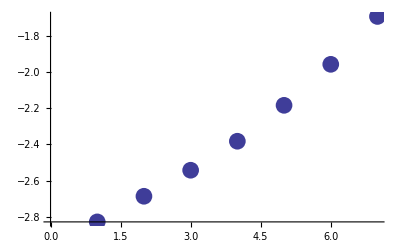

```mathematica
ListPlot[%,PlotStyle->PointSize[.03]]
```

```mathematica
fit=Fit[%%,{1,x},x]
```

-3.1+0.19 x

The expected behaviour is    a d^n   , for some small time a.

```mathematica
10^fit[[1]](10^fit[[2,1]])^n
```

0.0009 1.5^n

Let us now increase the dimension to 3:

```mathematica
CNumbersOf[polar,TangentM]^={1,2,3};
```

```mathematica
r1=Timing[Length[TraceBasisDummy[v[{a,polar}]v[{-a,-polar}]]]]
```

{0.00165,3}

```mathematica
r2=Timing[Length[TraceBasisDummy[v[{a,polar},{b,polar}]v[{-a,-polar},{-b,-polar}]]]]
```

{0.00221,9}

```mathematica
r3=Timing[Length[TraceBasisDummy[v[{a,polar},{b,polar},{c,polar}]v[{-a,-polar},{-b,-polar},{-c,-polar}]]]]
```

{0.00382,27}

```mathematica
r4=Timing[Length[TraceBasisDummy[v[{a,polar},{b,polar},{c,polar},{d,polar}]v[{-a,-polar},{-b,-polar},{-c,-polar},{-d,-polar}]]]]
```

{0.00821,81}

```mathematica
r5=Timing[Length[TraceBasisDummy[v[{a,polar},{b,polar},{c,polar},{d,polar},{e,polar}]v[{-a,-polar},{-b,-polar},{-c,-polar},{-d,-polar},{-e,-polar}]]]]
```

{0.02153,243}

```mathematica
r6=Timing[Length[TraceBasisDummy[v[{a,polar},{b,polar},{c,polar},{d,polar},{e,polar},{f,polar}]v[{-a,-polar},{-b,-polar},{-c,-polar},{-d,-polar},{-e,-polar},{-f,-polar}]]]]
```

{0.06695,729}

```mathematica
r7=Timing[Length[TraceBasisDummy[v[{a,polar},{b,polar},{c,polar},{d,polar},{e,polar},{f,polar},{g,polar}]v[{-a,-polar},{-b,-polar},{-c,-polar},{-d,-polar},{-e,-polar},{-f,-polar},{-g,-polar}]]]]
```

{0.21627,2187}

```mathematica
Log[10,First/@{r1,r2,r3,r4,r5,r6,r7}]
```

{-2.781,-2.655,-2.417,-2.086,-1.667,-1.1743,-0.66501}

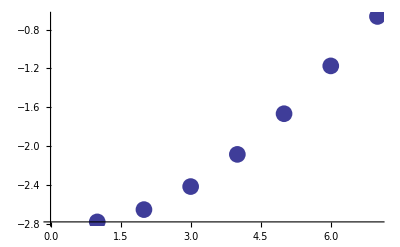

```mathematica
ListPlot[%,PlotStyle->PointSize[.03]]
```

```mathematica
fit=Fit[%%,{1,x},x]
```

-3.36+0.36 x

```mathematica
10^fit[[1]](10^fit[[2,1]])^n
```

0.00044 2.3^n

Let us now increase the dimension to 4:

```mathematica
CNumbersOf[polar,TangentM]^={1,2,3,4};
```

```mathematica
r1=Timing[Length[TraceBasisDummy[v[{a,polar}]v[{-a,-polar}]]]]
```

{0.00185,4}

```mathematica
r2=Timing[Length[TraceBasisDummy[v[{a,polar},{b,polar}]v[{-a,-polar},{-b,-polar}]]]]
```

{0.00253,16}

```mathematica
r3=Timing[Length[TraceBasisDummy[v[{a,polar},{b,polar},{c,polar}]v[{-a,-polar},{-b,-polar},{-c,-polar}]]]]
```

{0.00549,64}

```mathematica
r4=Timing[Length[TraceBasisDummy[v[{a,polar},{b,polar},{c,polar},{d,polar}]v[{-a,polar},{-b,-polar},{-c,-polar},{-d,-polar}]]]]
```

{0.00658,64}

```mathematica
r5=Timing[Length[TraceBasisDummy[v[{a,polar},{b,polar},{c,polar},{d,polar},{e,polar}]v[{-a,-polar},{-b,-polar},{-c,-polar},{-d,-polar},{-e,-polar}]]]]
```

{0.0727,1024}

```mathematica
r6=Timing[Length[TraceBasisDummy[v[{a,polar},{b,polar},{c,polar},{d,polar},{e,polar},{f,polar}]v[{-a,-polar},{-b,-polar},{-c,-polar},{-d,-polar},{-e,-polar},{-f,-polar}]]]]
```

{0.30783,4096}

```mathematica
r7=Timing[Length[TraceBasisDummy[v[{a,polar},{b,polar},{c,polar},{d,polar},{e,polar},{f,polar},{g,polar}]v[{-a,-polar},{-b,-polar},{-c,-polar},{-d,-polar},{-e,-polar},{-f,-polar},{-g,-polar}]]]]
```

{1.40063,16384}

```mathematica
Log[10,First/@{r1,r2,r3,r4,r5,r6,r7}]
```

{-2.734,-2.596,-2.26,-2.182,-1.1385,-0.51169,0.14632}

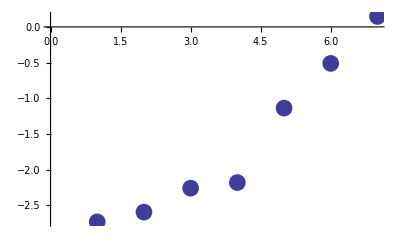

```mathematica
ListPlot[%,PlotStyle->PointSize[.03]]
```

```mathematica
fit=Fit[%%,{1,x},x]
```

-3.6+0.5 x

```mathematica
10^fit[[1]](10^fit[[2,1]])^n
```

0.00025 3.1^n

Let us now do it for dimension 5:

```mathematica
CNumbersOf[polar,TangentM]^={1,2,3,4,5};
```

```mathematica
r1=Timing[Length[TraceBasisDummy[v[{a,polar}]v[{-a,-polar}]]]]
```

{0.00163,5}

```mathematica
r2=Timing[Length[TraceBasisDummy[v[{a,polar},{b,polar}]v[{-a,-polar},{-b,-polar}]]]]
```

{0.00287,25}

```mathematica
r3=Timing[Length[TraceBasisDummy[v[{a,polar},{b,polar},{c,polar}]v[{-a,-polar},{-b,-polar},{-c,-polar}]]]]
```

{0.00803,125}

```mathematica
r4=Timing[Length[TraceBasisDummy[v[{a,polar},{b,polar},{c,polar},{d,polar}]v[{-a,-polar},{-b,-polar},{-c,-polar},{-d,-polar}]]]]
```

{0.03894,625}

```mathematica
r5=Timing[Length[TraceBasisDummy[v[{a,polar},{b,polar},{c,polar},{d,polar},{e,polar}]v[{-a,-polar},{-b,-polar},{-c,-polar},{-d,-polar},{-e,-polar}]]]]
```

{0.2025,3125}

```mathematica
r6=Timing[Length[TraceBasisDummy[v[{a,polar},{b,polar},{c,polar},{d,polar},{e,polar},{f,polar}]v[{-a,-polar},{-b,-polar},{-c,-polar},{-d,-polar},{-e,-polar},{-f,-polar}]]]]
```

{1.1374,15625}

```mathematica
r7=Timing[Length[TraceBasisDummy[v[{a,polar},{b,polar},{c,polar},{d,polar},{e,polar},{f,polar},{g,polar}]v[{-a,-polar},{-b,-polar},{-c,-polar},{-d,-polar},{-e,-polar},{-f,-polar},{-g,-polar}]]]]
```

{7.13965,78125}

```mathematica
Log[10,First/@{r1,r2,r3,r4,r5,r6,r7}]
```

{-2.787,-2.541,-2.095,-1.4096,-0.69357,0.055913,0.853677}

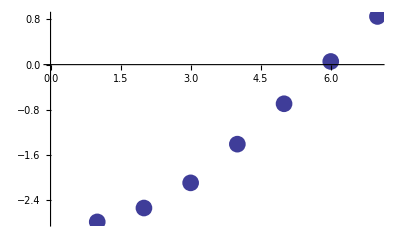

```mathematica
ListPlot[%,PlotStyle->PointSize[.03]]
```

```mathematica
fit=Fit[%%,{1,x},x]
```

-3.73+0.626 x

```mathematica
10^fit[[1]](10^fit[[2,1]])^n
```

0.00018 4.2^n

```mathematica
Remove[fit,r1,r2,r3,r4,r5,r6,r7,n,x]
```

Back to the original:

```mathematica
CNumbersOf[polar,TangentM]^={1,2}
```

{1,2}

```mathematica
UndefBasis[polar]
```

```mathematica
UndefTensor[v]
```

** UndefTensor: Undefined tensor v

```mathematica
EndExamples[]
```

There are new symbols in Global`:{Second,z$41053,z$41055,z$41056,z$41058,z$41059,z$41060,z$41062,z$41063,z$41064,z$41065,z$41068,z$41069,z$41070,z$41071,z$41072,z$41074,z$41075,z$41076,z$41077,z$41078,z$41079,z$41081,z$41082,z$41083,z$41084,z$41085,z$41086,z$41087,z$41138,z$41140,z$41141,z$41143,z$41144,z$41145,z$41148,z$41149,z$41150,z$41151,z$41153,z$41154,z$41155,z$41156,z$41157,z$41159,z$41160,z$41161,z$41162,z$41163,z$41164,z$41166,z$41167,z$41168,z$41169,z$41170,z$41171,z$41172,z$41198,z$41200,z$41201,z$41203,z$41204,z$41205,z$41207,z$41208,z$41209,z$41211,z$41212,z$41213,z$41214,z$41215,z$41217,z$41218,z$41219,z$41220,z$41221,z$41222,z$41224,z$41225,z$41226,z$41227,z$41228,z$41229,z$41230,z$41256,z$41258,z$41259,z$41261,z$41262,z$41263,z$41265,z$41266,z$41267,z$41268,z$41270,z$41271,z$41272,z$41273,z$41274,z$41277,z$41278,z$41279,z$41280,z$41281,z$41282,z$41285,z$41286,z$41287,z$41288,z$41289,z$41290,z$41291}

#### 3.2.3. BasisExpand

To understand this definition, see the diagram further down:

```mathematica
BasisExpand[expr_,basis_?BasisQ]:=TraceBasisDummy[SeparateBasis[basis][DummyToBasis[basis][expr]]];
BasisExpand[expr_,bases_List]:=Fold[BasisExpand,expr,bases];
SetNumberOfArguments[BasisExpand,2];
Protect[BasisExpand];
```

This function seems too silly at the moment, because it is just the combination of two main actions.

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefTensor[T[a,-b],M]
```

** DefTensor: Defining tensor T[a,-b].

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
BasisExpand[T[a,-b]T[b,c],polar]
```

e |   | a
1 |   e |   | c
1 |   T | 1 |  
  | 1 T | 1 | 1
  |  +e |   | a
1 |   e |   | c
2 |   T | 1 |  
  | 1 T | 1 | 2
  |  +e |   | c
1 |   e |   | a
2 |   T | 1 | 1
  |   T | 2 |  
  | 1+e |   | a
2 |   e |   | c
2 |   T | 1 | 2
  |   T | 2 |  
  | 1+e |   | a
1 |   e |   | c
1 |   T | 1 |  
  | 2 T | 2 | 1
  |  +e |   | c
1 |   e |   | a
2 |   T | 2 | 1
  |   T | 2 |  
  | 2+e |   | a
1 |   e |   | c
2 |   T | 1 |  
  | 2 T | 2 | 2
  |  +e |   | a
2 |   e |   | c
2 |   T | 2 |  
  | 2 T | 2 | 2
  |

```mathematica
BasisExpand[T[a,b]T[c,d],polar]
```

e |   | a
1 |   e |   | b
1 |   e |   | c
1 |   e |   | d
1 |   (T | 1 | 1
  |)^2+e |   | a
1 |   e |   | c
1 |   e |   | d
1 |   e |   | b
2 |   T | 1 | 1
  |   T | 1 | 2
  |  +e |   | a
1 |   e |   | b
1 |   e |   | c
1 |   e |   | d
2 |   T | 1 | 1
  |   T | 1 | 2
  |  +e |   | a
1 |   e |   | c
1 |   e |   | b
2 |   e |   | d
2 |   (T | 1 | 2
  |)^2+e |   | b
1 |   e |   | c
1 |   e |   | d
1 |   e |   | a
2 |   T | 1 | 1
  |   T | 2 | 1
  |  +e |   | a
1 |   e |   | b
1 |   e |   | d
1 |   e |   | c
2 |   T | 1 | 1
  |   T | 2 | 1
  |  +e |   | a
1 |   e |   | d
1 |   e |   | b
2 |   e |   | c
2 |   T | 1 | 2
  |   T | 2 | 1
  |  +e |   | b
1 |   e |   | c
1 |   e |   | a
2 |   e |   | d
2 |   T | 1 | 2
  |   T | 2 | 1
  |  +e |   | b
1 |   e |   | d
1 |   e |   | a
2 |   e |   | c
2 |   (T | 2 | 1
  |)^2+e |   | c
1 |   e |   | d
1 |   e |   | a
2 |   e |   | b
2 |   T | 1 | 1
  |   T | 2 | 2
  |  +e |   | a
1 |   e |   | b
1 |   e |   | c
2 |   e |   | d
2 |   T | 1 | 1
  |   T | 2 | 2
  |  +e |   | c
1 |   e |   | a
2 |   e |   | b
2 |   e |   | d
2 |   T | 1 | 2
  |   T | 2 | 2
  |  +e |   | a
1 |   e |   | b
2 |   e |   | c
2 |   e |   | d
2 |   T | 1 | 2
  |   T | 2 | 2
  |  +e |   | d
1 |   e |   | a
2 |   e |   | b
2 |   e |   | c
2 |   T | 2 | 1
  |   T | 2 | 2
  |  +e |   | b
1 |   e |   | a
2 |   e |   | c
2 |   e |   | d
2 |   T | 2 | 1
  |   T | 2 | 2
  |  +e |   | a
2 |   e |   | b
2 |   e |   | c
2 |   e |   | d
2 |   (T | 2 | 2
  |)^2

```mathematica
BasisExpand[T[a,-a],polar]
```

T | 1 |  
  | 1+T | 2 |  
  | 2

```mathematica
DefTensor[X[a,A],M,Dagger->Complex]
```

** DefTensor: Defining tensor X[a,A].

** DefTensor: Defining tensor X†[a,A†].

```mathematica
BasisExpand[X[a,A],polar]
```

e |   | a
1 |   X | 1 | A
  |  +e |   | a
2 |   X | 2 | A
  |

```mathematica
UndefTensor[X]
```

** UndefTensor: Undefined tensor X†

** UndefTensor: Undefined tensor X

```mathematica
UndefTensor[T]
```

** UndefTensor: Undefined tensor T

```mathematica
UndefBasis[polar]
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$41368,z$41369,z$41370,z$41372,z$41373,z$41374,z$41376,z$41377,z$41378,z$41379,z$41381,z$41382,z$41383,z$41384,z$41385,z$41387,z$41396,z$41398}

### 3.3. Arrays of components

We give commands transforming **free** BIndices (or free AIndices through the use of ToBasis) into collections of CIndices.

#### 3.3.0. Comments

In this section we want to construct a series of commands in charge of generating particular (usually all) components of a given expression.

The most important problem at this point is the manipulation of derivatives. This is because we know that the components of a derivative are not necessarily the derivative of the components, and so the construction of components must be done carefully. That is, the transformation from AIndices to CIndices must be thought of in two steps: we first change from AIndices to BIndices (using *ToBasis functions) and then from BIndices to CIndices. The problem with the derivatives is in the first step, and not in the second.

NOTE: Currently there is no function to construct a single component, because the notation must be nearly as long as the direct construction itself! Coba can be used to do that, in case the same component must be constructed for several different tensors.

#### Examples of component generation

We want to generate an array of all components of an expression. There are several ways to do it.

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
DefBasis[cartesian,TangentM,{1,2},BasisColor->RGBColor[0,0,1],DefInfo->False]
```

```mathematica
DefTensor[v[a],M]
```

** DefTensor: Defining tensor v[a].

1) We can use SplitIndex, which is quite fast, already starting from b-indices:

Very simple notation:

```mathematica
SplitIndex[v[{a,polar}],a->IndexList[1,2,3,4]]//AbsoluteTiming
```

{0.00038,{v | 1
 ,v | 2
 ,v | 3
 ,v | 4
 }}

```mathematica
SplitIndex[v[{a,polar},{b,polar},{c,polar},{d,polar}],IndexList[a,b,c,d]->IndexList[1,2,3,4]]//AbsoluteTiming
```

{0.00255,{{{{v | 1 | 1 | 1 | 1
  |   |   |  ,v | 1 | 1 | 1 | 2
  |   |   |  ,v | 1 | 1 | 1 | 3
  |   |   |  ,v | 1 | 1 | 1 | 4
  |   |   |  },{v | 1 | 1 | 2 | 1
  |   |   |  ,v | 1 | 1 | 2 | 2
  |   |   |  ,v | 1 | 1 | 2 | 3
  |   |   |  ,v | 1 | 1 | 2 | 4
  |   |   |  },{v | 1 | 1 | 3 | 1
  |   |   |  ,v | 1 | 1 | 3 | 2
  |   |   |  ,v | 1 | 1 | 3 | 3
  |   |   |  ,v | 1 | 1 | 3 | 4
  |   |   |  },{v | 1 | 1 | 4 | 1
  |   |   |  ,v | 1 | 1 | 4 | 2
  |   |   |  ,v | 1 | 1 | 4 | 3
  |   |   |  ,v | 1 | 1 | 4 | 4
  |   |   |  }},{{v | 1 | 2 | 1 | 1
  |   |   |  ,v | 1 | 2 | 1 | 2
  |   |   |  ,v | 1 | 2 | 1 | 3
  |   |   |  ,v | 1 | 2 | 1 | 4
  |   |   |  },{v | 1 | 2 | 2 | 1
  |   |   |  ,v | 1 | 2 | 2 | 2
  |   |   |  ,v | 1 | 2 | 2 | 3
  |   |   |  ,v | 1 | 2 | 2 | 4
  |   |   |  },{v | 1 | 2 | 3 | 1
  |   |   |  ,v | 1 | 2 | 3 | 2
  |   |   |  ,v | 1 | 2 | 3 | 3
  |   |   |  ,v | 1 | 2 | 3 | 4
  |   |   |  },{v | 1 | 2 | 4 | 1
  |   |   |  ,v | 1 | 2 | 4 | 2
  |   |   |  ,v | 1 | 2 | 4 | 3
  |   |   |  ,v | 1 | 2 | 4 | 4
  |   |   |  }},{{v | 1 | 3 | 1 | 1
  |   |   |  ,v | 1 | 3 | 1 | 2
  |   |   |  ,v | 1 | 3 | 1 | 3
  |   |   |  ,v | 1 | 3 | 1 | 4
  |   |   |  },{v | 1 | 3 | 2 | 1
  |   |   |  ,v | 1 | 3 | 2 | 2
  |   |   |  ,v | 1 | 3 | 2 | 3
  |   |   |  ,v | 1 | 3 | 2 | 4
  |   |   |  },{v | 1 | 3 | 3 | 1
  |   |   |  ,v | 1 | 3 | 3 | 2
  |   |   |  ,v | 1 | 3 | 3 | 3
  |   |   |  ,v | 1 | 3 | 3 | 4
  |   |   |  },{v | 1 | 3 | 4 | 1
  |   |   |  ,v | 1 | 3 | 4 | 2
  |   |   |  ,v | 1 | 3 | 4 | 3
  |   |   |  ,v | 1 | 3 | 4 | 4
  |   |   |  }},{{v | 1 | 4 | 1 | 1
  |   |   |  ,v | 1 | 4 | 1 | 2
  |   |   |  ,v | 1 | 4 | 1 | 3
  |   |   |  ,v | 1 | 4 | 1 | 4
  |   |   |  },{v | 1 | 4 | 2 | 1
  |   |   |  ,v | 1 | 4 | 2 | 2
  |   |   |  ,v | 1 | 4 | 2 | 3
  |   |   |  ,v | 1 | 4 | 2 | 4
  |   |   |  },{v | 1 | 4 | 3 | 1
  |   |   |  ,v | 1 | 4 | 3 | 2
  |   |   |  ,v | 1 | 4 | 3 | 3
  |   |   |  ,v | 1 | 4 | 3 | 4
  |   |   |  },{v | 1 | 4 | 4 | 1
  |   |   |  ,v | 1 | 4 | 4 | 2
  |   |   |  ,v | 1 | 4 | 4 | 3
  |   |   |  ,v | 1 | 4 | 4 | 4
  |   |   |  }}},{{{v | 2 | 1 | 1 | 1
  |   |   |  ,v | 2 | 1 | 1 | 2
  |   |   |  ,v | 2 | 1 | 1 | 3
  |   |   |  ,v | 2 | 1 | 1 | 4
  |   |   |  },{v | 2 | 1 | 2 | 1
  |   |   |  ,v | 2 | 1 | 2 | 2
  |   |   |  ,v | 2 | 1 | 2 | 3
  |   |   |  ,v | 2 | 1 | 2 | 4
  |   |   |  },{v | 2 | 1 | 3 | 1
  |   |   |  ,v | 2 | 1 | 3 | 2
  |   |   |  ,v | 2 | 1 | 3 | 3
  |   |   |  ,v | 2 | 1 | 3 | 4
  |   |   |  },{v | 2 | 1 | 4 | 1
  |   |   |  ,v | 2 | 1 | 4 | 2
  |   |   |  ,v | 2 | 1 | 4 | 3
  |   |   |  ,v | 2 | 1 | 4 | 4
  |   |   |  }},{{v | 2 | 2 | 1 | 1
  |   |   |  ,v | 2 | 2 | 1 | 2
  |   |   |  ,v | 2 | 2 | 1 | 3
  |   |   |  ,v | 2 | 2 | 1 | 4
  |   |   |  },{v | 2 | 2 | 2 | 1
  |   |   |  ,v | 2 | 2 | 2 | 2
  |   |   |  ,v | 2 | 2 | 2 | 3
  |   |   |  ,v | 2 | 2 | 2 | 4
  |   |   |  },{v | 2 | 2 | 3 | 1
  |   |   |  ,v | 2 | 2 | 3 | 2
  |   |   |  ,v | 2 | 2 | 3 | 3
  |   |   |  ,v | 2 | 2 | 3 | 4
  |   |   |  },{v | 2 | 2 | 4 | 1
  |   |   |  ,v | 2 | 2 | 4 | 2
  |   |   |  ,v | 2 | 2 | 4 | 3
  |   |   |  ,v | 2 | 2 | 4 | 4
  |   |   |  }},{{v | 2 | 3 | 1 | 1
  |   |   |  ,v | 2 | 3 | 1 | 2
  |   |   |  ,v | 2 | 3 | 1 | 3
  |   |   |  ,v | 2 | 3 | 1 | 4
  |   |   |  },{v | 2 | 3 | 2 | 1
  |   |   |  ,v | 2 | 3 | 2 | 2
  |   |   |  ,v | 2 | 3 | 2 | 3
  |   |   |  ,v | 2 | 3 | 2 | 4
  |   |   |  },{v | 2 | 3 | 3 | 1
  |   |   |  ,v | 2 | 3 | 3 | 2
  |   |   |  ,v | 2 | 3 | 3 | 3
  |   |   |  ,v | 2 | 3 | 3 | 4
  |   |   |  },{v | 2 | 3 | 4 | 1
  |   |   |  ,v | 2 | 3 | 4 | 2
  |   |   |  ,v | 2 | 3 | 4 | 3
  |   |   |  ,v | 2 | 3 | 4 | 4
  |   |   |  }},{{v | 2 | 4 | 1 | 1
  |   |   |  ,v | 2 | 4 | 1 | 2
  |   |   |  ,v | 2 | 4 | 1 | 3
  |   |   |  ,v | 2 | 4 | 1 | 4
  |   |   |  },{v | 2 | 4 | 2 | 1
  |   |   |  ,v | 2 | 4 | 2 | 2
  |   |   |  ,v | 2 | 4 | 2 | 3
  |   |   |  ,v | 2 | 4 | 2 | 4
  |   |   |  },{v | 2 | 4 | 3 | 1
  |   |   |  ,v | 2 | 4 | 3 | 2
  |   |   |  ,v | 2 | 4 | 3 | 3
  |   |   |  ,v | 2 | 4 | 3 | 4
  |   |   |  },{v | 2 | 4 | 4 | 1
  |   |   |  ,v | 2 | 4 | 4 | 2
  |   |   |  ,v | 2 | 4 | 4 | 3
  |   |   |  ,v | 2 | 4 | 4 | 4
  |   |   |  }}},{{{v | 3 | 1 | 1 | 1
  |   |   |  ,v | 3 | 1 | 1 | 2
  |   |   |  ,v | 3 | 1 | 1 | 3
  |   |   |  ,v | 3 | 1 | 1 | 4
  |   |   |  },{v | 3 | 1 | 2 | 1
  |   |   |  ,v | 3 | 1 | 2 | 2
  |   |   |  ,v | 3 | 1 | 2 | 3
  |   |   |  ,v | 3 | 1 | 2 | 4
  |   |   |  },{v | 3 | 1 | 3 | 1
  |   |   |  ,v | 3 | 1 | 3 | 2
  |   |   |  ,v | 3 | 1 | 3 | 3
  |   |   |  ,v | 3 | 1 | 3 | 4
  |   |   |  },{v | 3 | 1 | 4 | 1
  |   |   |  ,v | 3 | 1 | 4 | 2
  |   |   |  ,v | 3 | 1 | 4 | 3
  |   |   |  ,v | 3 | 1 | 4 | 4
  |   |   |  }},{{v | 3 | 2 | 1 | 1
  |   |   |  ,v | 3 | 2 | 1 | 2
  |   |   |  ,v | 3 | 2 | 1 | 3
  |   |   |  ,v | 3 | 2 | 1 | 4
  |   |   |  },{v | 3 | 2 | 2 | 1
  |   |   |  ,v | 3 | 2 | 2 | 2
  |   |   |  ,v | 3 | 2 | 2 | 3
  |   |   |  ,v | 3 | 2 | 2 | 4
  |   |   |  },{v | 3 | 2 | 3 | 1
  |   |   |  ,v | 3 | 2 | 3 | 2
  |   |   |  ,v | 3 | 2 | 3 | 3
  |   |   |  ,v | 3 | 2 | 3 | 4
  |   |   |  },{v | 3 | 2 | 4 | 1
  |   |   |  ,v | 3 | 2 | 4 | 2
  |   |   |  ,v | 3 | 2 | 4 | 3
  |   |   |  ,v | 3 | 2 | 4 | 4
  |   |   |  }},{{v | 3 | 3 | 1 | 1
  |   |   |  ,v | 3 | 3 | 1 | 2
  |   |   |  ,v | 3 | 3 | 1 | 3
  |   |   |  ,v | 3 | 3 | 1 | 4
  |   |   |  },{v | 3 | 3 | 2 | 1
  |   |   |  ,v | 3 | 3 | 2 | 2
  |   |   |  ,v | 3 | 3 | 2 | 3
  |   |   |  ,v | 3 | 3 | 2 | 4
  |   |   |  },{v | 3 | 3 | 3 | 1
  |   |   |  ,v | 3 | 3 | 3 | 2
  |   |   |  ,v | 3 | 3 | 3 | 3
  |   |   |  ,v | 3 | 3 | 3 | 4
  |   |   |  },{v | 3 | 3 | 4 | 1
  |   |   |  ,v | 3 | 3 | 4 | 2
  |   |   |  ,v | 3 | 3 | 4 | 3
  |   |   |  ,v | 3 | 3 | 4 | 4
  |   |   |  }},{{v | 3 | 4 | 1 | 1
  |   |   |  ,v | 3 | 4 | 1 | 2
  |   |   |  ,v | 3 | 4 | 1 | 3
  |   |   |  ,v | 3 | 4 | 1 | 4
  |   |   |  },{v | 3 | 4 | 2 | 1
  |   |   |  ,v | 3 | 4 | 2 | 2
  |   |   |  ,v | 3 | 4 | 2 | 3
  |   |   |  ,v | 3 | 4 | 2 | 4
  |   |   |  },{v | 3 | 4 | 3 | 1
  |   |   |  ,v | 3 | 4 | 3 | 2
  |   |   |  ,v | 3 | 4 | 3 | 3
  |   |   |  ,v | 3 | 4 | 3 | 4
  |   |   |  },{v | 3 | 4 | 4 | 1
  |   |   |  ,v | 3 | 4 | 4 | 2
  |   |   |  ,v | 3 | 4 | 4 | 3
  |   |   |  ,v | 3 | 4 | 4 | 4
  |   |   |  }}},{{{v | 4 | 1 | 1 | 1
  |   |   |  ,v | 4 | 1 | 1 | 2
  |   |   |  ,v | 4 | 1 | 1 | 3
  |   |   |  ,v | 4 | 1 | 1 | 4
  |   |   |  },{v | 4 | 1 | 2 | 1
  |   |   |  ,v | 4 | 1 | 2 | 2
  |   |   |  ,v | 4 | 1 | 2 | 3
  |   |   |  ,v | 4 | 1 | 2 | 4
  |   |   |  },{v | 4 | 1 | 3 | 1
  |   |   |  ,v | 4 | 1 | 3 | 2
  |   |   |  ,v | 4 | 1 | 3 | 3
  |   |   |  ,v | 4 | 1 | 3 | 4
  |   |   |  },{v | 4 | 1 | 4 | 1
  |   |   |  ,v | 4 | 1 | 4 | 2
  |   |   |  ,v | 4 | 1 | 4 | 3
  |   |   |  ,v | 4 | 1 | 4 | 4
  |   |   |  }},{{v | 4 | 2 | 1 | 1
  |   |   |  ,v | 4 | 2 | 1 | 2
  |   |   |  ,v | 4 | 2 | 1 | 3
  |   |   |  ,v | 4 | 2 | 1 | 4
  |   |   |  },{v | 4 | 2 | 2 | 1
  |   |   |  ,v | 4 | 2 | 2 | 2
  |   |   |  ,v | 4 | 2 | 2 | 3
  |   |   |  ,v | 4 | 2 | 2 | 4
  |   |   |  },{v | 4 | 2 | 3 | 1
  |   |   |  ,v | 4 | 2 | 3 | 2
  |   |   |  ,v | 4 | 2 | 3 | 3
  |   |   |  ,v | 4 | 2 | 3 | 4
  |   |   |  },{v | 4 | 2 | 4 | 1
  |   |   |  ,v | 4 | 2 | 4 | 2
  |   |   |  ,v | 4 | 2 | 4 | 3
  |   |   |  ,v | 4 | 2 | 4 | 4
  |   |   |  }},{{v | 4 | 3 | 1 | 1
  |   |   |  ,v | 4 | 3 | 1 | 2
  |   |   |  ,v | 4 | 3 | 1 | 3
  |   |   |  ,v | 4 | 3 | 1 | 4
  |   |   |  },{v | 4 | 3 | 2 | 1
  |   |   |  ,v | 4 | 3 | 2 | 2
  |   |   |  ,v | 4 | 3 | 2 | 3
  |   |   |  ,v | 4 | 3 | 2 | 4
  |   |   |  },{v | 4 | 3 | 3 | 1
  |   |   |  ,v | 4 | 3 | 3 | 2
  |   |   |  ,v | 4 | 3 | 3 | 3
  |   |   |  ,v | 4 | 3 | 3 | 4
  |   |   |  },{v | 4 | 3 | 4 | 1
  |   |   |  ,v | 4 | 3 | 4 | 2
  |   |   |  ,v | 4 | 3 | 4 | 3
  |   |   |  ,v | 4 | 3 | 4 | 4
  |   |   |  }},{{v | 4 | 4 | 1 | 1
  |   |   |  ,v | 4 | 4 | 1 | 2
  |   |   |  ,v | 4 | 4 | 1 | 3
  |   |   |  ,v | 4 | 4 | 1 | 4
  |   |   |  },{v | 4 | 4 | 2 | 1
  |   |   |  ,v | 4 | 4 | 2 | 2
  |   |   |  ,v | 4 | 4 | 2 | 3
  |   |   |  ,v | 4 | 4 | 2 | 4
  |   |   |  },{v | 4 | 4 | 3 | 1
  |   |   |  ,v | 4 | 4 | 3 | 2
  |   |   |  ,v | 4 | 4 | 3 | 3
  |   |   |  ,v | 4 | 4 | 3 | 4
  |   |   |  },{v | 4 | 4 | 4 | 1
  |   |   |  ,v | 4 | 4 | 4 | 2
  |   |   |  ,v | 4 | 4 | 4 | 3
  |   |   |  ,v | 4 | 4 | 4 | 4
  |   |   |  }}}}}

or

```mathematica
SplitIndex[v[{a,polar}],{a,polar}->IndexList[{1,polar},{2,polar},{3,polar},{4,polar}]]//AbsoluteTiming
```

{0.00037,{v | 1
 ,v | 2
 ,v | 3
 ,v | 4
 }}

```mathematica
SplitIndex[v[{a,polar},{b,polar},{c,polar},{d,polar}],IndexList[{a,polar},{b,polar},{c,polar},{d,polar}]->IndexList[{1,polar},{2,polar},{3,polar},{4,polar}]]//AbsoluteTiming
```

{0.00285,{{{{v | 1 | 1 | 1 | 1
  |   |   |  ,v | 1 | 1 | 1 | 2
  |   |   |  ,v | 1 | 1 | 1 | 3
  |   |   |  ,v | 1 | 1 | 1 | 4
  |   |   |  },{v | 1 | 1 | 2 | 1
  |   |   |  ,v | 1 | 1 | 2 | 2
  |   |   |  ,v | 1 | 1 | 2 | 3
  |   |   |  ,v | 1 | 1 | 2 | 4
  |   |   |  },{v | 1 | 1 | 3 | 1
  |   |   |  ,v | 1 | 1 | 3 | 2
  |   |   |  ,v | 1 | 1 | 3 | 3
  |   |   |  ,v | 1 | 1 | 3 | 4
  |   |   |  },{v | 1 | 1 | 4 | 1
  |   |   |  ,v | 1 | 1 | 4 | 2
  |   |   |  ,v | 1 | 1 | 4 | 3
  |   |   |  ,v | 1 | 1 | 4 | 4
  |   |   |  }},{{v | 1 | 2 | 1 | 1
  |   |   |  ,v | 1 | 2 | 1 | 2
  |   |   |  ,v | 1 | 2 | 1 | 3
  |   |   |  ,v | 1 | 2 | 1 | 4
  |   |   |  },{v | 1 | 2 | 2 | 1
  |   |   |  ,v | 1 | 2 | 2 | 2
  |   |   |  ,v | 1 | 2 | 2 | 3
  |   |   |  ,v | 1 | 2 | 2 | 4
  |   |   |  },{v | 1 | 2 | 3 | 1
  |   |   |  ,v | 1 | 2 | 3 | 2
  |   |   |  ,v | 1 | 2 | 3 | 3
  |   |   |  ,v | 1 | 2 | 3 | 4
  |   |   |  },{v | 1 | 2 | 4 | 1
  |   |   |  ,v | 1 | 2 | 4 | 2
  |   |   |  ,v | 1 | 2 | 4 | 3
  |   |   |  ,v | 1 | 2 | 4 | 4
  |   |   |  }},{{v | 1 | 3 | 1 | 1
  |   |   |  ,v | 1 | 3 | 1 | 2
  |   |   |  ,v | 1 | 3 | 1 | 3
  |   |   |  ,v | 1 | 3 | 1 | 4
  |   |   |  },{v | 1 | 3 | 2 | 1
  |   |   |  ,v | 1 | 3 | 2 | 2
  |   |   |  ,v | 1 | 3 | 2 | 3
  |   |   |  ,v | 1 | 3 | 2 | 4
  |   |   |  },{v | 1 | 3 | 3 | 1
  |   |   |  ,v | 1 | 3 | 3 | 2
  |   |   |  ,v | 1 | 3 | 3 | 3
  |   |   |  ,v | 1 | 3 | 3 | 4
  |   |   |  },{v | 1 | 3 | 4 | 1
  |   |   |  ,v | 1 | 3 | 4 | 2
  |   |   |  ,v | 1 | 3 | 4 | 3
  |   |   |  ,v | 1 | 3 | 4 | 4
  |   |   |  }},{{v | 1 | 4 | 1 | 1
  |   |   |  ,v | 1 | 4 | 1 | 2
  |   |   |  ,v | 1 | 4 | 1 | 3
  |   |   |  ,v | 1 | 4 | 1 | 4
  |   |   |  },{v | 1 | 4 | 2 | 1
  |   |   |  ,v | 1 | 4 | 2 | 2
  |   |   |  ,v | 1 | 4 | 2 | 3
  |   |   |  ,v | 1 | 4 | 2 | 4
  |   |   |  },{v | 1 | 4 | 3 | 1
  |   |   |  ,v | 1 | 4 | 3 | 2
  |   |   |  ,v | 1 | 4 | 3 | 3
  |   |   |  ,v | 1 | 4 | 3 | 4
  |   |   |  },{v | 1 | 4 | 4 | 1
  |   |   |  ,v | 1 | 4 | 4 | 2
  |   |   |  ,v | 1 | 4 | 4 | 3
  |   |   |  ,v | 1 | 4 | 4 | 4
  |   |   |  }}},{{{v | 2 | 1 | 1 | 1
  |   |   |  ,v | 2 | 1 | 1 | 2
  |   |   |  ,v | 2 | 1 | 1 | 3
  |   |   |  ,v | 2 | 1 | 1 | 4
  |   |   |  },{v | 2 | 1 | 2 | 1
  |   |   |  ,v | 2 | 1 | 2 | 2
  |   |   |  ,v | 2 | 1 | 2 | 3
  |   |   |  ,v | 2 | 1 | 2 | 4
  |   |   |  },{v | 2 | 1 | 3 | 1
  |   |   |  ,v | 2 | 1 | 3 | 2
  |   |   |  ,v | 2 | 1 | 3 | 3
  |   |   |  ,v | 2 | 1 | 3 | 4
  |   |   |  },{v | 2 | 1 | 4 | 1
  |   |   |  ,v | 2 | 1 | 4 | 2
  |   |   |  ,v | 2 | 1 | 4 | 3
  |   |   |  ,v | 2 | 1 | 4 | 4
  |   |   |  }},{{v | 2 | 2 | 1 | 1
  |   |   |  ,v | 2 | 2 | 1 | 2
  |   |   |  ,v | 2 | 2 | 1 | 3
  |   |   |  ,v | 2 | 2 | 1 | 4
  |   |   |  },{v | 2 | 2 | 2 | 1
  |   |   |  ,v | 2 | 2 | 2 | 2
  |   |   |  ,v | 2 | 2 | 2 | 3
  |   |   |  ,v | 2 | 2 | 2 | 4
  |   |   |  },{v | 2 | 2 | 3 | 1
  |   |   |  ,v | 2 | 2 | 3 | 2
  |   |   |  ,v | 2 | 2 | 3 | 3
  |   |   |  ,v | 2 | 2 | 3 | 4
  |   |   |  },{v | 2 | 2 | 4 | 1
  |   |   |  ,v | 2 | 2 | 4 | 2
  |   |   |  ,v | 2 | 2 | 4 | 3
  |   |   |  ,v | 2 | 2 | 4 | 4
  |   |   |  }},{{v | 2 | 3 | 1 | 1
  |   |   |  ,v | 2 | 3 | 1 | 2
  |   |   |  ,v | 2 | 3 | 1 | 3
  |   |   |  ,v | 2 | 3 | 1 | 4
  |   |   |  },{v | 2 | 3 | 2 | 1
  |   |   |  ,v | 2 | 3 | 2 | 2
  |   |   |  ,v | 2 | 3 | 2 | 3
  |   |   |  ,v | 2 | 3 | 2 | 4
  |   |   |  },{v | 2 | 3 | 3 | 1
  |   |   |  ,v | 2 | 3 | 3 | 2
  |   |   |  ,v | 2 | 3 | 3 | 3
  |   |   |  ,v | 2 | 3 | 3 | 4
  |   |   |  },{v | 2 | 3 | 4 | 1
  |   |   |  ,v | 2 | 3 | 4 | 2
  |   |   |  ,v | 2 | 3 | 4 | 3
  |   |   |  ,v | 2 | 3 | 4 | 4
  |   |   |  }},{{v | 2 | 4 | 1 | 1
  |   |   |  ,v | 2 | 4 | 1 | 2
  |   |   |  ,v | 2 | 4 | 1 | 3
  |   |   |  ,v | 2 | 4 | 1 | 4
  |   |   |  },{v | 2 | 4 | 2 | 1
  |   |   |  ,v | 2 | 4 | 2 | 2
  |   |   |  ,v | 2 | 4 | 2 | 3
  |   |   |  ,v | 2 | 4 | 2 | 4
  |   |   |  },{v | 2 | 4 | 3 | 1
  |   |   |  ,v | 2 | 4 | 3 | 2
  |   |   |  ,v | 2 | 4 | 3 | 3
  |   |   |  ,v | 2 | 4 | 3 | 4
  |   |   |  },{v | 2 | 4 | 4 | 1
  |   |   |  ,v | 2 | 4 | 4 | 2
  |   |   |  ,v | 2 | 4 | 4 | 3
  |   |   |  ,v | 2 | 4 | 4 | 4
  |   |   |  }}},{{{v | 3 | 1 | 1 | 1
  |   |   |  ,v | 3 | 1 | 1 | 2
  |   |   |  ,v | 3 | 1 | 1 | 3
  |   |   |  ,v | 3 | 1 | 1 | 4
  |   |   |  },{v | 3 | 1 | 2 | 1
  |   |   |  ,v | 3 | 1 | 2 | 2
  |   |   |  ,v | 3 | 1 | 2 | 3
  |   |   |  ,v | 3 | 1 | 2 | 4
  |   |   |  },{v | 3 | 1 | 3 | 1
  |   |   |  ,v | 3 | 1 | 3 | 2
  |   |   |  ,v | 3 | 1 | 3 | 3
  |   |   |  ,v | 3 | 1 | 3 | 4
  |   |   |  },{v | 3 | 1 | 4 | 1
  |   |   |  ,v | 3 | 1 | 4 | 2
  |   |   |  ,v | 3 | 1 | 4 | 3
  |   |   |  ,v | 3 | 1 | 4 | 4
  |   |   |  }},{{v | 3 | 2 | 1 | 1
  |   |   |  ,v | 3 | 2 | 1 | 2
  |   |   |  ,v | 3 | 2 | 1 | 3
  |   |   |  ,v | 3 | 2 | 1 | 4
  |   |   |  },{v | 3 | 2 | 2 | 1
  |   |   |  ,v | 3 | 2 | 2 | 2
  |   |   |  ,v | 3 | 2 | 2 | 3
  |   |   |  ,v | 3 | 2 | 2 | 4
  |   |   |  },{v | 3 | 2 | 3 | 1
  |   |   |  ,v | 3 | 2 | 3 | 2
  |   |   |  ,v | 3 | 2 | 3 | 3
  |   |   |  ,v | 3 | 2 | 3 | 4
  |   |   |  },{v | 3 | 2 | 4 | 1
  |   |   |  ,v | 3 | 2 | 4 | 2
  |   |   |  ,v | 3 | 2 | 4 | 3
  |   |   |  ,v | 3 | 2 | 4 | 4
  |   |   |  }},{{v | 3 | 3 | 1 | 1
  |   |   |  ,v | 3 | 3 | 1 | 2
  |   |   |  ,v | 3 | 3 | 1 | 3
  |   |   |  ,v | 3 | 3 | 1 | 4
  |   |   |  },{v | 3 | 3 | 2 | 1
  |   |   |  ,v | 3 | 3 | 2 | 2
  |   |   |  ,v | 3 | 3 | 2 | 3
  |   |   |  ,v | 3 | 3 | 2 | 4
  |   |   |  },{v | 3 | 3 | 3 | 1
  |   |   |  ,v | 3 | 3 | 3 | 2
  |   |   |  ,v | 3 | 3 | 3 | 3
  |   |   |  ,v | 3 | 3 | 3 | 4
  |   |   |  },{v | 3 | 3 | 4 | 1
  |   |   |  ,v | 3 | 3 | 4 | 2
  |   |   |  ,v | 3 | 3 | 4 | 3
  |   |   |  ,v | 3 | 3 | 4 | 4
  |   |   |  }},{{v | 3 | 4 | 1 | 1
  |   |   |  ,v | 3 | 4 | 1 | 2
  |   |   |  ,v | 3 | 4 | 1 | 3
  |   |   |  ,v | 3 | 4 | 1 | 4
  |   |   |  },{v | 3 | 4 | 2 | 1
  |   |   |  ,v | 3 | 4 | 2 | 2
  |   |   |  ,v | 3 | 4 | 2 | 3
  |   |   |  ,v | 3 | 4 | 2 | 4
  |   |   |  },{v | 3 | 4 | 3 | 1
  |   |   |  ,v | 3 | 4 | 3 | 2
  |   |   |  ,v | 3 | 4 | 3 | 3
  |   |   |  ,v | 3 | 4 | 3 | 4
  |   |   |  },{v | 3 | 4 | 4 | 1
  |   |   |  ,v | 3 | 4 | 4 | 2
  |   |   |  ,v | 3 | 4 | 4 | 3
  |   |   |  ,v | 3 | 4 | 4 | 4
  |   |   |  }}},{{{v | 4 | 1 | 1 | 1
  |   |   |  ,v | 4 | 1 | 1 | 2
  |   |   |  ,v | 4 | 1 | 1 | 3
  |   |   |  ,v | 4 | 1 | 1 | 4
  |   |   |  },{v | 4 | 1 | 2 | 1
  |   |   |  ,v | 4 | 1 | 2 | 2
  |   |   |  ,v | 4 | 1 | 2 | 3
  |   |   |  ,v | 4 | 1 | 2 | 4
  |   |   |  },{v | 4 | 1 | 3 | 1
  |   |   |  ,v | 4 | 1 | 3 | 2
  |   |   |  ,v | 4 | 1 | 3 | 3
  |   |   |  ,v | 4 | 1 | 3 | 4
  |   |   |  },{v | 4 | 1 | 4 | 1
  |   |   |  ,v | 4 | 1 | 4 | 2
  |   |   |  ,v | 4 | 1 | 4 | 3
  |   |   |  ,v | 4 | 1 | 4 | 4
  |   |   |  }},{{v | 4 | 2 | 1 | 1
  |   |   |  ,v | 4 | 2 | 1 | 2
  |   |   |  ,v | 4 | 2 | 1 | 3
  |   |   |  ,v | 4 | 2 | 1 | 4
  |   |   |  },{v | 4 | 2 | 2 | 1
  |   |   |  ,v | 4 | 2 | 2 | 2
  |   |   |  ,v | 4 | 2 | 2 | 3
  |   |   |  ,v | 4 | 2 | 2 | 4
  |   |   |  },{v | 4 | 2 | 3 | 1
  |   |   |  ,v | 4 | 2 | 3 | 2
  |   |   |  ,v | 4 | 2 | 3 | 3
  |   |   |  ,v | 4 | 2 | 3 | 4
  |   |   |  },{v | 4 | 2 | 4 | 1
  |   |   |  ,v | 4 | 2 | 4 | 2
  |   |   |  ,v | 4 | 2 | 4 | 3
  |   |   |  ,v | 4 | 2 | 4 | 4
  |   |   |  }},{{v | 4 | 3 | 1 | 1
  |   |   |  ,v | 4 | 3 | 1 | 2
  |   |   |  ,v | 4 | 3 | 1 | 3
  |   |   |  ,v | 4 | 3 | 1 | 4
  |   |   |  },{v | 4 | 3 | 2 | 1
  |   |   |  ,v | 4 | 3 | 2 | 2
  |   |   |  ,v | 4 | 3 | 2 | 3
  |   |   |  ,v | 4 | 3 | 2 | 4
  |   |   |  },{v | 4 | 3 | 3 | 1
  |   |   |  ,v | 4 | 3 | 3 | 2
  |   |   |  ,v | 4 | 3 | 3 | 3
  |   |   |  ,v | 4 | 3 | 3 | 4
  |   |   |  },{v | 4 | 3 | 4 | 1
  |   |   |  ,v | 4 | 3 | 4 | 2
  |   |   |  ,v | 4 | 3 | 4 | 3
  |   |   |  ,v | 4 | 3 | 4 | 4
  |   |   |  }},{{v | 4 | 4 | 1 | 1
  |   |   |  ,v | 4 | 4 | 1 | 2
  |   |   |  ,v | 4 | 4 | 1 | 3
  |   |   |  ,v | 4 | 4 | 1 | 4
  |   |   |  },{v | 4 | 4 | 2 | 1
  |   |   |  ,v | 4 | 4 | 2 | 2
  |   |   |  ,v | 4 | 4 | 2 | 3
  |   |   |  ,v | 4 | 4 | 2 | 4
  |   |   |  },{v | 4 | 4 | 3 | 1
  |   |   |  ,v | 4 | 4 | 3 | 2
  |   |   |  ,v | 4 | 4 | 3 | 3
  |   |   |  ,v | 4 | 4 | 3 | 4
  |   |   |  },{v | 4 | 4 | 4 | 1
  |   |   |  ,v | 4 | 4 | 4 | 2
  |   |   |  ,v | 4 | 4 | 4 | 3
  |   |   |  ,v | 4 | 4 | 4 | 4
  |   |   |  }}}}}

Note that the former allows things like (note the positions of the signs!)

```mathematica
SplitIndex[v[{a,polar},{-b,-polar},{c,cartesian},{-d,-cartesian}],IndexList[a,-b,c,-d]->IndexList[1,2,3,4]]//AbsoluteTiming
```

{0.00362,{{{{v | 1 |   | 1 |  
  | 1 |   | 1,v | 1 |   | 1 |  
  | 1 |   | 2,v | 1 |   | 1 |  
  | 1 |   | 3,v | 1 |   | 1 |  
  | 1 |   | 4},{v | 1 |   | 2 |  
  | 1 |   | 1,v | 1 |   | 2 |  
  | 1 |   | 2,v | 1 |   | 2 |  
  | 1 |   | 3,v | 1 |   | 2 |  
  | 1 |   | 4},{v | 1 |   | 3 |  
  | 1 |   | 1,v | 1 |   | 3 |  
  | 1 |   | 2,v | 1 |   | 3 |  
  | 1 |   | 3,v | 1 |   | 3 |  
  | 1 |   | 4},{v | 1 |   | 4 |  
  | 1 |   | 1,v | 1 |   | 4 |  
  | 1 |   | 2,v | 1 |   | 4 |  
  | 1 |   | 3,v | 1 |   | 4 |  
  | 1 |   | 4}},{{v | 1 |   | 1 |  
  | 2 |   | 1,v | 1 |   | 1 |  
  | 2 |   | 2,v | 1 |   | 1 |  
  | 2 |   | 3,v | 1 |   | 1 |  
  | 2 |   | 4},{v | 1 |   | 2 |  
  | 2 |   | 1,v | 1 |   | 2 |  
  | 2 |   | 2,v | 1 |   | 2 |  
  | 2 |   | 3,v | 1 |   | 2 |  
  | 2 |   | 4},{v | 1 |   | 3 |  
  | 2 |   | 1,v | 1 |   | 3 |  
  | 2 |   | 2,v | 1 |   | 3 |  
  | 2 |   | 3,v | 1 |   | 3 |  
  | 2 |   | 4},{v | 1 |   | 4 |  
  | 2 |   | 1,v | 1 |   | 4 |  
  | 2 |   | 2,v | 1 |   | 4 |  
  | 2 |   | 3,v | 1 |   | 4 |  
  | 2 |   | 4}},{{v | 1 |   | 1 |  
  | 3 |   | 1,v | 1 |   | 1 |  
  | 3 |   | 2,v | 1 |   | 1 |  
  | 3 |   | 3,v | 1 |   | 1 |  
  | 3 |   | 4},{v | 1 |   | 2 |  
  | 3 |   | 1,v | 1 |   | 2 |  
  | 3 |   | 2,v | 1 |   | 2 |  
  | 3 |   | 3,v | 1 |   | 2 |  
  | 3 |   | 4},{v | 1 |   | 3 |  
  | 3 |   | 1,v | 1 |   | 3 |  
  | 3 |   | 2,v | 1 |   | 3 |  
  | 3 |   | 3,v | 1 |   | 3 |  
  | 3 |   | 4},{v | 1 |   | 4 |  
  | 3 |   | 1,v | 1 |   | 4 |  
  | 3 |   | 2,v | 1 |   | 4 |  
  | 3 |   | 3,v | 1 |   | 4 |  
  | 3 |   | 4}},{{v | 1 |   | 1 |  
  | 4 |   | 1,v | 1 |   | 1 |  
  | 4 |   | 2,v | 1 |   | 1 |  
  | 4 |   | 3,v | 1 |   | 1 |  
  | 4 |   | 4},{v | 1 |   | 2 |  
  | 4 |   | 1,v | 1 |   | 2 |  
  | 4 |   | 2,v | 1 |   | 2 |  
  | 4 |   | 3,v | 1 |   | 2 |  
  | 4 |   | 4},{v | 1 |   | 3 |  
  | 4 |   | 1,v | 1 |   | 3 |  
  | 4 |   | 2,v | 1 |   | 3 |  
  | 4 |   | 3,v | 1 |   | 3 |  
  | 4 |   | 4},{v | 1 |   | 4 |  
  | 4 |   | 1,v | 1 |   | 4 |  
  | 4 |   | 2,v | 1 |   | 4 |  
  | 4 |   | 3,v | 1 |   | 4 |  
  | 4 |   | 4}}},{{{v | 2 |   | 1 |  
  | 1 |   | 1,v | 2 |   | 1 |  
  | 1 |   | 2,v | 2 |   | 1 |  
  | 1 |   | 3,v | 2 |   | 1 |  
  | 1 |   | 4},{v | 2 |   | 2 |  
  | 1 |   | 1,v | 2 |   | 2 |  
  | 1 |   | 2,v | 2 |   | 2 |  
  | 1 |   | 3,v | 2 |   | 2 |  
  | 1 |   | 4},{v | 2 |   | 3 |  
  | 1 |   | 1,v | 2 |   | 3 |  
  | 1 |   | 2,v | 2 |   | 3 |  
  | 1 |   | 3,v | 2 |   | 3 |  
  | 1 |   | 4},{v | 2 |   | 4 |  
  | 1 |   | 1,v | 2 |   | 4 |  
  | 1 |   | 2,v | 2 |   | 4 |  
  | 1 |   | 3,v | 2 |   | 4 |  
  | 1 |   | 4}},{{v | 2 |   | 1 |  
  | 2 |   | 1,v | 2 |   | 1 |  
  | 2 |   | 2,v | 2 |   | 1 |  
  | 2 |   | 3,v | 2 |   | 1 |  
  | 2 |   | 4},{v | 2 |   | 2 |  
  | 2 |   | 1,v | 2 |   | 2 |  
  | 2 |   | 2,v | 2 |   | 2 |  
  | 2 |   | 3,v | 2 |   | 2 |  
  | 2 |   | 4},{v | 2 |   | 3 |  
  | 2 |   | 1,v | 2 |   | 3 |  
  | 2 |   | 2,v | 2 |   | 3 |  
  | 2 |   | 3,v | 2 |   | 3 |  
  | 2 |   | 4},{v | 2 |   | 4 |  
  | 2 |   | 1,v | 2 |   | 4 |  
  | 2 |   | 2,v | 2 |   | 4 |  
  | 2 |   | 3,v | 2 |   | 4 |  
  | 2 |   | 4}},{{v | 2 |   | 1 |  
  | 3 |   | 1,v | 2 |   | 1 |  
  | 3 |   | 2,v | 2 |   | 1 |  
  | 3 |   | 3,v | 2 |   | 1 |  
  | 3 |   | 4},{v | 2 |   | 2 |  
  | 3 |   | 1,v | 2 |   | 2 |  
  | 3 |   | 2,v | 2 |   | 2 |  
  | 3 |   | 3,v | 2 |   | 2 |  
  | 3 |   | 4},{v | 2 |   | 3 |  
  | 3 |   | 1,v | 2 |   | 3 |  
  | 3 |   | 2,v | 2 |   | 3 |  
  | 3 |   | 3,v | 2 |   | 3 |  
  | 3 |   | 4},{v | 2 |   | 4 |  
  | 3 |   | 1,v | 2 |   | 4 |  
  | 3 |   | 2,v | 2 |   | 4 |  
  | 3 |   | 3,v | 2 |   | 4 |  
  | 3 |   | 4}},{{v | 2 |   | 1 |  
  | 4 |   | 1,v | 2 |   | 1 |  
  | 4 |   | 2,v | 2 |   | 1 |  
  | 4 |   | 3,v | 2 |   | 1 |  
  | 4 |   | 4},{v | 2 |   | 2 |  
  | 4 |   | 1,v | 2 |   | 2 |  
  | 4 |   | 2,v | 2 |   | 2 |  
  | 4 |   | 3,v | 2 |   | 2 |  
  | 4 |   | 4},{v | 2 |   | 3 |  
  | 4 |   | 1,v | 2 |   | 3 |  
  | 4 |   | 2,v | 2 |   | 3 |  
  | 4 |   | 3,v | 2 |   | 3 |  
  | 4 |   | 4},{v | 2 |   | 4 |  
  | 4 |   | 1,v | 2 |   | 4 |  
  | 4 |   | 2,v | 2 |   | 4 |  
  | 4 |   | 3,v | 2 |   | 4 |  
  | 4 |   | 4}}},{{{v | 3 |   | 1 |  
  | 1 |   | 1,v | 3 |   | 1 |  
  | 1 |   | 2,v | 3 |   | 1 |  
  | 1 |   | 3,v | 3 |   | 1 |  
  | 1 |   | 4},{v | 3 |   | 2 |  
  | 1 |   | 1,v | 3 |   | 2 |  
  | 1 |   | 2,v | 3 |   | 2 |  
  | 1 |   | 3,v | 3 |   | 2 |  
  | 1 |   | 4},{v | 3 |   | 3 |  
  | 1 |   | 1,v | 3 |   | 3 |  
  | 1 |   | 2,v | 3 |   | 3 |  
  | 1 |   | 3,v | 3 |   | 3 |  
  | 1 |   | 4},{v | 3 |   | 4 |  
  | 1 |   | 1,v | 3 |   | 4 |  
  | 1 |   | 2,v | 3 |   | 4 |  
  | 1 |   | 3,v | 3 |   | 4 |  
  | 1 |   | 4}},{{v | 3 |   | 1 |  
  | 2 |   | 1,v | 3 |   | 1 |  
  | 2 |   | 2,v | 3 |   | 1 |  
  | 2 |   | 3,v | 3 |   | 1 |  
  | 2 |   | 4},{v | 3 |   | 2 |  
  | 2 |   | 1,v | 3 |   | 2 |  
  | 2 |   | 2,v | 3 |   | 2 |  
  | 2 |   | 3,v | 3 |   | 2 |  
  | 2 |   | 4},{v | 3 |   | 3 |  
  | 2 |   | 1,v | 3 |   | 3 |  
  | 2 |   | 2,v | 3 |   | 3 |  
  | 2 |   | 3,v | 3 |   | 3 |  
  | 2 |   | 4},{v | 3 |   | 4 |  
  | 2 |   | 1,v | 3 |   | 4 |  
  | 2 |   | 2,v | 3 |   | 4 |  
  | 2 |   | 3,v | 3 |   | 4 |  
  | 2 |   | 4}},{{v | 3 |   | 1 |  
  | 3 |   | 1,v | 3 |   | 1 |  
  | 3 |   | 2,v | 3 |   | 1 |  
  | 3 |   | 3,v | 3 |   | 1 |  
  | 3 |   | 4},{v | 3 |   | 2 |  
  | 3 |   | 1,v | 3 |   | 2 |  
  | 3 |   | 2,v | 3 |   | 2 |  
  | 3 |   | 3,v | 3 |   | 2 |  
  | 3 |   | 4},{v | 3 |   | 3 |  
  | 3 |   | 1,v | 3 |   | 3 |  
  | 3 |   | 2,v | 3 |   | 3 |  
  | 3 |   | 3,v | 3 |   | 3 |  
  | 3 |   | 4},{v | 3 |   | 4 |  
  | 3 |   | 1,v | 3 |   | 4 |  
  | 3 |   | 2,v | 3 |   | 4 |  
  | 3 |   | 3,v | 3 |   | 4 |  
  | 3 |   | 4}},{{v | 3 |   | 1 |  
  | 4 |   | 1,v | 3 |   | 1 |  
  | 4 |   | 2,v | 3 |   | 1 |  
  | 4 |   | 3,v | 3 |   | 1 |  
  | 4 |   | 4},{v | 3 |   | 2 |  
  | 4 |   | 1,v | 3 |   | 2 |  
  | 4 |   | 2,v | 3 |   | 2 |  
  | 4 |   | 3,v | 3 |   | 2 |  
  | 4 |   | 4},{v | 3 |   | 3 |  
  | 4 |   | 1,v | 3 |   | 3 |  
  | 4 |   | 2,v | 3 |   | 3 |  
  | 4 |   | 3,v | 3 |   | 3 |  
  | 4 |   | 4},{v | 3 |   | 4 |  
  | 4 |   | 1,v | 3 |   | 4 |  
  | 4 |   | 2,v | 3 |   | 4 |  
  | 4 |   | 3,v | 3 |   | 4 |  
  | 4 |   | 4}}},{{{v | 4 |   | 1 |  
  | 1 |   | 1,v | 4 |   | 1 |  
  | 1 |   | 2,v | 4 |   | 1 |  
  | 1 |   | 3,v | 4 |   | 1 |  
  | 1 |   | 4},{v | 4 |   | 2 |  
  | 1 |   | 1,v | 4 |   | 2 |  
  | 1 |   | 2,v | 4 |   | 2 |  
  | 1 |   | 3,v | 4 |   | 2 |  
  | 1 |   | 4},{v | 4 |   | 3 |  
  | 1 |   | 1,v | 4 |   | 3 |  
  | 1 |   | 2,v | 4 |   | 3 |  
  | 1 |   | 3,v | 4 |   | 3 |  
  | 1 |   | 4},{v | 4 |   | 4 |  
  | 1 |   | 1,v | 4 |   | 4 |  
  | 1 |   | 2,v | 4 |   | 4 |  
  | 1 |   | 3,v | 4 |   | 4 |  
  | 1 |   | 4}},{{v | 4 |   | 1 |  
  | 2 |   | 1,v | 4 |   | 1 |  
  | 2 |   | 2,v | 4 |   | 1 |  
  | 2 |   | 3,v | 4 |   | 1 |  
  | 2 |   | 4},{v | 4 |   | 2 |  
  | 2 |   | 1,v | 4 |   | 2 |  
  | 2 |   | 2,v | 4 |   | 2 |  
  | 2 |   | 3,v | 4 |   | 2 |  
  | 2 |   | 4},{v | 4 |   | 3 |  
  | 2 |   | 1,v | 4 |   | 3 |  
  | 2 |   | 2,v | 4 |   | 3 |  
  | 2 |   | 3,v | 4 |   | 3 |  
  | 2 |   | 4},{v | 4 |   | 4 |  
  | 2 |   | 1,v | 4 |   | 4 |  
  | 2 |   | 2,v | 4 |   | 4 |  
  | 2 |   | 3,v | 4 |   | 4 |  
  | 2 |   | 4}},{{v | 4 |   | 1 |  
  | 3 |   | 1,v | 4 |   | 1 |  
  | 3 |   | 2,v | 4 |   | 1 |  
  | 3 |   | 3,v | 4 |   | 1 |  
  | 3 |   | 4},{v | 4 |   | 2 |  
  | 3 |   | 1,v | 4 |   | 2 |  
  | 3 |   | 2,v | 4 |   | 2 |  
  | 3 |   | 3,v | 4 |   | 2 |  
  | 3 |   | 4},{v | 4 |   | 3 |  
  | 3 |   | 1,v | 4 |   | 3 |  
  | 3 |   | 2,v | 4 |   | 3 |  
  | 3 |   | 3,v | 4 |   | 3 |  
  | 3 |   | 4},{v | 4 |   | 4 |  
  | 3 |   | 1,v | 4 |   | 4 |  
  | 3 |   | 2,v | 4 |   | 4 |  
  | 3 |   | 3,v | 4 |   | 4 |  
  | 3 |   | 4}},{{v | 4 |   | 1 |  
  | 4 |   | 1,v | 4 |   | 1 |  
  | 4 |   | 2,v | 4 |   | 1 |  
  | 4 |   | 3,v | 4 |   | 1 |  
  | 4 |   | 4},{v | 4 |   | 2 |  
  | 4 |   | 1,v | 4 |   | 2 |  
  | 4 |   | 2,v | 4 |   | 2 |  
  | 4 |   | 3,v | 4 |   | 2 |  
  | 4 |   | 4},{v | 4 |   | 3 |  
  | 4 |   | 1,v | 4 |   | 3 |  
  | 4 |   | 2,v | 4 |   | 3 |  
  | 4 |   | 3,v | 4 |   | 3 |  
  | 4 |   | 4},{v | 4 |   | 4 |  
  | 4 |   | 1,v | 4 |   | 4 |  
  | 4 |   | 2,v | 4 |   | 4 |  
  | 4 |   | 3,v | 4 |   | 4 |  
  | 4 |   | 4}}}}}

2) We could do it using BasisArray like this, but it is much slower, though here we are starting from the a-indices:

```mathematica
table=BasisArray[polar,cartesian,polar][a,b,-c]
```

{{{e |   | 1
c |   e |   | b
1 |   e |   | a
1 |  ,e |   | 2
c |   e |   | b
1 |   e |   | a
1 |  },{e |   | 1
c |   e |   | a
1 |   e |   | b
2 |  ,e |   | 2
c |   e |   | a
1 |   e |   | b
2 |  }},{{e |   | 1
c |   e |   | b
1 |   e |   | a
2 |  ,e |   | 2
c |   e |   | b
1 |   e |   | a
2 |  },{e |   | 1
c |   e |   | b
2 |   e |   | a
2 |  ,e |   | 2
c |   e |   | b
2 |   e |   | a
2 |  }}}

```mathematica
v[-a,-b,c]table
```

{{{e |   | 1
c |   e |   | b
1 |   e |   | a
1 |   v |   |   | c
a | b |  ,e |   | 2
c |   e |   | b
1 |   e |   | a
1 |   v |   |   | c
a | b |  },{e |   | 1
c |   e |   | a
1 |   e |   | b
2 |   v |   |   | c
a | b |  ,e |   | 2
c |   e |   | a
1 |   e |   | b
2 |   v |   |   | c
a | b |  }},{{e |   | 1
c |   e |   | b
1 |   e |   | a
2 |   v |   |   | c
a | b |  ,e |   | 2
c |   e |   | b
1 |   e |   | a
2 |   v |   |   | c
a | b |  },{e |   | 1
c |   e |   | b
2 |   e |   | a
2 |   v |   |   | c
a | b |  ,e |   | 2
c |   e |   | b
2 |   e |   | a
2 |   v |   |   | c
a | b |  }}}

```mathematica
%//ContractBasis
```

{{{v |   |   | 1
1 | 1 |  ,v |   |   | 2
1 | 1 |  },{v |   |   | 1
1 | 2 |  ,v |   |   | 2
1 | 2 |  }},{{v |   |   | 1
2 | 1 |  ,v |   |   | 2
2 | 1 |  },{v |   |   | 1
2 | 2 |  ,v |   |   | 2
2 | 2 |  }}}

Timing of this very small case:

```mathematica
v[-a,-b,c]BasisArray[polar,cartesian,polar][a,b,-c]//ContractBasis//AbsoluteTiming
```

{0.00734,{{{v |   |   | 1
1 | 1 |  ,v |   |   | 2
1 | 1 |  },{v |   |   | 1
1 | 2 |  ,v |   |   | 2
1 | 2 |  }},{{v |   |   | 1
2 | 1 |  ,v |   |   | 2
2 | 1 |  },{v |   |   | 1
2 | 2 |  ,v |   |   | 2
2 | 2 |  }}}}

```mathematica
UndefBasis[polar]
```

```mathematica
UndefBasis[cartesian]
```

```mathematica
Remove[table]
UndefTensor[v]
```

** UndefTensor: Undefined tensor v

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$41500,z$41502,z$41503,z$41504,z$41505,z$41508,z$41510,z$41511,z$41512,z$41513,z$41515,z$41516,z$41517,z$41518}

This is a simple way to generate all components of a tensor, thought it is rather slow because ContractBasis is a slow (cautious) function. The problem is that ContractBasis repeats the computations for all components, simply changing a few c-numbers. We must avoid that by using ContractBasis before expanding in components. We shall do that by using ToBasis on any given abstract expression and then SplitIndex on those basis indices.

#### 3.3.1. ComponentArray

Following this idea we construct ComponentArray, essentially based on SplitIndex:

This small function validates and organizes the input for index expansion:

```mathematica
splitrule[{_Integer,basis_}]:=Sequence[];
splitrule[{_Integer,basis_,range_}]:=Sequence[];
splitrule[{a_,basis_}]:=a->IndexList@@CNumbersOf[basis,VBundleOfIndex[{a,basis}]];
splitrule[a_]:=Throw@Message[ComponentArray::invalid,a,"basis-index"];
```

```mathematica
?ComponentArray
```

ComponentArray[expr, bcinds] returns an array of components of expr obtained by expansion of the free b-indices in the list bcinds present in expr. bcinds can be an expression with head IndicesOf or a list of indices with head IndexList or a g-index. ComponentArray[expr] is equivalent to ComponentArray[expr, IndicesOf[Free,BIndex]].

```mathematica
keeporder[list1_,list2_]:=IndexList@@Cases[list1,Alternatives@@Verbatim/@list2];
```

```mathematica
(* Special non-index notation *)
ComponentArray[tensor_?xTensorQ,bases_List]:=Outer[tensor,Apply[Sequence,CIndicesOf/@bases],1];
(* One argument: all free b-indices *)
ComponentArray[expr_]:=ComponentArray[expr,IndicesOf[Free,BIndex]];
(* Thread on lists *)
ComponentArray[list_List,inds_]:=Map[ComponentArray[#,inds]&,list];
(* Indices. Do nothing on c-indices*)
ComponentArray[expr_,{_Integer,basis_}]:=expr;
ComponentArray[expr_,b:{_?AIndexQ,_}]:=ComponentArray[expr,IndexList[b]];
(* Compute indices of expression. Indices are sorted! *)
ComponentArray[expr_,IndicesOf[selectors___]]:=ComponentArray1[expr,IndicesOf[Free,BIndex,selectors][expr]];
(* Exception: 0. Split all indices *)
ComponentArray[0,inds_IndexList]:=ComponentArray1[0,inds];
(* Main definition: check that all indices are really there *)
ComponentArray[expr_,inds_IndexList]:=ComponentArray1[expr,keeporder[inds,IndicesOf[Free,BIndex][expr]]];
(* Working function: convert to SplitIndex after constructing the splitrules *)
ComponentArray1[expr_,inds_IndexList]:=SplitIndex[expr,splitrule/@inds];
(* Error message *)
ComponentArray[expr_,x_]:=Throw@Message[ComponentArray::invalid,x,"index specification"];
SetNumberOfArguments[ComponentArray,{1,2}];
Protect[ComponentArray];
```

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
DefBasis[cartesian,TangentM,{1,2},BasisColor->RGBColor[0,0,1],DefInfo->False]
```

```mathematica
DefTensor[v[a],M]
```

** DefTensor: Defining tensor v[a].

Special notation without indices (ONLY FOR TENSORS). We imitate the behaviour of Mathematica's Array built-in.

```mathematica
Array[head,{2}]
```

{head[1],head[2]}

```mathematica
ComponentArray[v,{-polar}]//InputForm
```

{v[{1, -polar}], v[{2, -polar}]}

```mathematica
ComponentArray[v,{polar,cartesian,-polar,-cartesian}]//MatrixForm
```

((v | 1 | 1 |   |  
  |   | 1 | 1 | v | 1 | 1 |   |  
  |   | 1 | 2
v | 1 | 1 |   |  
  |   | 2 | 1 | v | 1 | 1 |   |  
  |   | 2 | 2) | (v | 1 | 2 |   |  
  |   | 1 | 1 | v | 1 | 2 |   |  
  |   | 1 | 2
v | 1 | 2 |   |  
  |   | 2 | 1 | v | 1 | 2 |   |  
  |   | 2 | 2)
(v | 2 | 1 |   |  
  |   | 1 | 1 | v | 2 | 1 |   |  
  |   | 1 | 2
v | 2 | 1 |   |  
  |   | 2 | 1 | v | 2 | 1 |   |  
  |   | 2 | 2) | (v | 2 | 2 |   |  
  |   | 1 | 1 | v | 2 | 2 |   |  
  |   | 1 | 2
v | 2 | 2 |   |  
  |   | 2 | 1 | v | 2 | 2 |   |  
  |   | 2 | 2))

General behaviour, with a single argument:

```mathematica
ComponentArray[v[{a,polar},{-b,-cartesian}]]
```

{{v | 1 |  
  | 1,v | 1 |  
  | 2},{v | 2 |  
  | 1,v | 2 |  
  | 2}}

We can expand one basis-index, and we get a list (not a matrix) even though the object is rank 2,

```mathematica
ComponentArray[v[{a,polar},{1,polar}],{a,polar}]
```

{v | 1 | 1
  |  ,v | 2 | 1
  |  }

```mathematica
ComponentArray[v[{a,polar},{1,polar}],IndexList[{a,polar}]]
```

{v | 1 | 1
  |  ,v | 2 | 1
  |  }

```mathematica
ComponentArray[v[{a,polar},{1,polar}],IndexList[]]
```

v | a | 1
  |

but not a component-index, although the system does not complain or get confused:

```mathematica
ComponentArray[v[{a,polar},{1,polar}],{1,polar}]
```

v | a | 1
  |

```mathematica
ComponentArray[v[{a,polar},{1,polar}],IndexList[{1,polar}]]
```

v | a | 1
  |

Both together:

```mathematica
ComponentArray[v[{a,polar},{1,polar}]]
```

{v | 1 | 1
  |  ,v | 2 | 1
  |  }

```mathematica
ComponentArray[v[{a,polar},{1,polar}],IndexList[{a,polar},{1,polar}]]
```

{v | 1 | 1
  |  ,v | 2 | 1
  |  }

```mathematica
ComponentArray[v[{a,polar},{1,polar}],IndexList[{1,polar},{a,polar}]]
```

{v | 1 | 1
  |  ,v | 2 | 1
  |  }

```mathematica
ComponentArray[v[{1,polar},{a,polar}],IndexList[{a,polar},{1,polar}]]
```

{v | 1 | 1
  |  ,v | 1 | 2
  |  }

```mathematica
ComponentArray[v[{1,polar},{a,polar}],IndexList[{1,polar},{a,polar}]]
```

{v | 1 | 1
  |  ,v | 1 | 2
  |  }

Note the importance of the orderings. These four cases are all different:

```mathematica
array1=ComponentArray[v[{a,polar},{b,cartesian}],IndexList[{a,polar},{b,cartesian}]]
```

{{v | 1 | 1
  |  ,v | 1 | 2
  |  },{v | 2 | 1
  |  ,v | 2 | 2
  |  }}

```mathematica
array2=ComponentArray[v[{a,polar},{b,cartesian}],IndexList[{b,cartesian},{a,polar}]]
```

{{v | 1 | 1
  |  ,v | 2 | 1
  |  },{v | 1 | 2
  |  ,v | 2 | 2
  |  }}

```mathematica
array3=ComponentArray[v[{b,cartesian},{a,polar}],IndexList[{a,polar},{b,cartesian}]]
```

{{v | 1 | 1
  |  ,v | 2 | 1
  |  },{v | 1 | 2
  |  ,v | 2 | 2
  |  }}

```mathematica
array4=ComponentArray[v[{b,cartesian},{a,polar}],IndexList[{b,cartesian},{a,polar}]]
```

{{v | 1 | 1
  |  ,v | 1 | 2
  |  },{v | 2 | 1
  |  ,v | 2 | 2
  |  }}

```mathematica
Transpose[array1]===array2
```

True

```mathematica
Transpose[array3]===array4
```

True

It is because of the orderings of the basis, and not the orderings of the index-names!

```mathematica
array1===ComponentArray[v[{b,polar},{a,cartesian}],IndexList[{b,polar},{a,cartesian}]]
```

True

However, when the second argument is computed by the system, then you must remember that the indices are sorted in the process, and therefore the result depends on the order of indices in the expression. We think this is what the user expects:

```mathematica
ComponentArray[v[{a,polar},{b,polar}]]
```

{{v | 1 | 1
  |  ,v | 1 | 2
  |  },{v | 2 | 1
  |  ,v | 2 | 2
  |  }}

```mathematica
ComponentArray[v[{b,polar},{a,polar}]]
```

{{v | 1 | 1
  |  ,v | 2 | 1
  |  },{v | 1 | 2
  |  ,v | 2 | 2
  |  }}

That information is not contained in the simpler notation

```mathematica
ComponentArray[v,{polar,polar}]
```

{{v | 1 | 1
  |  ,v | 1 | 2
  |  },{v | 2 | 1
  |  ,v | 2 | 2
  |  }}

Indices which are not in the expression are not expanded:

```mathematica
ComponentArray[v[-a],{-a,-polar}]
```

v |  
a

```mathematica
ComponentArray[v[{a,polar}],IndexList[a]]
```

v | a

```mathematica
ComponentArray[v[{-a,-cartesian}],{-a,-polar}]
```

v |  
a

```mathematica
ComponentArray[v[{a,polar}],{b,cartesian}]
```

v | a

Abstract indices are not expanded:

```mathematica
Catch@ComponentArray[v[a],a]
```

ComponentArray::invalid: a is not a valid "index specification".

nor fake basis indices:

```mathematica
ComponentArray[v[a],{a,hello}]
```

v | a

There is no confusion with shielded indices because we use ReplaceIndex instead of ReplaceAll.

```mathematica
ComponentArray[Scalar[v[{a,polar}]v[{-a,-polar}]]v[{-a,-polar}]]
```

{(v |  
a v | a
 ) v |  
1,(v |  
a v | a
 ) v |  
2}

```mathematica
v[{a,polar},b,{1,polar},{c,cartesian}]//ComponentArray//MatrixForm
```

(v | 1 | b | 1 | 1
  |   |   |   | v | 1 | b | 1 | 2
  |   |   |  
v | 2 | b | 1 | 1
  |   |   |   | v | 2 | b | 1 | 2
  |   |   |  )

```mathematica
UndefTensor[v]
```

** UndefTensor: Undefined tensor v

```mathematica
UndefBasis[polar]
```

```mathematica
UndefBasis[cartesian]
```

```mathematica
Remove[array1,array2,array3,array4,head,hello]
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$42067,z$42068,z$42070,z$42072,z$42077,z$42079,z$42081,z$42083,z$42085,z$42087,z$42088,z$42090,z$42091,z$42093,z$42094,z$42096,z$42097,z$42099,z$42100,z$42103,z$42104,z$42106,z$42107,z$43341,z$43344,z$43345}

#### 3.3.2. TableOfComponents

TableOfComponents. This is a more flexible form of ComponentArray, though slower, imitating the behaviour of Table. Differences:
	- TableOfComponents calls ComponentArray, but not viceversa.
	- TableOfComponents[expr] returns expr and not the expansion of all basis-indices. Note that Table[x] is just x.
	- Apart from expr, ComponentArray admits just 0 or 1 additional arguments (always IndicesOf[...] or IndexList[...] or a single bc-index), but TableOfComponents admits any number of additional arguments, and many more types.
	- The basis indices supplied to ComponentArray must be already present in the expression, or else errors will crop up. In TableOfComponents an "iterator" {a,basis} can be understood as the order of expanding the basis-index {a,basis} or expanding the abstract-index a in the given basis. There is no possible confusion because they cannot be present simultaneously in the same monomial. This works because TableOfComponents uses ToBasis internally, which is safe in case we have derivatives.

Note this:

```mathematica
Table[x]
```

x

Definitions:

```mathematica
(* No additional arguments *)
TableOfComponents[expr_]:=expr;
(* Folding *)
TableOfComponents[expr_,ind_,inds__]:=TableOfComponents[TableOfComponents[expr,ind],inds];
(* Transfer execution flow to ComponentArray *)
TableOfComponents[expr_,inds_IndexList]:=ComponentArray[expr,inds];
TableOfComponents[expr_,f_IndicesOf]:=ComponentArray[expr,f[expr]];
(* Exceptional case with c-indices: return expr instead of {expr} *)
TableOfComponents[expr_,{i_Integer,basis_}]:=expr;
(* Explicit ab-index: ensure it is a b-index using ToBasis *)
TableOfComponents[expr_,{a_?AIndexQ,basis_,range___}]:=ComponentArray[ToBasis[basis][expr,Intersection[IndexList[a],FindFreeIndices[expr]]],IndexList[{a,basis,range}]];
(* A basis: first convert all free a-indices of the corresponding vbundle into that basis *)
TableOfComponents[expr_,basis_?BasisQ]:=ComponentArray[ToBasis[basis][expr,IndicesOf[AIndex,Free,VBundleOfBasis[basis]][expr]],IndicesOf[basis,Free]];
(* Other cases: throw error *)
TableOfComponents[expr_,x_]:=Throw@Message[TableOfComponents::invalid,x,"basis or basis-index specification"];
SetNumberOfArguments[TableOfComponents,{1,Infinity}];
Protect[TableOfComponents];
```

The recommendation is to use TableOfComponents in general, except for that case in which we want to expand all b-indices of an expression, where we should simply write //ComponentArray. Remember that these two functions are meant to expand abstract expressions (with abstract ab-indices) into components. If we have an already expanded expression, with lots of Basis objects, it could take long to use these functions.

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
DefBasis[cartesian,TangentM,{1,2},BasisColor->RGBColor[0,0,1],DefInfo->False]
```

```mathematica
DefTensor[v[a],M]
```

** DefTensor: Defining tensor v[a].

ComponentArray can be used in steps (we see that this is simpler with TableOfComponents):

```mathematica
ToBasis[polar][v[a,b,c],a]
```

v | a | b | c
  |   |

```mathematica
ComponentArray[%]
```

{v | 1 | b | c
  |   |  ,v | 2 | b | c
  |   |  }

```mathematica
ToBasis[cartesian][%,b]
```

{v | 1 | b | c
  |   |  ,v | 2 | b | c
  |   |  }

```mathematica
ComponentArray[%]
```

{{v | 1 | 1 | c
  |   |  ,v | 1 | 2 | c
  |   |  },{v | 2 | 1 | c
  |   |  ,v | 2 | 2 | c
  |   |  }}

```mathematica
ToBasis[polar][%,c]
```

{{v | 1 | 1 | c
  |   |  ,v | 1 | 2 | c
  |   |  },{v | 2 | 1 | c
  |   |  ,v | 2 | 2 | c
  |   |  }}

```mathematica
table1=ComponentArray[%]
```

{{{v | 1 | 1 | 1
  |   |  ,v | 1 | 1 | 2
  |   |  },{v | 1 | 2 | 1
  |   |  ,v | 1 | 2 | 2
  |   |  }},{{v | 2 | 1 | 1
  |   |  ,v | 2 | 1 | 2
  |   |  },{v | 2 | 2 | 1
  |   |  ,v | 2 | 2 | 2
  |   |  }}}

```mathematica
table1===TableOfComponents[v[a,b,c],{a,polar},{b,cartesian},{c,polar}]
```

True

```mathematica
table1===TableOfComponents[v[{a,polar},{b,cartesian},{c,polar}],{a,polar},{b,cartesian},{c,polar}]
```

True

However, if we try the following nothing happens:

```mathematica
ComponentArray[v[a,b,c],IndexList[{a,polar},{b,cartesian},{c,polar}]]
```

v | a | b | c
  |   |

```mathematica
ComponentArray[v[a,b,c]]
```

v | a | b | c
  |   |

The table is different if we reorder the indices:

```mathematica
ToBasis[cartesian][ToBasis[polar][v[a,b,c],IndexList[a,c]],b]
```

v | a | b | c
  |   |

```mathematica
ComponentArray[%,{b,cartesian}]
```

{v | a | 1 | c
  |   |  ,v | a | 2 | c
  |   |  }

```mathematica
ComponentArray[%,{a,polar}]
```

{{v | 1 | 1 | c
  |   |  ,v | 2 | 1 | c
  |   |  },{v | 1 | 2 | c
  |   |  ,v | 2 | 2 | c
  |   |  }}

```mathematica
table2=ComponentArray[%,{c,polar}]
```

{{{v | 1 | 1 | 1
  |   |  ,v | 1 | 1 | 2
  |   |  },{v | 2 | 1 | 1
  |   |  ,v | 2 | 1 | 2
  |   |  }},{{v | 1 | 2 | 1
  |   |  ,v | 1 | 2 | 2
  |   |  },{v | 2 | 2 | 1
  |   |  ,v | 2 | 2 | 2
  |   |  }}}

```mathematica
table2===TableOfComponents[v[a,b,c],{b,cartesian},{a,polar},{c,polar}]
```

True

```mathematica
Transpose[table1,{2,1}]==table2
```

True

```mathematica
Transpose[table1,{2,1,3}]==table2
```

True

```mathematica
table3=TableOfComponents[v[a,b,c],{b,cartesian},{c,polar},{a,polar}]
```

{{{v | 1 | 1 | 1
  |   |  ,v | 2 | 1 | 1
  |   |  },{v | 1 | 1 | 2
  |   |  ,v | 2 | 1 | 2
  |   |  }},{{v | 1 | 2 | 1
  |   |  ,v | 2 | 2 | 1
  |   |  },{v | 1 | 2 | 2
  |   |  ,v | 2 | 2 | 2
  |   |  }}}

```mathematica
Transpose[table1,{3,1,2}]==table3
```

True

```mathematica
Transpose[table3,{2,3,1}]==table1
```

True

It is possible to get the components of generic expressions:

```mathematica
ComponentArray[v[{a,polar}]v[{-b,-polar}]+v[{a,polar},{-b,-polar}]]
```

{{v |  
1 v | 1
 +v | 1 |  
  | 1,v | 1
  v |  
2+v | 1 |  
  | 2},{v |  
1 v | 2
 +v | 2 |  
  | 1,v |  
2 v | 2
 +v | 2 |  
  | 2}}

but only with respect to free b-indices:

```mathematica
ComponentArray[v[{a,polar},{-b,-polar}]v[{b,polar}]]
```

{v | b
  v | 1 |  
  | b,v | b
  v | 2 |  
  | b}

Note again that we can also expand directly from the abstract indices:

```mathematica
TableOfComponents[v[-c],{-c,-polar}]
```

{v |  
1,v |  
2}

```mathematica
%//InputForm
```

{v[{1, -polar}], v[{2, -polar}]}

```mathematica
TableOfComponents[v[a,b,-c],{a,polar},{b,cartesian},{-c,-polar}]
```

{{{v | 1 | 1 |  
  |   | 1,v | 1 | 1 |  
  |   | 2},{v | 1 | 2 |  
  |   | 1,v | 1 | 2 |  
  |   | 2}},{{v | 2 | 1 |  
  |   | 1,v | 2 | 1 |  
  |   | 2},{v | 2 | 2 |  
  |   | 1,v | 2 | 2 |  
  |   | 2}}}

even when we have derivatives (because we use ToBasis in TableOfComponents):

```mathematica
TableOfComponents[PD[-c][v[a,b]],{a,polar},{b,cartesian},{-c,-polar}]//ScreenDollarIndices//MatrixForm
```

((-Γ[𝒟] | 1 |   |  
  | 1 | a v | 1 | a
  |  -Γ[𝒟] | 1 |   |  
  | 1 | a v | a | 1
  |  +∂_1 v | 1 | 1
  |  
-Γ[𝒟] | 1 |   |  
  | 2 | a v | 1 | a
  |  -Γ[𝒟] | 1 |   |  
  | 2 | a v | a | 1
  |  +∂_2 v | 1 | 1
  |  ) | (-Γ[𝒟] | 2 |   |  
  | 1 | a v | 1 | a
  |  -Γ[𝒟] | 1 |   |  
  | 1 | a v | a | 2
  |  +∂_1 v | 1 | 2
  |  
-Γ[𝒟] | 2 |   |  
  | 2 | a v | 1 | a
  |  -Γ[𝒟] | 1 |   |  
  | 2 | a v | a | 2
  |  +∂_2 v | 1 | 2
  |  )
(-Γ[𝒟] | 1 |   |  
  | 1 | a v | 2 | a
  |  -Γ[𝒟] | 2 |   |  
  | 1 | a v | a | 1
  |  +∂_1 v | 2 | 1
  |  
-Γ[𝒟] | 1 |   |  
  | 2 | a v | 2 | a
  |  -Γ[𝒟] | 2 |   |  
  | 2 | a v | a | 1
  |  +∂_2 v | 2 | 1
  |  ) | (-Γ[𝒟] | 2 |   |  
  | 1 | a v | 2 | a
  |  -Γ[𝒟] | 2 |   |  
  | 1 | a v | a | 2
  |  +∂_1 v | 2 | 2
  |  
-Γ[𝒟] | 2 |   |  
  | 2 | a v | 2 | a
  |  -Γ[𝒟] | 2 |   |  
  | 2 | a v | a | 2
  |  +∂_2 v | 2 | 2
  |  ))

There are different contractions in different bases. That can be problematic when doing computations, and so we change all dummy b-indices into the same basis:

```mathematica
DummyToBasis[polar][%]//ScreenDollarIndices
```

{{{-Γ[𝒟] | 1 |   |  
  | 1 | a v | 1 | a
  |  -Γ[𝒟] | 1 |   |  
  | 1 | a v | a | 1
  |  +∂_1 v | 1 | 1
  |  ,-Γ[𝒟] | 1 |   |  
  | 2 | a v | 1 | a
  |  -Γ[𝒟] | 1 |   |  
  | 2 | a v | a | 1
  |  +∂_2 v | 1 | 1
  |  },{-Γ[𝒟] | 2 |   |  
  | 1 | a v | 1 | a
  |  -Γ[𝒟] | 1 |   |  
  | 1 | a v | a | 2
  |  +∂_1 v | 1 | 2
  |  ,-Γ[𝒟] | 2 |   |  
  | 2 | a v | 1 | a
  |  -Γ[𝒟] | 1 |   |  
  | 2 | a v | a | 2
  |  +∂_2 v | 1 | 2
  |  }},{{-Γ[𝒟] | 1 |   |  
  | 1 | a v | 2 | a
  |  -Γ[𝒟] | 2 |   |  
  | 1 | a v | a | 1
  |  +∂_1 v | 2 | 1
  |  ,-Γ[𝒟] | 1 |   |  
  | 2 | a v | 2 | a
  |  -Γ[𝒟] | 2 |   |  
  | 2 | a v | a | 1
  |  +∂_2 v | 2 | 1
  |  },{-Γ[𝒟] | 2 |   |  
  | 1 | a v | 2 | a
  |  -Γ[𝒟] | 2 |   |  
  | 1 | a v | a | 2
  |  +∂_1 v | 2 | 2
  |  ,-Γ[𝒟] | 2 |   |  
  | 2 | a v | 2 | a
  |  -Γ[𝒟] | 2 |   |  
  | 2 | a v | a | 2
  |  +∂_2 v | 2 | 2
  |  }}}

```mathematica
MatrixForm[result1=TraceBasisDummy[%]]
```

((-Γ[𝒟] | 1 |   |  
  | 1 | 1 v | 1 | 1
  |  -Γ[𝒟] | 1 |   |  
  | 1 | 1 v | 1 | 1
  |  -Γ[𝒟] | 1 |   |  
  | 1 | 2 v | 1 | 2
  |  -Γ[𝒟] | 1 |   |  
  | 1 | 2 v | 2 | 1
  |  +∂_1 v | 1 | 1
  |  
-Γ[𝒟] | 1 |   |  
  | 2 | 1 v | 1 | 1
  |  -Γ[𝒟] | 1 |   |  
  | 2 | 1 v | 1 | 1
  |  -Γ[𝒟] | 1 |   |  
  | 2 | 2 v | 1 | 2
  |  -Γ[𝒟] | 1 |   |  
  | 2 | 2 v | 2 | 1
  |  +∂_2 v | 1 | 1
  |  ) | (-Γ[𝒟] | 2 |   |  
  | 1 | 1 v | 1 | 1
  |  -Γ[𝒟] | 1 |   |  
  | 1 | 1 v | 1 | 2
  |  -Γ[𝒟] | 2 |   |  
  | 1 | 2 v | 1 | 2
  |  -Γ[𝒟] | 1 |   |  
  | 1 | 2 v | 2 | 2
  |  +∂_1 v | 1 | 2
  |  
-Γ[𝒟] | 2 |   |  
  | 2 | 1 v | 1 | 1
  |  -Γ[𝒟] | 1 |   |  
  | 2 | 1 v | 1 | 2
  |  -Γ[𝒟] | 2 |   |  
  | 2 | 2 v | 1 | 2
  |  -Γ[𝒟] | 1 |   |  
  | 2 | 2 v | 2 | 2
  |  +∂_2 v | 1 | 2
  |  )
(-Γ[𝒟] | 2 |   |  
  | 1 | 1 v | 1 | 1
  |  -Γ[𝒟] | 2 |   |  
  | 1 | 2 v | 2 | 1
  |  -Γ[𝒟] | 1 |   |  
  | 1 | 1 v | 2 | 1
  |  -Γ[𝒟] | 1 |   |  
  | 1 | 2 v | 2 | 2
  |  +∂_1 v | 2 | 1
  |  
-Γ[𝒟] | 2 |   |  
  | 2 | 1 v | 1 | 1
  |  -Γ[𝒟] | 2 |   |  
  | 2 | 2 v | 2 | 1
  |  -Γ[𝒟] | 1 |   |  
  | 2 | 1 v | 2 | 1
  |  -Γ[𝒟] | 1 |   |  
  | 2 | 2 v | 2 | 2
  |  +∂_2 v | 2 | 1
  |  ) | (-Γ[𝒟] | 2 |   |  
  | 1 | 1 v | 1 | 2
  |  -Γ[𝒟] | 2 |   |  
  | 1 | 1 v | 2 | 1
  |  -Γ[𝒟] | 2 |   |  
  | 1 | 2 v | 2 | 2
  |  -Γ[𝒟] | 2 |   |  
  | 1 | 2 v | 2 | 2
  |  +∂_1 v | 2 | 2
  |  
-Γ[𝒟] | 2 |   |  
  | 2 | 1 v | 1 | 2
  |  -Γ[𝒟] | 2 |   |  
  | 2 | 1 v | 2 | 1
  |  -Γ[𝒟] | 2 |   |  
  | 2 | 2 v | 2 | 2
  |  -Γ[𝒟] | 2 |   |  
  | 2 | 2 v | 2 | 2
  |  +∂_2 v | 2 | 2
  |  ))

Compare with

```mathematica
ComponentArray[PD[{-c,-polar}][v[{a,polar},{b,cartesian}]]]
```

{{{∂_1 v | 1 | 1
  |  ,∂_2 v | 1 | 1
  |  },{∂_1 v | 1 | 2
  |  ,∂_2 v | 1 | 2
  |  }},{{∂_1 v | 2 | 1
  |  ,∂_2 v | 2 | 1
  |  },{∂_1 v | 2 | 2
  |  ,∂_2 v | 2 | 2
  |  }}}

```mathematica
ComponentArray[PD[-c][v[a,b]]]
```

∂_c v | a | b
  |

The correct result from the abstract expression can be obtained as

```mathematica
BasisArray[polar,cartesian,polar][-a,-b,c]PD[-c][v[a,b]]
```

{{{e |   | 1
a |   e |   | 1
b |   e |   | c
1 |   ∂_c v | a | b
  |  ,e |   | 1
a |   e |   | 1
b |   e |   | c
2 |   ∂_c v | a | b
  |  },{e |   | 1
a |   e |   | 2
b |   e |   | c
1 |   ∂_c v | a | b
  |  ,e |   | 1
a |   e |   | 2
b |   e |   | c
2 |   ∂_c v | a | b
  |  }},{{e |   | 2
a |   e |   | 1
b |   e |   | c
1 |   ∂_c v | a | b
  |  ,e |   | 2
a |   e |   | 1
b |   e |   | c
2 |   ∂_c v | a | b
  |  },{e |   | 2
a |   e |   | 2
b |   e |   | c
1 |   ∂_c v | a | b
  |  ,e |   | 2
a |   e |   | 2
b |   e |   | c
2 |   ∂_c v | a | b
  |  }}}

```mathematica
ContractBasis[%,OverDerivatives->True]//MatrixForm
```

((-Γ[𝒟] | 1 |   |  
  | 1 | a v | a | 1
  |  -Γ[𝒟] | 1 |   |  
  | 1 | b v | 1 | b
  |  +∂_1 v | 1 | 1
  |  
-Γ[𝒟] | 1 |   |  
  | 2 | a v | a | 1
  |  -Γ[𝒟] | 1 |   |  
  | 2 | b v | 1 | b
  |  +∂_2 v | 1 | 1
  |  ) | (-Γ[𝒟] | 1 |   |  
  | 1 | a v | a | 2
  |  -Γ[𝒟] | 2 |   |  
  | 1 | b v | 1 | b
  |  +∂_1 v | 1 | 2
  |  
-Γ[𝒟] | 1 |   |  
  | 2 | a v | a | 2
  |  -Γ[𝒟] | 2 |   |  
  | 2 | b v | 1 | b
  |  +∂_2 v | 1 | 2
  |  )
(-Γ[𝒟] | 2 |   |  
  | 1 | a v | a | 1
  |  -Γ[𝒟] | 1 |   |  
  | 1 | b v | 2 | b
  |  +∂_1 v | 2 | 1
  |  
-Γ[𝒟] | 2 |   |  
  | 2 | a v | a | 1
  |  -Γ[𝒟] | 1 |   |  
  | 2 | b v | 2 | b
  |  +∂_2 v | 2 | 1
  |  ) | (-Γ[𝒟] | 2 |   |  
  | 1 | a v | a | 2
  |  -Γ[𝒟] | 2 |   |  
  | 1 | b v | 2 | b
  |  +∂_1 v | 2 | 2
  |  
-Γ[𝒟] | 2 |   |  
  | 2 | a v | a | 2
  |  -Γ[𝒟] | 2 |   |  
  | 2 | b v | 2 | b
  |  +∂_2 v | 2 | 2
  |  ))

```mathematica
DummyToBasis[polar][%]//ScreenDollarIndices
```

{{{-Γ[𝒟] | 1 |   |  
  | 1 | a v | 1 | a
  |  -Γ[𝒟] | 1 |   |  
  | 1 | a v | a | 1
  |  +∂_1 v | 1 | 1
  |  ,-Γ[𝒟] | 1 |   |  
  | 2 | a v | 1 | a
  |  -Γ[𝒟] | 1 |   |  
  | 2 | a v | a | 1
  |  +∂_2 v | 1 | 1
  |  },{-Γ[𝒟] | 2 |   |  
  | 1 | a v | 1 | a
  |  -Γ[𝒟] | 1 |   |  
  | 1 | a v | a | 2
  |  +∂_1 v | 1 | 2
  |  ,-Γ[𝒟] | 2 |   |  
  | 2 | a v | 1 | a
  |  -Γ[𝒟] | 1 |   |  
  | 2 | a v | a | 2
  |  +∂_2 v | 1 | 2
  |  }},{{-Γ[𝒟] | 1 |   |  
  | 1 | a v | 2 | a
  |  -Γ[𝒟] | 2 |   |  
  | 1 | a v | a | 1
  |  +∂_1 v | 2 | 1
  |  ,-Γ[𝒟] | 1 |   |  
  | 2 | a v | 2 | a
  |  -Γ[𝒟] | 2 |   |  
  | 2 | a v | a | 1
  |  +∂_2 v | 2 | 1
  |  },{-Γ[𝒟] | 2 |   |  
  | 1 | a v | 2 | a
  |  -Γ[𝒟] | 2 |   |  
  | 1 | a v | a | 2
  |  +∂_1 v | 2 | 2
  |  ,-Γ[𝒟] | 2 |   |  
  | 2 | a v | 2 | a
  |  -Γ[𝒟] | 2 |   |  
  | 2 | a v | a | 2
  |  +∂_2 v | 2 | 2
  |  }}}

```mathematica
MatrixForm[result2=TraceBasisDummy[%]]
```

((-Γ[𝒟] | 1 |   |  
  | 1 | 1 v | 1 | 1
  |  -Γ[𝒟] | 1 |   |  
  | 1 | 1 v | 1 | 1
  |  -Γ[𝒟] | 1 |   |  
  | 1 | 2 v | 1 | 2
  |  -Γ[𝒟] | 1 |   |  
  | 1 | 2 v | 2 | 1
  |  +∂_1 v | 1 | 1
  |  
-Γ[𝒟] | 1 |   |  
  | 2 | 1 v | 1 | 1
  |  -Γ[𝒟] | 1 |   |  
  | 2 | 1 v | 1 | 1
  |  -Γ[𝒟] | 1 |   |  
  | 2 | 2 v | 1 | 2
  |  -Γ[𝒟] | 1 |   |  
  | 2 | 2 v | 2 | 1
  |  +∂_2 v | 1 | 1
  |  ) | (-Γ[𝒟] | 2 |   |  
  | 1 | 1 v | 1 | 1
  |  -Γ[𝒟] | 1 |   |  
  | 1 | 1 v | 1 | 2
  |  -Γ[𝒟] | 2 |   |  
  | 1 | 2 v | 1 | 2
  |  -Γ[𝒟] | 1 |   |  
  | 1 | 2 v | 2 | 2
  |  +∂_1 v | 1 | 2
  |  
-Γ[𝒟] | 2 |   |  
  | 2 | 1 v | 1 | 1
  |  -Γ[𝒟] | 1 |   |  
  | 2 | 1 v | 1 | 2
  |  -Γ[𝒟] | 2 |   |  
  | 2 | 2 v | 1 | 2
  |  -Γ[𝒟] | 1 |   |  
  | 2 | 2 v | 2 | 2
  |  +∂_2 v | 1 | 2
  |  )
(-Γ[𝒟] | 2 |   |  
  | 1 | 1 v | 1 | 1
  |  -Γ[𝒟] | 2 |   |  
  | 1 | 2 v | 2 | 1
  |  -Γ[𝒟] | 1 |   |  
  | 1 | 1 v | 2 | 1
  |  -Γ[𝒟] | 1 |   |  
  | 1 | 2 v | 2 | 2
  |  +∂_1 v | 2 | 1
  |  
-Γ[𝒟] | 2 |   |  
  | 2 | 1 v | 1 | 1
  |  -Γ[𝒟] | 2 |   |  
  | 2 | 2 v | 2 | 1
  |  -Γ[𝒟] | 1 |   |  
  | 2 | 1 v | 2 | 1
  |  -Γ[𝒟] | 1 |   |  
  | 2 | 2 v | 2 | 2
  |  +∂_2 v | 2 | 1
  |  ) | (-Γ[𝒟] | 2 |   |  
  | 1 | 1 v | 1 | 2
  |  -Γ[𝒟] | 2 |   |  
  | 1 | 1 v | 2 | 1
  |  -Γ[𝒟] | 2 |   |  
  | 1 | 2 v | 2 | 2
  |  -Γ[𝒟] | 2 |   |  
  | 1 | 2 v | 2 | 2
  |  +∂_1 v | 2 | 2
  |  
-Γ[𝒟] | 2 |   |  
  | 2 | 1 v | 1 | 2
  |  -Γ[𝒟] | 2 |   |  
  | 2 | 1 v | 2 | 1
  |  -Γ[𝒟] | 2 |   |  
  | 2 | 2 v | 2 | 2
  |  -Γ[𝒟] | 2 |   |  
  | 2 | 2 v | 2 | 2
  |  +∂_2 v | 2 | 2
  |  ))

```mathematica
result2===result1
```

True

or

```mathematica
ToBasis[polar][PD[-c][v[a,b]],a]//ScreenDollarIndices
```

-Γ[𝒟] | a |   |  
  | c | d v | d | b
  |  +∂_c v | a | b
  |

```mathematica
ToBasis[cartesian][%,b]//ScreenDollarIndices
```

-Γ[𝒟] | b |   |  
  | c | d v | a | d
  |  -Γ[𝒟] | a |   |  
  | c | d v | d | b
  |  +∂_c v | a | b
  |

```mathematica
ToBasis[polar][%,-c]//ScreenDollarIndices
```

-Γ[𝒟] | b |   |  
  | c | d v | a | d
  |  -Γ[𝒟] | a |   |  
  | c | d v | d | b
  |  +∂_c v | a | b
  |

```mathematica
DummyToBasis[polar][%]//ScreenDollarIndices
```

-Γ[𝒟] | b |   |  
  | c | d v | a | d
  |  -Γ[𝒟] | a |   |  
  | c | d v | d | b
  |  +∂_c v | a | b
  |

```mathematica
TraceBasisDummy[%]
```

-Γ[𝒟] | a |   |  
  | c | 1 v | 1 | b
  |  -Γ[𝒟] | a |   |  
  | c | 2 v | 2 | b
  |  -Γ[𝒟] | b |   |  
  | c | 1 v | a | 1
  |  -Γ[𝒟] | b |   |  
  | c | 2 v | a | 2
  |  +∂_c v | a | b
  |

```mathematica
MatrixForm[result3=ComponentArray[%]]
```

((-Γ[𝒟] | 1 |   |  
  | 1 | 1 v | 1 | 1
  |  -Γ[𝒟] | 1 |   |  
  | 1 | 1 v | 1 | 1
  |  -Γ[𝒟] | 1 |   |  
  | 1 | 2 v | 1 | 2
  |  -Γ[𝒟] | 1 |   |  
  | 1 | 2 v | 2 | 1
  |  +∂_1 v | 1 | 1
  |  
-Γ[𝒟] | 1 |   |  
  | 2 | 1 v | 1 | 1
  |  -Γ[𝒟] | 1 |   |  
  | 2 | 1 v | 1 | 1
  |  -Γ[𝒟] | 1 |   |  
  | 2 | 2 v | 1 | 2
  |  -Γ[𝒟] | 1 |   |  
  | 2 | 2 v | 2 | 1
  |  +∂_2 v | 1 | 1
  |  ) | (-Γ[𝒟] | 2 |   |  
  | 1 | 1 v | 1 | 1
  |  -Γ[𝒟] | 1 |   |  
  | 1 | 1 v | 1 | 2
  |  -Γ[𝒟] | 2 |   |  
  | 1 | 2 v | 1 | 2
  |  -Γ[𝒟] | 1 |   |  
  | 1 | 2 v | 2 | 2
  |  +∂_1 v | 1 | 2
  |  
-Γ[𝒟] | 2 |   |  
  | 2 | 1 v | 1 | 1
  |  -Γ[𝒟] | 1 |   |  
  | 2 | 1 v | 1 | 2
  |  -Γ[𝒟] | 2 |   |  
  | 2 | 2 v | 1 | 2
  |  -Γ[𝒟] | 1 |   |  
  | 2 | 2 v | 2 | 2
  |  +∂_2 v | 1 | 2
  |  )
(-Γ[𝒟] | 2 |   |  
  | 1 | 1 v | 1 | 1
  |  -Γ[𝒟] | 2 |   |  
  | 1 | 2 v | 2 | 1
  |  -Γ[𝒟] | 1 |   |  
  | 1 | 1 v | 2 | 1
  |  -Γ[𝒟] | 1 |   |  
  | 1 | 2 v | 2 | 2
  |  +∂_1 v | 2 | 1
  |  
-Γ[𝒟] | 2 |   |  
  | 2 | 1 v | 1 | 1
  |  -Γ[𝒟] | 2 |   |  
  | 2 | 2 v | 2 | 1
  |  -Γ[𝒟] | 1 |   |  
  | 2 | 1 v | 2 | 1
  |  -Γ[𝒟] | 1 |   |  
  | 2 | 2 v | 2 | 2
  |  +∂_2 v | 2 | 1
  |  ) | (-Γ[𝒟] | 2 |   |  
  | 1 | 1 v | 1 | 2
  |  -Γ[𝒟] | 2 |   |  
  | 1 | 1 v | 2 | 1
  |  -Γ[𝒟] | 2 |   |  
  | 1 | 2 v | 2 | 2
  |  -Γ[𝒟] | 2 |   |  
  | 1 | 2 v | 2 | 2
  |  +∂_1 v | 2 | 2
  |  
-Γ[𝒟] | 2 |   |  
  | 2 | 1 v | 1 | 2
  |  -Γ[𝒟] | 2 |   |  
  | 2 | 1 v | 2 | 1
  |  -Γ[𝒟] | 2 |   |  
  | 2 | 2 v | 2 | 2
  |  -Γ[𝒟] | 2 |   |  
  | 2 | 2 v | 2 | 2
  |  +∂_2 v | 2 | 2
  |  ))

```mathematica
result3===result1
```

True

A bit more of TableOfComponents. Different vbundles:

```mathematica
DefManifold[S2,2,{α,β,γ,δ,ϵ,ϕ,ω}]
```

** DefManifold: Defining manifold S2.

** DefVBundle: Defining vbundle TangentS2.

```mathematica
DefBasis[spherical,TangentS2,{3,4},BasisColor->RGBColor[0,1,0]]
```

** DefBasis: Defining basis spherical.

** DefCovD: Defining parallel derivative PDspherical[-α].

** DefTensor: Defining torsion tensor TorsionPDspherical[α,-β,-γ].

** DefTensor: Defining non-symmetric Christoffel tensor ChristoffelPDspherical[α,-β,-γ].

** DefTensor: Defining vanishing Riemann tensor RiemannPDspherical[-α,-β,-γ,δ].

** DefTensor: Defining vanishing Ricci tensor RicciPDspherical[-α,-β].

** DefTensor: Defining antisymmetric +1 density etaUpspherical[α,β].

** DefTensor: Defining antisymmetric -1 density etaDownspherical[-α,-β].

```mathematica
TableOfComponents[v[a,b,β,γ],spherical,polar]
```

{{{{v | 1 | 1 | 3 | 3
  |   |   |  ,v | 1 | 2 | 3 | 3
  |   |   |  },{v | 2 | 1 | 3 | 3
  |   |   |  ,v | 2 | 2 | 3 | 3
  |   |   |  }},{{v | 1 | 1 | 3 | 4
  |   |   |  ,v | 1 | 2 | 3 | 4
  |   |   |  },{v | 2 | 1 | 3 | 4
  |   |   |  ,v | 2 | 2 | 3 | 4
  |   |   |  }}},{{{v | 1 | 1 | 4 | 3
  |   |   |  ,v | 1 | 2 | 4 | 3
  |   |   |  },{v | 2 | 1 | 4 | 3
  |   |   |  ,v | 2 | 2 | 4 | 3
  |   |   |  }},{{v | 1 | 1 | 4 | 4
  |   |   |  ,v | 1 | 2 | 4 | 4
  |   |   |  },{v | 2 | 1 | 4 | 4
  |   |   |  ,v | 2 | 2 | 4 | 4
  |   |   |  }}}}

```mathematica
TableOfComponents[v[a,b,β,γ],{a,cartesian},polar,spherical]
```

{{{{v | 1 | 1 | 3 | 3
  |   |   |  ,v | 1 | 1 | 3 | 4
  |   |   |  },{v | 1 | 1 | 4 | 3
  |   |   |  ,v | 1 | 1 | 4 | 4
  |   |   |  }},{{v | 1 | 2 | 3 | 3
  |   |   |  ,v | 1 | 2 | 3 | 4
  |   |   |  },{v | 1 | 2 | 4 | 3
  |   |   |  ,v | 1 | 2 | 4 | 4
  |   |   |  }}},{{{v | 2 | 1 | 3 | 3
  |   |   |  ,v | 2 | 1 | 3 | 4
  |   |   |  },{v | 2 | 1 | 4 | 3
  |   |   |  ,v | 2 | 1 | 4 | 4
  |   |   |  }},{{v | 2 | 2 | 3 | 3
  |   |   |  ,v | 2 | 2 | 3 | 4
  |   |   |  },{v | 2 | 2 | 4 | 3
  |   |   |  ,v | 2 | 2 | 4 | 4
  |   |   |  }}}}

```mathematica
TableOfComponents[v[a,b,c],polar]
```

{{{v | 1 | 1 | 1
  |   |  ,v | 1 | 1 | 2
  |   |  },{v | 1 | 2 | 1
  |   |  ,v | 1 | 2 | 2
  |   |  }},{{v | 2 | 1 | 1
  |   |  ,v | 2 | 1 | 2
  |   |  },{v | 2 | 2 | 1
  |   |  ,v | 2 | 2 | 2
  |   |  }}}

```mathematica
TableOfComponents[v[{a,polar},b,c],{a,polar}]
```

{v | 1 | b | c
  |   |  ,v | 2 | b | c
  |   |  }

Invalid cases:

```mathematica
Catch@TableOfComponents[v[a,b,c],a]
```

TableOfComponents::invalid: a is not a valid "basis or basis-index specification".

```mathematica
TableOfComponents[v[{a,cartesian},b,c],{a,polar}]
```

v | a | b | c
  |   |

```mathematica
UndefBasis[spherical]
```

** UndefTensor: Undefined non-symmetric Christoffel tensor ChristoffelPDspherical

** UndefTensor: Undefined Ricci tensor RicciPDspherical

** UndefTensor: Undefined Riemann tensor RiemannPDspherical

** UndefTensor: Undefined torsion tensor TorsionPDspherical

** UndefCovD: Undefined parallel derivative PDspherical

** UndefTensor: Undefined antisymmetric +1 density etaUpspherical

** UndefTensor: Undefined antisymmetric -1 density etaDownspherical

** UndefBasis: Undefined basis spherical

```mathematica
UndefManifold[S2]
```

** UndefVBundle: Undefined vbundle 𝕋S2

** UndefManifold: Undefined manifold S2

```mathematica
UndefTensor[v]
```

** UndefTensor: Undefined tensor v

```mathematica
UndefBasis[polar]
```

```mathematica
UndefBasis[cartesian]
```

```mathematica
Remove[result1,result2,result3,table1,table2,table3]
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$43448,z$43449,z$43451,z$43452,z$43453,z$43454,z$43457,z$43459,z$43460,z$43461,z$43462,z$43463,z$43464,z$43466,z$43468,z$43470,z$43472,z$43473,z$43474,z$43476,z$43477,z$43478,z$43479,z$43481,z$43483,z$43484,z$43485,z$43486,z$43487,z$43488,z$43490,z$43492,z$43494,z$43496,z$43498,z$43500,z$43502,z$43504,z$43506,z$43508,z$43510,z$43514,z$43515,z$43516,z$43517,z$43518,z$43519,z$43521,z$43523,z$43525,z$43527,z$43529,z$43531,z$43533,z$43534,z$43535,z$43537,z$43538,z$43539,z$43540,z$43542,z$43544,z$43545,z$43546,z$43547,z$43548,z$43549,z$43551,z$43553,z$43555,z$43557,z$43558,z$43559,z$43561,z$43562,z$43563,z$43564,z$43566,z$43568,z$43569,z$43570,z$43571,z$43572,z$43573,z$43575,z$43577,z$43579,z$43581,z$43584,z$43585,z$43587,z$43588,z$43589,z$43591,z$43592,z$43593,z$43595,z$43596,z$43597,z$43598,z$43600,z$43602,z$43603,z$43604,z$43605,z$43606,z$43607,z$43609,z$43611,z$43613,z$43615,z$43616,z$43618,z$43620,z$43621,z$43622,z$43624,z$43625,z$43627,z$43629,z$43631,z$43632,z$43633,z$43634,z$43635,z$43636,z$43637,z$43638,z$43639,z$43640,z$43641,z$43642,z$43643,z$43644,z$43646,z$43648,z$43650,z$43652,z$43675,z$43676,z$43677,z$43678,z$43679,z$43680,z$43681,z$43682,z$43692,z$43694,z$43696,z$43698,z$43700,z$43702,z$43704,z$43706,z$43708,z$43710,z$43712,z$43714,z$43716,z$43718,z$43720,z$43722,z$43731,z$43732,z$43733,z$43757,z$43758,z$43759,z$43760,z$43761,z$43762,z$43763,z$43764,z$43765,z$43766,z$43767,z$43768,z$43769,z$43770,z$43771,z$43772,z$43790,z$43792,z$43794,z$43796,z$43798,z$43800,z$43802,z$43804,z$43806,z$43808,z$43810,z$43812,z$43814,z$43816,z$43818,z$43820,z$43827,z$43829,z$43831,z$43832,z$43834,z$43837,z$43838,z$43839,z$43840,z$43841,z$43844,z$43846,z$43848,z$43849,z$43850,z$43927,z$43928,z$43929,z$43930,z$43931,z$43932,z$43933,z$43934,z$43935,z$43936,z$43938,z$43939,z$43941,z$43942,z$43944,z$43945,z$43947,z$43948,z$43949,z$43950,z$43952,z$43953,z$43954,z$43955,z$43957,z$43959,z$43982,z$43983,z$43984,z$43985,z$43986,z$43987,z$43989,z$43990,z$43991,z$43993}

#### 3.3.3. ThreadComponentArray

Sometimes we want to have a list of rules for the values of the components of an expression.

ThreadComponentArray generates a list of rules expressing the components of some LHS expression or array in terms of those of some RHS expression of array. The use of TensorQ enforces the use of cuboidal arrays of components and values. There is no validation here of LHS and RHS arguments; that is left to Components.

The basic construction with two arguments is a MapThread (implemented through ThreadArray) between an array of (LHS) components and another array of (RHS) values. The third argument (with default Rule) allows us to choose different types of rule: Rule, RuleDelayed, IndexRule, etc. It could be even used with Set, for instance, but the problem is that ThreadComponentArray does not have a HoldFirst attribute.

```mathematica
ThreadComponentArray[comps_List?ArrayQ,values_List?ArrayQ,rule_:Rule]:=If[
Dimensions[comps]===Dimensions[values],
Module[{localrule},ThreadArray[localrule[comps,values]]/.localrule->rule],Throw@Message[ThreadComponentArray::error,"Incompatible dimensions of arrays."]
];
```

Exceptional case: values is a function: map rule with function as second argument on every element of comps:

```mathematica
ThreadComponentArray[comps_List,function_Function,rule_:Rule]:=Module[{localrule},Map[localrule[#,function]&,comps,{ArrayDepth[comps]}]/.localrule->rule];
```

Then we can have these additional cases in which we supply expressions, which are converted into arrays using ComponentArray. QUESTION: What happens in the trivial case in which the LHS is a scalar, and not a more general tensor?

```mathematica
ThreadComponentArray[comps_List,RHS_,rule_:Rule]:=ThreadComponentArray[comps,ComponentArray[RHS],rule];
ThreadComponentArray[LHS_,RHS_,rule_:Rule]:=ThreadComponentArray[ComponentArray[LHS],RHS,rule];
```

```mathematica
SetNumberOfArguments[ThreadComponentArray,{2,3}];
Protect[ThreadComponentArray];
```

ThreadComponentArray always has 2 (or 3) arguments, and never just one.

ThreadComponentArray is rather fast, once the table of values has been computed. The slowest part is probably the use of Components. With ThreadComponentArray we are asking for the construction of all components of the expression, and so it is not possible to do much better than Components. Again, this is true if the expressions contain nonexpanded abstract indices. If they are already expanded, then it is faster to compute separately the array of components using Coefficient and BasisArray.

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
DefBasis[cartesian,TangentM,{1,2},BasisColor->RGBColor[0,0,1],DefInfo->False]
```

```mathematica
DefTensor[v[a],M]
```

** DefTensor: Defining tensor v[a].

Note the passive role of the c-indices: even though the LHS has three indices we supply on the RHS an array with depth 2:

```mathematica
ThreadComponentArray[v[{a,polar},{b,polar},{1,polar}],{{1,2},{3,4}}]
```

{{v | 1 | 1 | 1
  |   |  →1,v | 1 | 2 | 1
  |   |  →2},{v | 2 | 1 | 1
  |   |  →3,v | 2 | 2 | 1
  |   |  →4}}

```mathematica
ThreadComponentArray[v[{b,polar},{a,polar},{1,polar}],{{1,2},{3,4}}]
```

{{v | 1 | 1 | 1
  |   |  →1,v | 2 | 1 | 1
  |   |  →2},{v | 1 | 2 | 1
  |   |  →3,v | 2 | 2 | 1
  |   |  →4}}

```mathematica
ThreadComponentArray[v[{a,polar},{1,polar},{b,polar}],{{1,2},{3,4}}]
```

{{v | 1 | 1 | 1
  |   |  →1,v | 1 | 1 | 2
  |   |  →2},{v | 2 | 1 | 1
  |   |  →3,v | 2 | 1 | 2
  |   |  →4}}

```mathematica
ThreadComponentArray[v[{b,polar},{1,polar},{a,polar}],{{1,2},{3,4}}]
```

{{v | 1 | 1 | 1
  |   |  →1,v | 2 | 1 | 1
  |   |  →2},{v | 1 | 1 | 2
  |   |  →3,v | 2 | 1 | 2
  |   |  →4}}

```mathematica
ThreadComponentArray[v[{a,polar},{1,polar},{b,polar}],v[{a,polar}]v[{b,polar}]v[{1,polar}]]
```

{{v | 1 | 1 | 1
  |   |  →(v | 1)^3,v | 1 | 1 | 2
  |   |  →(v | 1)^2 v | 2
 },{v | 2 | 1 | 1
  |   |  →(v | 1)^2 v | 2
 ,v | 2 | 1 | 2
  |   |  →v | 1
  (v | 2)^2}}

```mathematica
ThreadComponentArray[v[{a,polar},{-b,-polar},{1,polar}],{{1,2},{3,4}}]
```

{{v | 1 |   | 1
  | 1 |  →1,v | 1 |   | 1
  | 2 |  →2},{v | 2 |   | 1
  | 1 |  →3,v | 2 |   | 1
  | 2 |  →4}}

```mathematica
ThreadComponentArray[v[{a,polar},{-b,-polar},{1,polar}],{{1,2},{3,4}},rule]
```

{{rule[v | 1 |   | 1
  | 1 |  ,1],rule[v | 1 |   | 1
  | 2 |  ,2]},{rule[v | 2 |   | 1
  | 1 |  ,3],rule[v | 2 |   | 1
  | 2 |  ,4]}}

```mathematica
ThreadComponentArray[v[{a,polar},{-b,-polar},{1,polar}],{{1,2},{3,4}},RuleDelayed]
```

{{v | 1 |   | 1
  | 1 |  :>1,v | 1 |   | 1
  | 2 |  :>2},{v | 2 |   | 1
  | 1 |  :>3,v | 2 |   | 1
  | 2 |  :>4}}

```mathematica
ThreadComponentArray[v[{a,polar},{-b,-polar},{1,polar}],{{v[a,-a],2},{3,4}},IndexRule]
```

{{HoldPattern[v | 1 |   | 1
  | 1 |  ]:>Module[{a},v | a |  
  | a],HoldPattern[v | 1 |   | 1
  | 2 |  ]:>Module[{},2]},{HoldPattern[v | 2 |   | 1
  | 1 |  ]:>Module[{},3],HoldPattern[v | 2 |   | 1
  | 2 |  ]:>Module[{},4]}}

```mathematica
v[a,-a]v[{1,polar},{1,-polar},{1,polar}]/.%//ScreenDollarIndices
```

{v | a |  
  | a v | b |  
  | b,v | a |  
  | a v | 1 |   | 1
  | 1 |  }

With Hold functions:

```mathematica
ThreadComponentArray[v[{a,polar}],{1,2}]
```

{v | 1
 →1,v | 2
 →2}

```mathematica
v[{i_Integer,polar}]:=hello[i]
```

```mathematica
v[{i_Integer,polar},{j_,polar}]:=hello[i,j]
```

```mathematica
ThreadComponentArray[v[{a,polar}],{1,2}]
```

{hello[1]→1,hello[2]→2}

```mathematica
ThreadComponentArray[HoldPattern[v[{a,polar}]],{1,2}]
```

{HoldPattern[v | 1
 ]→1,HoldPattern[v | 2
 ]→2}

```mathematica
ThreadComponentArray[v[{a,polar},{b,polar}],{{1,2},{3,4}}]
```

{{hello[1,1]→1,hello[1,2]→2},{hello[2,1]→3,hello[2,2]→4}}

```mathematica
ThreadComponentArray[HoldPattern[v[{a,polar},{b,polar}]],{{1,2},{3,4}}]
```

{{HoldPattern[v | 1 | 1
  |  ]→1,HoldPattern[v | 1 | 2
  |  ]→2},{HoldPattern[v | 2 | 1
  |  ]→3,HoldPattern[v | 2 | 2
  |  ]→4}}

```mathematica
v[{i_Integer,polar}]=.
v[{i_Integer,polar},{j_,polar}]=.
```

With function values:

```mathematica
myrule[x_,function_Function]:=myrule[x,function[x]];
```

```mathematica
Remove[myrule]
```

Expanded and non-expanded expressions:

```mathematica
CNumbersOf[polar,TangentM]^={1,2,3,4};
```

Let us start with a simple, but expanded, expression:

```mathematica
expr=Basis[{-a,-polar},{1,polar}]Basis[{-b,-polar},{2,polar}]Basis[{-c,-polar},{3,polar}]Basis[{-d,-polar},{4,polar}]
```

e |   | 1
a |   e |   | 2
b |   e |   | 3
c |   e |   | 4
d |

Then ComponentArray is fast:

```mathematica
Timing[coeffs1=ComponentArray[expr]]
```

{0.00292,{{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,1},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}}}

It is difficult to find the number 1 in that table. We can color the pattern (note that we also get the indices of the component):

```mathematica
ColorPositionsOfPattern[1][coeffs1]
```

{{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,{1,2,3,4} 1},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}}

If we construct the array of Basis objects

```mathematica
Timing[barray=BasisArray[polar][{-a,-polar},{-b,-polar},{-c,-polar},{-d,-polar}];]
```

{0.013,Null}

then it is fast to get all components:

```mathematica
Timing[coeffs2=Coefficient[expr,barray];]
```

{0.00124,Null}

```mathematica
coeffs1==coeffs2
```

True

Now we construct a more complicated expression:

```mathematica
Timing[expr=Plus@@Flatten[Table[Random[Integer,{-10,10}],{4},{4},{4},{4}]barray]]
```

{0.01513,3 e |   | 1
a |   e |   | 1
b |   e |   | 1
c |   e |   | 1
d |  +2 e |   | 2
a |   e |   | 1
b |   e |   | 1
c |   e |   | 1
d |  +8 e |   | 3
a |   e |   | 1
b |   e |   | 1
c |   e |   | 1
d |  -7 e |   | 4
a |   e |   | 1
b |   e |   | 1
c |   e |   | 1
d |  +7 e |   | 1
a |   e |   | 2
b |   e |   | 1
c |   e |   | 1
d |  -9 e |   | 2
a |   e |   | 2
b |   e |   | 1
c |   e |   | 1
d |  -8 e |   | 3
a |   e |   | 2
b |   e |   | 1
c |   e |   | 1
d |  +5 e |   | 4
a |   e |   | 2
b |   e |   | 1
c |   e |   | 1
d |  +8 e |   | 1
a |   e |   | 3
b |   e |   | 1
c |   e |   | 1
d |  -4 e |   | 2
a |   e |   | 3
b |   e |   | 1
c |   e |   | 1
d |  -10 e |   | 3
a |   e |   | 3
b |   e |   | 1
c |   e |   | 1
d |  -e |   | 4
a |   e |   | 3
b |   e |   | 1
c |   e |   | 1
d |  -9 e |   | 1
a |   e |   | 4
b |   e |   | 1
c |   e |   | 1
d |  +9 e |   | 2
a |   e |   | 4
b |   e |   | 1
c |   e |   | 1
d |  -7 e |   | 3
a |   e |   | 4
b |   e |   | 1
c |   e |   | 1
d |  +2 e |   | 4
a |   e |   | 4
b |   e |   | 1
c |   e |   | 1
d |  +9 e |   | 1
a |   e |   | 1
b |   e |   | 2
c |   e |   | 1
d |  -4 e |   | 2
a |   e |   | 1
b |   e |   | 2
c |   e |   | 1
d |  -10 e |   | 3
a |   e |   | 1
b |   e |   | 2
c |   e |   | 1
d |  -7 e |   | 4
a |   e |   | 1
b |   e |   | 2
c |   e |   | 1
d |  -2 e |   | 3
a |   e |   | 2
b |   e |   | 2
c |   e |   | 1
d |  -9 e |   | 4
a |   e |   | 2
b |   e |   | 2
c |   e |   | 1
d |  -8 e |   | 1
a |   e |   | 3
b |   e |   | 2
c |   e |   | 1
d |  -2 e |   | 2
a |   e |   | 3
b |   e |   | 2
c |   e |   | 1
d |  +e |   | 3
a |   e |   | 3
b |   e |   | 2
c |   e |   | 1
d |  -3 e |   | 4
a |   e |   | 3
b |   e |   | 2
c |   e |   | 1
d |  +6 e |   | 1
a |   e |   | 4
b |   e |   | 2
c |   e |   | 1
d |  -7 e |   | 2
a |   e |   | 4
b |   e |   | 2
c |   e |   | 1
d |  +9 e |   | 3
a |   e |   | 4
b |   e |   | 2
c |   e |   | 1
d |  +3 e |   | 4
a |   e |   | 4
b |   e |   | 2
c |   e |   | 1
d |  -6 e |   | 1
a |   e |   | 1
b |   e |   | 3
c |   e |   | 1
d |  +2 e |   | 2
a |   e |   | 1
b |   e |   | 3
c |   e |   | 1
d |  -e |   | 3
a |   e |   | 1
b |   e |   | 3
c |   e |   | 1
d |  -7 e |   | 4
a |   e |   | 1
b |   e |   | 3
c |   e |   | 1
d |  -2 e |   | 1
a |   e |   | 2
b |   e |   | 3
c |   e |   | 1
d |  -2 e |   | 2
a |   e |   | 2
b |   e |   | 3
c |   e |   | 1
d |  -7 e |   | 3
a |   e |   | 2
b |   e |   | 3
c |   e |   | 1
d |  +2 e |   | 4
a |   e |   | 2
b |   e |   | 3
c |   e |   | 1
d |  +8 e |   | 1
a |   e |   | 3
b |   e |   | 3
c |   e |   | 1
d |  +3 e |   | 2
a |   e |   | 3
b |   e |   | 3
c |   e |   | 1
d |  +5 e |   | 3
a |   e |   | 3
b |   e |   | 3
c |   e |   | 1
d |  +7 e |   | 4
a |   e |   | 3
b |   e |   | 3
c |   e |   | 1
d |  -8 e |   | 1
a |   e |   | 4
b |   e |   | 3
c |   e |   | 1
d |  -5 e |   | 2
a |   e |   | 4
b |   e |   | 3
c |   e |   | 1
d |  -5 e |   | 3
a |   e |   | 4
b |   e |   | 3
c |   e |   | 1
d |  -5 e |   | 4
a |   e |   | 4
b |   e |   | 3
c |   e |   | 1
d |  -6 e |   | 1
a |   e |   | 1
b |   e |   | 4
c |   e |   | 1
d |  +10 e |   | 2
a |   e |   | 1
b |   e |   | 4
c |   e |   | 1
d |  -4 e |   | 3
a |   e |   | 1
b |   e |   | 4
c |   e |   | 1
d |  +e |   | 4
a |   e |   | 1
b |   e |   | 4
c |   e |   | 1
d |  +8 e |   | 1
a |   e |   | 2
b |   e |   | 4
c |   e |   | 1
d |  -9 e |   | 2
a |   e |   | 2
b |   e |   | 4
c |   e |   | 1
d |  -5 e |   | 4
a |   e |   | 2
b |   e |   | 4
c |   e |   | 1
d |  +5 e |   | 1
a |   e |   | 3
b |   e |   | 4
c |   e |   | 1
d |  -10 e |   | 2
a |   e |   | 3
b |   e |   | 4
c |   e |   | 1
d |  -4 e |   | 3
a |   e |   | 3
b |   e |   | 4
c |   e |   | 1
d |  -5 e |   | 4
a |   e |   | 3
b |   e |   | 4
c |   e |   | 1
d |  -6 e |   | 1
a |   e |   | 4
b |   e |   | 4
c |   e |   | 1
d |  +4 e |   | 2
a |   e |   | 4
b |   e |   | 4
c |   e |   | 1
d |  -2 e |   | 3
a |   e |   | 4
b |   e |   | 4
c |   e |   | 1
d |  -10 e |   | 4
a |   e |   | 4
b |   e |   | 4
c |   e |   | 1
d |  +4 e |   | 1
a |   e |   | 1
b |   e |   | 1
c |   e |   | 2
d |  +7 e |   | 2
a |   e |   | 1
b |   e |   | 1
c |   e |   | 2
d |  +e |   | 3
a |   e |   | 1
b |   e |   | 1
c |   e |   | 2
d |  -e |   | 4
a |   e |   | 1
b |   e |   | 1
c |   e |   | 2
d |  -7 e |   | 1
a |   e |   | 2
b |   e |   | 1
c |   e |   | 2
d |  +7 e |   | 2
a |   e |   | 2
b |   e |   | 1
c |   e |   | 2
d |  -e |   | 3
a |   e |   | 2
b |   e |   | 1
c |   e |   | 2
d |  +5 e |   | 4
a |   e |   | 2
b |   e |   | 1
c |   e |   | 2
d |  +9 e |   | 1
a |   e |   | 3
b |   e |   | 1
c |   e |   | 2
d |  +7 e |   | 2
a |   e |   | 3
b |   e |   | 1
c |   e |   | 2
d |  +6 e |   | 3
a |   e |   | 3
b |   e |   | 1
c |   e |   | 2
d |  +2 e |   | 4
a |   e |   | 3
b |   e |   | 1
c |   e |   | 2
d |  +e |   | 1
a |   e |   | 4
b |   e |   | 1
c |   e |   | 2
d |  +8 e |   | 2
a |   e |   | 4
b |   e |   | 1
c |   e |   | 2
d |  +3 e |   | 3
a |   e |   | 4
b |   e |   | 1
c |   e |   | 2
d |  -6 e |   | 4
a |   e |   | 4
b |   e |   | 1
c |   e |   | 2
d |  -7 e |   | 1
a |   e |   | 1
b |   e |   | 2
c |   e |   | 2
d |  +5 e |   | 2
a |   e |   | 1
b |   e |   | 2
c |   e |   | 2
d |  -9 e |   | 3
a |   e |   | 1
b |   e |   | 2
c |   e |   | 2
d |  -5 e |   | 4
a |   e |   | 1
b |   e |   | 2
c |   e |   | 2
d |  -3 e |   | 1
a |   e |   | 2
b |   e |   | 2
c |   e |   | 2
d |  -e |   | 2
a |   e |   | 2
b |   e |   | 2
c |   e |   | 2
d |  +8 e |   | 3
a |   e |   | 2
b |   e |   | 2
c |   e |   | 2
d |  -10 e |   | 4
a |   e |   | 2
b |   e |   | 2
c |   e |   | 2
d |  +e |   | 1
a |   e |   | 3
b |   e |   | 2
c |   e |   | 2
d |  -2 e |   | 2
a |   e |   | 3
b |   e |   | 2
c |   e |   | 2
d |  +5 e |   | 3
a |   e |   | 3
b |   e |   | 2
c |   e |   | 2
d |  +10 e |   | 4
a |   e |   | 3
b |   e |   | 2
c |   e |   | 2
d |  -e |   | 1
a |   e |   | 4
b |   e |   | 2
c |   e |   | 2
d |  +2 e |   | 2
a |   e |   | 4
b |   e |   | 2
c |   e |   | 2
d |  -9 e |   | 3
a |   e |   | 4
b |   e |   | 2
c |   e |   | 2
d |  +2 e |   | 4
a |   e |   | 4
b |   e |   | 2
c |   e |   | 2
d |  +9 e |   | 1
a |   e |   | 1
b |   e |   | 3
c |   e |   | 2
d |  -4 e |   | 2
a |   e |   | 1
b |   e |   | 3
c |   e |   | 2
d |  -7 e |   | 3
a |   e |   | 1
b |   e |   | 3
c |   e |   | 2
d |  -2 e |   | 4
a |   e |   | 1
b |   e |   | 3
c |   e |   | 2
d |  +7 e |   | 1
a |   e |   | 2
b |   e |   | 3
c |   e |   | 2
d |  +2 e |   | 2
a |   e |   | 2
b |   e |   | 3
c |   e |   | 2
d |  -3 e |   | 3
a |   e |   | 2
b |   e |   | 3
c |   e |   | 2
d |  -4 e |   | 4
a |   e |   | 2
b |   e |   | 3
c |   e |   | 2
d |  -3 e |   | 1
a |   e |   | 3
b |   e |   | 3
c |   e |   | 2
d |  +2 e |   | 2
a |   e |   | 3
b |   e |   | 3
c |   e |   | 2
d |  -8 e |   | 3
a |   e |   | 3
b |   e |   | 3
c |   e |   | 2
d |  -7 e |   | 4
a |   e |   | 3
b |   e |   | 3
c |   e |   | 2
d |  -e |   | 1
a |   e |   | 4
b |   e |   | 3
c |   e |   | 2
d |  -2 e |   | 2
a |   e |   | 4
b |   e |   | 3
c |   e |   | 2
d |  +3 e |   | 4
a |   e |   | 4
b |   e |   | 3
c |   e |   | 2
d |  +9 e |   | 1
a |   e |   | 1
b |   e |   | 4
c |   e |   | 2
d |  +9 e |   | 3
a |   e |   | 1
b |   e |   | 4
c |   e |   | 2
d |  -3 e |   | 4
a |   e |   | 1
b |   e |   | 4
c |   e |   | 2
d |  +3 e |   | 1
a |   e |   | 2
b |   e |   | 4
c |   e |   | 2
d |  -7 e |   | 2
a |   e |   | 2
b |   e |   | 4
c |   e |   | 2
d |  -3 e |   | 3
a |   e |   | 2
b |   e |   | 4
c |   e |   | 2
d |  -7 e |   | 4
a |   e |   | 2
b |   e |   | 4
c |   e |   | 2
d |  +9 e |   | 1
a |   e |   | 3
b |   e |   | 4
c |   e |   | 2
d |  -6 e |   | 2
a |   e |   | 3
b |   e |   | 4
c |   e |   | 2
d |  -5 e |   | 3
a |   e |   | 3
b |   e |   | 4
c |   e |   | 2
d |  +8 e |   | 4
a |   e |   | 3
b |   e |   | 4
c |   e |   | 2
d |  -4 e |   | 1
a |   e |   | 4
b |   e |   | 4
c |   e |   | 2
d |  -3 e |   | 2
a |   e |   | 4
b |   e |   | 4
c |   e |   | 2
d |  +e |   | 3
a |   e |   | 4
b |   e |   | 4
c |   e |   | 2
d |  +10 e |   | 4
a |   e |   | 4
b |   e |   | 4
c |   e |   | 2
d |  -4 e |   | 1
a |   e |   | 1
b |   e |   | 1
c |   e |   | 3
d |  -9 e |   | 2
a |   e |   | 1
b |   e |   | 1
c |   e |   | 3
d |  +10 e |   | 3
a |   e |   | 1
b |   e |   | 1
c |   e |   | 3
d |  -6 e |   | 4
a |   e |   | 1
b |   e |   | 1
c |   e |   | 3
d |  -e |   | 1
a |   e |   | 2
b |   e |   | 1
c |   e |   | 3
d |  +9 e |   | 2
a |   e |   | 2
b |   e |   | 1
c |   e |   | 3
d |  -7 e |   | 3
a |   e |   | 2
b |   e |   | 1
c |   e |   | 3
d |  +9 e |   | 4
a |   e |   | 2
b |   e |   | 1
c |   e |   | 3
d |  -3 e |   | 1
a |   e |   | 3
b |   e |   | 1
c |   e |   | 3
d |  +5 e |   | 2
a |   e |   | 3
b |   e |   | 1
c |   e |   | 3
d |  +4 e |   | 3
a |   e |   | 3
b |   e |   | 1
c |   e |   | 3
d |  -4 e |   | 4
a |   e |   | 3
b |   e |   | 1
c |   e |   | 3
d |  +8 e |   | 1
a |   e |   | 4
b |   e |   | 1
c |   e |   | 3
d |  -7 e |   | 2
a |   e |   | 4
b |   e |   | 1
c |   e |   | 3
d |  -8 e |   | 3
a |   e |   | 4
b |   e |   | 1
c |   e |   | 3
d |  +e |   | 4
a |   e |   | 4
b |   e |   | 1
c |   e |   | 3
d |  -7 e |   | 1
a |   e |   | 1
b |   e |   | 2
c |   e |   | 3
d |  +9 e |   | 2
a |   e |   | 1
b |   e |   | 2
c |   e |   | 3
d |  -2 e |   | 3
a |   e |   | 1
b |   e |   | 2
c |   e |   | 3
d |  -7 e |   | 4
a |   e |   | 1
b |   e |   | 2
c |   e |   | 3
d |  -7 e |   | 1
a |   e |   | 2
b |   e |   | 2
c |   e |   | 3
d |  +10 e |   | 2
a |   e |   | 2
b |   e |   | 2
c |   e |   | 3
d |  -6 e |   | 3
a |   e |   | 2
b |   e |   | 2
c |   e |   | 3
d |  +10 e |   | 4
a |   e |   | 2
b |   e |   | 2
c |   e |   | 3
d |  +e |   | 1
a |   e |   | 3
b |   e |   | 2
c |   e |   | 3
d |  +3 e |   | 2
a |   e |   | 3
b |   e |   | 2
c |   e |   | 3
d |  -6 e |   | 3
a |   e |   | 3
b |   e |   | 2
c |   e |   | 3
d |  +10 e |   | 4
a |   e |   | 3
b |   e |   | 2
c |   e |   | 3
d |  -9 e |   | 1
a |   e |   | 4
b |   e |   | 2
c |   e |   | 3
d |  +5 e |   | 3
a |   e |   | 4
b |   e |   | 2
c |   e |   | 3
d |  +9 e |   | 4
a |   e |   | 4
b |   e |   | 2
c |   e |   | 3
d |  +3 e |   | 1
a |   e |   | 1
b |   e |   | 3
c |   e |   | 3
d |  -7 e |   | 2
a |   e |   | 1
b |   e |   | 3
c |   e |   | 3
d |  +8 e |   | 3
a |   e |   | 1
b |   e |   | 3
c |   e |   | 3
d |  -6 e |   | 4
a |   e |   | 1
b |   e |   | 3
c |   e |   | 3
d |  +9 e |   | 1
a |   e |   | 2
b |   e |   | 3
c |   e |   | 3
d |  -6 e |   | 2
a |   e |   | 2
b |   e |   | 3
c |   e |   | 3
d |  +9 e |   | 3
a |   e |   | 2
b |   e |   | 3
c |   e |   | 3
d |  +6 e |   | 1
a |   e |   | 3
b |   e |   | 3
c |   e |   | 3
d |  +3 e |   | 2
a |   e |   | 3
b |   e |   | 3
c |   e |   | 3
d |  -3 e |   | 3
a |   e |   | 3
b |   e |   | 3
c |   e |   | 3
d |  -5 e |   | 4
a |   e |   | 3
b |   e |   | 3
c |   e |   | 3
d |  -2 e |   | 1
a |   e |   | 4
b |   e |   | 3
c |   e |   | 3
d |  -6 e |   | 2
a |   e |   | 4
b |   e |   | 3
c |   e |   | 3
d |  -6 e |   | 3
a |   e |   | 4
b |   e |   | 3
c |   e |   | 3
d |  +10 e |   | 4
a |   e |   | 4
b |   e |   | 3
c |   e |   | 3
d |  +9 e |   | 1
a |   e |   | 1
b |   e |   | 4
c |   e |   | 3
d |  -7 e |   | 2
a |   e |   | 1
b |   e |   | 4
c |   e |   | 3
d |  +10 e |   | 3
a |   e |   | 1
b |   e |   | 4
c |   e |   | 3
d |  +10 e |   | 4
a |   e |   | 1
b |   e |   | 4
c |   e |   | 3
d |  -9 e |   | 1
a |   e |   | 2
b |   e |   | 4
c |   e |   | 3
d |  -5 e |   | 2
a |   e |   | 2
b |   e |   | 4
c |   e |   | 3
d |  -5 e |   | 3
a |   e |   | 2
b |   e |   | 4
c |   e |   | 3
d |  +3 e |   | 4
a |   e |   | 2
b |   e |   | 4
c |   e |   | 3
d |  -4 e |   | 1
a |   e |   | 3
b |   e |   | 4
c |   e |   | 3
d |  -10 e |   | 2
a |   e |   | 3
b |   e |   | 4
c |   e |   | 3
d |  -9 e |   | 3
a |   e |   | 3
b |   e |   | 4
c |   e |   | 3
d |  +e |   | 4
a |   e |   | 3
b |   e |   | 4
c |   e |   | 3
d |  -3 e |   | 2
a |   e |   | 4
b |   e |   | 4
c |   e |   | 3
d |  -4 e |   | 3
a |   e |   | 4
b |   e |   | 4
c |   e |   | 3
d |  +9 e |   | 4
a |   e |   | 4
b |   e |   | 4
c |   e |   | 3
d |  +8 e |   | 1
a |   e |   | 1
b |   e |   | 1
c |   e |   | 4
d |  -8 e |   | 2
a |   e |   | 1
b |   e |   | 1
c |   e |   | 4
d |  +8 e |   | 3
a |   e |   | 1
b |   e |   | 1
c |   e |   | 4
d |  -4 e |   | 4
a |   e |   | 1
b |   e |   | 1
c |   e |   | 4
d |  +6 e |   | 1
a |   e |   | 2
b |   e |   | 1
c |   e |   | 4
d |  -9 e |   | 2
a |   e |   | 2
b |   e |   | 1
c |   e |   | 4
d |  +3 e |   | 4
a |   e |   | 2
b |   e |   | 1
c |   e |   | 4
d |  +7 e |   | 1
a |   e |   | 3
b |   e |   | 1
c |   e |   | 4
d |  +7 e |   | 2
a |   e |   | 3
b |   e |   | 1
c |   e |   | 4
d |  +10 e |   | 3
a |   e |   | 3
b |   e |   | 1
c |   e |   | 4
d |  +4 e |   | 4
a |   e |   | 3
b |   e |   | 1
c |   e |   | 4
d |  +e |   | 1
a |   e |   | 4
b |   e |   | 1
c |   e |   | 4
d |  -3 e |   | 2
a |   e |   | 4
b |   e |   | 1
c |   e |   | 4
d |  -9 e |   | 3
a |   e |   | 4
b |   e |   | 1
c |   e |   | 4
d |  +5 e |   | 4
a |   e |   | 4
b |   e |   | 1
c |   e |   | 4
d |  -e |   | 1
a |   e |   | 1
b |   e |   | 2
c |   e |   | 4
d |  +8 e |   | 2
a |   e |   | 1
b |   e |   | 2
c |   e |   | 4
d |  -8 e |   | 3
a |   e |   | 1
b |   e |   | 2
c |   e |   | 4
d |  -7 e |   | 4
a |   e |   | 1
b |   e |   | 2
c |   e |   | 4
d |  -2 e |   | 1
a |   e |   | 2
b |   e |   | 2
c |   e |   | 4
d |  +10 e |   | 2
a |   e |   | 2
b |   e |   | 2
c |   e |   | 4
d |  -e |   | 3
a |   e |   | 2
b |   e |   | 2
c |   e |   | 4
d |  +e |   | 4
a |   e |   | 2
b |   e |   | 2
c |   e |   | 4
d |  +5 e |   | 1
a |   e |   | 3
b |   e |   | 2
c |   e |   | 4
d |  +4 e |   | 2
a |   e |   | 3
b |   e |   | 2
c |   e |   | 4
d |  +8 e |   | 3
a |   e |   | 3
b |   e |   | 2
c |   e |   | 4
d |  +7 e |   | 4
a |   e |   | 3
b |   e |   | 2
c |   e |   | 4
d |  -8 e |   | 1
a |   e |   | 4
b |   e |   | 2
c |   e |   | 4
d |  +e |   | 2
a |   e |   | 4
b |   e |   | 2
c |   e |   | 4
d |  +8 e |   | 3
a |   e |   | 4
b |   e |   | 2
c |   e |   | 4
d |  +7 e |   | 4
a |   e |   | 4
b |   e |   | 2
c |   e |   | 4
d |  +7 e |   | 1
a |   e |   | 1
b |   e |   | 3
c |   e |   | 4
d |  +3 e |   | 2
a |   e |   | 1
b |   e |   | 3
c |   e |   | 4
d |  -10 e |   | 3
a |   e |   | 1
b |   e |   | 3
c |   e |   | 4
d |  +8 e |   | 4
a |   e |   | 1
b |   e |   | 3
c |   e |   | 4
d |  -8 e |   | 1
a |   e |   | 2
b |   e |   | 3
c |   e |   | 4
d |  -10 e |   | 2
a |   e |   | 2
b |   e |   | 3
c |   e |   | 4
d |  -5 e |   | 3
a |   e |   | 2
b |   e |   | 3
c |   e |   | 4
d |  +2 e |   | 4
a |   e |   | 2
b |   e |   | 3
c |   e |   | 4
d |  -7 e |   | 1
a |   e |   | 3
b |   e |   | 3
c |   e |   | 4
d |  -2 e |   | 2
a |   e |   | 3
b |   e |   | 3
c |   e |   | 4
d |  -2 e |   | 3
a |   e |   | 3
b |   e |   | 3
c |   e |   | 4
d |  +8 e |   | 4
a |   e |   | 3
b |   e |   | 3
c |   e |   | 4
d |  -4 e |   | 1
a |   e |   | 4
b |   e |   | 3
c |   e |   | 4
d |  -3 e |   | 2
a |   e |   | 4
b |   e |   | 3
c |   e |   | 4
d |  -4 e |   | 3
a |   e |   | 4
b |   e |   | 3
c |   e |   | 4
d |  +10 e |   | 4
a |   e |   | 4
b |   e |   | 3
c |   e |   | 4
d |  +2 e |   | 1
a |   e |   | 1
b |   e |   | 4
c |   e |   | 4
d |  +e |   | 2
a |   e |   | 1
b |   e |   | 4
c |   e |   | 4
d |  -2 e |   | 3
a |   e |   | 1
b |   e |   | 4
c |   e |   | 4
d |  -9 e |   | 4
a |   e |   | 1
b |   e |   | 4
c |   e |   | 4
d |  -6 e |   | 1
a |   e |   | 2
b |   e |   | 4
c |   e |   | 4
d |  -5 e |   | 2
a |   e |   | 2
b |   e |   | 4
c |   e |   | 4
d |  +2 e |   | 3
a |   e |   | 2
b |   e |   | 4
c |   e |   | 4
d |  +3 e |   | 4
a |   e |   | 2
b |   e |   | 4
c |   e |   | 4
d |  -2 e |   | 1
a |   e |   | 3
b |   e |   | 4
c |   e |   | 4
d |  -5 e |   | 2
a |   e |   | 3
b |   e |   | 4
c |   e |   | 4
d |  +9 e |   | 3
a |   e |   | 3
b |   e |   | 4
c |   e |   | 4
d |  +4 e |   | 4
a |   e |   | 3
b |   e |   | 4
c |   e |   | 4
d |  +e |   | 1
a |   e |   | 4
b |   e |   | 4
c |   e |   | 4
d |  -5 e |   | 2
a |   e |   | 4
b |   e |   | 4
c |   e |   | 4
d |  +5 e |   | 3
a |   e |   | 4
b |   e |   | 4
c |   e |   | 4
d |  -8 e |   | 4
a |   e |   | 4
b |   e |   | 4
c |   e |   | 4
d |  }

The use of ComponentArray is still rather fast:

```mathematica
Timing[coeffs1=ComponentArray[expr]]
```

{0.38852,{{{{3,4,-4,8},{9,-7,-7,-1},{-6,9,3,7},{-6,9,9,2}},{{7,-7,-1,6},{0,-3,-7,-2},{-2,7,9,-8},{8,3,-9,-6}},{{8,9,-3,7},{-8,1,1,5},{8,-3,6,-7},{5,9,-4,-2}},{{-9,1,8,1},{6,-1,-9,-8},{-8,-1,-2,-4},{-6,-4,0,1}}},{{{2,7,-9,-8},{-4,5,9,8},{2,-4,-7,3},{10,0,-7,1}},{{-9,7,9,-9},{0,-1,10,10},{-2,2,-6,-10},{-9,-7,-5,-5}},{{-4,7,5,7},{-2,-2,3,4},{3,2,3,-2},{-10,-6,-10,-5}},{{9,8,-7,-3},{-7,2,0,1},{-5,-2,-6,-3},{4,-3,-3,-5}}},{{{8,1,10,8},{-10,-9,-2,-8},{-1,-7,8,-10},{-4,9,10,-2}},{{-8,-1,-7,0},{-2,8,-6,-1},{-7,-3,9,-5},{0,-3,-5,2}},{{-10,6,4,10},{1,5,-6,8},{5,-8,-3,-2},{-4,-5,-9,9}},{{-7,3,-8,-9},{9,-9,5,8},{-5,0,-6,-4},{-2,1,-4,5}}},{{{-7,-1,-6,-4},{-7,-5,-7,-7},{-7,-2,-6,8},{1,-3,10,-9}},{{5,5,9,3},{-9,-10,10,1},{2,-4,0,2},{-5,-7,3,3}},{{-1,2,-4,4},{-3,10,10,7},{7,-7,-5,8},{-5,8,1,4}},{{2,-6,1,5},{3,2,9,7},{-5,3,10,10},{-10,10,9,-8}}}}}

Using TableOfComponents takes roughly double:

```mathematica
Timing[coeffs2=TableOfComponents[expr,{-a,-polar},{-b,-polar},{-c,-polar},{-d,-polar}]]
```

{1.06719,{{{{3,4,-4,8},{9,-7,-7,-1},{-6,9,3,7},{-6,9,9,2}},{{7,-7,-1,6},{0,-3,-7,-2},{-2,7,9,-8},{8,3,-9,-6}},{{8,9,-3,7},{-8,1,1,5},{8,-3,6,-7},{5,9,-4,-2}},{{-9,1,8,1},{6,-1,-9,-8},{-8,-1,-2,-4},{-6,-4,0,1}}},{{{2,7,-9,-8},{-4,5,9,8},{2,-4,-7,3},{10,0,-7,1}},{{-9,7,9,-9},{0,-1,10,10},{-2,2,-6,-10},{-9,-7,-5,-5}},{{-4,7,5,7},{-2,-2,3,4},{3,2,3,-2},{-10,-6,-10,-5}},{{9,8,-7,-3},{-7,2,0,1},{-5,-2,-6,-3},{4,-3,-3,-5}}},{{{8,1,10,8},{-10,-9,-2,-8},{-1,-7,8,-10},{-4,9,10,-2}},{{-8,-1,-7,0},{-2,8,-6,-1},{-7,-3,9,-5},{0,-3,-5,2}},{{-10,6,4,10},{1,5,-6,8},{5,-8,-3,-2},{-4,-5,-9,9}},{{-7,3,-8,-9},{9,-9,5,8},{-5,0,-6,-4},{-2,1,-4,5}}},{{{-7,-1,-6,-4},{-7,-5,-7,-7},{-7,-2,-6,8},{1,-3,10,-9}},{{5,5,9,3},{-9,-10,10,1},{2,-4,0,2},{-5,-7,3,3}},{{-1,2,-4,4},{-3,10,10,7},{7,-7,-5,8},{-5,8,1,4}},{{2,-6,1,5},{3,2,9,7},{-5,3,10,10},{-10,10,9,-8}}}}}

```mathematica
coeffs1==coeffs2
```

True

The function Coefficient is also rather fast, but this was expected:

```mathematica
Timing[coeffs3=Coefficient[expr,barray]]
```

{1.28827,{{{{3,4,-4,8},{9,-7,-7,-1},{-6,9,3,7},{-6,9,9,2}},{{7,-7,-1,6},{0,-3,-7,-2},{-2,7,9,-8},{8,3,-9,-6}},{{8,9,-3,7},{-8,1,1,5},{8,-3,6,-7},{5,9,-4,-2}},{{-9,1,8,1},{6,-1,-9,-8},{-8,-1,-2,-4},{-6,-4,0,1}}},{{{2,7,-9,-8},{-4,5,9,8},{2,-4,-7,3},{10,0,-7,1}},{{-9,7,9,-9},{0,-1,10,10},{-2,2,-6,-10},{-9,-7,-5,-5}},{{-4,7,5,7},{-2,-2,3,4},{3,2,3,-2},{-10,-6,-10,-5}},{{9,8,-7,-3},{-7,2,0,1},{-5,-2,-6,-3},{4,-3,-3,-5}}},{{{8,1,10,8},{-10,-9,-2,-8},{-1,-7,8,-10},{-4,9,10,-2}},{{-8,-1,-7,0},{-2,8,-6,-1},{-7,-3,9,-5},{0,-3,-5,2}},{{-10,6,4,10},{1,5,-6,8},{5,-8,-3,-2},{-4,-5,-9,9}},{{-7,3,-8,-9},{9,-9,5,8},{-5,0,-6,-4},{-2,1,-4,5}}},{{{-7,-1,-6,-4},{-7,-5,-7,-7},{-7,-2,-6,8},{1,-3,10,-9}},{{5,5,9,3},{-9,-10,10,1},{2,-4,0,2},{-5,-7,3,3}},{{-1,2,-4,4},{-3,10,10,7},{7,-7,-5,8},{-5,8,1,4}},{{2,-6,1,5},{3,2,9,7},{-5,3,10,10},{-10,10,9,-8}}}}}

```mathematica
coeffs1==coeffs3
```

True

Check:

```mathematica
expr-Plus@@Flatten[coeffs2 barray]
```

0

```mathematica
UndefTensor[v]
```

** UndefTensor: Undefined tensor v

```mathematica
UndefBasis[polar]
```

```mathematica
UndefBasis[cartesian]
```

```mathematica
Remove[barray,coeffs1,coeffs2,coeffs3,function,i,j,rule,x,hello]
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{a$45375,expr,z$45335,z$45336,z$45339,z$45340,z$45344,z$45345,z$45348,z$45349,z$45352,z$45353,z$45355,z$45356,z$45359,z$45360,z$45363,z$45364,z$45367,z$45368,z$45372,z$45373,z$45378,z$45381,z$45384,z$45387,z$45388,z$45391,z$45392,z$45396,z$45397,z$45398,z$45399,z$45405,z$45406,z$45407,z$45408,z$45410,z$45412,z$45414,z$45416,z$45418,z$45420,z$45422,z$45424,z$45426,z$45428,z$45430,z$45432,z$45434,z$45436,z$45438,z$45440,z$45442,z$45444,z$45446,z$45448,z$45450,z$45452,z$45454,z$45456,z$45458,z$45460,z$45462,z$45464,z$45466,z$45468,z$45470,z$45472,z$45474,z$45476,z$45478,z$45480,z$45482,z$45484,z$45486,z$45488,z$45490,z$45492,z$45494,z$45496,z$45498,z$45500,z$45502,z$45504,z$45506,z$45508,z$45510,z$45512,z$45514,z$45516,z$45518,z$45520,z$45522,z$45524,z$45526,z$45528,z$45530,z$45532,z$45534,z$45536,z$45538,z$45540,z$45542,z$45544,z$45546,z$45548,z$45550,z$45552,z$45554,z$45556,z$45558,z$45560,z$45562,z$45564,z$45566,z$45568,z$45570,z$45572,z$45574,z$45576,z$45578}

#### Examples of splitting a basis on subspaces

```mathematica
BeginExamples[]
```

We change the dimension of the vector bundle:

```mathematica
DefManifold[M5,5,{afive,bfive,cfive}]
```

** DefManifold: Defining manifold M5.

** DefVBundle: Defining vbundle TangentM5.

```mathematica
DefBasis[cartesian,TangentM5,{1,2,3,4,5},BasisColor->RGBColor[0,0,1],DefInfo->False]
```

```mathematica
DefTensor[v[a],M5]
```

** DefTensor: Defining tensor v[a].

```mathematica
TraceBasisDummy[v[{afive,cartesian}]v[-{afive,cartesian}]]
```

v |  
1 v | 1
 +v |  
2 v | 2
 +v |  
3 v | 3
 +v |  
4 v | 4
 +v |  
5 v | 5

Decompose space,

```mathematica
DefManifold[subM3,3,{athree,bthree,cthree}]
```

** DefManifold: Defining manifold subM3.

** DefVBundle: Defining vbundle TangentsubM3.

```mathematica
DefManifold[subM2,2,{atwo,btwo,ctwo}]
```

** DefManifold: Defining manifold subM2.

** DefVBundle: Defining vbundle TangentsubM2.

```mathematica
SplitManifold[M5,{subM3,subM2}]
```

and basis,

```mathematica
SplitBasis[cartesian,{TangentsubM3->{1,2,3},TangentsubM2->{4,5}}]
```

{{1,2,3},{4,5}}

Now we can do

```mathematica
TraceBasisDummy[v[{athree,cartesian}]v[-{athree,cartesian}]]
```

v |  
1 v | 1
 +v |  
2 v | 2
 +v |  
3 v | 3

```mathematica
TraceBasisDummy[v[{atwo,cartesian}]v[-{atwo,cartesian}]]
```

v |  
4 v | 4
 +v |  
5 v | 5

For instance,

```mathematica
v[afive,btwo]v[-afive]//TraceProductDummy
```

v |  
cthree$45694 v | cthree$45694 | btwo
  |  +v |  
ctwo$45695 v | ctwo$45695 | btwo
  |

```mathematica
%//ToBasis[cartesian]
```

v |  
cthree$45698 v | cthree$45698 | btwo
  |  +v |  
ctwo$45699 v | ctwo$45699 | btwo
  |

```mathematica
%//TraceBasisDummy
```

v |  
1 v | 1 | btwo
  |  +v |  
2 v | 2 | btwo
  |  +v |  
3 v | 3 | btwo
  |  +v |  
4 v | 4 | btwo
  |  +v |  
5 v | 5 | btwo
  |

```mathematica
ComponentArray[%]//ColumnForm
```

v |  
1 v | 1 | 4
  |  +v |  
2 v | 2 | 4
  |  +v |  
3 v | 3 | 4
  |  +v |  
4 v | 4 | 4
  |  +v |  
5 v | 5 | 4
  |  
v |  
1 v | 1 | 5
  |  +v |  
2 v | 2 | 5
  |  +v |  
3 v | 3 | 5
  |  +v |  
4 v | 4 | 5
  |  +v |  
5 v | 5 | 5
  |

```mathematica
v[{afive,cartesian}]//SeparateBasis[]
```

e |   | afive
cfive$45708 |   v | cfive$45708

```mathematica
PD[-afive][%]
```

Γ[𝒟] | afive |   |  
  | afive | cfive$45708 v | cfive$45708
 +e |   | afive
cfive$45708 |   ∂_afive v | cfive$45708

```mathematica
PD[-cfive][Basis[-afive,{bfive,cartesian}]]
```

Γ[𝒟] | bfive |   |  
  | cfive | afive

```mathematica
PD[-cfive][Basis[-athree,{bthree,cartesian}]]
```

Γ[𝒟] | bthree |   |  
  | cfive | athree

```mathematica
UndefBasis[cartesian]
```

```mathematica
UndefTensor[v]
```

** UndefTensor: Undefined tensor v

```mathematica
UndefManifold[subM3];
UndefManifold[subM2];
```

** UndefVBundle: Undefined vbundle 𝕋subM3

** UndefManifold: Undefined manifold subM3

** UndefVBundle: Undefined vbundle 𝕋subM2

** UndefManifold: Undefined manifold subM2

```mathematica
UndefManifold[M5]
```

** UndefVBundle: Undefined vbundle 𝕋M5

** UndefManifold: Undefined manifold M5

```mathematica
EndExamples[]
```

#### 3.3.4. CTensorComponentArray

This is the function that will be used to create CTensor objects from an indexed expression and a specification of various bases. To understand this combination of functions see diagram below:

```mathematica
(* All indices (frees and dummies) in the same basis *)
CTensorComponentArray[expr_,basis_?BasisQ]:=ComponentArray[TraceBasisDummy[ToBasis[basis][expr]]];
(* Different indices in different bases. No consistency check *)
CTensorComponentArray[expr_,finds_List,dbases_]:=ComponentArray[TraceBasisDummy[FoldToBasis[expr,finds,dbases]]];
```

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefTensor[T[a,b,-c],M]
```

** DefTensor: Defining tensor T[a,b,-c].

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
xAct`xCoba`Private`CTensorComponentArray[T[a,b,-b],{{a,polar}},polar]
```

{T | 1 | 1 |  
  |   | 1+T | 1 | 2 |  
  |   | 2,T | 2 | 1 |  
  |   | 1+T | 2 | 2 |  
  |   | 2}

```mathematica
UndefTensor[T]
```

** UndefTensor: Undefined tensor T

```mathematica
UndefBasis[polar]
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$45784,z$45785,z$45787,z$45789}

#### 3.3.5. Graphical summary

```mathematica
BeginExamples[]
```

```mathematica
DefTensor[T[a,b,-c],M]
```

** DefTensor: Defining tensor T[a,b,-c].

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

12 expressions in the graph:

```mathematica
expr11=T[{c,polar},b,-b]Basis[-{c,polar},a];
expr21=T[a,b,-b];
expr31=T[{a,polar},b,-b];
expr41={T[{1,polar},b,-b],T[{2,polar},b,-b]};
expr12=T[{c,polar},{b,polar},-{b,polar}]Basis[-{c,polar},a];
expr22=T[a,{b,polar},-{b,polar}];
expr32=T[{a,polar},{b,polar},-{b,polar}];
expr42={T[{1,polar},{b,polar},-{b,polar}],T[{2,polar},{b,polar},-{b,polar}]};
expr13=T[{1,polar},{1,polar},{1,-polar}]Basis[{1,-polar},a]+T[{1,polar},{2,polar},{2,-polar}]Basis[{1,-polar},a]+T[{2,polar},{1,polar},{1,-polar}]Basis[{2,-polar},a]+T[{2,polar},{2,polar},{2,-polar}]Basis[{2,-polar},a];
expr23=T[a,{1,polar},{1,-polar}]+T[a,{2,polar},{2,-polar}];
expr33=T[{a,polar},{1,polar},{1,-polar}]+T[{a,polar},{2,polar},{2,-polar}];
expr43={T[{1,polar},{1,polar},{1,-polar}]+T[{1,polar},{2,polar},{2,-polar}],T[{2,polar},{1,polar},{1,-polar}]+T[{2,polar},{2,polar},{2,-polar}]};
```

Check all 18 edges:

```mathematica
And@@{
ScreenDollarIndices[SeparateBasis[polar][expr21,IndicesOf[Free]]]===expr11,
FreeToBasis[polar][expr21]===expr31,
ComponentArray[expr31]===expr41,
ScreenDollarIndices[DummyToBasis[polar][expr11]]===expr12,ScreenDollarIndices[SeparateBasis[polar][expr22]]===expr12,ScreenDollarIndices[DummyToBasis[polar][expr21]]===expr22,
FreeToBasis[polar][expr22]===expr32,
ScreenDollarIndices[DummyToBasis[polar][expr31]]===expr32,
ScreenDollarIndices[ToBasis[polar][expr21]]===expr32,
ComponentArray[expr32]===expr42,
SameQ@@SameDummies[{ScreenDollarIndices[DummyToBasis[polar][expr41]],expr42}],
Expand@TraceBasisDummy[expr12]===expr13,
TraceBasisDummy[SeparateBasis[polar][expr23]]===expr13,
TraceBasisDummy[expr22]===expr23,
FreeToBasis[polar][expr23]===expr33,
TraceBasisDummy[expr32]===expr33,
ComponentArray[expr33]===expr43,
TraceBasisDummy[expr42]===expr43
}
```

True

Graph:

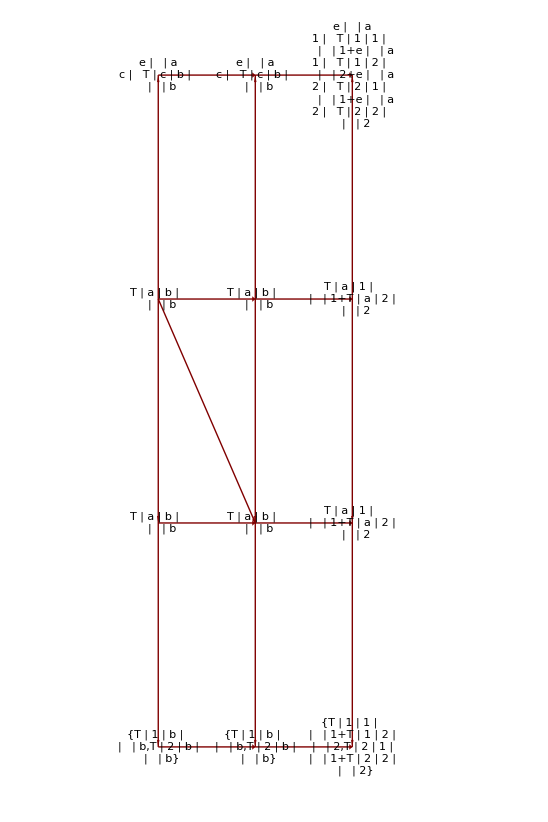

```mathematica
LayeredGraphPlot[{
{expr21->expr11,"SeparateBasis\n(Free)"},
{expr21->expr31,"FreeToBasis"},
{expr31->expr41,"ComponentArray"},
{expr11->expr12,"DummyToBasis"},
{expr22->expr12,"SeparateBasis"},
{expr21->expr22,"DummyToBasis"},
{expr22->expr32,"FreeToBasis"},
{expr31->expr32,"DummyToBasis"},
{expr21->expr32,"ToBasis"},
{expr32->expr42,"ComponentArray"},
{expr41->expr42,"DummyToBasis"},
{expr12->expr13,"TraceBasisDummy"},
{expr23->expr13,"SeparateBasis +\nTraceBasisDummy"},
{expr22->expr23,"TraceBasisDummy"},
{expr23->expr33,"FreeToBasis"},
{expr32->expr33,"TraceBasisDummy"},
{expr33->expr43,"ComponentArray"},
{expr42->expr43,"TraceBasisDummy"}
},VertexLabeling->True,FormatType->StandardForm, VertexCoordinateRules -> {{0., 2.}, {0., 3.}, {0., 1.}, {0., 0.}, {1., 3.}, {1., 2.},{1.,1.},{1.,0.},{2.,3.},{2.,2.},{2.,1.},{2.,0.}}]
```

```mathematica
UndefBasis[polar]
```

```mathematica
UndefTensor[T]
```

** UndefTensor: Undefined tensor T

```mathematica
Remove[expr11,expr12,expr13,expr21,expr22,expr23,expr31,expr32,expr33,expr41,expr42,expr43]
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$45844,z$45846,z$45848,z$45849,z$45851,z$45853,z$45855,z$45856,z$45858,z$45859,z$45862,z$45863,z$45864,z$45868,z$45870,z$45871,z$45872,z$45873,z$45874,z$45875,z$45876,z$45878,z$45879,z$45880,z$45882,z$45883,z$45884,z$45886,z$45887,z$45889,z$45891,z$45893,z$45895}

### 3.4. Extraction of components

#### 3.4.0. Comments

Given a tensor g[-a, -b] there are at least three different ways in which a user might want to deal with the components of that tensor:
	- an expression like     Basis[{2,polar},-a] Basis[{2,polar},-b] + Sin[ theta[] ]^2 Basis[{3,polar},-a] Basis[{3,polar},-b] 
	- a set of rules like { g[{2,-polar}, {2,-polar}] -> 1, g[{3,-polar}, {3,-polar}] -> Sin[ theta[] ]^2 }, all other components understood as zero
	- a matrix of values { { 1, 0}, {0, Sin[ theta[] ]^2} }
and there might be other ways (for instance, the user could give a formula which computes the components of the tensor when they are required).

Given a non-expanded expression, still with b-indices, we can extract its components with the functions ComponentArray / TableOfComponents. However, these functions would be slow for already expanded expressions. In that case, the recommended way to do it is using the Mathematica built-in Coefficient in combination with the xCoba command BasisArray. This section gives examples of the use of Coefficient, and shows a number of possible problems that might appear in the process.

#### 3.4.1. IndexCoefficient and BasisArray

Simple extension of IndexCoefficient:

```mathematica
?Coefficient
```

RowBox[{"Coefficient", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["form", "TI"]}], "]"}] gives the coefficient of StyleBox["form", "TI"] in the polynomial StyleBox["expr", "TI"]. 
RowBox[{"Coefficient", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["form", "TI"], ",", StyleBox["n", "TI"]}], "]"}] gives the coefficient of RowBox[{StyleBox["form", "TI"], "^", StyleBox["n", "TI"]}] in StyleBox["expr", "TI"].

```mathematica
?IndexCoefficient
```

IndexCoefficient[expr, form] gives the coefficient of form (any indexed object with no division present) in expr.

```mathematica
Unprotect[IndexCoefficient];
IndexCoefficient[expr_,ba_BasisArray]:=Coefficient[expr,Apply[ba,IndicesOf[Free][expr]]];
IndexCoefficient[expr_,basis_?BasisQ]:=IndexCoefficient[expr,BasisArray[basis]];
Protect[IndexCoefficient];
```

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
DefBasis[cartesian,TangentM,{1,2},BasisColor->RGBColor[0,0,1],DefInfo->False]
```

Suppose we start from an expression like this:

```mathematica
uexpr=Plus@@Flatten[Table[Random[Integer,{-10,10}],{2},{2},{2}]BasisArray[polar][a,b,c]]
```

-7 e |   | a
1 |   e |   | b
1 |   e |   | c
1 |  -9 e |   | b
1 |   e |   | c
1 |   e |   | a
2 |  -7 e |   | a
1 |   e |   | c
1 |   e |   | b
2 |  +6 e |   | c
1 |   e |   | a
2 |   e |   | b
2 |  +10 e |   | b
1 |   e |   | a
2 |   e |   | c
2 |  -e |   | a
1 |   e |   | b
2 |   e |   | c
2 |  -9 e |   | a
2 |   e |   | b
2 |   e |   | c
2 |

```mathematica
dexpr=Plus@@Flatten[Table[Random[Integer,{-10,10}],{2},{2},{2}]BasisArray[polar][-a,-b,-c]]
```

-4 e |   | 1
a |   e |   | 1
b |   e |   | 1
c |  -3 e |   | 2
a |   e |   | 1
b |   e |   | 1
c |  +10 e |   | 1
a |   e |   | 2
b |   e |   | 1
c |  +10 e |   | 2
a |   e |   | 2
b |   e |   | 1
c |  +3 e |   | 1
a |   e |   | 1
b |   e |   | 2
c |  +9 e |   | 2
a |   e |   | 1
b |   e |   | 2
c |  -7 e |   | 1
a |   e |   | 2
b |   e |   | 2
c |  -2 e |   | 2
a |   e |   | 2
b |   e |   | 2
c |

This is a fully expanded expression, in a single basis, and so it is simple to extract all components:

```mathematica
ucoeffs=Coefficient[uexpr,BasisArray[polar][a,b,c]]
```

{{{-7,0},{-7,-1}},{{-9,10},{6,-9}}}

```mathematica
dcoeffs=Coefficient[dexpr,BasisArray[polar][-a,-b,-c]]
```

{{{-4,3},{10,-7}},{{-3,9},{10,-2}}}

Reduced notations:

```mathematica
IndexCoefficient[uexpr,polar]===ucoeffs
```

True

```mathematica
IndexCoefficient[uexpr,BasisArray[polar]]===ucoeffs
```

True

```mathematica
IndexCoefficient[dexpr,polar]===dcoeffs
```

True

```mathematica
IndexCoefficient[dexpr,BasisArray[polar]]===dcoeffs
```

True

These are also possible, but slower:

```mathematica
(uexpr//ToBasis[polar]//ComponentArray)===ucoeffs
```

True

```mathematica
TableOfComponents[uexpr,{a,polar},{b,polar},{c,polar}]===ucoeffs
```

True

```mathematica
(dexpr//ToBasis[polar]//ComponentArray)===dcoeffs
```

True

```mathematica
TableOfComponents[dexpr,-{a,polar},-{b,polar},-{c,polar}]===dcoeffs
```

True

Let us check that the result is correct:

```mathematica
ucoeffs BasisArray[polar][a,b,c]
```

{{{-7 e |   | a
1 |   e |   | b
1 |   e |   | c
1 |  ,0},{-7 e |   | a
1 |   e |   | c
1 |   e |   | b
2 |  ,-e |   | a
1 |   e |   | b
2 |   e |   | c
2 |  }},{{-9 e |   | b
1 |   e |   | c
1 |   e |   | a
2 |  ,10 e |   | b
1 |   e |   | a
2 |   e |   | c
2 |  },{6 e |   | c
1 |   e |   | a
2 |   e |   | b
2 |  ,-9 e |   | a
2 |   e |   | b
2 |   e |   | c
2 |  }}}

```mathematica
Plus@@Flatten[%]
```

-7 e |   | a
1 |   e |   | b
1 |   e |   | c
1 |  -9 e |   | b
1 |   e |   | c
1 |   e |   | a
2 |  -7 e |   | a
1 |   e |   | c
1 |   e |   | b
2 |  +6 e |   | c
1 |   e |   | a
2 |   e |   | b
2 |  +10 e |   | b
1 |   e |   | a
2 |   e |   | c
2 |  -e |   | a
1 |   e |   | b
2 |   e |   | c
2 |  -9 e |   | a
2 |   e |   | b
2 |   e |   | c
2 |

```mathematica
uexpr-%
```

0

The command is so simple that it is not worth creating a name for it. We just overload IndexCoefficient.

Suppose there are several bases:

```mathematica
expr=Total[RandomInteger[{-10,10},{2,2}]BasisArray[polar,cartesian][a,-b],2]
```

5 e |   | 1
b |   e |   | a
1 |  +10 e |   | 1
b |   e |   | a
2 |  +e |   | 2
b |   e |   | a
2 |

```mathematica
IndexCoefficient[expr,BasisArray[polar,cartesian]]
```

{{5,0},{10,1}}

There can be problems when the expression has more than one basis:

```mathematica
expr=Plus@@Flatten[Table[Random[Integer,{-10,10}],{2},{2},{2}]BasisArray[polar][a,b,c]]+Plus@@Flatten[Table[Random[Integer,{-10,10}],{2},{2},{2}]BasisArray[cartesian][a,b,c]]
```

-9 e |   | a
1 |   e |   | b
1 |   e |   | c
1 |  -5 e |   | a
1 |   e |   | b
1 |   e |   | c
1 |  -3 e |   | b
1 |   e |   | c
1 |   e |   | a
2 |  -7 e |   | a
1 |   e |   | c
1 |   e |   | b
2 |  -10 e |   | c
1 |   e |   | a
2 |   e |   | b
2 |  -2 e |   | a
1 |   e |   | b
1 |   e |   | c
2 |  -8 e |   | b
1 |   e |   | a
2 |   e |   | c
2 |  +4 e |   | a
1 |   e |   | b
2 |   e |   | c
2 |  -7 e |   | a
2 |   e |   | b
2 |   e |   | c
2 |  -2 e |   | b
1 |   e |   | c
1 |   e |   | a
2 |  -2 e |   | a
1 |   e |   | c
1 |   e |   | b
2 |  +8 e |   | c
1 |   e |   | a
2 |   e |   | b
2 |  -10 e |   | a
1 |   e |   | b
1 |   e |   | c
2 |  +8 e |   | b
1 |   e |   | a
2 |   e |   | c
2 |  +9 e |   | a
2 |   e |   | b
2 |   e |   | c
2 |

Now using a single basis extracts the coefficients of the elements of that basis only:

```mathematica
coeffspolar=IndexCoefficient[expr,polar]
```

{{{-5,-10},{-2,0}},{{-2,8},{8,9}}}

```mathematica
coeffscartesian=IndexCoefficient[expr,cartesian]
```

{{{-9,-2},{-7,4}},{{-3,-8},{-10,-7}}}

But none of those lists gives a complete description of the expression. We need to transform it into an expression in a single basis:

```mathematica
SeparateBasis[polar][expr,IndicesOf[CIndex,Basis[cartesian]]]//ScreenDollarIndices
```

-5 e |   | a
1 |   e |   | b
1 |   e |   | c
1 |  -2 e |   | b
1 |   e |   | c
1 |   e |   | a
2 |  -2 e |   | a
1 |   e |   | c
1 |   e |   | b
2 |  +8 e |   | c
1 |   e |   | a
2 |   e |   | b
2 |  -10 e |   | a
1 |   e |   | b
1 |   e |   | c
2 |  +8 e |   | b
1 |   e |   | a
2 |   e |   | c
2 |  +9 e |   | a
2 |   e |   | b
2 |   e |   | c
2 |  -3 e |   | d
1 |   e |   | e
1 |   e |   | f
2 |   e |   | b
d |   e |   | c
e |   e |   | a
f |  -10 e |   | d
1 |   e |   | e
2 |   e |   | f
2 |   e |   | c
d |   e |   | a
e |   e |   | b
f |  -7 e |   | d
1 |   e |   | e
1 |   e |   | f
2 |   e |   | a
d |   e |   | c
e |   e |   | b
f |  -8 e |   | d
1 |   e |   | e
2 |   e |   | f
2 |   e |   | b
d |   e |   | a
e |   e |   | c
f |  -9 e |   | d
1 |   e |   | e
1 |   e |   | f
1 |   e |   | a
d |   e |   | b
e |   e |   | c
f |  -2 e |   | d
1 |   e |   | e
1 |   e |   | f
2 |   e |   | a
d |   e |   | b
e |   e |   | c
f |  +4 e |   | d
1 |   e |   | e
2 |   e |   | f
2 |   e |   | a
d |   e |   | b
e |   e |   | c
f |  -7 e |   | d
2 |   e |   | e
2 |   e |   | f
2 |   e |   | a
d |   e |   | b
e |   e |   | c
f |

```mathematica
TraceBasisDummy[%]
```

-5 e |   | a
1 |   e |   | b
1 |   e |   | c
1 |  -9 (e |   | 1
1 |)^3 e |   | a
1 |   e |   | b
1 |   e |   | c
1 |  -12 (e |   | 1
1 |)^2 e |   | a
1 |   e |   | b
1 |   e |   | c
1 |   e |   | 1
2 |  -14 e |   | 1
1 |   e |   | a
1 |   e |   | b
1 |   e |   | c
1 |   (e |   | 1
2 |)^2-7 e |   | a
1 |   e |   | b
1 |   e |   | c
1 |   (e |   | 1
2 |)^3-2 e |   | b
1 |   e |   | c
1 |   e |   | a
2 |  -9 (e |   | 1
1 |)^2 e |   | 2
1 |   e |   | b
1 |   e |   | c
1 |   e |   | a
2 |  -9 e |   | 1
1 |   e |   | 2
1 |   e |   | b
1 |   e |   | c
1 |   e |   | 1
2 |   e |   | a
2 |  +4 e |   | 2
1 |   e |   | b
1 |   e |   | c
1 |   (e |   | 1
2 |)^2 e |   | a
2 |  -3 (e |   | 1
1 |)^2 e |   | b
1 |   e |   | c
1 |   e |   | 2
2 |   e |   | a
2 |  -18 e |   | 1
1 |   e |   | b
1 |   e |   | c
1 |   e |   | 1
2 |   e |   | 2
2 |   e |   | a
2 |  -7 e |   | b
1 |   e |   | c
1 |   (e |   | 1
2 |)^2 e |   | 2
2 |   e |   | a
2 |  -2 e |   | a
1 |   e |   | c
1 |   e |   | b
2 |  -9 (e |   | 1
1 |)^2 e |   | 2
1 |   e |   | a
1 |   e |   | c
1 |   e |   | b
2 |  -5 e |   | 1
1 |   e |   | 2
1 |   e |   | a
1 |   e |   | c
1 |   e |   | 1
2 |   e |   | b
2 |  -8 e |   | 2
1 |   e |   | a
1 |   e |   | c
1 |   (e |   | 1
2 |)^2 e |   | b
2 |  -7 (e |   | 1
1 |)^2 e |   | a
1 |   e |   | c
1 |   e |   | 2
2 |   e |   | b
2 |  -6 e |   | 1
1 |   e |   | a
1 |   e |   | c
1 |   e |   | 1
2 |   e |   | 2
2 |   e |   | b
2 |  -7 e |   | a
1 |   e |   | c
1 |   (e |   | 1
2 |)^2 e |   | 2
2 |   e |   | b
2 |  +8 e |   | c
1 |   e |   | a
2 |   e |   | b
2 |  -9 e |   | 1
1 |   (e |   | 2
1 |)^2 e |   | c
1 |   e |   | a
2 |   e |   | b
2 |  -2 (e |   | 2
1 |)^2 e |   | c
1 |   e |   | 1
2 |   e |   | a
2 |   e |   | b
2 |  -10 e |   | 1
1 |   e |   | 2
1 |   e |   | c
1 |   e |   | 2
2 |   e |   | a
2 |   e |   | b
2 |  -4 e |   | 2
1 |   e |   | c
1 |   e |   | 1
2 |   e |   | 2
2 |   e |   | a
2 |   e |   | b
2 |  -10 e |   | 1
1 |   e |   | c
1 |   (e |   | 2
2 |)^2 e |   | a
2 |   e |   | b
2 |  -7 e |   | c
1 |   e |   | 1
2 |   (e |   | 2
2 |)^2 e |   | a
2 |   e |   | b
2 |  -10 e |   | a
1 |   e |   | b
1 |   e |   | c
2 |  -9 (e |   | 1
1 |)^2 e |   | 2
1 |   e |   | a
1 |   e |   | b
1 |   e |   | c
2 |  -10 e |   | 1
1 |   e |   | 2
1 |   e |   | a
1 |   e |   | b
1 |   e |   | 1
2 |   e |   | c
2 |  -10 e |   | 2
1 |   e |   | a
1 |   e |   | b
1 |   (e |   | 1
2 |)^2 e |   | c
2 |  -2 (e |   | 1
1 |)^2 e |   | a
1 |   e |   | b
1 |   e |   | 2
2 |   e |   | c
2 |  -4 e |   | 1
1 |   e |   | a
1 |   e |   | b
1 |   e |   | 1
2 |   e |   | 2
2 |   e |   | c
2 |  -7 e |   | a
1 |   e |   | b
1 |   (e |   | 1
2 |)^2 e |   | 2
2 |   e |   | c
2 |  +8 e |   | b
1 |   e |   | a
2 |   e |   | c
2 |  -9 e |   | 1
1 |   (e |   | 2
1 |)^2 e |   | b
1 |   e |   | a
2 |   e |   | c
2 |  -7 (e |   | 2
1 |)^2 e |   | b
1 |   e |   | 1
2 |   e |   | a
2 |   e |   | c
2 |  -5 e |   | 1
1 |   e |   | 2
1 |   e |   | b
1 |   e |   | 2
2 |   e |   | a
2 |   e |   | c
2 |  -6 e |   | 2
1 |   e |   | b
1 |   e |   | 1
2 |   e |   | 2
2 |   e |   | a
2 |   e |   | c
2 |  -8 e |   | 1
1 |   e |   | b
1 |   (e |   | 2
2 |)^2 e |   | a
2 |   e |   | c
2 |  -7 e |   | b
1 |   e |   | 1
2 |   (e |   | 2
2 |)^2 e |   | a
2 |   e |   | c
2 |  -9 e |   | 1
1 |   (e |   | 2
1 |)^2 e |   | a
1 |   e |   | b
2 |   e |   | c
2 |  -3 (e |   | 2
1 |)^2 e |   | a
1 |   e |   | 1
2 |   e |   | b
2 |   e |   | c
2 |  -9 e |   | 1
1 |   e |   | 2
1 |   e |   | a
1 |   e |   | 2
2 |   e |   | b
2 |   e |   | c
2 |  -18 e |   | 2
1 |   e |   | a
1 |   e |   | 1
2 |   e |   | 2
2 |   e |   | b
2 |   e |   | c
2 |  +4 e |   | 1
1 |   e |   | a
1 |   (e |   | 2
2 |)^2 e |   | b
2 |   e |   | c
2 |  -7 e |   | a
1 |   e |   | 1
2 |   (e |   | 2
2 |)^2 e |   | b
2 |   e |   | c
2 |  +9 e |   | a
2 |   e |   | b
2 |   e |   | c
2 |  -9 (e |   | 2
1 |)^3 e |   | a
2 |   e |   | b
2 |   e |   | c
2 |  -12 (e |   | 2
1 |)^2 e |   | 2
2 |   e |   | a
2 |   e |   | b
2 |   e |   | c
2 |  -14 e |   | 2
1 |   (e |   | 2
2 |)^2 e |   | a
2 |   e |   | b
2 |   e |   | c
2 |  -7 (e |   | 2
2 |)^3 e |   | a
2 |   e |   | b
2 |   e |   | c
2 |

```mathematica
IndexCoefficient[%,polar]//MatrixForm
```

((-5-9 (e |   | 1
1 |)^3-12 (e |   | 1
1 |)^2 e |   | 1
2 |  -14 e |   | 1
1 |   (e |   | 1
2 |)^2-7 (e |   | 1
2 |)^3
-10-9 (e |   | 1
1 |)^2 e |   | 2
1 |  -10 e |   | 1
1 |   e |   | 2
1 |   e |   | 1
2 |  -10 e |   | 2
1 |   (e |   | 1
2 |)^2-2 (e |   | 1
1 |)^2 e |   | 2
2 |  -4 e |   | 1
1 |   e |   | 1
2 |   e |   | 2
2 |  -7 (e |   | 1
2 |)^2 e |   | 2
2 |  ) | (-2-9 (e |   | 1
1 |)^2 e |   | 2
1 |  -5 e |   | 1
1 |   e |   | 2
1 |   e |   | 1
2 |  -8 e |   | 2
1 |   (e |   | 1
2 |)^2-7 (e |   | 1
1 |)^2 e |   | 2
2 |  -6 e |   | 1
1 |   e |   | 1
2 |   e |   | 2
2 |  -7 (e |   | 1
2 |)^2 e |   | 2
2 |  
-9 e |   | 1
1 |   (e |   | 2
1 |)^2-3 (e |   | 2
1 |)^2 e |   | 1
2 |  -9 e |   | 1
1 |   e |   | 2
1 |   e |   | 2
2 |  -18 e |   | 2
1 |   e |   | 1
2 |   e |   | 2
2 |  +4 e |   | 1
1 |   (e |   | 2
2 |)^2-7 e |   | 1
2 |   (e |   | 2
2 |)^2)
(-2-9 (e |   | 1
1 |)^2 e |   | 2
1 |  -9 e |   | 1
1 |   e |   | 2
1 |   e |   | 1
2 |  +4 e |   | 2
1 |   (e |   | 1
2 |)^2-3 (e |   | 1
1 |)^2 e |   | 2
2 |  -18 e |   | 1
1 |   e |   | 1
2 |   e |   | 2
2 |  -7 (e |   | 1
2 |)^2 e |   | 2
2 |  
8-9 e |   | 1
1 |   (e |   | 2
1 |)^2-7 (e |   | 2
1 |)^2 e |   | 1
2 |  -5 e |   | 1
1 |   e |   | 2
1 |   e |   | 2
2 |  -6 e |   | 2
1 |   e |   | 1
2 |   e |   | 2
2 |  -8 e |   | 1
1 |   (e |   | 2
2 |)^2-7 e |   | 1
2 |   (e |   | 2
2 |)^2) | (8-9 e |   | 1
1 |   (e |   | 2
1 |)^2-2 (e |   | 2
1 |)^2 e |   | 1
2 |  -10 e |   | 1
1 |   e |   | 2
1 |   e |   | 2
2 |  -4 e |   | 2
1 |   e |   | 1
2 |   e |   | 2
2 |  -10 e |   | 1
1 |   (e |   | 2
2 |)^2-7 e |   | 1
2 |   (e |   | 2
2 |)^2
9-9 (e |   | 2
1 |)^3-12 (e |   | 2
1 |)^2 e |   | 2
2 |  -14 e |   | 2
1 |   (e |   | 2
2 |)^2-7 (e |   | 2
2 |)^3))

```mathematica
Remove[ucoeffs,dcoeffs,dexpr,uexpr,expr,coeffscartesian,coeffspolar]
```

```mathematica
UndefBasis[cartesian]
```

```mathematica
UndefBasis[polar]
```

```mathematica
Remove[expr]
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$46651,z$46652,z$46653,z$46655,z$46656,z$46657,z$46658,z$46659,z$46660,z$46661,z$46662,z$46663,z$46664,z$46665,z$46667,z$46668,z$46669,z$46670,z$46671,z$46672,z$46673,z$46674,z$46675,z$46677,z$46679,z$46680,z$46681,z$46682,z$46683,z$46684,z$46685,z$46686,z$46687,z$46689,z$46691,z$46693,z$46695,z$46696,z$46697,z$46698,z$46700,z$46701,z$46702,z$46704,z$46705,z$46706,z$46707,z$46708,z$46709,z$46710,z$46711,z$46712,z$46714,z$46715,z$46716,z$46717,z$46718,z$46719,z$46720,z$46721,z$46722,z$46723,z$46725,z$46727,z$46728,z$46729,z$46730,z$46731,z$46732,z$46733,z$46734,z$46735,z$46736,z$46738,z$46740,z$46742,z$46744,z$46745,z$46746,z$46747,z$46748,z$46749,z$46750,z$46751,z$46752,z$46753,z$46754,z$46755,z$46756,z$46757,z$46758,z$46759,z$46760,z$46761,z$46762,z$46763,z$46764,z$46765,z$46766,z$46767,z$46768,z$46795,z$46796,z$46797,z$46799,z$46800,z$46801,z$46803,z$46804,z$46805,z$46807,z$46808,z$46809,z$46811,z$46812,z$46813,z$46815,z$46816,z$46817,z$46819,z$46820,z$46821,z$46823,z$46824,z$46825}

#### 3.4.2. Three ways of storing a component expression

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
DefBasis[cartesian,TangentM,{1,2},BasisColor->RGBColor[0,0,1],DefInfo->False]
```

```mathematica
DefTensor[T[a,b,c],M]
```

** DefTensor: Defining tensor T[a,b,c].

Given an expression

```mathematica
expr=Plus@@Flatten[Table[Random[Integer,{-10,10}],{2},{2},{2}]BasisArray[polar][a,b,c]]
```

-3 e |   | a
1 |   e |   | b
1 |   e |   | c
1 |  -8 e |   | b
1 |   e |   | c
1 |   e |   | a
2 |  +4 e |   | a
1 |   e |   | c
1 |   e |   | b
2 |  -9 e |   | c
1 |   e |   | a
2 |   e |   | b
2 |  +6 e |   | a
1 |   e |   | b
1 |   e |   | c
2 |  +10 e |   | b
1 |   e |   | a
2 |   e |   | c
2 |  +8 e |   | a
2 |   e |   | b
2 |   e |   | c
2 |

we can generate an array or a list of rules:

```mathematica
array=IndexCoefficient[expr,polar]
```

{{{-3,6},{4,0}},{{-8,10},{-9,8}}}

From the array and the name of the basis, we can generate a list of rules:

```mathematica
rules=Flatten@ThreadComponentArray[ComponentArray[T,{polar,polar,polar}],array]
```

{T | 1 | 1 | 1
  |   |  →-3,T | 1 | 1 | 2
  |   |  →6,T | 1 | 2 | 1
  |   |  →4,T | 1 | 2 | 2
  |   |  →0,T | 2 | 1 | 1
  |   |  →-8,T | 2 | 1 | 2
  |   |  →10,T | 2 | 2 | 1
  |   |  →-9,T | 2 | 2 | 2
  |   |  →8}

(We will see later how to construct a FoldedRule structure, containing information on the symmetry of the object.)

Coba comes handy when we are talking about a set of components, but we have not associated them to any tensor yet.

Viceversa, we can generate the array from the rules:

```mathematica
ComponentArray[T,{polar,polar,polar}]/.rules
```

{{{-3,6},{4,0}},{{-8,10},{-9,8}}}

and the expression from the array:

```mathematica
Plus@@Flatten[array BasisArray[polar][a,b,c]]
```

-3 e |   | a
1 |   e |   | b
1 |   e |   | c
1 |  -8 e |   | b
1 |   e |   | c
1 |   e |   | a
2 |  +4 e |   | a
1 |   e |   | c
1 |   e |   | b
2 |  -9 e |   | c
1 |   e |   | a
2 |   e |   | b
2 |  +6 e |   | a
1 |   e |   | b
1 |   e |   | c
2 |  +10 e |   | b
1 |   e |   | a
2 |   e |   | c
2 |  +8 e |   | a
2 |   e |   | b
2 |   e |   | c
2 |

```mathematica
expr-%
```

0

It is important to realize that the expression and the list of rules contain full information on the expression, but the array needs to know additionally the bases (with characters) in which the expression has been expanded.

```mathematica
UndefTensor[T]
```

** UndefTensor: Undefined tensor T

```mathematica
UndefBasis[cartesian]
```

```mathematica
UndefBasis[polar]
```

```mathematica
Remove[expr,array,rules]
```

```mathematica
EndExamples[]
```

## 4. Explicit representation of values: CTensor

```mathematica
(************************* 4. CTensor ************************)
```

```mathematica
{TimeUsed[],SessionTime[],TimeUsed[]/SessionTime[]}
```

{32.3621,214.33919,0.150986}

TODO: ToCanonical[ CTensor[array, bases] ] should be able to access the components of the array.

### 4.0. Comments. xCobaCache

#### 4.0.1. Summary

The main idea is to have expressions CTensor[array, bases, addweight] and CCovD[covd, christoffel, metric] such that we can replace an abstract tensor by a CTensor expression and an abstract covariant derivative by a CCovD expression. In this way, a computation can be performed in abstract form, and then we simply replace the abstract objects by the component objects.

An action like Riemann[cd], which would return another symbolic object Riemanncd for symbolic cd, now is actually going to compute another object.

TENSOR:
	DefTensor[ X[a,-b], {M1, M2}, sym, Dagger->Complex, WeightOfTensor->weight, OrthogonalTo->{u}]
	X = CTensor[array, bases, addweight]
		The symmetry, dependencies and orthogonality properties must be computed in real time from the three arguments of X.

COVD:
	DefCovD[ covd[-a], Torsion->True, Curvature->True, FromMetric->g, CurvatureRelations->True, ExtendendFrom->cd, OrthogonalTo->{u}, WeightedWithBasis->basis ]
	covd = CCovD[ pd, christoffeltensor, metric]
		The bases of the christoffeltensor must make sense, and one of them must be associated to the pd. QUESTION: How do we know the basis that pd will add? Perhaps denote it by PD[basis]
		Not clear how to represent the fact that it can act on several bundles. Then there are lots of additional information...
		
	Compute:
		Christoffel[covd, pd]
		Riemann[covd]. Use the most natural basis given the input.

We need to extend CTensor to handle components of (xTerior) forms, and in general of objects with nonzero grades. There are two approaches.Suppose the vector-valued two-form ω[a], with degree (Wedge-grade) 2, and all in dimension 2:
	- We can use array elements that are linear combinations of (products of) elements of a basis with grade 1.
		CTensor[{ω112 Wedge[theta[{1, B}], theta[{2, B}]], ω212 Wedge[theta[{1, B}], theta[{2, B}]]}, {B}, 0]
	- We can refer to the elements of an “indexed version” of the form.
		CTensor[{{{0, ω112}, {-ω112, 0}}, {{0, ω212}, {-ω212, 0}}}, {B, CForm[-B, -B]}, 0]
The former approach is simpler to implement. The latter seems more powerful.

#### 4.0.2. A major problem: the Zero tensor

It is not clear what to do with the zero tensor. The problem is the following. In xTensor it is natural to convert T[a,b] into 0 because this is what happens when we work with T[a,b] - T[a,b] or when we have 0*T[a,b]. However, this is problematic for the CTensor object because we might have something like T[a,b] CTensor[{ω1, ω2}, {-B}][-b] + v[a]. If T[a,b] is converted into 0 then the expression will result being CTensor[{0,0},{-B}][-b] + v[a], which makes no sense. This is dangerous.

There are three possibilities, perhaps only two:
	a) All zero tensors are converted into 0, as it is now done in xTensor. This is the simplest possibility, and the one suggested by the current xTensor, but it is rather disappointing in xCoba. Anyway, it might be now too late to choose anything else.
	b) All zero tensors are represented as an indexed abstract tensor Zero[a, b, -c] with maximal symmetry. This would be a fundamental change in xTensor. This could be implemented with a simple upvalue T/: 0*T=Zero for each defined tensor.
	c) The zero tensors in xCoba are CTensor[{0,...}, bases], behaving differently from xTensor. This might be just inconsistent, as pointed out in the example above.

#### 4.0.3. $CVSimplify

When computing tensors that require of intermediate computations, it is important to simplify those intermediate results, to have smaller expressions in later computations. In xCoba pre 0.8 there was the option CVSimplify and its global default $CVSimplify. It is not a very good name, but there is no reason to have a second option/variable doing essentially the same, so we keep it.

The default value of $CVSimplify was Identity before, but in most applications it had to be set to Simplify, so we change that now:

```mathematica
$CVSimplify=Simplify;
```

#### 4.0.4. Cache system

This is a simple way to store results, to avoid recomputation. Note however that we do not check the size of the cache table at any moment. We leave the responsibility with the user to clean it from time to time... Before storing the results we take the opportunity to simplify them, using whatever is stored in $CVSimplify.

We could make the cache system more flexible, with more public functions interacting with it, in particular with functions to uncache individual results or force recomputation.

0) Global variables

```mathematica
?$xCobaCache
```

$xCobaCache is a boolean global variable specifying whether CTensor computations in xCoba should be cached. The default value is True.

```mathematica
?$xCobaCacheVerbose
```

$xCobaCacheVerbose is a boolean global variable specifying whether caching and use of cache should be reported. The default value is False.

```mathematica
$xCobaCache = True;
$xCobaCacheVerbose=False;
```

```mathematica
$xCobaCacheVerbose=True; (* Activated for testing *)
```

```mathematica
SetAttributes[xCobaCache,HoldAll];
SetAttributes[{ClearxCobaCache,xCobaCacheTable},HoldFirst];
```

1) xCobaCache: Check whether we already know the result of a computation. If we do, use that result. Otherwise, compute the result and cache it.

```mathematica
?xCobaCache
```

xCobaCache[lhs, rhs] checks whether there is a value in the xCobaCacheTable assigned to lhs, and returns it if there is. Otherwise the value rhs is stored in the cache, assigned to lhs, and returned. xCobaCache[lhs, rhs, name] stores the pair {lhs, rhs} with the given name, with default being the head of the expresion lhs. xCoba[lhs, rhs, name, simp] uses the simplification function simp on the rhs expression before storing it in the cache table.

```mathematica
xCobaCache[lhs:head_[___],rhs_]:=xCobaCache[lhs,rhs,head,$CVSimplify];
xCobaCache[lhs_,rhs_,name_]:=xCobaCache[lhs,rhs,name,$CVSimplify];
xCobaCache[lhs_,rhs_,name_,simp_]:=Module[{cache=xCobaCacheTable[lhs,name],compute,time,messages={},printQ=$xCobaCacheVerbose&&name=!=Null},
If[Head[cache]=!=xCobaCacheTable,
(* There is cached information. Return it *)
If[printQ,Print["    ",name,": Using cache"]];
cache,
(* There is no cached information. Compute rhs and store it *)
If[printQ,Print["    ",name,": Caching"]];
time=AbsoluteTime[];
compute=Catch[rhs];messages=$MessageList;
If[printQ&&FreeQ[compute,$Failed|$Aborted],Print["      Computed cache value in ",AbsoluteTime[]-time," seconds"]];
time=AbsoluteTime[];
If[simp=!=Identity,
compute=Catch[simp[compute]];messages=Join[messages,$MessageList];
If[printQ&&FreeQ[compute,$Failed|$Aborted],Print["      Applied ",simp," in ",AbsoluteTime[]-time," seconds"]]
];
(* Some sanity check. Don't cache if something went wrong *)
If[$xCobaCache&&FreeQ[compute,$Failed|$Aborted]&&messages==={},
xCobaCacheTable[lhs,name]=compute;
If[printQ,Print["      Cached ",ByteCount[compute]," bytes"]];
];
compute
]
];
```

2) xCobaCacheTable

```mathematica
?xCobaCacheTable
```

xCobaCacheTable[lhs, name] returns the expression associated to the key lhs and the given name, if it has been cached. Otherwise it stays unevaluated.

3) ClearxCobaCache

```mathematica
?ClearxCobaCache
```

ClearxCobaCache[All] clears the cache table for CTensor computations. ClearxCobaCache[{pos}] or ClearxCobaCache[{{pos1}, {pos2}, ...}] removes the values at positions posi (corresponding to the list of downvalues of xCobaCacheTable. ClearxCobaCache accepts input with Delete conventions.

```mathematica
ClearxCobaCache[lhs_,name_]:=Unset[xCobaCacheTable[lhs,name]];
ClearxCobaCache[del:(_Integer|_List)]:=(DownValues[xCobaCacheTable]=Delete[DownValues[xCobaCacheTable],del];);
ClearxCobaCache[All]:=Clear[xCobaCacheTable];
```

4) PrintxCobaCache. Print the cache table. This helps in knowing what we have so far, and also in removing entries from the table by number.

```mathematica
?PrintxCobaCache
```

PrintxCobaCache[] gives a tabular summary of the information stored in the xCobaCache table. The column on the left corresponds to the positions in the list of downvalues of xCobaCacheTable, and can be used to eliminate entries from the table using ClearxCobaCache[{pos}].

```mathematica
$xCobaCacheLargeComponentSize=200;
PrintxCobaCache[]:=TableForm[PrintxCobaCache1/@DownValues[xCobaCacheTable]/.ctensor_CTensor:>RawBoxes[CTensorBoxes[ctensor,$xCobaCacheLargeComponentSize]],TableHeadings->{Automatic,None}];
```

```mathematica
PrintxCobaCache1[_[xCobaCacheTable[expr:"ReportCompute"[object_,__],name_]]:>value_List]:={"ReportCompute"[object],{Skeleton[Length[value]]}};
PrintxCobaCache1[_[xCobaCacheTable[ChartsOf[array_],name_]]:>value_]:={"ChartsOf"[Shallow[array,1]],Short[HoldForm[value],1]}
PrintxCobaCache1[_[xCobaCacheTable[expr_,name_]]:>value_]:={Short[HoldForm[expr],1],Short[HoldForm[value],1]}
```

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
expr:=(Do[FactorInteger[i],{i,1000000}];x)
```

```mathematica
xCobaCache[1+1,expr,Test]//Timing
```

Test: Caching

Computed cache value in 4.988984 seconds

Applied Simplify in 0.000086 seconds

Cached 0 bytes

{4.98952,x}

```mathematica
??xCobaCacheTable
```

xCobaCacheTable[lhs, name] returns the expression associated to the key lhs and the given name, if it has been cached. Otherwise it stays unevaluated.

Attributes[xCobaCacheTable]={HoldFirst}
 
xCobaCacheTable[1+1,Test]=x

```mathematica
xCobaCache[1+1,expr,Test]//Timing
```

Test: Using cache

{0.00021,x}

```mathematica
ClearxCobaCache[All]
```

```mathematica
xCobaCache[1+1,expr,Test]//Timing
```

Test: Caching

Computed cache value in 4.955374 seconds

Applied Simplify in 0.000088 seconds

Cached 0 bytes

{4.95566,x}

```mathematica
ClearxCobaCache[All]
```

```mathematica
Remove[expr,x,i,Test]
```

```mathematica
EndExamples[]
```

### 4.1. CTensor

#### 4.1.1. Definitions without indices

We introduce a new object, called CTensor. It is a container object. Its first argument is an array; the second argument is a list of bases of the slots used; the third argument is the added weight (to that implied by the array scalar components). The whole object itself is an abstract tensor. The use of options would be odd here because they could be ordered in different ways. We decide that if an argument is needed then it must be present. Otherwise we will declare upvalues on CTensor for the corresponding extractor function. There is a special case CTensor[scalar, {}, addweight] for nonzero addweight; it is special because the first argument is not an array.

0) Extract parts and validation:

```mathematica
CTensorArray[CTensor[array_,bases_,addweight_]]:=array;
CTensorBases[CTensor[array_,bases_,addweight_]]:=bases;
CTensorRank[CTensor[array_,bases_List,addweight_]]:=Length[bases];
```

Slight validation:

```mathematica
CTensorQ[CTensor[array_,bases_,addweight_]]:=ArrayQ[array]&&ListQ[bases]&&Length[bases]===ArrayDepth[array];
CTensorQ[ctensor_CTensor,rank_Integer]:=CTensorQ[ctensor]&&CTensorRank[ctensor]===rank;
CTensorQ[ctensor_CTensor,bases_]:=CTensorQ[ctensor]&&CTensorBases[ctensor]===bases;
CTensorQ[ctensor_CTensor,rb_,weight_]:=CTensorQ[ctensor,rb]&&WeightOfTensor[ctensor]===weight;
CTensorQ[__]:=False;
```

1) Declare as an abstract tensor. We do not check the weight at all, or the correspondence between the first and second argument. This follows the general concept of tensor in xTensor, which includes the tensor densities.

```mathematica
xTensorQ[CTensor[scalar_,{},addweight_]]^:=True;
xTensorQ[CTensor[array_?ArrayQ,bases_List,addweight_]]^:=True;
```

2) The slot vbundles are read from the list of bases:

```mathematica
SlotsOfTensor[CTensor[array_,bases_List,addweight_]]^:=SignedVBundleOfBasis/@bases;
```

3) The weight and grade are read from its scalar components, plus the added weight in the third argument. We check homogeneity, and we are also careful not to consider zeros in an array with nonzero elements.

```mathematica
deleteDuplicatesNoZero[array_]:=With[{list=DeleteDuplicates[ArrayElements[array]]},
If[MemberQ[list,0]&&Length[list]>1,
DeleteCases[list,0],
list
]
]
```

```mathematica
ArrayElements[array_List]:=Flatten[array];
(* If the default value was 0 we could do array["NonzeroValues"] *)
ArrayElements[array_SparseArray]:=Flatten[array];
(* This is assuming SymmetrizedArray type *)
ArrayElements[array_StructuredArray]:=array["Data"][[2,All,2]];
ArrayElements[array_]:=Flatten[{array}];
```

```mathematica
ArrayWeight[array_]:=If[Length[#]===1,
First[#],
Throw[Message[WeightOfTensor::error,"Inhomogeneous weight found."]]]&@DeleteDuplicates[Expand/@WeightOf/@deleteDuplicatesNoZero[array]];
```

```mathematica
WeightOfTensor[CTensor[array_,bases_List,addweight_]]^:=ArrayWeight[array]+addweight;
```

Equivalent construction for grades:

```mathematica
ArrayGrade[array_,prod_]:=If[Length[#]===1,
First[#],
Throw[Message[Grade::error,"Inhomogeneous grade found."]]]&@DeleteDuplicates[Expand/@(Grade[#,prod]&/@deleteDuplicatesNoZero[array])];
```

```mathematica
GradeOfTensor[CTensor[array_,bases_List,addweight_],prod_]^:=ArrayGrade[array,prod];
```

For example the etaDownB tensor has components 1 or 0, hence with no scalar density, but the third argument will have weight -B. When it is multiplied by the square root of the determinant of the metric (with weight +B), the final CTensor will have scalar weight -B, added weight B, and hence total weight 0, as corresponds to a tensor.

If the added density weight is not specified, then it is automatically assumed to be 0:

```mathematica
CTensor[array_,bases_List]:=CTensor[array,bases,0];
```

4) The symmetry is read from the array of components. This requires Mathematica 9. For previous versions the tensors are reported to be nonsymmetric.

```mathematica
SymmetryGroupOfTensor[CTensor[scalar_,{},addweight_]]^:=StrongGenSet[{},GenSet[]];
SymmetryGroupOfTensor[CTensor[array_?ArrayQ,bases_List,addweight_]]^:=If[System`$VersionNumber>8.5,
With[{sym=TensorSymmetry[array]},
If[GroupTheory`Symmetries`SymmetryCompatibleQ[bases,sym],
xAct`xPerm`Private`MathToxPermSym[sym],
StrongGenSet[{},GenSet[]]
]
],
StrongGenSet[{},GenSet[]]
];
```

5) Complex conjugation is trivial:

```mathematica
Dagger[CTensor[array_,bases_List,addweight_]]^:=CTensor[Dagger[array],Dagger/@bases,Dagger[addweight]];
```

6) Dependencies. Just join all dependencies:

```mathematica
DependenciesOfTensor[CTensor[array_,bases_List,addweight_]]^:=xAct`xTensor`Private`SortDependencies[DeleteDuplicates@Join[Flatten[DependenciesOf/@DeleteDuplicates[Flatten[{array}]]],Flatten[DependenciesOfBasis/@bases],DependenciesOfWeight[addweight]]];
```

The bases in the added weight could also in principle contain dependency information:

```mathematica
DependenciesOfWeight[0]:={};
DependenciesOfWeight[addweight_Plus]:=Join@@(DependenciesOfWeight/@List@@addweight);
DependenciesOfWeight[Optional[_Integer]basis_]:=DependenciesOfBasis[basis];
```

7) Self-checks. So far we only check number of bases vs array depth. We could also check vbundle compatibility, but it is not clear whether that would spoil using subvbundles. Do not check height, because this will be used later to raise or lower bases automatically.

```mathematica
CTensor::nobd="Incompatible number of bases `1` and array depth `2`.";
CTensor[array_?ArrayQ,bases_List,addweight_]:=With[{nb=Length[bases],ad=ArrayDepth[array]},
$Failed/;(nb=!=ad&&Throw[Message[CTensor::nobd,nb,ad]])
];
```

8) Some simplification functions. Simplify works already.

```mathematica
Expand[CTensor[expr_,rest__]]^:=CTensor[Expand[expr],rest];
Together[CTensor[expr_,rest__]]^:=CTensor[Together[expr],rest];
```

9) Nesting of scalar CTensor objects. This is useful to add density weight. Note that the internal CTensor[...] has its pair of brackets, because it must be a scalar, not a tensor head. We use Expand to avoid results like 2B1 -2(B1-B2).

```mathematica
CTensor[CTensor[scalar_,{},addweight1_][],{},addweight2_]:=CTensor[scalar,{},Expand[addweight1+addweight2]];
```

10) Other:

```mathematica
CTensor/: MultiplyHead[k_,CTensor[array_,bases_List,addweight_]]:=CTensor[k array,bases,addweight];
CTensor/:xAct`xTensor`Private`TensorPlus[left___,t1_CTensor,middle___,t2_CTensor,right___]:=xAct`xTensor`Private`TensorPlus[left,t1+t2,middle,right];
CTensor/:xAct`xTensor`Private`TensorPlus[t_CTensor]:=t;
```

#### 4.1.2. Definitions with indices

1) Some canonicalization:

We do not need scalar component tensors (note both the list of bases and the sequence of indices must be empty). This is only valid for true scalars, not for scalar densities of nonzero added weight. That is, the CTensor head is needed then to keep the added weight information:

```mathematica
CTensor[x_,{},0][]:=x;
```

A very special case:

```mathematica
CTensor/:Power[CTensor[scalar_,{},addweight_][],n_]:=CTensor[Power[scalar,n],{},n addweight][];
CTensor/:Sqrt[CTensor[scalar_,{},addweight_][]]:=CTensor[Sqrt[scalar],{},Expand[addweight/2]][];
```

2) Check number of bases vs. number of indices. Only when they are proper indices, not patterns.

```mathematica
CTensor::nobi="Incompatible number of bases `1` and indices `2`.";
CTensor[array_?ArrayQ,bases_List,addweight_][inds___?GIndexQ]:=With[{nb=Length[bases],ni=Length[{inds}]},
$Failed/;(nb=!=ni&&Throw[Message[CTensor::nobi,nb,ni]])
];
```

3) Some simplification functions. Simplify works already.

```mathematica
Expand[ctensor_CTensor[inds__]]^:=Expand[ctensor][inds];
Together[ctensor_CTensor[inds__]]^:=Together[ctensor][inds];
```

#### 4.1.3. The Zero tensor

Useful function. We cannot use PossibleZeroQ because it would mask expressions that are not explicitly zero.

```mathematica
ExplicitZeroQ[0]:=True;
ExplicitZeroQ[0.]:=True;
ExplicitZeroQ[_]:=False;
```

```mathematica
ZeroArrayQ[array_]:=ArrayQ[array,_,ExplicitZeroQ];
```

This is the main definition of the treatment of zero tensors in xCoba. The key point is that Zero[a, -b] is converted into 0 by xTensor.

```mathematica
CTensor[0,{},addweight_]:=Zero;
CTensor[_?ZeroArrayQ,bases_List,addweight_]:=Zero;
```

```mathematica
?Zero
```

Zero[e1, ..., en] is 0 no matter what the arguments are.

#### 4.1.4. Additional definitions

Special definitions for metrics:

```mathematica
VBundleOfMetric::novbs="Incompatible vbundles for the bases of a metric.";
VBundleOfMetric[CTensor[array_?MatrixQ,bases_List,addweight_]]^:=If[Length[#]===1,First[#],Throw[Message[VBundleOfMetric::novbs,#]]]&@Union[VBundleOfBasis/@bases];
```

#### 4.1.5. Formatting

The current formatting is too trivial, it is essentially a call to MatrixForm. Several improvements are possible:
	1) We could color the brackets with the colors of the bases, because otherwise the information of the bases is not included.
	2) The height information is not included either, because it does not have to coincide with that of the indices.
	3) The LargeComponentString could be indexed using the position.
	4) The tooltips could contain bases (color) and height information.
	5) The indices do not respect the height of the brackets, and hence it is difficult to distinguish upper from lower indices.

Density weights:

```mathematica
WeightBox[boxes_,weight_Plus]:=Fold[WeightBox,boxes,List@@weight];
WeightBox[boxes_,basis_?BasisQ]:=OverscriptBox[boxes,ColorString["~",BasisColor[basis]]];
WeightBox[boxes_,-basis_?BasisQ]:=UnderscriptBox[boxes,ColorString["~",BasisColor[basis]]];
WeightBox[boxes_,n_Integer?Positive basis_]:=Nest[WeightBox[#,basis]&,boxes,n];
WeightBox[boxes_,n_Integer?Negative basis_]:=Nest[WeightBox[#,-basis]&,boxes,-n];
WeightBox[boxes_,0]:=boxes;
WeightBox[boxes_,basis_]:=(Message[CTensor::unknown,"basis",basis];boxes);
```

Separate the cases of SparseArray and SymmetrizedArray. We then show only rules.

```mathematica
$MaxNumberOfRowsInCTensorFormatting=4;
$MaxNumberOfColumnsInCTensorFormatting=4;
RuleColumns[rules_]:=With[{l=Length[rules],r=$MaxNumberOfRowsInCTensorFormatting,c=$MaxNumberOfColumnsInCTensorFormatting},
If[l≤r,
rules,
Transpose@Partition[If[l≤r c,rules,Append[Take[rules,r c-1],"More rules"]],r,r,1,""]
]
];
```

Position tooltips and separate the action on SparseArray and SymmetrizedArray objects.

```mathematica
AddToolTip[array_List,size_]:=MapIndexed[Tooltip[compf[#1,size],Rule[#2,#1]]&,array,{ArrayDepth[array]}];
AddToolTip[array_SparseArray,size_]:=RuleColumns@ArrayRules[array]/.Rule[lhs_,rhs_]:>Rule[lhs,Tooltip[compf[rhs,size]]];
AddToolTip[array_StructuredArray/;array["Structure"]==="SymmetrizedArray",size_]:=RuleColumns@SymmetrizedArrayRules[array]/.Rule[lhs_,rhs_]:>Rule[lhs,Tooltip[compf[rhs,size]]]
AddToolTip[array_]:=array;
```

Main code:

```mathematica
$LargeComponentSize=1000;
$LargeComponentString="●";
compf[expr_,size_]:=If[ByteCount[expr]<size,expr,$LargeComponentString];
PrintAs[CTensor[scalar_,{},addweight_]]^:=WeightBox[MakeBoxes[scalar,StandardForm],addweight];
PrintAs[ctensor_CTensor]^:=CTensorBoxes[ctensor,$LargeComponentSize];
$CTensorRepresentation="ColorBasisForm";
CTensorBoxes[CTensor[array_,bases_List,addweight_],size_]:=WeightBox[
Which[
(*ZeroArrayQ[Unevaluated[array]],
	StyleBox["0",Bold],*)
!ArrayQ[Unevaluated[array]],
	MakeBoxes[CTensor[array,bases,addweight],StandardForm],
True,
	With[{miarray=AddToolTip[array,size]},
	Switch[$CTensorRepresentation,
	"ColorBasisForm",
		StyleBox[ArrayBox[miarray,BasisColor/@xAct`xPerm`Private`nosign/@bases],Small],
	"MatrixForm",
		MakeBoxes[Style[MatrixForm[miarray],Small],StandardForm]
	]
	]
],
addweight
];
```

An alternative representation using colored “frames”, denoting the bases used. This also distinguishes between a matrix of dimensions {n, 1} and a vector of length {n} for example. Note that we use Normal on matrices, to avoid pink boxes with SparseArray objects (reported by Alfonso).

```mathematica
ArrayBox[list_?VectorQ,{color_}]:=GridBox[List/@(MakeBoxes[#,StandardForm]&/@list),AutoDelete->False,GridBoxDividers->{"ColumnsIndexed"->{1->color,2->color}}];
ArrayBoxRecurse[matrix_?MatrixQ,{color1_,color2_}]:=With[{dims=Dimensions[matrix]},GridBox[matrix,AutoDelete->False,GridBoxDividers->{"ColumnsIndexed"->{1->color1,dims[[2]]+1->color1},"RowsIndexed"->{1->color2,dims[[1]]+1->color2}}]];
ArrayBox[matrix_?MatrixQ,{color1_,color2_}]:=With[{dims=Dimensions[matrix]},GridBox[Map[MakeBoxes[#,StandardForm]&,Normal@matrix,{2}],AutoDelete->False,GridBoxDividers->{"ColumnsIndexed"->{1->color1,dims[[2]]+1->color1},"RowsIndexed"->{1->color2,dims[[1]]+1->color2}}]];
ArrayBox[array_?ArrayQ,colors_List]:=With[{colors2=Take[colors,2],colorsrest=Drop[colors,2]},
ArrayBoxRecurse[Map[ArrayBox[#,colorsrest]&,array,{2}],colors2]
];
(* TODO: This is not using the colors and it should. How? *)
ArrayBox[Rule[lhs_,rhs_],colors_]:=RowBox[{MakeBoxes[lhs,StandardForm],"→",MakeBoxes[rhs,StandardForm]}];
ArrayBox[x_,colors_]:=x;
ColorBasisForm[array_?ArrayQ,colors_List]:=RawBoxes[ArrayBox[array,colors]]
```

Simple examples:

```mathematica
{ArrayBox[{a,b},{Red}]//RawBoxes,MatrixForm[{a,b}]}
```

{a
b,(a
b)}

```mathematica
{ArrayBox[{{a},{b}},{Red,Blue}]//RawBoxes,MatrixForm[{{a},{b}}]}
```

{a
b,(a
b)}

```mathematica
{ArrayBox[{{{a}},{{b}}},{Red,Blue,Green}]//RawBoxes,MatrixForm[{{{a}},{{b}}}]}
```

{a
b,((a)
(b))}

```mathematica
ArrayBox[SparseArray[{a,b}],{Red}]//RawBoxes
```

a
b

```mathematica
ArrayBox[SparseArray[{{a},{b}}],{Red,Blue}]//RawBoxes
```

a
b

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
v=CTensor[{vr,vθ},{polar}]
```

CTensor[{vr,vθ},{polar},0]

```mathematica
v[a]
```

(vr
vθ) | a

```mathematica
Catch[v[a,b]]
```

CTensor::nobi: Incompatible number of bases 1 and indices 2.

Specify a formatting. PrintAs has attribute HoldFirst and therefore we need to give the full tensor, not just the symbol v:

```mathematica
PrintAs[CTensor[{vr,vθ},{polar},0]]^="v"
```

v

```mathematica
v[a]
```

v | a

```mathematica
%//InputForm
```

CTensor[{vr, vθ}, {polar}, 0][a]

Note that the upvalue was actually on CTensor:

```mathematica
CTensor/:PrintAs[CTensor[{vr,vθ},{polar},0]]=.
```

```mathematica
v[a]
```

(vr
vθ) | a

```mathematica
Y=CTensor[{{Y11,Y12},{Y21,Y22}},{polar,-polar}]
U=CTensor[{U1,U2},{-polar}]
```

CTensor[{{Y11,Y12},{Y21,Y22}},{polar,-polar},0]

CTensor[{U1,U2},{-polar},0]

```mathematica
Y[a,-b]
```

(Y11 | Y12
Y21 | Y22) | a |  
  | b

```mathematica
U[-a]
```

(U1
U2) |  
a

Properties:

```mathematica
S=CTensor[{{1,2I},{2I,3}},{polar,polar}]
```

CTensor[{{1,2 ⅈ},{2 ⅈ,3}},{polar,polar},0]

```mathematica
xTensorQ[S]
```

True

```mathematica
SlotsOfTensor[S]
```

{𝕋M,𝕋M}

```mathematica
SymmetryGroupOfTensor[S]
```

StrongGenSet[{1,2},GenSet[(1,2)]]

```mathematica
Dagger[S]
```

CTensor[{{1,-2 ⅈ},{-2 ⅈ,3}},{polar,polar},0]

```mathematica
DependenciesOfTensor[S]
```

{M}

```mathematica
WeightOfTensor[S]
```

0

Other cases:

```mathematica
CTensor[{{x,Basis[{-c,-B},{d,B}]},{delta[-c,d],d^4+d^3+3d^2+4d+1}},{B,B}][a,b]
```

(x | e |   | d
c |  
δ |   | d
c |   | 1+4 d+3 d^2+d^3+d^4) | a | b
  |

```mathematica
CTensor[Array[Subscript[x,##]&,{2,2,2}],{B,B,B}][a,b,c]
```

((x_(1,1,1)
x_(1,1,2)) | (x_(1,2,1)
x_(1,2,2))
(x_(2,1,1)
x_(2,1,2)) | (x_(2,2,1)
x_(2,2,2))) | a | b | c
  |   |

Scalars marked as densities have colored overtildes or undertildes. Note the relevance of the scalar pair of brackets:

```mathematica
{CTensor[4,{},2polar][],CTensor[x,{},-2polar][]}
```

{OverTilde[OverTilde[4]],(x_~)_~}

Other types of arrays:

```mathematica
SA=SparseArray[{{0,1},{-1,0}}]
```

SparseArray[<2>,{2,2}]

```mathematica
CSA=CTensor[SA,{polar,polar}]
```

CTensor[SparseArray[<2>,{2,2}],{polar,polar},0]

Currently the typesetting framework normalizes. That seems bad. The problem is that we use MatrixForm, which normalizes.

```mathematica
CSA[a,b]
```

(0 | 1
-1 | 0) | a | b
  |

```mathematica
SA=SymmetrizedArray@SA
```

StructuredArray[SymmetrizedArray,{2,2},-Structured Data-]

```mathematica
CSA=CTensor[SA,{polar,polar}]
```

CTensor[StructuredArray[SymmetrizedArray,{2,2},-Structured Data-],{polar,polar},0]

```mathematica
CSA[a,b]
```

(0 | 1
-1 | 0) | a | b
  |

```mathematica
Remove[x,v,Y,U,S,U1,U2,vr,vθ,Y11,Y12,Y21,Y22,SA,CSA]
```

```mathematica
UndefBasis[polar]
```

```mathematica
EndExamples[]
```

At some point I considered having an option PrintAs inside CTensor, something like

	Tensor[{v1,v2}, {chart}, PrintAs→”v”]

### 4.2. Transpositions

#### 4.2.1. Relevant permutations

Permutation moving (with Transpose) a slot to another place, pushing those in between:

```mathematica
moveto[n_,n_]:={1};
moveto[original_Integer,final_Integer]:=If[original<final,
Join[Range[original-1],{final},Range[original,final-1]],
Join[Range[final-1],Range[final+1,original],{final}]
];
```

Examples:

```mathematica
moveto[3,3]
```

{}

```mathematica
moveto[5,2]
```

{1,3,4,5,2}

```mathematica
moveto[2,5]
```

{1,5,2,3,4}

```mathematica
PermutationProduct[%,%%]
```

{1,2,3,4,5}

#### 4.2.2. CTensorTranspose

There is no automatic transpositions when indices are not properly sorted. We shall use the command ToCCanonical for that. This command could be overloaded with other tasks if more canonicalization of CTensor expressions is needed.

```mathematica
CTensorTranspose[Zero,perm_]:=Zero;
CTensorTranspose[ctensor_CTensor,permlist_List]:=CTensorTranspose[ctensor,Images[permlist]];
CTensorTranspose[ctensor_CTensor,System`Cycles[cyclist_]]:=CTensorTranspose[ctensor,xAct`xPerm`Cycles@@cyclist];
CTensorTranspose[CTensor[array_?ArrayQ,bases_List,addweight_],perm_:(Images[{2,1}])]:=With[{images=TranslatePerm[perm,Images]},
CTensor[Transpose[array,First[images]],PermuteList[bases,images],addweight]
];
```

#### 4.2.3. ToCCanonical

There is no automatic transpositions when indices are not properly sorted. We shall use the command ToCCanonical for that. This command could be overloaded with other tasks if more canonicalization of CTensor expressions is needed.

```mathematica
?ToCCanonical
```

ToCCanonical[expr] sorts the indices of the CTensor objects, transposing their arrays of components and permuting their lists of bases such that the tensor remains the same.

```mathematica
ToCCanonical[ctensor:CTensor[scalar_,{},addweight_][]]:=ctensor;
ToCCanonical[CTensor[array_?ArrayQ,bases_List,addweight_][inds__]]:=With[{sortinds=IndexSort[IndexList[inds]]},
With[{images=TranslatePerm[PermutationFromTo[IndexList[inds],sortinds],Images]},
If[sortinds===IndexList[inds],
CTensor[array,bases,addweight][inds],
CTensor[Transpose[array,First[images]],PermuteList[bases,images],addweight]@@sortinds
]
]
];
ToCCanonical[expr_]:=expr/.ctensor:(_CTensor[__]):>ToCCanonical[ctensor];
```

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
T=CTensor[Array[x,{2,3,4}],{B2,B3,B4}];
```

```mathematica
T[b,c,a]
```

((x[1,1,1]
x[1,1,2]
x[1,1,3]
x[1,1,4]) | (x[1,2,1]
x[1,2,2]
x[1,2,3]
x[1,2,4]) | (x[1,3,1]
x[1,3,2]
x[1,3,3]
x[1,3,4])
(x[2,1,1]
x[2,1,2]
x[2,1,3]
x[2,1,4]) | (x[2,2,1]
x[2,2,2]
x[2,2,3]
x[2,2,4]) | (x[2,3,1]
x[2,3,2]
x[2,3,3]
x[2,3,4])) | b | c | a
  |   |

```mathematica
%//ToCCanonical
```

((x[1,1,1]
x[1,2,1]
x[1,3,1]) | (x[2,1,1]
x[2,2,1]
x[2,3,1])
(x[1,1,2]
x[1,2,2]
x[1,3,2]) | (x[2,1,2]
x[2,2,2]
x[2,3,2])
(x[1,1,3]
x[1,2,3]
x[1,3,3]) | (x[2,1,3]
x[2,2,3]
x[2,3,3])
(x[1,1,4]
x[1,2,4]
x[1,3,4]) | (x[2,1,4]
x[2,2,4]
x[2,3,4])) | a | b | c
  |   |

```mathematica
%//InputForm
```

CTensor[{{{x[1, 1, 1], x[1, 2, 1], x[1, 3, 1]}, {x[2, 1, 1], x[2, 2, 1], x[2, 3, 1]}}, 
   {{x[1, 1, 2], x[1, 2, 2], x[1, 3, 2]}, {x[2, 1, 2], x[2, 2, 2], x[2, 3, 2]}}, 
   {{x[1, 1, 3], x[1, 2, 3], x[1, 3, 3]}, {x[2, 1, 3], x[2, 2, 3], x[2, 3, 3]}}, 
   {{x[1, 1, 4], x[1, 2, 4], x[1, 3, 4]}, {x[2, 1, 4], x[2, 2, 4], x[2, 3, 4]}}}, {B4, B2, B3}, 0][a, b, c]

```mathematica
First[Head[%%]]//Dimensions
```

{4,2,3}

```mathematica
Remove[T,x,B1,B2,B3,B4]
```

```mathematica
EndExamples[]
```

### 4.3. Products by scalars and sums

#### 4.3.1. Products by scalars

We do not need to worry about the weight of x because it gets stored in the weight of the array.

```mathematica
CTensor/:Times[CTensor[scalar_,{},addweight1_][],CTensor[array_,bases_List,addweight2_][inds___
]]:=CTensor[scalar array,bases,addweight1+addweight2][inds];
```

```mathematica
SetAttributes[HeldNonIndexedScalarQ,HoldFirst];
HeldNonIndexedScalarQ[_CTensor]:=False;
HeldNonIndexedScalarQ[_CTensor[___]]:=False;
HeldNonIndexedScalarQ[x_]:=AtomQ[Unevaluated[x]]||xAct`xTensor`Private`NonIndexedScalarQ[Unevaluated[x]];
```

```mathematica
CTensor/:(f_Symbol/;f===Times)[left___,x_?HeldNonIndexedScalarQ,mid___,CTensor[array_, bases_List,addweight_][inds___],right___]:=Times[left,mid,CTensor[x array,bases,addweight][inds] ,right];
CTensor/:(f_Symbol/;f===Times)[left___,CTensor[array_, bases_List,addweight_][inds___],mid___,x_?HeldNonIndexedScalarQ,right___]:=Times[left,CTensor[x array,bases,addweight][inds] ,mid,right];
```

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
X=CTensor[{{X11,X12},{X21,X22}},{polar,polar}];
```

```mathematica
3 y X[a,b]
```

(3 X11 y | 3 X12 y
3 X21 y | 3 X22 y) | a | b
  |

```mathematica
Remove[y,X,X11,X12,X21,X22,polar]
```

```mathematica
EndExamples[]
```

#### 4.3.2. Sums

Sums do not use ToCCanonical, but only a reduced form of it that brings the indices of one of the tensors to the ordering of the other one.

```mathematica
TransposeAs[CTensor[array_?ArrayQ,bases_List,addweight_][inds1__],{inds2__}]:=With[{perm=Ordering[{inds2}][[Ordering@Ordering[{inds1}]]]},
CTensor[Transpose[array,perm],Part[bases,Ordering@perm],addweight][inds2]
]/;Sort[{inds1}]===Sort[{inds2}];
```

We need to take into account the possibility of having permutations of indices. There is something potentially wrong here: we are requesting that the added weights coincide, and not the total weights. It could be costly to check continuously for total weight homogeneity. Somehow we assume that the weights of the arrays always coincide.

```mathematica
CTensor/:CTensor[array1_?ArrayQ,bases_List,addweight_][inds__]+CTensor[array2_?ArrayQ,bases_List,addweight_][inds__]:=CTensor[array1+array2,bases,addweight][inds];
```

```mathematica
CTensor/:CTensor[array1_?ArrayQ,bases1_List,addweight_][inds1__]+CTensor[array2_?ArrayQ,bases2_List,addweight_][inds2__]:=CTensor[array1,bases1,addweight][inds1]+TransposeAs[CTensor[array2,bases2,addweight][inds2],{inds1}]/;Sort[{inds1}]===Sort[{inds2}]&&Sort[bases1]===Sort[bases2]&&!OrderedQ[{{inds2},{inds1}}];
```

```mathematica
CTensor/:CTensor[scalar1_,{},addweight_]+CTensor[scalar2_,{},addweight_]:=CTensor[scalar1+scalar2,{},addweight];
```

Perhaps there should be an automatic change of bases in order to sum two tensors in different bases. It seems rather arbitrary how to choose which bases must be used in the result. Not done for the moment.

This is now deactivated:

```mathematica
CTensor/:Plus[CTensor[array_?ZeroArrayQ,bases_List,addweight_][inds__],x_]:=x;
```

#### Examples

```mathematica
BeginExamples[]
```

Examples :

```mathematica
X=CTensor[{{X11,X12},{X21,X22}},{polar,polar}];
```

```mathematica
X[b,a]+X[a,b]
```

(2 X11 | X12+X21
X12+X21 | 2 X22) | a | b
  |

The zero tensor itself stays there:

```mathematica
zero=CTensor[{{0,0},{0,0}},{polar,polar}]
```

Zero

```mathematica
zero[a,b]
```

0

but disappears when added to other tensors:

```mathematica
X[a,b]+zero[a,b]
```

(X11 | X12
X21 | X22) | a | b
  |

```mathematica
Remove[X,X11,X12,X21,X22,zero,polar]
```

```mathematica
EndExamples[]
```

#### 4.3.3. Powers of scalar densities

CTensor[scalar, {}, 0] autoconverts to scalar, but if the weight is not zero then it stays. There are unary operations that we may want to do on those scalar densities, fundamentally powers. I’m not sure what else could be admitted. What is the Cos of scalar density? Which weight would that have?

```mathematica
CTensor/:Power[CTensor[scalar_,{},addedweight_],exp_]:=CTensor[Power[scalar,exp],{},addedweight exp];
```

#### 4.3.4. IndexFree linearity

This is an extension of the language, to make some computations nicer:

```mathematica
CTensor/:Times[CTensor[scalar_,{},addweight1_],CTensor[array_,bases_List,addweight2_]]:=CTensor[scalar array,bases,addweight1+addweight2];
CTensor/:(f_Symbol/;f===Times)[left___,x_?HeldNonIndexedScalarQ,mid___,CTensor[array_,bases_List,addweight_],right___]:=Times[left,mid,CTensor[x array,bases,addweight],right];
CTensor/:(f_Symbol/;f===Times)[left___,CTensor[array_,bases_List,addweight_],mid___,x_?HeldNonIndexedScalarQ,right___]:=Times[left,CTensor[x array,bases,addweight],mid,right];
```

```mathematica
CTensor/:CTensor[array1_?ArrayQ,bases_List,addweight_]+CTensor[array2_?ArrayQ,bases_List,addweight_]:=CTensor[array1+array2,bases,addweight];
CTensor/:t1_CTensor+t2_CTensor:=With[{res=t1+ToCTensor[t2,CTensorBases[t1]]},res/;Head[res]===CTensor];
CTensor/: CTensor[scalar1_,{},addweight_]+CTensor[scalar2_,{},addweight_]:=CTensor[scalar1+scalar2,{},addweight];
```

Support the Zero tensor in the index-free algebra:

```mathematica
Unprotect[Zero];
Zero/:Plus[Zero,x__]:=Plus[x];
Zero/:Times[Zero,__]:=Zero;
Protect[Zero];
```

### 4.4. Metric associated tensors

#### 4.4.1. Generalize Determinant

In xTensor we defined the Determinant function as Determinant[metric, basis]. That assumes two things: first, that the tensor is a metric (i.e. a 2-covariant tensor), and second, that both indices are expanded in the same basis. Here in xCoba we need to generalize both things: first we need this to work on any 2-tensor, like Jacobian matrices, and second, we need to allow expansion of the indices in different bases. For example a Jacobian tensor is always delta expressed in two different bases. If we used the same basis then the Jacobian matrix would be IdentityMatrix[dim] and its determinant would be trivially 1.

To avoid having to give those bases in the second argument of Determinant, we shall declare that the determinant of a CTensor object uses the bases in its second argument. Then we have:

```mathematica
(computation:Determinant[CTensor[matrix_?SquareMatrixQ,{basis1_,basis2_},addweight_]])^:=xCobaCache[
computation,
CTensor[Det[matrix],{},Expand[-basis1-basis2+Length[matrix]addweight]]
];
```

Convert this case into the general case:

```mathematica
CTensor/:Determinant[ctensor:CTensor[_?SquareMatrixQ,_List,_],basis_?BasisQ]:=Determinant[ctensor,{basis,basis}];
```

The motivation for this formula comes from the expression of the determinant in terms of epsilons and copies of the tensor:

```mathematica
jac[newbasis_?BasisQ,-oldbasis_?BasisQ][]:=Jacobian[newbasis,oldbasis][];
jac[newbasis_?BasisQ,oldbasis_?BasisQ][]:=1/Jacobian[newbasis,oldbasis][];
CTensor/:(computation:Determinant[CTensor[matrix_?SquareMatrixQ,{basis1_,basis2_},addweight_],{newbasis1_?BasisQ,newbasis2_?BasisQ}]):=xCobaCache[
computation,
CTensor[Det[matrix]jac[newbasis1,basis1][]jac[newbasis2,basis2][],{},Expand[-basis1-basis2+Length[matrix]addweight]]
];
```

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
CTensor[{{g11,g12},{g12,g22}},{-polar,-polar}]
```

CTensor[{{g11,g12},{g12,g22}},{-polar,-polar},0]

```mathematica
Determinant[%,polar]
```

Determinant: Caching

Computed cache value in 0.00022 seconds

Applied Simplify in 0.00136 seconds

Cached 432 bytes

CTensor[-g12^2+g11 g22,{},2 polar]

Formatting is not working very nicely:

```mathematica
%[]
```

OverTilde[OverTilde[-g12^2+g11 g22]]

```mathematica
UndefBasis[polar]
```

```mathematica
Remove[g11,g12,g22]
```

```mathematica
EndExamples[]
```

#### 4.4.2. Generalize Inv

In xTensor we use Inv to compute the inverse metric. Hence here we use the same name, though extended to work on any tensor of rank 2. In principle metrics do not have added density, but we might needed it, for example if the elements of the array are scalar densities but the whole object has total 0 weight. We do not check for symmetry, because this might be used with spinor metrics:

```mathematica
(computation:Inv[ctensor:CTensor[matrix_?MatrixQ,{basis1_,basis2_},addweight_]])^:=xCobaCache[
computation,
CTensor[Inverse[matrix],{-basis2,-basis1},-addweight]
];
```

We also introduce a combination of inversion and transposition, and call it Dual:

```mathematica
Dual[ctensor:CTensor[_?MatrixQ,_,_]]:=Inv[CTensorTranspose[ctensor]];
```

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
met=CTensor[{{g11,g12},{g12,g22}},{-polar,-polar}]
```

CTensor[{{g11,g12},{g12,g22}},{-polar,-polar},0]

```mathematica
Inv[met]
```

Inv: Caching

Computed cache value in 0.00029 seconds

Applied Simplify in 0.009224 seconds

Cached 1744 bytes

CTensor[{{g22/(-g12^2+g11 g22),g12/(g12^2-g11 g22)},{g12/(g12^2-g11 g22),g11/(-g12^2+g11 g22)}},{polar,polar},0]

```mathematica
Inv[%]
```

Inv: Caching

Computed cache value in 0.00177 seconds

Applied Simplify in 0.00257 seconds

Cached 448 bytes

CTensor[{{g11,g12},{g12,g22}},{-polar,-polar},0]

```mathematica
Inv[CTensor[{{m11,m12},{m21,m22}},{polar,-polar}]]
```

Inv: Caching

Computed cache value in 0.00022 seconds

Applied Simplify in 0.01174 seconds

Cached 1656 bytes

CTensor[{{m22/(-m12 m21+m11 m22),m12/(m12 m21-m11 m22)},{m21/(m12 m21-m11 m22),m11/(-m12 m21+m11 m22)}},{polar,-polar},0]

```mathematica
UndefBasis[polar]
```

```mathematica
Remove[met,g11,g12,g22,m11,m12,m21,m22]
```

```mathematica
EndExamples[]
```

#### 4.4.3. Generalize epsilon and Tetra

```mathematica
SignDetOfMetric::num="Cannot determine sign of determinant of matrix `1`. Assuming +1.";
SignatureOfMetric::num="Cannot determine signature of matrix `1`. Assuming Euclidean signature.";
```

```mathematica
SignDetOfMetric[CTensor[matrix_?MatrixQ,{-basis_,-basis_},addweight_]]^:=With[{sign=Sign[Det[matrix]]},
If[NumericQ[sign],
sign,
Message[SignDetOfMetric::num,matrix];
1
]
];
SignatureOfMetric[CTensor[matrix_?MatrixQ,{-basis_,-basis_},addweight_]]^:=With[{evs=TimeConstrained[Eigenvalues[matrix],1]},
If[VectorQ[evs,NumericQ],
{Count[evs,_?Positive],Count[evs,_?Negative],Count[evs,_?PossibleZeroQ]},
Message[SignatureOfMetric::num,matrix];
{Length[matrix],0,0}
]
];
```

```mathematica
(computation:epsilon[metric:CTensor[matrix_?MatrixQ,{-basis_,-basis_},addweight_]])^:=xCobaCache[
computation,
With[{dim=Length[matrix]},
CTensor[Sqrt[SignDetOfMetric[metric]Det[matrix]]LeviCivitaTensor[dim],ConstantArray[-basis,{dim}],addweight]
]
];
```

```mathematica
(computation:Tetra[metric:CTensor[matrix_?MatrixQ,{-basis_,-basis_},addweight_]])^:=xCobaCache[
computation,
Module[{a,b,c,d,dim=Length[matrix]},
If[dim=!=4,Throw@Message[Tetra::invalid,"dimension for Tetra",dim]];
{a,b,c,d}=GetIndicesOfVBundle[VBundleOfBasis[basis],4];
HeadOfTensor[I/2 epsilonOrientation[metric,basis]epsilon[metric][a,b,c,d]+metric[a,d]metric[b,c]/2-metric[a,c]metric[b,d]/2+metric[a,b]metric[c,d]/2,{a,b,c,d}]
]
];
```

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
metric=CTensor[{{g11,g12},{g12,g22}},{-polar,-polar},0];
```

```mathematica
epsilon[metric]
```

epsilon: Caching

Computed cache value in 0.000402 seconds

Applied Simplify in 0.005113 seconds

Cached 1808 bytes

CTensor[SparseArray[<2>,{2,2}],{-polar,-polar},0]

```mathematica
%[-a,-b]
```

(0 | √(-g12^2+g11 g22)
-√(-g12^2+g11 g22) | 0) |   |  
a | b

```mathematica
metric=CTensor[DiagonalMatrix[{1,r^2,r^2Sin[θ]^2}],{-polar,-polar},0]
```

CTensor[{{1,0,0},{0,r^2,0},{0,0,r^2 Sin[θ]^2}},{-polar,-polar},0]

```mathematica
epsilon[metric]
```

epsilon: Caching

Computed cache value in 0.000383 seconds

Applied Simplify in 0.008033 seconds

Cached 3712 bytes

CTensor[SparseArray[<6>,{3,3,3}],{-polar,-polar,-polar},0]

```mathematica
Simplify[%,{r>0,Sin[θ]>0}]
```

CTensor[SparseArray[<6>,{3,3,3}],{-polar,-polar,-polar},0]

```mathematica
%[-a,-b,-c]
```

((0
0
0) | (0
0
r^2 Sin[θ]) | (0
-r^2 Sin[θ]
0)
(0
0
-r^2 Sin[θ]) | (0
0
0) | (r^2 Sin[θ]
0
0)
(0
r^2 Sin[θ]
0) | (-r^2 Sin[θ]
0
0) | (0
0
0)) |   |   |  
a | b | c

```mathematica
UndefBasis[polar]
```

```mathematica
Remove[metric,g11,g12,g22,r,θ]
```

```mathematica
EndExamples[]
```

### 4.5. Changes: ToCTensor

#### 4.5.0. Comments

One of the most important tasks is to change a CTensor from a given list of bases to another one. The change can involve a change of basis or a contraction with the metric, or both. The objective of ToCTensor is to handle both simultaneously.

The change of basis is a passive change. The tensor is the same, but in different bases. Is the change of weight a nonpassive operation? Is the raising and lowering passive or active?

```mathematica
?*ComponentValue*
```

ComponentValue[expr], for a component tensor expression (a tensor or a derivative of a tensor), returns a value rule of the form expr -> canon where canon is the canonical form of expr under ToCanonical. This value rule is automatically stored in the TensorValues list of that tensor so that it can be used from that list without having to recompute it. ComponentValue[expr, value] returns a value rule expr -> value, and stores internally both the dependent rule expr -> canon and the independent rule canon -> value.

Alfonso suggests we could have a command ToTensorRules[T, ctensor], which returns a list of {T[{1, B}]->ctensor[{1, B}], ...}. To store the rules we would only have to apply ComponentValue at level 1: ComponentValue@@@rules.

#### 4.5.1. Code

Change weight:

```mathematica
ChangeWeight[Zero,changeweight_]:=Zero;
ChangeWeight[CTensor[array_,bases_List,addweight_],changeweight_]:=CTensor[array,bases,addweight+changeweight];
```

Explicit changes:

```mathematica
(* Basic definition. It includes all cases changing scalar densities *)
ToCTensor[ctensor:CTensor[array_,bases_List,addweight_],bases_List,changeweight_:0]:=ChangeWeight[ctensor,changeweight];
```

```mathematica
(* Main definition *)
ToCTensor[ctensor:CTensor[array_?ArrayQ,bases_List,addweight_],newbases_List,changeweight_:0]:=ChangeWeight[
Fold[ToCTensorOneSlot,ctensor,NeededChanges[bases,newbases]],
changeweight
]/;(Length[bases]===Length[newbases]||Throw[Message[ToCTensor::error,"Inconsistent number of bases."]]);
```

```mathematica
(* Extension on sums *)
ToCTensor[sum_Plus,rest__]:=ToCTensor[#,rest]&/@sum;
```

```mathematica
(* Decide changes to perform *)
NeededChanges[bases_List,newbases_List]:=MapThread[{#1,CTensorChangeBasis[#2,#3]}&,{Range[Length[bases]],bases,newbases},1];
```

```mathematica
(* Give the actual change, as a CTensor matrix acting FROM THE LEFT. This can be used to provide explicit values by hand. Note the convention CTensorChangeBasis[oldbasis, newbasis] *)
(*    Do nothing *)
CTensorChangeBasis[basis_,basis_]:=IdentityCTensor;
(*    Change basis in a covariant slot *)
CTensorChangeBasis[-basis_?BasisQ,-newbasis_?BasisQ]:=ToCTensor[Basis,{-newbasis,basis}];
(*    Change basis in a contravariant slot *)
CTensorChangeBasis[basis_?BasisQ,newbasis_?BasisQ]:=CTensorTranspose[ToCTensor[Basis,{-basis,newbasis}]];
(*    Lower a basis *)
CTensorChangeBasis[basis1_?BasisQ,-basis2_?BasisQ]:=ToCTensor[xAct`xTensor`Private`FirstMetricOfVBundle[VBundleOfBasis[basis1],True],{-basis2,-basis1}];
(*    Raise a basis *)
CTensorChangeBasis[-basis1_?BasisQ,basis2_?BasisQ]:=ToCTensor[Inv[xAct`xTensor`Private`FirstMetricOfVBundle[VBundleOfBasis[basis1],True]],{basis2,basis1}];
```

This is the part that gets cached:

```mathematica
ToCTensorOneSlot[ctensor_,{n_,IdentityCTensor}]:=ctensor;
(computation:ToCTensorOneSlot[CTensor[array_?ArrayQ,bases_List,addweight_],{n_,CTensor[matrix_,{newbasis_,dualbasis_},matrixaddweight_]}]):=xCobaCache[
computation,
CTensor[Transpose[matrix.Transpose[array,moveto[n,1]],moveto[1,n]],ReplacePart[bases,n:>newbasis],addweight+matrixaddweight],
ToCTensorOneSlot
];
```

We naturally accept all types of tensors, including abstract tensors, in the first argument of ToCTensor:

```mathematica
ToCTensor[Basis,{-basis1_?BasisQ,basis2_?BasisQ},changeweight_:0]:=CTensor[Outer[Basis,CIndicesOf[-basis1],CIndicesOf[basis2],1,1],{-basis1,basis2},changeweight];
ToCTensor[Basis,{basis1_?BasisQ,-basis2_?BasisQ},changeweight_:0]:=CTensorTranspose[ToCTensor[Basis,{-basis2,basis1}]];
```

```mathematica
ToCTensor[MultiplyHead[k_,head_],bases_List,changeweight_:0]:=k ToCTensor[head,bases,changeweight];
ToCTensor[tensor_?xTensorQ,bases_List,changeweight_:0]:=CTensor[Outer[tensor,Sequence@@(CIndicesOf/@bases),Sequence@@(1&/@bases)],bases,WeightOfTensor[tensor]+changeweight];
```

Should we cache the whole operation of ToCTensor?

#### Examples with bases

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
DefBasis[cartesian,TangentM,{1,2},BasisColor->RGBColor[0,0,1],DefInfo->False]
```

```mathematica
DefTensor[T[a,-b],M]
```

** DefTensor: Defining tensor T[a,-b].

```mathematica
cT=ToCTensor[T,{polar,-cartesian}]
```

CTensor[{{T | 1 |  
  | 1,T | 1 |  
  | 2},{T | 2 |  
  | 1,T | 2 |  
  | 2}},{polar,-cartesian},0]

```mathematica
cT[a,-b]
```

(T | 1 |  
  | 1 | T | 1 |  
  | 2
T | 2 |  
  | 1 | T | 2 |  
  | 2) | a |  
  | b

```mathematica
DefTensor[metric[-a,-b],M,Symmetric[{1,2}],PrintAs->"g"]
```

** DefTensor: Defining tensor metric[-a,-b].

```mathematica
cmetric=ToCTensor[metric,{-polar,-polar}]
```

CTensor[{{g |   |  
1 | 1,g |   |  
1 | 2},{g |   |  
2 | 1,g |   |  
2 | 2}},{-polar,-polar},0]

```mathematica
cmetric[-a,-b]
```

(g |   |  
1 | 1 | g |   |  
1 | 2
g |   |  
2 | 1 | g |   |  
2 | 2) |   |  
a | b

```mathematica
MetricsOfVBundle[TangentM]^={cmetric};
```

```mathematica
ToCTensor[cT,{polar,-cartesian}][a,-b]
```

(T | 1 |  
  | 1 | T | 1 |  
  | 2
T | 2 |  
  | 1 | T | 2 |  
  | 2) | a |  
  | b

```mathematica
ToCTensor[cT,{polar,-polar}]
```

ToCTensorOneSlot: Caching

Computed cache value in 0.000372 seconds

Applied Simplify in 0.01156 seconds

Cached 5400 bytes

CTensor[{{e |   | 1
1 |   T | 1 |  
  | 1+e |   | 2
1 |   T | 1 |  
  | 2,e |   | 1
2 |   T | 1 |  
  | 1+e |   | 2
2 |   T | 1 |  
  | 2},{e |   | 1
1 |   T | 2 |  
  | 1+e |   | 2
1 |   T | 2 |  
  | 2,e |   | 1
2 |   T | 2 |  
  | 1+e |   | 2
2 |   T | 2 |  
  | 2}},{polar,-polar},0]

```mathematica
ToCTensor[cT,{-polar,-cartesian}]
```

ToCTensorOneSlot: Caching

Computed cache value in 0.00021 seconds

Applied Simplify in 0.01102 seconds

Cached 6048 bytes

CTensor[{{g |   |  
1 | 1 T | 1 |  
  | 1+g |   |  
1 | 2 T | 2 |  
  | 1,g |   |  
1 | 1 T | 1 |  
  | 2+g |   |  
1 | 2 T | 2 |  
  | 2},{g |   |  
2 | 1 T | 1 |  
  | 1+g |   |  
2 | 2 T | 2 |  
  | 1,g |   |  
2 | 1 T | 1 |  
  | 2+g |   |  
2 | 2 T | 2 |  
  | 2}},{-polar,-cartesian},0]

```mathematica
ToCTensor[%,{-cartesian,-cartesian}]
```

ToCTensorOneSlot: Caching

Computed cache value in 0.000395 seconds

Applied Simplify in 0.03187 seconds

Cached 14496 bytes

CTensor[{{e |   | 1
1 |   (g |   |  
1 | 1 T | 1 |  
  | 1+g |   |  
1 | 2 T | 2 |  
  | 1)+e |   | 2
1 |   (g |   |  
2 | 1 T | 1 |  
  | 1+g |   |  
2 | 2 T | 2 |  
  | 1),e |   | 1
1 |   (g |   |  
1 | 1 T | 1 |  
  | 2+g |   |  
1 | 2 T | 2 |  
  | 2)+e |   | 2
1 |   (g |   |  
2 | 1 T | 1 |  
  | 2+g |   |  
2 | 2 T | 2 |  
  | 2)},{e |   | 1
2 |   (g |   |  
1 | 1 T | 1 |  
  | 1+g |   |  
1 | 2 T | 2 |  
  | 1)+e |   | 2
2 |   (g |   |  
2 | 1 T | 1 |  
  | 1+g |   |  
2 | 2 T | 2 |  
  | 1),e |   | 1
2 |   (g |   |  
1 | 1 T | 1 |  
  | 2+g |   |  
1 | 2 T | 2 |  
  | 2)+e |   | 2
2 |   (g |   |  
2 | 1 T | 1 |  
  | 2+g |   |  
2 | 2 T | 2 |  
  | 2)}},{-cartesian,-cartesian},0]

There is a recomputation here, because internally we contract first the metric and the change of basis, and it is that contract that gets stored.

```mathematica
ToCTensor[cT,{-cartesian,-cartesian}]
```

ToCTensorOneSlot: Caching

Computed cache value in 0.00033 seconds

Applied Simplify in 0.01212 seconds

Cached 6048 bytes

ToCTensorOneSlot: Caching

Computed cache value in 0.00027 seconds

Applied Simplify in 0.01483 seconds

Cached 14496 bytes

CTensor[{{e |   | 1
1 |   (g |   |  
1 | 1 T | 1 |  
  | 1+g |   |  
1 | 2 T | 2 |  
  | 1)+e |   | 2
1 |   (g |   |  
2 | 1 T | 1 |  
  | 1+g |   |  
2 | 2 T | 2 |  
  | 1),e |   | 1
1 |   (g |   |  
1 | 1 T | 1 |  
  | 2+g |   |  
1 | 2 T | 2 |  
  | 2)+e |   | 2
1 |   (g |   |  
2 | 1 T | 1 |  
  | 2+g |   |  
2 | 2 T | 2 |  
  | 2)},{e |   | 1
2 |   (g |   |  
1 | 1 T | 1 |  
  | 1+g |   |  
1 | 2 T | 2 |  
  | 1)+e |   | 2
2 |   (g |   |  
2 | 1 T | 1 |  
  | 1+g |   |  
2 | 2 T | 2 |  
  | 1),e |   | 1
2 |   (g |   |  
1 | 1 T | 1 |  
  | 2+g |   |  
1 | 2 T | 2 |  
  | 2)+e |   | 2
2 |   (g |   |  
2 | 1 T | 1 |  
  | 2+g |   |  
2 | 2 T | 2 |  
  | 2)}},{-cartesian,-cartesian},0]

```mathematica
%===%%
```

True

```mathematica
Inv[cmetric]
```

Inv: Caching

Computed cache value in 0.000717 seconds

Applied Simplify in 0.01671 seconds

Cached 8464 bytes

CTensor[{{(g |   |  
2 | 2)/(-g |   |  
1 | 2 g |   |  
2 | 1+g |   |  
1 | 1 g |   |  
2 | 2),(g |   |  
1 | 2)/(g |   |  
1 | 2 g |   |  
2 | 1-g |   |  
1 | 1 g |   |  
2 | 2)},{(g |   |  
2 | 1)/(g |   |  
1 | 2 g |   |  
2 | 1-g |   |  
1 | 1 g |   |  
2 | 2),(g |   |  
1 | 1)/(-g |   |  
1 | 2 g |   |  
2 | 1+g |   |  
1 | 1 g |   |  
2 | 2)}},{polar,polar},0]

```mathematica
ToCTensor[cT,{polar,polar}]
```

Inv: Using cache

ToCTensorOneSlot: Caching

Computed cache value in 0.000507 seconds

Applied Simplify in 0.03206 seconds

Cached 12784 bytes

ToCTensorOneSlot: Caching

Computed cache value in 0.000543 seconds

Applied Simplify in 0.10496 seconds

Cached 22064 bytes

CTensor[{{(e |   | 1
2 |   g |   |  
1 | 2 T | 1 |  
  | 1-e |   | 1
1 |   g |   |  
2 | 2 T | 1 |  
  | 1+(e |   | 2
2 |   g |   |  
1 | 2-e |   | 2
1 |   g |   |  
2 | 2) T | 1 |  
  | 2)/(g |   |  
1 | 2 g |   |  
2 | 1-g |   |  
1 | 1 g |   |  
2 | 2),(-e |   | 1
2 |   g |   |  
1 | 1 T | 1 |  
  | 1+e |   | 1
1 |   g |   |  
2 | 1 T | 1 |  
  | 1+(-e |   | 2
2 |   g |   |  
1 | 1+e |   | 2
1 |   g |   |  
2 | 1) T | 1 |  
  | 2)/(g |   |  
1 | 2 g |   |  
2 | 1-g |   |  
1 | 1 g |   |  
2 | 2)},{(e |   | 1
2 |   g |   |  
1 | 2 T | 2 |  
  | 1-e |   | 1
1 |   g |   |  
2 | 2 T | 2 |  
  | 1+(e |   | 2
2 |   g |   |  
1 | 2-e |   | 2
1 |   g |   |  
2 | 2) T | 2 |  
  | 2)/(g |   |  
1 | 2 g |   |  
2 | 1-g |   |  
1 | 1 g |   |  
2 | 2),(-e |   | 1
2 |   g |   |  
1 | 1 T | 2 |  
  | 1+e |   | 1
1 |   g |   |  
2 | 1 T | 2 |  
  | 1+(-e |   | 2
2 |   g |   |  
1 | 1+e |   | 2
1 |   g |   |  
2 | 1) T | 2 |  
  | 2)/(g |   |  
1 | 2 g |   |  
2 | 1-g |   |  
1 | 1 g |   |  
2 | 2)}},{polar,polar},0]

```mathematica
ToCTensor[cT,{-cartesian,polar}]
```

ToCTensorOneSlot: Using cache

Inv: Using cache

ToCTensorOneSlot: Using cache

ToCTensorOneSlot: Using cache

ToCTensorOneSlot: Caching

Computed cache value in 0.000792 seconds

Applied Simplify in 0.22562 seconds

Cached 47320 bytes

CTensor[{{1/(g |   |  
1 | 2 g |   |  
2 | 1-g |   |  
1 | 1 g |   |  
2 | 2)((e |   | 1
2 |   g |   |  
1 | 2-e |   | 1
1 |   g |   |  
2 | 2) (e |   | 1
1 |   (g |   |  
1 | 1 T | 1 |  
  | 1+g |   |  
1 | 2 T | 2 |  
  | 1)+e |   | 2
1 |   (g |   |  
2 | 1 T | 1 |  
  | 1+g |   |  
2 | 2 T | 2 |  
  | 1))+(e |   | 2
2 |   g |   |  
1 | 2-e |   | 2
1 |   g |   |  
2 | 2) (e |   | 1
1 |   (g |   |  
1 | 1 T | 1 |  
  | 2+g |   |  
1 | 2 T | 2 |  
  | 2)+e |   | 2
1 |   (g |   |  
2 | 1 T | 1 |  
  | 2+g |   |  
2 | 2 T | 2 |  
  | 2))),1/(-g |   |  
1 | 2 g |   |  
2 | 1+g |   |  
1 | 1 g |   |  
2 | 2)((e |   | 1
2 |   g |   |  
1 | 1-e |   | 1
1 |   g |   |  
2 | 1) (e |   | 1
1 |   (g |   |  
1 | 1 T | 1 |  
  | 1+g |   |  
1 | 2 T | 2 |  
  | 1)+e |   | 2
1 |   (g |   |  
2 | 1 T | 1 |  
  | 1+g |   |  
2 | 2 T | 2 |  
  | 1))+(e |   | 2
2 |   g |   |  
1 | 1-e |   | 2
1 |   g |   |  
2 | 1) (e |   | 1
1 |   (g |   |  
1 | 1 T | 1 |  
  | 2+g |   |  
1 | 2 T | 2 |  
  | 2)+e |   | 2
1 |   (g |   |  
2 | 1 T | 1 |  
  | 2+g |   |  
2 | 2 T | 2 |  
  | 2)))},{1/(g |   |  
1 | 2 g |   |  
2 | 1-g |   |  
1 | 1 g |   |  
2 | 2)((e |   | 1
2 |   g |   |  
1 | 2-e |   | 1
1 |   g |   |  
2 | 2) (e |   | 1
2 |   (g |   |  
1 | 1 T | 1 |  
  | 1+g |   |  
1 | 2 T | 2 |  
  | 1)+e |   | 2
2 |   (g |   |  
2 | 1 T | 1 |  
  | 1+g |   |  
2 | 2 T | 2 |  
  | 1))+(e |   | 2
2 |   g |   |  
1 | 2-e |   | 2
1 |   g |   |  
2 | 2) (e |   | 1
2 |   (g |   |  
1 | 1 T | 1 |  
  | 2+g |   |  
1 | 2 T | 2 |  
  | 2)+e |   | 2
2 |   (g |   |  
2 | 1 T | 1 |  
  | 2+g |   |  
2 | 2 T | 2 |  
  | 2))),1/(-g |   |  
1 | 2 g |   |  
2 | 1+g |   |  
1 | 1 g |   |  
2 | 2)((e |   | 1
2 |   g |   |  
1 | 1-e |   | 1
1 |   g |   |  
2 | 1) (e |   | 1
2 |   (g |   |  
1 | 1 T | 1 |  
  | 1+g |   |  
1 | 2 T | 2 |  
  | 1)+e |   | 2
2 |   (g |   |  
2 | 1 T | 1 |  
  | 1+g |   |  
2 | 2 T | 2 |  
  | 1))+(e |   | 2
2 |   g |   |  
1 | 1-e |   | 2
1 |   g |   |  
2 | 1) (e |   | 1
2 |   (g |   |  
1 | 1 T | 1 |  
  | 2+g |   |  
1 | 2 T | 2 |  
  | 2)+e |   | 2
2 |   (g |   |  
2 | 1 T | 1 |  
  | 2+g |   |  
2 | 2 T | 2 |  
  | 2)))}},{-cartesian,polar},0]

```mathematica
ToCTensor[T,{-cartesian,polar}]
```

CTensor[{{T |   | 1
1 |  ,T |   | 2
1 |  },{T |   | 1
2 |  ,T |   | 2
2 |  }},{-cartesian,polar},0]

```mathematica
UndefTensor[T]
```

** UndefTensor: Undefined tensor T

```mathematica
MetricsOfVBundle[TangentM]^={};
```

```mathematica
UndefTensor[metric]
```

** UndefTensor: Undefined tensor metric

```mathematica
Remove[cT,cmetric]
```

```mathematica
UndefBasis[polar]
```

```mathematica
UndefBasis[cartesian]
```

```mathematica
ClearxCobaCache[All]
```

```mathematica
EndExamples[]
```

#### More examples with bases

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
DefBasis[cartesian,TangentM,{1,2},BasisColor->RGBColor[0,0,1],DefInfo->False]
```

The basic tensors:

```mathematica
ToCTensor[delta,{-polar,polar}][-a,b]
```

(1 | 0
0 | 1) |   | b
a |

```mathematica
ToCTensor[Basis,{-polar,polar}][-a,b]
```

(1 | 0
0 | 1) |   | b
a |

```mathematica
ToCTensor[etaDownpolar,{-polar,-polar}][-a,-b]
```

(0 | 1
-1 | 0)_~ |   |  
a | b

```mathematica
ToCTensor[etaUppolar,{polar,polar}][a,b]
```

OverTilde[(0 | 1
-1 | 0)] | a | b
  |

```mathematica
ToCTensor[Basis,{-polar,cartesian}][-a,b]
```

(e |   | 1
1 |   | e |   | 2
1 |  
e |   | 1
2 |   | e |   | 2
2 |  ) |   | b
a |

```mathematica
ToCTensor[Basis,{cartesian,-polar}][a,-b]
```

(e |   | 1
1 |   | e |   | 1
2 |  
e |   | 2
1 |   | e |   | 2
2 |  ) | a |  
  | b

Somehow it looks as if the abstract indices were very far from the tensor. Perhaps we should introduce an "indexed" version of ToCTensor.

```mathematica
CTensor[{{a11,a12},{a21,a22}},{polar,-polar}]
```

CTensor[{{a11,a12},{a21,a22}},{polar,-polar},0]

```mathematica
ToCTensor[%,{cartesian,-cartesian}]//Timing
```

ToCTensorOneSlot: Caching

Computed cache value in 0.00027 seconds

Applied Simplify in 0.0118 seconds

Cached 3224 bytes

ToCTensorOneSlot: Caching

Computed cache value in 0.000428 seconds

Applied Simplify in 0.057484 seconds

Cached 8920 bytes

{0.06989,CTensor[{{e |   | 1
1 |   (a11 e |   | 1
1 |  +a21 e |   | 1
2 |  )+e |   | 2
1 |   (a12 e |   | 1
1 |  +a22 e |   | 1
2 |  ),e |   | 1
1 |   (a11 e |   | 1
2 |  +a12 e |   | 2
2 |  )+(a21 e |   | 1
2 |  +a22 e |   | 2
2 |  ) e |   | 1
2 |  },{e |   | 1
1 |   (a11 e |   | 2
1 |  +a21 e |   | 2
2 |  )+e |   | 2
1 |   (a12 e |   | 2
1 |  +a22 e |   | 2
2 |  ),e |   | 2
1 |   (a11 e |   | 1
2 |  +a12 e |   | 2
2 |  )+(a21 e |   | 1
2 |  +a22 e |   | 2
2 |  ) e |   | 2
2 |  }},{cartesian,-cartesian},0]}

```mathematica
CTensor[%%,{cartesian,-cartesian}]//Timing
```

{0.00008,CTensor[CTensor[{{a11,a12},{a21,a22}},{polar,-polar},0],{cartesian,-cartesian},0]}

```mathematica
ToCTensor[%%%,{cartesian,-cartesian}]//Timing
```

ToCTensorOneSlot: Using cache

ToCTensorOneSlot: Using cache

{0.00109,CTensor[{{e |   | 1
1 |   (a11 e |   | 1
1 |  +a21 e |   | 1
2 |  )+e |   | 2
1 |   (a12 e |   | 1
1 |  +a22 e |   | 1
2 |  ),e |   | 1
1 |   (a11 e |   | 1
2 |  +a12 e |   | 2
2 |  )+(a21 e |   | 1
2 |  +a22 e |   | 2
2 |  ) e |   | 1
2 |  },{e |   | 1
1 |   (a11 e |   | 2
1 |  +a21 e |   | 2
2 |  )+e |   | 2
1 |   (a12 e |   | 2
1 |  +a22 e |   | 2
2 |  ),e |   | 2
1 |   (a11 e |   | 1
2 |  +a12 e |   | 2
2 |  )+(a21 e |   | 1
2 |  +a22 e |   | 2
2 |  ) e |   | 2
2 |  }},{cartesian,-cartesian},0]}

```mathematica
DefTensor[S[a,b],M]
```

** DefTensor: Defining tensor S[a,b].

```mathematica
ToCTensor[S,{polar,polar}]
```

CTensor[{{S | 1 | 1
  |  ,S | 1 | 2
  |  },{S | 2 | 1
  |  ,S | 2 | 2
  |  }},{polar,polar},0]

Note the difference between the next two results:

```mathematica
ToCTensor[%,{cartesian,cartesian}]
```

ToCTensorOneSlot: Caching

Computed cache value in 0.00031 seconds

Applied Simplify in 0.01296 seconds

Cached 4752 bytes

ToCTensorOneSlot: Caching

Computed cache value in 0.000459 seconds

Applied Simplify in 0.06648 seconds

Cached 10832 bytes

CTensor[{{(e |   | 1
1 |)^2 S | 1 | 1
  |  +e |   | 1
1 |   e |   | 1
2 |   (S | 1 | 2
  |  +S | 2 | 1
  |  )+(e |   | 1
2 |)^2 S | 2 | 2
  |  ,e |   | 1
1 |   (e |   | 2
1 |   S | 1 | 1
  |  +e |   | 2
2 |   S | 1 | 2
  |  )+e |   | 1
2 |   (e |   | 2
1 |   S | 2 | 1
  |  +e |   | 2
2 |   S | 2 | 2
  |  )},{e |   | 1
1 |   (e |   | 2
1 |   S | 1 | 1
  |  +e |   | 2
2 |   S | 2 | 1
  |  )+e |   | 1
2 |   (e |   | 2
1 |   S | 1 | 2
  |  +e |   | 2
2 |   S | 2 | 2
  |  ),(e |   | 2
1 |)^2 S | 1 | 1
  |  +e |   | 2
1 |   e |   | 2
2 |   (S | 1 | 2
  |  +S | 2 | 1
  |  )+(e |   | 2
2 |)^2 S | 2 | 2
  |  }},{cartesian,cartesian},0]

```mathematica
ToCTensor[S,{cartesian,cartesian}]
```

CTensor[{{S | 1 | 1
  |  ,S | 1 | 2
  |  },{S | 2 | 1
  |  ,S | 2 | 2
  |  }},{cartesian,cartesian},0]

```mathematica
UndefTensor[S]
```

** UndefTensor: Undefined tensor S

```mathematica
UndefBasis[polar]
UndefBasis[cartesian]
```

```mathematica
ClearxCobaCache[All]
```

```mathematica
Remove[a11,a12,a21,a22]
```

```mathematica
EndExamples[]
```

#### 4.5.2. Automatic raising/lowering driven by indices

If we only need to raise a slot and the metric is in a different basis, perhaps we should leave the result in the basis of the metric, instead of changing back to the original basis, to save one change.

```mathematica
ConsistentBasesQ[bases_List,inds_List]:=And@@MapThread[BCQ,{bases,inds},1];
BCQ[-basis_?BasisQ,-ind_Symbol]:=True;
BCQ[basis_?BasisQ,ind_Symbol]:=True;
BCQ[basis_,{_,basis_}]:=True;
BCQ[_,_]:=False;
```

```mathematica
$AutomaticCTensorMetricChange=True;
```

```mathematica
(ctensor:CTensor[array_?ArrayQ,bases:{__},addweight_])[inds__?GIndexQ]:=ToCTensor[ctensor,IndexList[inds],0][inds]/;$AutomaticCTensorMetricChange&&!ConsistentBasesQ[bases,{inds}];
```

```mathematica
ToCTensor[ctensor:CTensor[array_?ArrayQ,bases_List,addweight_],inds_IndexList ,changeweight_:0]:=ChangeWeight[
(*Print["Computing NeededChanges"];*)
Fold[ToCTensorOneSlot,ctensor,NeededChanges[bases,inds]],
changeweight
]/;(Length[bases]===Length[inds]||Throw[Message[ToCTensor::error,"Inconsistent number of bases and indices."]]);
```

```mathematica
(* Decide changes to perform *)
NeededChanges[bases_List,inds_IndexList]:=MapThread[{#1,CTensorChangeIndex[#2,#3]}&,{Range[Length[bases]],bases,List@@inds},1];
```

```mathematica
(* Give the actual change, as a CTensor matrix acting FROM THE LEFT. This can be used to provide explicit values by hand. Note the convention CTensorChangeBasis[oldbasis, newbasis] *)
(*    Do nothing *)
CTensorChangeIndex[-basis_?BasisQ,-ind_Symbol]:=IdentityCTensor;
CTensorChangeIndex[basis_?BasisQ,ind_Symbol]:=IdentityCTensor;
CTensorChangeIndex[basis_,{_,basis_}]:=IdentityCTensor;
(*    Change basis in a covariant slot *)
CTensorChangeIndex[-basis_?BasisQ,{_,-newbasis_?BasisQ}]:=ToCTensor[Basis,{-newbasis,basis}];
(*    Change basis in a contravariant slot *)
CTensorChangeIndex[basis_?BasisQ,{_,newbasis_?BasisQ}]:=CTensorTranspose[ToCTensor[Basis,{-basis,newbasis}]];
(*    Lower a basis, with newbasis information *)
CTensorChangeIndex[basis1_?BasisQ,{_,-basis2_?BasisQ}]:=ToCTensor[xAct`xTensor`Private`FirstMetricOfVBundle[VBundleOfBasis[basis1],True],{-basis2,-basis1}];
(*    Raise a basis, with newbasis information *)
CTensorChangeIndex[-basis1_?BasisQ,{_,basis2_?BasisQ}]:=ToCTensor[Inv[xAct`xTensor`Private`FirstMetricOfVBundle[VBundleOfBasis[basis1],True]],{basis2,basis1}];
(*    Lower a basis. New basis is decided by the metric *)
CTensorChangeIndex[basis1_?BasisQ,-ind_Symbol]:=Module[{metric=xAct`xTensor`Private`FirstMetricOfVBundle[VBundleOfBasis[basis1],True],basis2},
basis2=If[Head[metric]===CTensor,-CTensorBases[metric][[1]],basis1];
ToCTensor[metric,{-basis2,-basis1}]
];
(*    Raise a basis. New basis is decided by the metric *)
CTensorChangeIndex[-basis1_?BasisQ,ind_Symbol]:=Module[{invmetric=Inv[xAct`xTensor`Private`FirstMetricOfVBundle[VBundleOfBasis[basis1],True]],basis2},
basis2=If[Head[invmetric]===CTensor,CTensorBases[invmetric][[1]],basis1];
ToCTensor[invmetric,{basis2,basis1}]
];
```

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
DefBasis[cartesian,TangentM,{1,2},BasisColor->RGBColor[0,0,1],DefInfo->False]
```

There is no metric in the vbundle:

```mathematica
MetricsOfVBundle[TangentM]
```

{}

Suppose we add the following metric:

```mathematica
explicitmetric=CTensor[{{g11,g12},{g12,g22}},{-polar,-polar}]
```

CTensor[{{g11,g12},{g12,g22}},{-polar,-polar},0]

```mathematica
explicitmetric[-a,-b]
```

(g11 | g12
g12 | g22) |   |  
a | b

This is the essential step by which we declare what raising and lowering indices means. An important issue is that we do not want all our abstract computations to be full of factors like this one, so we really need some way to turn on and off the use of g[-a,-b] or its associated CTensor of values. This is something that the current xCoba avoids well.

```mathematica
MetricsOfVBundle[TangentM]^={explicitmetric};
```

Now we can compute the inverse metric simply by raising its indices:

```mathematica
explicitmetric[a,b]
```

Computing NeededChanges

Inv: Caching

Computed cache value in 0.00027 seconds

Applied Simplify in 0.008925 seconds

Cached 1744 bytes

Inv: Using cache

ToCTensorOneSlot: Caching

Computed cache value in 0.00017 seconds

Applied Simplify in 0.00176 seconds

Cached 440 bytes

ToCTensorOneSlot: Caching

Computed cache value in 0.0002 seconds

Applied Simplify in 0.00026 seconds

Cached 1744 bytes

(g22/(-g12^2+g11 g22) | g12/(g12^2-g11 g22)
g12/(g12^2-g11 g22) | g11/(-g12^2+g11 g22)) | a | b
  |

```mathematica
Inv[explicitmetric][a,b]===%
```

Inv: Using cache

True

```mathematica
v=CTensor[{vr,vθ},{polar},0]
```

CTensor[{vr,vθ},{polar},0]

```mathematica
v[a]//InputForm
```

CTensor[{vr, vθ}, {polar}, 0][a]

```mathematica
v[-a]//InputForm
```

Computing NeededChanges

ToCTensorOneSlot: Caching

Computed cache value in 0.00017 seconds

Applied Simplify in 0.00169 seconds

Cached 592 bytes

CTensor[{g11*vr + g12*vθ, g12*vr + g22*vθ}, {-polar}, 0][-a]

```mathematica
X=CTensor[{{X11,X12},{X21,X22}},{polar,polar},0];
X[a,b]
```

(X11 | X12
X21 | X22) | a | b
  |

```mathematica
X[a,-b]
```

Computing NeededChanges

ToCTensorOneSlot: Caching

Computed cache value in 0.00019 seconds

Applied Simplify in 0.00239 seconds

Cached 1048 bytes

(g11 X11+g12 X12 | g12 X11+g22 X12
g11 X21+g12 X22 | g12 X21+g22 X22) | a |  
  | b

```mathematica
X[-a,b]
```

Computing NeededChanges

ToCTensorOneSlot: Caching

Computed cache value in 0.00015 seconds

Applied Simplify in 0.00244 seconds

Cached 1048 bytes

(g11 X11+g12 X21 | g11 X12+g12 X22
g12 X11+g22 X21 | g12 X12+g22 X22) |   | b
a |

```mathematica
X[-a,-b]
```

Computing NeededChanges

ToCTensorOneSlot: Using cache

ToCTensorOneSlot: Caching

Computed cache value in 0.0002 seconds

Applied Simplify in 0.01838 seconds

Cached 2112 bytes

(g11^2 X11+g11 g12 (X12+X21)+g12^2 X22 | g11 g12 X11+g11 g22 X12+g12^2 X21+g12 g22 X22
g11 g12 X11+g12^2 X12+g11 g22 X21+g12 g22 X22 | g12^2 X11+g12 g22 (X12+X21)+g22^2 X22) |   |  
a | b

The main problem with this would be that the canonicalizer would not recognize that X[a, b] and X[-a, -b] are actually the same tensor modulo the metric, but in principle we should not need the canonicalizer in component computations at all.

Now with different bases:

```mathematica
V=CTensor[{v1,v2},{cartesian}];
```

```mathematica
Z=CTensor[{{Z11,Z12},{Z21,Z22}},{cartesian,cartesian},0];
```

```mathematica
$LargeComponentSize=Infinity;
```

```mathematica
V[-a]
```

Computing NeededChanges

ToCTensorOneSlot: Caching

Computed cache value in 0.00033 seconds

Applied Simplify in 0.012 seconds

Cached 3296 bytes

ToCTensorOneSlot: Caching

Computed cache value in 0.00016 seconds

Applied Simplify in 0.03067 seconds

Cached 3088 bytes

(g11 v1 e |   | 1
1 |  +g12 v1 e |   | 2
1 |  +g11 v2 e |   | 1
2 |  +g12 v2 e |   | 2
2 |  
g12 v1 e |   | 1
1 |  +g22 v1 e |   | 2
1 |  +g12 v2 e |   | 1
2 |  +g22 v2 e |   | 2
2 |  ) |  
a

```mathematica
Z[a,-b]
```

Computing NeededChanges

ToCTensorOneSlot: Using cache

ToCTensorOneSlot: Caching

Computed cache value in 0.00027 seconds

Applied Simplify in 0.041304 seconds

Cached 6040 bytes

(g11 Z11 e |   | 1
1 |  +g12 Z11 e |   | 2
1 |  +g11 Z12 e |   | 1
2 |  +g12 Z12 e |   | 2
2 |   | g12 Z11 e |   | 1
1 |  +g22 Z11 e |   | 2
1 |  +g12 Z12 e |   | 1
2 |  +g22 Z12 e |   | 2
2 |  
g11 Z21 e |   | 1
1 |  +g12 Z21 e |   | 2
1 |  +g11 Z22 e |   | 1
2 |  +g12 Z22 e |   | 2
2 |   | g12 Z21 e |   | 1
1 |  +g22 Z21 e |   | 2
1 |  +g12 Z22 e |   | 1
2 |  +g22 Z22 e |   | 2
2 |  ) | a |  
  | b

```mathematica
Z[-a,-b]
```

Computing NeededChanges

ToCTensorOneSlot: Using cache

ToCTensorOneSlot: Using cache

ToCTensorOneSlot: Caching

Computed cache value in 0.00021 seconds

Applied Simplify in 0.03159 seconds

Cached 6040 bytes

ToCTensorOneSlot: Caching

Computed cache value in 0.000367 seconds

Applied Simplify in 0.468592 seconds

Cached 18144 bytes

((g11 e |   | 1
1 |  +g12 e |   | 2
1 |  ) (g11 Z11 e |   | 1
1 |  +g12 Z11 e |   | 2
1 |  +g11 Z21 e |   | 1
2 |  +g12 Z21 e |   | 2
2 |  )+(g11 e |   | 1
2 |  +g12 e |   | 2
2 |  ) (g11 Z12 e |   | 1
1 |  +g12 Z12 e |   | 2
1 |  +g11 Z22 e |   | 1
2 |  +g12 Z22 e |   | 2
2 |  ) | (g12 e |   | 1
1 |  +g22 e |   | 2
1 |  ) (g11 Z11 e |   | 1
1 |  +g12 Z11 e |   | 2
1 |  +g11 Z21 e |   | 1
2 |  +g12 Z21 e |   | 2
2 |  )+(g12 e |   | 1
2 |  +g22 e |   | 2
2 |  ) (g11 Z12 e |   | 1
1 |  +g12 Z12 e |   | 2
1 |  +g11 Z22 e |   | 1
2 |  +g12 Z22 e |   | 2
2 |  )
(g11 e |   | 1
1 |  +g12 e |   | 2
1 |  ) (g12 Z11 e |   | 1
1 |  +g22 Z11 e |   | 2
1 |  +g12 Z21 e |   | 1
2 |  +g22 Z21 e |   | 2
2 |  )+(g11 e |   | 1
2 |  +g12 e |   | 2
2 |  ) (g12 Z12 e |   | 1
1 |  +g22 Z12 e |   | 2
1 |  +g12 Z22 e |   | 1
2 |  +g22 Z22 e |   | 2
2 |  ) | (g12 e |   | 1
1 |  +g22 e |   | 2
1 |  ) (g12 Z11 e |   | 1
1 |  +g22 Z11 e |   | 2
1 |  +g12 Z21 e |   | 1
2 |  +g22 Z21 e |   | 2
2 |  )+(g12 e |   | 1
2 |  +g22 e |   | 2
2 |  ) (g12 Z12 e |   | 1
1 |  +g22 Z12 e |   | 2
1 |  +g12 Z22 e |   | 1
2 |  +g22 Z22 e |   | 2
2 |  )) |   |  
a | b

```mathematica
Z[a,-a]
```

Computing NeededChanges

ToCTensorOneSlot: Using cache

ToCTensorOneSlot: Using cache

(g11 Z11 e |   | 1
1 |  +g12 Z11 e |   | 2
1 |  +g11 Z12 e |   | 1
2 |  +g12 Z12 e |   | 2
2 |   | g12 Z11 e |   | 1
1 |  +g22 Z11 e |   | 2
1 |  +g12 Z12 e |   | 1
2 |  +g22 Z12 e |   | 2
2 |  
g11 Z21 e |   | 1
1 |  +g12 Z21 e |   | 2
1 |  +g11 Z22 e |   | 1
2 |  +g12 Z22 e |   | 2
2 |   | g12 Z21 e |   | 1
1 |  +g22 Z21 e |   | 2
1 |  +g12 Z22 e |   | 1
2 |  +g22 Z22 e |   | 2
2 |  ) | a |  
  | a

```mathematica
$LargeComponentSize=1000;
```

Now try with a general metric:

```mathematica
MetricsOfVBundle[TangentM]^={}
```

{}

```mathematica
DefMetric[-1,metric[-a,-b],CD,DefInfo->False]
```

```mathematica
v[a]
```

(vr
vθ) | a

```mathematica
v[-a]
```

Computing NeededChanges

ToCTensorOneSlot: Caching

Computed cache value in 0.00018 seconds

Applied Simplify in 0.007227 seconds

Cached 1968 bytes

(vr metric |   |  
1 | 1+vθ metric |   |  
1 | 2
vr metric |   |  
2 | 1+vθ metric |   |  
2 | 2) |  
a

```mathematica
X[-a,-b]
```

Computing NeededChanges

ToCTensorOneSlot: Caching

Computed cache value in 0.00023 seconds

Applied Simplify in 0.01063 seconds

Cached 3800 bytes

ToCTensorOneSlot: Caching

Computed cache value in 0.000391 seconds

Applied Simplify in 0.057136 seconds

Cached 9216 bytes

(● | ●
● | ●) |   |  
a | b

```mathematica
X[a,-a]
```

Computing NeededChanges

ToCTensorOneSlot: Caching

Computed cache value in 0.00026 seconds

Applied Simplify in 0.00465 seconds

Cached 3800 bytes

(X11 metric |   |  
1 | 1+X12 metric |   |  
1 | 2 | X11 metric |   |  
2 | 1+X12 metric |   |  
2 | 2
X21 metric |   |  
1 | 1+X22 metric |   |  
1 | 2 | X21 metric |   |  
2 | 1+X22 metric |   |  
2 | 2) | a |  
  | a

```mathematica
UndefMetric[metric]
```

```mathematica
Remove[explicitmetric,g11,g12,g22,v,vr,vθ,v1,v2,X,X11,X12,X21,X22,V,Z,Z11,Z12,Z21,Z22]
```

```mathematica
UndefBasis[cartesian]
```

```mathematica
UndefBasis[polar]
```

```mathematica
ClearxCobaCache[All]
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$68581,z$68581$,z$68582,z$68582$,z$68583,z$68583$,z$68584,z$68584$,z$68585,z$68585$,z$68586,z$68586$,z$68587,z$68587$,z$68588,z$68588$,z$68589,z$68589$,z$68590,z$68590$,z$68591,z$68591$,z$68592,z$68592$,z$68593,z$68593$,z$68594,z$68594$,z$68663,z$68664,z$68665,z$68666,z$68674,z$68675,z$68683,z$68684,z$68685}

#### 4.5.3. SetBasisChange

This declares a change of basis. We precompute and store the direct and inverse changes. We could also precompute the Christoffel tensor associated to this change, but that is only relevant when we are dealing with charts. Or is there a way to compute Christoffel tensors without having a chart? Perhaps using the PDchart operators directly...

QUESTION: Perhaps it would be better to ask for the inverse change. Or perhaps we should detect which change we have given, using the bases information. The problem is that the coordinate dependencies of the basis change are naturally those of the lower index, because Lambda[-a, b] = D[y[b], x[a]] and hence the expressions naturally have coordinates x, and not y. But right now the lower index is the new chart, so we effectively are asking for the change to depend on the new coordinates, which is weird. Other possibility would be to give a linear combination of basis vectors, corresponding to the change. Probably we can still give it in any direction and figure out how to get the rest.

```mathematica
Options[SetBasisChange]={CVSimplify:>$CVSimplify};
(* If no chart is specified, then we will not pre-compute Christoffel tensors *)
SetBasisChange[change_,opts:OptionsPattern[]]:=SetBasisChange[change,Null,opts];
(* Compute the inverse, if not provided *)
SetBasisChange[ctensor_CTensor,chart_,opts:OptionsPattern[]]:=Module[{cvsimplify,inverse},
If[!CTensorQ[ctensor,2,0],Return[$Failed]];
cvsimplify=OptionValue[CVSimplify];
inverse=Check[Inv[ctensor],$Failed];
If[inverse=!=$Failed,
(* Both the original ctensor and its inverse use the same chart *)
SetBasisChange[{ctensor,inverse},chart,opts],
$Failed
]
];
(* General case *)
SetBasisChange[{direct_CTensor,inverse_CTensor},chart_,opts:OptionsPattern[]]:=Module[{},
(* Check consistency. We do not try to check that the CTensor objects are inverse of each other because that could take much time *)
If[Reverse[CTensorBases[direct]]=!=-CTensorBases[inverse],
Throw[Message[SetBasisChange::error,"Incompatible changes of basis provided."]]
];
SetBasisChange1[inverse,chart,False,opts];
SetBasisChange1[direct,chart,True,opts];
];
(* Standard Jacobian convention: {upbasis, -downbasis}. Transpose to our convention *)
SetBasisChange1[HoldPattern[CTensor[matrix_?MatrixQ,{upbasis_?BasisQ,-downbasis_?BasisQ},0]],chart_,more_,opts:OptionsPattern[]]:=SetBasisChange1[CTensor[Transpose[matrix],{-downbasis,upbasis},0],chart,more,opts];
(* Our standard convention, following the fundamental delta[-a, b] *)
SetBasisChange1[HoldPattern[CTensor[matrix_?MatrixQ,{-downbasis_?BasisQ,upbasis_?BasisQ},0]],chart_,more_,opts:OptionsPattern[]]:=Module[{cvsimplify,prot,jacobian},

cvsimplify=OptionValue[SetBasisChange,{opts},CVSimplify];

(****** Algebra part ******)

prot=Unprotect[Basis];
(* Store CTensors *)
Basis/:ToCTensor[Basis,{-downbasis,upbasis},changeweight_:0]:=CTensor[matrix,{-downbasis,upbasis},changeweight];
(* Store TensorValues, in Rule mode *)
ThreadComponentArray[ComponentArray[Basis,{-downbasis,upbasis}],matrix,ComponentValue];
Protect[Evaluate[prot]];

(* Store the value of the Jacobian determinant *)
If[more,
jacobian=Check[cvsimplify[Det[matrix]],$Failed];
If[jacobian=!=$Failed,
jacobian=CTensor[jacobian,{},downbasis-upbasis][];
With[{jacob=Jacobian[downbasis,upbasis][]},
If[MatchQ[jacob,Power[_,-1]],
ComponentValue[1/jacob,1/jacobian],
ComponentValue[jacob,jacobian]
]
]
]
];

(****** Calculus part ******)

If[more&&ChartQ[chart],
SetBasisChristoffel[upbasis,chart,opts];
SetBasisChristoffel[downbasis,chart,opts];
If[upbasis=!=chart&&downbasis=!=chart,
storeChristoffel[upbasis,downbasis,VBundleOfBasis[upbasis]]
]
]

];
```

```mathematica
SetBasisChristoffel[chart_,chart_,opts:OptionsPattern[]]:=Null;
SetBasisChristoffel[basis_,chart_,opts:OptionsPattern[]]:=Module[{},
MetricCompute[CTensor[IdentityMatrix[Length[CNumbersOf[chart]]],{-basis,-basis},0],chart,"Christoffel"[1,-1,-1],opts];
storeChristoffel[PDOfBasis[basis],PDOfBasis[chart],VBundleOfBasis[basis]];
];
```

```mathematica
storeChristoffel[cd1_,cd2_,vb_]:=Module[{i1,i2,i3,chr,sign},
{i1,i2,i3}=GetIndicesOfVBundle[vb,3];
chr=HeadOfTensor[Christoffel[cd1,cd2][i1,-i2,-i3],{i1,-i2,-i3}];
If[Head[chr]===MultiplyHead,
sign=First[chr];
chr=Last[chr],
sign=1
];
With[{
echr=chr,
etor=Torsion[cd1],
cchr=sign xCobaCacheTable[Christoffel[cd1,cd2],Christoffel],
ctor=xCobaCacheTable[Torsion[cd1],Torsion]
},
xTagSetDelayed[{echr,ToCTensor[echr,bases_List,addweight_:0]},ToCTensor[cchr,bases,addweight]];
xTagSetDelayed[{etor,ToCTensor[etor,bases_List,addweight_:0]},ToCTensor[ctor,bases,addweight]];
]
];
```

### 4.6. Contractions

#### 4.6.0. Comments

We do not cache contractions, and do not simplify them either.

#### 4.6.1. Indexfree contractions of a single CTensor object

```mathematica
CTensorContract[Zero,_]:=Zero;
CTensorContract[CTensor[array_,bases_,addweight_],{n1_Integer,n2_Integer}]:=CTensor[ArrayContract[array,{n1,n2},bases[[n1]],-bases[[n2]]],Delete[bases,{{n1},{n2}}],addweight];
```

```mathematica
(* Same basis *)
ArrayContract[array_,{n1_,n2_},basis_,basis_]:=arrayContract[array,{n1,n2}];
(* Different bases. Introduce explicit change of basis *)
ArrayContract[array_,{n1_,n2_},basis1_?BasisQ,mbasis2_?BasisQ]:=arrayContract[array,{n1,n2},CTensorArray@ToCTensor[Basis,{mbasis2,-basis1}]];
ArrayContract[array_,{n1_,n2_},-basis1_?BasisQ,-mbasis2_?BasisQ]:=arrayContract[array,{n1,n2},CTensorArray@ToCTensor[Basis,{-mbasis2,basis1}]];
(* Other cases *)
ArrayContract[__]:=$Failed;
(* Actual contraction *)
arrayContract[array_,{n1_,n2_}]:=Tr[Transpose[Transpose[array,moveto[n1,1]],moveto[n2,2]],Plus,2];
arrayContract[array_,{n1_,n2_},change_]:=Tr[Transpose[change.Transpose[array,moveto[n1,1]],moveto[n2,2]],Plus,2];
```

#### 4.6.2. Indexfree contraction of a product of two CTensor objects

```mathematica
CTensorContract[Zero,_,_,_]:=Zero;
CTensorContract[_,Zero,_,_]:=Zero;
CTensorContract[CTensor[array1_,bases1_,addweight1_],CTensor[array2_,bases2_,addweight2_],{n1_Integer,n2_Integer},prod_]:=CTensor[TwoArrayContract[array1,array2,{n1,Length[bases1],n2},prod,bases1[[n1]],-bases2[[n2]]],Join[Delete[bases1,{n1}],Delete[bases2,{n2}]],Expand[addweight1+addweight2]];
```

```mathematica
(* Same basis *)
TwoArrayContract[array1_,array2_,{n1_,r1_,n2_},prod_,basis_,basis_]:=twoarrayContract[array1,array2,{n1,r1,n2},prod];(* Different bases. Introduce explicit change of basis *)
TwoArrayContract[array1_,array2_,{n1_,r1_,n2_},prod_,basis1_?BasisQ,mbasis2_?BasisQ]:=
twoarrayContract[array1,array2,{n1,r1,n2},prod,CTensorArray@ToCTensor[Basis,{-basis1,mbasis2}]]/;VBundleOfBasis[basis1]===VBundleOfBasis[mbasis2];
TwoArrayContract[array1_,array2_,{n1_,r1_,n2_},prod_,-basis1_?BasisQ,-mbasis2_?BasisQ]:=
twoarrayContract[array1,array2,{n1,r1,n2},prod,Transpose[CTensorArray@ToCTensor[Basis,{-mbasis2,basis1}]]]/;VBundleOfBasis[basis1]===VBundleOfBasis[mbasis2];
(* Other cases *)
TwoArrayContract[__]:=$Failed;
(* Actual contraction. Times product *)
twoarrayContract[array1_,array2_,{n1_,r1_,n2_},Times]:=Transpose[array1,moveto[n1,r1]].Transpose[array2,moveto[n2,1]];
twoarrayContract[array1_,array2_,{n1_,r1_,n2_},Times,change_]:=Transpose[array1,moveto[n1,r1]].change.Transpose[array2,moveto[n2,1]];
(* Actual contraction. Other products *)
twoarrayContract[array1_,array2_,{n1_,r1_,n2_},prod_]:=Inner[prod,Transpose[array1,moveto[n1,r1]],Transpose[array2,moveto[n2,1]],Plus];
twoarrayContract[array1_,array2_,{n1_,r1_,n2_},prod_,change_]:=Inner[prod,Transpose[array1,moveto[n1,r1]].change,Transpose[array2,moveto[n2,1]],Plus];
```

There was an Expand wrapping the results of twoarrayContract. It has been removed because it was producing very large results.

Note that if there are multiple contractions they will be performed sequentially. It would be faster if we could do them together.

What about the idea of using TensorContract?

A useful variant. Note that we contract the matrices from the right.

```mathematica
CTensorContractMatrix[ctensor_CTensor,{cmatrix_CTensor,n_Integer},prod_]:=CTensorTranspose[CTensorContract[ctensor,cmatrix,{n,1},prod],moveto[CTensorRank[ctensor],n]];
CTensorContractMatrices[ctensor_CTensor,cmatrices:{___CTensor},ns_List,prod_]:=Fold[CTensorContractMatrix[##,prod]&,ctensor,Transpose[{cmatrices,ns}]];
```

#### 4.6.3. Abstract index contraction in a single CTensor object

No spinor metric sign here yet. Only possible with abstract indices for the moment. Contractions are not cached.

```mathematica
CTensor/:ctensor_CTensor[left___,a_,center___,-a_,right___]:=Module[{res},
res=CTensorContract[ctensor,{Length[{left,a}],Length[{left,a,center,-a}]}];
res[left,center,right]/;FreeQ[res,$Failed]
];
```

```mathematica
CTensor/:ctensor_CTensor[left___,-a_,center___,a_,right___]:=Module[{res},
res=CTensorContract[ctensor,{Length[{left,-a}],Length[{left,-a,center,a}]}];
res[left,center,right]/;FreeQ[res,$Failed]
];
```

#### 4.6.4. Abstract index contraction between two CTensor objects

```mathematica
CTensor/:ctensor1_CTensor[left1___,a_,right1___]ctensor2_CTensor[left2___,-a_,right2___]:=Module[{n1=Length[{left1,a}],n2=Length[{left2,-a}],res},
res=CTensorContract[ctensor1,ctensor2,{n1,n2},Times];
res[left1,right1,left2,right2]/;FreeQ[res,$Failed]
];
```

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
DefBasis[cartesian,TangentM,{1,2},BasisColor->RGBColor[0,0,1],DefInfo->False]
```

```mathematica
Y=CTensor[{{Y11,Y12},{Y21,Y22}},{polar,cartesian},0];
U=CTensor[{U1,U2},{-polar},0];
Z=CTensor[{{Z11,Z12},{Z21,Z22}},{polar,-cartesian},0];
```

Trace: introduce automatically the change of basis, if needed.

```mathematica
Z[a,-a]
```

Z11 e |   | 1
1 |  +Z12 e |   | 2
1 |  +Z21 e |   | 1
2 |  +Z22 e |   | 2
2 |

Contraction with indices:

```mathematica
Y[b,a]U[-b]
```

(U1 Y11+U2 Y21
U1 Y12+U2 Y22) | a

To recover the tensor we simply remove the indices:

```mathematica
Head[%]
```

CTensor[{U1 Y11+U2 Y21,U1 Y12+U2 Y22},{cartesian},0]

If the bases do not match then the expression is left unevaluated:

```mathematica
$LargeComponentSize=2000;
```

```mathematica
Y[a,b]U[-b]
```

(U1 (Y11 e |   | 1
1 |  +Y12 e |   | 1
2 |  )+U2 (Y11 e |   | 2
1 |  +Y12 e |   | 2
2 |  )
U1 (Y21 e |   | 1
1 |  +Y22 e |   | 1
2 |  )+U2 (Y21 e |   | 2
1 |  +Y22 e |   | 2
2 |  )) | a

```mathematica
Y[a,b]Z[c,-b]
```

(Y11 Z11+Y12 Z12 | Y11 Z21+Y12 Z22
Y21 Z11+Y22 Z12 | Y21 Z21+Y22 Z22) | a | c
  |

```mathematica
Y[b,a]Z[c,-b]
```

(Z11 (Y11 e |   | 1
1 |  +Y21 e |   | 1
2 |  )+Z12 (Y11 e |   | 2
1 |  +Y21 e |   | 2
2 |  ) | Z21 (Y11 e |   | 1
1 |  +Y21 e |   | 1
2 |  )+Z22 (Y11 e |   | 2
1 |  +Y21 e |   | 2
2 |  )
Z11 (Y12 e |   | 1
1 |  +Y22 e |   | 1
2 |  )+Z12 (Y12 e |   | 2
1 |  +Y22 e |   | 2
2 |  ) | Z21 (Y12 e |   | 1
1 |  +Y22 e |   | 1
2 |  )+Z22 (Y12 e |   | 2
1 |  +Y22 e |   | 2
2 |  )) | a | c
  |

```mathematica
$LargeComponentSize=1000;
```

```mathematica
UndefBasis[polar]
UndefBasis[cartesian]
```

```mathematica
Remove[Y,Y11,Y12,Y21,Y22,U,U1,U2,Z,Z11,Z12,Z21,Z22]
```

```mathematica
EndExamples[]
```

#### 4.6.5. Examples of change of basis by contracting the identity tensor in two different bases

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
DefBasis[cartesian,TangentM,{1,2},BasisColor->RGBColor[0,0,1],DefInfo->False]
```

```mathematica
ToCTensor[Basis,{-polar,cartesian}]
```

CTensor[{{e |   | 1
1 |  ,e |   | 2
1 |  },{e |   | 1
2 |  ,e |   | 2
2 |  }},{-polar,cartesian},0]

This is the identity, and we should be able to detect it:

```mathematica
ToCTensor[%,{-polar,polar}]
```

ToCTensorOneSlot: Caching

Computed cache value in 0.000406 seconds

Applied Simplify in 0.01431 seconds

Cached 5400 bytes

CTensor[{{e |   | 1
1 |   e |   | 1
1 |  +e |   | 2
1 |   e |   | 1
2 |  ,e |   | 2
1 |   e |   | 1
1 |  +e |   | 2
1 |   e |   | 2
2 |  },{e |   | 1
1 |   e |   | 1
2 |  +e |   | 1
2 |   e |   | 2
2 |  ,e |   | 2
1 |   e |   | 1
2 |  +e |   | 2
2 |   e |   | 2
2 |  }},{-polar,polar},0]

```mathematica
Y=CTensor[{{Y11,Y12},{Y21,Y22}},{polar,-polar}]
```

CTensor[{{Y11,Y12},{Y21,Y22}},{polar,-polar},0]

Examples:

```mathematica
$LargeComponentSize=2000;
```

```mathematica
Y[a,-b]ToCTensor[Basis,{-cartesian,polar}][-c,b]
```

(Y11 e |   | 1
1 |  +Y12 e |   | 2
1 |   | Y21 e |   | 1
1 |  +Y22 e |   | 2
1 |  
Y11 e |   | 1
2 |  +Y12 e |   | 2
2 |   | Y21 e |   | 1
2 |  +Y22 e |   | 2
2 |  ) |   | a
c |

Again, this is the identity tensor, but it is not recognized automatically (bad, but difficult to avoid):

```mathematica
ToCTensor[Basis,{-polar,cartesian}][-a,b]ToCTensor[Basis,{-cartesian,polar}][-b,c]
```

(e |   | 1
1 |   e |   | 1
1 |  +e |   | 2
1 |   e |   | 1
2 |   | e |   | 2
1 |   e |   | 1
1 |  +e |   | 2
1 |   e |   | 2
2 |  
e |   | 1
1 |   e |   | 1
2 |  +e |   | 1
2 |   e |   | 2
2 |   | e |   | 2
1 |   e |   | 1
2 |  +e |   | 2
2 |   e |   | 2
2 |  ) |   | c
a |

We can also store the change of basis. This is something that we cannot do with ToCTensor, can we?

```mathematica
ToCTensor[Basis,{-polar,cartesian},0]=CTensor[{{M11,M12},{M21,M22}},{-polar,cartesian},0]
```

CTensor[{{M11,M12},{M21,M22}},{-polar,cartesian},0]

and its inverse:

```mathematica
ToCTensor[Basis,{-cartesian,polar},0]=Inv[%]
```

Inv: Caching

Computed cache value in 0.00025 seconds

Applied Simplify in 0.01048 seconds

Cached 1656 bytes

CTensor[{{M22/(-M12 M21+M11 M22),M12/(M12 M21-M11 M22)},{M21/(M12 M21-M11 M22),M11/(-M12 M21+M11 M22)}},{-cartesian,polar},0]

```mathematica
ToCTensor[Basis,{-polar,cartesian},0][-a,b]ToCTensor[Basis,{-cartesian,polar},0][-b,c]//Simplify
```

(1 | 0
0 | 1) |   | c
a |

```mathematica
ToCTensor[Basis,{-cartesian,polar},0][-a,b]ToCTensor[Basis,{-polar,cartesian},0][-b,c]//Simplify
```

(1 | 0
0 | 1) |   | c
a |

```mathematica
v=CTensor[{v1,v2},{polar}];
```

```mathematica
v[a]ToCTensor[Basis,{-polar,cartesian},0][-a,b]
```

(M11 v1+M21 v2
M12 v1+M22 v2) | b

```mathematica
$LargeComponentSize=1000;
```

```mathematica
ToCTensor[Basis,{-polar,cartesian},0]=.
ToCTensor[Basis,{-cartesian,polar},0]=.
```

```mathematica
UndefBasis[polar]
UndefBasis[cartesian]
```

```mathematica
Remove[v,v1,v2,Y,Y11,Y12,Y21,Y22,M11,M12,M21,M22]
```

```mathematica
EndExamples[]
```

#### 4.6.6. Special case: contraction with Christoffels (covariant or Lie derivatives)

Contraction of the slot n of a ctensor and a Christoffel tensor. Depending on whether the slot is up/down we contract slot 3/1 or the Christoffel, and add a sign +1/-1. The function CTensorContract internally worry about needed changes of basis. The differentiation slot is always added at the end, and using the basis of the middle slot of the Christoffel.

```mathematica
ChristoffelContract[Zero,_,_]:=Zero;
ChristoffelContract[_,Zero,_]:=Zero;
ChristoffelContract[ctensor:CTensor[_,bases_,_],christoffel:CTensor[_,{chrbasis_,dbasis_,_},_],{n_}]:=
With[{basis=bases[[n]],rank=Length[bases]},
If[VBundleOfBasis[basis]=!=VBundleOfBasis[chrbasis],
Zero,
(* Ensure we do not change the bases of the differentiated tensor *)
ToCTensor[If[UpIndexQ[basis],
CTensorTranspose[CTensorContract[ctensor,CTensorTranspose[christoffel,{2,3,1}],{n,1},Times],moveto[rank,n]],
-CTensorTranspose[CTensorContract[ctensor,CTensorTranspose[christoffel,{1,3,2}],{n,1},Times],moveto[rank,n]]
],
Append[bases,dbasis]
]
]
];
```

A modified version for Lie derivatives:

```mathematica
LieDContract[Zero,_,_]:=Zero;
LieDContract[_,Zero,_]:=Zero;
LieDContract[ctensor:CTensor[_,bases_,_],vder:CTensor[_,{vbasis_,_},_],{n_}]:=
With[{basis=bases[[n]],rank=Length[bases]},
If[VBundleOfBasis[basis]=!=VBundleOfBasis[vbasis],
Zero,
(* Ensure we do not change the bases of the differentiated tensor *)
ToCTensor[
If[UpIndexQ[basis],
-CTensorTranspose[CTensorContract[ctensor,vder,{n,2},Times],moveto[rank,n]],
CTensorTranspose[CTensorContract[ctensor,vder,{n,1},Times],moveto[rank,n]]
],
bases,
0
]
]
];
```

### 4.7. Tensor products

#### 4.7.1. Definition

Cure the standard problem of Outer with scalars:

```mathematica
tensorproduct[prod_][left___,scalar_/;!ArrayQ[scalar],right___]:=scalar tensorproduct[prod][left,right];
tensorproduct[prod_][arrays__?ArrayQ]:=Outer[prod,arrays];
```

```mathematica
CTensorProduct[]:=1;
CTensorProduct[ctensors__CTensor]:=CTensor[tensorproduct[Times]@@#1,Join@@#2,Plus@@#3]&@@Transpose[List@@@{ctensors}];
CTensorProduct[___,Zero,___]:=Zero;
```

It is not completely clear that we want this operation to be automatic, but probably we do:

```mathematica
CTensor/:ctensor1_CTensor[inds1__]ctensor2_CTensor[inds2__]:=CTensorProduct[ctensor1,ctensor2][inds1,inds2]/;xAct`xTensor`Private`TakePairs[{inds1,inds2}]==={}
```

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
X=CTensor[{{X11,X12},{X21,X22}},{polar,polar}];
```

```mathematica
(X[a,b]X[c,d]-X[b,a]X[d,c])/2
```

((0 | 1/2 (X11 X12-X11 X21)
1/2 (-X11 X12+X11 X21) | 0) | (1/2 (X11 X12-X11 X21) | 1/2 (X12^2-X21^2)
0 | 1/2 (X12 X22-X21 X22))
(1/2 (-X11 X12+X11 X21) | 0
1/2 (-X12^2+X21^2) | 1/2 (-X12 X22+X21 X22)) | (0 | 1/2 (X12 X22-X21 X22)
1/2 (-X12 X22+X21 X22) | 0)) | a | b | c | d
  |   |   |

```mathematica
Symmetrize[X[a,b]]
```

(X11 | (X12+X21)/2
(X12+X21)/2 | X22) | a | b
  |

```mathematica
Antisymmetrize[X[a,b]]
```

(0 | (X12-X21)/2
1/2 (-X12+X21) | 0) | a | b
  |

```mathematica
DefTensor[L[a,b],M]
```

** DefTensor: Defining tensor L[a,b].

```mathematica
Symmetrize[L[a,b]L[c,d],{a,b,c,d}]//Expand
```

1/12 L | a | d
  |   L | b | c
  |  +1/12 L | a | c
  |   L | b | d
  |  +1/12 L | b | d
  |   L | c | a
  |  +1/12 L | a | d
  |   L | c | b
  |  +1/12 L | a | b
  |   L | c | d
  |  +1/12 L | b | a
  |   L | c | d
  |  +1/12 L | b | c
  |   L | d | a
  |  +1/12 L | c | b
  |   L | d | a
  |  +1/12 L | a | c
  |   L | d | b
  |  +1/12 L | c | a
  |   L | d | b
  |  +1/12 L | a | b
  |   L | d | c
  |  +1/12 L | b | a
  |   L | d | c
  |

```mathematica
%/.L->CTensor[{{1,2},{3,4}},{polar,polar}]
```

((1 | 5/2
5/2 | 11/2) | (5/2 | 11/2
11/2 | 10)
(5/2 | 11/2
11/2 | 10) | (11/2 | 10
10 | 16)) | a | b | c | d
  |   |   |

```mathematica
UndefTensor[L]
```

** UndefTensor: Undefined tensor L

```mathematica
UndefBasis[polar]
```

```mathematica
Remove[X,X11,X12,X21,X22]
```

```mathematica
EndExamples[]
```

### 4.8. Extracting components: c-indices

#### 4.8.1. Code

It is easy to extract components (subarrays in general). The natural notation for this is using c-indices.

If the bases of the indices and the tensor are different we introduce the change of basis automatically. Metric factors are also introduced automatically. We could do this only for the component requested, but we prefer to do it for the whole tensor and cache the result, so that extracting other components will be fast.

C-numbers are not necessarily 1..n and hence we need to translate to 1..n with PNumber when extracting parts.

```mathematica
(ctensor:CTensor[array_?ArrayQ,bases_List,addweight_])[left___,{c_Integer,basis_}?CIndexQ,right___]:=With[{n=Length[{left,c}],p=PNumber[c,basis]},
If[bases[[n]]===basis,
(* Basis is correct already *)
CTensorPart[ctensor,n,p][left,right],
(* Perform change of basis *)
CTensorPart[ToCTensor[ctensor,ReplacePart[bases,n:>basis]],n,p][left,right]
]
];
```

```mathematica
CTensorPart[CTensor[array_,bases_List,addweight_],n_,p_]:=CTensor[Transpose[array,moveto[n,1]][[p]],Delete[bases,{n}],addweight];
```

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{0,1},DefInfo->False]
```

```mathematica
DefBasis[cartesian,TangentM,{0,1},BasisColor->RGBColor[0,0,1],DefInfo->False]
```

```mathematica
Y=CTensor[{{Y00,Y01},{Y10,Y11}},{polar,-polar},0];
```

```mathematica
Y[a,{1,-polar}]
```

(Y01
Y11) | a

```mathematica
Y[{0,polar},-b]
```

(Y00
Y01) |  
b

```mathematica
Y[{0,polar},{1,-polar}]
```

Y01

```mathematica
Y[{0,cartesian},-b]
```

Computing NeededChanges

ToCTensorOneSlot: Caching

Computed cache value in 0.000374 seconds

Applied Simplify in 0.01229 seconds

Cached 3224 bytes

(Y00 e |   | 0
0 |  +Y10 e |   | 0
1 |  
Y01 e |   | 0
0 |  +Y11 e |   | 0
1 |  ) |  
b

We see in this example that there is no problem in having indexed objects inside CTensor, as long as they form scalars. Note however that their indices are shielded, as in Scalar.

```mathematica
UndefBasis[cartesian]
```

```mathematica
UndefBasis[polar]
```

```mathematica
Remove[Y,Y00,Y01,Y10,Y11]
```

```mathematica
EndExamples[]
```

### 4.9. Expansion into basis objects: b-indices and other

#### 4.9.1. To/FromBasisExpand

If we start from a CTensor with only abstract indices, then changing to a linear combination of basis objects is simply a change of notation, and that must be implemented by transformation commands, one in each direction:

For true tensors this is just BasisArray and Coefficient.

```mathematica
ToBasisExpand[expr_]:=expr/.CTensor[array_?ArrayQ,bases_List,0][inds__]:>Total[array(BasisArray@@bases)[inds],Infinity];
```

```mathematica
CTensorVector[{n_,basis_?BasisQ}]:=With[{cnumbers=CNumbersOf[basis]},CTensor[UnitVector[Length[cnumbers],Position[cnumbers,n][[1,1]]],{-basis},0]];
CTensorVector[{n_,-basis_?BasisQ}]:=With[{cnumbers=CNumbersOf[basis]},CTensor[UnitVector[Length[cnumbers],Position[cnumbers,n][[1,1]]],{basis},0]];
CTensorVector[_]:=Throw[Message[FromBasisExpand::error]];
```

Old definition:

```mathematica
FromBasisExpand[expr_,bases_List]:=With[{frees=FindFreeIndices[expr]},CTensor[Coefficient[expr,(BasisArray@@bases)@@frees],bases,0]@@frees];
```

```mathematica
FromBasisExpand[expr_]:=expr/.{
Basis[a_List,b_]:>CTensorVector[a][b],
Basis[a_,b_List]:>CTensorVector[b][a]
};
```

However for tensor densities we need to keep the CTensor heads.

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
X=CTensor[{{X11,X12},{X21,X22}},{polar,polar}];
```

```mathematica
X[a,b]
```

(X11 | X12
X21 | X22) | a | b
  |

```mathematica
%//ToBasisExpand
```

X11 e |   | a
1 |   e |   | b
1 |  +X21 e |   | b
1 |   e |   | a
2 |  +X12 e |   | a
1 |   e |   | b
2 |  +X22 e |   | a
2 |   e |   | b
2 |

```mathematica
FromBasisExpand[%,{polar,polar}]===X[a,b]
```

True

It should be possible to have FromBasisExpand to find by itself what the bases are.

```mathematica
UndefBasis[polar]
```

```mathematica
Remove[X,X11,X12,X21,X22]
```

```mathematica
EndExamples[]
```

#### 4.9.2. Use b-indices. Not sure now...

Then the natural thing to do seems to follow what we do for c-indices and expand automatically, instead of using ToBasisExpand:

```mathematica
CTensor[array_?ArrayQ,bases_List,addweight_][left___,{a_,basis_}?BIndexQ,right___]:=With[{n=Length[{left,a}]},Dot[CTensor[#,Delete[bases,{n}],addweight][left,right]&/@Transpose[array,moveto[n,1]],BasisArray[bases[[n]]][{a,basis}]]
];
```

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
BasisArray[polar][a]
```

{e |   | a
1 |  ,e |   | a
2 |  }

```mathematica
X=CTensor[{{X11,X12},{X21,X22}},{polar,polar}];
```

```mathematica
X[a,{b,polar}]
```

e |   | b
1 |   (X11
X21) | a
 +e |   | b
2 |   (X12
X22) | a

```mathematica
X[{a,polar},b]
```

e |   | a
1 |   (X11
X12) | b
 +e |   | a
2 |   (X21
X22) | b

```mathematica
%/.a->1
```

(X11
X12) | b

```mathematica
X[{1,polar},b]
```

(X11
X12) | b

```mathematica
X[{a,polar},{b,polar}]//Expand
```

X11 e |   | a
1 |   e |   | b
1 |  +X21 e |   | b
1 |   e |   | a
2 |  +X12 e |   | a
1 |   e |   | b
2 |  +X22 e |   | a
2 |   e |   | b
2 |

That is a scalar, so there is no natural way of converting this last object into a CTensor object.

```mathematica
UndefBasis[polar]
```

```mathematica
Remove[X,X11,X12,X21,X22]
```

```mathematica
EndExamples[]
```

### 4.10. Convert first derivatives into TensorDerivative expressions

This is a simple definition, and effectively implements the D->Derivative conversion in Mathematica for CTensor objects. That is, we do for CTensor objects what we should have done all along for all tensors. We use ToTensorDerivative1 directly to break the input expression and avoid using Unevaluated. Note that this definition is fully general because it handles all first derivatives and also all types of indices.

```mathematica
CTensor/:der_?FirstDerQ[ctensor_CTensor[inds___]]:=xAct`xTensor`Private`ToTensorDerivative1[der,ctensor[inds]];
```

How TensorDerivative acts on CTensor objects is defined further down, once we have introduced charts.

### 4.11. Fully explicit changes of bases. THINK LATER. DOES NOT WORK NOW

This idea is a bit alien in xAct. Using this method means that bases are not symbols anymore, which means that we need to review this notebook to catch places in which bases are assumed to be symbols, and there are plenty.

We can specify a basis as a transformation of another basis:

```mathematica
BasisQ[CBasis[basis_,matrix_]]^:=BasisQ[basis]&&MatrixQ[matrix];
```

Chaos of inversions and left/right choices. Note that here we prefer to have the minus sign outside CBasis, because in xAct there are lots of patterns of the form -_ .

```mathematica
CBasis[-basis_,matrix_]:=-CBasis[basis,Transpose[Inverse[matrix]]];
CBasis[CBasis[basis_,matrix1_],matrix2_]:=CBasis[basis,Simplify[matrix2.matrix1]];
```

```mathematica
Unprotect[Basis];
Basis/:ToCTensor[Basis,{-CBasis[basis_,matrix_],basis_},0]:=CTensor[Inverse[matrix],{-CBasis[basis,matrix],basis},0];
Basis/:ToCTensor[Basis,{-basis_,CBasis[basis_,matrix_]},0]:=CTensor[matrix,{-basis,CBasis[basis,matrix]},0];
Basis/:ToCTensor[Basis,{-CBasis[basis_,matrix1_],CBasis[basis_,matrix2_]},0]:=CTensor[Inverse[matrix1].matrix2,{-CBasis[basis,matrix1],CBasis[basis,matrix2]},0];
Protect[Basis];
```

The use of CBasis would required releasing also the restriction of Basis_Symbol?BasisQ in xCoba. That could be problematic at the time of constructing things like the PD derivatives or the Christoffel tensors. There is one case in which this would be an advantage: when constructing the parallel derivative of a non-coordinated frame in terms of a coordinated frame.

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
chart=CBasis[polar,{{M11,M12},{M21,M22}}]
```

```mathematica
CBasis[polar,{{M11,M12},{M21,M22}}]
```

```mathematica
CBasis[-chart,{{a,b},{c,d}}]
```

```mathematica
-CBasis[polar,{{(-d M11+c M21)/(b c-a d),(-d M12+c M22)/(b c-a d)},{(b M11-a M21)/(b c-a d),(b M12-a M22)/(b c-a d)}}]
```

```mathematica
change=ToCTensor[Basis,{-polar,chart},0]
```

```mathematica
CTensor[{{M11,M12},{M21,M22}},{-polar,CBasis[polar,{{M11,M12},{M21,M22}}]},0]
```

```mathematica
v=CTensor[{v1,v2},{polar}];
```

```mathematica
v[a]change[-a,b]//Simplify
```

(●
●) | a

```mathematica
ichange=ToCTensor[Basis,{-chart,polar},0]
```

```mathematica
CTensor[{{M22/(-M12 M21+M11 M22),-M12/(-M12 M21+M11 M22)},{-M21/(-M12 M21+M11 M22),M11/(-M12 M21+M11 M22)}},{-CBasis[polar,{{M11,M12},{M21,M22}}],polar},0]
```

```mathematica
ω=CTensor[{ω1,ω2},{-polar}];
```

```mathematica
{Simplify[ω[-a]ichange[-b,a]],Simplify[v[c]change[-c,b]]}
```

{(●
●) |  
a,(●
●) | c
 }

```mathematica
Simplify[Times@@%]
```

(● | ●
● | ●) | c |  
  | a

```mathematica
UndefBasis[polar]
```

```mathematica
Remove[change,chart,ichange,M11,M12,M21,M22,v,v1,v2,ω,ω1,ω2]
```

```mathematica
EndExamples[]
```

## 5. Internal storage of values: TensorValues

```mathematica
(************************* 4.Values ************************)
```

```mathematica
{TimeUsed[],SessionTime[],TimeUsed[]/SessionTime[]}
```

{47.7422,220.50134,0.216517}

### 5.0. Comments

In this section we give a number of commands to store and use values of the components of an expression. A value or value-rule is an expression of the form   component -> value. There are value-rules imposed by the symmetry properties of the expression (dependent values or dependent rules) and value-rules which can be freely specified (independent values or independent rules). They will be organized in two different lists of rules in a FoldedRule construct. The commands in this section simply provide simple ways to store, delete and use these values, but there is nothing related to how the values have been computed.

Given a tensor there are several things we need to worry about when working with values:
	- 1. Are we giving values to the components of the tensor itself or to some derivative of it?
	- 2. The slot-symmetry of the expression.
	- 3. What is the character of the c-indices involved?
	- 4. Which bases are we using to form the component?
	- 5. When did we construct a particular set of components?
	- 6. Have we already computed values for all components of the expression?
All these things need to be handled together when working with values of components. We introduce the concept of ValID to do it:

Public functions in this section.
	- TensorValues. This is the most important head, storing lists of values of components.
	- BasisValues. Store lists of values for Basis.
	- TensorValIDs. Stores a list identifying the lists of tensor-values.
	- DateOfValID. We record the date of last modification of each tensor-value list
	- DeleteTensorValues. Remove a whole list of tensor-values, and its valID.
	- ComponentValue. Add or remove single values from the tensor-value lists.
	- AllComponentValues.
	- ToValues.
	
Basic rules of use:
	- Single components are stored with ComponentValue..
	- To store all components of a tensor use AllComponentValues.
	- To use the values indiscriminately use ToValues.
	- To use the values in a more controlled way use TensorValues.
	- All other public functions and variables in this section are just handles to different parts of the storage structure.

### 5.1. Identifying values

#### 5.1.0. Comments. ValID

Here we want to organize the storage of values of components. The case of components of Basis objects is special and is handled separately. All values are stored as upvalues for a tensor, as usual, but now we want to store also values for derivatives of a tensor, but nothing else. In case you want to store something more general, use Coba as a "placeholder" for the expression and then use the replacement properties of Coba. (We do not always follow this general idea because the replacement is a bit too slow for me.) Finally, we need to specify the bases we have used to get the components. Here we find a problem because the slot-symmetries of a tensor can reorder the bases we use, so that we need to handle all possible basis-reorderings.

We introduce the concept of ValID, which is a list of the form ValID[ tensor, ders-sequence, list of bases-lists ]. Recall that the third element of the ValID is always a list of lists. For example, for a tensor T[a, b] without symmetries, its components in the polar basis will be identified by the valID  ValID[ T, {{polar, polar}} ]. ValID is fully inert, but does not hold its arguments.

```mathematica
Protect[ValID];
```

Related issues:
	- Time of last modification of the list of values: DateOfValID.
	- Have we computed a full set of values? NumberOfValues.

#### 5.1.1. BasesEquivalents

Our first and main problem here is how to handle symmetries of the tensors (or more general expressions). Of course we don't want to store several times the same value for symmetry-related components. That would be a waste of space, and would allow to have inconsistent situations where two symmetry-related components have different values. This will be solved by using FoldedRule constructs (this head has been defined in xCore. See there for further information). A second problem is that in general the symmetry rules will relate different characters and/or bases. This is handled by putting together all such cases in the same FoldedRule construct. The function BasesEquivalents is in charge of finding all possible equivalent basis-configurations.

The (private; perhaps it should be public) function BasesEquivalents is similar in spirit to SymmetryEquivalentsOfTensor in xTensor, but there is no simple way to combine them into a single function. We make it remember its computed values because Dimino can be slow in some cases. The amount of remembered cases should never be too large.

The output of BasesEquivalents is what you must have as third element of a valid valID. Note that there are four different input points. Note also that the input form BasesEquivalents[bases, tensor] uses SymmetryGroupOfTensor on tensor. For tensor with a variable number of indices that will fail because we are not passing the number of indices. That piece of information can be obtained from the length of bases, and therefore could be easily included if somebody needs it.

QUESTION: Why are we considering L-indices separately here?

```mathematica
(* Basis of an index *)
basisof[{_,basis_}]:=basis;
basisof[expr:(_LI|-_LI)]:=expr;
basisof[_]:=Null;
(* List of basis-configurations equivalent under symmetry to a given basis-configuration. Separate types. Use With to bypass HoldFirst *)
SetAttributes[BasesEquivalents,HoldFirst];
BasesEquivalents[tensor_?xTensorQ[inds___]]:=With[{basis=basisof/@{inds},sym=SymmetryGroupOfTensor[Unevaluated[tensor[inds]]]},BasesEquivalents[basis,sym]];
(* Added for HoldPattern *)
BasesEquivalents[expr_HoldPattern]:=With[{basis=basisof/@First@Apply[List,expr,{1}],sym=SymmetryGroupOfTensor[expr[[1,0]]]},BasesEquivalents[basis,sym]];
BasesEquivalents[expr_]:=With[{symmetry=SymmetryOf[expr]},
With[{basis=basisof/@Last/@symmetry[[3]],sym=symmetry[[4]]},BasesEquivalents[basis,sym]]];
BasesEquivalents[bases_List,tensor_?xTensorQ]:=With[{sym=SymmetryGroupOfTensor[tensor]},BasesEquivalents[bases,sym]];
(* Main definition *)
BasesEquivalents[bases_List,symmetry_StrongGenSet]:=BasesEquivalents[bases,symmetry]=Union@Map[PermuteList[bases,#]&,List@@Dimino[GenSet[symmetry]]];
```

It is important to note that the list of lists returned by BasesEquivalents is always sorted using Mathematica's Sort. Any other ordering of the list will be considered as a different valID.

There is a confusion in the code concerning the names "bases" and "baseslist" because both could refer to {polar, cartesian} or to { {polar, cartesian}, {cartesian, polar} }. We should find different, clear names for both things.

#### 5.1.2. TensorDers

TensorDers constructs the first part of a valID. It acts effectively as a validator of the expressions accepted (tensors and derivatives of tensors; nothing else. Covariant derivatives are accepted only with bc-indices.)

```mathematica
(* Special notation for covariant derivatives *)
derof[covd_?CovDQ[{_,basis_}]]:=covd[basis];
derof[lied_LieD]:=lied;
derof[paramD_ParamD]:=paramD;
derof[der_]:=Throw@Message[TensorValues::invalid,der,"derivative for TensorValues"];
(* First part of a valID, as a list *)
SetAttributes[TensorDers,HoldFirst];
TensorDers[tensor_?xTensorQ[inds___]]:={tensor};
TensorDers[der_?FirstDerQ[expr_]]:=Append[TensorDers[expr],derof[der]];
TensorDers[expr_]:=Throw@Message[TensorValues::invalid,expr,"expression for TensorValues"];
```

#### 5.1.3. TensorValIDs

The lists of sets of bases which have been computed (at least called at some point) are stored in the function TensorValIDs, containing a list of elements of the form {tensor, der1, der2, {{+basis1, -basis2}, {-basis2, +basis1}}} through upvalues of the tensor. The derivatives are sorted in Postfix notation.

Only expressions of the form TensorValIDs[ tensor ] have associated upvalues. In all other cases TensorValIDs simply is converted into, or extracts a part of, a TensorValIDs[ tensor ] list.

```mathematica
?TensorValIDs
```

TensorValIDs[tensor] gives the list ValID expressions of the sets of values for which at least one component has been already computed.

```mathematica
(* Default definition for initialization *)
TensorValIDs[tensor_?xTensorQ]:=xUpSet[TensorValIDs[tensor],{}];
(* Expression argument: construct valID *)
TensorValIDs[expr_]:={ValID[Sequence@@TensorDers[expr],BasesEquivalents[expr]]};
(* Restrict by giving some derivatives *)
TensorValIDs[tensor_,ders__?FirstDerQ]:=Cases[TensorValIDs[tensor],ValID[tensor,ders,__]];
(* Restrict even more giving a list of bases (not a list of lists of bases) *)
TensorValIDs[tensor_,ders___?FirstDerQ,bases_List]:=Cases[TensorValIDs[tensor],ValID[tensor,ders,{___,bases,___}]];
(* Other *)
SetNumberOfArguments[TensorValIDs,{1,Infinity}];
Protect[TensorValIDs];
```

New valIDs will be prepended in the list (see function PrependTensorValID below). This is to ensure that newer values come first in the full list of values of the tensor.

Finally, note this subtle point:
	- if an expression is given a single valID is returned,
	- if we give the full specification {tensor, ders, bases} then a single valID is also returned,
	- however, if we give {tensor, ders} then we can get several valIDs in addition to the expected one. The others correspond to derivatives of the expressions we are working with and, if those later values have been computed after the initial values for the expression, we will find them first in the list of values, so that they do not have to be recomputed again. This is a nice idea, but cannot be extended to the two previous cases because if we specify the list of bases then we are already fixing the number of indices.

#### 5.1.4. DateOfValID

```mathematica
?DateOfValID
```

DateOfValID[valID] gives the date (format of Date[]) of the last modification of the values of the given valID.

We shall store the date of the last modification performed in the corresponding folded-rule. Perhaps we could store two dates, the creation date and the last-modified date. Currently we do not use the dates, anyway. This function has down-values, and not up-values, and therefore cannot be protected.

```mathematica
DateOfValID[valid_ValID]:=DateOfValID@@valid;
DateOfValID[x__]:=Throw@Message[DateOfValID::unknown,"valID",ValID[x]];
```

#### 5.1.5. PrependTensorValID, UpdateTensorValIDs

Any time a new value is added, the corresponding ValID must be placed first in the list of TensorValIDs.

```mathematica
PrependTensorValID[tensor_,valid_ValID]:=xUpSet[TensorValIDs[tensor],prependTVI[TensorValIDs[tensor],valid]];
prependTVI[{valid1___,valid_,valid2___},valid_]:={valid,valid1,valid2};
prependTVI[valids_List,valid_]:=Prepend[valids,valid];
```

This private function updates the time mark of a tensor/bases pair.

```mathematica
UpdateTensorValIDs[valid_ValID]:=UpdateTensorValIDs@@valid;
UpdateTensorValIDs[tensor_,ders___?FirstDerQ,baseslist:{___List}]:=(PrependTensorValID[tensor,ValID[tensor,ders,baseslist]];Set[DateOfValID[tensor,ders,baseslist],Date[]]);
UpdateTensorValIDs[tensor_,ders___?FirstDerQ,bases_List]:=UpdateTensorValIDs[tensor,ders,BasesEquivalents[bases,tensor]];
```

### 5.2. TensorValues

#### 5.2.0. Comments

When a tensor has symmetry there is no need to store or compute components with the same value. The nicest thing to do would be developing Symmetry notations for the three storage forms: instead of an array, we could develop a SymmetryArray (we have in fact already started to do something like this in xPerm, imitating the structure of a SparseArray); we could also try to develop a SymmetryBasis notation such that   3 * ( Basis[a,{1,-polar}] * Basis[b,{2,-polar}] + Basis[a,{2,-polar}] * Basis[b,{1,-polar}] )   would be represented as   3 * SymBasis[a, b, {1,-polar}, {2,-polar}], for instance; instead, we shall develop here a special notation for rules, based on the concept of FoldedRule (see xCore). The other two cases are left for future versions.

TensorValues imitates the other types of Values in Mathematica:

```mathematica
?System`*Values*
```

#### 5.2.1. TensorValues

Every tensor can have one or several TensorValues structures storing all components which have been computed for it, and also components of derivatives of the tensor. We shall store all calculations, and when we did them in DateOfValID. The basis syntax is the following: Given a tensor with several b-indices we compute the collection of bases lists which are compatible with it under symmetries (use BasesEquivalents). This will be used to identify a given set of values, using a notation like this:  TensorValues[tensor, {bases1, bases2, ...}], where each basesn list is of the form {basis1, - basis2, ...}. If there are derivatives then the notation will be TensorValues[tensor, CD1, CD2, ..., {bases1, bases2, ...}] and the last indices of the basesn are assumed to be in correspondence with the derivatives. No A-indices or D-indices are allowed, but we can have L-indices in the lists basesn of indices. The content of this expression is always a folded-rule with the known rules for the components of tensor in these bases. There is a combined case, also returning an expression with head FoldedRule.

Note that it is also possible to have values for non-indexed expressions using TensorValues.

```mathematica
?TensorValues
```

TensorValues[tensor, ders, {bases1, bases2, ...}] returns a FoldedRule structure with all components of tensor (or the ders derivatives of tensor) which have been computed until now with the configuration of indices specified by the symmetry-equivalent configurations bases1, bases2, ...

All basic (that is, with specification of bases) TensorValues of a tensor are assumed to return a FoldedRule structure with two lists of rules (dependent and independent rules), and no more than two. When we call TensorValues without specifying the bases we may get FoldedRule with many lists inside. Note that on Basis objects we jump to BasisValues, and then we always get empty dependent lists.

```mathematica
(* TensorValues on a ValID: convert to normal notation *)
TensorValues[valid_ValID]:=TensorValues@@valid;
(* Special treatment of Basis *)
TensorValues[Basis[{_,-basis1_?BasisQ},{_,basis2_?BasisQ}]]:=BasisValues[-basis1,basis2];
TensorValues[Basis,{{basis1_,basis2_}}]:=BasisValues[basis1,basis2];
TensorValues[Basis,{{basis1_,basis2_},{basis2_,basis1_}}]:=BasisValues[basis1,basis2];
TensorValues[Basis,ders__,bases_List]:=Throw@Message[TensorValues::error,"TensorValues on derivatives of Basis cannot be defined."];
(* Expression argument *)
TensorValues[tensor_?xTensorQ[___],ders___?FirstDerQ]:=TensorValues[tensor,ders];
TensorValues[der_?FirstDerQ[expr_],ders___?FirstDerQ]:=TensorValues[expr,der,ders];
(* Added for HoldPattern *)
TensorValues[expr_HoldPattern,ders___]:=TensorValues[expr[[1,0]],ders];
(* All known values for a tensor or its derivatives *)
TensorValues[tensor_?xTensorQ,ders___?FirstDerQ]:=JoinFoldedRule@@Apply[TensorValues,TensorValIDs[tensor,ders],1];
(* Initialization case *)
TensorValues[tensor_?xTensorQ,ders___?FirstDerQ,baseslist:{___List}]:=xTagSet[{tensor,TensorValues[tensor,ders,baseslist]},FoldedRule[{},{}]];
(* Single bases list. Derivatives and number of indices not taken into account in symmetries *)
TensorValues[tensor_?xTensorQ,ders___?FirstDerQ,bases_List]:=TensorValues[tensor,ders,BasesEquivalents[bases,tensor]];
(* General expressions. No restriction allowed yet *)
TensorValues[expr_]:=TensorValues[Sequence@@TensorDers[expr],BasesEquivalents[expr]];
(* Other *)
TensorValues[x___]:=Throw@Message[TensorValues::unknown,"input",{x}];
Protect[TensorValues];
```

We define a special function to join foldedrules. The only difference with Join is that the special case on no arguments returns the elementary empty FoldedRule[{},{}], and not the empty list {}.

It's not clear whether we can remove the empty sublists {} in a FoldedRule. It would be the same set of rules, but it could confuse those commands which expect to have dependent or independent lists of rules at certain positions in the FoldedRule expression (for example dependent lists at odd positions, or the main list of independent rules last). Therefore we do not do that.

```mathematica
JoinFoldedRule[]:=FoldedRule[{},{}];
JoinFoldedRule[frules__FoldedRule]:=Join[frules];
```

Again we use SymmetryGroupOfTensor[tensor], without indices in the tensor. That means that these constructs do not work in those cases in which the symmetry is given by tensor[inds] and not by tensor. This could be, however, easily generalized if somebody asks for it, simply by reading the number of indices from the length of a bases list.

#### 5.2.2. BasisValues

There is a parallel construction to store the values of changes of basis. We do it separately because this case is simpler, and to avoid overloading Basis. There is also no need here of storing values of derivatives because those will be values for the respective "Christoffel tensors". QUESTION: That is true for covariant and Lie derivatives; what about parametric derivatives? Currently we do not consider such special case: storing values for parametric derivatives of changes of bases.

```mathematica
?BasisValues
```

BasisValues[basis1, -basis2] and BasisValues[-basis2, basis1] give the list of component values for the matrix of change between those two bases. There is no automatic computation of the inverse matrix.

```mathematica
(* Initialization case: upvalue for the second basis *)
BasisValues[-basis1_?BasisQ,basis2_?BasisQ]:=xTagSet[{basis2,BasisValues[-basis1,basis2]},FoldedRule[{},{}]];
(* Fake orderless *)
BasisValues[basis1_?BasisQ,-basis2_?BasisQ]:=BasisValues[-basis2,basis1];
(* Other cases *)
BasisValues[basis1_?BasisQ,basis2_?BasisQ]:=Throw@Message[BasisValues::error,"Cannot change between two up-bases."];
BasisValues[-basis1_?BasisQ,-basis2_?BasisQ]:=Throw@Message[BasisValues::error,"Cannot change between two down-bases."];
SetNumberOfArguments[BasisValues,2];
Protect[BasisValues];
```

We should not try to compute the inverse automatically because that produces generically very large expressions. This would be the way to do it (this is now deactivated):

```mathematica
InvertBasisValues[-basis1_?BasisQ,basis2_?BasisQ]:=xTagSet[{basis1,BasisValues[-basis2,basis1]},Flatten@ThreadComponentArray[ComponentArray[Basis,{-basis2,basis1}],Map[Simplify,Inverse[ComponentArray[Basis,{-basis1,basis2}]/.BasisValues[-basis1,basis2]],{2}]]];
```

#### 5.2.3. DeleteTensorValues

This function removes stored rules for a given tensor. It removes a whole TensorValues list and the corresponding ValID.

```mathematica
?DeleteTensorValues
```

DeleteTensorValues[tensor, ders, bases] removes the stored rules TensorValues[tensor, ders, bases]. DeleteTensorValues[tensor, ders] removes all such rules for tensor, for all bases configurations in TensorValIDs[tensor, ders].

First some error checking:

```mathematica
DeleteTensorValues::notfound="TensorValues for bases `1` not found.";
DeleteTensorValues::toomany="Found several TensorValues with bases `1`.";
checkvbasesof[{},bases_List]:=Throw@Message[DeleteTensorValues::notfound,bases];
checkvbasesof[{ValID[_,_,bases_]},_List]:=bases;
checkvbasesof[{__ValID},bases_List]:=Throw@Message[DeleteTensorValues::toomany,bases];
```

Main definitions. Note that before deleting tensor values we need to ensure that they are in Rule state :

```mathematica
(* Delete all values for a tensor (or its derivatives). Return Null instead of a list of Null *)
DeleteTensorValues[tensor_?xTensorQ,ders___?FirstDerQ]:=(Apply[DeleteTensorValues,TensorValIDs[tensor,ders],1];Null);
(* Specify a full valID *)
DeleteTensorValues[valid_ValID]:=DeleteTensorValues@@valid;
(* Particular case of Basis *)
DeleteTensorValues[Basis,{___,{-basis1_,basis2_},___}]:=DeleteTensorValues[Basis,{-basis1,basis2}];
DeleteTensorValues[Basis,{-basis1_,basis2_}]:=With[{valid=ValID[Basis,Sort[{{-basis1,basis2},{basis2,-basis1}}]]},
If[StateOfValID[valid]===Set,Print["Changing state"];SetToRule[valid]];
xUpDeleteCasesTo[TensorValIDs[Basis],valid];
TagUnset[basis2,BasisValues[-basis1,basis2]];
Print["Deleted values for Basis and bases {",-basis1,",",basis2,"}"];
];
(* General case *)
DeleteTensorValues[tensor_?xTensorQ,ders___?FirstDerQ,baseslist:{___List}]:=With[{valid=ValID[tensor,ders,baseslist]},
If[StateOfValID[valid]===Set,SetToRule[valid]];
xUpDeleteCasesTo[TensorValIDs[tensor],valid];
TagUnset[tensor,TensorValues[tensor,ders,baseslist]];
Print["Deleted values for tensor ",tensor,", derivatives ",{ders}," and bases ",baseslist,"."];];
(* Specify a single bases list *)
DeleteTensorValues[tensor_?xTensorQ,ders___?FirstDerQ,bases_List]:=DeleteTensorValues[tensor,ders,checkvbasesof[TensorValIDs[tensor,ders,bases],bases]];
(* Other *)
DeleteTensorValues[x__]:=Throw@Message[DeleteTensorValues::unknown,"input",{x}];
SetNumberOfArguments[DeleteTensorValues,{1,Infinity}];
Protect[DeleteTensorValues];
```

### 5.3. ComponentValue

#### 5.3.0. Comments

ComponentValue is the command to manipulate or compute single components of tensors. The key idea is separating "dependent values", determined by the symmetry properties of the tensors", from the "independent values", not given by the symmetries.
ComponentValue acts on single components, but has certain recursive properties on Lists. However, it does not accept expressions with b-indices nor worries about equivalent bases-configurations. This is done by AllComponentValues, which is a combined form of ComponentValue and ThreadComponentArray.

#### 5.3.1. ComponentValue

Threading over lists. With values, convert to ThreadComponentArray (wich already handles any type of values, including functions) to check dimensions:

```mathematica
(* One argument *)
ComponentValue[list_List]:=Map[ComponentValue,list];
ComponentValue[Rule[comp_,value_]]:=ComponentValue[comp,value];
ComponentValue[foldedrule:FoldedRule[___List,{_[expr_,_],___},___List]]:=With[{bders=TensorDers[expr]},
With[{valid=Sequence@@{Sequence@@bders,BasesEquivalents[expr]},tensor=First[bders]},
xTagSet[{tensor,TensorValues[valid]},DeleteCases[Join[foldedrule,TensorValues[valid]],{}]];
UpdateTensorValIDs[valid]
]];
(* Two arguments *)
ComponentValue[comps_List,ctensor_CTensor]:=ComponentValue[comps,First[ctensor]];
ComponentValue[comps_List,values_]:=ThreadComponentArray[comps,values,ComponentValue];
SetNumberOfArguments[ComponentValue,{1,2}];
```

Note that ComponentValue is using MapThread recursively:

```mathematica
MapThread[ff,{{{a,b},{c,d}},{{1,2},{3,4}}}]
```

{ff[{a,b},{1,2}],ff[{c,d},{3,4}]}

```mathematica
ComponentValue[{{a,b},{c,d}}]
```

{{ComponentValue[a],ComponentValue[b]},{ComponentValue[c],ComponentValue[d]}}

```mathematica
ComponentValue[{{a,b},{c,d}},{{1,2},{3,4}}]
```

{{ComponentValue[a,1],ComponentValue[b,2]},{ComponentValue[c,3],ComponentValue[d,4]}}

It is very important to note that ComponentValue expects a component or an array of components on the LHS, but never an expression. In that case we need to use ComponentArray first, or ThreadComponentArray, which internally uses ComponentArray when required. The idea is avoiding checking whether something is a component or not in ComponentValue.

Dependent values: DCV

Before trying to compute a given component we check whether that component has already been computed. This command has a ladder structure, based on the answers to the question "does the expression evaluate?"; T means True and F means False. If the component is already known nothing happens and the rule is returned (2T); if the component is found to be independent then it is appended to the second list of the folded-rule (3F); if the the component is found to be dependent then the corresponding rule of dependency is appended to the first list of the folded-rule (3T) and then we apply the whole folde-rule onto it (4). The private function DCV stands for DependentComponentValue. The treatment of LHS held expressions is too trivially done here (see 1T):

This small function checks if there are already known rules to evaluate the expression expr. If there are, the new expression is returned; if there are not, Null is returned. In the latter case there is no call to ReplaceAll. This part of the code seems unsafe. Note that we have to extract a minus sign here because TensorValues only expects tensors and derivatives of tensors.

```mathematica
checkrules[-expr_]:=-checkrules[expr];
checkrules[expr_]:=With[{rules=TensorValues[expr]},If[Position[rules,HoldPattern[Rule[expr,_]],{2}]=!={},expr/.rules,Null]];
```

```mathematica
SetAttributes[DoRule,HoldFirst];
DoRule[lhs_,rhs_]:=lhs->rhs;
```

We can send the information to DCV through ComponentValue (which evaluates its argument) or HeldComponentValue (which does not). We have made an effort to organize the codes of DCV and ICV as much as possible.

```mathematica
SetAttributes[{HeldComponentValue,DCV},HoldFirst];
(* Step 0: start by checking what we know about the expr, evaluating it *)
ComponentValue[expr_]:=DCV[expr,expr,1];
HeldComponentValue[expr_]:=DCV[expr,expr,1];
(* Step 1F: it does not evaluate: check for stored values *)
DCV[expr_,expr_,1]:=DCV[expr,checkrules[expr],2];
(* Step 1T: (HeldCV case) it evaluates: no further processing, return new expression *)
DCV[expr_,value_,1]:=DoRule[expr,value];
(* Step 2F: expr does not have a stored value: canonicalize *)
DCV[expr_,Null,2]:=DCV[expr,ToCanonical[expr],3];
(* Step 2T: expr has already a stored value: return that value, no computation has been done *)
DCV[expr_,value_,2]:=DoRule[expr,value];
(* Step 3F: expr is canonical: new independent rule, store and return it *)
DCV[expr_,expr_,3]:=With[{rule=DoRule[expr,expr]},StoreRule[expr,rule,Last];rule];
(* Step 3T: expr changes under canonicalization: new dependent rule, store it and continue *)
DCV[expr_,canon_,3]:=With[{rule=DoRule[expr,canon]},StoreRule[expr,rule,First];DCV[expr,canon,4]];
(* Step 4T: canon is 0: return it *)
DCV[expr_,0,4]:=DoRule[expr,0];
(* Step 4F: canon is not 0: check again for stored values *)
DCV[expr_,canon_,4]:=DCV[expr,canon,checkrules[canon],5];
(* Step 5F: nothing known about canon: return it *)
DCV[expr_,canon_,Null|-Null,5]:=DoRule[expr,canon];
(* Step 5T: known value for canon: return it *)
DCV[expr_,canon_,value_,5]:=DoRule[expr,value];
```

Storing rules

These functions store those rules identified as dependent (StoreRule on First) or independent (StoreRule on Last).

Verbose output. The $CVVerbose affects the trivial "adding" cases. However the "replacement" cases are always output, as given by $CVReplace (either a true replacement, or just a conflict warning with no replacement).

```mathematica
?$CVVerbose
```

$CVVerbose is a Boolean global variable turning on/off verbose messages from ComponentValue. Its default value is True.

```mathematica
?$CVReplace
```

$CVReplace is a Boolean global variable specifying whether stored values must be replaced by new different values or not (a message would be sent then). Its default value is True.

```mathematica
?$CVSimplify
```

$CVSimplify is a global variable specifying a simplification function to be used by many xCoba functions. The default is Simplify.

```mathematica
$CVVerbose=True;
$CVReplace=True;
```

We introduce the syntax ComponentValue[component, Null] to remove the **independent** value-rule for the given component (the dependent rule could be even generated in the process!).

```mathematica
SetAttributes[StoreRule,HoldFirst];
(* General function. Argument action can be First or Last *)
StoreRule[expr_,rule_,action_]:=With[{bders=TensorDers[expr]},
With[{valid=Sequence@@{Sequence@@bders,BasesEquivalents[expr]},tensor=First[bders]},
xTagSet[{tensor,TensorValues[valid]},
ReplacePart[TensorValues[valid],storeact[action[TensorValues[valid]],rule,tensor,action],action[{1,2}]]];
UpdateTensorValIDs[valid]
]];
```

```mathematica
(* Particular case on Basis objects *)
StoreRule[Basis[{_,-basis1_},{_,basis2_}],rule_,action_]:=(
xTagSet[{basis2,BasisValues[-basis1,basis2]},
ReplacePart[BasisValues[-basis1,basis2],storeact[action[BasisValues[-basis1,basis2]],rule,Basis,action],action[{1,2}]]];
UpdateTensorValIDs[Basis,Sort[{{-basis1,basis2},{basis2,-basis1}}]]);
```

```mathematica
(* Driver to the elementary actions *)
storeact[flist_,rule_,tensor_,First]:=(If[$CVVerbose,Print["Added dependent rule ",rule," for tensor ",tensor]];Append[flist,rule]);
storeact[flist_,rule:Rule[_,Null|-Null],tensor_,Last]:=droprule[flist,rule,tensor];
storeact[flist_,rule_,tensor_,Last]:=addrule[flist,rule,tensor];
```

```mathematica
(* Drop independent rule *)
droprule[{rules1___,rule:_[expr_,_],rules2___},_[expr_,_],tensor_]:=(
If[$CVVerbose,Print["Dropped independent rule ",rule," for tensor ",tensor]];
{rules1,rules2});
droprule[ruleslist_List,rule_,tensor_]:=(
Print["Independent rule ",rule," not found."];
ruleslist);
(* Add independent rule *)
addrule[ruleslist:{___,rule_,___},rule_,tensor_]:=(
If[$CVVerbose,Print["Found again independent rule ",rule," for tensor ",tensor]];
ruleslist);
addrule[{rules1___,_[x1_,x1_],rules2___},rule:_[x1_,_],tensor_]:=(
If[$CVVerbose,Print["Added independent value ",rule," for tensor ",tensor]];
{rules1,rule,rules2});
addrule[{rules1___,old:_[x1_,_],rules2___},rule:_[x1_,x1_],tensor_]:=
(If[$CVVerbose,Print["Kept old independent rule ",old," vs. new ",rule," for tensor ",tensor]];
{rules1,old,rules2}
);
addrule[{rules1___,old:_[x1_,_],rules2___},rule:_[x1_,_],tensor_]:=
If[$CVReplace,If[$CVVerbose,Print["Replaced independent rule ",old," by ",rule," for tensor ",tensor]];
{rules1,rule,rules2},
If[$CVVerbose,Print["Kept old independent rule ",old," vs. new ",rule," for tensor ",tensor]];
{rules1,old,rules2}
];
addrule[{rules___},rule_,tensor_]:=(
If[$CVVerbose,Print["Added independent rule ",rule," for tensor ",tensor]];
{rules,rule});
```

Independent values: ICV

Now we need to overload the function with the possibility of adding values (possibly expressions). We assume here that the value has been already fully evaluated. ICV stands for IndependentComponentValue. QUESTION: what should we do in the case 1T?

```mathematica
(* Negative sign always on the RHS of rules *)
RightSign[head_[-exprL_,exprR_]]:=head[exprL,-exprR];
RightSign[rule_]:=rule;
```

Note that we use Take[rules,{1,-1,2}] instead of First[rules] when computing dependent rules. This is because TensorValues[expr] can be returning a FoldedRule with many lists of rules.

```mathematica
(* Check for dependent rules and all rules for expr *)
checkrules2[-expr_]:=-checkrules2[expr];
checkrules2[expr_]:=With[{rules=TensorValues[expr]},If[Position[rules,HoldPattern[Rule[expr,_]],{2}]=!={},
{expr/.Take[rules,{1,-1,2}],expr/.rules},
Null]
];
```

```mathematica
(* Added for HoldPattern. Now deactivated *)
(* Check for dependent rules and all rules for expr *)
checkrules2[-expr_]:=-checkrules2[expr];
checkrules2[expr_]:=With[{rules=TensorValues[expr]},If[Position[rules,expr,{4}]=!={},
{expr/.Take[rules,{1,-1,2}],expr/.rules/.HoldPattern->Identity},
Null]
];
```

This small function checks whether something is zero or not, complaining if instructed to do it:

```mathematica
(* If we try to associate a value≠0 to a zero component by symmetry then send (but not throw) a message *)
$CheckZeroValue=False;
checkzero[_Function]:=Null;
checkzero[value_]:=If[$CVSimplify[value]=!=0,Print["Value ",value," expected to be 0 by symmetry."]];
```

Here we turn it on:

```mathematica
$CheckZeroValue=True;
```

Comments:
	- QUESTION: In step 2 T-0, how do we know that the zero we are trying to remove is really a canonical zero and not an independent zero?
	- Note the strange notation 0 -> Null returned when we are trying to remove a canonical 0 rule.
	- With function values we do not change values. That is, we assume they would give the same stored answer. That is a trick to avoid recomputing values.

```mathematica
FunctionValue[expr_,function_Function]:=function[expr];
FunctionValue[expr_,value_]:=value;
```

```mathematica
SetAttributes[ICV,HoldFirst];
(* Step 0: evaluation of expr *)
ComponentValue[expr_,value_]:=ICV[expr,expr,$CVSimplify[value],1];
HeldComponentValue[expr_,value_]:=ICV[expr,expr,value,1];
(* Step 1F: expr does not evaluate: check for stored rules *)
ICV[expr_,expr_,value_,1]:=ICV[expr,checkrules2[expr],value,2];
(* Step 1T: expr does evaluate *)
ICV[expr_,expr2_,value_,1]:=ICV[expr,checkrules2[HoldPattern[expr]],value,2];
(* Step 2F: expr does not have a stored value: canonicalize *)
ICV[expr_,Null,value_,2]:=ICV[expr,ToCanonical[expr],value,3];
(* Step 2 T-0: stored canon is zero: return known dependent rule. A canonical 0 cannot be removed. Check zero value *)
ICV[expr_,{0,0},Null,2]:=DoRule[0,Null];
ICV[expr_,{0,0},value_,2]:=(If[$CheckZeroValue,checkzero[value]];DoRule[expr,0]);
(* Step 2T-func: if indep value known use it; otherwise compute value from canon *)
ICV[expr_,{canon_,canon_},function_Function,2]:=ICV[expr,{canon,canon},function[canon],2];
ICV[expr_,{canon_,value_},_Function,2]:=ICV[expr,{canon,value},value,2];
(* Step 2T-indep: values coincide: everything is known, return rule *)
ICV[expr_,{_,value_},value_,2]:=DoRule[expr,value];
(* Step 2T-dep: only canon is known: store value as independent rule *)
ICV[expr_,{canon_,_},value_,2]:=(StoreRule[expr,RightSign@DoRule[canon,value],Last];DoRule[expr,value]);
(* Step 3F: expr is canonical: new independent rule, store and return it *)
ICV[expr_,expr_,function_Function,3]:=ICV[expr,expr,function[expr],3];
ICV[expr_,expr_,value_,3]:=(StoreRule[expr,DoRule[expr,value],Last];DoRule[expr,value]);
(* Step 3 T-0: canon is zero: new dependent rule, store and return it. Check zero value *)
ICV[expr_,0,Null,3]:=(StoreRule[expr,DoRule[expr,0],First];DoRule[0,Null]);
ICV[expr_,0,value_,3]:=(StoreRule[expr,DoRule[expr,0],First];If[$CheckZeroValue,checkzero[value]];DoRule[expr,0]);
(* Step 3T: expr is not canonical: new dependent rule, store it and check for stored independent rules *)
ICV[expr_,canon_,value_,3]:=(StoreRule[expr,DoRule[expr,canon],First];ICV[expr,canon,checkrules2[canon],value,4]);
(* Step 4T-func: if indep value known use it; otherwise compute value from canon *)
ICV[expr_,canon_,{canon_,canon_}|Null|-Null,function_Function,4]:=ICV[expr,canon,Null,function[canon],4];
ICV[expr_,canon_,{canon_,value_},_Function,4]:=ICV[expr,canon,{canon,value},value,4];
(* Step 4T: value for canon is already stored: return it *)
ICV[expr_,canon_,{canon_,value_},value_,4]:=DoRule[expr,value];
(* Step 4F: value is different or nothing is known: new independent rule, store it and return final rule *)
ICV[expr_,canon_,{_,_}|Null|-Null,value_,4]:=(StoreRule[expr,RightSign@DoRule[canon,value],Last];DoRule[expr,value]);
```

The last step (4F) is the only nontrivial step, because we have to decide whether to replace the value or complain about an incompatibility. We delay the decision to the actual storing function StoreRule, which controls this point through the global variable $CVReplace.

```mathematica
Protect[ComponentValue,HeldComponentValue];
```

#### Examples with dependent values

```mathematica
BeginExamples[]
```

```mathematica
DefTensor[T[a,b,c],M,Symmetric[{a,b,c}]]
```

** DefTensor: Defining tensor T[a,b,c].

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
DefBasis[cartesian,TangentM,{1,2},BasisColor->RGBColor[0,0,1],DefInfo->False]
```

```mathematica
T[{1,polar},{1,polar},{1,polar}]
```

T | 1 | 1 | 1
  |   |

```mathematica
ComponentValue[%]
```

Added independent rule T | 1 | 1 | 1
  |   |  →T | 1 | 1 | 1
  |   |   for tensor T

T | 1 | 1 | 1
  |   |  →T | 1 | 1 | 1
  |   |

```mathematica
TensorValues[T,{{polar,polar,polar}}]
```

FoldedRule[{},{T | 1 | 1 | 1
  |   |  →T | 1 | 1 | 1
  |   |  }]

```mathematica
TensorValues[T,{polar,polar,polar}]
```

FoldedRule[{},{T | 1 | 1 | 1
  |   |  →T | 1 | 1 | 1
  |   |  }]

```mathematica
TensorValIDs[T]
```

{ValID[T,{{polar,polar,polar}}]}

```mathematica
DateOfValID/@%
```

{{2013,3,3,22,53,55.180279}}

```mathematica
T[{2,polar},{1,polar},{2,polar}]
```

T | 2 | 1 | 2
  |   |

```mathematica
ComponentValue[%]
```

Added dependent rule T | 2 | 1 | 2
  |   |  →T | 1 | 2 | 2
  |   |   for tensor T

T | 2 | 1 | 2
  |   |  →T | 1 | 2 | 2
  |   |

```mathematica
TensorValues[T,{{polar,polar,polar}}]
```

FoldedRule[{T | 2 | 1 | 2
  |   |  →T | 1 | 2 | 2
  |   |  },{T | 1 | 1 | 1
  |   |  →T | 1 | 1 | 1
  |   |  }]

```mathematica
TensorValIDs[T]
```

{ValID[T,{{polar,polar,polar}}]}

```mathematica
DateOfValID/@%
```

{{2013,3,3,22,53,55.718076}}

We can remove components:

```mathematica
ComponentValue[T[{2,polar},{2,polar},{1,polar}],Null]
```

Added dependent rule T | 2 | 2 | 1
  |   |  →T | 1 | 2 | 2
  |   |   for tensor T

Independent rule T | 1 | 2 | 2
  |   |  →Null not found.

T | 2 | 2 | 1
  |   |  →Null

```mathematica
ComponentValue[T[{1,polar},{1,polar},{1,polar}],Null]
```

Dropped independent rule T | 1 | 1 | 1
  |   |  →T | 1 | 1 | 1
  |   |   for tensor T

T | 1 | 1 | 1
  |   |  →Null

```mathematica
TensorValues[T]
```

FoldedRule[{T | 2 | 1 | 2
  |   |  →T | 1 | 2 | 2
  |   |  ,T | 2 | 2 | 1
  |   |  →T | 1 | 2 | 2
  |   |  },{}]

```mathematica
T[{a,polar},{b,polar},{c,polar}]//ComponentArray//Flatten
```

{T | 1 | 1 | 1
  |   |  ,T | 1 | 1 | 2
  |   |  ,T | 1 | 2 | 1
  |   |  ,T | 1 | 2 | 2
  |   |  ,T | 2 | 1 | 1
  |   |  ,T | 2 | 1 | 2
  |   |  ,T | 2 | 2 | 1
  |   |  ,T | 2 | 2 | 2
  |   |  }

```mathematica
Timing[ComponentValue/@%]
```

Added independent rule T | 1 | 1 | 1
  |   |  →T | 1 | 1 | 1
  |   |   for tensor T

Added independent rule T | 1 | 1 | 2
  |   |  →T | 1 | 1 | 2
  |   |   for tensor T

Added dependent rule T | 1 | 2 | 1
  |   |  →T | 1 | 1 | 2
  |   |   for tensor T

Added independent rule T | 1 | 2 | 2
  |   |  →T | 1 | 2 | 2
  |   |   for tensor T

Added dependent rule T | 2 | 1 | 1
  |   |  →T | 1 | 1 | 2
  |   |   for tensor T

Added independent rule T | 2 | 2 | 2
  |   |  →T | 2 | 2 | 2
  |   |   for tensor T

{0.02257,{T | 1 | 1 | 1
  |   |  →T | 1 | 1 | 1
  |   |  ,T | 1 | 1 | 2
  |   |  →T | 1 | 1 | 2
  |   |  ,T | 1 | 2 | 1
  |   |  →T | 1 | 1 | 2
  |   |  ,T | 1 | 2 | 2
  |   |  →T | 1 | 2 | 2
  |   |  ,T | 2 | 1 | 1
  |   |  →T | 1 | 1 | 2
  |   |  ,T | 2 | 1 | 2
  |   |  →T | 1 | 2 | 2
  |   |  ,T | 2 | 2 | 1
  |   |  →T | 1 | 2 | 2
  |   |  ,T | 2 | 2 | 2
  |   |  →T | 2 | 2 | 2
  |   |  }}

```mathematica
TensorValues[T,{{polar,polar,polar}}]
```

FoldedRule[{T | 2 | 1 | 2
  |   |  →T | 1 | 2 | 2
  |   |  ,T | 2 | 2 | 1
  |   |  →T | 1 | 2 | 2
  |   |  ,T | 1 | 2 | 1
  |   |  →T | 1 | 1 | 2
  |   |  ,T | 2 | 1 | 1
  |   |  →T | 1 | 1 | 2
  |   |  },{T | 1 | 1 | 1
  |   |  →T | 1 | 1 | 1
  |   |  ,T | 1 | 1 | 2
  |   |  →T | 1 | 1 | 2
  |   |  ,T | 1 | 2 | 2
  |   |  →T | 1 | 2 | 2
  |   |  ,T | 2 | 2 | 2
  |   |  →T | 2 | 2 | 2
  |   |  }]

```mathematica
TensorValIDs[T]
```

{ValID[T,{{polar,polar,polar}}]}

If we repeat the computation now it is much faster because we are using the stored values:

```mathematica
T[{a,polar},{b,polar},{c,polar}]//ComponentArray//Flatten
```

{T | 1 | 1 | 1
  |   |  ,T | 1 | 1 | 2
  |   |  ,T | 1 | 2 | 1
  |   |  ,T | 1 | 2 | 2
  |   |  ,T | 2 | 1 | 1
  |   |  ,T | 2 | 1 | 2
  |   |  ,T | 2 | 2 | 1
  |   |  ,T | 2 | 2 | 2
  |   |  }

```mathematica
Timing[ComponentValue/@%]
```

{0.00062,{T | 1 | 1 | 1
  |   |  →T | 1 | 1 | 1
  |   |  ,T | 1 | 1 | 2
  |   |  →T | 1 | 1 | 2
  |   |  ,T | 1 | 2 | 1
  |   |  →T | 1 | 1 | 2
  |   |  ,T | 1 | 2 | 2
  |   |  →T | 1 | 2 | 2
  |   |  ,T | 2 | 1 | 1
  |   |  →T | 1 | 1 | 2
  |   |  ,T | 2 | 1 | 2
  |   |  →T | 1 | 2 | 2
  |   |  ,T | 2 | 2 | 1
  |   |  →T | 1 | 2 | 2
  |   |  ,T | 2 | 2 | 2
  |   |  →T | 2 | 2 | 2
  |   |  }}

```mathematica
TensorValues[T,{{polar,polar,polar}}]
```

FoldedRule[{T | 2 | 1 | 2
  |   |  →T | 1 | 2 | 2
  |   |  ,T | 2 | 2 | 1
  |   |  →T | 1 | 2 | 2
  |   |  ,T | 1 | 2 | 1
  |   |  →T | 1 | 1 | 2
  |   |  ,T | 2 | 1 | 1
  |   |  →T | 1 | 1 | 2
  |   |  },{T | 1 | 1 | 1
  |   |  →T | 1 | 1 | 1
  |   |  ,T | 1 | 1 | 2
  |   |  →T | 1 | 1 | 2
  |   |  ,T | 1 | 2 | 2
  |   |  →T | 1 | 2 | 2
  |   |  ,T | 2 | 2 | 2
  |   |  →T | 2 | 2 | 2
  |   |  }]

```mathematica
TensorValIDs[T]
```

{ValID[T,{{polar,polar,polar}}]}

```mathematica
DateOfValID/@%
```

{{2013,3,3,22,53,57.466632}}

```mathematica
?T
```

Global`T

Dagger[T]^=T
 
DefInfo[T]^={tensor,}
 
DependenciesOfTensor[T]^={M}
 
HostsOf[T]^={M,TangentM}
 
PrintAs[T]^=T
 
SlotsOfTensor[T]^={TangentM,TangentM,TangentM}
 
SymmetryGroupOfTensor[T]^=StrongGenSet[{1,2,3},GenSet[Cycles[{1,2}],Cycles[{2,3}]]]
 
TensorID[T]^={}
 
TensorValIDs[T]^={ValID[T,{{polar,polar,polar}}]}
 
T/:TensorValues[T,{{polar,polar,polar}}]=FoldedRule[{T | 2 | 1 | 2
  |   |  →T | 1 | 2 | 2
  |   |  ,T | 2 | 2 | 1
  |   |  →T | 1 | 2 | 2
  |   |  ,T | 1 | 2 | 1
  |   |  →T | 1 | 1 | 2
  |   |  ,T | 2 | 1 | 1
  |   |  →T | 1 | 1 | 2
  |   |  },{T | 1 | 1 | 1
  |   |  →T | 1 | 1 | 1
  |   |  ,T | 1 | 1 | 2
  |   |  →T | 1 | 1 | 2
  |   |  ,T | 1 | 2 | 2
  |   |  →T | 1 | 2 | 2
  |   |  ,T | 2 | 2 | 2
  |   |  →T | 2 | 2 | 2
  |   |  }]
 
xTensorQ[T]^=True

```mathematica
UndefTensor[T]
```

** UndefTensor: Undefined tensor T

```mathematica
xACP`$CVVerbose=False;
```

```mathematica
DefTensor[R[-a,-b,-c,-d],M,RiemannSymmetric[{1,2,3,4}]]
```

** DefTensor: Defining tensor R[-a,-b,-c,-d].

```mathematica
Flatten[R[-{a,polar},-{b,polar},-{c,polar},-{d,polar}]//ComponentArray]
```

{R |   |   |   |  
1 | 1 | 1 | 1,R |   |   |   |  
1 | 1 | 1 | 2,R |   |   |   |  
1 | 1 | 2 | 1,R |   |   |   |  
1 | 1 | 2 | 2,R |   |   |   |  
1 | 2 | 1 | 1,R |   |   |   |  
1 | 2 | 1 | 2,R |   |   |   |  
1 | 2 | 2 | 1,R |   |   |   |  
1 | 2 | 2 | 2,R |   |   |   |  
2 | 1 | 1 | 1,R |   |   |   |  
2 | 1 | 1 | 2,R |   |   |   |  
2 | 1 | 2 | 1,R |   |   |   |  
2 | 1 | 2 | 2,R |   |   |   |  
2 | 2 | 1 | 1,R |   |   |   |  
2 | 2 | 1 | 2,R |   |   |   |  
2 | 2 | 2 | 1,R |   |   |   |  
2 | 2 | 2 | 2}

```mathematica
Timing[ComponentValue/@%]
```

Added dependent rule R |   |   |   |  
1 | 1 | 1 | 1→0 for tensor R

Added dependent rule R |   |   |   |  
1 | 1 | 1 | 2→0 for tensor R

Added dependent rule R |   |   |   |  
1 | 1 | 2 | 1→0 for tensor R

Added dependent rule R |   |   |   |  
1 | 1 | 2 | 2→0 for tensor R

Added dependent rule R |   |   |   |  
1 | 2 | 1 | 1→0 for tensor R

Added independent rule R |   |   |   |  
1 | 2 | 1 | 2→R |   |   |   |  
1 | 2 | 1 | 2 for tensor R

Added dependent rule R |   |   |   |  
1 | 2 | 2 | 1→-R |   |   |   |  
1 | 2 | 1 | 2 for tensor R

Added dependent rule R |   |   |   |  
1 | 2 | 2 | 2→0 for tensor R

Added dependent rule R |   |   |   |  
2 | 1 | 1 | 1→0 for tensor R

Added dependent rule R |   |   |   |  
2 | 1 | 1 | 2→-R |   |   |   |  
1 | 2 | 1 | 2 for tensor R

Added dependent rule R |   |   |   |  
2 | 1 | 2 | 1→R |   |   |   |  
1 | 2 | 1 | 2 for tensor R

Added dependent rule R |   |   |   |  
2 | 1 | 2 | 2→0 for tensor R

Added dependent rule R |   |   |   |  
2 | 2 | 1 | 1→0 for tensor R

Added dependent rule R |   |   |   |  
2 | 2 | 1 | 2→0 for tensor R

Added dependent rule R |   |   |   |  
2 | 2 | 2 | 1→0 for tensor R

Added dependent rule R |   |   |   |  
2 | 2 | 2 | 2→0 for tensor R

{0.05216,{R |   |   |   |  
1 | 1 | 1 | 1→0,R |   |   |   |  
1 | 1 | 1 | 2→0,R |   |   |   |  
1 | 1 | 2 | 1→0,R |   |   |   |  
1 | 1 | 2 | 2→0,R |   |   |   |  
1 | 2 | 1 | 1→0,R |   |   |   |  
1 | 2 | 1 | 2→R |   |   |   |  
1 | 2 | 1 | 2,R |   |   |   |  
1 | 2 | 2 | 1→-R |   |   |   |  
1 | 2 | 1 | 2,R |   |   |   |  
1 | 2 | 2 | 2→0,R |   |   |   |  
2 | 1 | 1 | 1→0,R |   |   |   |  
2 | 1 | 1 | 2→-R |   |   |   |  
1 | 2 | 1 | 2,R |   |   |   |  
2 | 1 | 2 | 1→R |   |   |   |  
1 | 2 | 1 | 2,R |   |   |   |  
2 | 1 | 2 | 2→0,R |   |   |   |  
2 | 2 | 1 | 1→0,R |   |   |   |  
2 | 2 | 1 | 2→0,R |   |   |   |  
2 | 2 | 2 | 1→0,R |   |   |   |  
2 | 2 | 2 | 2→0}}

```mathematica
TensorValIDs[R]
```

{ValID[R,{{-polar,-polar,-polar,-polar}}]}

```mathematica
TensorValues[R]
```

FoldedRule[{R |   |   |   |  
1 | 1 | 1 | 1→0,R |   |   |   |  
1 | 1 | 1 | 2→0,R |   |   |   |  
1 | 1 | 2 | 1→0,R |   |   |   |  
1 | 1 | 2 | 2→0,R |   |   |   |  
1 | 2 | 1 | 1→0,R |   |   |   |  
1 | 2 | 2 | 1→-R |   |   |   |  
1 | 2 | 1 | 2,R |   |   |   |  
1 | 2 | 2 | 2→0,R |   |   |   |  
2 | 1 | 1 | 1→0,R |   |   |   |  
2 | 1 | 1 | 2→-R |   |   |   |  
1 | 2 | 1 | 2,R |   |   |   |  
2 | 1 | 2 | 1→R |   |   |   |  
1 | 2 | 1 | 2,R |   |   |   |  
2 | 1 | 2 | 2→0,R |   |   |   |  
2 | 2 | 1 | 1→0,R |   |   |   |  
2 | 2 | 1 | 2→0,R |   |   |   |  
2 | 2 | 2 | 1→0,R |   |   |   |  
2 | 2 | 2 | 2→0},{R |   |   |   |  
1 | 2 | 1 | 2→R |   |   |   |  
1 | 2 | 1 | 2}]

```mathematica
Length/@%
```

FoldedRule[15,1]

```mathematica
TensorValIDs[R]
```

{ValID[R,{{-polar,-polar,-polar,-polar}}]}

```mathematica
DeleteTensorValues[R]
```

Deleted values for tensor R, derivatives {} and bases {{-polar,-polar,-polar,-polar}}.

```mathematica
TensorValIDs[R]
```

{}

```mathematica
UndefTensor[R]
```

** UndefTensor: Undefined tensor R

An antisymmetric tensor:

```mathematica
DefTensor[S[a,b],M,Antisymmetric[{1,2}]]
```

** DefTensor: Defining tensor S[a,b].

```mathematica
ComponentValue[S[{1,polar},{1,polar}]]
```

Added dependent rule S | 1 | 1
  |  →0 for tensor S

S | 1 | 1
  |  →0

```mathematica
TensorValues[S,{{polar,polar}}]
```

FoldedRule[{S | 1 | 1
  |  →0},{}]

```mathematica
ComponentValue[S[{1,polar},{2,polar}]]
```

Added independent rule S | 1 | 2
  |  →S | 1 | 2
  |   for tensor S

S | 1 | 2
  |  →S | 1 | 2
  |

```mathematica
TensorValues[S,{{polar,polar}}]
```

FoldedRule[{S | 1 | 1
  |  →0},{S | 1 | 2
  |  →S | 1 | 2
  |  }]

```mathematica
ComponentValue[S[{2,polar},{1,polar}]]
```

Added dependent rule S | 2 | 1
  |  →-S | 1 | 2
  |   for tensor S

S | 2 | 1
  |  →-S | 1 | 2
  |

```mathematica
TensorValues[S,{{polar,polar}}]
```

FoldedRule[{S | 1 | 1
  |  →0,S | 2 | 1
  |  →-S | 1 | 2
  |  },{S | 1 | 2
  |  →S | 1 | 2
  |  }]

```mathematica
ComponentValue[S[{2,polar},{1,polar}]]
```

S | 2 | 1
  |  →-S | 1 | 2
  |

```mathematica
TensorValues[S,{{polar,polar}}]
```

FoldedRule[{S | 1 | 1
  |  →0,S | 2 | 1
  |  →-S | 1 | 2
  |  },{S | 1 | 2
  |  →S | 1 | 2
  |  }]

```mathematica
ComponentValue[S[{1,polar},{2,polar}]]
```

S | 1 | 2
  |  →S | 1 | 2
  |

```mathematica
TensorValues[S,{{polar,polar}}]
```

FoldedRule[{S | 1 | 1
  |  →0,S | 2 | 1
  |  →-S | 1 | 2
  |  },{S | 1 | 2
  |  →S | 1 | 2
  |  }]

```mathematica
ComponentValue[S[{2,polar},{2,polar}]]
```

Added dependent rule S | 2 | 2
  |  →0 for tensor S

S | 2 | 2
  |  →0

```mathematica
TensorValues[S,{polar,polar}]
```

FoldedRule[{S | 1 | 1
  |  →0,S | 2 | 1
  |  →-S | 1 | 2
  |  ,S | 2 | 2
  |  →0},{S | 1 | 2
  |  →S | 1 | 2
  |  }]

```mathematica
?S
```

Global`S

Dagger[S]^=S
 
DefInfo[S]^={tensor,}
 
DependenciesOfTensor[S]^={M}
 
HostsOf[S]^={M,TangentM}
 
PrintAs[S]^=S
 
SlotsOfTensor[S]^={TangentM,TangentM}
 
SymmetryGroupOfTensor[S]^=StrongGenSet[{1,2},GenSet[-Cycles[{1,2}]]]
 
TensorID[S]^={}
 
TensorValIDs[S]^={ValID[S,{{polar,polar}}]}
 
S/:TensorValues[S,{{polar,polar}}]=FoldedRule[{S | 1 | 1
  |  →0,S | 2 | 1
  |  →-S | 1 | 2
  |  ,S | 2 | 2
  |  →0},{S | 1 | 2
  |  →S | 1 | 2
  |  }]
 
xTensorQ[S]^=True

```mathematica
UndefTensor[S]
```

** UndefTensor: Undefined tensor S

```mathematica
$CVVerbose=True;
```

A symmetric tensor, two bases:

```mathematica
DefTensor[S[-a,-b],M,Symmetric[{1,2}]]
```

** DefTensor: Defining tensor S[-a,-b].

```mathematica
ComponentValue[S[{2,-polar},{1,-cartesian}]]
```

Added dependent rule S |   |  
2 | 1→S |   |  
1 | 2 for tensor S

S |   |  
2 | 1→S |   |  
1 | 2

```mathematica
TensorValIDs[S]//ColumnForm
```

ValID[S,{{-cartesian,-polar},{-polar,-cartesian}}]

```mathematica
S[{-a,-polar},{-b,-cartesian}]//ComponentArray//Flatten
```

{S |   |  
1 | 1,S |   |  
1 | 2,S |   |  
2 | 1,S |   |  
2 | 2}

```mathematica
ComponentValue/@%
```

Added dependent rule S |   |  
1 | 1→S |   |  
1 | 1 for tensor S

Added independent rule S |   |  
1 | 2→S |   |  
1 | 2 for tensor S

Added dependent rule S |   |  
2 | 2→S |   |  
2 | 2 for tensor S

{S |   |  
1 | 1→S |   |  
1 | 1,S |   |  
1 | 2→S |   |  
1 | 2,S |   |  
2 | 1→S |   |  
1 | 2,S |   |  
2 | 2→S |   |  
2 | 2}

```mathematica
TensorValIDs[S]//ColumnForm
```

ValID[S,{{-cartesian,-polar},{-polar,-cartesian}}]

```mathematica
TensorValues[S,{{-cartesian,-polar},{-polar,-cartesian}}]
```

FoldedRule[{S |   |  
2 | 1→S |   |  
1 | 2,S |   |  
1 | 1→S |   |  
1 | 1,S |   |  
2 | 2→S |   |  
2 | 2},{S |   |  
1 | 2→S |   |  
1 | 2}]

```mathematica
S[{-a,-cartesian},{-b,-polar}]//ComponentArray//Flatten
```

{S |   |  
1 | 1,S |   |  
1 | 2,S |   |  
2 | 1,S |   |  
2 | 2}

```mathematica
ComponentValue/@%
```

Added independent rule S |   |  
1 | 1→S |   |  
1 | 1 for tensor S

Added independent rule S |   |  
1 | 2→S |   |  
1 | 2 for tensor S

Added dependent rule S |   |  
2 | 1→S |   |  
1 | 2 for tensor S

Added independent rule S |   |  
2 | 2→S |   |  
2 | 2 for tensor S

{S |   |  
1 | 1→S |   |  
1 | 1,S |   |  
1 | 2→S |   |  
1 | 2,S |   |  
2 | 1→S |   |  
1 | 2,S |   |  
2 | 2→S |   |  
2 | 2}

```mathematica
TensorValIDs[S]//ColumnForm
```

ValID[S,{{-cartesian,-polar},{-polar,-cartesian}}]

```mathematica
TensorValues[S,{{-cartesian,-polar},{-polar,-cartesian}}]
```

FoldedRule[{S |   |  
2 | 1→S |   |  
1 | 2,S |   |  
1 | 1→S |   |  
1 | 1,S |   |  
2 | 2→S |   |  
2 | 2,S |   |  
2 | 1→S |   |  
1 | 2},{S |   |  
1 | 2→S |   |  
1 | 2,S |   |  
1 | 1→S |   |  
1 | 1,S |   |  
1 | 2→S |   |  
1 | 2,S |   |  
2 | 2→S |   |  
2 | 2}]

```mathematica
UndefTensor[S]
```

** UndefTensor: Undefined tensor S

Note the difference with a tensor without symmetry:

```mathematica
DefTensor[S[-a,-b],M]
```

** DefTensor: Defining tensor S[-a,-b].

```mathematica
ComponentValue[S[{2,-polar},{1,-cartesian}]]
```

Added independent rule S |   |  
2 | 1→S |   |  
2 | 1 for tensor S

S |   |  
2 | 1→S |   |  
2 | 1

```mathematica
TensorValIDs[S]//ColumnForm
```

ValID[S,{{-polar,-cartesian}}]

```mathematica
S[{-a,-polar},{-b,-cartesian}]//ComponentArray//Flatten
```

{S |   |  
1 | 1,S |   |  
1 | 2,S |   |  
2 | 1,S |   |  
2 | 2}

```mathematica
ComponentValue/@%
```

Added independent rule S |   |  
1 | 1→S |   |  
1 | 1 for tensor S

Added independent rule S |   |  
1 | 2→S |   |  
1 | 2 for tensor S

Added independent rule S |   |  
2 | 2→S |   |  
2 | 2 for tensor S

{S |   |  
1 | 1→S |   |  
1 | 1,S |   |  
1 | 2→S |   |  
1 | 2,S |   |  
2 | 1→S |   |  
2 | 1,S |   |  
2 | 2→S |   |  
2 | 2}

```mathematica
TensorValIDs[S]//ColumnForm
```

ValID[S,{{-polar,-cartesian}}]

```mathematica
TensorValues[S,{{-polar,-cartesian}}]
```

FoldedRule[{},{S |   |  
2 | 1→S |   |  
2 | 1,S |   |  
1 | 1→S |   |  
1 | 1,S |   |  
1 | 2→S |   |  
1 | 2,S |   |  
2 | 2→S |   |  
2 | 2}]

```mathematica
S[{-a,-cartesian},{-b,-polar}]//ComponentArray//Flatten
```

{S |   |  
1 | 1,S |   |  
1 | 2,S |   |  
2 | 1,S |   |  
2 | 2}

```mathematica
ComponentValue/@%
```

Added independent rule S |   |  
1 | 1→S |   |  
1 | 1 for tensor S

Added independent rule S |   |  
1 | 2→S |   |  
1 | 2 for tensor S

Added independent rule S |   |  
2 | 1→S |   |  
2 | 1 for tensor S

Added independent rule S |   |  
2 | 2→S |   |  
2 | 2 for tensor S

{S |   |  
1 | 1→S |   |  
1 | 1,S |   |  
1 | 2→S |   |  
1 | 2,S |   |  
2 | 1→S |   |  
2 | 1,S |   |  
2 | 2→S |   |  
2 | 2}

```mathematica
TensorValIDs[S]//ColumnForm
```

ValID[S,{{-cartesian,-polar}}]
ValID[S,{{-polar,-cartesian}}]

```mathematica
TensorValues[S,{{-cartesian,-polar}}]
```

FoldedRule[{},{S |   |  
1 | 1→S |   |  
1 | 1,S |   |  
1 | 2→S |   |  
1 | 2,S |   |  
2 | 1→S |   |  
2 | 1,S |   |  
2 | 2→S |   |  
2 | 2}]

```mathematica
UndefTensor[S]
```

** UndefTensor: Undefined tensor S

Now we check derivatives:

```mathematica
DefTensor[w[a],M]
```

** DefTensor: Defining tensor w[a].

```mathematica
PD[{1,-polar}][PDpolar[{2,-cartesian}][w[{1,cartesian}]]]
```

∂_1 𝒟_2 w | 1

```mathematica
ComponentValue[%]
```

Added independent rule ∂_1 𝒟_2 w | 1
 →∂_1 𝒟_2 w | 1
  for tensor w

∂_1 𝒟_2 w | 1
 →∂_1 𝒟_2 w | 1

```mathematica
TensorValIDs[w]
```

{ValID[w,PDpolar[-cartesian],PD[-polar],{{cartesian,-cartesian,-polar}}]}

```mathematica
w[{1,-polar}]
```

w |  
1

```mathematica
ComponentValue[%]
```

Added independent rule w |  
1→w |  
1 for tensor w

w |  
1→w |  
1

```mathematica
DeleteTensorValues[w]
```

Deleted values for tensor w, derivatives {} and bases {{-polar}}.

Deleted values for tensor w, derivatives {PDpolar[-cartesian],PD[-polar]} and bases {{cartesian,-cartesian,-polar}}.

```mathematica
TensorValIDs[w]
```

{}

```mathematica
UndefTensor[w]
```

** UndefTensor: Undefined tensor w

```mathematica
UndefBasis[polar]
UndefBasis[cartesian]
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$51525,z$51526,z$51527,z$51548,z$51549,z$51550,z$51573,z$51574,z$51575,z$51576,z$51671,z$51672,z$51683,z$51684,z$51706,z$51707,z$51719,z$51720}

#### Examples with independent values

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
DefTensor[T[a,b,c],M,Symmetric[{1,2,3}]]
```

** DefTensor: Defining tensor T[a,b,c].

```mathematica
ComponentValue[T[{1,polar},{1,polar},{1,polar}],5]
```

Added independent rule T | 1 | 1 | 1
  |   |  →5 for tensor T

T | 1 | 1 | 1
  |   |  →5

```mathematica
TensorValues[T,{{polar,polar,polar}}]
```

FoldedRule[{},{T | 1 | 1 | 1
  |   |  →5}]

```mathematica
TensorValIDs[T]
```

{ValID[T,{{polar,polar,polar}}]}

```mathematica
ComponentValue[T[{1,polar},{2,polar},{1,polar}],3]
```

Added dependent rule T | 1 | 2 | 1
  |   |  →T | 1 | 1 | 2
  |   |   for tensor T

Added independent rule T | 1 | 1 | 2
  |   |  →3 for tensor T

T | 1 | 2 | 1
  |   |  →3

```mathematica
TensorValues[T,{{polar,polar,polar}}]
```

FoldedRule[{T | 1 | 2 | 1
  |   |  →T | 1 | 1 | 2
  |   |  },{T | 1 | 1 | 1
  |   |  →5,T | 1 | 1 | 2
  |   |  →3}]

```mathematica
TensorValIDs[T]
```

{ValID[T,{{polar,polar,polar}}]}

```mathematica
ComponentValue[T[{1,polar},{1,polar},{2,polar}],5]
```

Replaced independent rule T | 1 | 1 | 2
  |   |  →3 by T | 1 | 1 | 2
  |   |  →5 for tensor T

T | 1 | 1 | 2
  |   |  →5

```mathematica
TensorValues[T,{{polar,polar,polar}}]
```

FoldedRule[{T | 1 | 2 | 1
  |   |  →T | 1 | 1 | 2
  |   |  },{T | 1 | 1 | 1
  |   |  →5,T | 1 | 1 | 2
  |   |  →5}]

```mathematica
ComponentValue[T[{2,polar},{1,polar},{1,polar}],Null]
```

Added dependent rule T | 2 | 1 | 1
  |   |  →T | 1 | 1 | 2
  |   |   for tensor T

Dropped independent rule T | 1 | 1 | 2
  |   |  →5 for tensor T

T | 2 | 1 | 1
  |   |  →Null

```mathematica
TensorValues[T]
```

FoldedRule[{T | 1 | 2 | 1
  |   |  →T | 1 | 1 | 2
  |   |  ,T | 2 | 1 | 1
  |   |  →T | 1 | 1 | 2
  |   |  },{T | 1 | 1 | 1
  |   |  →5}]

```mathematica
ComponentValue[T[{1,polar},{1,polar},{2,polar}],7]
```

Added independent rule T | 1 | 1 | 2
  |   |  →7 for tensor T

T | 1 | 1 | 2
  |   |  →7

```mathematica
TensorValues[T,{{polar,polar,polar}}]
```

FoldedRule[{T | 1 | 2 | 1
  |   |  →T | 1 | 1 | 2
  |   |  ,T | 2 | 1 | 1
  |   |  →T | 1 | 1 | 2
  |   |  },{T | 1 | 1 | 1
  |   |  →5,T | 1 | 1 | 2
  |   |  →7}]

```mathematica
ComponentValue[T[{1,polar},{1,polar},{2,polar}],7]
```

T | 1 | 1 | 2
  |   |  →7

```mathematica
TensorValues[T,{{polar,polar,polar}}]
```

FoldedRule[{T | 1 | 2 | 1
  |   |  →T | 1 | 1 | 2
  |   |  ,T | 2 | 1 | 1
  |   |  →T | 1 | 1 | 2
  |   |  },{T | 1 | 1 | 1
  |   |  →5,T | 1 | 1 | 2
  |   |  →7}]

```mathematica
?T
```

Global`T

Dagger[T]^=T
 
DefInfo[T]^={tensor,}
 
DependenciesOfTensor[T]^={M}
 
HostsOf[T]^={M,TangentM}
 
PrintAs[T]^=T
 
SlotsOfTensor[T]^={TangentM,TangentM,TangentM}
 
SymmetryGroupOfTensor[T]^=StrongGenSet[{1,2,3},GenSet[Cycles[{1,2}],Cycles[{2,3}]]]
 
TensorID[T]^={}
 
TensorValIDs[T]^={ValID[T,{{polar,polar,polar}}]}
 
T/:TensorValues[T,{{polar,polar,polar}}]=FoldedRule[{T | 1 | 2 | 1
  |   |  →T | 1 | 1 | 2
  |   |  ,T | 2 | 1 | 1
  |   |  →T | 1 | 1 | 2
  |   |  },{T | 1 | 1 | 1
  |   |  →5,T | 1 | 1 | 2
  |   |  →7}]
 
xTensorQ[T]^=True

```mathematica
UndefTensor[T]
```

** UndefTensor: Undefined tensor T

```mathematica
$CVVerbose=False;
```

```mathematica
DefTensor[S[a,b],M,Antisymmetric[{1,2}]]
```

** DefTensor: Defining tensor S[a,b].

```mathematica
ComponentValue[S[{1,polar},{1,polar}],5]
```

Value 5 expected to be 0 by symmetry.

S | 1 | 1
  |  →0

```mathematica
TensorValues[S,{{polar,polar}}]
```

FoldedRule[{S | 1 | 1
  |  →0},{}]

```mathematica
ComponentValue[S[{1,polar},{2,polar}],3]
```

S | 1 | 2
  |  →3

```mathematica
TensorValues[S,{{polar,polar}}]
```

FoldedRule[{S | 1 | 1
  |  →0},{S | 1 | 2
  |  →3}]

```mathematica
ComponentValue[S[{2,polar},{1,polar}],5]
```

S | 2 | 1
  |  →5

```mathematica
TensorValues[S,{{polar,polar}}]
```

FoldedRule[{S | 1 | 1
  |  →0,S | 2 | 1
  |  →-S | 1 | 2
  |  },{S | 1 | 2
  |  →-5}]

```mathematica
ComponentValue[S[{2,polar},{1,polar}],7]
```

S | 2 | 1
  |  →7

```mathematica
TensorValues[S,{{polar,polar}}]
```

FoldedRule[{S | 1 | 1
  |  →0,S | 2 | 1
  |  →-S | 1 | 2
  |  },{S | 1 | 2
  |  →-7}]

```mathematica
ComponentValue[S[{1,polar},{2,polar}],7]
```

S | 1 | 2
  |  →7

```mathematica
TensorValues[S,{{polar,polar}}]
```

FoldedRule[{S | 1 | 1
  |  →0,S | 2 | 1
  |  →-S | 1 | 2
  |  },{S | 1 | 2
  |  →7}]

```mathematica
ComponentValue[S[{2,polar},{1,polar}]]
```

S | 2 | 1
  |  →-7

```mathematica
?S
```

Global`S

Dagger[S]^=S
 
DefInfo[S]^={tensor,}
 
DependenciesOfTensor[S]^={M}
 
HostsOf[S]^={M,TangentM}
 
PrintAs[S]^=S
 
SlotsOfTensor[S]^={TangentM,TangentM}
 
SymmetryGroupOfTensor[S]^=StrongGenSet[{1,2},GenSet[-Cycles[{1,2}]]]
 
TensorID[S]^={}
 
TensorValIDs[S]^={ValID[S,{{polar,polar}}]}
 
S/:TensorValues[S,{{polar,polar}}]=FoldedRule[{S | 1 | 1
  |  →0,S | 2 | 1
  |  →-S | 1 | 2
  |  },{S | 1 | 2
  |  →7}]
 
xTensorQ[S]^=True

```mathematica
UndefTensor[S]
```

** UndefTensor: Undefined tensor S

```mathematica
$CVVerbose=True;
```

```mathematica
UndefBasis[polar]
```

```mathematica
EndExamples[]
```

#### 5.3.2. AllComponentValues

We have defined ComponentValue as listable on arrays when it has a single argument, but it is map-threaded on pairs of lists when there are two arguments. That allows the creation of FoldedRule's simply using ComponentValue. There is a single problem: the natural way to proceed is to construct all components on the LHS (and this seems unavoidable because we want to have the full list of dependent rules) and also construct all values on the RHS. But this is a problem if the computation of values is hard; we would prefere to construct only the subset of values which determine the independent rules.

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

Create a symmetric tensor:

```mathematica
DefTensor[T[a,b,c],M,Symmetric[{a,b,c}]]
```

** DefTensor: Defining tensor T[a,b,c].

Turn off verbose output of ComponentValue:

```mathematica
$CVVerbose=False;
```

Compute all dependent rules:

```mathematica
ComponentValue[ComponentArray[T[{a,polar},{b,polar},{c,polar}]]]
```

{{{T | 1 | 1 | 1
  |   |  →T | 1 | 1 | 1
  |   |  ,T | 1 | 1 | 2
  |   |  →T | 1 | 1 | 2
  |   |  },{T | 1 | 2 | 1
  |   |  →T | 1 | 1 | 2
  |   |  ,T | 1 | 2 | 2
  |   |  →T | 1 | 2 | 2
  |   |  }},{{T | 2 | 1 | 1
  |   |  →T | 1 | 1 | 2
  |   |  ,T | 2 | 1 | 2
  |   |  →T | 1 | 2 | 2
  |   |  },{T | 2 | 2 | 1
  |   |  →T | 1 | 2 | 2
  |   |  ,T | 2 | 2 | 2
  |   |  →T | 2 | 2 | 2
  |   |  }}}

```mathematica
TensorValIDs[T]
```

{ValID[T,{{polar,polar,polar}}]}

```mathematica
ColumnForm/@TensorValues[T]
```

FoldedRule[T | 1 | 2 | 1
  |   |  →T | 1 | 1 | 2
  |   |  
T | 2 | 1 | 1
  |   |  →T | 1 | 1 | 2
  |   |  
T | 2 | 1 | 2
  |   |  →T | 1 | 2 | 2
  |   |  
T | 2 | 2 | 1
  |   |  →T | 1 | 2 | 2
  |   |  ,T | 1 | 1 | 1
  |   |  →T | 1 | 1 | 1
  |   |  
T | 1 | 1 | 2
  |   |  →T | 1 | 1 | 2
  |   |  
T | 1 | 2 | 2
  |   |  →T | 1 | 2 | 2
  |   |  
T | 2 | 2 | 2
  |   |  →T | 2 | 2 | 2
  |   |  ]

Create a consistent table of values:

```mathematica
Table[i+j+k,{i,1,2},{j,1,2},{k,1,2}]
```

{{{3,4},{4,5}},{{4,5},{5,6}}}

Introduce them:

```mathematica
ComponentValue[ComponentArray[T[{a,polar},{b,polar},{c,polar}]],%]
```

{{{T | 1 | 1 | 1
  |   |  →3,T | 1 | 1 | 2
  |   |  →4},{T | 1 | 2 | 1
  |   |  →4,T | 1 | 2 | 2
  |   |  →5}},{{T | 2 | 1 | 1
  |   |  →4,T | 2 | 1 | 2
  |   |  →5},{T | 2 | 2 | 1
  |   |  →5,T | 2 | 2 | 2
  |   |  →6}}}

```mathematica
ColumnForm/@TensorValues[T]
```

FoldedRule[T | 1 | 2 | 1
  |   |  →T | 1 | 1 | 2
  |   |  
T | 2 | 1 | 1
  |   |  →T | 1 | 1 | 2
  |   |  
T | 2 | 1 | 2
  |   |  →T | 1 | 2 | 2
  |   |  
T | 2 | 2 | 1
  |   |  →T | 1 | 2 | 2
  |   |  ,T | 1 | 1 | 1
  |   |  →3
T | 1 | 1 | 2
  |   |  →4
T | 1 | 2 | 2
  |   |  →5
T | 2 | 2 | 2
  |   |  →6]

Now we compute new rules for a different character of indices:

```mathematica
ComponentArray[T[{a,polar},{-b,-polar},{-c,-polar}]]
```

{{{T | 1 |   |  
  | 1 | 1,T | 1 |   |  
  | 1 | 2},{T | 1 |   |  
  | 2 | 1,T | 1 |   |  
  | 2 | 2}},{{T | 2 |   |  
  | 1 | 1,T | 2 |   |  
  | 1 | 2},{T | 2 |   |  
  | 2 | 1,T | 2 |   |  
  | 2 | 2}}}

```mathematica
ComponentValue[%]
```

{{{T | 1 |   |  
  | 1 | 1→T | 1 |   |  
  | 1 | 1,T | 1 |   |  
  | 1 | 2→T | 1 |   |  
  | 1 | 2},{T | 1 |   |  
  | 2 | 1→T | 1 |   |  
  | 1 | 2,T | 1 |   |  
  | 2 | 2→T | 1 |   |  
  | 2 | 2}},{{T | 2 |   |  
  | 1 | 1→T |   |   | 2
1 | 1 |  ,T | 2 |   |  
  | 1 | 2→T |   | 2 |  
1 |   | 2},{T | 2 |   |  
  | 2 | 1→T |   | 2 |  
1 |   | 2,T | 2 |   |  
  | 2 | 2→T | 2 |   |  
  | 2 | 2}}}

The tensor valID contains all possible reorderings of bases:

```mathematica
TensorValIDs[T]
```

{ValID[T,{{-polar,-polar,polar},{-polar,polar,-polar},{polar,-polar,-polar}}],ValID[T,{{polar,polar,polar}}]}

but we have only computed the rules associated to the original form of the tensor:

```mathematica
TensorValues[First[%]]
```

FoldedRule[{T | 1 |   |  
  | 2 | 1→T | 1 |   |  
  | 1 | 2,T | 2 |   |  
  | 1 | 1→T |   |   | 2
1 | 1 |  ,T | 2 |   |  
  | 1 | 2→T |   | 2 |  
1 |   | 2,T | 2 |   |  
  | 2 | 1→T |   | 2 |  
1 |   | 2},{T | 1 |   |  
  | 1 | 1→T | 1 |   |  
  | 1 | 1,T | 1 |   |  
  | 1 | 2→T | 1 |   |  
  | 1 | 2,T | 1 |   |  
  | 2 | 2→T | 1 |   |  
  | 2 | 2,T | 2 |   |  
  | 2 | 2→T | 2 |   |  
  | 2 | 2}]

Therefore we need a more general command which can compute the full set of dependent rules of a tensor.

We can do it by hand:

```mathematica
ComponentArray[T[{-a,-polar},{b,polar},{-c,-polar}]]
```

{{{T |   | 1 |  
1 |   | 1,T |   | 1 |  
1 |   | 2},{T |   | 2 |  
1 |   | 1,T |   | 2 |  
1 |   | 2}},{{T |   | 1 |  
2 |   | 1,T |   | 1 |  
2 |   | 2},{T |   | 2 |  
2 |   | 1,T |   | 2 |  
2 |   | 2}}}

```mathematica
ComponentValue[%]
```

{{{T |   | 1 |  
1 |   | 1→T | 1 |   |  
  | 1 | 1,T |   | 1 |  
1 |   | 2→T | 1 |   |  
  | 1 | 2},{T |   | 2 |  
1 |   | 1→T |   |   | 2
1 | 1 |  ,T |   | 2 |  
1 |   | 2→T |   | 2 |  
1 |   | 2}},{{T |   | 1 |  
2 |   | 1→T | 1 |   |  
  | 1 | 2,T |   | 1 |  
2 |   | 2→T | 1 |   |  
  | 2 | 2},{T |   | 2 |  
2 |   | 1→T |   | 2 |  
1 |   | 2,T |   | 2 |  
2 |   | 2→T | 2 |   |  
  | 2 | 2}}}

```mathematica
ComponentArray[T[{-a,-polar},{-b,-polar},{c,polar}]]
```

{{{T |   |   | 1
1 | 1 |  ,T |   |   | 2
1 | 1 |  },{T |   |   | 1
1 | 2 |  ,T |   |   | 2
1 | 2 |  }},{{T |   |   | 1
2 | 1 |  ,T |   |   | 2
2 | 1 |  },{T |   |   | 1
2 | 2 |  ,T |   |   | 2
2 | 2 |  }}}

```mathematica
ComponentValue[%]
```

{{{T |   |   | 1
1 | 1 |  →T | 1 |   |  
  | 1 | 1,T |   |   | 2
1 | 1 |  →T |   |   | 2
1 | 1 |  },{T |   |   | 1
1 | 2 |  →T | 1 |   |  
  | 1 | 2,T |   |   | 2
1 | 2 |  →T |   | 2 |  
1 |   | 2}},{{T |   |   | 1
2 | 1 |  →T | 1 |   |  
  | 1 | 2,T |   |   | 2
2 | 1 |  →T |   | 2 |  
1 |   | 2},{T |   |   | 1
2 | 2 |  →T | 1 |   |  
  | 2 | 2,T |   |   | 2
2 | 2 |  →T | 2 |   |  
  | 2 | 2}}}

Now

```mathematica
TensorValIDs[T]
```

{ValID[T,{{-polar,-polar,polar},{-polar,polar,-polar},{polar,-polar,-polar}}],ValID[T,{{polar,polar,polar}}]}

```mathematica
TensorValues[First[%]]
```

FoldedRule[{T | 1 |   |  
  | 2 | 1→T | 1 |   |  
  | 1 | 2,T | 2 |   |  
  | 1 | 1→T |   |   | 2
1 | 1 |  ,T | 2 |   |  
  | 1 | 2→T |   | 2 |  
1 |   | 2,T | 2 |   |  
  | 2 | 1→T |   | 2 |  
1 |   | 2,T |   | 1 |  
1 |   | 1→T | 1 |   |  
  | 1 | 1,T |   | 1 |  
1 |   | 2→T | 1 |   |  
  | 1 | 2,T |   | 2 |  
1 |   | 1→T |   |   | 2
1 | 1 |  ,T |   | 1 |  
2 |   | 1→T | 1 |   |  
  | 1 | 2,T |   | 1 |  
2 |   | 2→T | 1 |   |  
  | 2 | 2,T |   | 2 |  
2 |   | 1→T |   | 2 |  
1 |   | 2,T |   | 2 |  
2 |   | 2→T | 2 |   |  
  | 2 | 2,T |   |   | 1
1 | 1 |  →T | 1 |   |  
  | 1 | 1,T |   |   | 1
1 | 2 |  →T | 1 |   |  
  | 1 | 2,T |   |   | 2
1 | 2 |  →T |   | 2 |  
1 |   | 2,T |   |   | 1
2 | 1 |  →T | 1 |   |  
  | 1 | 2,T |   |   | 2
2 | 1 |  →T |   | 2 |  
1 |   | 2,T |   |   | 1
2 | 2 |  →T | 1 |   |  
  | 2 | 2,T |   |   | 2
2 | 2 |  →T | 2 |   |  
  | 2 | 2},{T | 1 |   |  
  | 1 | 1→T | 1 |   |  
  | 1 | 1,T | 1 |   |  
  | 1 | 2→T | 1 |   |  
  | 1 | 2,T | 1 |   |  
  | 2 | 2→T | 1 |   |  
  | 2 | 2,T | 2 |   |  
  | 2 | 2→T | 2 |   |  
  | 2 | 2,T |   | 2 |  
1 |   | 2→T |   | 2 |  
1 |   | 2,T |   |   | 2
1 | 1 |  →T |   |   | 2
1 | 1 |  }]

```mathematica
Length/@%
```

FoldedRule[18,6]

```mathematica
UndefTensor[T]
```

** UndefTensor: Undefined tensor T

```mathematica
Remove[i,j,k]
```

```mathematica
UndefBasis[polar]
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$51898,z$51899,z$51900,z$51928,z$51929,z$51930,z$51933,z$51934,z$51935,z$51963,z$51964,z$51965,z$51994,z$51995,z$51996}

We automate this structure, but only for tensors:

```mathematica
?AllComponentValues
```

AllComponentValues[expr] returns an array of all value-rules of all possible symmetry-equivalent components of ComponentArray[expr].

```mathematica
AllComponentValues[expr:tensor_?xTensorQ[___]]:=With[{bases=BasesEquivalents[expr]},ComponentValue/@(ComponentArray[tensor,#]&/@bases);TensorValues[tensor,bases]];
AllComponentValues[expr:tensor_?xTensorQ[___],values_]:=(ThreadComponentArray[expr,values,ComponentValue];AllComponentValues[expr]);
SetNumberOfArguments[AllComponentValues,{1,2}];
Protect[AllComponentValues];
```

There is some redundancy in the second definition. This is because ComponentValue is being used twice on the components of expr: first to introduce the values (the ThreadComponentArray command) and then to define canonical relations (the mapped ComponentValue action on all bases configurations, including the initial one). This is however a small loss of time.

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
DefBasis[cartesian,TangentM,{1,2},BasisColor->RGBColor[0,0,1],DefInfo->False]
```

```mathematica
DefTensor[T[a,b,c],M,Symmetric[{1,2,3}]]
```

** DefTensor: Defining tensor T[a,b,c].

```mathematica
AllComponentValues[T[{a,polar},{b,polar},{-c,-cartesian}]]
```

FoldedRule[{T |   | 2 | 1
1 |   |  →T |   | 1 | 2
1 |   |  ,T |   | 1 | 1
2 |   |  →T | 1 | 1 |  
  |   | 2,T |   | 1 | 2
2 |   |  →T | 1 |   | 2
  | 2 |  ,T |   | 2 | 1
2 |   |  →T | 1 |   | 2
  | 2 |  ,T | 1 |   | 1
  | 1 |  →T |   | 1 | 1
1 |   |  ,T | 1 |   | 2
  | 1 |  →T |   | 1 | 2
1 |   |  ,T | 1 |   | 1
  | 2 |  →T | 1 | 1 |  
  |   | 2,T | 2 |   | 1
  | 1 |  →T |   | 1 | 2
1 |   |  ,T | 2 |   | 2
  | 1 |  →T |   | 2 | 2
1 |   |  ,T | 2 |   | 1
  | 2 |  →T | 1 |   | 2
  | 2 |  ,T | 2 |   | 2
  | 2 |  →T |   | 2 | 2
2 |   |  ,T | 1 | 1 |  
  |   | 1→T |   | 1 | 1
1 |   |  ,T | 1 | 2 |  
  |   | 1→T |   | 1 | 2
1 |   |  ,T | 1 | 2 |  
  |   | 2→T | 1 |   | 2
  | 2 |  ,T | 2 | 1 |  
  |   | 1→T |   | 1 | 2
1 |   |  ,T | 2 | 1 |  
  |   | 2→T | 1 |   | 2
  | 2 |  ,T | 2 | 2 |  
  |   | 1→T |   | 2 | 2
1 |   |  ,T | 2 | 2 |  
  |   | 2→T |   | 2 | 2
2 |   |  },{T |   | 1 | 1
1 |   |  →T |   | 1 | 1
1 |   |  ,T |   | 1 | 2
1 |   |  →T |   | 1 | 2
1 |   |  ,T |   | 2 | 2
1 |   |  →T |   | 2 | 2
1 |   |  ,T |   | 2 | 2
2 |   |  →T |   | 2 | 2
2 |   |  ,T | 1 |   | 2
  | 2 |  →T | 1 |   | 2
  | 2 |  ,T | 1 | 1 |  
  |   | 2→T | 1 | 1 |  
  |   | 2}]

```mathematica
TensorValIDs[T]
```

{ValID[T,{{-cartesian,polar,polar},{polar,-cartesian,polar},{polar,polar,-cartesian}}]}

```mathematica
AllComponentValues[T[{a,polar},{b,polar},{-c,-cartesian}],{{{4,2},{7,-3}},{{7,-3},{0,5}}}]
```

FoldedRule[{T |   | 2 | 1
1 |   |  →T |   | 1 | 2
1 |   |  ,T |   | 1 | 1
2 |   |  →T | 1 | 1 |  
  |   | 2,T |   | 1 | 2
2 |   |  →T | 1 |   | 2
  | 2 |  ,T |   | 2 | 1
2 |   |  →T | 1 |   | 2
  | 2 |  ,T | 1 |   | 1
  | 1 |  →T |   | 1 | 1
1 |   |  ,T | 1 |   | 2
  | 1 |  →T |   | 1 | 2
1 |   |  ,T | 1 |   | 1
  | 2 |  →T | 1 | 1 |  
  |   | 2,T | 2 |   | 1
  | 1 |  →T |   | 1 | 2
1 |   |  ,T | 2 |   | 2
  | 1 |  →T |   | 2 | 2
1 |   |  ,T | 2 |   | 1
  | 2 |  →T | 1 |   | 2
  | 2 |  ,T | 2 |   | 2
  | 2 |  →T |   | 2 | 2
2 |   |  ,T | 1 | 1 |  
  |   | 1→T |   | 1 | 1
1 |   |  ,T | 1 | 2 |  
  |   | 1→T |   | 1 | 2
1 |   |  ,T | 1 | 2 |  
  |   | 2→T | 1 |   | 2
  | 2 |  ,T | 2 | 1 |  
  |   | 1→T |   | 1 | 2
1 |   |  ,T | 2 | 1 |  
  |   | 2→T | 1 |   | 2
  | 2 |  ,T | 2 | 2 |  
  |   | 1→T |   | 2 | 2
1 |   |  ,T | 2 | 2 |  
  |   | 2→T |   | 2 | 2
2 |   |  },{T |   | 1 | 1
1 |   |  →4,T |   | 1 | 2
1 |   |  →7,T |   | 2 | 2
1 |   |  →0,T |   | 2 | 2
2 |   |  →5,T | 1 |   | 2
  | 2 |  →-3,T | 1 | 1 |  
  |   | 2→2}]

```mathematica
ColumnForm/@%
```

FoldedRule[T |   | 2 | 1
1 |   |  →T |   | 1 | 2
1 |   |  
T |   | 1 | 1
2 |   |  →T | 1 | 1 |  
  |   | 2
T |   | 1 | 2
2 |   |  →T | 1 |   | 2
  | 2 |  
T |   | 2 | 1
2 |   |  →T | 1 |   | 2
  | 2 |  
T | 1 |   | 1
  | 1 |  →T |   | 1 | 1
1 |   |  
T | 1 |   | 2
  | 1 |  →T |   | 1 | 2
1 |   |  
T | 1 |   | 1
  | 2 |  →T | 1 | 1 |  
  |   | 2
T | 2 |   | 1
  | 1 |  →T |   | 1 | 2
1 |   |  
T | 2 |   | 2
  | 1 |  →T |   | 2 | 2
1 |   |  
T | 2 |   | 1
  | 2 |  →T | 1 |   | 2
  | 2 |  
T | 2 |   | 2
  | 2 |  →T |   | 2 | 2
2 |   |  
T | 1 | 1 |  
  |   | 1→T |   | 1 | 1
1 |   |  
T | 1 | 2 |  
  |   | 1→T |   | 1 | 2
1 |   |  
T | 1 | 2 |  
  |   | 2→T | 1 |   | 2
  | 2 |  
T | 2 | 1 |  
  |   | 1→T |   | 1 | 2
1 |   |  
T | 2 | 1 |  
  |   | 2→T | 1 |   | 2
  | 2 |  
T | 2 | 2 |  
  |   | 1→T |   | 2 | 2
1 |   |  
T | 2 | 2 |  
  |   | 2→T |   | 2 | 2
2 |   |  ,T |   | 1 | 1
1 |   |  →4
T |   | 1 | 2
1 |   |  →7
T |   | 2 | 2
1 |   |  →0
T |   | 2 | 2
2 |   |  →5
T | 1 |   | 2
  | 2 |  →-3
T | 1 | 1 |  
  |   | 2→2]

```mathematica
UndefTensor[T]
```

** UndefTensor: Undefined tensor T

```mathematica
UndefBasis[polar]
UndefBasis[cartesian]
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$52615,z$52616,z$52617}

#### Examples with Basis

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
DefBasis[cartesian,TangentM,{1,2},BasisColor->RGBColor[0,0,1],DefInfo->False]
```

```mathematica
TensorValues[Basis,{{-cartesian,polar},{polar,-cartesian}}]
```

FoldedRule[{},{}]

```mathematica
ComponentValue[Basis[{2,-cartesian},{1,polar}]]
```

e |   | 1
2 |  →e |   | 1
2 |

```mathematica
TensorValues[Basis]
```

FoldedRule[{},{e |   | 1
2 |  →e |   | 1
2 |  }]

```mathematica
TensorValues[Basis,{{-cartesian,polar},{polar,-cartesian}}]
```

FoldedRule[{},{e |   | 1
2 |  →e |   | 1
2 |  }]

```mathematica
ComponentArray[Basis[{-a,-cartesian},{b,polar}]]
```

{{e |   | 1
1 |  ,e |   | 2
1 |  },{e |   | 1
2 |  ,e |   | 2
2 |  }}

```mathematica
ComponentValue[%]
```

{{e |   | 1
1 |  →e |   | 1
1 |  ,e |   | 2
1 |  →e |   | 2
1 |  },{e |   | 1
2 |  →e |   | 1
2 |  ,e |   | 2
2 |  →e |   | 2
2 |  }}

```mathematica
TensorValues[Basis]
```

FoldedRule[{},{e |   | 1
2 |  →e |   | 1
2 |  ,e |   | 1
1 |  →e |   | 1
1 |  ,e |   | 2
1 |  →e |   | 2
1 |  ,e |   | 2
2 |  →e |   | 2
2 |  }]

```mathematica
TensorValIDs[Basis]
```

{ValID[Basis,{{-cartesian,polar},{polar,-cartesian}}]}

```mathematica
DeleteTensorValues[Basis]
```

Deleted values for Basis and bases {-cartesian,polar}

```mathematica
$CVVerbose=True
```

True

```mathematica
AllComponentValues[Basis[{-a,-polar},{b,cartesian}]]
```

Added independent rule e |   | 1
1 |  →e |   | 1
1 |   for tensor Basis

Added independent rule e |   | 2
1 |  →e |   | 2
1 |   for tensor Basis

Added independent rule e |   | 1
2 |  →e |   | 1
2 |   for tensor Basis

Added independent rule e |   | 2
2 |  →e |   | 2
2 |   for tensor Basis

FoldedRule[{},{e |   | 1
1 |  →e |   | 1
1 |  ,e |   | 2
1 |  →e |   | 2
1 |  ,e |   | 1
2 |  →e |   | 1
2 |  ,e |   | 2
2 |  →e |   | 2
2 |  }]

```mathematica
TensorValues[Basis,{{-polar,cartesian}}]
```

FoldedRule[{},{e |   | 1
1 |  →e |   | 1
1 |  ,e |   | 2
1 |  →e |   | 2
1 |  ,e |   | 1
2 |  →e |   | 1
2 |  ,e |   | 2
2 |  →e |   | 2
2 |  }]

```mathematica
TensorValues[Basis,{{-polar,cartesian},{cartesian,-polar}}]
```

FoldedRule[{},{e |   | 1
1 |  →e |   | 1
1 |  ,e |   | 2
1 |  →e |   | 2
1 |  ,e |   | 1
2 |  →e |   | 1
2 |  ,e |   | 2
2 |  →e |   | 2
2 |  }]

```mathematica
TensorValues[Basis]
```

FoldedRule[{},{e |   | 1
1 |  →e |   | 1
1 |  ,e |   | 2
1 |  →e |   | 2
1 |  ,e |   | 1
2 |  →e |   | 1
2 |  ,e |   | 2
2 |  →e |   | 2
2 |  }]

```mathematica
DeleteTensorValues[Basis,{-polar,cartesian}]
```

Deleted values for Basis and bases {-polar,cartesian}

```mathematica
TensorValues[Basis]
```

FoldedRule[{},{}]

Four dimensional case:

```mathematica
CNumbersOf[cartesian,TangentM]^={0,1,2,3};
CNumbersOf[polar,TangentM]^={0,1,2,3};
```

The first call produces the initialization:

```mathematica
BasisValues[polar,-cartesian]
```

FoldedRule[{},{}]

Now load some random values:

```mathematica
AllComponentValues[Basis[{-a,-polar},{b,cartesian}],Table[Random[],{4},{4}]]
```

Added independent rule e |   | 0
0 |  →0.856946 for tensor Basis

Added independent rule e |   | 1
0 |  →0.0219312 for tensor Basis

Added independent rule e |   | 2
0 |  →0.857415 for tensor Basis

Added independent rule e |   | 3
0 |  →0.082675 for tensor Basis

Added independent rule e |   | 0
1 |  →0.153974 for tensor Basis

Added independent rule e |   | 1
1 |  →0.260946 for tensor Basis

Added independent rule e |   | 2
1 |  →0.13409 for tensor Basis

Added independent rule e |   | 3
1 |  →0.957186 for tensor Basis

Added independent rule e |   | 0
2 |  →0.53565 for tensor Basis

Added independent rule e |   | 1
2 |  →0.701541 for tensor Basis

Added independent rule e |   | 2
2 |  →0.00657835 for tensor Basis

Added independent rule e |   | 3
2 |  →0.57739 for tensor Basis

Added independent rule e |   | 0
3 |  →0.412286 for tensor Basis

Added independent rule e |   | 1
3 |  →0.304767 for tensor Basis

Added independent rule e |   | 2
3 |  →0.555253 for tensor Basis

Added independent rule e |   | 3
3 |  →0.0846046 for tensor Basis

FoldedRule[{},{e |   | 0
0 |  →0.856946,e |   | 1
0 |  →0.0219312,e |   | 2
0 |  →0.857415,e |   | 3
0 |  →0.082675,e |   | 0
1 |  →0.153974,e |   | 1
1 |  →0.260946,e |   | 2
1 |  →0.13409,e |   | 3
1 |  →0.957186,e |   | 0
2 |  →0.53565,e |   | 1
2 |  →0.701541,e |   | 2
2 |  →0.00657835,e |   | 3
2 |  →0.57739,e |   | 0
3 |  →0.412286,e |   | 1
3 |  →0.304767,e |   | 2
3 |  →0.555253,e |   | 3
3 |  →0.0846046}]

```mathematica
BasisValues[cartesian,-polar]
```

FoldedRule[{},{e |   | 0
0 |  →0.856946,e |   | 1
0 |  →0.0219312,e |   | 2
0 |  →0.857415,e |   | 3
0 |  →0.082675,e |   | 0
1 |  →0.153974,e |   | 1
1 |  →0.260946,e |   | 2
1 |  →0.13409,e |   | 3
1 |  →0.957186,e |   | 0
2 |  →0.53565,e |   | 1
2 |  →0.701541,e |   | 2
2 |  →0.00657835,e |   | 3
2 |  →0.57739,e |   | 0
3 |  →0.412286,e |   | 1
3 |  →0.304767,e |   | 2
3 |  →0.555253,e |   | 3
3 |  →0.0846046}]

The inverse, by default, is not known. You must provide it:

```mathematica
BasisValues[-cartesian,polar]
```

FoldedRule[{},{}]

```mathematica
Inverse[ComponentArray[Basis,{-polar,cartesian}]/.BasisValues[-polar,cartesian]]
```

{{1.67268,-0.689956,1.26054,-2.43124},{-1.4276,-0.467166,0.640433,2.30972},{-0.487114,0.585721,-1.25682,2.42662},{0.18836,1.20102,-0.2013,-0.578517}}

```mathematica
AllComponentValues[Basis[{-a,-cartesian},{b,polar}],%]
```

Added independent rule e |   | 0
0 |  →1.67268 for tensor Basis

Added independent rule e |   | 1
0 |  →-0.689956 for tensor Basis

Added independent rule e |   | 2
0 |  →1.26054 for tensor Basis

Added independent rule e |   | 3
0 |  →-2.43124 for tensor Basis

Added independent rule e |   | 0
1 |  →-1.4276 for tensor Basis

Added independent rule e |   | 1
1 |  →-0.467166 for tensor Basis

Added independent rule e |   | 2
1 |  →0.640433 for tensor Basis

Added independent rule e |   | 3
1 |  →2.30972 for tensor Basis

Added independent rule e |   | 0
2 |  →-0.487114 for tensor Basis

Added independent rule e |   | 1
2 |  →0.585721 for tensor Basis

Added independent rule e |   | 2
2 |  →-1.25682 for tensor Basis

Added independent rule e |   | 3
2 |  →2.42662 for tensor Basis

Added independent rule e |   | 0
3 |  →0.18836 for tensor Basis

Added independent rule e |   | 1
3 |  →1.20102 for tensor Basis

Added independent rule e |   | 2
3 |  →-0.2013 for tensor Basis

Added independent rule e |   | 3
3 |  →-0.578517 for tensor Basis

FoldedRule[{},{e |   | 0
0 |  →1.67268,e |   | 1
0 |  →-0.689956,e |   | 2
0 |  →1.26054,e |   | 3
0 |  →-2.43124,e |   | 0
1 |  →-1.4276,e |   | 1
1 |  →-0.467166,e |   | 2
1 |  →0.640433,e |   | 3
1 |  →2.30972,e |   | 0
2 |  →-0.487114,e |   | 1
2 |  →0.585721,e |   | 2
2 |  →-1.25682,e |   | 3
2 |  →2.42662,e |   | 0
3 |  →0.18836,e |   | 1
3 |  →1.20102,e |   | 2
3 |  →-0.2013,e |   | 3
3 |  →-0.578517}]

```mathematica
BasisValues[-cartesian,polar]
```

FoldedRule[{},{e |   | 0
0 |  →1.67268,e |   | 1
0 |  →-0.689956,e |   | 2
0 |  →1.26054,e |   | 3
0 |  →-2.43124,e |   | 0
1 |  →-1.4276,e |   | 1
1 |  →-0.467166,e |   | 2
1 |  →0.640433,e |   | 3
1 |  →2.30972,e |   | 0
2 |  →-0.487114,e |   | 1
2 |  →0.585721,e |   | 2
2 |  →-1.25682,e |   | 3
2 |  →2.42662,e |   | 0
3 |  →0.18836,e |   | 1
3 |  →1.20102,e |   | 2
3 |  →-0.2013,e |   | 3
3 |  →-0.578517}]

This is the matrix of components of a change of basis. Note the funny ordering of red and blue indices due to the Orderless character of Basis. Perhaps we should output the indices of Basis one on top of the other...

```mathematica
ComponentArray[Basis[{-a,-polar},{b,cartesian}]]//MatrixForm
```

(e |   | 0
0 |   | e |   | 1
0 |   | e |   | 2
0 |   | e |   | 3
0 |  
e |   | 0
1 |   | e |   | 1
1 |   | e |   | 2
1 |   | e |   | 3
1 |  
e |   | 0
2 |   | e |   | 1
2 |   | e |   | 2
2 |   | e |   | 3
2 |  
e |   | 0
3 |   | e |   | 1
3 |   | e |   | 2
3 |   | e |   | 3
3 |  )

```mathematica
(matrix=%/.BasisValues[-polar,cartesian])//MatrixForm
```

(0.856946 | 0.0219312 | 0.857415 | 0.082675
0.153974 | 0.260946 | 0.13409 | 0.957186
0.53565 | 0.701541 | 0.00657835 | 0.57739
0.412286 | 0.304767 | 0.555253 | 0.0846046)

It is, however,  essential to note the order of indices:

```mathematica
ComponentArray[Basis[{-a,-cartesian},{b,polar}]]//MatrixForm
```

(e |   | 0
0 |   | e |   | 1
0 |   | e |   | 2
0 |   | e |   | 3
0 |  
e |   | 0
1 |   | e |   | 1
1 |   | e |   | 2
1 |   | e |   | 3
1 |  
e |   | 0
2 |   | e |   | 1
2 |   | e |   | 2
2 |   | e |   | 3
2 |  
e |   | 0
3 |   | e |   | 1
3 |   | e |   | 2
3 |   | e |   | 3
3 |  )

```mathematica
(inversematrix=%/.BasisValues[-cartesian,polar])//MatrixForm
```

(1.67268 | -0.689956 | 1.26054 | -2.43124
-1.4276 | -0.467166 | 0.640433 | 2.30972
-0.487114 | 0.585721 | -1.25682 | 2.42662
0.18836 | 1.20102 | -0.2013 | -0.578517)

```mathematica
matrix.inversematrix//Chop//MatrixForm
```

(1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.)

because for example we might have

```mathematica
ComponentArray[Basis[{-b,-cartesian},{a,polar}]]//MatrixForm
```

(e |   | 0
0 |   | e |   | 0
1 |   | e |   | 0
2 |   | e |   | 0
3 |  
e |   | 1
0 |   | e |   | 1
1 |   | e |   | 1
2 |   | e |   | 1
3 |  
e |   | 2
0 |   | e |   | 2
1 |   | e |   | 2
2 |   | e |   | 2
3 |  
e |   | 3
0 |   | e |   | 3
1 |   | e |   | 3
2 |   | e |   | 3
3 |  )

```mathematica
(inversematrix2=%/.BasisValues[-cartesian,polar])//MatrixForm
```

(1.67268 | -1.4276 | -0.487114 | 0.18836
-0.689956 | -0.467166 | 0.585721 | 1.20102
1.26054 | 0.640433 | -1.25682 | -0.2013
-2.43124 | 2.30972 | 2.42662 | -0.578517)

```mathematica
matrix.inversematrix2//Chop//MatrixForm
```

(2.29806 | -0.493553 | -1.28158 | -0.0326727
-2.08062 | 1.95499 | 2.23204 | -0.238336
-0.983546 | 0.245389 | 1.54282 | 0.608107
0.973569 | -0.179942 | -0.514872 | 0.282971)

```mathematica
matrix.Transpose[inversematrix2]//Chop//MatrixForm
```

(1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.)

Working directly with the component expressions is safe:

```mathematica
(Basis[{0,-polar},{a,cartesian}]Basis[{-a,-cartesian},{0,polar}]//TraceBasisDummy)
```

e |   | 0
0 |   e |   | 0
0 |  +e |   | 1
0 |   e |   | 0
1 |  +e |   | 2
0 |   e |   | 0
2 |  +e |   | 3
0 |   e |   | 0
3 |

```mathematica
%/.BasisValues[-polar,cartesian]
```

0.856946 e |   | 0
0 |  +0.0219312 e |   | 0
1 |  +0.857415 e |   | 0
2 |  +0.082675 e |   | 0
3 |

```mathematica
%/.BasisValues[-cartesian,polar]
```

1.

```mathematica
DeleteTensorValues[Basis]
```

Deleted values for Basis and bases {-cartesian,polar}

Deleted values for Basis and bases {-polar,cartesian}

```mathematica
Remove[matrix,inversematrix,inversematrix2]
```

```mathematica
UndefBasis[polar]
UndefBasis[cartesian]
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$52708,z$52709,z$52733,z$52734,z$52786,z$52787,z$52839,z$52840,z$52846,z$52847,z$52855,z$52856,z$52867}

#### 5.3.3. Transforming Rule to Set and viceversa

To avoid problems, RuleToSet checks that the rules are not already in Set state, and SetToRule checks that the rules are not already in Rule state. We send this message in case that happens, and do nothing else. StateOfValID is right now a private function, used with downvalues, but perhaps could be made public and use upvalues.

```mathematica
General::state="ValID `1` is already in `2` state.";
```

When a rule is passed to Set state, its LHS wants to evaluate, and we need to prevent it using HoldPattern:

```mathematica
AddHoldPattern[list_List]:=AddHoldPattern/@list;
AddHoldPattern[Rule[a_,b_]]:=Rule[HoldPattern[a],b];
```

Transform rules to Set state:

```mathematica
RuleToSet[tensor_?xTensorQ]:=(RuleToSet/@TensorValIDs[tensor];Null);
RuleToSet[tensor_?xTensorQ,ders___?FirstDerQ]:=(RuleToSet/@TensorValIDs[tensor,ders];Null);
RuleToSet[tensor_?xTensorQ,ders___?FirstDerQ,baseslist:{__List}]:=RuleToSet[ValID[tensor,ders,baseslist]];
RuleToSet[tensor_?xTensorQ,ders___?FirstDerQ,bases_List]:=RuleToSet[ValID[tensor,ders,BasesEquivalents[bases]]];
RuleToSet[valID:ValID[tensor_?xTensorQ,ders___?FirstDerQ,baseslist:{__List}]]:=
If[StateOfValID[valID]===Set,
Message[RuleToSet::state,valID,"Set"],
With[{rules=TensorValues[tensor,ders,baseslist]},
If[tensor===Basis,
Off[UpSet::write];
BasisValues[baseslist[[1,1]],baseslist[[1,2]]]^=AddHoldPattern/@rules;
On[UpSet::write];
Unprotect[Basis];
Reverse[rules]/.HoldPattern[Rule[x_,y_]]:>xTagSet[{Basis,x},y];
Protect[Basis],
xTagSet[{tensor,TensorValues[tensor,ders,baseslist]},AddHoldPattern/@rules];
Reverse[rules]/.HoldPattern[Rule[x_,y_]]:>xTagSet[{tensor,x},y]
]
];
StateOfValID[valID]=Set;
];
SetNumberOfArguments[RuleToSet,{1,Infinity}];
Protect[RuleToSet];
```

Inverse function, transforming back to rules :

```mathematica
unset[tensor_][list_List]:=unset[tensor]/@list;
unset[tensor_][Rule[a_HoldPattern,b_]]:=With[{tensorhead=SubHead[tensor]},TagUnset[tensorhead,a];First[a]->b];
unset[tensor_][rule_Rule]:=rule;
```

```mathematica
SetToRule[tensor_?xTensorQ]:=(SetToRule/@TensorValIDs[tensor];Null);
SetToRule[tensor_?xTensorQ,ders___?FirstDerQ]:=(SetToRule/@TensorValIDs[tensor,ders];Null);
SetToRule[tensor_?xTensorQ,ders___?FirstDerQ,baseslist:{__List}]:=SetToRule[ValID[tensor,ders,baseslist]];
SetToRule[tensor_?xTensorQ,ders___?FirstDerQ,bases_List]:=SetToRule[ValID[tensor,ders,BasesEquivalents[bases]]];
SetToRule[valID:ValID[tensor_?xTensorQ,ders___?FirstDerQ,baseslist:{__List}]]:=
If[StateOfValID[valID]===Rule,
Message[SetToRule::state,valID,"Rule"],
With[{rules=TensorValues[tensor,ders,baseslist]},
If[tensor===Basis,
Unprotect[Basis];
Off[UpSet::write];
BasisValues[baseslist[[1,1]],baseslist[[1,2]]]^=unset[Basis]/@rules;
On[UpSet::write];
Protect[Basis],
xTagSet[{tensor,TensorValues[tensor,ders,baseslist]},unset[tensor]/@rules]
]
];
StateOfValID[valID]=Rule;
];
SetNumberOfArguments[SetToRule,{1,Infinity}];
Protect[SetToRule];
```

Note that the code is more complicated for the basis cases, for three reasons:
	- we want to store the rules using BasisValues and not TensorValues. This was essentially a way to avoid storing even more things attached to Basis, but now it seems an unnecessary complication, because anyway we need to store the values with Basis in Set state.
	- because information is attached to Basis, we need to unprotect and then protect Basis again.
	- we need to attach the values to the upper basis. Probably it is always the second one, but it’s not sure. To avoid checking this we follow this trick: we let UpSet to find which of the two bases is a symbol. It will complain about the other one, but we switch off the UpSet::write message temporarily. Real hack!

We need this default definition to make WithSetValues below work properly:

```mathematica
StateOfValID[valID_]:=Rule
```

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
DefBasis[cartesian,TangentM,{1,2},BasisColor->RGBColor[0,0,1],DefInfo->False]
```

```mathematica
DefTensor[T[a,b],M,Symmetric[{1,2}]]
```

** DefTensor: Defining tensor T[a,b].

```mathematica
AllComponentValues[T[{a,polar},{b,cartesian}]]
```

Added independent rule T | 1 | 1
  |  →T | 1 | 1
  |   for tensor T

Added independent rule T | 1 | 2
  |  →T | 1 | 2
  |   for tensor T

Added dependent rule T | 2 | 1
  |  →T | 1 | 2
  |   for tensor T

Added independent rule T | 2 | 2
  |  →T | 2 | 2
  |   for tensor T

Added dependent rule T | 1 | 1
  |  →T | 1 | 1
  |   for tensor T

Added independent rule T | 1 | 2
  |  →T | 1 | 2
  |   for tensor T

Added dependent rule T | 2 | 1
  |  →T | 1 | 2
  |   for tensor T

Added dependent rule T | 2 | 2
  |  →T | 2 | 2
  |   for tensor T

FoldedRule[{T | 2 | 1
  |  →T | 1 | 2
  |  ,T | 1 | 1
  |  →T | 1 | 1
  |  ,T | 2 | 1
  |  →T | 1 | 2
  |  ,T | 2 | 2
  |  →T | 2 | 2
  |  },{T | 1 | 1
  |  →T | 1 | 1
  |  ,T | 1 | 2
  |  →T | 1 | 2
  |  ,T | 2 | 2
  |  →T | 2 | 2
  |  ,T | 1 | 2
  |  →T | 1 | 2
  |  }]

```mathematica
RuleToSet[T]
```

```mathematica
?T
```

Global`T

Dagger[T]^=T
 
DefInfo[T]^={tensor,}
 
DependenciesOfTensor[T]^={M}
 
HostsOf[T]^={M,TangentM}
 
PrintAs[T]^=T
 
SlotsOfTensor[T]^={TangentM,TangentM}
 
SymmetryGroupOfTensor[T]^=StrongGenSet[{1,2},GenSet[Cycles[{1,2}]]]
 
TensorID[T]^={}
 
TensorValIDs[T]^={ValID[T,{{cartesian,polar},{polar,cartesian}}]}
 
T/:TensorValues[T,{{cartesian,polar},{polar,cartesian}}]=FoldedRule[{HoldPattern[T | 2 | 1
  |  ]→T | 1 | 2
  |  ,HoldPattern[T | 1 | 1
  |  ]→T | 1 | 1
  |  ,HoldPattern[T | 2 | 1
  |  ]→T | 1 | 2
  |  ,HoldPattern[T | 2 | 2
  |  ]→T | 2 | 2
  |  },{HoldPattern[T | 1 | 1
  |  ]→T | 1 | 1
  |  ,HoldPattern[T | 1 | 2
  |  ]→T | 1 | 2
  |  ,HoldPattern[T | 2 | 2
  |  ]→T | 2 | 2
  |  ,HoldPattern[T | 1 | 2
  |  ]→T | 1 | 2
  |  }]
 
xTensorQ[T]^=True
 
T | 1 | 1
  |  =T | 1 | 1
  |  
 
T | 1 | 2
  |  =T | 1 | 2
  |  
 
T | 1 | 1
  |  =T | 1 | 1
  |  
 
T | 1 | 2
  |  =T | 1 | 2
  |  
 
T | 2 | 1
  |  =T | 1 | 2
  |  
 
T | 2 | 2
  |  =T | 2 | 2
  |  
 
T | 2 | 1
  |  =T | 1 | 2
  |  
 
T | 2 | 2
  |  =T | 2 | 2
  |

```mathematica
TensorValues[T]
```

FoldedRule[{HoldPattern[T | 2 | 1
  |  ]→T | 1 | 2
  |  ,HoldPattern[T | 1 | 1
  |  ]→T | 1 | 1
  |  ,HoldPattern[T | 2 | 1
  |  ]→T | 1 | 2
  |  ,HoldPattern[T | 2 | 2
  |  ]→T | 2 | 2
  |  },{HoldPattern[T | 1 | 1
  |  ]→T | 1 | 1
  |  ,HoldPattern[T | 1 | 2
  |  ]→T | 1 | 2
  |  ,HoldPattern[T | 2 | 2
  |  ]→T | 2 | 2
  |  ,HoldPattern[T | 1 | 2
  |  ]→T | 1 | 2
  |  }]

```mathematica
T[{2,cartesian},{1,polar}]
```

T | 1 | 2
  |

```mathematica
SetToRule[T]
```

```mathematica
TensorValues[T]
```

FoldedRule[{T | 2 | 1
  |  →T | 1 | 2
  |  ,T | 1 | 1
  |  →T | 1 | 1
  |  ,T | 2 | 1
  |  →T | 1 | 2
  |  ,T | 2 | 2
  |  →T | 2 | 2
  |  },{T | 1 | 1
  |  →T | 1 | 1
  |  ,T | 1 | 2
  |  →T | 1 | 2
  |  ,T | 2 | 2
  |  →T | 2 | 2
  |  ,T | 1 | 2
  |  →T | 1 | 2
  |  }]

```mathematica
T[{2,cartesian},{1,polar}]
```

T | 2 | 1
  |

```mathematica
?T
```

Global`T

Dagger[T]^=T
 
DefInfo[T]^={tensor,}
 
DependenciesOfTensor[T]^={M}
 
HostsOf[T]^={M,TangentM}
 
PrintAs[T]^=T
 
SlotsOfTensor[T]^={TangentM,TangentM}
 
SymmetryGroupOfTensor[T]^=StrongGenSet[{1,2},GenSet[Cycles[{1,2}]]]
 
TensorID[T]^={}
 
TensorValIDs[T]^={ValID[T,{{cartesian,polar},{polar,cartesian}}]}
 
T/:TensorValues[T,{{cartesian,polar},{polar,cartesian}}]=FoldedRule[{T | 2 | 1
  |  →T | 1 | 2
  |  ,T | 1 | 1
  |  →T | 1 | 1
  |  ,T | 2 | 1
  |  →T | 1 | 2
  |  ,T | 2 | 2
  |  →T | 2 | 2
  |  },{T | 1 | 1
  |  →T | 1 | 1
  |  ,T | 1 | 2
  |  →T | 1 | 2
  |  ,T | 2 | 2
  |  →T | 2 | 2
  |  ,T | 1 | 2
  |  →T | 1 | 2
  |  }]
 
xTensorQ[T]^=True

```mathematica
ComponentValue@ComponentArray[PD[{-c,-polar}][T[{-a,-polar},{-b,-cartesian}]]]
```

Added dependent rule ∂_1 T |   |  
1 | 1→∂_1 T |   |  
1 | 1 for tensor T

Added dependent rule ∂_2 T |   |  
1 | 1→∂_2 T |   |  
1 | 1 for tensor T

Added independent rule ∂_1 T |   |  
1 | 2→∂_1 T |   |  
1 | 2 for tensor T

Added independent rule ∂_2 T |   |  
1 | 2→∂_2 T |   |  
1 | 2 for tensor T

Added dependent rule ∂_1 T |   |  
2 | 1→∂_1 T |   |  
1 | 2 for tensor T

Added dependent rule ∂_2 T |   |  
2 | 1→∂_2 T |   |  
1 | 2 for tensor T

Added dependent rule ∂_1 T |   |  
2 | 2→∂_1 T |   |  
2 | 2 for tensor T

Added dependent rule ∂_2 T |   |  
2 | 2→∂_2 T |   |  
2 | 2 for tensor T

{{{∂_1 T |   |  
1 | 1→∂_1 T |   |  
1 | 1,∂_2 T |   |  
1 | 1→∂_2 T |   |  
1 | 1},{∂_1 T |   |  
1 | 2→∂_1 T |   |  
1 | 2,∂_2 T |   |  
1 | 2→∂_2 T |   |  
1 | 2}},{{∂_1 T |   |  
2 | 1→∂_1 T |   |  
1 | 2,∂_2 T |   |  
2 | 1→∂_2 T |   |  
1 | 2},{∂_1 T |   |  
2 | 2→∂_1 T |   |  
2 | 2,∂_2 T |   |  
2 | 2→∂_2 T |   |  
2 | 2}}}

```mathematica
TensorValIDs[T]
```

{ValID[T,PD[-polar],{{-cartesian,-polar,-polar},{-polar,-cartesian,-polar}}],ValID[T,{{cartesian,polar},{polar,cartesian}}]}

```mathematica
TensorValIDs[T,PD[-polar]]
```

{ValID[T,PD[-polar],{{-cartesian,-polar,-polar},{-polar,-cartesian,-polar}}]}

Store values with derivatives:

```mathematica
RuleToSet[T,PD[-polar]]
```

```mathematica
SetToRule[T,PD[-polar]]
```

Store first values with derivatives and then values for the tensor itself:

```mathematica
RuleToSet[T]
```

```mathematica
SetToRule[T]
```

```mathematica
PD[{-c,-polar}][T[{a,polar},{b,cartesian}]]//Implode
```

∂T | a | b |  
  |   | c+Γ[𝒟] | a |   |        
  | c | z$53039 T | z$53039 | b
        |  +Γ[𝒟] | b |   |        
  | c | z$53040 T | a | z$53040
  |

```mathematica
PD[{-c,-polar}][T[{-a,-polar},{-b,-cartesian}]]
```

∂_c T |   |  
a | b

```mathematica
PDpolar[{-c,-polar}][SeparateBasis[][T[{a,polar},{b,cartesian}]]]
```

** DefTensor: Defining tensor ChristoffelPDcartesianPDpolar[a,-b,-c].

e |         | a
z$53057 |   (Γ[𝒟,𝒟] | b |   |        
  | c | z$53058 T | z$53057 | z$53058
        |        +e |         | b
z$53058 |   (𝒟_c T | z$53057 | z$53058
        |        ))

```mathematica
PDpolar[{-c,-polar}][T[{d,polar},{e,cartesian}]]//Implode
```

𝒟T | d | e |  
  |   | c+Γ[𝒟,𝒟] | e |   |        
  | c | z$53068 T | d | z$53068
  |

```mathematica
Explode[%]
```

Γ[𝒟,𝒟] | e |   |        
  | c | z$53068 T | d | z$53068
  |        +e |         | d
z$53084 |   e |         | e
z$53085 |   e |   | z$53086
c |         (𝒟_z$53086 T | z$53084 | z$53085
        |        )

```mathematica
ContractBasis[%,OverDerivatives->True]
```

Γ[𝒟,𝒟] | e |   |        
  | c | z$53068 T | d | z$53068
  |        -Γ[𝒟,𝒟] | e |   |        
  | c | z$53085 T | d | z$53085
  |        +𝒟_c T | d | e
  |

```mathematica
ToCanonical[%]
```

𝒟_c T | d | e
  |

```mathematica
UndefTensor[T]
```

** UndefTensor: Undefined tensor T

```mathematica
UndefBasis[polar]
UndefBasis[cartesian]
```

** UndefTensor: Undefined tensor ChristoffelPDcartesianPDpolar

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$53003,z$53004,z$53005,z$53039,z$53040,z$53043,z$53044,z$53045,z$53057,z$53058,z$53067,z$53068,z$53070,z$53071,z$53072,z$53084,z$53085,z$53086}

### 5.4. Change of base or character

#### 5.4.0. Comments and tests

Given a list of values for the components of a tensor, we want to construct a command which can give expressions of other components of the same tensor (other bases or characters) from the original ones.

```mathematica
BeginExamples[]
```

```mathematica
DefMetric[1,metric[-a,-b],CD,{";","D"},PrintAs->"g"]
```

** DefTensor: Defining symmetric metric tensor metric[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilonmetric[-a,-b].

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCD[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor RicciCD[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCD[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining vanishing Einstein tensor EinsteinCD[-a,-b].

** DefTensor: Defining vanishing Weyl tensor WeylCD[-a,-b,-c,-d].

** DefTensor: Defining vanishing TFRicci tensor TFRicciCD[-a,-b].

** DefTensor: Defining Kretschmann scalar KretschmannCD[].

** DefCovD:  Computing RiemannToWeylRules for dim 2

** DefCovD:  Computing RicciToTFRicci for dim 2

** DefCovD:  Computing RicciToEinsteinRules for dim 2

** DefTensor: Defining weight +2 density Detmetric[]. Determinant.

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
DefBasis[cartesian,TangentM,{1,2},BasisColor->RGBColor[0,0,1],DefInfo->False]
```

Let us suppose we want to compute the components of

```mathematica
DefTensor[w[a],M]
```

** DefTensor: Defining tensor w[a].

```mathematica
w[{b,polar}]
```

w | b

```mathematica
lhs=ComponentArray[%]
```

{w | 1
 ,w | 2
 }

in terms of the components of its covariant counterpart. Therefore we separate a metric factor. Of course the first-metric is used for this:

```mathematica
SeparateMetric[Automatic,polar][%%,{b,polar}]
```

g | b | z$53355
  |         w |        
z$53355

and trace:

```mathematica
TraceBasisDummy[%]
```

g | b | 1
  |   w |  
1+g | b | 2
  |   w |  
2

Now the table of components will be:

```mathematica
rhs=ComponentArray[%]
```

{g | 1 | 1
  |   w |  
1+g | 1 | 2
  |   w |  
2,g | 2 | 1
  |   w |  
1+g | 2 | 2
  |   w |  
2}

Hence we have:

```mathematica
Inner[Rule,lhs,rhs,List]//ColumnForm
```

w | 1
 →g | 1 | 1
  |   w |  
1+g | 1 | 2
  |   w |  
2
w | 2
 →g | 2 | 1
  |   w |  
1+g | 2 | 2
  |   w |  
2

Now suppose that we also want to perform a simultaneous change of basis:

```mathematica
w[{b,cartesian}]
```

w | b

```mathematica
lhs=ComponentArray[%]
```

{w | 1
 ,w | 2
 }

```mathematica
SeparateBasis[polar][%%,{b,cartesian}]
```

e |         | b
z$53363 |   w | z$53363

```mathematica
TraceBasisDummy[%]
```

e |   | b
1 |   w | 1
 +e |   | b
2 |   w | 2

```mathematica
rhs=ComponentArray[%]
```

{e |   | 1
1 |   w | 1
 +e |   | 1
2 |   w | 2
 ,e |   | 2
1 |   w | 1
 +e |   | 2
2 |   w | 2
 }

```mathematica
Inner[Rule,lhs,rhs,List]//ColumnForm
```

w | 1
 →e |   | 1
1 |   w | 1
 +e |   | 1
2 |   w | 2
 
w | 2
 →e |   | 2
1 |   w | 1
 +e |   | 2
2 |   w | 2

```mathematica
UndefTensor[w]
```

** UndefTensor: Undefined tensor w

```mathematica
UndefBasis[polar]
UndefBasis[cartesian]
```

```mathematica
UndefMetric[metric]
```

** UndefTensor: Undefined weight +2 density Detmetric

** UndefTensor: Undefined symmetric Christoffel tensor ChristoffelCD

** UndefTensor: Undefined Einstein tensor EinsteinCD

** UndefTensor: Undefined Kretschmann scalar KretschmannCD

** UndefTensor: Undefined symmetric Ricci tensor RicciCD

** UndefTensor: Undefined Ricci scalar RicciScalarCD

** UndefTensor: Undefined Riemann tensor RiemannCD

** UndefTensor: Undefined TFRicci tensor TFRicciCD

** UndefTensor: Undefined torsion tensor TorsionCD

** UndefTensor: Undefined Weyl tensor WeylCD

** UndefCovD: Undefined covariant derivative CD

** UndefTensor: Undefined antisymmetric tensor epsilonmetric

** UndefTensor: Undefined symmetric metric tensor metric

```mathematica
Remove[lhs,rhs]
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$53164,z$53164$,z$53165,z$53165$,z$53166,z$53166$,z$53167,z$53167$,z$53168,z$53168$,z$53169,z$53169$,z$53170,z$53170$,z$53171,z$53171$,z$53172,z$53172$,z$53173,z$53173$,z$53174,z$53174$,z$53175,z$53175$,z$53176,z$53176$,z$53177,z$53177$,z$53241,z$53242,z$53243,z$53244,z$53252,z$53253,z$53261,z$53262,z$53263,z$53354,z$53355,z$53357,z$53359,z$53362,z$53363,z$53365,z$53367}

This is now automated:

#### 5.4.1. ChangeComponents

The function ChangeComponents[ tensor[finds] , tensor[iinds] ] works in several steps:

1.- We need to compare the indices. This is done using the information of the symmetry of the tensor, the characters of the indices and the bases of the indices
	
2.- We need to find the best route to connect those two sets of indices. This is done using a points system. The function BestStructure returns the best index configuration of tensor[iinds] to start from in order to compute tensor[finds]. The word struct in this function refers to a list of bases.

```mathematica
(* Scoring function *)
score[basis_,basis_]:=0;
score[basis_,-basis_]:=1;
score[-basis_,basis_]:=1;
score[basis1_?BasisQ,basis2_?BasisQ]:=1;
score[-basis1_?BasisQ,-basis2_?BasisQ]:=1;
score[basis1_,basis2_]:=2;
(* Mark init structures *)
CompareStructures[fstruct_List,istructs:{__List}]:=Map[CompareStructures[fstruct,#]&,istructs];
CompareStructures[fstruct_List,istruct_List]:=Inner[score,fstruct,istruct,Plus];
(* Select best init structure among a list *)
BestStructure1[fstruct_,basesequivalents_]:=Last@First@Sort@Transpose[{CompareStructures[fstruct,basesequivalents],basesequivalents}];
BestStructure[tensor_[finds__],tensor_[iinds__]]:=BestStructure1[basisof/@{finds},BasesEquivalents[tensor[iinds]]];
(* Alternative syntaxes *)
BestStructure[tensor_[finds__],istructs:{__List}]:=BestStructure1[basisof/@{finds},istructs];
BestStructure[tensor_[finds__]]:=BestStructure[tensor[finds],Last/@TensorValIDs[tensor]];
```

3.- Given the best initial structure we construct a route to communicate those two cases. This is done by the function RouteSteps, which returns a list with the tensor at the beginning and then the metric factors and then the Basis factors:

```mathematica
(* Construct route *)
Route[finds_,fstruct_,istruct_]:=DeleteCases[Apply[Route1,Transpose[{finds,fstruct,istruct}],1],Identity];
```

```mathematica
(* Actions on particular indices *)
Route1[ind_,basis_,basis_]:=Identity;
Route1[ind_,basis_,-basis_]:=Function[SeparateMetric[Automatic,basis][#,ind]];
Route1[ind_,-basis_,basis_]:=Function[SeparateMetric[Automatic,basis][#,ind]];
Route1[ind_,basis1_?BasisQ,basis2_?BasisQ]:=Function[SeparateBasis[basis2][#,ind]];
Route1[ind_,-basis1_?BasisQ,-basis2_?BasisQ]:=Function[SeparateBasis[basis2][#,ind]];
Route1[ind_,basis1_?BasisQ,-basis2_?BasisQ]:=Sequence[Function[SeparateMetric[Automatic,basis2][#,ind]],Function[SeparateBasis[basis2][#,ind]]];
Route1[ind_,-basis1_?BasisQ,basis2_?BasisQ]:=Sequence[Function[SeparateMetric[Automatic,basis2][#,ind]],Function[SeparateBasis[basis2][#,ind]]];
```

The route is computed in a rather irregular way, mixing Basis and metrics. We reconstruct the route starting from the last step:

```mathematica
LastStep[tensor_[finds__],bestructure_]:=Last@ComposeList[Route[{finds},basisof/@{finds},bestructure],tensor[finds]]
```

We assume here that the final tensor is never a metric:

```mathematica
RouteSteps[basis_Basis expr_]:=Append[RouteSteps[expr],basis];
RouteSteps[(metric:_?MetricQ[__])expr_]:=Append[RouteSteps[expr],metric];
RouteSteps[tensor:_?xTensorQ[__]]:={tensor};
RouteSteps[_]:=Throw[Message[ChangeComponents::error,"Non-metric tensor not found in expression"]];
```

4.- Now that we have the route we need a function to compute the steps of the route. This is done by ComputeSteps. First we define a few global variables:

```mathematica
?$CCSimplify
```

$CCSimplify is a global variable storing a function to be used after each step of ChangeComponents. The default is Identity.

```mathematica
?$TUseValues
```

$TUseValues is a global variable specifying which rules must be used internally by ComponentValue for the tensor whose components are being changed. Possible values are None, All and ToCanonical. The latter means that only dependent (symmetry) rules will be used, and is the default.

```mathematica
?$BMUseValues
```

$BMUseValues is a global variable specifying which rules for the metric or the Basis objects must be used internally by ComponentValue. Possible values are None, All and ToCanonical. The latter means that only dependent (symmetry) rules will be used, and is the default.

```mathematica
$CCSimplify=Identity;
$TUseValues=ToCanonical;
$BMUseValues=ToCanonical;
takerules[rules_,All]:=rules;
takerules[rules_,ToCanonical]:=Take[rules,{1,-1,2}];
takerules[rules_,None]:={};
```

Note that the rules are being stored by AllComponentValues:

```mathematica
SetAttributes[{ComputeSteps,ComputeStep},HoldFirst];
ComputeSteps[rules_,{tensor_,factor1_,factors___}]:=ComputeSteps[rules,{ComputeStep[rules,tensor,factor1],factors}];
ComputeSteps[rules_,{tensor_}]:=tensor;
ComputeStep[rules_,tensor_,factor_]:=Module[
{time=AbsoluteTime[],
contracted=ContractMetric@ContractBasis[tensor factor],
expanded=$CCSimplify[ComponentArray@TraceBasisDummy[tensor factor]/.takerules[TensorValues[tensor],$TUseValues]/.takerules[TensorValues[Head[factor]],$BMUseValues]]},
PrependTo[rules,AllComponentValues[contracted,expanded]];
Print["Computed ",ScreenDollarIndices[contracted->tensor factor]," in ",AbsoluteTime[]-time," Seconds"];
contracted
]
```

5.- Finally, the main function ChangeComponents is the driver which calls BestStructure, LastStep, RouteSteps and ComputeSteps, in this order. Note that it only works for tensors now, though this is not evident here:

```mathematica
ChangeComponents[final_,init_]:=Module[{rules={}},
ComponentValue[ComponentArray[init]];
ComputeSteps[rules,RouteSteps@LastStep[final,BestStructure[final,init]]];
Join@@rules];
ChangeComponents[final_,init_,function_]:=MapRuleR[ChangeComponents[final,init],function];
SetNumberOfArguments[ChangeComponents,{2,3}];
Protect[ChangeComponents];
```

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
DefBasis[cartesian,TangentM,{3,4},BasisColor->RGBColor[0,0,1],DefInfo->False]
```

```mathematica
DefMetric[-1,metric[-a,-b],CD,PrintAs->"g",DefInfo->False]
```

Configuration global variables:

```mathematica
$CVVerbose=True;
$CVReplace=False;
$CCSimplify=Expand;
$TUseValues=ToCanonical;
$BMUseValues=ToCanonical;
$CheckZeroValue=True;
```

A very simple case:

```mathematica
DefTensor[w[a],M]
```

** DefTensor: Defining tensor w[a].

```mathematica
TensorValues[w]
```

FoldedRule[{},{}]

```mathematica
ChangeComponents[w[{a,polar}],w[{-a,-polar}]]
```

Added independent rule w |  
1→w |  
1 for tensor w

Added independent rule w |  
2→w |  
2 for tensor w

Added independent rule w | 1
 →g | 1 | 1
  |   w |  
1+g | 1 | 2
  |   w |  
2 for tensor w

Added independent rule w | 2
 →g | 2 | 1
  |   w |  
1+g | 2 | 2
  |   w |  
2 for tensor w

Computed w | a
 →g | a | b
  |   w |  
b in 0.18449 Seconds

FoldedRule[{},{w | 1
 →g | 1 | 1
  |   w |  
1+g | 1 | 2
  |   w |  
2,w | 2
 →g | 2 | 1
  |   w |  
1+g | 2 | 2
  |   w |  
2}]

```mathematica
TensorValIDs[w]
```

{ValID[w,{{polar}}],ValID[w,{{-polar}}]}

```mathematica
DateOfValID/@%
```

{{2013,3,3,22,54,41.304676},{2013,3,3,22,54,41.120939}}

```mathematica
TensorValues[w]
```

FoldedRule[{},{w | 1
 →g | 1 | 1
  |   w |  
1+g | 1 | 2
  |   w |  
2,w | 2
 →g | 2 | 1
  |   w |  
1+g | 2 | 2
  |   w |  
2},{},{w |  
1→w |  
1,w |  
2→w |  
2}]

Now we can compute the same values from a different case. We need to remove the values first:

```mathematica
DeleteTensorValues[w]
```

Deleted values for tensor w, derivatives {} and bases {{polar}}.

Deleted values for tensor w, derivatives {} and bases {{-polar}}.

```mathematica
ChangeComponents[w[{a,polar}],w[{-a,-cartesian}]]
```

Added independent rule w |  
3→w |  
3 for tensor w

Added independent rule w |  
4→w |  
4 for tensor w

Added independent rule w | 3
 →g | 3 | 3
  |   w |  
3+g | 3 | 4
  |   w |  
4 for tensor w

Added independent rule w | 4
 →g | 4 | 3
  |   w |  
3+g | 4 | 4
  |   w |  
4 for tensor w

Computed w | b
 →g | b | a
  |   w |  
a in 0.16902 Seconds

Added independent rule w | 1
 →e |   | 1
3 |   w | 3
 +e |   | 1
4 |   w | 4
  for tensor w

Added independent rule w | 2
 →e |   | 2
3 |   w | 3
 +e |   | 2
4 |   w | 4
  for tensor w

Computed w | a
 →e |   | a
b |   w | b
  in 0.17249 Seconds

FoldedRule[{},{w | 1
 →e |   | 1
3 |   w | 3
 +e |   | 1
4 |   w | 4
 ,w | 2
 →e |   | 2
3 |   w | 3
 +e |   | 2
4 |   w | 4
 },{},{w | 3
 →g | 3 | 3
  |   w |  
3+g | 3 | 4
  |   w |  
4,w | 4
 →g | 4 | 3
  |   w |  
3+g | 4 | 4
  |   w |  
4}]

```mathematica
TensorValues[w]
```

FoldedRule[{},{w | 1
 →e |   | 1
3 |   w | 3
 +e |   | 1
4 |   w | 4
 ,w | 2
 →e |   | 2
3 |   w | 3
 +e |   | 2
4 |   w | 4
 },{},{w | 3
 →g | 3 | 3
  |   w |  
3+g | 3 | 4
  |   w |  
4,w | 4
 →g | 4 | 3
  |   w |  
3+g | 4 | 4
  |   w |  
4},{},{w |  
3→w |  
3,w |  
4→w |  
4}]

```mathematica
TensorValIDs[w]//ColumnForm
```

ValID[w,{{polar}}]
ValID[w,{{cartesian}}]
ValID[w,{{-cartesian}}]

```mathematica
UndefTensor[w]
```

** UndefTensor: Undefined tensor w

An antisymmetric tensor now:

```mathematica
DefTensor[S[-a,-b],M,Antisymmetric[{1,2}]]
```

** DefTensor: Defining tensor S[-a,-b].

Move one index. The symmetry-equivalent configurations are also computed:

```mathematica
ChangeComponents[S[{a,polar},{-b,-polar}],S[{-a,-polar},{-b,-polar}]]
```

Added dependent rule S |   |  
1 | 1→0 for tensor S

Added independent rule S |   |  
1 | 2→S |   |  
1 | 2 for tensor S

Added dependent rule S |   |  
2 | 1→-S |   |  
1 | 2 for tensor S

Added dependent rule S |   |  
2 | 2→0 for tensor S

Added independent rule S | 1 |  
  | 1→-g | 1 | 2
  |   S |   |  
1 | 2 for tensor S

Added independent rule S | 1 |  
  | 2→g | 1 | 1
  |   S |   |  
1 | 2 for tensor S

Added dependent rule S | 2 |  
  | 1→-S |   | 2
1 |   for tensor S

Added independent rule S |   | 2
1 |  →g | 2 | 2
  |   S |   |  
1 | 2 for tensor S

Added independent rule S | 2 |  
  | 2→g | 2 | 1
  |   S |   |  
1 | 2 for tensor S

Added dependent rule S |   | 1
1 |  →-S | 1 |  
  | 1 for tensor S

Added dependent rule S |   | 1
2 |  →-S | 1 |  
  | 2 for tensor S

Added dependent rule S |   | 2
2 |  →-S | 2 |  
  | 2 for tensor S

Computed S | a |  
  | b→g | a | c
  |   S |   |  
c | b in 0.716473 Seconds

FoldedRule[{S | 2 |  
  | 1→-S |   | 2
1 |  ,S |   | 1
1 |  →-S | 1 |  
  | 1,S |   | 1
2 |  →-S | 1 |  
  | 2,S |   | 2
2 |  →-S | 2 |  
  | 2},{S | 1 |  
  | 1→-g | 1 | 2
  |   S |   |  
1 | 2,S | 1 |  
  | 2→g | 1 | 1
  |   S |   |  
1 | 2,S |   | 2
1 |  →g | 2 | 2
  |   S |   |  
1 | 2,S | 2 |  
  | 2→g | 2 | 1
  |   S |   |  
1 | 2}]

Move the other index. Some rules are recomputed because we are asking again to start from S_ab, instead of starting from S^a_b.

```mathematica
ChangeComponents[S[{a,polar},{b,polar}],S[{-a,-polar},{-b,-polar}]]
```

Computed S |   | b
a |  →g | b | c
  |   S |   |  
a | c in 0.009734 Seconds

Added dependent rule S | 1 | 1
  |  →0 for tensor S

Value -g | 1 | 1
  |   S | 1 |  
  | 1-g | 1 | 2
  |   S | 1 |  
  | 2 expected to be 0 by symmetry.

Added independent rule S | 1 | 2
  |  →g | 1 | 1
  |   S |   | 2
1 |  -g | 1 | 2
  |   S | 2 |  
  | 2 for tensor S

Added dependent rule S | 2 | 1
  |  →-S | 1 | 2
  |   for tensor S

Kept old independent rule S | 1 | 2
  |  →g | 1 | 1
  |   S |   | 2
1 |  -g | 1 | 2
  |   S | 2 |  
  | 2 vs. new S | 1 | 2
  |  →g | 2 | 1
  |   S | 1 |  
  | 1+g | 2 | 2
  |   S | 1 |  
  | 2 for tensor S

Added dependent rule S | 2 | 2
  |  →0 for tensor S

Value g | 2 | 1
  |   S |   | 2
1 |  -g | 2 | 2
  |   S | 2 |  
  | 2 expected to be 0 by symmetry.

Computed S | a | b
  |  →g | a | c
  |   S |   | b
c |   in 0.766048 Seconds

FoldedRule[{S | 1 | 1
  |  →0,S | 2 | 1
  |  →-S | 1 | 2
  |  ,S | 2 | 2
  |  →0},{S | 1 | 2
  |  →g | 1 | 1
  |   S |   | 2
1 |  -g | 1 | 2
  |   S | 2 |  
  | 2},{S | 2 |  
  | 1→-S |   | 2
1 |  ,S |   | 1
1 |  →-S | 1 |  
  | 1,S |   | 1
2 |  →-S | 1 |  
  | 2,S |   | 2
2 |  →-S | 2 |  
  | 2},{S | 1 |  
  | 1→-g | 1 | 2
  |   S |   |  
1 | 2,S | 1 |  
  | 2→g | 1 | 1
  |   S |   |  
1 | 2,S |   | 2
1 |  →g | 2 | 2
  |   S |   |  
1 | 2,S | 2 |  
  | 2→g | 2 | 1
  |   S |   |  
1 | 2}]

We have obtained some messages complaining about values not being zero. This is because, to save some time and to get a simpler result at the end, we are not using all rules at every step, but only the dependent rules. Anyway, whenever a value is 0 by symmetry, then the symmetry value is used, and not the supplied value. To see the difference we change to

```mathematica
$TUseValues=All;
```

and remove the known values:

```mathematica
DeleteTensorValues[S]
```

Deleted values for tensor S, derivatives {} and bases {{polar,polar}}.

Deleted values for tensor S, derivatives {} and bases {{-polar,polar},{polar,-polar}}.

Deleted values for tensor S, derivatives {} and bases {{-polar,-polar}}.

Now:

```mathematica
ChangeComponents[S[{a,polar},{b,polar}],S[{-a,-polar},{-b,-polar}]]
```

Added dependent rule S |   |  
1 | 1→0 for tensor S

Added independent rule S |   |  
1 | 2→S |   |  
1 | 2 for tensor S

Added dependent rule S |   |  
2 | 1→-S |   |  
1 | 2 for tensor S

Added dependent rule S |   |  
2 | 2→0 for tensor S

Added dependent rule S |   | 1
1 |  →-S | 1 |  
  | 1 for tensor S

Added independent rule S | 1 |  
  | 1→-g | 1 | 2
  |   S |   |  
1 | 2 for tensor S

Added dependent rule S |   | 1
2 |  →-S | 1 |  
  | 2 for tensor S

Added independent rule S | 1 |  
  | 2→g | 1 | 1
  |   S |   |  
1 | 2 for tensor S

Added independent rule S |   | 2
1 |  →g | 2 | 2
  |   S |   |  
1 | 2 for tensor S

Added dependent rule S |   | 2
2 |  →-S | 2 |  
  | 2 for tensor S

Added independent rule S | 2 |  
  | 2→g | 2 | 1
  |   S |   |  
1 | 2 for tensor S

Added dependent rule S | 2 |  
  | 1→-S |   | 2
1 |   for tensor S

Computed S |   | b
a |  →g | b | c
  |   S |   |  
a | c in 0.722068 Seconds

Added dependent rule S | 1 | 1
  |  →0 for tensor S

Added independent rule S | 1 | 2
  |  →(-g | 1 | 2
  |   g | 2 | 1
  |  +g | 1 | 1
  |   g | 2 | 2
  |  ) S |   |  
1 | 2 for tensor S

Added dependent rule S | 2 | 1
  |  →-S | 1 | 2
  |   for tensor S

Kept old independent rule S | 1 | 2
  |  →(-g | 1 | 2
  |   g | 2 | 1
  |  +g | 1 | 1
  |   g | 2 | 2
  |  ) S |   |  
1 | 2 vs. new S | 1 | 2
  |  →-(g | 1 | 2
  |   g | 2 | 1
  |  -g | 1 | 1
  |   g | 2 | 2
  |  ) S |   |  
1 | 2 for tensor S

Added dependent rule S | 2 | 2
  |  →0 for tensor S

Computed S | a | b
  |  →g | a | c
  |   S |   | b
c |   in 0.371565 Seconds

FoldedRule[{S | 1 | 1
  |  →0,S | 2 | 1
  |  →-S | 1 | 2
  |  ,S | 2 | 2
  |  →0},{S | 1 | 2
  |  →(-g | 1 | 2
  |   g | 2 | 1
  |  +g | 1 | 1
  |   g | 2 | 2
  |  ) S |   |  
1 | 2},{S |   | 1
1 |  →-S | 1 |  
  | 1,S |   | 1
2 |  →-S | 1 |  
  | 2,S |   | 2
2 |  →-S | 2 |  
  | 2,S | 2 |  
  | 1→-S |   | 2
1 |  },{S | 1 |  
  | 1→-g | 1 | 2
  |   S |   |  
1 | 2,S | 1 |  
  | 2→g | 1 | 1
  |   S |   |  
1 | 2,S |   | 2
1 |  →g | 2 | 2
  |   S |   |  
1 | 2,S | 2 |  
  | 2→g | 2 | 1
  |   S |   |  
1 | 2}]

Now the rule for S^12 has been expanded using previous results.

```mathematica
TensorValues[S]
```

FoldedRule[{S | 1 | 1
  |  →0,S | 2 | 1
  |  →-S | 1 | 2
  |  ,S | 2 | 2
  |  →0},{S | 1 | 2
  |  →(-g | 1 | 2
  |   g | 2 | 1
  |  +g | 1 | 1
  |   g | 2 | 2
  |  ) S |   |  
1 | 2},{S |   | 1
1 |  →-S | 1 |  
  | 1,S |   | 1
2 |  →-S | 1 |  
  | 2,S |   | 2
2 |  →-S | 2 |  
  | 2,S | 2 |  
  | 1→-S |   | 2
1 |  },{S | 1 |  
  | 1→-g | 1 | 2
  |   S |   |  
1 | 2,S | 1 |  
  | 2→g | 1 | 1
  |   S |   |  
1 | 2,S |   | 2
1 |  →g | 2 | 2
  |   S |   |  
1 | 2,S | 2 |  
  | 2→g | 2 | 1
  |   S |   |  
1 | 2},{S |   |  
1 | 1→0,S |   |  
2 | 1→-S |   |  
1 | 2,S |   |  
2 | 2→0},{S |   |  
1 | 2→S |   |  
1 | 2}]

```mathematica
S[{1,polar},{2,polar}]/.%//Expand
```

-g | 1 | 2
  |   g | 2 | 1
  |   S |   |  
1 | 2+g | 1 | 1
  |   g | 2 | 2
  |   S |   |  
1 | 2

```mathematica
ToCanonical[%]
```

-(g | 1 | 2
  |)^2 S |   |  
1 | 2+g | 1 | 1
  |   g | 2 | 2
  |   S |   |  
1 | 2

```mathematica
UndefTensor[S]
```

** UndefTensor: Undefined tensor S

Examples with 3 indices:

```mathematica
$CVVerbose=False;
$TUseValues=ToCanonical;
```

```mathematica
DefTensor[T[a,b,c],M,Symmetric[{1,2,3}]]
```

** DefTensor: Defining tensor T[a,b,c].

```mathematica
{T[{a,polar},{b,polar},{c,polar}],T[{-d,-polar},{-e,-polar},{-f,-polar}]}
```

{T | a | b | c
  |   |  ,T |   |   |  
d | e | f}

Full change:

```mathematica
rules=Apply[ChangeComponents,%]//ScreenDollarIndices
```

Computed T |   |   | c
a | b |  →g | c | d
  |   T |   |   |  
a | b | d in 0.069575 Seconds

Computed T |   | b | c
a |   |  →g | b | d
  |   T |   |   | c
a | d |   in 0.082183 Seconds

Computed T | a | b | c
  |   |  →g | a | d
  |   T |   | b | c
d |   |   in 0.066421 Seconds

FoldedRule[{T | 1 | 2 | 1
  |   |  →T | 1 | 1 | 2
  |   |  ,T | 2 | 1 | 1
  |   |  →T | 1 | 1 | 2
  |   |  ,T | 2 | 1 | 2
  |   |  →T | 1 | 2 | 2
  |   |  ,T | 2 | 2 | 1
  |   |  →T | 1 | 2 | 2
  |   |  },{T | 1 | 1 | 1
  |   |  →g | 1 | 1
  |   T | 1 | 1 |  
  |   | 1+g | 1 | 2
  |   T | 1 | 1 |  
  |   | 2,T | 1 | 1 | 2
  |   |  →g | 1 | 1
  |   T | 1 |   | 2
  | 1 |  +g | 1 | 2
  |   T | 1 | 2 |  
  |   | 2,T | 1 | 2 | 2
  |   |  →g | 1 | 1
  |   T |   | 2 | 2
1 |   |  +g | 1 | 2
  |   T | 2 | 2 |  
  |   | 2,T | 2 | 2 | 2
  |   |  →g | 2 | 1
  |   T |   | 2 | 2
1 |   |  +g | 2 | 2
  |   T | 2 | 2 |  
  |   | 2},{T |   | 1 | 1
1 |   |  →T | 1 | 1 |  
  |   | 1,T |   | 1 | 1
2 |   |  →T | 1 | 1 |  
  |   | 2,T |   | 1 | 2
1 |   |  →T | 1 |   | 2
  | 1 |  ,T |   | 1 | 2
2 |   |  →T | 1 | 2 |  
  |   | 2,T |   | 2 | 1
1 |   |  →T | 1 |   | 2
  | 1 |  ,T |   | 2 | 1
2 |   |  →T | 1 | 2 |  
  |   | 2,T |   | 2 | 2
2 |   |  →T | 2 | 2 |  
  |   | 2,T | 1 |   | 1
  | 1 |  →T | 1 | 1 |  
  |   | 1,T | 1 |   | 1
  | 2 |  →T | 1 | 1 |  
  |   | 2,T | 1 |   | 2
  | 2 |  →T | 1 | 2 |  
  |   | 2,T | 2 |   | 1
  | 1 |  →T | 1 |   | 2
  | 1 |  ,T | 2 |   | 2
  | 1 |  →T |   | 2 | 2
1 |   |  ,T | 2 |   | 1
  | 2 |  →T | 1 | 2 |  
  |   | 2,T | 2 |   | 2
  | 2 |  →T | 2 | 2 |  
  |   | 2,T | 1 | 2 |  
  |   | 1→T | 1 |   | 2
  | 1 |  ,T | 2 | 1 |  
  |   | 1→T | 1 |   | 2
  | 1 |  ,T | 2 | 1 |  
  |   | 2→T | 1 | 2 |  
  |   | 2,T | 2 | 2 |  
  |   | 1→T |   | 2 | 2
1 |   |  },{T | 1 | 1 |  
  |   | 1→g | 1 | 1
  |   T | 1 |   |  
  | 1 | 1+g | 1 | 2
  |   T | 1 |   |  
  | 1 | 2,T | 1 | 1 |  
  |   | 2→g | 1 | 1
  |   T | 1 |   |  
  | 1 | 2+g | 1 | 2
  |   T | 1 |   |  
  | 2 | 2,T | 1 |   | 2
  | 1 |  →g | 1 | 1
  |   T |   |   | 2
1 | 1 |  +g | 1 | 2
  |   T |   | 2 |  
1 |   | 2,T | 1 | 2 |  
  |   | 2→g | 1 | 1
  |   T |   | 2 |  
1 |   | 2+g | 1 | 2
  |   T | 2 |   |  
  | 2 | 2,T |   | 2 | 2
1 |   |  →g | 2 | 1
  |   T |   |   | 2
1 | 1 |  +g | 2 | 2
  |   T |   | 2 |  
1 |   | 2,T | 2 | 2 |  
  |   | 2→g | 2 | 1
  |   T |   | 2 |  
1 |   | 2+g | 2 | 2
  |   T | 2 |   |  
  | 2 | 2},{T |   |   | 1
1 | 1 |  →T | 1 |   |  
  | 1 | 1,T |   |   | 1
1 | 2 |  →T | 1 |   |  
  | 1 | 2,T |   |   | 1
2 | 1 |  →T | 1 |   |  
  | 1 | 2,T |   |   | 1
2 | 2 |  →T | 1 |   |  
  | 2 | 2,T |   |   | 2
1 | 2 |  →T |   | 2 |  
1 |   | 2,T |   |   | 2
2 | 1 |  →T |   | 2 |  
1 |   | 2,T |   |   | 2
2 | 2 |  →T | 2 |   |  
  | 2 | 2,T |   | 1 |  
1 |   | 1→T | 1 |   |  
  | 1 | 1,T |   | 1 |  
1 |   | 2→T | 1 |   |  
  | 1 | 2,T |   | 2 |  
1 |   | 1→T |   |   | 2
1 | 1 |  ,T |   | 1 |  
2 |   | 1→T | 1 |   |  
  | 1 | 2,T |   | 1 |  
2 |   | 2→T | 1 |   |  
  | 2 | 2,T |   | 2 |  
2 |   | 1→T |   | 2 |  
1 |   | 2,T |   | 2 |  
2 |   | 2→T | 2 |   |  
  | 2 | 2,T | 1 |   |  
  | 2 | 1→T | 1 |   |  
  | 1 | 2,T | 2 |   |  
  | 1 | 1→T |   |   | 2
1 | 1 |  ,T | 2 |   |  
  | 1 | 2→T |   | 2 |  
1 |   | 2,T | 2 |   |  
  | 2 | 1→T |   | 2 |  
1 |   | 2},{T | 1 |   |  
  | 1 | 1→g | 1 | 1
  |   T |   |   |  
1 | 1 | 1+g | 1 | 2
  |   T |   |   |  
1 | 1 | 2,T | 1 |   |  
  | 1 | 2→g | 1 | 1
  |   T |   |   |  
1 | 1 | 2+g | 1 | 2
  |   T |   |   |  
1 | 2 | 2,T | 1 |   |  
  | 2 | 2→g | 1 | 1
  |   T |   |   |  
1 | 2 | 2+g | 1 | 2
  |   T |   |   |  
2 | 2 | 2,T |   |   | 2
1 | 1 |  →g | 2 | 1
  |   T |   |   |  
1 | 1 | 1+g | 2 | 2
  |   T |   |   |  
1 | 1 | 2,T |   | 2 |  
1 |   | 2→g | 2 | 1
  |   T |   |   |  
1 | 1 | 2+g | 2 | 2
  |   T |   |   |  
1 | 2 | 2,T | 2 |   |  
  | 2 | 2→g | 2 | 1
  |   T |   |   |  
1 | 2 | 2+g | 2 | 2
  |   T |   |   |  
2 | 2 | 2}]

```mathematica
rules//ColumnForm
```

{T | 1 | 2 | 1
  |   |  →T | 1 | 1 | 2
  |   |  ,T | 2 | 1 | 1
  |   |  →T | 1 | 1 | 2
  |   |  ,T | 2 | 1 | 2
  |   |  →T | 1 | 2 | 2
  |   |  ,T | 2 | 2 | 1
  |   |  →T | 1 | 2 | 2
  |   |  }
{T | 1 | 1 | 1
  |   |  →g | 1 | 1
  |   T | 1 | 1 |  
  |   | 1+g | 1 | 2
  |   T | 1 | 1 |  
  |   | 2,T | 1 | 1 | 2
  |   |  →g | 1 | 1
  |   T | 1 |   | 2
  | 1 |  +g | 1 | 2
  |   T | 1 | 2 |  
  |   | 2,T | 1 | 2 | 2
  |   |  →g | 1 | 1
  |   T |   | 2 | 2
1 |   |  +g | 1 | 2
  |   T | 2 | 2 |  
  |   | 2,T | 2 | 2 | 2
  |   |  →g | 2 | 1
  |   T |   | 2 | 2
1 |   |  +g | 2 | 2
  |   T | 2 | 2 |  
  |   | 2}
{T |   | 1 | 1
1 |   |  →T | 1 | 1 |  
  |   | 1,T |   | 1 | 1
2 |   |  →T | 1 | 1 |  
  |   | 2,T |   | 1 | 2
1 |   |  →T | 1 |   | 2
  | 1 |  ,T |   | 1 | 2
2 |   |  →T | 1 | 2 |  
  |   | 2,T |   | 2 | 1
1 |   |  →T | 1 |   | 2
  | 1 |  ,T |   | 2 | 1
2 |   |  →T | 1 | 2 |  
  |   | 2,T |   | 2 | 2
2 |   |  →T | 2 | 2 |  
  |   | 2,T | 1 |   | 1
  | 1 |  →T | 1 | 1 |  
  |   | 1,T | 1 |   | 1
  | 2 |  →T | 1 | 1 |  
  |   | 2,T | 1 |   | 2
  | 2 |  →T | 1 | 2 |  
  |   | 2,T | 2 |   | 1
  | 1 |  →T | 1 |   | 2
  | 1 |  ,T | 2 |   | 2
  | 1 |  →T |   | 2 | 2
1 |   |  ,T | 2 |   | 1
  | 2 |  →T | 1 | 2 |  
  |   | 2,T | 2 |   | 2
  | 2 |  →T | 2 | 2 |  
  |   | 2,T | 1 | 2 |  
  |   | 1→T | 1 |   | 2
  | 1 |  ,T | 2 | 1 |  
  |   | 1→T | 1 |   | 2
  | 1 |  ,T | 2 | 1 |  
  |   | 2→T | 1 | 2 |  
  |   | 2,T | 2 | 2 |  
  |   | 1→T |   | 2 | 2
1 |   |  }
{T | 1 | 1 |  
  |   | 1→g | 1 | 1
  |   T | 1 |   |  
  | 1 | 1+g | 1 | 2
  |   T | 1 |   |  
  | 1 | 2,T | 1 | 1 |  
  |   | 2→g | 1 | 1
  |   T | 1 |   |  
  | 1 | 2+g | 1 | 2
  |   T | 1 |   |  
  | 2 | 2,T | 1 |   | 2
  | 1 |  →g | 1 | 1
  |   T |   |   | 2
1 | 1 |  +g | 1 | 2
  |   T |   | 2 |  
1 |   | 2,T | 1 | 2 |  
  |   | 2→g | 1 | 1
  |   T |   | 2 |  
1 |   | 2+g | 1 | 2
  |   T | 2 |   |  
  | 2 | 2,T |   | 2 | 2
1 |   |  →g | 2 | 1
  |   T |   |   | 2
1 | 1 |  +g | 2 | 2
  |   T |   | 2 |  
1 |   | 2,T | 2 | 2 |  
  |   | 2→g | 2 | 1
  |   T |   | 2 |  
1 |   | 2+g | 2 | 2
  |   T | 2 |   |  
  | 2 | 2}
{T |   |   | 1
1 | 1 |  →T | 1 |   |  
  | 1 | 1,T |   |   | 1
1 | 2 |  →T | 1 |   |  
  | 1 | 2,T |   |   | 1
2 | 1 |  →T | 1 |   |  
  | 1 | 2,T |   |   | 1
2 | 2 |  →T | 1 |   |  
  | 2 | 2,T |   |   | 2
1 | 2 |  →T |   | 2 |  
1 |   | 2,T |   |   | 2
2 | 1 |  →T |   | 2 |  
1 |   | 2,T |   |   | 2
2 | 2 |  →T | 2 |   |  
  | 2 | 2,T |   | 1 |  
1 |   | 1→T | 1 |   |  
  | 1 | 1,T |   | 1 |  
1 |   | 2→T | 1 |   |  
  | 1 | 2,T |   | 2 |  
1 |   | 1→T |   |   | 2
1 | 1 |  ,T |   | 1 |  
2 |   | 1→T | 1 |   |  
  | 1 | 2,T |   | 1 |  
2 |   | 2→T | 1 |   |  
  | 2 | 2,T |   | 2 |  
2 |   | 1→T |   | 2 |  
1 |   | 2,T |   | 2 |  
2 |   | 2→T | 2 |   |  
  | 2 | 2,T | 1 |   |  
  | 2 | 1→T | 1 |   |  
  | 1 | 2,T | 2 |   |  
  | 1 | 1→T |   |   | 2
1 | 1 |  ,T | 2 |   |  
  | 1 | 2→T |   | 2 |  
1 |   | 2,T | 2 |   |  
  | 2 | 1→T |   | 2 |  
1 |   | 2}
{T | 1 |   |  
  | 1 | 1→g | 1 | 1
  |   T |   |   |  
1 | 1 | 1+g | 1 | 2
  |   T |   |   |  
1 | 1 | 2,T | 1 |   |  
  | 1 | 2→g | 1 | 1
  |   T |   |   |  
1 | 1 | 2+g | 1 | 2
  |   T |   |   |  
1 | 2 | 2,T | 1 |   |  
  | 2 | 2→g | 1 | 1
  |   T |   |   |  
1 | 2 | 2+g | 1 | 2
  |   T |   |   |  
2 | 2 | 2,T |   |   | 2
1 | 1 |  →g | 2 | 1
  |   T |   |   |  
1 | 1 | 1+g | 2 | 2
  |   T |   |   |  
1 | 1 | 2,T |   | 2 |  
1 |   | 2→g | 2 | 1
  |   T |   |   |  
1 | 1 | 2+g | 2 | 2
  |   T |   |   |  
1 | 2 | 2,T | 2 |   |  
  | 2 | 2→g | 2 | 1
  |   T |   |   |  
1 | 2 | 2+g | 2 | 2
  |   T |   |   |  
2 | 2 | 2}

```mathematica
T[{1,polar},{1,polar},{2,polar}]/.rules//Expand
```

(g | 1 | 1
  |)^2 g | 2 | 1
  |   T |   |   |  
1 | 1 | 1+2 g | 1 | 1
  |   g | 1 | 2
  |   g | 2 | 1
  |   T |   |   |  
1 | 1 | 2+(g | 1 | 1
  |)^2 g | 2 | 2
  |   T |   |   |  
1 | 1 | 2+(g | 1 | 2
  |)^2 g | 2 | 1
  |   T |   |   |  
1 | 2 | 2+2 g | 1 | 1
  |   g | 1 | 2
  |   g | 2 | 2
  |   T |   |   |  
1 | 2 | 2+(g | 1 | 2
  |)^2 g | 2 | 2
  |   T |   |   |  
2 | 2 | 2

Now a more complicated case,again  without verbose output. Note the difference in timings between the steps already computed and the new cases:

```mathematica
{T[{a,cartesian},{b,cartesian},{c,cartesian}],T[{-a,-polar},{-b,-polar},{-c,-polar}]}
```

{T | a | b | c
  |   |  ,T |   |   |  
a | b | c}

```mathematica
changerules=Apply[ChangeComponents,%];
```

Computed T |   |   | d
a | b |  →g | d | c
  |   T |   |   |  
a | b | c in 0.03268 Seconds

Computed T |   | c | d
a |   |  →g | c | b
  |   T |   |   | d
a | b |   in 0.045903 Seconds

Computed T | b | c | d
  |   |  →g | b | a
  |   T |   | c | d
a |   |   in 0.048068 Seconds

Computed T | a | b | c
  |   |  →e |   | c
d |   T | a | b | d
  |   |   in 0.14508 Seconds

Computed T | a | b | c
  |   |  →e |   | b
d |   T | a | d | c
  |   |   in 0.18208 Seconds

Computed T | a | b | c
  |   |  →e |   | a
d |   T | d | b | c
  |   |   in 0.13953 Seconds

Note how the lists are organized: rules at odd (1,3,5,7,9,11) positions are dependent rules and implements only permutation symmetries; rules at even (2,4,6,8,10,12) positions are actual changing rules for the independent components at that level, each rule raising or lowering one index, or changing basis for one index.

```mathematica
changerules//ColumnForm
```

{T | 3 | 4 | 3
  |   |  →T | 3 | 3 | 4
  |   |  ,T | 4 | 3 | 3
  |   |  →T | 3 | 3 | 4
  |   |  ,T | 4 | 3 | 4
  |   |  →T | 3 | 4 | 4
  |   |  ,T | 4 | 4 | 3
  |   |  →T | 3 | 4 | 4
  |   |  }
{T | 3 | 3 | 3
  |   |  →e |   | 3
1 |   T | 1 | 3 | 3
  |   |  +e |   | 3
2 |   T | 2 | 3 | 3
  |   |  ,T | 3 | 3 | 4
  |   |  →e |   | 3
1 |   T | 1 | 3 | 4
  |   |  +e |   | 3
2 |   T | 2 | 3 | 4
  |   |  ,T | 3 | 4 | 4
  |   |  →e |   | 3
1 |   T | 1 | 4 | 4
  |   |  +e |   | 3
2 |   T | 2 | 4 | 4
  |   |  ,T | 4 | 4 | 4
  |   |  →e |   | 4
1 |   T | 1 | 4 | 4
  |   |  +e |   | 4
2 |   T | 2 | 4 | 4
  |   |  }
{T | 1 | 4 | 3
  |   |  →T | 1 | 3 | 4
  |   |  ,T | 2 | 4 | 3
  |   |  →T | 2 | 3 | 4
  |   |  ,T | 3 | 3 | 1
  |   |  →T | 1 | 3 | 3
  |   |  ,T | 3 | 3 | 2
  |   |  →T | 2 | 3 | 3
  |   |  ,T | 3 | 4 | 1
  |   |  →T | 1 | 3 | 4
  |   |  ,T | 3 | 4 | 2
  |   |  →T | 2 | 3 | 4
  |   |  ,T | 4 | 3 | 1
  |   |  →T | 1 | 3 | 4
  |   |  ,T | 4 | 3 | 2
  |   |  →T | 2 | 3 | 4
  |   |  ,T | 4 | 4 | 1
  |   |  →T | 1 | 4 | 4
  |   |  ,T | 4 | 4 | 2
  |   |  →T | 2 | 4 | 4
  |   |  ,T | 3 | 1 | 3
  |   |  →T | 1 | 3 | 3
  |   |  ,T | 3 | 1 | 4
  |   |  →T | 1 | 3 | 4
  |   |  ,T | 3 | 2 | 3
  |   |  →T | 2 | 3 | 3
  |   |  ,T | 3 | 2 | 4
  |   |  →T | 2 | 3 | 4
  |   |  ,T | 4 | 1 | 3
  |   |  →T | 1 | 3 | 4
  |   |  ,T | 4 | 1 | 4
  |   |  →T | 1 | 4 | 4
  |   |  ,T | 4 | 2 | 3
  |   |  →T | 2 | 3 | 4
  |   |  ,T | 4 | 2 | 4
  |   |  →T | 2 | 4 | 4
  |   |  }
{T | 1 | 3 | 3
  |   |  →e |   | 3
1 |   T | 1 | 1 | 3
  |   |  +e |   | 3
2 |   T | 1 | 2 | 3
  |   |  ,T | 2 | 3 | 3
  |   |  →e |   | 3
1 |   T | 1 | 2 | 3
  |   |  +e |   | 3
2 |   T | 2 | 2 | 3
  |   |  ,T | 1 | 3 | 4
  |   |  →e |   | 3
1 |   T | 1 | 1 | 4
  |   |  +e |   | 3
2 |   T | 1 | 2 | 4
  |   |  ,T | 2 | 3 | 4
  |   |  →e |   | 3
1 |   T | 1 | 2 | 4
  |   |  +e |   | 3
2 |   T | 2 | 2 | 4
  |   |  ,T | 1 | 4 | 4
  |   |  →e |   | 4
1 |   T | 1 | 1 | 4
  |   |  +e |   | 4
2 |   T | 1 | 2 | 4
  |   |  ,T | 2 | 4 | 4
  |   |  →e |   | 4
1 |   T | 1 | 2 | 4
  |   |  +e |   | 4
2 |   T | 2 | 2 | 4
  |   |  }
{T | 2 | 1 | 3
  |   |  →T | 1 | 2 | 3
  |   |  ,T | 2 | 1 | 4
  |   |  →T | 1 | 2 | 4
  |   |  ,T | 3 | 1 | 1
  |   |  →T | 1 | 1 | 3
  |   |  ,T | 3 | 1 | 2
  |   |  →T | 1 | 2 | 3
  |   |  ,T | 3 | 2 | 1
  |   |  →T | 1 | 2 | 3
  |   |  ,T | 3 | 2 | 2
  |   |  →T | 2 | 2 | 3
  |   |  ,T | 4 | 1 | 1
  |   |  →T | 1 | 1 | 4
  |   |  ,T | 4 | 1 | 2
  |   |  →T | 1 | 2 | 4
  |   |  ,T | 4 | 2 | 1
  |   |  →T | 1 | 2 | 4
  |   |  ,T | 4 | 2 | 2
  |   |  →T | 2 | 2 | 4
  |   |  ,T | 1 | 3 | 1
  |   |  →T | 1 | 1 | 3
  |   |  ,T | 1 | 3 | 2
  |   |  →T | 1 | 2 | 3
  |   |  ,T | 1 | 4 | 1
  |   |  →T | 1 | 1 | 4
  |   |  ,T | 1 | 4 | 2
  |   |  →T | 1 | 2 | 4
  |   |  ,T | 2 | 3 | 1
  |   |  →T | 1 | 2 | 3
  |   |  ,T | 2 | 3 | 2
  |   |  →T | 2 | 2 | 3
  |   |  ,T | 2 | 4 | 1
  |   |  →T | 1 | 2 | 4
  |   |  ,T | 2 | 4 | 2
  |   |  →T | 2 | 2 | 4
  |   |  }
{T | 1 | 1 | 3
  |   |  →e |   | 3
1 |   T | 1 | 1 | 1
  |   |  +e |   | 3
2 |   T | 1 | 1 | 2
  |   |  ,T | 1 | 2 | 3
  |   |  →e |   | 3
1 |   T | 1 | 1 | 2
  |   |  +e |   | 3
2 |   T | 1 | 2 | 2
  |   |  ,T | 2 | 2 | 3
  |   |  →e |   | 3
1 |   T | 1 | 2 | 2
  |   |  +e |   | 3
2 |   T | 2 | 2 | 2
  |   |  ,T | 1 | 1 | 4
  |   |  →e |   | 4
1 |   T | 1 | 1 | 1
  |   |  +e |   | 4
2 |   T | 1 | 1 | 2
  |   |  ,T | 1 | 2 | 4
  |   |  →e |   | 4
1 |   T | 1 | 1 | 2
  |   |  +e |   | 4
2 |   T | 1 | 2 | 2
  |   |  ,T | 2 | 2 | 4
  |   |  →e |   | 4
1 |   T | 1 | 2 | 2
  |   |  +e |   | 4
2 |   T | 2 | 2 | 2
  |   |  }
{T | 1 | 2 | 1
  |   |  →T | 1 | 1 | 2
  |   |  ,T | 2 | 1 | 1
  |   |  →T | 1 | 1 | 2
  |   |  ,T | 2 | 1 | 2
  |   |  →T | 1 | 2 | 2
  |   |  ,T | 2 | 2 | 1
  |   |  →T | 1 | 2 | 2
  |   |  }
{T | 1 | 1 | 1
  |   |  →g | 1 | 1
  |   T | 1 | 1 |  
  |   | 1+g | 1 | 2
  |   T | 1 | 1 |  
  |   | 2,T | 1 | 1 | 2
  |   |  →g | 1 | 1
  |   T | 1 |   | 2
  | 1 |  +g | 1 | 2
  |   T | 1 | 2 |  
  |   | 2,T | 1 | 2 | 2
  |   |  →g | 1 | 1
  |   T |   | 2 | 2
1 |   |  +g | 1 | 2
  |   T | 2 | 2 |  
  |   | 2,T | 2 | 2 | 2
  |   |  →g | 2 | 1
  |   T |   | 2 | 2
1 |   |  +g | 2 | 2
  |   T | 2 | 2 |  
  |   | 2}
{T |   | 1 | 1
1 |   |  →T | 1 | 1 |  
  |   | 1,T |   | 1 | 1
2 |   |  →T | 1 | 1 |  
  |   | 2,T |   | 1 | 2
1 |   |  →T | 1 |   | 2
  | 1 |  ,T |   | 1 | 2
2 |   |  →T | 1 | 2 |  
  |   | 2,T |   | 2 | 1
1 |   |  →T | 1 |   | 2
  | 1 |  ,T |   | 2 | 1
2 |   |  →T | 1 | 2 |  
  |   | 2,T |   | 2 | 2
2 |   |  →T | 2 | 2 |  
  |   | 2,T | 1 |   | 1
  | 1 |  →T | 1 | 1 |  
  |   | 1,T | 1 |   | 1
  | 2 |  →T | 1 | 1 |  
  |   | 2,T | 1 |   | 2
  | 2 |  →T | 1 | 2 |  
  |   | 2,T | 2 |   | 1
  | 1 |  →T | 1 |   | 2
  | 1 |  ,T | 2 |   | 2
  | 1 |  →T |   | 2 | 2
1 |   |  ,T | 2 |   | 1
  | 2 |  →T | 1 | 2 |  
  |   | 2,T | 2 |   | 2
  | 2 |  →T | 2 | 2 |  
  |   | 2,T | 1 | 2 |  
  |   | 1→T | 1 |   | 2
  | 1 |  ,T | 2 | 1 |  
  |   | 1→T | 1 |   | 2
  | 1 |  ,T | 2 | 1 |  
  |   | 2→T | 1 | 2 |  
  |   | 2,T | 2 | 2 |  
  |   | 1→T |   | 2 | 2
1 |   |  }
{T | 1 | 1 |  
  |   | 1→g | 1 | 1
  |   T | 1 |   |  
  | 1 | 1+g | 1 | 2
  |   T | 1 |   |  
  | 1 | 2,T | 1 | 1 |  
  |   | 2→g | 1 | 1
  |   T | 1 |   |  
  | 1 | 2+g | 1 | 2
  |   T | 1 |   |  
  | 2 | 2,T | 1 |   | 2
  | 1 |  →g | 1 | 1
  |   T |   |   | 2
1 | 1 |  +g | 1 | 2
  |   T |   | 2 |  
1 |   | 2,T | 1 | 2 |  
  |   | 2→g | 1 | 1
  |   T |   | 2 |  
1 |   | 2+g | 1 | 2
  |   T | 2 |   |  
  | 2 | 2,T |   | 2 | 2
1 |   |  →g | 2 | 1
  |   T |   |   | 2
1 | 1 |  +g | 2 | 2
  |   T |   | 2 |  
1 |   | 2,T | 2 | 2 |  
  |   | 2→g | 2 | 1
  |   T |   | 2 |  
1 |   | 2+g | 2 | 2
  |   T | 2 |   |  
  | 2 | 2}
{T |   |   | 1
1 | 1 |  →T | 1 |   |  
  | 1 | 1,T |   |   | 1
1 | 2 |  →T | 1 |   |  
  | 1 | 2,T |   |   | 1
2 | 1 |  →T | 1 |   |  
  | 1 | 2,T |   |   | 1
2 | 2 |  →T | 1 |   |  
  | 2 | 2,T |   |   | 2
1 | 2 |  →T |   | 2 |  
1 |   | 2,T |   |   | 2
2 | 1 |  →T |   | 2 |  
1 |   | 2,T |   |   | 2
2 | 2 |  →T | 2 |   |  
  | 2 | 2,T |   | 1 |  
1 |   | 1→T | 1 |   |  
  | 1 | 1,T |   | 1 |  
1 |   | 2→T | 1 |   |  
  | 1 | 2,T |   | 2 |  
1 |   | 1→T |   |   | 2
1 | 1 |  ,T |   | 1 |  
2 |   | 1→T | 1 |   |  
  | 1 | 2,T |   | 1 |  
2 |   | 2→T | 1 |   |  
  | 2 | 2,T |   | 2 |  
2 |   | 1→T |   | 2 |  
1 |   | 2,T |   | 2 |  
2 |   | 2→T | 2 |   |  
  | 2 | 2,T | 1 |   |  
  | 2 | 1→T | 1 |   |  
  | 1 | 2,T | 2 |   |  
  | 1 | 1→T |   |   | 2
1 | 1 |  ,T | 2 |   |  
  | 1 | 2→T |   | 2 |  
1 |   | 2,T | 2 |   |  
  | 2 | 1→T |   | 2 |  
1 |   | 2}
{T | 1 |   |  
  | 1 | 1→g | 1 | 1
  |   T |   |   |  
1 | 1 | 1+g | 1 | 2
  |   T |   |   |  
1 | 1 | 2,T | 1 |   |  
  | 1 | 2→g | 1 | 1
  |   T |   |   |  
1 | 1 | 2+g | 1 | 2
  |   T |   |   |  
1 | 2 | 2,T | 1 |   |  
  | 2 | 2→g | 1 | 1
  |   T |   |   |  
1 | 2 | 2+g | 1 | 2
  |   T |   |   |  
2 | 2 | 2,T |   |   | 2
1 | 1 |  →g | 2 | 1
  |   T |   |   |  
1 | 1 | 1+g | 2 | 2
  |   T |   |   |  
1 | 1 | 2,T |   | 2 |  
1 |   | 2→g | 2 | 1
  |   T |   |   |  
1 | 1 | 2+g | 2 | 2
  |   T |   |   |  
1 | 2 | 2,T | 2 |   |  
  | 2 | 2→g | 2 | 1
  |   T |   |   |  
1 | 2 | 2+g | 2 | 2
  |   T |   |   |  
2 | 2 | 2}

This can be expanded into a full list of rules using CollapseFoldedRule:

```mathematica
AbsoluteTiming[expandedchangerules=CollapseFoldedRule[changerules,All,Expand];]
```

{0.03076,Null}

It takes much longer to print the rules than computing them:

```mathematica
expandedchangerules
```

FoldedRule[{T | 3 | 4 | 3
  |   |  →(e |   | 3
1 |)^2 e |   | 4
1 |   (g | 1 | 1
  |)^3 T |   |   |  
1 | 1 | 1+2 e |   | 3
1 |   e |   | 4
1 |   e |   | 3
2 |   (g | 1 | 1
  |)^2 g | 2 | 1
  |   T |   |   |  
1 | 1 | 1+«28»+2 e |   | 3
1 |   e |   | 3
2 |   e |   | 4
2 |   g | 1 | 2
  |   (g | 2 | 2
  |)^2 T |   |   |  
2 | 2 | 2+(e |   | 3
2 |)^2 e |   | 4
2 |   (g | 2 | 2
  |)^3 T |   |   |  
2 | 2 | 2,T | 4 | 3 | «49»
  |   |  →(e | «1»)^2 e |   | 4
1 |   (g | «49» | «49»
  |)^3 T |   |   |  
1 | 1 | «49»+2 e |   | 3
«49» |   e |   | 4
«49» |   e |   | 3
«49» |   (g | «49» | «49»
  |)^2 g | 2 | «49»
  |   T |   |   |  
1 | «49» | «49»+(e |   | «49»
«49» |)^2 e |   | «49»
«49» |   (g | «49» | «49»
  |)^2 g | «49» | «49»
  |   T |   |   |  
«49» | «49» | «49»+«26»+e |   | «49»
«49» |   (e | «1»)^2 g | «49» | «49»
  |   (g | «1»)^2 T |   |   |  
«49» | «49» | «49»+2 e |   | 3
«49» |   e | «1» e |   | «49»
«49» |   g | «1» (g | «49» | «49»
  |)^2 T |   |   |  
2 | «49» | «49»+(e |   | «49»
«49» |)^2 e |   | 4
«49» |   (g | «49» | «49»
  |)^3 T |   |   |  
2 | «49» | «49»,«108»,T |   | «49» |  
«49» |   | «49»→g | «1» T | «1»+«1»,T | 2 |   |  
  | 2 | 2→g | 2 | 1
  |   T |   |   |  
1 | 2 | 2+g | 2 | 2
  |   T |   |   |  
2 | 2 | «49»}]

The expanded expression is 15 times larger, showing how compact the FoldedRule notation is:

```mathematica
ByteCount[changerules]
```

113952

```mathematica
ByteCount[expandedchangerules]
```

1685264

```mathematica
%/%%//N
```

14.7892

Using the original list of rules or the collapsed list of rules are both fast:

```mathematica
AbsoluteTiming[T[{3,cartesian},{4,cartesian},{3,cartesian}]/.changerules]
```

{0.00418,e |   | 3
1 |   (e |   | 3
1 |   (e |   | 4
1 |   (g | 1 | 1
  |   (g | 1 | 1
  |   (g | 1 | 1
  |   T |   |   |  
1 | 1 | 1+g | 1 | 2
  |   T |   |   |  
1 | 1 | 2)+g | 1 | 2
  |   (g | 1 | 1
  |   T |   |   |  
1 | 1 | 2+g | 1 | 2
  |   T |   |   |  
1 | 2 | 2))+g | 1 | 2
  |   (g | 1 | 1
  |   (g | 1 | 1
  |   T |   |   |  
1 | 1 | 2+g | 1 | 2
  |   T |   |   |  
1 | 2 | 2)+g | 1 | 2
  |   (g | 1 | 1
  |   T |   |   |  
1 | 2 | 2+g | 1 | 2
  |   T |   |   |  
2 | 2 | 2)))+e |   | 4
2 |   (g | 1 | 1
  |   (g | 1 | 1
  |   (g | 2 | 1
  |   T |   |   |  
1 | 1 | 1+g | 2 | 2
  |   T |   |   |  
1 | 1 | 2)+g | 1 | 2
  |   (g | 2 | 1
  |   T |   |   |  
1 | 1 | 2+g | 2 | 2
  |   T |   |   |  
1 | 2 | 2))+g | 1 | 2
  |   (g | 1 | 1
  |   (g | 2 | 1
  |   T |   |   |  
1 | 1 | 2+g | 2 | 2
  |   T |   |   |  
1 | 2 | 2)+g | 1 | 2
  |   (g | 2 | 1
  |   T |   |   |  
1 | 2 | 2+g | 2 | 2
  |   T |   |   |  
2 | 2 | 2))))+e |   | 3
2 |   (e |   | 4
1 |   (g | 1 | 1
  |   (g | 1 | 1
  |   (g | 2 | 1
  |   T |   |   |  
1 | 1 | 1+g | 2 | 2
  |   T |   |   |  
1 | 1 | 2)+g | 1 | 2
  |   (g | 2 | 1
  |   T |   |   |  
1 | 1 | 2+g | 2 | 2
  |   T |   |   |  
1 | 2 | 2))+g | 1 | 2
  |   (g | 1 | 1
  |   (g | 2 | 1
  |   T |   |   |  
1 | 1 | 2+g | 2 | 2
  |   T |   |   |  
1 | 2 | 2)+g | 1 | 2
  |   (g | 2 | 1
  |   T |   |   |  
1 | 2 | 2+g | 2 | 2
  |   T |   |   |  
2 | 2 | 2)))+e |   | 4
2 |   (g | 1 | 1
  |   (g | 2 | 1
  |   (g | 2 | 1
  |   T |   |   |  
1 | 1 | 1+g | 2 | 2
  |   T |   |   |  
1 | 1 | 2)+g | 2 | 2
  |   (g | 2 | 1
  |   T |   |   |  
1 | 1 | 2+g | 2 | 2
  |   T |   |   |  
1 | 2 | 2))+g | 1 | 2
  |   (g | 2 | 1
  |   (g | 2 | 1
  |   T |   |   |  
1 | 1 | 2+g | 2 | 2
  |   T |   |   |  
1 | 2 | 2)+g | 2 | 2
  |   (g | 2 | 1
  |   T |   |   |  
1 | 2 | 2+g | 2 | 2
  |   T |   |   |  
2 | 2 | 2)))))+e |   | 3
2 |   (e |   | 3
1 |   (e |   | 4
1 |   (g | 1 | 1
  |   (g | 1 | 1
  |   (g | 2 | 1
  |   T |   |   |  
1 | 1 | 1+g | 2 | 2
  |   T |   |   |  
1 | 1 | 2)+g | 1 | 2
  |   (g | 2 | 1
  |   T |   |   |  
1 | 1 | 2+g | 2 | 2
  |   T |   |   |  
1 | 2 | 2))+g | 1 | 2
  |   (g | 1 | 1
  |   (g | 2 | 1
  |   T |   |   |  
1 | 1 | 2+g | 2 | 2
  |   T |   |   |  
1 | 2 | 2)+g | 1 | 2
  |   (g | 2 | 1
  |   T |   |   |  
1 | 2 | 2+g | 2 | 2
  |   T |   |   |  
2 | 2 | 2)))+e |   | 4
2 |   (g | 1 | 1
  |   (g | 2 | 1
  |   (g | 2 | 1
  |   T |   |   |  
1 | 1 | 1+g | 2 | 2
  |   T |   |   |  
1 | 1 | 2)+g | 2 | 2
  |   (g | 2 | 1
  |   T |   |   |  
1 | 1 | 2+g | 2 | 2
  |   T |   |   |  
1 | 2 | 2))+g | 1 | 2
  |   (g | 2 | 1
  |   (g | 2 | 1
  |   T |   |   |  
1 | 1 | 2+g | 2 | 2
  |   T |   |   |  
1 | 2 | 2)+g | 2 | 2
  |   (g | 2 | 1
  |   T |   |   |  
1 | 2 | 2+g | 2 | 2
  |   T |   |   |  
2 | 2 | 2))))+e |   | 3
2 |   (e |   | 4
1 |   (g | 1 | 1
  |   (g | 2 | 1
  |   (g | 2 | 1
  |   T |   |   |  
1 | 1 | 1+g | 2 | 2
  |   T |   |   |  
1 | 1 | 2)+g | 2 | 2
  |   (g | 2 | 1
  |   T |   |   |  
1 | 1 | 2+g | 2 | 2
  |   T |   |   |  
1 | 2 | 2))+g | 1 | 2
  |   (g | 2 | 1
  |   (g | 2 | 1
  |   T |   |   |  
1 | 1 | 2+g | 2 | 2
  |   T |   |   |  
1 | 2 | 2)+g | 2 | 2
  |   (g | 2 | 1
  |   T |   |   |  
1 | 2 | 2+g | 2 | 2
  |   T |   |   |  
2 | 2 | 2)))+e |   | 4
2 |   (g | 2 | 1
  |   (g | 2 | 1
  |   (g | 2 | 1
  |   T |   |   |  
1 | 1 | 1+g | 2 | 2
  |   T |   |   |  
1 | 1 | 2)+g | 2 | 2
  |   (g | 2 | 1
  |   T |   |   |  
1 | 1 | 2+g | 2 | 2
  |   T |   |   |  
1 | 2 | 2))+g | 2 | 2
  |   (g | 2 | 1
  |   (g | 2 | 1
  |   T |   |   |  
1 | 1 | 2+g | 2 | 2
  |   T |   |   |  
1 | 2 | 2)+g | 2 | 2
  |   (g | 2 | 1
  |   T |   |   |  
1 | 2 | 2+g | 2 | 2
  |   T |   |   |  
2 | 2 | 2)))))}

```mathematica
AbsoluteTiming[T[{3,cartesian},{4,cartesian},{3,cartesian}]/.expandedchangerules]
```

{0.00084,(e |   | 3
1 |)^2 e |   | 4
1 |   (g | 1 | 1
  |)^3 T |   |   |  
1 | 1 | 1+2 e |   | 3
1 |   e |   | 4
1 |   e |   | 3
2 |   (g | 1 | 1
  |)^2 g | 2 | 1
  |   T |   |   |  
1 | 1 | 1+(e |   | 3
1 |)^2 e |   | 4
2 |   (g | 1 | 1
  |)^2 g | 2 | 1
  |   T |   |   |  
1 | 1 | 1+e |   | 4
1 |   (e |   | 3
2 |)^2 g | 1 | 1
  |   (g | 2 | 1
  |)^2 T |   |   |  
1 | 1 | 1+2 e |   | 3
1 |   e |   | 3
2 |   e |   | 4
2 |   g | 1 | 1
  |   (g | 2 | 1
  |)^2 T |   |   |  
1 | 1 | 1+(e |   | 3
2 |)^2 e |   | 4
2 |   (g | 2 | 1
  |)^3 T |   |   |  
1 | 1 | 1+3 (e |   | 3
1 |)^2 e |   | 4
1 |   (g | 1 | 1
  |)^2 g | 1 | 2
  |   T |   |   |  
1 | 1 | 2+4 e |   | 3
1 |   e |   | 4
1 |   e |   | 3
2 |   g | 1 | 1
  |   g | 1 | 2
  |   g | 2 | 1
  |   T |   |   |  
1 | 1 | 2+2 (e |   | 3
1 |)^2 e |   | 4
2 |   g | 1 | 1
  |   g | 1 | 2
  |   g | 2 | 1
  |   T |   |   |  
1 | 1 | 2+e |   | 4
1 |   (e |   | 3
2 |)^2 g | 1 | 2
  |   (g | 2 | 1
  |)^2 T |   |   |  
1 | 1 | 2+2 e |   | 3
1 |   e |   | 3
2 |   e |   | 4
2 |   g | 1 | 2
  |   (g | 2 | 1
  |)^2 T |   |   |  
1 | 1 | 2+2 e |   | 3
1 |   e |   | 4
1 |   e |   | 3
2 |   (g | 1 | 1
  |)^2 g | 2 | 2
  |   T |   |   |  
1 | 1 | 2+(e |   | 3
1 |)^2 e |   | 4
2 |   (g | 1 | 1
  |)^2 g | 2 | 2
  |   T |   |   |  
1 | 1 | 2+2 e |   | 4
1 |   (e |   | 3
2 |)^2 g | 1 | 1
  |   g | 2 | 1
  |   g | 2 | 2
  |   T |   |   |  
1 | 1 | 2+4 e |   | 3
1 |   e |   | 3
2 |   e |   | 4
2 |   g | 1 | 1
  |   g | 2 | 1
  |   g | 2 | 2
  |   T |   |   |  
1 | 1 | 2+3 (e |   | 3
2 |)^2 e |   | 4
2 |   (g | 2 | 1
  |)^2 g | 2 | 2
  |   T |   |   |  
1 | 1 | 2+3 (e |   | 3
1 |)^2 e |   | 4
1 |   g | 1 | 1
  |   (g | 1 | 2
  |)^2 T |   |   |  
1 | 2 | 2+2 e |   | 3
1 |   e |   | 4
1 |   e |   | 3
2 |   (g | 1 | 2
  |)^2 g | 2 | 1
  |   T |   |   |  
1 | 2 | 2+(e |   | 3
1 |)^2 e |   | 4
2 |   (g | 1 | 2
  |)^2 g | 2 | 1
  |   T |   |   |  
1 | 2 | 2+4 e |   | 3
1 |   e |   | 4
1 |   e |   | 3
2 |   g | 1 | 1
  |   g | 1 | 2
  |   g | 2 | 2
  |   T |   |   |  
1 | 2 | 2+2 (e |   | 3
1 |)^2 e |   | 4
2 |   g | 1 | 1
  |   g | 1 | 2
  |   g | 2 | 2
  |   T |   |   |  
1 | 2 | 2+2 e |   | 4
1 |   (e |   | 3
2 |)^2 g | 1 | 2
  |   g | 2 | 1
  |   g | 2 | 2
  |   T |   |   |  
1 | 2 | 2+4 e |   | 3
1 |   e |   | 3
2 |   e |   | 4
2 |   g | 1 | 2
  |   g | 2 | 1
  |   g | 2 | 2
  |   T |   |   |  
1 | 2 | 2+e |   | 4
1 |   (e |   | 3
2 |)^2 g | 1 | 1
  |   (g | 2 | 2
  |)^2 T |   |   |  
1 | 2 | 2+2 e |   | 3
1 |   e |   | 3
2 |   e |   | 4
2 |   g | 1 | 1
  |   (g | 2 | 2
  |)^2 T |   |   |  
1 | 2 | 2+3 (e |   | 3
2 |)^2 e |   | 4
2 |   g | 2 | 1
  |   (g | 2 | 2
  |)^2 T |   |   |  
1 | 2 | 2+(e |   | 3
1 |)^2 e |   | 4
1 |   (g | 1 | 2
  |)^3 T |   |   |  
2 | 2 | 2+2 e |   | 3
1 |   e |   | 4
1 |   e |   | 3
2 |   (g | 1 | 2
  |)^2 g | 2 | 2
  |   T |   |   |  
2 | 2 | 2+(e |   | 3
1 |)^2 e |   | 4
2 |   (g | 1 | 2
  |)^2 g | 2 | 2
  |   T |   |   |  
2 | 2 | 2+e |   | 4
1 |   (e |   | 3
2 |)^2 g | 1 | 2
  |   (g | 2 | 2
  |)^2 T |   |   |  
2 | 2 | 2+2 e |   | 3
1 |   e |   | 3
2 |   e |   | 4
2 |   g | 1 | 2
  |   (g | 2 | 2
  |)^2 T |   |   |  
2 | 2 | 2+(e |   | 3
2 |)^2 e |   | 4
2 |   (g | 2 | 2
  |)^3 T |   |   |  
2 | 2 | 2}

```mathematica
Expand[Last[%%]]===Last[%]
```

True

If no change is needed then nothing happens:

```mathematica
{T[{a,polar},{b,polar},{c,polar}],T[{a,polar},{b,polar},{c,polar}]}
```

{T | a | b | c
  |   |  ,T | a | b | c
  |   |  }

```mathematica
Apply[ChangeComponents,%]//ScreenDollarIndices
```

{}

```mathematica
UndefTensor[T];
```

** UndefTensor: Undefined tensor T

```mathematica
Remove[rules,changerules,expandedchangerules]
```

Some more examples:

```mathematica
DefTensor[T[a,b,c],M,Antisymmetric[{1,2,3}]]
```

** DefTensor: Defining tensor T[a,b,c].

```mathematica
CNumbersOf[polar,TangentM]^={0,1,2,3};
```

```mathematica
$CVVerbose=False;
```

Array of canonical values for a tensor. ComponentValue is acting here as ToCanonical, with the added benefit of storing the results in the corresponding TensorValues list.

```mathematica
T[a,b,c]//ToBasis[polar]//ComponentArray//ComponentValue
```

** DefTensor: Defining weight +2 density Detmetricpolar[]. Determinant.

{{{T | 0 | 0 | 0
  |   |  →0,T | 0 | 0 | 1
  |   |  →0,T | 0 | 0 | 2
  |   |  →0,T | 0 | 0 | 3
  |   |  →0},{T | 0 | 1 | 0
  |   |  →0,T | 0 | 1 | 1
  |   |  →0,T | 0 | 1 | 2
  |   |  →T | 0 | 1 | 2
  |   |  ,T | 0 | 1 | 3
  |   |  →T | 0 | 1 | 3
  |   |  },{T | 0 | 2 | 0
  |   |  →0,T | 0 | 2 | 1
  |   |  →-T | 0 | 1 | 2
  |   |  ,T | 0 | 2 | 2
  |   |  →0,T | 0 | 2 | 3
  |   |  →T | 0 | 2 | 3
  |   |  },{T | 0 | 3 | 0
  |   |  →0,T | 0 | 3 | 1
  |   |  →-T | 0 | 1 | 3
  |   |  ,T | 0 | 3 | 2
  |   |  →-T | 0 | 2 | 3
  |   |  ,T | 0 | 3 | 3
  |   |  →0}},{{T | 1 | 0 | 0
  |   |  →0,T | 1 | 0 | 1
  |   |  →0,T | 1 | 0 | 2
  |   |  →-T | 0 | 1 | 2
  |   |  ,T | 1 | 0 | 3
  |   |  →-T | 0 | 1 | 3
  |   |  },{T | 1 | 1 | 0
  |   |  →0,T | 1 | 1 | 1
  |   |  →0,T | 1 | 1 | 2
  |   |  →0,T | 1 | 1 | 3
  |   |  →0},{T | 1 | 2 | 0
  |   |  →T | 0 | 1 | 2
  |   |  ,T | 1 | 2 | 1
  |   |  →0,T | 1 | 2 | 2
  |   |  →0,T | 1 | 2 | 3
  |   |  →T | 1 | 2 | 3
  |   |  },{T | 1 | 3 | 0
  |   |  →T | 0 | 1 | 3
  |   |  ,T | 1 | 3 | 1
  |   |  →0,T | 1 | 3 | 2
  |   |  →-T | 1 | 2 | 3
  |   |  ,T | 1 | 3 | 3
  |   |  →0}},{{T | 2 | 0 | 0
  |   |  →0,T | 2 | 0 | 1
  |   |  →T | 0 | 1 | 2
  |   |  ,T | 2 | 0 | 2
  |   |  →0,T | 2 | 0 | 3
  |   |  →-T | 0 | 2 | 3
  |   |  },{T | 2 | 1 | 0
  |   |  →-T | 0 | 1 | 2
  |   |  ,T | 2 | 1 | 1
  |   |  →0,T | 2 | 1 | 2
  |   |  →0,T | 2 | 1 | 3
  |   |  →-T | 1 | 2 | 3
  |   |  },{T | 2 | 2 | 0
  |   |  →0,T | 2 | 2 | 1
  |   |  →0,T | 2 | 2 | 2
  |   |  →0,T | 2 | 2 | 3
  |   |  →0},{T | 2 | 3 | 0
  |   |  →T | 0 | 2 | 3
  |   |  ,T | 2 | 3 | 1
  |   |  →T | 1 | 2 | 3
  |   |  ,T | 2 | 3 | 2
  |   |  →0,T | 2 | 3 | 3
  |   |  →0}},{{T | 3 | 0 | 0
  |   |  →0,T | 3 | 0 | 1
  |   |  →T | 0 | 1 | 3
  |   |  ,T | 3 | 0 | 2
  |   |  →T | 0 | 2 | 3
  |   |  ,T | 3 | 0 | 3
  |   |  →0},{T | 3 | 1 | 0
  |   |  →-T | 0 | 1 | 3
  |   |  ,T | 3 | 1 | 1
  |   |  →0,T | 3 | 1 | 2
  |   |  →T | 1 | 2 | 3
  |   |  ,T | 3 | 1 | 3
  |   |  →0},{T | 3 | 2 | 0
  |   |  →-T | 0 | 2 | 3
  |   |  ,T | 3 | 2 | 1
  |   |  →-T | 1 | 2 | 3
  |   |  ,T | 3 | 2 | 2
  |   |  →0,T | 3 | 2 | 3
  |   |  →0},{T | 3 | 3 | 0
  |   |  →0,T | 3 | 3 | 1
  |   |  →0,T | 3 | 3 | 2
  |   |  →0,T | 3 | 3 | 3
  |   |  →0}}}

Now we can use those values in any other computation:

```mathematica
ComponentArray[metric[{-a,-polar},{-b,-polar}]T[{b,polar},{c,polar},{d,polar}]//TraceBasisDummy]/.TensorValues[T]
```

{{{0,g |   |  
0 | 2 T | 0 | 1 | 2
  |   |  +g |   |  
0 | 3 T | 0 | 1 | 3
  |   |  ,-g |   |  
0 | 1 T | 0 | 1 | 2
  |   |  +g |   |  
0 | 3 T | 0 | 2 | 3
  |   |  ,-g |   |  
0 | 1 T | 0 | 1 | 3
  |   |  -g |   |  
0 | 2 T | 0 | 2 | 3
  |   |  },{-g |   |  
0 | 2 T | 0 | 1 | 2
  |   |  -g |   |  
0 | 3 T | 0 | 1 | 3
  |   |  ,0,g |   |  
0 | 0 T | 0 | 1 | 2
  |   |  +g |   |  
0 | 3 T | 1 | 2 | 3
  |   |  ,g |   |  
0 | 0 T | 0 | 1 | 3
  |   |  -g |   |  
0 | 2 T | 1 | 2 | 3
  |   |  },{g |   |  
0 | 1 T | 0 | 1 | 2
  |   |  -g |   |  
0 | 3 T | 0 | 2 | 3
  |   |  ,-g |   |  
0 | 0 T | 0 | 1 | 2
  |   |  -g |   |  
0 | 3 T | 1 | 2 | 3
  |   |  ,0,g |   |  
0 | 0 T | 0 | 2 | 3
  |   |  +g |   |  
0 | 1 T | 1 | 2 | 3
  |   |  },{g |   |  
0 | 1 T | 0 | 1 | 3
  |   |  +g |   |  
0 | 2 T | 0 | 2 | 3
  |   |  ,-g |   |  
0 | 0 T | 0 | 1 | 3
  |   |  +g |   |  
0 | 2 T | 1 | 2 | 3
  |   |  ,-g |   |  
0 | 0 T | 0 | 2 | 3
  |   |  -g |   |  
0 | 1 T | 1 | 2 | 3
  |   |  ,0}},{{0,g |   |  
1 | 2 T | 0 | 1 | 2
  |   |  +g |   |  
1 | 3 T | 0 | 1 | 3
  |   |  ,-g |   |  
1 | 1 T | 0 | 1 | 2
  |   |  +g |   |  
1 | 3 T | 0 | 2 | 3
  |   |  ,-g |   |  
1 | 1 T | 0 | 1 | 3
  |   |  -g |   |  
1 | 2 T | 0 | 2 | 3
  |   |  },{-g |   |  
1 | 2 T | 0 | 1 | 2
  |   |  -g |   |  
1 | 3 T | 0 | 1 | 3
  |   |  ,0,g |   |  
1 | 0 T | 0 | 1 | 2
  |   |  +g |   |  
1 | 3 T | 1 | 2 | 3
  |   |  ,g |   |  
1 | 0 T | 0 | 1 | 3
  |   |  -g |   |  
1 | 2 T | 1 | 2 | 3
  |   |  },{g |   |  
1 | 1 T | 0 | 1 | 2
  |   |  -g |   |  
1 | 3 T | 0 | 2 | 3
  |   |  ,-g |   |  
1 | 0 T | 0 | 1 | 2
  |   |  -g |   |  
1 | 3 T | 1 | 2 | 3
  |   |  ,0,g |   |  
1 | 0 T | 0 | 2 | 3
  |   |  +g |   |  
1 | 1 T | 1 | 2 | 3
  |   |  },{g |   |  
1 | 1 T | 0 | 1 | 3
  |   |  +g |   |  
1 | 2 T | 0 | 2 | 3
  |   |  ,-g |   |  
1 | 0 T | 0 | 1 | 3
  |   |  +g |   |  
1 | 2 T | 1 | 2 | 3
  |   |  ,-g |   |  
1 | 0 T | 0 | 2 | 3
  |   |  -g |   |  
1 | 1 T | 1 | 2 | 3
  |   |  ,0}},{{0,g |   |  
2 | 2 T | 0 | 1 | 2
  |   |  +g |   |  
2 | 3 T | 0 | 1 | 3
  |   |  ,-g |   |  
2 | 1 T | 0 | 1 | 2
  |   |  +g |   |  
2 | 3 T | 0 | 2 | 3
  |   |  ,-g |   |  
2 | 1 T | 0 | 1 | 3
  |   |  -g |   |  
2 | 2 T | 0 | 2 | 3
  |   |  },{-g |   |  
2 | 2 T | 0 | 1 | 2
  |   |  -g |   |  
2 | 3 T | 0 | 1 | 3
  |   |  ,0,g |   |  
2 | 0 T | 0 | 1 | 2
  |   |  +g |   |  
2 | 3 T | 1 | 2 | 3
  |   |  ,g |   |  
2 | 0 T | 0 | 1 | 3
  |   |  -g |   |  
2 | 2 T | 1 | 2 | 3
  |   |  },{g |   |  
2 | 1 T | 0 | 1 | 2
  |   |  -g |   |  
2 | 3 T | 0 | 2 | 3
  |   |  ,-g |   |  
2 | 0 T | 0 | 1 | 2
  |   |  -g |   |  
2 | 3 T | 1 | 2 | 3
  |   |  ,0,g |   |  
2 | 0 T | 0 | 2 | 3
  |   |  +g |   |  
2 | 1 T | 1 | 2 | 3
  |   |  },{g |   |  
2 | 1 T | 0 | 1 | 3
  |   |  +g |   |  
2 | 2 T | 0 | 2 | 3
  |   |  ,-g |   |  
2 | 0 T | 0 | 1 | 3
  |   |  +g |   |  
2 | 2 T | 1 | 2 | 3
  |   |  ,-g |   |  
2 | 0 T | 0 | 2 | 3
  |   |  -g |   |  
2 | 1 T | 1 | 2 | 3
  |   |  ,0}},{{0,g |   |  
3 | 2 T | 0 | 1 | 2
  |   |  +g |   |  
3 | 3 T | 0 | 1 | 3
  |   |  ,-g |   |  
3 | 1 T | 0 | 1 | 2
  |   |  +g |   |  
3 | 3 T | 0 | 2 | 3
  |   |  ,-g |   |  
3 | 1 T | 0 | 1 | 3
  |   |  -g |   |  
3 | 2 T | 0 | 2 | 3
  |   |  },{-g |   |  
3 | 2 T | 0 | 1 | 2
  |   |  -g |   |  
3 | 3 T | 0 | 1 | 3
  |   |  ,0,g |   |  
3 | 0 T | 0 | 1 | 2
  |   |  +g |   |  
3 | 3 T | 1 | 2 | 3
  |   |  ,g |   |  
3 | 0 T | 0 | 1 | 3
  |   |  -g |   |  
3 | 2 T | 1 | 2 | 3
  |   |  },{g |   |  
3 | 1 T | 0 | 1 | 2
  |   |  -g |   |  
3 | 3 T | 0 | 2 | 3
  |   |  ,-g |   |  
3 | 0 T | 0 | 1 | 2
  |   |  -g |   |  
3 | 3 T | 1 | 2 | 3
  |   |  ,0,g |   |  
3 | 0 T | 0 | 2 | 3
  |   |  +g |   |  
3 | 1 T | 1 | 2 | 3
  |   |  },{g |   |  
3 | 1 T | 0 | 1 | 3
  |   |  +g |   |  
3 | 2 T | 0 | 2 | 3
  |   |  ,-g |   |  
3 | 0 T | 0 | 1 | 3
  |   |  +g |   |  
3 | 2 T | 1 | 2 | 3
  |   |  ,-g |   |  
3 | 0 T | 0 | 2 | 3
  |   |  -g |   |  
3 | 1 T | 1 | 2 | 3
  |   |  ,0}}}

We can introduce values for the independent components:

```mathematica
ComponentValue[T[a,b,c]//ToBasis[polar]//ComponentArray,Table[Signature[{i,j,k}],{i,4},{j,4},{k,4}]]
```

{{{T | 0 | 0 | 0
  |   |  →0,T | 0 | 0 | 1
  |   |  →0,T | 0 | 0 | 2
  |   |  →0,T | 0 | 0 | 3
  |   |  →0},{T | 0 | 1 | 0
  |   |  →0,T | 0 | 1 | 1
  |   |  →0,T | 0 | 1 | 2
  |   |  →1,T | 0 | 1 | 3
  |   |  →1},{T | 0 | 2 | 0
  |   |  →0,T | 0 | 2 | 1
  |   |  →-1,T | 0 | 2 | 2
  |   |  →0,T | 0 | 2 | 3
  |   |  →1},{T | 0 | 3 | 0
  |   |  →0,T | 0 | 3 | 1
  |   |  →-1,T | 0 | 3 | 2
  |   |  →-1,T | 0 | 3 | 3
  |   |  →0}},{{T | 1 | 0 | 0
  |   |  →0,T | 1 | 0 | 1
  |   |  →0,T | 1 | 0 | 2
  |   |  →-1,T | 1 | 0 | 3
  |   |  →-1},{T | 1 | 1 | 0
  |   |  →0,T | 1 | 1 | 1
  |   |  →0,T | 1 | 1 | 2
  |   |  →0,T | 1 | 1 | 3
  |   |  →0},{T | 1 | 2 | 0
  |   |  →1,T | 1 | 2 | 1
  |   |  →0,T | 1 | 2 | 2
  |   |  →0,T | 1 | 2 | 3
  |   |  →1},{T | 1 | 3 | 0
  |   |  →1,T | 1 | 3 | 1
  |   |  →0,T | 1 | 3 | 2
  |   |  →-1,T | 1 | 3 | 3
  |   |  →0}},{{T | 2 | 0 | 0
  |   |  →0,T | 2 | 0 | 1
  |   |  →1,T | 2 | 0 | 2
  |   |  →0,T | 2 | 0 | 3
  |   |  →-1},{T | 2 | 1 | 0
  |   |  →-1,T | 2 | 1 | 1
  |   |  →0,T | 2 | 1 | 2
  |   |  →0,T | 2 | 1 | 3
  |   |  →-1},{T | 2 | 2 | 0
  |   |  →0,T | 2 | 2 | 1
  |   |  →0,T | 2 | 2 | 2
  |   |  →0,T | 2 | 2 | 3
  |   |  →0},{T | 2 | 3 | 0
  |   |  →1,T | 2 | 3 | 1
  |   |  →1,T | 2 | 3 | 2
  |   |  →0,T | 2 | 3 | 3
  |   |  →0}},{{T | 3 | 0 | 0
  |   |  →0,T | 3 | 0 | 1
  |   |  →1,T | 3 | 0 | 2
  |   |  →1,T | 3 | 0 | 3
  |   |  →0},{T | 3 | 1 | 0
  |   |  →-1,T | 3 | 1 | 1
  |   |  →0,T | 3 | 1 | 2
  |   |  →1,T | 3 | 1 | 3
  |   |  →0},{T | 3 | 2 | 0
  |   |  →-1,T | 3 | 2 | 1
  |   |  →-1,T | 3 | 2 | 2
  |   |  →0,T | 3 | 2 | 3
  |   |  →0},{T | 3 | 3 | 0
  |   |  →0,T | 3 | 3 | 1
  |   |  →0,T | 3 | 3 | 2
  |   |  →0,T | 3 | 3 | 3
  |   |  →0}}}

There are only four independent values:

```mathematica
TensorValues[T]
```

FoldedRule[{T | 0 | 0 | 0
  |   |  →0,T | 0 | 0 | 1
  |   |  →0,T | 0 | 0 | 2
  |   |  →0,T | 0 | 0 | 3
  |   |  →0,T | 0 | 1 | 0
  |   |  →0,T | 0 | 1 | 1
  |   |  →0,T | 0 | 2 | 0
  |   |  →0,T | 0 | 2 | 1
  |   |  →-T | 0 | 1 | 2
  |   |  ,T | 0 | 2 | 2
  |   |  →0,T | 0 | 3 | 0
  |   |  →0,T | 0 | 3 | 1
  |   |  →-T | 0 | 1 | 3
  |   |  ,T | 0 | 3 | 2
  |   |  →-T | 0 | 2 | 3
  |   |  ,T | 0 | 3 | 3
  |   |  →0,T | 1 | 0 | 0
  |   |  →0,T | 1 | 0 | 1
  |   |  →0,T | 1 | 0 | 2
  |   |  →-T | 0 | 1 | 2
  |   |  ,T | 1 | 0 | 3
  |   |  →-T | 0 | 1 | 3
  |   |  ,T | 1 | 1 | 0
  |   |  →0,T | 1 | 1 | 1
  |   |  →0,T | 1 | 1 | 2
  |   |  →0,T | 1 | 1 | 3
  |   |  →0,T | 1 | 2 | 0
  |   |  →T | 0 | 1 | 2
  |   |  ,T | 1 | 2 | 1
  |   |  →0,T | 1 | 2 | 2
  |   |  →0,T | 1 | 3 | 0
  |   |  →T | 0 | 1 | 3
  |   |  ,T | 1 | 3 | 1
  |   |  →0,T | 1 | 3 | 2
  |   |  →-T | 1 | 2 | 3
  |   |  ,T | 1 | 3 | 3
  |   |  →0,T | 2 | 0 | 0
  |   |  →0,T | 2 | 0 | 1
  |   |  →T | 0 | 1 | 2
  |   |  ,T | 2 | 0 | 2
  |   |  →0,T | 2 | 0 | 3
  |   |  →-T | 0 | 2 | 3
  |   |  ,T | 2 | 1 | 0
  |   |  →-T | 0 | 1 | 2
  |   |  ,T | 2 | 1 | 1
  |   |  →0,T | 2 | 1 | 2
  |   |  →0,T | 2 | 1 | 3
  |   |  →-T | 1 | 2 | 3
  |   |  ,T | 2 | 2 | 0
  |   |  →0,T | 2 | 2 | 1
  |   |  →0,T | 2 | 2 | 2
  |   |  →0,T | 2 | 2 | 3
  |   |  →0,T | 2 | 3 | 0
  |   |  →T | 0 | 2 | 3
  |   |  ,T | 2 | 3 | 1
  |   |  →T | 1 | 2 | 3
  |   |  ,T | 2 | 3 | 2
  |   |  →0,T | 2 | 3 | 3
  |   |  →0,T | 3 | 0 | 0
  |   |  →0,T | 3 | 0 | 1
  |   |  →T | 0 | 1 | 3
  |   |  ,T | 3 | 0 | 2
  |   |  →T | 0 | 2 | 3
  |   |  ,T | 3 | 0 | 3
  |   |  →0,T | 3 | 1 | 0
  |   |  →-T | 0 | 1 | 3
  |   |  ,T | 3 | 1 | 1
  |   |  →0,T | 3 | 1 | 2
  |   |  →T | 1 | 2 | 3
  |   |  ,T | 3 | 1 | 3
  |   |  →0,T | 3 | 2 | 0
  |   |  →-T | 0 | 2 | 3
  |   |  ,T | 3 | 2 | 1
  |   |  →-T | 1 | 2 | 3
  |   |  ,T | 3 | 2 | 2
  |   |  →0,T | 3 | 2 | 3
  |   |  →0,T | 3 | 3 | 0
  |   |  →0,T | 3 | 3 | 1
  |   |  →0,T | 3 | 3 | 2
  |   |  →0,T | 3 | 3 | 3
  |   |  →0},{T | 0 | 1 | 2
  |   |  →1,T | 0 | 1 | 3
  |   |  →1,T | 0 | 2 | 3
  |   |  →1,T | 1 | 2 | 3
  |   |  →1}]

```mathematica
ComponentValue[T[{1,polar},{3,polar},{2,polar}]]
```

T | 1 | 3 | 2
  |   |  →-1

A bigger case:

```mathematica
ChangeComponents[T[{-a,-polar},{b,polar},{c,polar}],T[{a,polar},{b,polar},{c,polar}]]//ScreenDollarIndices
```

Computed T |   | b | c
a |   |  →g |   |  
d | a T | d | b | c
  |   |   in 0.767927 Seconds

FoldedRule[{T |   | 0 | 0
0 |   |  →0,T |   | 0 | 1
0 |   |  →-T | 0 |   | 1
  | 0 |  ,T |   | 0 | 2
0 |   |  →-T | 0 |   | 2
  | 0 |  ,T |   | 0 | 3
0 |   |  →-T | 0 |   | 3
  | 0 |  ,T |   | 1 | 0
0 |   |  →T | 0 |   | 1
  | 0 |  ,T |   | 1 | 1
0 |   |  →0,T |   | 2 | 0
0 |   |  →T | 0 |   | 2
  | 0 |  ,T |   | 2 | 1
0 |   |  →-T |   | 1 | 2
0 |   |  ,T |   | 2 | 2
0 |   |  →0,T |   | 3 | 0
0 |   |  →T | 0 |   | 3
  | 0 |  ,T |   | 3 | 1
0 |   |  →-T |   | 1 | 3
0 |   |  ,T |   | 3 | 2
0 |   |  →-T |   | 2 | 3
0 |   |  ,T |   | 3 | 3
0 |   |  →0,T |   | 0 | 0
1 |   |  →0,T |   | 0 | 1
1 |   |  →T | 0 | 1 |  
  |   | 1,T |   | 0 | 2
1 |   |  →-T | 0 |   | 2
  | 1 |  ,T |   | 0 | 3
1 |   |  →-T | 0 |   | 3
  | 1 |  ,T |   | 1 | 0
1 |   |  →-T | 0 | 1 |  
  |   | 1,T |   | 1 | 1
1 |   |  →0,T |   | 1 | 2
1 |   |  →-T | 1 |   | 2
  | 1 |  ,T |   | 1 | 3
1 |   |  →-T | 1 |   | 3
  | 1 |  ,T |   | 2 | 0
1 |   |  →T | 0 |   | 2
  | 1 |  ,T |   | 2 | 1
1 |   |  →T | 1 |   | 2
  | 1 |  ,T |   | 2 | 2
1 |   |  →0,T |   | 3 | 0
1 |   |  →T | 0 |   | 3
  | 1 |  ,T |   | 3 | 1
1 |   |  →T | 1 |   | 3
  | 1 |  ,T |   | 3 | 2
1 |   |  →-T |   | 2 | 3
1 |   |  ,T |   | 3 | 3
1 |   |  →0,T |   | 0 | 0
2 |   |  →0,T |   | 0 | 1
2 |   |  →T | 0 | 1 |  
  |   | 2,T |   | 0 | 2
2 |   |  →T | 0 | 2 |  
  |   | 2,T |   | 0 | 3
2 |   |  →-T | 0 |   | 3
  | 2 |  ,T |   | 1 | 0
2 |   |  →-T | 0 | 1 |  
  |   | 2,T |   | 1 | 1
2 |   |  →0,T |   | 1 | 2
2 |   |  →T | 1 | 2 |  
  |   | 2,T |   | 1 | 3
2 |   |  →-T | 1 |   | 3
  | 2 |  ,T |   | 2 | 0
2 |   |  →-T | 0 | 2 |  
  |   | 2,T |   | 2 | 1
2 |   |  →-T | 1 | 2 |  
  |   | 2,T |   | 2 | 2
2 |   |  →0,T |   | 2 | 3
2 |   |  →-T | 2 |   | 3
  | 2 |  ,T |   | 3 | 0
2 |   |  →T | 0 |   | 3
  | 2 |  ,T |   | 3 | 1
2 |   |  →T | 1 |   | 3
  | 2 |  ,T |   | 3 | 2
2 |   |  →T | 2 |   | 3
  | 2 |  ,T |   | 3 | 3
2 |   |  →0,T |   | 0 | 0
3 |   |  →0,T |   | 0 | 1
3 |   |  →T | 0 | 1 |  
  |   | 3,T |   | 0 | 2
3 |   |  →T | 0 | 2 |  
  |   | 3,T |   | 0 | 3
3 |   |  →T | 0 | 3 |  
  |   | 3,T |   | 1 | 0
3 |   |  →-T | 0 | 1 |  
  |   | 3,T |   | 1 | 1
3 |   |  →0,T |   | 1 | 2
3 |   |  →T | 1 | 2 |  
  |   | 3,T |   | 1 | 3
3 |   |  →T | 1 | 3 |  
  |   | 3,T |   | 2 | 0
3 |   |  →-T | 0 | 2 |  
  |   | 3,T |   | 2 | 1
3 |   |  →-T | 1 | 2 |  
  |   | 3,T |   | 2 | 2
3 |   |  →0,T |   | 2 | 3
3 |   |  →T | 2 | 3 |  
  |   | 3,T |   | 3 | 0
3 |   |  →-T | 0 | 3 |  
  |   | 3,T |   | 3 | 1
3 |   |  →-T | 1 | 3 |  
  |   | 3,T |   | 3 | 2
3 |   |  →-T | 2 | 3 |  
  |   | 3,T |   | 3 | 3
3 |   |  →0,T | 0 |   | 0
  | 0 |  →0,T | 0 |   | 0
  | 1 |  →0,T | 0 |   | 1
  | 1 |  →-T | 0 | 1 |  
  |   | 1,T | 0 |   | 0
  | 2 |  →0,T | 0 |   | 1
  | 2 |  →-T | 0 | 1 |  
  |   | 2,T | 0 |   | 2
  | 2 |  →-T | 0 | 2 |  
  |   | 2,T | 0 |   | 0
  | 3 |  →0,T | 0 |   | 1
  | 3 |  →-T | 0 | 1 |  
  |   | 3,T | 0 |   | 2
  | 3 |  →-T | 0 | 2 |  
  |   | 3,T | 0 |   | 3
  | 3 |  →-T | 0 | 3 |  
  |   | 3,T | 1 |   | 0
  | 0 |  →-T | 0 |   | 1
  | 0 |  ,T | 1 |   | 1
  | 0 |  →0,T | 1 |   | 2
  | 0 |  →-T |   | 1 | 2
0 |   |  ,T | 1 |   | 3
  | 0 |  →-T |   | 1 | 3
0 |   |  ,T | 1 |   | 0
  | 1 |  →T | 0 | 1 |  
  |   | 1,T | 1 |   | 1
  | 1 |  →0,T | 1 |   | 0
  | 2 |  →T | 0 | 1 |  
  |   | 2,T | 1 |   | 1
  | 2 |  →0,T | 1 |   | 2
  | 2 |  →-T | 1 | 2 |  
  |   | 2,T | 1 |   | 0
  | 3 |  →T | 0 | 1 |  
  |   | 3,T | 1 |   | 1
  | 3 |  →0,T | 1 |   | 2
  | 3 |  →-T | 1 | 2 |  
  |   | 3,T | 1 |   | 3
  | 3 |  →-T | 1 | 3 |  
  |   | 3,T | 2 |   | 0
  | 0 |  →-T | 0 |   | 2
  | 0 |  ,T | 2 |   | 1
  | 0 |  →T |   | 1 | 2
0 |   |  ,T | 2 |   | 2
  | 0 |  →0,T | 2 |   | 3
  | 0 |  →-T |   | 2 | 3
0 |   |  ,T | 2 |   | 0
  | 1 |  →-T | 0 |   | 2
  | 1 |  ,T | 2 |   | 1
  | 1 |  →-T | 1 |   | 2
  | 1 |  ,T | 2 |   | 2
  | 1 |  →0,T | 2 |   | 3
  | 1 |  →-T |   | 2 | 3
1 |   |  ,T | 2 |   | 0
  | 2 |  →T | 0 | 2 |  
  |   | 2,T | 2 |   | 1
  | 2 |  →T | 1 | 2 |  
  |   | 2,T | 2 |   | 2
  | 2 |  →0,T | 2 |   | 0
  | 3 |  →T | 0 | 2 |  
  |   | 3,T | 2 |   | 1
  | 3 |  →T | 1 | 2 |  
  |   | 3,T | 2 |   | 2
  | 3 |  →0,T | 2 |   | 3
  | 3 |  →-T | 2 | 3 |  
  |   | 3,T | 3 |   | 0
  | 0 |  →-T | 0 |   | 3
  | 0 |  ,T | 3 |   | 1
  | 0 |  →T |   | 1 | 3
0 |   |  ,T | 3 |   | 2
  | 0 |  →T |   | 2 | 3
0 |   |  ,T | 3 |   | 3
  | 0 |  →0,T | 3 |   | 0
  | 1 |  →-T | 0 |   | 3
  | 1 |  ,T | 3 |   | 1
  | 1 |  →-T | 1 |   | 3
  | 1 |  ,T | 3 |   | 2
  | 1 |  →T |   | 2 | 3
1 |   |  ,T | 3 |   | 3
  | 1 |  →0,T | 3 |   | 0
  | 2 |  →-T | 0 |   | 3
  | 2 |  ,T | 3 |   | 1
  | 2 |  →-T | 1 |   | 3
  | 2 |  ,T | 3 |   | 2
  | 2 |  →-T | 2 |   | 3
  | 2 |  ,T | 3 |   | 3
  | 2 |  →0,T | 3 |   | 0
  | 3 |  →T | 0 | 3 |  
  |   | 3,T | 3 |   | 1
  | 3 |  →T | 1 | 3 |  
  |   | 3,T | 3 |   | 2
  | 3 |  →T | 2 | 3 |  
  |   | 3,T | 3 |   | 3
  | 3 |  →0,T | 0 | 0 |  
  |   | 0→0,T | 0 | 0 |  
  |   | 1→0,T | 0 | 0 |  
  |   | 2→0,T | 0 | 0 |  
  |   | 3→0,T | 0 | 1 |  
  |   | 0→-T | 0 |   | 1
  | 0 |  ,T | 0 | 2 |  
  |   | 0→-T | 0 |   | 2
  | 0 |  ,T | 0 | 2 |  
  |   | 1→-T | 0 |   | 2
  | 1 |  ,T | 0 | 3 |  
  |   | 0→-T | 0 |   | 3
  | 0 |  ,T | 0 | 3 |  
  |   | 1→-T | 0 |   | 3
  | 1 |  ,T | 0 | 3 |  
  |   | 2→-T | 0 |   | 3
  | 2 |  ,T | 1 | 0 |  
  |   | 0→T | 0 |   | 1
  | 0 |  ,T | 1 | 0 |  
  |   | 1→-T | 0 | 1 |  
  |   | 1,T | 1 | 0 |  
  |   | 2→-T | 0 | 1 |  
  |   | 2,T | 1 | 0 |  
  |   | 3→-T | 0 | 1 |  
  |   | 3,T | 1 | 1 |  
  |   | 0→0,T | 1 | 1 |  
  |   | 1→0,T | 1 | 1 |  
  |   | 2→0,T | 1 | 1 |  
  |   | 3→0,T | 1 | 2 |  
  |   | 0→T |   | 1 | 2
0 |   |  ,T | 1 | 2 |  
  |   | 1→-T | 1 |   | 2
  | 1 |  ,T | 1 | 3 |  
  |   | 0→T |   | 1 | 3
0 |   |  ,T | 1 | 3 |  
  |   | 1→-T | 1 |   | 3
  | 1 |  ,T | 1 | 3 |  
  |   | 2→-T | 1 |   | 3
  | 2 |  ,T | 2 | 0 |  
  |   | 0→T | 0 |   | 2
  | 0 |  ,T | 2 | 0 |  
  |   | 1→T | 0 |   | 2
  | 1 |  ,T | 2 | 0 |  
  |   | 2→-T | 0 | 2 |  
  |   | 2,T | 2 | 0 |  
  |   | 3→-T | 0 | 2 |  
  |   | 3,T | 2 | 1 |  
  |   | 0→-T |   | 1 | 2
0 |   |  ,T | 2 | 1 |  
  |   | 1→T | 1 |   | 2
  | 1 |  ,T | 2 | 1 |  
  |   | 2→-T | 1 | 2 |  
  |   | 2,T | 2 | 1 |  
  |   | 3→-T | 1 | 2 |  
  |   | 3,T | 2 | 2 |  
  |   | 0→0,T | 2 | 2 |  
  |   | 1→0,T | 2 | 2 |  
  |   | 2→0,T | 2 | 2 |  
  |   | 3→0,T | 2 | 3 |  
  |   | 0→T |   | 2 | 3
0 |   |  ,T | 2 | 3 |  
  |   | 1→T |   | 2 | 3
1 |   |  ,T | 2 | 3 |  
  |   | 2→-T | 2 |   | 3
  | 2 |  ,T | 3 | 0 |  
  |   | 0→T | 0 |   | 3
  | 0 |  ,T | 3 | 0 |  
  |   | 1→T | 0 |   | 3
  | 1 |  ,T | 3 | 0 |  
  |   | 2→T | 0 |   | 3
  | 2 |  ,T | 3 | 0 |  
  |   | 3→-T | 0 | 3 |  
  |   | 3,T | 3 | 1 |  
  |   | 0→-T |   | 1 | 3
0 |   |  ,T | 3 | 1 |  
  |   | 1→T | 1 |   | 3
  | 1 |  ,T | 3 | 1 |  
  |   | 2→T | 1 |   | 3
  | 2 |  ,T | 3 | 1 |  
  |   | 3→-T | 1 | 3 |  
  |   | 3,T | 3 | 2 |  
  |   | 0→-T |   | 2 | 3
0 |   |  ,T | 3 | 2 |  
  |   | 1→-T |   | 2 | 3
1 |   |  ,T | 3 | 2 |  
  |   | 2→T | 2 |   | 3
  | 2 |  ,T | 3 | 2 |  
  |   | 3→-T | 2 | 3 |  
  |   | 3,T | 3 | 3 |  
  |   | 0→0,T | 3 | 3 |  
  |   | 1→0,T | 3 | 3 |  
  |   | 2→0,T | 3 | 3 |  
  |   | 3→0},{T | 0 |   | 1
  | 0 |  →-g |   |  
2 | 0 T | 0 | 1 | 2
  |   |  -g |   |  
3 | 0 T | 0 | 1 | 3
  |   |  ,T | 0 |   | 2
  | 0 |  →g |   |  
1 | 0 T | 0 | 1 | 2
  |   |  -g |   |  
3 | 0 T | 0 | 2 | 3
  |   |  ,T | 0 |   | 3
  | 0 |  →g |   |  
1 | 0 T | 0 | 1 | 3
  |   |  +g |   |  
2 | 0 T | 0 | 2 | 3
  |   |  ,T |   | 1 | 2
0 |   |  →g |   |  
0 | 0 T | 0 | 1 | 2
  |   |  +g |   |  
3 | 0 T | 1 | 2 | 3
  |   |  ,T |   | 1 | 3
0 |   |  →g |   |  
0 | 0 T | 0 | 1 | 3
  |   |  -g |   |  
2 | 0 T | 1 | 2 | 3
  |   |  ,T |   | 2 | 3
0 |   |  →g |   |  
0 | 0 T | 0 | 2 | 3
  |   |  +g |   |  
1 | 0 T | 1 | 2 | 3
  |   |  ,T | 0 | 1 |  
  |   | 1→g |   |  
2 | 1 T | 0 | 1 | 2
  |   |  +g |   |  
3 | 1 T | 0 | 1 | 3
  |   |  ,T | 0 |   | 2
  | 1 |  →g |   |  
1 | 1 T | 0 | 1 | 2
  |   |  -g |   |  
3 | 1 T | 0 | 2 | 3
  |   |  ,T | 0 |   | 3
  | 1 |  →g |   |  
1 | 1 T | 0 | 1 | 3
  |   |  +g |   |  
2 | 1 T | 0 | 2 | 3
  |   |  ,T | 1 |   | 2
  | 1 |  →-g |   |  
0 | 1 T | 0 | 1 | 2
  |   |  -g |   |  
3 | 1 T | 1 | 2 | 3
  |   |  ,T | 1 |   | 3
  | 1 |  →-g |   |  
0 | 1 T | 0 | 1 | 3
  |   |  +g |   |  
2 | 1 T | 1 | 2 | 3
  |   |  ,T |   | 2 | 3
1 |   |  →g |   |  
0 | 1 T | 0 | 2 | 3
  |   |  +g |   |  
1 | 1 T | 1 | 2 | 3
  |   |  ,T | 0 | 1 |  
  |   | 2→g |   |  
2 | 2 T | 0 | 1 | 2
  |   |  +g |   |  
3 | 2 T | 0 | 1 | 3
  |   |  ,T | 0 | 2 |  
  |   | 2→-g |   |  
1 | 2 T | 0 | 1 | 2
  |   |  +g |   |  
3 | 2 T | 0 | 2 | 3
  |   |  ,T | 0 |   | 3
  | 2 |  →g |   |  
1 | 2 T | 0 | 1 | 3
  |   |  +g |   |  
2 | 2 T | 0 | 2 | 3
  |   |  ,T | 1 | 2 |  
  |   | 2→g |   |  
0 | 2 T | 0 | 1 | 2
  |   |  +g |   |  
3 | 2 T | 1 | 2 | 3
  |   |  ,T | 1 |   | 3
  | 2 |  →-g |   |  
0 | 2 T | 0 | 1 | 3
  |   |  +g |   |  
2 | 2 T | 1 | 2 | 3
  |   |  ,T | 2 |   | 3
  | 2 |  →-g |   |  
0 | 2 T | 0 | 2 | 3
  |   |  -g |   |  
1 | 2 T | 1 | 2 | 3
  |   |  ,T | 0 | 1 |  
  |   | 3→g |   |  
2 | 3 T | 0 | 1 | 2
  |   |  +g |   |  
3 | 3 T | 0 | 1 | 3
  |   |  ,T | 0 | 2 |  
  |   | 3→-g |   |  
1 | 3 T | 0 | 1 | 2
  |   |  +g |   |  
3 | 3 T | 0 | 2 | 3
  |   |  ,T | 0 | 3 |  
  |   | 3→-g |   |  
1 | 3 T | 0 | 1 | 3
  |   |  -g |   |  
2 | 3 T | 0 | 2 | 3
  |   |  ,T | 1 | 2 |  
  |   | 3→g |   |  
0 | 3 T | 0 | 1 | 2
  |   |  +g |   |  
3 | 3 T | 1 | 2 | 3
  |   |  ,T | 1 | 3 |  
  |   | 3→g |   |  
0 | 3 T | 0 | 1 | 3
  |   |  -g |   |  
2 | 3 T | 1 | 2 | 3
  |   |  ,T | 2 | 3 |  
  |   | 3→g |   |  
0 | 3 T | 0 | 2 | 3
  |   |  +g |   |  
1 | 3 T | 1 | 2 | 3
  |   |  }]

```mathematica
UndefTensor[T]
```

** UndefTensor: Undefined tensor T

```mathematica
Remove[i,j,k]
```

```mathematica
UndefMetric[metric]
```

** UndefTensor: Undefined weight +2 density Detmetricpolar

```mathematica
UndefBasis[polar]
UndefBasis[cartesian]
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$54784,z$54784$,z$54785,z$54785$,z$54786,z$54786$,z$54787,z$54787$,z$54788,z$54788$,z$54789,z$54789$,z$54790,z$54790$,z$54791,z$54791$,z$54792,z$54792$,z$54793,z$54793$,z$54794,z$54794$,z$54795,z$54795$,z$54796,z$54796$,z$54797,z$54797$,z$54861,z$54862,z$54863,z$54864,z$54872,z$54873,z$54881,z$54882,z$54883,z$54892,z$54893,z$54895,z$54897,z$54900,z$54906,z$54907,z$54908,z$54910,z$54912,z$54915,z$54920,z$54922,z$54925,z$54938,z$54939,z$54953,z$54955,z$54957,z$54958,z$54961,z$54962,z$54991,z$54992,z$54993,z$54994,z$54996,z$54998,z$54999,z$55002,z$55003,z$55008,z$55010,z$55011,z$55014,z$55015,z$55034,z$55035,z$55048,z$55049,z$55051,z$55053,z$55054,z$55057,z$55058,z$55078,z$55080,z$55081,z$55084,z$55085,z$55132,z$55133,z$55134,z$55161,z$55162,z$55163,z$55165,z$55167,z$55168,z$55169,z$55172,z$55173,z$55174,z$55243,z$55245,z$55246,z$55247,z$55250,z$55251,z$55252,z$55320,z$55322,z$55323,z$55324,z$55327,z$55328,z$55329,z$55362,z$55363,z$55364,z$55365,z$55366,z$55367,z$55368,z$55369,z$55370,z$55372,z$55374,z$55375,z$55376,z$55379,z$55380,z$55381,z$55388,z$55390,z$55391,z$55392,z$55395,z$55396,z$55397,z$55404,z$55406,z$55407,z$55408,z$55411,z$55412,z$55413,z$55420,z$55422,z$55423,z$55424,z$55427,z$55428,z$55429,z$55513,z$55515,z$55516,z$55517,z$55520,z$55521,z$55522,z$55605,z$55607,z$55608,z$55609,z$55612,z$55613,z$55614,z$55654,z$55655,z$55656,z$55667,z$55668,z$55669,z$55674,z$55675,z$55676,z$55872,z$55874,z$55875,z$55876,z$55878,z$55879,z$55880,z$55882,z$55883,z$55884,z$55889,z$55890,z$55891,z$55892,z$55894,z$55896,z$55897,z$55898,z$55901,z$55902,z$55903}

### 5.5. Using values

#### 5.5.0. Comments

In xCoba we manipulate values through Rule, because this allows us to choose when the values should be used. However this is typically much slower than using Set. That was the motivation to create the functions SetToRule and RuleToSet. Let us see some trivial examples:

```mathematica
BeginExamples[]
```

Suppose we have a symbol x without value:

```mathematica
x
```

x

We can associate a value with it through a rule:

```mathematica
rule=x->3
```

x→3

Then anywhere where x is found

```mathematica
f[x]
```

f[x]

we can use the value locally:

```mathematica
%/.rule
```

f[3]

but there is no permanent association:

```mathematica
x
```

x

Now we can make the value permanent:

```mathematica
rule/.Rule->Set
```

3

```mathematica
x
```

3

The rule is now useless, but still correct:

```mathematica
rule
```

3→3

The danger is in mixing associations through Rule and Set because if we now want to change the permanent value of x

```mathematica
x=7
```

7

then the rule becomes incorrect:

```mathematica
rule
```

7→3

```mathematica
Remove[rule,x]
```

```mathematica
EndExamples[]
```

#### 5.5.1. ToValues

This is the function responsible for replacing values in an expression. It is very simple. Perhaps too simple:

```mathematica
?ToValues
```

ToValues[expr] returns expr after replacing all known tensor-values for the tensors in the expression. ToValues[expr, tensor] replaces only values for the given tensor. ToValues[expr, list] replaces values for the tensors in the list. ToValues[expr, list, f] applies the function f after replacement of each of the tensors in the list.

```mathematica
ToValues[expr_]:=ToValues[expr,All];
ToValues[expr_,All,f_:Identity]:=ToValues[expr,Union@Map[Head,FindAllOfType[expr,Tensor]],f];
ToValues[expr_,tensor_?xTensorQ,f_:Identity]:=ToValues[expr,{tensor},f];
ToValues[expr_,list_List,f_:Identity]:=Fold[f[ReplaceAll[#1,#2]]&,expr,TensorValues/@list];
SetNumberOfArguments[ToValues,{1,3}];
Protect[ToValues];
```

#### Examples for ToValues

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
DefTensor[T[a,b,c],M,Symmetric[{2,3}]]
```

** DefTensor: Defining tensor T[a,b,c].

```mathematica
letters:=Table[CharacterRange["A","Z"][[Random[Integer,{1,26}]]],{2},{2},{2}]
```

```mathematica
AllComponentValues[T[{a,polar},{b,polar},{c,polar}],letters]
```

FoldedRule[{T | 1 | 2 | 1
  |   |  →T | 1 | 1 | 2
  |   |  ,T | 2 | 2 | 1
  |   |  →T | 2 | 1 | 2
  |   |  },{T | 1 | 1 | 1
  |   |  →N,T | 1 | 1 | 2
  |   |  →M,T | 1 | 2 | 2
  |   |  →P,T | 2 | 1 | 1
  |   |  →W,T | 2 | 1 | 2
  |   |  →Q,T | 2 | 2 | 2
  |   |  →A}]

```mathematica
AllComponentValues[T[{-a,-polar},{-b,-polar},{-c,-polar}],letters]
```

FoldedRule[{T |   |   |  
1 | 2 | 1→T |   |   |  
1 | 1 | 2,T |   |   |  
2 | 2 | 1→T |   |   |  
2 | 1 | 2},{T |   |   |  
1 | 1 | 1→Y,T |   |   |  
1 | 1 | 2→U,T |   |   |  
1 | 2 | 2→R,T |   |   |  
2 | 1 | 1→Y,T |   |   |  
2 | 1 | 2→N,T |   |   |  
2 | 2 | 2→V}]

```mathematica
T[{1,polar},b,c]T[-b,-c,{2,-polar}]//ToBasis[polar]//ScreenDollarIndices
```

T | 1 | a | b
  |   |   T |   |   |  
a | b | 2

```mathematica
expr=TraceBasisDummy[%]
```

T |   |   |  
1 | 1 | 2 T | 1 | 1 | 1
  |   |  +T |   |   |  
1 | 2 | 2 T | 1 | 1 | 2
  |   |  +T | 1 | 2 | 1
  |   |   T |   |   |  
2 | 1 | 2+T | 1 | 2 | 2
  |   |   T |   |   |  
2 | 2 | 2

```mathematica
ToValues[expr]
```

M N+M R+N U+P V

An alternative way is of course:

```mathematica
RuleToSet[T]
```

```mathematica
expr
```

M N+M R+N U+P V

```mathematica
SetToRule[T]
```

```mathematica
expr
```

T |   |   |  
1 | 1 | 2 T | 1 | 1 | 1
  |   |  +T |   |   |  
1 | 2 | 2 T | 1 | 1 | 2
  |   |  +T | 1 | 2 | 1
  |   |   T |   |   |  
2 | 1 | 2+T | 1 | 2 | 2
  |   |   T |   |   |  
2 | 2 | 2

```mathematica
UndefTensor[T]
```

** UndefTensor: Undefined tensor T

```mathematica
UndefBasis[polar]
```

```mathematica
Remove[letters,expr]
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$56902,z$56903,z$56904,z$56932,z$56933,z$56934,z$56961,z$56962,z$56966,z$56967}

#### 5.5.2. WithSetValues

This is a small function which tries to avoid the switching of RuleToSet/SetToRule. The idea is that the function does that automatically at the beginning and the end, for the tensors given. If we do not specify the tensors, this is done for all tensors.

```mathematica
toset[{tensor_,Rule}]:=RuleToSet[tensor];
toset[{tensor_,Set}]:=Null;
toinit[{tensor_,Rule}]:=SetToRule[tensor];
toinit[{tensor_,Set}]:=Null;
```

```mathematica
SetAttributes[WithSetValues,HoldFirst];
WithSetValues[expr_]:=WithSetValues[expr,Head/@FindAllOfType[expr,Tensor]];
WithSetValues[expr_,tensor_Symbol]:=WithSetValues[expr,{tensor}];
WithSetValues[expr_,tensors_List]:=Module[{tstates=Flatten[MapThread[Thread[{##}]&,{tensors,Map[StateOfValID,TensorValIDs/@tensors,{2}]}],1],result},
toset/@tstates;
result=expr;
toinit/@tstates;
result
];
SetNumberOfArguments[WithSetValues,{1,2}];
Protect[WithSetValues];
```

### 5.6. From TensorValues to CTensor and viceversa

#### 5.6.1. From TensorValues to a CTensor

Creating a CTensor from stored values is trivial. Use ToValues[ToCTensor[tensor, bases]]:

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
DefBasis[cartesian,TangentM,{1,2},BasisColor->RGBColor[0,0,1],DefInfo->False]
```

```mathematica
DefTensor[T[a,b,c],M,Symmetric[{1,2,3}]]
```

** DefTensor: Defining tensor T[a,b,c].

```mathematica
ComponentValue[ComponentArray[T[{a,polar},{b,polar},{-c,-cartesian}]],{{{4,2},{7,-3}},{{7,-3},{0,5}}}]
```

{{{T | 1 | 1 |  
  |   | 1→4,T | 1 | 1 |  
  |   | 2→2},{T | 1 | 2 |  
  |   | 1→7,T | 1 | 2 |  
  |   | 2→-3}},{{T | 2 | 1 |  
  |   | 1→7,T | 2 | 1 |  
  |   | 2→-3},{T | 2 | 2 |  
  |   | 1→0,T | 2 | 2 |  
  |   | 2→5}}}

```mathematica
TensorValues[T]
```

FoldedRule[{T | 1 | 1 |  
  |   | 1→T |   | 1 | 1
1 |   |  ,T | 1 | 2 |  
  |   | 1→T |   | 1 | 2
1 |   |  ,T | 1 | 2 |  
  |   | 2→T | 1 |   | 2
  | 2 |  ,T | 2 | 1 |  
  |   | 1→T |   | 1 | 2
1 |   |  ,T | 2 | 1 |  
  |   | 2→T | 1 |   | 2
  | 2 |  ,T | 2 | 2 |  
  |   | 1→T |   | 2 | 2
1 |   |  ,T | 2 | 2 |  
  |   | 2→T |   | 2 | 2
2 |   |  },{T |   | 1 | 1
1 |   |  →4,T | 1 | 1 |  
  |   | 2→2,T |   | 1 | 2
1 |   |  →7,T | 1 |   | 2
  | 2 |  →-3,T |   | 2 | 2
1 |   |  →0,T |   | 2 | 2
2 |   |  →5}]

```mathematica
ToCTensor[T,{polar,polar,-cartesian}]
```

CTensor[{{{T | 1 | 1 |  
  |   | 1,T | 1 | 1 |  
  |   | 2},{T | 1 | 2 |  
  |   | 1,T | 1 | 2 |  
  |   | 2}},{{T | 2 | 1 |  
  |   | 1,T | 2 | 1 |  
  |   | 2},{T | 2 | 2 |  
  |   | 1,T | 2 | 2 |  
  |   | 2}}},{polar,polar,-cartesian},0]

```mathematica
%//ToValues
```

CTensor[{{{4,2},{7,-3}},{{7,-3},{0,5}}},{polar,polar,-cartesian},0]

```mathematica
UndefTensor[T]
```

** UndefTensor: Undefined tensor T

```mathematica
UndefBasis[polar]
UndefBasis[cartesian]
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$57063,z$57064,z$57065}

#### 5.6.2. From a CTensor to TensorValues

To do this operation we have overloaded ComponentValue. Note that we do not check basis consistency. It would be nice to do it:

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
DefBasis[cartesian,TangentM,{1,2},BasisColor->RGBColor[0,0,1],DefInfo->False]
```

```mathematica
DefTensor[T[a,b,c],M,Symmetric[{1,2,3}]]
```

** DefTensor: Defining tensor T[a,b,c].

```mathematica
ComponentArray[T[{a,polar},{b,polar},{-c,-cartesian}]]
```

{{{T | 1 | 1 |  
  |   | 1,T | 1 | 1 |  
  |   | 2},{T | 1 | 2 |  
  |   | 1,T | 1 | 2 |  
  |   | 2}},{{T | 2 | 1 |  
  |   | 1,T | 2 | 1 |  
  |   | 2},{T | 2 | 2 |  
  |   | 1,T | 2 | 2 |  
  |   | 2}}}

```mathematica
ComponentValue[%,CTensor[{{{4,2},{7,-3}},{{7,-3},{0,5}}},{polar,polar,-cartesian}]]
```

{{{T | 1 | 1 |  
  |   | 1→4,T | 1 | 1 |  
  |   | 2→2},{T | 1 | 2 |  
  |   | 1→7,T | 1 | 2 |  
  |   | 2→-3}},{{T | 2 | 1 |  
  |   | 1→7,T | 2 | 1 |  
  |   | 2→-3},{T | 2 | 2 |  
  |   | 1→0,T | 2 | 2 |  
  |   | 2→5}}}

```mathematica
TensorValues[T]
```

FoldedRule[{T | 1 | 1 |  
  |   | 1→T |   | 1 | 1
1 |   |  ,T | 1 | 2 |  
  |   | 1→T |   | 1 | 2
1 |   |  ,T | 1 | 2 |  
  |   | 2→T | 1 |   | 2
  | 2 |  ,T | 2 | 1 |  
  |   | 1→T |   | 1 | 2
1 |   |  ,T | 2 | 1 |  
  |   | 2→T | 1 |   | 2
  | 2 |  ,T | 2 | 2 |  
  |   | 1→T |   | 2 | 2
1 |   |  ,T | 2 | 2 |  
  |   | 2→T |   | 2 | 2
2 |   |  },{T |   | 1 | 1
1 |   |  →4,T | 1 | 1 |  
  |   | 2→2,T |   | 1 | 2
1 |   |  →7,T | 1 |   | 2
  | 2 |  →-3,T |   | 2 | 2
1 |   |  →0,T |   | 2 | 2
2 |   |  →5}]

```mathematica
UndefTensor[T]
```

** UndefTensor: Undefined tensor T

```mathematica
UndefBasis[polar]
UndefBasis[cartesian]
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$57189,z$57190,z$57191}

Alfonso has suggested the following construction:

```mathematica
ToTensorRules[tensor_?xTensorQ,ctensor_CTensor]:=ComponentValue[ComponentArray[tensor,CTensorBases[ctensor]],ctensor]
```

```mathematica
BeginExamples[]
```

```mathematica
DefManifold[M,2,{a,b,c,d}]
```

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
DefBasis[cartesian,TangentM,{1,2},BasisColor->RGBColor[0,0,1],DefInfo->False]
```

```mathematica
DefTensor[T[a,b,c],M,Symmetric[{1,2,3}]]
```

** DefTensor: Defining tensor T[a,b,c].

```mathematica
ctensor=CTensor[{{{4,2},{7,-3}},{{7,-3},{0,5}}},{polar,polar,-cartesian}];
```

```mathematica
ToTensorRules[T,ctensor]
```

{{{T | 1 | 1 |  
  |   | 1→4,T | 1 | 1 |  
  |   | 2→2},{T | 1 | 2 |  
  |   | 1→7,T | 1 | 2 |  
  |   | 2→-3}},{{T | 2 | 1 |  
  |   | 1→7,T | 2 | 1 |  
  |   | 2→-3},{T | 2 | 2 |  
  |   | 1→0,T | 2 | 2 |  
  |   | 2→5}}}

```mathematica
TensorValues[T]
```

FoldedRule[{T | 1 | 1 |  
  |   | 1→T |   | 1 | 1
1 |   |  ,T | 1 | 2 |  
  |   | 1→T |   | 1 | 2
1 |   |  ,T | 1 | 2 |  
  |   | 2→T | 1 |   | 2
  | 2 |  ,T | 2 | 1 |  
  |   | 1→T |   | 1 | 2
1 |   |  ,T | 2 | 1 |  
  |   | 2→T | 1 |   | 2
  | 2 |  ,T | 2 | 2 |  
  |   | 1→T |   | 2 | 2
1 |   |  ,T | 2 | 2 |  
  |   | 2→T |   | 2 | 2
2 |   |  },{T |   | 1 | 1
1 |   |  →4,T | 1 | 1 |  
  |   | 2→2,T |   | 1 | 2
1 |   |  →7,T | 1 |   | 2
  | 2 |  →-3,T |   | 2 | 2
1 |   |  →0,T |   | 2 | 2
2 |   |  →5}]

```mathematica
UndefTensor[T]
```

** UndefTensor: Undefined tensor T

```mathematica
UndefBasis[polar]
UndefBasis[cartesian]
```

```mathematica
Remove[ctensor]
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$57189,z$57190,z$57191}

### 5.7. MetricInBasis: store values of a metric

This function expands the signature of the metric into a list of eigenvalues. It might seem that this function should be included in xTensor, but the fact is that the order of eigenvalues is a basis-dependent concept and therefore must be here.

```mathematica
expandsignature[{plus_,minus_,zero_}]:=Join[Table[1,{plus}],Table[-1,{minus}],Table[0,{zero}]];
```

Main function, to be used directly by DefBasis or later by the user. Note how important is the sign of the basis. It is just a way of avoiding two irrelevant basis indices.

```mathematica
?MetricInBasis
```

MetricInBasis[metric, -basis, matrix] stores the values in matrix for the covariant components of metric in the given basis. MetricInBasis[metric, -basis, diagonal] stores the given values for the diagonal list of components, and zero everywhere else. MetricInBasis[metric, -basis, "Orthonormal"] takes diagonal values from SignatureOfMetric[metric] and zero everywhere else. MetricInBasis[metric, -basis, "Orthogonal"] stores zero off-diagonal values, but does not define values on the diagonal. MetricInBasis[metric, basis, values] stores values for the contravariant components of the inverse metric, where values is any of the previous possibilities. Finally, MetricInBasis[metric, basis, expr] computes the components from the abstract expression expr, using the given basis. In this case we check that the character of basis coincides with that of the two indices of expr.

MetricInBasis is also an option for DefBasis and DefChart specifying that information at definition time, that is MetricInBasis->{metric, -basis, matrix}. Its default value is {}.

All these possibilities can be passed as a value for the option MetricInBasis when the basis is defined. The option Inverse, to automatically store values for the inverse metric, cannot be passed in DefBasis however. Note that we store first the values for the inverse so that MetricInBasis still returns the value-rules for the metric.

```mathematica
Options[MetricInBasis]={Inverse->False,CVSimplify:>$CVSimplify};
(* Shortcuts *)
MetricInBasis[metric_Symbol?MetricQ,basis_,"Orthonormal",options___]:=MetricInBasis[metric,basis,expandsignature[SignatureOfMetric[metric]],options];
MetricInBasis[metric_Symbol,basis_,"Orthogonal",options___]:=MetricInBasis[metric,basis,Null IdentityMatrix[DimOfVbundle@VBundleOfBasis[basis]],options];
(* A tensor expression. We check consistency of aindices of expr with basis *)
MetricInBasis[metric_Symbol?MetricQ,basis_,expr_,options___]:=With[{inds=IndicesOf[Free,AIndex][expr]},MetricInBasis[metric,basis,ComponentArray[ToBasis[basis][expr]],options]/;(Length[inds]===2&&SameQ@@Map[UpIndexQ,Append[inds,basis]])];
(* Only the diagonal *)
MetricInBasis[metric_Symbol?MetricQ,basis_,diagonal_List/;ArrayDepth[diagonal]===1,options___]:=MetricInBasis[metric,basis,DiagonalMatrix[diagonal],options];
(* Give a CTensor *)
MetricInBasis[metric_Symbol?MetricQ,basis_,CTensor[matrix_,{basis_,basis_}],options___]:=MetricInBasis[metric,basis,matrix,options];
(* Main definition: basis could be up or down *)
MetricInBasis[metric_Symbol?MetricQ,basis_,matrix_List/;ArrayDepth[matrix]===2,options:OptionsPattern[]]:=Module[{inverse,cvsimplify},
If[!MetricQ[metric],Throw@Message[MetricInBasis::unknown,"metric",metric]];
If[!BasisQ[basis]&&!BasisQ[-basis],Throw@Message[MetricInBasis::unknown,"basis",basis]];
{inverse,cvsimplify}=OptionValue[{Inverse,CVSimplify}];
If[inverse,ComponentValue[ComponentArray[metric,{-basis,-basis}],cvsimplify@Inverse[matrix]]];ComponentValue[ComponentArray[metric,{basis,basis}],matrix]
];
(* Error *)
MetricInBasis[_,_,matrix_,___]:=Throw@Message[MetricInBasis::invalid,matrix,"metric-values specification"];
SetNumberOfArguments[MetricInBasis,{3,Infinity}];
Protect[MetricInBasis];
```

## 6. Charts

```mathematica
(************************* 5.Charts ************************)
```

```mathematica
{TimeUsed[],SessionTime[],TimeUsed[]/SessionTime[]}
```

{58.8498,314.4842,0.187131}

### 6.0. Comments

#### 6.0.1. Meaning and implementation of charts

Choosing a good "geometric" notation to work with charts seems nontrivial. The main problem is that expressions in a coordinate system have lots of implicit dependencies on charts because there will be different parts of the expression which could be associated to different charts. The normal way of working is using the same chart everywhere, but this kind of global choice is not natural in xAct. We really want to go beyond.

From version 0.9.0 of xCoba we make DefChart[chart, ...] to call both DefBasis[chart, ...] and DefMapping[chart, ...]. Having chart being a (coordinated) basis has always been there, but having it being a mapping is new. The key idea is that the chart is a mapping from an abstract (xTensor) manifold to a manifold Reals[dim]. Hence we now handle charts using the underlying functionality to handle mappings. This gives a solid background for the meaning of charts.

Mathematical discussion (following Bishop & Goldberg):
	1. We start with a topological space X
	2. Define a chart at a point p ϵ X as a function μ : U -> ℝ^d, where U is an open set of X containing p and μ is a homeomorphism onto an open set of ℝ^d.
		Note: a chart is defined with respect to a point in U, and the mapping is onto a vector space and not an affine space.
	3. The dimension of the chart μ : U -> ℝ^d is d.
	4. The coordinate functions of the chart are the real-valued functions on U (this is what we call real scalar fields) given by the entries of values of μ; that is, they are the functions x^i = u^i ∘ μ : U -> R, where u^i : ℝ^d -> R are the standard coordinates in ℝ^d. The u^i are defined by u^i(a^1, ..., a^d) = a^i.

When we define chart on a manifold M with dimension d, we need to supply at definition time a list of coordinate fields on that manifold {x1[], ..., xd[]}. We construct a basis of covector fields associated to the chart Basis[{1,chart}, -a], ..., Basis[{d,chart}, -a], and its dual basis Basis[{-1,chart}, a], ..., Basis[{-d,chart}, a]. Any covariant derivative of a coordinate scalar field is automatically replaced by the corresponding basis element.

Comparison with Sage:
	- We use
		DefChart[ch, M, {x, y, z}, {0, 1, 2}]
	  instead of
	  	ch.<x, y, z> = M.chart()
	  where M was already defined to index-count from 0. Then ch[0] is x, ch[1] is y, etc.

#### 6.0.2. The “position vector”

We shall define a position vector Xchart[a] := x1[] px1[a] + ... + xd[] pxd[a]. Each chart has its own position vector, which automatically obeys Xchart[{1,chart}] = x1[], etc. We also define the head Coordinate, such that Coordinate[1,chart] = x1, etc, and so there are several ways to work with coordinates.

### 6.1. The Reals[dim] manifold

#### 6.1.0. Comments

To work rigorously with charts we need to handle the manifold of all n-tuples, that we will call Reals[n]. It seems natural to use Mathematica’s symbol Reals.

A very important observation is that in xAct {1, -3, Pi} will NEVER be a VECTOR. It is a POINT of the MANIFOLD Reals[3]. Vectors will be always be represented using an explicitly tensorial construction, like CTensor. The manifold Reals[3] can be given a vector space structure, but that’s something the user will not directly use in xAct. For example that means the Dot is not incorporated in the xAct notation, though of course it is used internally in computations.

#### 6.1.1. Reals[dim] as a manifold, with List points

We use Mathematica’s symbol, and hence we need to unprotect it temporarily:

```mathematica
Unprotect[Reals];
```

```mathematica
?Reals
```

Reals represents the domain of real numbers, as in x∈Reals.

This function determines which dimensions are accepted in the symbolic expression Reals[dim].

```mathematica
(* Dimension cannot be explicitly negative or explicitly noninteger *)
ValidDimensionQ[dim_]:=ConstantQ[dim]&&If[dim<0||(NumericQ[dim]&&!IntegerQ[dim]),False,True,True];
ManifoldQ[Reals[dim_]]^:=ValidDimensionQ[dim];
```

For simplicity, we currently consider the various Reals[dim] manifolds as not having structure, and hence the function SplittingsOfManifold returns an empty list. This might change in the future, and certainly can be modified by hand by users if it is useful.

```mathematica
(* Properties *)
DimOfManifold[Reals[dim_]]^:=dim;
SplittingsOfManifold[Reals[dim_]]^:={};
Tangent[Reals[dim_]]^:=TangentReals[dim];
```

The tangent bundle of a Reals[dim] space is another predefined structure, called TangentReals[dim], that will be discussed further down.

```mathematica
(* Standard formatting *)
PrintAs[Reals[dim_]]^:="\!\(ℝ\^"<>ToString[dim]<>"\)";
MakeBoxes[Reals[dim_],StandardForm]:=xAct`xTensor`Private`interpretbox[Reals[dim],SuperscriptBox["ℝ",MakeBoxes[dim,StandardForm]]];
```

Clearly we could introduce other manifolds, like spheres, tori, etc. That would be the beginning of the use of global properties in xTensor.

For definiteness, so far we accept Reals[dim] as a manifold, but not Reals or Reals[dim1, dim2, ...]. If we had a manifold of d1xd2 real matrices then we could coordinatize it with a list of d1*d2 reals, but it would still be a list, not a matrix!

The points of a Reals[dim] manifold are lists of real numbers, or symbolic expressions representing them. A point is considered to be a 0-dimensional manifold, a submanifold of the manifold it belongs to:

```mathematica
(* Note we do not analyze the elements of the list, not even whether they are real *)
Unprotect[ManifoldQ,DimOfManifold,SplittingsOfManifold];
ManifoldQ[point_List]:=True;
DimOfManifold[point_List]:=0; 
SplittingsOfManifold[point_List]:={};
Protect[ManifoldQ,DimOfManifold,SplittingsOfManifold];
Reals/:SubmanifoldQ[Reals[dim_],point_List]:=Length[point]===dim;
```

```mathematica
Protect[Reals];
```

#### 6.1.2. Cartesian products of Euclidean spaces

Recall that Reals[2] is Reals[1]×Reals[1], and not Reals×Reals, because Reals is not a manifold. Reals is more like a parameter space.

If P1 is a point of the manifold M1 and P2 is a point of the manifold M2, then it is natural to denote the corresponding point of CartesianProduct[M1, M2] as CartesianProduct[P1, P2], because P1 and P2 are also manifolds. The particular case of points of Reals[dim] manifolds is then clear:

```mathematica
CartesianProduct[points__List]:=Join[points];
```

```mathematica
CartesianProduct[Reals[dim1_],Reals[dim2_]]:=Reals[dim1+dim2];
```

Action of a CartesianProduct mapping on a Reals[dim] point:

```mathematica
CartesianProduct::rdim="Incompatible dimensions of mapping domain and point `1`.";
```

```mathematica
phi_CartesianProduct[point_List]:=With[{dims=DimOfManifold/@MappingDomain/@List@@phi},
xAct`xTensor`Private`ThreadCartesianProduct[Compose,{phi,Internal`PartitionRagged[point,dims]}]/;(Total[dims]===Length[point]||Throw@Message[CartesianProduct::rdim,{Total[dims],Length[point]}])
];
```

We haven’t checked that the domains of the mappings are Reals[dim] manifolds, and they must be.

Note again that we use CartesianProduct, which is an operation defined on several manifolds, and not CirclePlus, which is an operation defined on several vector bundles, because Reals[dim] has not been endowed with vectorial structure.

#### 6.1.3. The Tangent of Reals[dim]

Identical check to that of the manifold Reals[dim]:

```mathematica
VBundleQ[TangentReals[dim_]]^:=ValidDimensionQ[dim];
```

Properties:

```mathematica
Dagger[TangentReals[dim_]]^:=TangentReals[dim];
BaseOfVBundle[TangentReals[dim_]]^:=Reals[dim];
DimOfVBundle[TangentReals[dim_]]^:=dim;
MetricsOfVBundle[TangentReals[dim_]]^:={EuclideanMetric[IdentityMapping[Reals[dim]]]};
SplittingsOfVBundle[TangentReals[dim_]]^:={};
```

Indices must be registered by the user:

```mathematica
IndicesOfVBundle[TangentReals[dim_]]^:=Throw@Message[IndicesOfVBundle::error2,"Please, specify a list of indices for",TangentReals[dim],"using RegisterIndices."];
```

DefMapping (through DefChart) may need indices for TangentReals before the user has registered indices. We use these temporarily:

```mathematica
$TangentRealsTemporaryIndices=Symbol/@CharacterRange["a","z"];
```

Formatting:

```mathematica
PrintAs[TangentReals[dim_]]^:=StringJoin["𝕋ℝ\^",ToString[dim]];
MakeBoxes[TangentReals[dim_],StandardForm]:=xAct`xTensor`Private`interpretbox[TangentReals[dim],SuperscriptBox["𝕋ℝ",MakeBoxes[dim,StandardForm]]];
```

Operations:

```mathematica
TangentReals/:CirclePlus[TangentReals[m_],TangentReals[n_]]:=TangentReals[m+n];
```

Currently we leave indicated the tensor product of several TangentReals[dim] vbundles. We could introduce a notation like TangentReals[dim1, dim2, ...], but it is an exception.

### 6.2. DefChart

#### TODO

- We should indicate the ranges of coordinates. If they are not specified, then they are {-Infinity, Infinity}. We could have another argument in DefChart, or have {{r[], 0, Infinity}, {theta[], -Pi, Pi}} instead of {r[], theta[]}.

- For a defined chart ch, we could have ch[1][], ..., ch[n][] representing the various coordinate scalar fields x1[], ..., xn[].

- Then we need a simple way to define a general scalar field. Given the coordinate fields x1[], ..., xn[], it could be F[x1[], ..., xn[]] for a scalar function F. We could also have CScalarField[F[x, y, z], ch, {x, y, z}].

#### 6.2.0. Comments

Charts are also bases and mappings, and hence there are lots of properties to attach to them:

Properties as a chart:

	ChartQ[chart]
	ManifoldOfChart[chart]
	ScalarsOfChart[chart]
	ChartColor[chart]

Properties as a basis:

	BasisQ[chart]	
	BasisColor[chart]
	CNumbersOf[chart, vb]
	DependenciesOfBasis[chart]
	etaOrientation[chart]
	PDOfBasis[chart]
	VBundleOfBasis[chart]

Properties as a mapping:
	
	MappingQ[chart]
	MappingDomain[chart]
	MappingImage[chart]
	InverseMapping[chart]
	ImmersionQ[chart]
	SubmersionQ[chart]

Generic properties:

	Dagger[chart]
	PrintAs[chart]

Properties for a registered chart symbol:
	DefInfo[chart]
	HostsOf[chart]
	ServantsOf[chart]

#### 6.2.1. DefChart

Main definition function. Comments:
	- DefChart calls DefBasis, passing many arguments to it.

```mathematica
Options[DefBasis]
```

{BasisColor→RGBColor[1,0,0],FormatBasis→Automatic,ProtectNewSymbol:>$ProtectNewSymbols,Dagger→Real,ExtendedFrom→Null,MetricInBasis→{},BasisChange→Null,epsilonOrientationOfMetric→{Null,1},DependenciesOfBasis→{},DefInfo→{basis,},Master→Null}

```mathematica
Options[DefChart]={
ChartColor->RGBColor[1,0,0],
FormatBasis->Automatic,
ProtectNewSymbol:>$ProtectNewSymbols,
Dagger->Real,
MetricInBasis->{},
epsilonOrientationOfMetric->{Null,1},
ExtendedCoordinateDerivatives->True,
DefInfo->{"chart",""}
};
DefChart[chartname_,manifold_,cnumbers_,scalars_List,options:OptionsPattern[]]:=
With[{pd=GiveSymbol[PD,chartname],heads=Head/@scalars,index=IndicesOfVBundle[TangentBundleOfManifold[manifold]][[1,1]]},
Module[{cc,fb,pns,dag,eoom,ecd,info,prot,dheads,pheads},
{cc,fb,pns,dag,eoom,ecd,info}=OptionValue[{ChartColor,FormatBasis,ProtectNewSymbol,Dagger,epsilonOrientationOfMetric,ExtendedCoordinateDerivatives,DefInfo}];
(* dheads=Map[SymbolJoin["d",#]&,heads];
pheads=Map[SymbolJoin["p",#]&,heads]; *)

(* Checks *)
ValidateSymbol[chartname];
ValidateSymbolInSession[chartname];
If[!ManifoldQ[manifold],Throw@Message[DefChart::unknown,"manifold",manifold]];
If[!IntegerQ[DimOfManifold[manifold]],Throw@Message[DefChart::error,"Chart cannot be defined on a manifold with symbolic dimension."]];
If[Not@And@@Join[IntegerQ/@cnumbers],Throw@Message[DefChart::error,"The cnumbers must be integers."]];
If[DimOfManifold[manifold]≠Length[cnumbers],Throw@Message[DefChart::error,"Incorrect number of cnumbers supplied."]];
If[DimOfManifold[manifold]≠Length[scalars],Throw@Message[DefChart::error,"Incorrect number of scalars supplied."]];
(* Check eoom *)
If[Head[eoom]=!=List||Length[eoom]=!=2,
Throw@Message[DefChart::invalid,eoom,"value for option epsilonOrientationOfMetric"];
];
If[!xTensorQ[#],ValidateSymbol[#]&&ValidateSymbolInSession[#]]&/@heads;
(* ValidateSymbolInSession/@dheads;
ValidateSymbolInSession/@pheads; *)

MakexTensions[DefChart,"Beginning",chartname,manifold,cnumbers,scalars,options];

(* Register *)
xAct`xTensor`Private`MakeDefInfo[DefChart,chartname,info];
ChartQ[chartname]^=True;
ManifoldOfChart[chartname]^=manifold;
ChartColor[chartname]^=cc;
AppendTo[$Charts,chartname];
(* Changes of coordinates *)
xAct`xTensor`Private`SymbolRelations[chartname,Null,{manifold}];

(* Define coordinate scalars if they do not exist yet *)
prot=Unprotect/@heads;
ServantsOf[chartname]^={};
If[!xTensorQ[Head[#]],DefTensor[#,manifold,Master->chartname,DefInfo->If[info===False,False,{"coordinate scalar",""}]]]&/@scalars;
MapIndexed[setinchart[chartname],scalars];
ScalarsOfChart[chartname]^=scalars;
(* ChartRules[chartname]^=Thread@Rule[manifold/@cnumbers,scalars];*)
(* Store coordinate names *)
Inner[Set,Coordinate[#,chartname]&/@cnumbers,heads,List];

(* Define associated mapping to Reals[dim] *)
DefMapping[chartname, manifold-> Reals[DimOfManifold[manifold]],ImmersionQ->True,SubmersionQ->True,InverseMapping->Automatic];
With[{inv=InverseMapping[chartname]},ChartIMapQ[inv]^=True];

(* Define associated basis, which in turn defines the parallel derivative. Turn off formating. Quiet OptionValue::nodef because we are passing DefChart options *)
Quiet[DefBasis[chartname,TangentBundleOfManifold[manifold],cnumbers,FormatBasis->Automatic,DefInfo->{"basis","Coordinated basis."},options,BasisColor->cc],OptionValue::nodef];
(* Define shortcuts for basis elements
Inner[Hold,Through[dheads[index_]],basis[{#,chartname},index]&/@cnumbers,List]/.basis->Basis/.Hold->SetDelayed;
Inner[Hold,Through[pheads[index_]],basis[{#,-chartname},index]&/@cnumbers,List]/.basis->Basis/.Hold->SetDelayed;*)
(* Define position vector *)
(* Format bases elements *)
If[fb=!=Automatic,
If[!MatchQ[fb,{_,_}],Throw@Message[DefChart::invalid,fb,"value for option FormatBasis"]];
FormatUpVectors[fb[[1]],CIndicesOf[-chartname],scalars];
FormatDownVectors[fb[[2]],CIndicesOf[chartname],scalars];
];
(* If MetricInBasis is specified, should we automatically compute Christoffels? *)

(* Any derivative of a coordinate scalar field gives a Basis vector *)
Inner[coordinateder[chartname,ecd],heads,cnumbers,List];

MakexTensions[DefChart,"End",chartname,manifold,cnumbers,scalars,options];

Protect[Evaluate[prot]];
]
];
SetNumberOfArguments[DefChart,{4,Infinity}];
Protect[DefChart];
```

Code to format basis elements in different forms: note the choice FormatBasis -> {vectors, covectors}.

```mathematica
partial[scalar_[]]:="\!\(\*FractionBox[\(∂\),\(∂\*"<>PrintAs[scalar]<>"\)]\)";
differential[scalar_[]]:="d"<>PrintAs[scalar];
FormatUpVectors["Partials",cindices_List,scalars_List]:=FormatUpVectors[partial/@scalars,cindices,scalars];
FormatUpVectors[list_List,cindices_List,scalars_List]:=Module[{},
If[Length[list]=!=Length[cindices],Throw@Message[FormatBasis::invalid,list,"list of format values for up-vectors"]];
xTensorFormStop[Tensor];
MapThread[FormatBasis,{cindices,list}];
xTensorFormStart[Tensor];
];
FormatDownVectors["Differentials",cindices_List,scalars_List]:=FormatDownVectors[differential/@scalars,cindices,scalars];
FormatDownVectors[list_List,cindices_,scalars_]:=Module[{},
If[Length[list]=!=Length[cindices],Throw@Message[FormatBasis::invalid,list,"list of format values for down-vectors"]];
xTensorFormStop[Tensor];
MapThread[FormatBasis,{cindices,list}];
xTensorFormStart[Tensor];
];
FormatUpVectors[x_,_,_]:=Throw@Message[FormatBasis::unknown,"formatting value for up-vectors",x];
FormatDownVectors[x_,_,_]:=Throw@Message[FormatBasis::unknown,"formatting value for down-vectors",x];
```

This function converts any covariant derivative of a coordinate scalar field into a Basis object. The head Unevaluated avoids Basis trying to check whether it must convert itself into a metric object:

```mathematica
coordinateder[chart_Symbol,True][head_Symbol,number_Integer]:=Apply[TagSetDelayed,{head,_?CovDQ[a_][head[]],Unevaluated[Basis[a,{number,chart}]]}]
```

This is a restricted form suggested by Alfonso. This is now controlled by an option ExtendedCoordinateDerivatives, with default True, as has always been.

```mathematica
coordinateder[chart_Symbol,False][head_Symbol,number_Integer]:=Apply[TagSetDelayed,{head,PDOfBasis[chart][a_][head[]],Unevaluated[Basis[a,{number,chart}]]}]
```

```mathematica
setinchart[chart_][scalar_[],{n_}]:=(
xUpSet[ChartOfScalar[scalar[]],chart];
xTagSet[{scalar,InChart[scalar[],chart]},Function[Slot[n]]];
);
```

```mathematica
ChartOfScalar[expr_]:=Null;
SetNumberOfArguments[ChartOfScalar,1];
Protect[ChartOfScalar];
```

#### 6.2.2. UndefChart

Undefinition:

```mathematica
UndefChart[chart_]:=Module[{servants=ServantsOf[chart]},
If[!ChartQ[chart],Throw[Message[UndefChart::unknown,"chart",chart]]];
xUpSet[ServantsOf[chart],{}];
xAct`xTensor`Private`CheckRemoveSymbol[chart];
MakexTensions[UndefChart,"Beginning",chart];
xAct`xTensor`Private`DropFromHosts[chart];
UndefAbstractIndex/@Flatten@IndicesOfVBundle[PullBackVBundle[Tangent[MappingImage[chart]],chart]];
$Charts=DeleteCases[$Charts,chart];
$Bases=DeleteCases[$Bases,chart];
$Mappings=DeleteCases[$Mappings,chart];
Undef/@servants;
MakexTensions[UndefChart,"End",chart];
xAct`xTensor`Private`RemoveSymbol[chart];
];
SetNumberOfArguments[UndefChart,1];
Protect[UndefChart];
```

#### 6.2.3. The IdentityMapping[Reals[dim]] chart

The natural scalar fields:

```mathematica
$IdentityScalarSymbol=𝕩;
With[{symbol=$IdentityScalarSymbol},
xTensorQ[symbol[dim_,i_Integer]]^:=True;
DependenciesOfTensor[symbol[dim_,_Integer]]^:={Reals[dim]};
SlotsOfTensor[symbol[dim_,_Integer]]^:={};
SymmetryGroupOfTensor[symbol[dim_,_Integer]]^:=StrongGenSet[{},GenSet[]];
WeightOfTensor[symbol[dim_,_Integer]]^:=0;
Dagger[symbol[dim_,i_Integer]]^:=symbol[dim,i];
ChartOfScalar[symbol[dim_,i_Integer]]^:=IdentityMapping[Reals[dim]];
PrintAs[symbol[dim_,i_Integer]]^:="\!\(𝕩\^"<>ToString[i]<>"\)";
];
```

The IdentityMapping chart, having those scalars:

```mathematica
ChartQ[IdentityMapping[Reals[_]]]^=True;
ScalarsOfChart[IdentityMapping[Reals[dim_]]]^:=Table[$IdentityScalarSymbol[dim,i][],{i,1,dim}];
ManifoldOfChart[IdentityMapping[Reals[dim_]]]^:=Reals[dim];
ChartColor[IdentityMapping[Reals[dim_]]]^=GrayLevel[0];
IdentityMapping/:CNumbersOf[IdentityMapping[Reals[dim_]],Tangent[Reals[dim_]]]:=Range[dim];
```

#### 6.2.4. Upvalues for charts

```mathematica
?ChartsOfManifold
```

ChartsOfManifold[manifold] gives the charts already defined on the manifold.

```mathematica
ChartsOfManifold[manifold_]:=Select[VisitorsOf[manifold],ChartQ];
SetNumberOfArguments[ChartsOfManifold,1];
Protect[ChartsOfManifold];
```

```mathematica
?ScalarsOfChart
```

ScalarsOfChart[chart] gives the list of coordinate scalar fields of chart.

```mathematica
ScalarsOfChart[chart_]:=Throw@Message[ScalarsOfChart::unknown,"chart",chart];
SetNumberOfArguments[ScalarsOfChart,1];
Protect[ScalarsOfChart];
```

```mathematica
?ManifoldOfChart
```

ManifoldOfChart[chart] gives the manifold on which the given chart has been defined.

```mathematica
ManifoldOfChart[chart_]:=Throw@Message[ManifoldOfChart::unknown,"chart",chart];
SetNumberOfArguments[ManifoldOfChart,1];
Protect[ManifoldOfChart];
```

```mathematica
?ChartColor
```

ChartColor[chart] returns the color used to represent the given chart in StandardForm. It equals BasisColor[chart].

ChartColor is also an option for DefChart specifying that color at definition time.

```mathematica
ChartColor[chart_]:=Throw@Message[ChartColor::unknown,"chart",chart];
SetNumberOfArguments[ChartColor,1];
Protect[ChartColor];
```

#### 6.2.5. CartesianProduct charts

A Cartesian product of charts is also a chart:

```mathematica
ChartQ[chart_CartesianProduct]^:=And@@(ChartQ/@List@@chart);
```

Properties:

```mathematica
ManifoldOfChart[chart_CartesianProduct]^:=ManifoldOfChart/@chart;
ScalarsOfChart[chart_CartesianProduct]^:=Join@@(ScalarsOfChart/@List@@chart);
ChartColor[chart_CartesianProduct]^:=GrayLevel[0];  (* TODO: do something better than black *)
```

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefChart[Polar,M,{1,2},{r[],θ[]}]
```

** DefTensor: Defining coordinate scalar r[].

** DefTensor: Defining coordinate scalar θ[].

** DefBasis: Defining basis Polar.

** DefCovD: Defining parallel derivative PDPolar[-a].

** DefTensor: Defining vanishing torsion tensor TorsionPDPolar[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDPolar[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDPolar[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDPolar[-a,-b].

** DefTensor: Defining antisymmetric +1 density etaUpPolar[a,b].

** DefTensor: Defining antisymmetric -1 density etaDownPolar[-a,-b].

```mathematica
?Polar
```

Global`Polar

BasisColor[Polar]^=RGBColor[1,0,0]
 
BasisQ[Polar]^=True
 
ChartQ[Polar]^=True
 
Polar/:CNumbersOf[Polar,TangentM]={1,2}
 
Dagger[Polar]^=Polar
 
DefInfo[Polar]^={basis,}
 
DependenciesOfBasis[Polar]^={M}
 
etaOrientation[Polar]^=1
 
HostsOf[Polar]^={M,TangentM}
 
ManifoldOfChart[Polar]^=M
 
PDOfBasis[Polar]^=PDPolar
 
ScalarsOfChart[Polar]^={r,θ}
 
ServantsOf[Polar]^={r,θ,PDPolar,etaUpPolar,etaDownPolar}
 
VBundleOfBasis[Polar]^=TangentM

```mathematica
Coordinate[1,Polar]
```

r

```mathematica
PD[-A][θ[]]
```

e |   | 2
A |

```mathematica
DefChart[Cartesian,M,{1,2},{x[],y[]},ChartColor->RGBColor[0,0,1]]
```

** DefTensor: Defining coordinate scalar x[].

** DefTensor: Defining coordinate scalar y[].

** DefBasis: Defining basis Cartesian.

** DefCovD: Defining parallel derivative PDCartesian[-a].

** DefTensor: Defining vanishing torsion tensor TorsionPDCartesian[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDCartesian[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDCartesian[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDCartesian[-a,-b].

** DefTensor: Defining antisymmetric +1 density etaUpCartesian[a,b].

** DefTensor: Defining antisymmetric -1 density etaDownCartesian[-a,-b].

```mathematica
VisitorsOf[M]
```

{InnerC†,InnerC,Polar,r,θ,PDPolar,TorsionPDPolar,ChristoffelPDPolar,RiemannPDPolar,RicciPDPolar,etaUpPolar,etaDownPolar,Cartesian,x,y,PDCartesian,TorsionPDCartesian,ChristoffelPDCartesian,RiemannPDCartesian,RicciPDCartesian,etaUpCartesian,etaDownCartesian}

```mathematica
ChartsOfManifold[M]
```

{Polar,Cartesian}

```mathematica
UndefChart[Polar]
```

** UndefTensor: Undefined coordinate scalar r

** UndefTensor: Undefined coordinate scalar θ

** UndefTensor: Undefined symmetric Christoffel tensor ChristoffelPDPolar

** UndefTensor: Undefined Ricci tensor RicciPDPolar

** UndefTensor: Undefined Riemann tensor RiemannPDPolar

** UndefTensor: Undefined torsion tensor TorsionPDPolar

** UndefCovD: Undefined parallel derivative PDPolar

** UndefTensor: Undefined antisymmetric +1 density etaUpPolar

** UndefTensor: Undefined antisymmetric -1 density etaDownPolar

```mathematica
UndefChart[Cartesian]
```

** UndefTensor: Undefined coordinate scalar x

** UndefTensor: Undefined coordinate scalar y

** UndefTensor: Undefined symmetric Christoffel tensor ChristoffelPDCartesian

** UndefTensor: Undefined Ricci tensor RicciPDCartesian

** UndefTensor: Undefined Riemann tensor RiemannPDCartesian

** UndefTensor: Undefined torsion tensor TorsionPDCartesian

** UndefCovD: Undefined parallel derivative PDCartesian

** UndefTensor: Undefined antisymmetric +1 density etaUpCartesian

** UndefTensor: Undefined antisymmetric -1 density etaDownCartesian

```mathematica
EndExamples[]
```

### 6.3. Simple definitions missing

In versions of Mathematica before 9 these simplifications are not present:

```mathematica
If[$VersionNumber<8.5,
Unprotect[ArcTan];
Sin[ArcTan[x_,y_]]^=y/Sqrt[x^2+y^2];
Cos[ArcTan[x_,y_]]^=x/Sqrt[x^2+y^2];
Tan[ArcTan[x_,y_]]^=y/x;
Csc[ArcTan[x_,y_]]^=Sqrt[x^2+y^2]/y;
Sec[ArcTan[x_,y_]]^=Sqrt[x^2+y^2]/x;
Cot[ArcTan[x_,y_]]^=x/y;
Protect[ArcTan];
]
```

We also use this one frequently:

```mathematica
Unprotect[ArcTan];
ArcTan[Cos[t_],Sin[t_]]:=t;
Protect[ArcTan];
```

Unfortunately, the previous definition conflicts with ComplexExpand, and makes this recurse:

```mathematica
ComplexExpand[Cos[x]]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Cos===Sin.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Cos===Cos.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Cos===Tan.

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

Cos[x]

So, after version 0.8.4, we do not include that definition in the package.

### 6.4. InChart and ChangeChart

#### 6.4.1. Definitions

This is probably the most important function of the Charts section, converting scalar fields into scalar functions. Currently it only works with a single chart. It will be later generalized to work with several charts, and parameters as well. Note that the expression in the first argument is a tensor expression with indices.

```mathematica
(* Main property *)
InChart/:ScalarFunctionQ[InChart[expr_,chart_]]:=ChartQ[chart];
```

InChart is currently assuming that the expression in the first argument is a scalar on a single manifold. There could be more than one dependence. Then the natural thing would be to have a list of charts in the second argument.

```mathematica
?InChart
```

InChart[expr, chart][x1, x2, ...] is a scalar-function with arguments x1, x2, ... representing the tensorial expression expr in the given chart. That means that the arguments x1, x2, ... are taken to be values for the respective coordinate fields of the chart. InChart[_,_] is recognized as a scalar function by ScalarFunctionQ.

```mathematica
(* Trivial definitions *)
InChart[expr_Plus,chart_][args__]:=InChart[#,chart][args]&/@expr;
InChart[expr_Times,chart_][args__]:=InChart[#,chart][args]&/@expr;
InChart[expr_List,chart_][args__]:=InChart[#,chart][args]&/@expr;
InChart[k_?ConstantQ,_][__]:=k;
InChart[sf_?ScalarFunctionQ[sfargs__],chart_][args__]:=Apply[sf,InChart[#,chart][args]&/@{sfargs}];
```

Now we deal with derivatives. We shall assume (but not check) that derivatives at this point are derivatives of scalar objects. Therefore all covariant derivatives are now equivalent. Lie derivatives and parametric derivatives are not expanded.

```mathematica
(* Covariant derivative: equal charts *)
InChart[covd_Symbol?CovDQ[{a_Integer,-chart_?BasisQ}][expr_],chart_?BasisQ][args__]:=InChart[D[ToInChart[chart][expr],Coordinate[a,chart][]],chart][args];
(* Covariant derivative: different charts *)
InChart[covd_Symbol?CovDQ[{a_Integer,chart1_}][expr_],chart2_?BasisQ][args__]:=With[{dummy=DummyIn[VBundleOfBasis[chart1]]},InChart[TraceBasisDummy[Basis[{a,chart1},{dummy,chart2}]covd[{-dummy,-chart2}][expr],{dummy,chart2}],chart2][args]];
```

```mathematica
(* Basis *)
InChart[Basis[{j_Integer,-chart2_?ChartQ},{i_Integer,chart1_?ChartQ}],chart2_][args__]:=InChart[D[InChart[chart2][Coordinate[i,chart1][]],Coordinate[j,chart2][]],chart2][args];
```

```mathematica
(* For backwards compatibility, because xTras uses this form of InChart *)
InChart[chart_]:=ToInChart[chart];
```

```mathematica
Protect[InChart];
```

InChart will remain as a head in those expressions for which there are no special definitions.

```mathematica
(* On CTensor objects *)
ToInChart[chart_][ctensor_CTensor[inds___]]:=ToInChart[chart][ctensor][inds];
ToInChart[chart_][CTensor[array_,bases_,weight_]]:=CTensor[ToInChart[chart][array],bases,weight];
```

```mathematica
(* On lists *)
ToInChart[chart_][list_List]:=ToInChart[chart]/@list;
```

```mathematica
(* Shortcut *)
ToInChart[chart_][expr_]:=InChart[expr,chart]@@ScalarsOfChart[chart];
```

#### 6.4.2. Formatting

Formatting. We simply write the expression and underline it with the chart. Then the arguments are given as usual.

```mathematica
MakeBoxes[InChart[expr_,chart_],StandardForm]:=xAct`xTensor`Private`interpretbox[InChart[expr,chart],UnderscriptBox[xAct`xTensor`Private`boxof@MakeBoxes[expr,StandardForm],StringJoin["\*StyleBox[\"_\",FontColor->",ToString[BasisColor[chart]],"]"]]];
```

#### 6.4.3. ChangeChart

Associated function ChangeChart.

```mathematica
?ChangeChart
```

ChangeChart[expr, chart] changes the explicit InChart expressions in expr to the given chart, changing also their arguments so that the final function is equivalent to the initial one (passive change of coordinates).

```mathematica
(* Change InChart *)
ChangeChart[InChart[expr_,chart1_][args__],chart2_]:=InChart[ToInChart[chart2][expr],chart1][args];
(* Change derivative of InChart *)
ChangeChart[Derivative[ders__][InChart[expr_,chart1_]][args__],chart2_]:=InChart[D[ChangeChart[InChart[chart1][expr],chart2],Sequence@@variables[chart1,{ders}]],chart1][args];
(* Trivial cases for recursion *)
ChangeChart[expr_Plus,chart_]:=ChangeChart[#,chart]&/@expr;
ChangeChart[expr_Times,chart_]:=ChangeChart[#,chart]&/@expr;
ChangeChart[expr_List,chart_]:=ChangeChart[#,chart]&/@expr;
ChangeChart[k_?ConstantQ,_]:=k;
ChangeChart[sf_?ScalarFunctionQ[sfargs__],chart_]:=Apply[sf,ChangeChart[#,chart]&/@{sfargs}];
ChangeChart[expr_,chart_]:=expr;
```

```mathematica
SetNumberOfArguments[ChangeChart,2];
Protect[ChangeChart];
```

```mathematica
variables[chart_?BasisQ,ders_List]:=Inner[Table[#1,{#2}]&,ScalarsOfChart[chart],ders,Join];
```

There is duplicity between ChangeChart and TransitionFunction. That should be eliminated.

#### 6.4.4. Points and transition functions

A point of a manifold can be described as the image under the inverse chart of a point of the Euclidean space. That point is a 0-dimensional manifold:

```mathematica
Unprotect[ManifoldQ,DimOfManifold,SubmanifoldQ];
ManifoldQ[_List]:=True;
ManifoldQ[_?ChartIMapQ[_List]]:=True;
DimOfManifold[_List]:=0;
DimOfManifold[_?ChartIMapQ[_List]]:=0;
SubmanifoldQ[manifold_,ichart_?ChartIMapQ[_List]]:=SubmanifoldQ[manifold,ManifoldOfChart[InverseMapping[ichart]]];
Protect[ManifoldQ,DimOfManifold,SubmanifoldQ];
```

Transition functions are mappings from reals to reals:

```mathematica
MappingQ[Transition[chart_?ChartQ,ichart_?ChartIMapQ]]^=True;
MappingDomain[Transition[chart_?ChartQ,ichart_?ChartIMapQ]]^:=MappingDomain[ichart];
MappingImage[Transition[chart_?ChartQ,ichart_?ChartIMapQ]]^:=MappingImage[chart];
ImmersionQ[Transition[chart_?ChartQ,ichart_?ChartIMapQ]]^=True;
SubmersionQ[Transition[chart_?ChartQ,ichart_?ChartIMapQ]]^=True;
```

It should be possible to specify transition functions at definition time of one of the charts, assuming the other one already exists.

Overload the At head:

```mathematica
Unprotect[At];
At[(sf:InChart[_,chart_])[args___],ichart_?ChartIMapQ[list_List]]:=sf@@({args}/.Thread[ScalarsOfChart[chart]->list])/;InverseMapping[chart]===ichart;
At[(sf:_Derivative[InChart[_,chart_]])[args___],ichart_?ChartIMapQ[list_List]]:=sf@@({args}/.Thread[ScalarsOfChart[chart]->list])/;InverseMapping[chart]===ichart;
Protect[At];
```

#### 6.4.5. Curves and directional derivatives

Compute the tangent to a curve, as a footed vector. Note that we need an index, a contravariant index in the proper vbundle:

```mathematica
CurveTangent[ichart_?ChartIMapQ[list_List],param_][a_]:=If[UpIndexQ[a]&&VBundleOfIndex[a]===Tangent[MappingImage[ichart]],
At[CTensor[D[list,param],{InverseMapping[ichart]}][a],ichart[list]],
Throw@Message[CurveTangent::ind,"Index `1` cannot be used for the tangent vector of curve `2`."]
];
```

Directional derivatives:

```mathematica
VectorD[scalar_?ScalarQ,At[vector_,P:ichart_?ChartIMapQ[_]]]:=With[{chart=InverseMapping[ichart]},
At[VectorD[InChart[scalar,chart]@@ScalarsOfChart[chart],vector],P]
];
VectorD[scalar_?ScalarQ,At[vector_,P_]]:=At[VectorD[scalar,vector],P];
VectorD[scalar_?ScalarQ,vector_]:=With[{ui=xAct`xTensor`Private`UltraindexOf[vector]},
ContractBasis[vector PD[-ui][scalar]]
];
```

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefChart[Polar,M,{1,2},{r[],θ[]},DefInfo->False]
```

```mathematica
DefChart[Cartesian,M,{1,2},{x[],y[]},ChartColor->RGBColor[0,0,1],DefInfo->False]
```

```mathematica
DefTensor[T[a,b],M]
```

** DefTensor: Defining tensor T[a,b].

1.- Formatting routines

```mathematica
7T[{1,Polar},{2,Polar}]-3T[{2,Polar},{1,Polar}]+2T[{1,Polar},{1,Polar}]T[{2,-Polar},{2,-Polar}]/3
```

7 T | 1 | 2
  |  +2/3 T | 1 | 1
  |   T |   |  
2 | 2-3 T | 2 | 1
  |

```mathematica
%//ToInChart[Polar]
```

7 UnderBar[T | 1 | 2
  |][r,θ]+2/3 UnderBar[T | 1 | 1
  |][r,θ] UnderBar[T |   |  
2 | 2][r,θ]-3 UnderBar[T | 2 | 1
  |][r,θ]

```mathematica
%//InputForm
```

7*InChart[T[{1, Polar}, {2, Polar}], Polar][r[], θ[]] + 
 (2*InChart[T[{1, Polar}, {1, Polar}], Polar][r[], θ[]]*InChart[T[{2, -Polar}, {2, -Polar}], Polar][r[], θ[]])/3 - 
 3*InChart[T[{2, Polar}, {1, Polar}], Polar][r[], θ[]]

Cut and paste a piece:

```mathematica
7 UnderBar[{{T, {{1, 2}, {, }}}}][r,θ]+2/3 UnderBar[{{T, {{1, 1}, {, }}}}][r,θ]
```

2/3 UnderBar[T | 1 | 1
  |][r,θ]+7 UnderBar[T | 1 | 2
  |][r,θ]

The input form is still manageable:

```mathematica
%//InputForm
```

(2*InChart[T[{1, Polar}, {1, Polar}], Polar][r[], θ[]])/3 + 7*InChart[T[{1, Polar}, {2, Polar}], Polar][r[], θ[]]

but the box for is very complicated:

```mathematica
%%//ToBoxes
```

RowBox[{RowBox[{FractionBox[2,3], ,RowBox[{InterpretationBox[StyleBox[UnderscriptBox[GridBox[{{T,StyleBox[GridBox[{{1,1},{ , }},RowSpacings→0,ColumnSpacings→0.05,GridFrameMargins→{{0,0},{0,0}}],FontSize→39/4]}},ColumnSpacings→0.05,RowAlignments→Center],\*StyleBox["_",FontColor->RGBColor[1, 0, 0]]],AutoSpacing→False,ShowAutoStyles→False],UnderBar[T | 1 | 1
  |],Editable→False],[,RowBox[{InterpretationBox[StyleBox[r,AutoSpacing→False,ShowAutoStyles→False],r,Editable→False],,,InterpretationBox[StyleBox[θ,AutoSpacing→False,ShowAutoStyles→False],θ,Editable→False]}],]}]}],+,RowBox[{7, ,RowBox[{InterpretationBox[StyleBox[UnderscriptBox[GridBox[{{T,StyleBox[GridBox[{{1,2},{ , }},RowSpacings→0,ColumnSpacings→0.05,GridFrameMargins→{{0,0},{0,0}}],FontSize→39/4]}},ColumnSpacings→0.05,RowAlignments→Center],\*StyleBox["_",FontColor->RGBColor[1, 0, 0]]],AutoSpacing→False,ShowAutoStyles→False],UnderBar[T | 1 | 2
  |],Editable→False],[,RowBox[{InterpretationBox[StyleBox[r,AutoSpacing→False,ShowAutoStyles→False],r,Editable→False],,,InterpretationBox[StyleBox[θ,AutoSpacing→False,ShowAutoStyles→False],θ,Editable→False]}],]}]}]}]

2.- Change of coordinates

The coordinate change is given in abstract form, using pure Mathematica functions:

```mathematica
r/:InChart[r[],Cartesian]=Function[{x,y},Sqrt[x^2+y^2]]
```

Function[{x,y},√(x^2+y^2)]

```mathematica
θ/:InChart[θ[],Cartesian]=Function[{x,y},ArcTan[x,y]]
```

Function[{x,y},ArcTan[x,y]]

and its inverse (we use now the equivalent notation of Slot):

```mathematica
x/:InChart[x[],Polar]=Function[#1 Cos[#2]]
```

#1 Cos[#2]&

```mathematica
y/:InChart[y[],Polar]=Function[#1 Sin[#2]]
```

#1 Sin[#2]&

Note that we use Function instead of a direct assignment with patterns. This has two strong reasons:
	- It is not possible to set an upvalue for r in   InChart[ r[], Cartesian ][ x_, y_ ]   because it is too deep.
	- Such a definition would not be valid for a partial derivative of the scalar function, while the Function definition is valid:

```mathematica
InChart[r[],Cartesian][a,b]
```

√(a^2+b^2)

```mathematica
D[%,b]
```

b/(√(a^2+b^2))

```mathematica
Derivative[0,1][InChart[r[],Cartesian]]
```

Function[{x,y},y/(√(x^2+y^2))]

```mathematica
%[a,b]
```

b/(√(a^2+b^2))

Now take a generic expression:

```mathematica
T[]
```

T

We convert it into a scalar-function marked with the chart Polar. We use scalar fields as arguments and hence the expression is still a scalar field:

```mathematica
InChart[%,Polar][r[],θ[]]
```

T̲[r,θ]

Any additional InChart will not touch that scalar-function, but will change any explicit scalar field it finds:

```mathematica
InChart[%,Cartesian][x[],y[]]
```

T̲[√(x^2+y^2),ArcTan[x,y]]

This is of course equal to (though not explicitly equal to)

```mathematica
InChart[%%%,Cartesian][x[],y[]]
```

T̲[x,y]

We can make it explicit through

```mathematica
ChangeChart[%,Polar]
```

T̲[√(x^2+y^2),ArcTan[x,y]]

or back:

```mathematica
ChangeChart[%,Cartesian]
```

T̲[x,y]

Neither Simplify or TrigReduce or TrigExpand can simplify it. We need FullSimplify:

```mathematica
%//FullSimplify
```

T̲[x,y]

We can change explicit coordinates:

```mathematica
ScalarsOfChart[Polar]
```

{r,θ}

```mathematica
InChart[%,Cartesian][1,-1]
```

{√2,-π/4}

```mathematica
ScalarsOfChart[Cartesian]
```

{x,y}

```mathematica
InChart[%,Polar]@@%%
```

{1,-1}

The main difference between InChart and ChangeChart is that InChart acts on scalar fields, and ChangeChart acts on explicit InChart objects (ChangeChart could have renamed to ChangeInChart). For example we start from this scalar field

```mathematica
T[{1,Polar}]
```

T | 1

and particularize it to a point:

```mathematica
InChart[%,Polar][1,Pi]
```

UnderBar[T | 1][1,π]

It has been converted into a number. Any further action of InChart cannot change it because there are no scalar fields in the expression:

```mathematica
InChart[%,Cartesian][0,0]
```

UnderBar[T | 1][1,π]

However, we still can change the chart in the expression:

```mathematica
ChangeChart[%,Cartesian]
```

UnderBar[T | 1][-1,0]

It is possible to cut and paste the expressions, and now it is also possible to edit the arguments of the InChart objects:

```mathematica
7 UnderBar[T_^1][1,Pi]+5 UnderBar[T_^1][1,2Pi/3]
```

5 UnderBar[T | 1][1,(2 π)/3]+7 UnderBar[T | 1][1,π]

```mathematica
ChangeChart[%,Cartesian]
```

7 UnderBar[T | 1][-1,0]+5 UnderBar[T | 1][-1/2,(√3)/2]

```mathematica
InputForm[%]
```

7*InChart[T[{1, Polar}], Cartesian][-1, 0] + 5*InChart[T[{1, Polar}], Cartesian][-1/2, Sqrt[3]/2]

We can give our own names to the InChart objects:

```mathematica
DefScalarFunction[T1Polar]
```

** DefScalarFunction: Defining scalar function T1Polar.

```mathematica
T/:InChart[T[{1,Polar}],Polar]=T1Polar
```

T1Polar

Now

```mathematica
T[{1,Polar}]
```

T | 1

```mathematica
%//ToInChart[Polar]
```

T1Polar[r,θ]

There is no problem with respect to InChart because it still sees the scalar fields inside:

```mathematica
%//InChart[Cartesian]
```

T1Polar[√(x^2+y^2),ArcTan[x,y]]

```mathematica
InChart[%,Cartesian][3,4]
```

T1Polar[5,ArcTan[4/3]]

However the function ChangeChart, which explicitly looks for the InChart head, does not see it:

```mathematica
ChangeChart[%,Cartesian]
```

T1Polar[5,ArcTan[4/3]]

It would be possible to train ChangeChart to see T1Polar, but we recommend to change to your own names only when you know that no further changes of coordinates will be required. We remove the upvalue:

```mathematica
T/:InChart[T[{1,Polar}],Polar]=.
```

```mathematica
UndefScalarFunction[T1Polar]
```

** UndefScalarFunction: Undefined scalar function T1Polar

3.- Derivatives

Derivatives in the chart of the derivative:

```mathematica
expr=PD[{2,-Polar}][T[{1,Polar}]]
```

∂_2 T | 1

```mathematica
InChart[expr,Polar][1,Pi]
```

UnderBar[T | 1]^(0,1)[1,π]

```mathematica
expr//ToInChart[Polar]
```

UnderBar[T | 1]^(0,1)[r,θ]

The action of InChart in derivatives is trivial:

```mathematica
InChart[%,Cartesian][x[],y[]]
```

UnderBar[T | 1]^(0,1)[√(x^2+y^2),ArcTan[x,y]]

but the action of ChangeChart is not trivial, however:

```mathematica
ChangeChart[%%,Cartesian]
```

Cos[θ] r UnderBar[T | 1]^(0,1)[Cos[θ] r,r Sin[θ]]-r Sin[θ] UnderBar[T | 1]^(1,0)[Cos[θ] r,r Sin[θ]]

Compare with the direct translation to the Cartesian coordinate system:

```mathematica
InChart[expr,Cartesian][x[],y[]]
```

UnderBar[e |   | 2
2 |][x,y] UnderBar[T | 1]^(0,1)[x,y]+UnderBar[e |   | 1
2 |][x,y] UnderBar[T | 1]^(1,0)[x,y]

```mathematica
%//ToInChart[Polar]
```

UnderBar[e |   | 2
2 |][Cos[θ] r,r Sin[θ]] UnderBar[T | 1]^(0,1)[Cos[θ] r,r Sin[θ]]+UnderBar[e |   | 1
2 |][Cos[θ] r,r Sin[θ]] UnderBar[T | 1]^(1,0)[Cos[θ] r,r Sin[θ]]

Several derivatives:

```mathematica
PD[{1,-Polar}][PD[{2,-Polar}][T[{1,Polar}]]]
```

∂_1 ∂_2 T | 1

```mathematica
%//ToInChart[Polar]
```

UnderBar[T | 1]^(1,1)[r,θ]

```mathematica
ChangeChart[%,Cartesian]
```

Cos[θ] UnderBar[T | 1]^(0,1)[Cos[θ] r,r Sin[θ]]-Sin[θ] UnderBar[T | 1]^(1,0)[Cos[θ] r,r Sin[θ]]+Sin[θ] (Cos[θ] r UnderBar[T | 1]^(0,2)[Cos[θ] r,r Sin[θ]]-r Sin[θ] UnderBar[T | 1]^(1,1)[Cos[θ] r,r Sin[θ]])+Cos[θ] (Cos[θ] r UnderBar[T | 1]^(1,1)[Cos[θ] r,r Sin[θ]]-r Sin[θ] UnderBar[T | 1]^(2,0)[Cos[θ] r,r Sin[θ]])

```mathematica
Expand[%]
```

Cos[θ] UnderBar[T | 1]^(0,1)[Cos[θ] r,r Sin[θ]]+Cos[θ] r Sin[θ] UnderBar[T | 1]^(0,2)[Cos[θ] r,r Sin[θ]]-Sin[θ] UnderBar[T | 1]^(1,0)[Cos[θ] r,r Sin[θ]]+Cos[θ]^2 r UnderBar[T | 1]^(1,1)[Cos[θ] r,r Sin[θ]]-r Sin[θ]^2 UnderBar[T | 1]^(1,1)[Cos[θ] r,r Sin[θ]]-Cos[θ] r Sin[θ] UnderBar[T | 1]^(2,0)[Cos[θ] r,r Sin[θ]]

```mathematica
ChangeChart[%,Polar]//FullSimplify
```

(r UnderBar[T | 1]^(1,1)[√(r^2),ArcTan[Cos[θ] r,r Sin[θ]]])/(√(r^2))

```mathematica
%//PowerExpand
```

UnderBar[T | 1]^(1,1)[r,ArcTan[Cos[θ] r,r Sin[θ]]]

It is possible to act inside the InChart functions if we map the functions to the head of the expression, but this is not recommended. Once we pass to the coordinated forms of the scalar fields it shouldn't be necessary to manipulate anymore those scalars, except for mere changes of coordinate system.

```mathematica
MapAtInChart[f_,expr_]:=expr/.InChart[expr1_,chart_][args__]:>With[{newexpr=f[expr1]},InChart[newexpr,chart][args]]
```

```mathematica
InChart[T[{1,Polar},{2,Polar}],Polar][r[],θ[]]
```

UnderBar[T | 1 | 2
  |][r,θ]

```mathematica
MapAtInChart[TraceBasisDummy[SeparateBasis[Cartesian][#]]&,%]
```

UnderBar[e |   | 1
1 |][r,θ] UnderBar[e |   | 2
1 |][r,θ] UnderBar[T | 1 | 1
  |][r,θ]+UnderBar[e |   | 1
1 |][r,θ] UnderBar[e |   | 2
2 |][r,θ] UnderBar[T | 1 | 2
  |][r,θ]+UnderBar[e |   | 2
1 |][r,θ] UnderBar[e |   | 1
2 |][r,θ] UnderBar[T | 2 | 1
  |][r,θ]+UnderBar[e |   | 1
2 |][r,θ] UnderBar[e |   | 2
2 |][r,θ] UnderBar[T | 2 | 2
  |][r,θ]

```mathematica
ChangeChart[%,Cartesian]//Simplify//PowerExpand//Expand
```

-(Cos[θ] Sin[θ] UnderBar[T | 1 | 1
  |][Cos[θ] r,r Sin[θ]])/r+(Cos[θ]^2 UnderBar[T | 1 | 2
  |][Cos[θ] r,r Sin[θ]])/r-(Sin[θ]^2 UnderBar[T | 2 | 1
  |][Cos[θ] r,r Sin[θ]])/r+(Cos[θ] Sin[θ] UnderBar[T | 2 | 2
  |][Cos[θ] r,r Sin[θ]])/r

```mathematica
%//ToInChart[Cartesian]//FullSimplify
```

(-x y UnderBar[T | 1 | 1
  |][x,y]+x^2 UnderBar[T | 1 | 2
  |][x,y]+y (-y UnderBar[T | 2 | 1
  |][x,y]+x UnderBar[T | 2 | 2
  |][x,y]))/((x^2+y^2)^(3/2))

```mathematica
Remove[MapAtInChart]
```

Let us now discuss about Christoffels. Recall that Christoffels relate different derivatives in the abstract world of xTensor:

```mathematica
$CovDs
```

{PD,PDPolar,PDCartesian}

```mathematica
DefCovD[cd[-a],DefInfo->False]
```

```mathematica
cd[-a][T[b]]
```

▽_a T | b

```mathematica
ChangeCovD[%,cd,PD]//ScreenDollarIndices
```

Γ[▽] | b |   |  
  | a | c T | c
 +∂_a T | b

However this does not happen in the component world of xCoba, because here we are differentiating scalars:

```mathematica
cd[{1,-Polar}][ T[{2,Polar}] ]
```

▽_1 T | 2

```mathematica
ChangeCovD[%,cd,PD]
```

∂_1 T | 2

```mathematica
cd[{1,-Polar}][ T[a,{2,Polar}] ]
```

▽_1 T | a | 2
  |

```mathematica
ChangeCovD[%,cd,PD]//ScreenDollarIndices
```

Γ[▽] | a |   |  
  | 1 | b T | b | 2
  |  +∂_1 T | a | 2
  |

There is nothing wrong. Simply look at this formula:

```mathematica
Basis[{1,-Polar},a]Basis[-b,{2,Polar}]cd[-a][T[b]]-cd[{1,-Polar}][ T[{2,Polar}] ]
```

e |   | 2
b |   e |   | a
1 |   (▽_a T | b
 )-▽_1 T | 2

```mathematica
SeparateBasis[AIndex][%,IndicesOf[Polar]]//ScreenDollarIndices
```

** DefTensor: Defining tensor ChristoffelcdPDPolar[a,-b,-c].

e |   | b
1 |   Γ[▽,𝒟] | 2 |   |  
  | b | a T | a
 +e |   | 2
b |   e |   | a
1 |   (▽_a T | b
 )-e |   | 2
a |   e |   | b
1 |   (▽_b T | a
 )

```mathematica
ToCanonical[%]
```

e |   | a
1 |   Γ[▽,𝒟] | 2 |   |  
  | a | b T | b

```mathematica
ContractBasis[%]
```

Γ[▽,𝒟] | 2 |   |  
  | 1 | b T | b

The InChart functions are scalar-functions of scalar arguments and hence they will not produce Christoffels no matter which derivative they are acted with.

```mathematica
UndefTensor[T]
```

** UndefTensor: Undefined tensor T

```mathematica
UndefCovD[cd]
```

** UndefTensor: Undefined tensor ChristoffelcdPDPolar

```mathematica
UndefChart[Polar]
UndefChart[Cartesian]
```

```mathematica
Remove[args,chart,expr,expr1,newexpr]
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$60441,z$60443,z$60577,z$60578,z$60580,z$60581,z$60920,z$60921,z$60925,z$60926,z$60927,z$60930,z$60931,z$60932,z$60944,z$60945}

### 6.5. CTensor differentiation using charts: TensorDerivative and CCovD

#### 6.5.0. Comments

All derivatives of CTensor objects have been converted into TensorDerivative[ctensor, der] expressions. This subsection specifies how to compute those derivatives, converting them into other CTensor objects.

A basic problem here is how to perform a differentiation. There are two approaches: we can use the abstract differentiation commands and return PD[-a][scalar[]], or we can use D[expr, {{x[], y[], z[]}}], say. This is very much related to the dichotomy between scalar fields and scalar functions. Ideally the arrays of the CTensor objects will be given as arrays of functions of the scalars of some chart. As long as the components of the array are given as scalar fields, that information can be computed in real time. The function FieldsOf will do that, and cache the result. If the components of the array were not scalar fields, but normal variables, then it would be natural to add the charts information in an additional argument of CTensor, something like CTensor[ array, bases, charts, weight ], but let us try to avoid that here. Actually, I now think that it would be better not to do that, but use InChart instead in the array entries.

If the function ChartsOf returns an empty list of charts then the array is formed by constants. If it returns a list of several charts then it might be because they correspond to different manifolds (OK) or because there are mixed charts on the same manifold. We currently do not accept the latter, though it might be possible to do something about it.

This raises the issue of changes of chart, which links with InChart and with the Mapping stuff. But let us not consider that for the moment.

Here is where we start debating whether the components of the array should be scalar fields x[], y[], z[] or just normal variables x, y, z, with the charts argument containing chart[x, y, z] to identify them. The latter is what we were trying to do with InChart. Is there anything as a CTensorFunction? The point is the following. Imagine a vector v[a]. ToCTensor[v, {B}] will give CTensor[{v[{1,B}], v[{2,B}]}, {B}]. That object cannot be differentiated. However we can differentiate CTensor[{InChart[v[{1,B}], chart][x[],y[]], InChart[v[{2,B}], chart][x[],y[]]}, {B}, {chart}] with respect to {x[], y[]}. The other possibility is to use PDchart[{1,-B}][v[{2,B}]] etc in as components of the new ctensor, or perhaps TensorDerivative[v, PDChart][{2,B}, {1,-B}]. This needs more thought.

Actually, why is it that we cannot differentiate CTensor[{v[{1,B}], v[{2,B}]}, {B}] ? I now think that we could return another CTensor, potentially deeper. In some sense, we just need to change cd[-a] by Basis[-a, {b, B}] cd[{-b, -B}] in advance. The only question could be the choice of a basis B for the expansion. Obviously it must be a tangent-vbundle basis. We could do this:

	- If all bases in the original CTensor coincide and are a tangent-vbundle basis, use that.
	- If there are several tangent-vbundle bases, use one of the (the first? the commonest?).
	- If there are no tangent-vbundle bases, then choose one. There should be perhaps a notion of “first basis” on a tangent-vbundle, like we have “first metric”.

#### 6.5.1. FieldsOf and ChartsOf (TODO)

Different element of an array:

```mathematica
arrayelements[array_List]:=DeleteDuplicates[Flatten[array]];
arrayelements[SparseArray[Automatic,_,_,{_,_,list_}]]:=DeleteDuplicates[list];
arrayelements[HoldPattern[StructuredArray[SymmetrizedArray,_,_[SymmetrizedArray,rules_,_]]]]:=DeleteDuplicates[Last/@rules];
```

Extract the different elements of an expression, assumed to be a scalar or an array of scalars:

```mathematica
(* Objects with no dependencies *)
FieldsOf[_Integer|_Rational|_Real|_Complex]:={};
FieldsOf[_Symbol|_String|_?ConstantQ]:={};
(* Objects that can contain coordinate scalars *)
FieldsOf[scalar_?xTensorQ[]]:={scalar[]};
FieldsOf[array:(_List|_SparseArray|_StructuredArray)]:=Union@Flatten[FieldsOf/@arrayelements[array]];
FieldsOf[expr:(_Plus|_Times|_?ScalarFunctionQ[__])]:=FieldsOf[List@@expr];
FieldsOf[_?InertHeadQ[expr_,z___]]:=FieldsOf[expr];
(* Objects that cannot contain undiferentiated coordinate scalars *)
FieldsOf[tensor_?xTensorQ[inds__]]:={tensor[inds]};
FieldsOf[der_?FirstDerQ[expr_]]:={der[expr]};
(* Unrecognized objects. Complain *)
FieldsOf[expr_]:=(Message[CTensor::unknown,"expression",expr];{expr});
```

We currently cache ChartsOf, but perhaps the thing to cache would be ScalarsOf, if that’s needed for something else other than ChartsOf. Note that we do not report caching of ChartsOf:

```mathematica
(computation:ChartsOf[array_]):=xCobaCache[
computation,
Union[ChartOfScalar/@FieldsOf[array]],
Null,
Identity
];
```

Note the parallelism between ChartsOf and ManifoldsOf. Recall that ChartOfScalar silently returns Null for expressions other than registered coordinate scalar fields.

```mathematica
General::nonchart="Found noncoordinate field.";
General::mixcharts="Found coordinate scalars of different charts `1` for manifold `2`.";
```

#### 6.5.2. TensorDerivative of a CTensor with respect to a standard symbolic covd

Even though the first argument of the CTensor is called array, it can also be a scalar, for the case of scalar densities:

```mathematica
TensorDerivative[ctensor:CTensor[array_,bases_List,addweight_],covd_Symbol?CovDQ]:=Module[{vb,bs,basis,res,Dctensor,chrterms},
(* Decide the basis to use for the new CTensor slot *)
vb=TangentBundleOfManifold[ManifoldOfCovD[covd]];
bs=DeleteDuplicates[xAct`xPerm`Private`nosign/@bases];
bs=Select[bs,VBundleOfBasis[#]===vb&];
If[Length[bs]=!=1,
If[BasisOfCovD[covd]=!=Null,
bs={BasisOfCovD[covd]}
];
If[bs==={},
bs=BasesOfVBundle[vb]
];
If[bs==={},
Throw[Message[TensorDerivative::nobas]];
]
];
basis=First[bs];

(* Compute deep gradients *)
res=Map[ScalarCovDGradient[#,covd,basis]&,array,{If[ArrayQ[array],ArrayDepth[array],0]}];
Dctensor=CTensor[res,Append[bases,-basis],addweight];

(* Add Christoffels to take covd into consideration. Added slot has -basis *)
chrterms=Plus@@MapIndexed[TDChristoffelTerm[ctensor,basis,covd,#1,#2]&,bases];
res=Dctensor+chrterms;

(* Add density term. This is independent of the expansion basis *)
If[addweight=!=0,
res=res+Plus@@Map[TDChristoffelDensityTerm[ctensor,covd,#]&,xAct`xTensor`Private`ListOfTerms[addweight]]
];

res /; res=!=$Failed
   ];
```

```mathematica
ScalarCovDGradient[scalar_,covd_,basis_]:=covd[{#,-basis}][scalar]&/@CNumbersOf[basis];
```

We are agressive with respect to density weights and assume that the covd has been weighted with all necessary bases. I’m not even sure it is possible to weigh a derivative with more than one basis, but this choice gives the correct solution in the standard case of a single basis in the weight.

High-order derivative case. Recurse:

```mathematica
TensorDerivative[ctensor_CTensor,der1_,ders__]:=With[{ctensor1=TensorDerivative[ctensor,der1]},
TensorDerivative[ctensor1,ders]/;Head[ctensor1]=!=TensorDerivative
];
```

Addition of Christoffel terms. The original ctensor is returned with the original bases appended by a -chart basis, so that it can be added to the Dctensor. Note that each Christoffel term might need a different Christoffel tensor, and hence they are computed in real time for each basis:

```mathematica
TDChristoffelTerm[ctensor_,chart_,covd_Symbol,basis_,{n_}]:=ChristoffelContract[ctensor,RicciRotationCTensor[covd,basis,chart],{n}];
```

This function constructs the Ricci rotation CTensor of covd wrt basis, having -basis2 in the differentiation slot:

```mathematica
(* If we do not have a chart determined by the input, use the same basis in the output *)
RicciRotationCTensor[covd_,basis_,Null]:=RicciRotationCTensor[covd,basis,xAct`xPerm`Private`nosign@basis];
RicciRotationCTensor[covd_,basis_,basis2_]:=Module[{pdbasis=PDOfBasis[basis],vbundle,i1,i2,i3,christoffel},
If[covd===pdbasis,Return[Zero]];
vbundle=VBundleOfBasis[basis];
If[First@VBundlesOfCovD[covd]=!=vbundle,Return[Zero]];
{i1,i2,i3}=GetIndicesOfVBundle[vbundle,3];
christoffel=Christoffel[covd,pdbasis][i1,-i2,-i3];
christoffel=HeadOfTensor[christoffel,{i1,-i2,-i3}];
ToCTensor[christoffel,{UpIndex[basis],-basis2,DownIndex[basis]}]
];
```

RicciRotationCTensor should be perhaps cached.

```mathematica
TDChristoffelDensityTerm[ctensor_,covd_,n_. basis_?BasisQ]:=Module[{a,b,c,christoffel},
{a,b,c}=GetIndicesOfVBundle[VBundleOfBasis[basis],3];
christoffel=HeadOfTensor[Christoffel[covd,PDOfBasis[basis]][a,-b,-c],{a,-b,-c}];
christoffel=ToCTensor[christoffel,{basis,-basis,-basis},0];
ChristoffelDensityContract[ctensor,christoffel,{n,basis}]
];
```

Traces of Christoffel should also perhaps be cached.

```mathematica
ChristoffelDensityContract[ctensor_,christoffel_,{n_,basis_}]:=-n CTensorProduct[ctensor,CTensorContract[christoffel,{1,3}]];
(* Alternative notation for the CTensor case *)
ChristoffelDensityContract[ctensor_,christoffel_,n_.basis_?BasisQ]:=ChristoffelDensityContract[ctensor,christoffel,{n,basis}];
```

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
$DefInfoQ=False;
$UndefInfoQ=False;
```

```mathematica
DefChart[polar,M,{1,2},{r[],θ[]}]
```

```mathematica
DefScalarFunction/@{X11,X12,X21,X22};
```

```mathematica
X=CTensor[{{X11[r[],θ[]],X12[r[],θ[]]},{X21[r[],θ[]],X22[r[],θ[]]}},{polar,-polar}];
```

```mathematica
X[a,-b]
```

(X11[r,θ] | X12[r,θ]
X21[r,θ] | X22[r,θ]) | a |  
  | b

```mathematica
PDpolar[-a][X[b,-c]]
```

Converting a first order derivative of a CTensor into a TensorDerivative expression

Performing PDpolar TensorDerivative of a CTensor

((X11^(1,0)[r,θ]
X11^(0,1)[r,θ]) | (X12^(1,0)[r,θ]
X12^(0,1)[r,θ])
(X21^(1,0)[r,θ]
X21^(0,1)[r,θ]) | (X22^(1,0)[r,θ]
X22^(0,1)[r,θ])) | b |   |  
  | c | a

```mathematica
DefCovD[cd[-a]]
```

```mathematica
cd[-a][X[b,-c]]
```

Converting a first order derivative of a CTensor into a TensorDerivative expression

Performing cd TensorDerivative of a CTensor

((●
●) | (●
●)
(●
●) | (●
●)) | b |   |  
  | c | a

```mathematica
Head[%]
```

CTensor[{{{-Γ[▽,𝒟] | 2 |   |  
  | 1 | 1 X12[r,θ]+Γ[▽,𝒟] | 1 |   |  
  | 1 | 2 X21[r,θ]+X11^(1,0)[r,θ],-Γ[▽,𝒟] | 2 |   |  
  | 2 | 1 X12[r,θ]+Γ[▽,𝒟] | 1 |   |  
  | 2 | 2 X21[r,θ]+X11^(0,1)[r,θ]},{-Γ[▽,𝒟] | 1 |   |  
  | 1 | 2 X11[r,θ]+Γ[▽,𝒟] | 1 |   |  
  | 1 | 1 X12[r,θ]-Γ[▽,𝒟] | 2 |   |  
  | 1 | 2 X12[r,θ]+Γ[▽,𝒟] | 1 |   |  
  | 1 | 2 X22[r,θ]+X12^(1,0)[r,θ],-Γ[▽,𝒟] | 1 |   |  
  | 2 | 2 X11[r,θ]+Γ[▽,𝒟] | 1 |   |  
  | 2 | 1 X12[r,θ]-Γ[▽,𝒟] | 2 |   |  
  | 2 | 2 X12[r,θ]+Γ[▽,𝒟] | 1 |   |  
  | 2 | 2 X22[r,θ]+X12^(0,1)[r,θ]}},{{Γ[▽,𝒟] | 2 |   |  
  | 1 | 1 X11[r,θ]-Γ[▽,𝒟] | 1 |   |  
  | 1 | 1 X21[r,θ]+Γ[▽,𝒟] | 2 |   |  
  | 1 | 2 X21[r,θ]-Γ[▽,𝒟] | 2 |   |  
  | 1 | 1 X22[r,θ]+X21^(1,0)[r,θ],Γ[▽,𝒟] | 2 |   |  
  | 2 | 1 X11[r,θ]-Γ[▽,𝒟] | 1 |   |  
  | 2 | 1 X21[r,θ]+Γ[▽,𝒟] | 2 |   |  
  | 2 | 2 X21[r,θ]-Γ[▽,𝒟] | 2 |   |  
  | 2 | 1 X22[r,θ]+X21^(0,1)[r,θ]},{Γ[▽,𝒟] | 2 |   |  
  | 1 | 1 X12[r,θ]-Γ[▽,𝒟] | 1 |   |  
  | 1 | 2 X21[r,θ]+X22^(1,0)[r,θ],Γ[▽,𝒟] | 2 |   |  
  | 2 | 1 X12[r,θ]-Γ[▽,𝒟] | 1 |   |  
  | 2 | 2 X21[r,θ]+X22^(0,1)[r,θ]}}},{polar,-polar,-polar},0]

```mathematica
UndefScalarFunction/@{X11,X12,X21,X22};
```

```mathematica
Remove[X]
```

```mathematica
UndefCovD[cd]
```

```mathematica
UndefChart[polar]
```

```mathematica
ClearxCobaCache[All]
```

```mathematica
$DefInfoQ=True;
$UndefInfoQ=True;
```

```mathematica
EndExamples[]
```

#### 6.5.3. TensorDerivative of a CTensor with respect to a Lie derivative

It seems clear that the most natural connections to use for the LieD computations are the ordinary derivative of the fields chart, which must coincide.

```mathematica
CTensor/:TensorDerivative[t:CTensor[array_,bases_List,taddweight_],LieD[(v:CTensor[vector_,{basis_},vaddweight_])[ui_]]]:=Module[
{vbundle,manifold,charts,chart,pdchart,vder},
vbundle=VBundleOfBasis[basis];
manifold=BaseOfVBundle[vbundle];
charts=Select[Union[ChartsOf[vector],ChartsOf[array]],(ManifoldOfChart[#]===manifold)&];
If[MemberQ[charts,Null],Throw@Message[LieD::nonchart]];
If[Length[charts]>1,Throw@Message[LieD::mixcharts,charts,manifold]];
If[charts==={},Return[Zero]];
chart=First[charts];
pdchart=PDOfBasis[chart];
vder=TensorDerivative[v,pdchart];
CTensorContract[TensorDerivative[t,pdchart],v,{Length[bases]+1,1},Times]+Plus@@MapIndexed[LieDContract[t,vder,#2]&,bases]
];
```

#### 6.5.4. TensorDerivative of a CTensor with respect to a parametric derivative

```mathematica
CTensor/:TensorDerivative[CTensor[array_,bases_List,addweight_],ParamD[ps__]]:=CTensor[ParamD[ps][array],bases,addweight];
CTensor/:TensorDerivative[CTensor[array_,bases_List,addweight_],OverDot]:=CTensor[OverDot[array],bases,addweight];
```

#### 6.5.5. CCovD: Explicit covariant derivatives

In order for this to work we need to convert most patterns covd_Symbol?CovDQ into covd_?CovDQ. The exceptions are the assignments Riemann[covd_Symbol?CovDQ]:=GiveSymbol[...] and similar.

The first argument is called pd, but it can actually be any covariant derivative, including another CCovD object.

This is a silly function that extracts the tensor, with the indices in some predefined order. Probably this function should do localization of the indices as well.

```mathematica
CTensor/:HeadOfTensor[tensor:CTensor[_?ArrayQ,_List,_][__],inds_]:=Head@TransposeAs[tensor,inds];
```

0) Shotcut for the non-metric cases:

```mathematica
CCovD[covd_?CovDQ,christoffel_?xTensorQ]:=CCovD[covd,christoffel,Null];
```

1) Define the new type of object. The metric argument can be a CTensor or Null.

```mathematica
CovDQ[CCovD[pd_?CovDQ,christoffel_?xTensorQ,metric_]]^:=True;
VBundlesOfCovD[CCovD[pd_?CovDQ,christoffel_?xTensorQ,metric_]]^:=DeleteDuplicates@(VBundleOfBasis/@christoffel[[2,{2,1,3}]]);
ManifoldOfCovD[ccovd:CCovD[pd_?CovDQ,christoffel_?xTensorQ,metric_]]^:=BaseOfVBundle[First[VBundlesOfCovD[ccovd]]];
DependenciesOfCovD[CCovD[pd_?CovDQ,christoffel_?xTensorQ,metric_]]^:=xAct`xTensor`Private`SortDependencies@Join[DependenciesOfCovD[pd],DependenciesOfTensor[christoffel]];
```

2) Relation with Christoffel objects:

```mathematica
CCovD/:Christoffel[CCovD[pd_,christoffel_,metric_],pd_]:=christoffel;
CCovD/:Christoffel[pd_,CCovD[pd_,christoffel_,metric_]]:=MultiplyHead[-1,christoffel];
CCovD/:Christoffel[CCovD[pd_,christoffel1_,metric_],CCovD[pd_,christoffel2_,metric_]]:=xAct`xTensor`Private`TensorPlus[christoffel1,MultiplyHead[-1,christoffel2]];
CCovD/:Christoffel[CCovD[pd_,christoffel_,metric_],covd_]:=xAct`xTensor`Private`TensorPlus[Christoffel[pd,covd],christoffel];
CCovD/:Christoffel[covd_,CCovD[pd_,christoffel_,metric_]]:=xAct`xTensor`Private`TensorPlus[Christoffel[covd,pd],MultiplyHead[-1,christoffel]];
CCovD[pd_,Zero,metric_]:=pd;
```

3) Other properties:

```mathematica
xAct`xTensor`Private`DaggerCovD[CCovD[pd_,christoffel_,metric_]]:=CCovD[xAct`xTensor`Private`DaggerCovD[pd],Dagger[christoffel],Dagger[metric]];
SymmetryGroupOfCovD[covd_CCovD]:=StrongGenSet[{},GenSet[]];
DependenciesOfCovD[CCovD[pd_,christoffel_,metric_]]^:=Join[xAct`xTensor`DependenciesOfCovD[pd],DependenciesOfTensor[christoffel],DependenciesOfTensor[metric]];
MetricOfCovD[CCovD[pd_,christoffel_,metric_]]^:=metric;
```

4) Nested CCovD expressions. Note that the metric-properties are those of the external CCovD, while the other’s can be ignored. The final Christoffel and metric are preferred in the bases of the internal CCovD.

```mathematica
CCovD[CCovD[pd_,christoffel1_CTensor,_],christoffel2_,metric_]:=With[{bases=CTensorBases[christoffel1]},
CCovD[pd,christoffel1+ToCTensor[christoffel2,bases],If[metric===Null,Null,ToCTensor[metric,{-bases[[1]],-bases[[1]]}]]]
];
```

5) (Motivated by a question from Cyril). Change of pd: given a CCovD expressed in terms of a given PDbasis1, how do we change it to a different PDbasis2? Basically we need the equivalent of ToCTensor for CCovD objects, so it seems natural to call it ToCCovD. We need syntaxes:
	ToCCovD[covd, pd]
	ToCCovD[covd, pd, basis] -> ToCCovD[covd, pd, {basis, -basis, -basis}]
	ToCCovD[covd, pd, bases, basis] -> ToCCovD[covd, pd, bases, {-basis, -basis}]
	ToCCovD[covd, pd, chrbases, metbases]

```mathematica
CChristoffel[pd1_,pd2_,bases_List]:=With[{inds=DummyIn/@SignedVBundleOfBasis/@bases},
ToCTensor[HeadOfTensor[Apply[Christoffel[pd1,pd2],inds],inds],bases]
];
```

```mathematica
(* A shortcut for a frequent case *)
ToCCovD[covd_?CovDQ,basis_?BasisQ]:=ToCCovD[covd,PDOfBasis[basis],{basis,-basis,-basis},{-basis,-basis}];
(* Recursive definitions *)
ToCCovD[covd_?CovDQ,pd_?CovDQ]:=ToCCovD[covd,pd,Automatic,Automatic];
ToCCovD[covd_?CovDQ,pd_?CovDQ,chrbases_]:=ToCCovD[covd,pd,chrbases,Automatic];
ToCCovD[covd_?CovDQ,pd_?CovDQ,basis_?BasisQ,metbases_]:=ToCCovD[covd,pd,{basis,-basis,-basis},metbases];
ToCCovD[covd_?CovDQ,pd_?CovDQ,chrbases_,basis_?BasisQ]:=ToCCovD[covd,pd,chrbases,{-basis,-basis}];
(* Special cases for CCovD objects *)
ToCCovD[ccovd:CCovD[pd_,christoffel_,metric_],pd_?CovDQ,Automatic,Automatic]:=ccovd;
ToCCovD[ccovd:CCovD[pd1_,christoffel_,metric_],pd2_?CovDQ,Automatic,metbases_]:=ToCCovD[ccovd,pd2,CTensorBases[christoffel],metbases];
(* General case for a CCovD object *)
ToCCovD[CCovD[pd1_,christoffel_,metric_],pd2_?CovDQ,chrbases_List,metbases_]:=CCovD[pd2,ToCTensor[christoffel,chrbases]+CChristoffel[pd1,pd2,chrbases],Which[metric===Null,Null,metbases===Automatic,metric,True,ToCTensor[metric,metbases]]];
```

6) Boolean properties:

```mathematica
CCovD/:TorsionQ[covd_CCovD]:=!SameQ[Torsion[covd],Zero];
CCovD/:CurvatureQ[covd_CCovD,vbundle_]:=If[xAct`xTensor`Private`TangentBundleOfCovD[covd]===vbundle,Riemann[covd]===Zero,FRiemann[covd]===Zero];
```

7) Main derivative properties:

```mathematica
xAct`xTensor`Private`MakeLinearDerivative[{ccovd_CCovD[a_],ccovd[a]},True];
xAct`xTensor`Private`MakeTensorialDerivative[{ccovd_CCovD[a_],ccovd[a]}];
```

Action on scalar fields:

```mathematica
basisOfCCovD[CCovD[pd_,christoffel_,metric_]]:=Module[{basis},
basis=BasisOfCovD[pd];
If[!BasisQ[basis]&&MatchQ[christoffel,_CTensor],
basis=xAct`xPerm`nosign[CTensorBases[christoffel][[2]]]
];
If[!BasisQ[basis]&&MatchQ[metric,_CTensor],
basis=-CTensorBases[metric][[1]]
];
basis
]
```

```mathematica
(covd:CCovD[pd_,christoffel_,metric_])[ind_][scalar_?ScalarQ]:=With[{basis=basisOfCCovD[covd]},
If[basis=!=Null,
CTensor[pd[{#,-basis}][scalar]&/@CNumbersOf[basis],{-basis}][ind],
pd[ind][scalar]
]
];
```

8) Formatting:

```mathematica
Which[
System`$VersionNumber>8.5,
CCovD/:SymbolOfCovD[covd_CCovD]:={";",TooltipBox[FromCharacterCode[{62422}],CCovDBoxes[covd]]},
System`$VersionNumber>7.5,
CCovD/:SymbolOfCovD[covd_CCovD]:={";",TooltipBox[FromCharacterCode[{8711}],CCovDBoxes[covd]]},
True,
CCovD/:SymbolOfCovD[covd_CCovD]:={";",TooltipBox["∇",CCovDBoxes[covd]]}
];
```

9) Other. Not clear how to do them yet:
	WeightedWithBasis

#### 6.5.6. TensorDerivative of a CTensor with respect to a CCovD

Distribute computations over the different slots, and cache the result, with default simplification:

```mathematica
(computation:TensorDerivative[ctensor:CTensor[array_,bases_,addweight_],CCovD[pd_,christoffel_,metric_]])^:=xCobaCache[
computation,
TensorDerivative[ctensor,pd]+Plus@@MapIndexed[ChristoffelContract[ctensor,christoffel,#2]&,bases]+If[addweight===0,0,Plus@@Map[ChristoffelDensityContract[ctensor,christoffel,#]&,xAct`xTensor`Private`ListOfTerms[addweight]]]
];
```

If the TensorDerivative expression has a CCovD in the second argument but a symbolic tensor in the first argument, the expression is left unevaluated.

#### 6.5.7. Formatting

```mathematica
CCovDBoxes[CCovD[der_,christoffel_CTensor,Null]]:=RowBox[{"CCovD","[",MakeBoxes[der,StandardForm],",",CTensorBoxes[christoffel,$LargeComponentSize],",","Null","]"}];
CCovDBoxes[CCovD[der_,christoffel_CTensor,metric_CTensor]]:=RowBox[{"CCovD","[",MakeBoxes[der,StandardForm],",",CTensorBoxes[christoffel,$LargeComponentSize],",",CTensorBoxes[metric,$LargeComponentSize],"]"}];
CCovDBoxes[ccovd_CCovD]:=MakeBoxes[ccovd,StandardForm];
```

```mathematica
MakeBoxes[ccovd_CCovD[inds__][expr_],StandardForm]:=Block[{$WarningFrom="CovD Formatting"},xAct`xTensor`Private`interpretbox[ccovd[inds][expr],xAct`xTensor`Private`MakeBoxesCovD[Unevaluated[ccovd][inds][xAct`xTensor`Private`boxof@xAct`xTensor`Private`BracketizedBoxesIfTimes[expr,StandardForm]],$CovDFormat]]];
```

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
$PrePrint=ScreenDollarIndices;
```

```mathematica
DefChart[Polar,M,{1,2},{r[],θ[]},DefInfo->False]
```

```mathematica
DefScalarFunction/@{X11,X12,X21,X22};
```

** DefScalarFunction: Defining scalar function X11.

** DefScalarFunction: Defining scalar function X12.

** DefScalarFunction: Defining scalar function X21.

** DefScalarFunction: Defining scalar function X22.

```mathematica
X=CTensor[{{X11[r[],θ[]],X12[r[],θ[]]},{X21[r[],θ[]],X22[r[],θ[]]}},{Polar,-Polar}];
```

```mathematica
cd=CCovD[PDPolar,CTensor[Array[Γ,{2,2,2}],{Polar,-Polar,-Polar}],Null];
```

```mathematica
TensorDerivative[X,cd]
```

Performing PDPolar TensorDerivative of a CTensor

Caching information for TensorDerivative

CTensor[{{{X21[r,θ] Γ[1,1,2]-X12[r,θ] Γ[2,1,1]+X11^(1,0)[r,θ],X21[r,θ] Γ[1,2,2]-X12[r,θ] Γ[2,2,1]+X11^(0,1)[r,θ]},{-X11[r,θ] Γ[1,1,2]+X22[r,θ] Γ[1,1,2]+X12[r,θ] (Γ[1,1,1]-Γ[2,1,2])+X12^(1,0)[r,θ],-X11[r,θ] Γ[1,2,2]+X22[r,θ] Γ[1,2,2]+X12[r,θ] (Γ[1,2,1]-Γ[2,2,2])+X12^(0,1)[r,θ]}},{{X11[r,θ] Γ[2,1,1]-X22[r,θ] Γ[2,1,1]+X21[r,θ] (-Γ[1,1,1]+Γ[2,1,2])+X21^(1,0)[r,θ],X11[r,θ] Γ[2,2,1]-X22[r,θ] Γ[2,2,1]+X21[r,θ] (-Γ[1,2,1]+Γ[2,2,2])+X21^(0,1)[r,θ]},{-X21[r,θ] Γ[1,1,2]+X12[r,θ] Γ[2,1,1]+X22^(1,0)[r,θ],-X21[r,θ] Γ[1,2,2]+X12[r,θ] Γ[2,2,1]+X22^(0,1)[r,θ]}}},{Polar,-Polar,-Polar},0]

```mathematica
UndefChart[Polar]
```

```mathematica
UndefScalarFunction/@{X11,X12,X21,X22};
```

** UndefScalarFunction: Undefined scalar function X11

** UndefScalarFunction: Undefined scalar function X12

** UndefScalarFunction: Undefined scalar function X21

** UndefScalarFunction: Undefined scalar function X22

```mathematica
Remove[X,cd,Γ]
```

```mathematica
ClearxCobaCache[All]
```

```mathematica
EndExamples[]
```

### 6.6. CMapping

#### 6.6.0. Comments

This is the explicit version of the mappings of xTensor. The basic syntax will be

	CMapping[ idomchart[{x1[], ..., xn[]}], iimchart[{y1[], ..., ym[]}] ]

where the fields y1[], ..., ym[] are typically given as (scalar) functions of the the scalars x1[], ..., xn[] of the domchart. Note that we need to provide the icharts and not the charts.

We accept in input (and autoconvert):

	CMapping[ idomchart or domchart, iimchart[{y1[], ..., ym[]}] ]

Another possibility for input:

	CMapping[ idomchart[{x1, ..., xn}], iimchart[{y1, ..., ym}] ]

where x1, ..., xn are symbols and the y1, ..., ym are functions of those symbols. Finally we can also give just the image:

	CMapping[ imchart[{y1[], ..., ym[]} ]

and the domain chart will be guessed. It is actually redundant information, and this is just a way to avoid re-guessing it.

Comparison with Sage:
	- Real valued functions are given as
		f = ch.function(x + y^2 + z^3);
	  where the chart ch was already defined to have scalars <x, y, z>.

A mapping acts directly on points, like idomchart[{1, 2, 3}] and return other points, so these mappings are “functions”, not “expressions”. In that sense the variables in the first argument are scoped, and do not represent really the “footpoint” of the expression. The use of CMapping does not eliminate the need of At.

#### 6.6.1. CMapping: definitions and properties

All functions must be prepared to get points in the IdentityMapping[Reals[dim]] chart, that is simply lists.

0) Accessors for the point information:

```mathematica
(* Points of Reals[n] *)
ValidPointQ[tuple_List]:=True;
ChartOfPoint[tuple_List]:=IdentityMapping[Reals[Length@tuple]];
ChartIMapOfPoint[tuple_List]:=IdentityMapping[Reals[Length@tuple]];
ManifoldOfPoint[tuple_List]:=Reals[Length@tuple]; (* Our manifolds are real *)
ValuesOfPoint[tuple_List]:=tuple;
(* (i)Charted point in a general manifold *)
ValidPointQ[ichart_?ChartIMapQ[tuple_List]]:=True;
ChartOfPoint[ichart_?ChartIMapQ[tuple_List]]:=InverseMapping[ichart];
ChartIMapOfPoint[ichart_?ChartIMapQ[tuple_List]]:=ichart;
ManifoldOfPoint[ichart_?ChartIMapQ[tuple_List]]:=ManifoldOfChart[InverseMapping[ichart]];
ValuesOfPoint[chart_?ChartIMapQ[tuple_List]]:=tuple;
(* Error otherwise *)
ValidPointQ[point_]:=False;
ChartOfPoint[point_]:=Throw@Message[CMapping::invalid,point,"point"];
ChartIMapOfPoint[point_]:=Throw@Message[CMapping::invalid,point,"point"];
ManifoldOfPoint[point_]:=Throw@Message[CMapping::invalid,point,"point"];
ValuesOfPoint[point_]:=Throw@Message[CMapping::invalid,point,"point"];
```

1) Various input forms of CMapping:

```mathematica
(* Only one argument: deduce the chart from the list of values *)
CMapping[imP_?ValidPointQ]:=Module[{domcharts=ChartsOf[ValuesOfPoint[imP]],domchart,iimchart=ChartOfPoint[imP]},
If[MemberQ[domcharts,Null],Throw@@Message[CMapping::nonchart]];
If[Length[domcharts]>1,Throw@Message[CMapping::mixcharts,domcharts,ManifoldOfChart[First[domcharts]]]];
If[domcharts==={},Throw@Message[CMapping::error1,"Cannot infer chart from point",imP]];
domchart=First[domcharts];
CMapping[InverseMapping[domchart][ScalarsOfChart[domchart]],imP]
];
(* Two arguments, but the first one is only a chart or its inverse map *)
CMapping[domchart_?ChartQ,imP_]:=CMapping[InverseMapping[domchart][ScalarsOfChart[domchart]],imP];
CMapping[idomchart_?ChartIMapQ,imP_]:=CMapping[idomchart[ScalarsOfChart[InverseMapping[idomchart]]],imP];
(* Two arguments, but the first one contains symbols instead of scalar fields *)
CMapping[domP:{__Symbol},imP_]:=
With[{scalars=ScalarsOfChart[ChartOfPoint[domP],ManifoldOfPoint[domP]]},
CMapping[scalars,imP/.ThreadPoints[Rule,domP,scalars]]
];
CMapping[idomchart_?ChartIMapQ[domtuple:{__Symbol}],imP_]:=
With[{scalars=ScalarsOfChart[InverseMapping[idomchart]]},
CMapping[idomchart[scalars],imP/.ThreadPoints[Rule,domtuple,scalars]]
];
```

A utility to check that threading points have compatible dimensions:

```mathematica
CMapping::dim="Dimensions of points `1` and `2` are incompatible.";
```

```mathematica
ThreadPoints[head_,point1_,point2_]:=With[{tuple1=ValuesOfPoint[point1],tuple2=ValuesOfPoint[point2]},
If[Length[tuple1]===Length[tuple2],
Thread[head[tuple1,tuple2],List],
Throw@Message[CMapping::dim,point1,point2]
]
];
```

We could add self-checking definitions in CMapping, but that might slowdown computations.

2) Declare as a Mapping object:

```mathematica
MappingQ[CMapping[domP_?ValidPointQ,imP_?ValidPointQ]]^:=True;
```

3) Domain and image:

```mathematica
MappingDomain[CMapping[domP_?ValidPointQ,imP_?ValidPointQ]]^:=ManifoldOfPoint[domP];
MappingImage[CMapping[domP_?ValidPointQ,imP_?ValidPointQ]]^:=ManifoldOfPoint[imP];
```

4) Inverse mapping:

```mathematica
InverseMapping::noninv="Mapping cannot be inverted explicitly.";
InverseMapping::non1="Mapping inverse is not unique. Selecting last solution obtained by Solve.";
```

TODO: This should be more careful and extract a left-inverse or a right-inverse whenever possible, though there is no hope of handling the general case. The user should provide the information for InverseMapping and ImmersionQ/SubmersionQ in nontrivial cases. That means that InverseMapping must not be protected. The variables in the domain and image charts might be the same (for example in a mapping from Reals[n] to Reals[m]) and hence we introduce temporary symbols:

```mathematica
InverseMapping[CMapping[domP_?ValidPointQ,imP_?ValidPointQ]]^:=Module[{x,tmp,domchart,imchart,domtuple,imtuple,idomchart,iimchart,imscalars,sols},
domchart=ChartOfPoint[domP];
imchart=ChartOfPoint[imP];
domtuple=ValuesOfPoint[domP];
imtuple=ValuesOfPoint[imP];
idomchart=ChartIMapOfPoint[domP];
iimchart=ChartIMapOfPoint[imP];
imscalars=ScalarsOfChart[imchart];
tmp=Table[Unique[x],{Length[domtuple]}];
sols=Solve[ThreadPoints[Equal,imtuple/.Thread[domtuple->tmp],imscalars],tmp];
If[sols==={},Throw@Message[InverseMapping::noninv]];
If[Union[Length/@sols]=!={Length[domtuple]},Throw@Message[InverseMapping::noninv]];
If[Length[sols]>1,Message[InverseMapping::non1]];
CMapping[iimchart[imscalars],idomchart[tmp/.Last[sols]/.Thread[tmp->domtuple]]]
];
```

Immersions and submersions. Though we attach these properties to the mapping, they are actually properties computed from their differentials:

```mathematica
ImmersionQ[mapping_CMapping]^:=Module[{dmapping=TangentTensor[mapping],dims,matrix},
matrix=First[dmapping];
dims=Dimensions[matrix];
If[Greater@@dims,Return[False]];
If[Less@@dims,Return[True]];
Quiet[Check[Inverse[matrix],Return[False]]]; (* I'm not sure of this *)
True
];
SubmersionQ[mapping_CMapping]^:=Module[{dmapping=TangentTensor[mapping],dims,matrix},
matrix=First[dmapping];
dims=Dimensions[matrix];
If[Greater@@dims,Return[True]];
If[Less@@dims,Return[False]];
Quiet[Check[Inverse[matrix],Return[False]]]; (* I'm not sure of this *)
True
];
```

5) Mapping composition:

```mathematica
CMapping/:SmallCircle[left___,map2_CMapping,CMapping[domP1_,imP1_],right___]:=SmallCircle[left,CMapping[domP1,map2[imP1]],right];
```

6) Map point to point:

```mathematica
CMapping[domP_?ValidPointQ,imP_?ValidPointQ][domQ_?ValidPointQ]:=imP/.ThreadPoints[Rule,ValuesOfPoint[domP],ChartOfPoint[domP][domQ]];
```

7) Automatic conversion into the identity:

```mathematica
CMapping[P_,P_?ValidPointQ]:=IdentityMapping[ManifoldOfPoint[P]];
```

8) Formatting:

```mathematica
PrintAs[phi_CMapping]^:=MakeBoxes[Tooltip["Φ",phi],StandardForm];
MakeBoxes[CMapping[imP_,domP_],StandardForm]:=xAct`xTensor`Private`interpretbox[CMapping[imP,domP],RowBox[{MakeBoxes[imP,StandardForm],"↦",MakeBoxes[domP,StandardForm]}]];
```

#### 6.6.2. ToCMapping: change charts of a cmapping. TODO

This function is modeled on ToCTensor. It is constructed to take a CMapping object in the first argument, but it also accepts an abstract mapping, and converts it into some parametrized form of CMapping. In particular, the first argument can be IdentityMapping[Reals[dim]], and in that way this function becomes a constructor of “transition functions”.

#### 6.6.3. Differential of a CMapping

Unfortunately we need to use Transpose here to conform with our convention for the indices of delta. We might want to reconsider the indices of the differentials. Perhaps only when they are delta we follow the delta convention, but not in all other cases.

```mathematica
TangentTensor[phi:CMapping[domP_,imP_]]^:=CTensor[Transpose@D[ValuesOfPoint[imP],{ValuesOfPoint[domP]}],{-ChartOfPoint[domP],PrecomposeBasis[ChartOfPoint[imP],phi]}];
```

An example, with the full package, so it cannot be evaluated here. This should be moved to xCobaDoc, once we have a section on CMapping objects:

```mathematica
<<xAct`xCoba`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.4, {2020,2,16}

CopyRight (C) 2002-2020, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.5, {2020,2,16}

CopyRight (C) 2005-2020, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
DefManifold[M3,3,{a,b,c,d,e,f}]
```

** DefManifold: Defining manifold M3.

** DefVBundle: Defining vbundle TangentM3.

```mathematica
DefManifold[M2,2,{i,j,k,l}]
```

** DefManifold: Defining manifold M2.

** DefVBundle: Defining vbundle TangentM2.

```mathematica
DefManifold[M1,1,{o}]
```

** DefManifold: Defining manifold M1.

** DefVBundle: Defining vbundle TangentM1.

```mathematica
DefChart[chart3,M3,{1,2,3},{x[],y[],z[]}]
```

** DefChart: Defining chart chart3.

** DefTensor: Defining coordinate scalar x[].

** DefTensor: Defining coordinate scalar y[].

** DefTensor: Defining coordinate scalar z[].

** DefMapping: Defining mapping chart3.

** DefMapping: Defining inverse mapping ichart3.

** DefTensor: Defining mapping differential tensor dichart3[-a,ichart3a].

** DefTensor: Defining mapping differential tensor dchart3[-a,chart3a].

** DefBasis: Defining basis chart3. Coordinated basis.

** DefCovD: Defining parallel derivative PDchart3[-a].

** DefTensor: Defining vanishing torsion tensor TorsionPDchart3[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDchart3[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDchart3[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDchart3[-a,-b].

** DefTensor: Defining antisymmetric +1 density etaUpchart3[a,b,c].

** DefTensor: Defining antisymmetric -1 density etaDownchart3[-a,-b,-c].

```mathematica
DefChart[chart2,M2,{1,2},{u[],v[]}]
```

** DefChart: Defining chart chart2.

** DefTensor: Defining coordinate scalar u[].

** DefTensor: Defining coordinate scalar v[].

** DefMapping: Defining mapping chart2.

** DefMapping: Defining inverse mapping ichart2.

** DefTensor: Defining mapping differential tensor dichart2[-e,ichart2i].

** DefTensor: Defining mapping differential tensor dchart2[-i,chart2e].

** DefBasis: Defining basis chart2. Coordinated basis.

** DefCovD: Defining parallel derivative PDchart2[-i].

** DefTensor: Defining vanishing torsion tensor TorsionPDchart2[i,-j,-k].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDchart2[i,-j,-k].

** DefTensor: Defining vanishing Riemann tensor RiemannPDchart2[-i,-j,-k,l].

** DefTensor: Defining vanishing Ricci tensor RicciPDchart2[-i,-j].

** DefTensor: Defining antisymmetric +1 density etaUpchart2[i,j].

** DefTensor: Defining antisymmetric -1 density etaDownchart2[-i,-j].

```mathematica
DefChart[chart1,M1,{1},{t[]}]
```

** DefChart: Defining chart chart1.

** DefTensor: Defining coordinate scalar t[].

** DefMapping: Defining mapping chart1.

** DefMapping: Defining inverse mapping ichart1.

** DefTensor: Defining mapping differential tensor dichart1[-i,ichart1o].

** DefTensor: Defining mapping differential tensor dchart1[-o,chart1i].

** DefBasis: Defining basis chart1. Coordinated basis.

** DefCovD: Defining parallel derivative PDchart1[-o].

** DefTensor: Defining vanishing torsion tensor TorsionPDchart1[o,-o1,-o2].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDchart1[o,-o1,-o2].

** DefTensor: Defining vanishing Riemann tensor RiemannPDchart1[-o,-o1,-o2,o3].

** DefTensor: Defining vanishing Ricci tensor RicciPDchart1[-o,-o1].

** DefTensor: Defining antisymmetric +1 density etaUpchart1[o,o1].

** DefTensor: Defining antisymmetric -1 density etaDownchart1[-o,-o1].

```mathematica
DefScalarFunction[{U,V}]
```

** DefScalarFunction: Defining scalar function U.

** DefScalarFunction: Defining scalar function V.

Suppose we want to reproduce the basic result that says that the tangent mapping of F on the tangent vector to a curve γ gives the tangent vector to the composed curve F∘γ. Suppose we represent the three mappings as

```mathematica
F=CMapping[ichart3[{x,y,z}],ichart2[{U[x,y,z],V[x,y,z]}]]
```

ichart3[{x,y,z}]↦ichart2[{U[x,y,z],V[x,y,z]}]

Note how we add the brackets. Do we really need this?

```mathematica
%//InputForm
```

CMapping[ichart3[{x[], y[], z[]}], ichart2[{U[x[], y[], z[]], V[x[], y[], z[]]}]]

This is the tangent tensor (mapping):

```mathematica
TangentTensor[F]
```

CTensor[{{U^(1,0,0)[x,y,z],V^(1,0,0)[x,y,z]},{U^(0,1,0)[x,y,z],V^(0,1,0)[x,y,z]},{U^(0,0,1)[x,y,z],V^(0,0,1)[x,y,z]}},{-chart3,chart2∘Φ},0]

```mathematica
γ=CMapping[ichart1[{t}],ichart3[{X[t],Y[t],Z[t]}]]
```

ichart1[{t}]↦ichart3[{X[t],Y[t],Z[t]}]

```mathematica
TangentTensor[γ]
```

CTensor[{{X'[t],Y'[t],Z'[t]}},{-chart1,chart3∘Φ},0]

```mathematica
Precompose[TangentTensor[F],γ][-a,i]
```

U^(1,0,0)[X[t],Y[t],Z[t]] | V^(1,0,0)[X[t],Y[t],Z[t]]
U^(0,1,0)[X[t],Y[t],Z[t]] | V^(0,1,0)[X[t],Y[t],Z[t]]
U^(0,0,1)[X[t],Y[t],Z[t]] | V^(0,0,1)[X[t],Y[t],Z[t]] |   | i
a |

Note how here we use bare indices, not starred indices. How far can we push this?

```mathematica
Precompose[TangentTensor[F],γ][-a,i]TangentTensor[γ][-o,a]//Head
```

CTensor[{{Z'[t] U^(0,0,1)[X[t],Y[t],Z[t]]+Y'[t] U^(0,1,0)[X[t],Y[t],Z[t]]+X'[t] U^(1,0,0)[X[t],Y[t],Z[t]],Z'[t] V^(0,0,1)[X[t],Y[t],Z[t]]+Y'[t] V^(0,1,0)[X[t],Y[t],Z[t]]+X'[t] V^(1,0,0)[X[t],Y[t],Z[t]]}},{-chart1,chart2∘Φ},0]

```mathematica
Fγ=SmallCircle[F,γ]
```

ichart1[{t}]↦ichart2[{U[X[t],Y[t],Z[t]],V[X[t],Y[t],Z[t]]}]

We have the identity:

```mathematica
Precompose[TangentTensor[F],γ][-a,i]TangentTensor[γ][-o,a]==TangentTensor[Fγ][-o,i]
```

True

#### 6.6.4. Precompose, LinearPush, PullBackTensor and PushForwardTensor

1) Precompose for ctensors. Reparametrized components and precompose the bases and addweight:

```mathematica
?Precompose
```

Precompose[T, phi] represents the precomposition of the tensor field T with the mapping phi, a section of a pullback vbundle. The result has dependencies given by the domain of the mapping phi.

```mathematica
CTensor/:Precompose[CTensor[array_,bases_List,addweight_],phi:CMapping[domP_?ValidPointQ,imP_?ValidPointQ]]:=CTensor[array/.ThreadPoints[Rule,ScalarsOfChart[ChartOfPoint[imP]],ValuesOfPoint[imP]],PrecomposeBasis[#,phi]&/@bases,xAct`xTensor`Private`PrecomposeWeight[addweight,phi]];
```

2) LinearPush of a ctensor. We need to be more careful with the various possibilities concerning the invertibility of dphi:

```mathematica
?LinearPush
```

LinearPush[T, dphi] represents a tensor along the mapping phi, whose differential is dphi. It is equivalent to a contraction of the contravariant slots of T with dphi, and of the covariant slots of T with the inverse of dphi.

```mathematica
CTensor/:LinearPush[ctensor_CTensor,dphi_CTensor]:=Module[{bases,mbases,vb,vbs,ups,downs,idphitr},
bases=CTensorBases[ctensor];
mbases=CTensorBases[dphi];
vb=SignedVBundleOfBasis[-mbases[[1]]];
vbs=SignedVBundleOfBasis/@bases;
ups=First/@Position[vbs,vb,1];
downs=First/@Position[vbs,-vb,1];
If[downs=!={},idphitr=CTensorTranspose[Inv[dphi],{2,1}]];
CTensorContractMatrices[CTensorContractMatrices[ctensor,dphi&/@ups,ups,Times],idphitr&/@downs,downs,Times]
];
```

3) PullBackTensor.

```mathematica
CTensor/:PullBackTensor[ctensor_CTensor,phi_CMapping]:=Module[{dphi=TangentTensor[phi]},
LinearPush[Precompose[ctensor,phi],CTensorTranspose[dphi,{2,1}]]
];
```

4) PushForwardTensor.

```mathematica
CTensor/:PushForwardTensor[ctensor_CTensor,phi_CMapping]:=Module[{dphi=TangentTensor[phi],iphi=InverseMapping[phi]},
Precompose[LinearPush[ctensor,dphi],iphi]
];
```

#### 6.6.5. Derivatives with respect to a PullBack connection

```mathematica
TensorDerivative[CTensor[array_,{PrecomposeBasis[basis_?BasisQ,mapping_]},addweight_],PullBackCovD[covd_,mapping_]]:=Precompose[CTensorContract[TensorDerivative[CTensor[array,{basis},addweight],covd],TangentTensor[mapping],{1,2},Times],mapping];
```

What would be the formula for the derivative of a covector field? And of a general tensor field?

### 6.A. Scratch area for future ideas

#### 6.A.1. Vector spaces are manifolds. Cartesian products

The idea here is that the introduction of a basis in a vector space effectively provides a chart to manipulate vectors as points of a manifold. Suppose we have a basis B of a vector bundle V. If B is considered a chart from V into ℝ^n then the natural notation for a vector in V would be iB[{1,2,3}]. Again the unfortunate i there. That would be equivalent to CTensor[{1,2,3}, {B}]. If the basis happens to be coordinated then iB[{1,2,3}] is already a notation for a point of the manifold. There is something fishy here with vector spaces vs. vector bundles.

If we start from a general manifold with a chart ch then the coordinated basis of the tangent space is also called ch (this always looked like a good idea). If we want to coordinatize the tangent space at a point with that basis then we cannot call the chart with the name ch, because then there would be two different charts with the same name. However, if the original manifold was a vector space, then it might make sense to equate the tangent spaces with the original manifold (they are isomorphic after all), and then we could interpret the basis in both ways. Again, we have the problem that the chart ch would be coordinatizing the manifold and the tangent at each point, but not the whole vbundle, which has double dimension.

So essentially what we are discussing here is how to coordinatize a point in a vbundle once we have given a chart for the manifold and a basis for the fibers. We need a concept of product chart, or the concept of charted point of a product of manifolds. In detail, if M4 = CartesianProduct[M2, S2] is a product of manifolds and we have respective charts m2 and s2, such that we can refer to points im2[{1,2}] and is2[{2, Pi}], how do we refer to a point of the whole manifold? It must be CartesianProduct[im2, is2][{1,2,2,Pi}].

Is CTensor some sort of Cartesian mapping from tensor spaces to Reals[dim1, dim2, ...] spaces?

I guess the intensive use of products was Alfonso’s original idea to avoid introducing new types of bundles.

## 7. Curvature components

```mathematica
(************************* 5.Curvature components ************************)
```

```mathematica
{TimeUsed[],SessionTime[],TimeUsed[]/SessionTime[]}
```

{60.9705,337.95616,0.180409}

### 7.1. SetCMetric

#### 7.1.0. Comments

If our metric is a CTensor[matrix, {-B, -B}] we need to tell xAct that this is the object to be used to raise and lower indices. This is done by DefMetric in xTensor, but that function does many more things not needed here, so we introduce a smaller function, SetCMetric. We use the opportunity to precompute a few things:

- First, check that the basis given is a chart or there exists a change of basis from the frame to a chart.
	- Inv metric.
	- The Determinant of the metric in the given basis and in the associated coordinated basis (if different).
	- epsilon tensor of the metric.
	- Christoffel from the covd-of-metric to the PD-of-basis.
	- CovDOfMetric
	- Torsion

QUESTION: Should we also compute the LeviCivitaCovD of the metric, independently of CovDOfMetric?

#### 7.1.1. SetCMetric

```mathematica
SetCMetric::old="There are already metrics `1` in vbundle `2`.";
```

```mathematica
Options[SetCMetric]={SignatureOfMetric->Automatic};
```

```mathematica
SetCMetric[metric_,chart_?ChartQ,rest___]:=SetCMetric[metric,Zero,chart,rest];
SetCMetric[metric:CTensor[matrix_,{-basis_,-basis_}],torsion_,chart_?ChartQ,options___?OptionQ]:=Module[{vb,signature},

(* Precompute various objects *)
MetricCompute[metric,torsion,chart,{"Christoffel"[1,-1,-1],"Torsion"[1,-1,-1]},FilterRules[{options},Options[MetricCompute]]];

(* Register structure *)
AppendToUnevaluated[$Metrics,metric];
vb=VBundleOfBasis[basis];
If[MetricEndowedQ[vb],Message[SetCMetric::old,MetricsOfVBundle[vb],vb]];
With[{vbundle=vb},
xUpAppendTo[MetricsOfVBundle[vbundle],metric]
];

(* Register signature and determinant sign *)
signature=SignatureOfMetric/.Flatten[{options}]/.Options[SetCMetric];
If[signature===Automatic,signature=SignatureOfMetric[metric]];
If[VectorQ[signature,IntegerQ],
SignatureOfMetric[metric]^=signature;
SignDetOfMetric[metric]^=If[signature[[3]]>0,0,(-1)^signature[[2]]]
];

Null
];
```

```mathematica
CTensor/:DefMetric[_,_CTensor[_,_],___]:=Throw@Message[DefMetric::error,"Cannot declare a CTensor metric. Use SetCTensor for that."];
```

We have considered in the past overloading DefMetric to do that, but it looks excessive. This was the nontrivial part of the code, assigning an intermediate name for CovDOfMetric[metric]. Now deactivated and not included in the package.

```mathematica
Unprotect[DefMetric];
```

```mathematica
DefMetric[signdet_,(metric:CTensor[matrix_,{-basis_,-basis_}])[-ind1_,-ind2_],covd_Symbol,options___?OptionQ]:=Module[{pos},
ValidateSymbol[covd];
ValidateSymbolInSession[covd];

DefMetric[signdet,metric[-ind1,-ind2],options];

(* Automatic assignment of CovDOfMetric[metric] to the covd symbol given *)
Unprotect[covd];
covd=CovDOfMetric[metric];
(* This part is rather agressive *)
pos=Position[DownValues[xCobaCacheTable],head_[name_[metric],name_]/;head===xCobaCacheTable&&name===CovDOfMetric];
If[pos=!={},
pos=pos[[1,1]];
DownValues[xCobaCacheTable]=ReplacePart[DownValues[xCobaCacheTable],pos:>(HoldPattern[xCobaCacheTable[CovDOfMetric[metric],CovDOfMetric]]:>covd)];
]
];
```

Reorder the downvalues to get the CTensor ones at the beginning:

```mathematica
Module[{downvalues=DownValues[DefMetric]},
DownValues[DefMetric]=downvalues[[Join[#,Complement[Range[Length[downvalues]],#]]&@(First/@Position[downvalues,CTensor])]]
];
```

```mathematica
Protect[DefMetric];
```

More properties of a CTensor as a metric. We require that metric CTensor objects are given with explicitly the same basis in both slots:

```mathematica
(* Extend properties *)
CTensor/:MetricQ[CTensor[matrix_,{-basis_,-basis_},_]]:=BasisQ[basis]&&SymmetricMatrixQ[matrix];
CTensor/:VBundleOfMetric[metric_CTensor?MetricQ]:=VBundleOfBasis[First[CTensorBases[metric]]];
CTensor/:FlatMetricQ[metric_CTensor?MetricQ]:=Not@CurvatureQ[CovDOfMetric[metric]];
```

Probably SetCMetric should imitate a bit more what DefMetric does. In particular it should be able to declare an induced metric, so that later MetricCompute can compute ExtrinsicK, Acceleration and Projection, for instance.

TODO: Another important issue is: how do we give values to the metric tensors and connection that we have already declared?

#### 7.1.2. UnsetCMetric

The inverse of SetCMetric:

```mathematica
UnsetCMetric[metric_CTensor]:=Module[{},
If[FreeQ[$Metrics,metric,1],Throw@Message[UnsetMetric::unknown,"metric",metric]];
With[{vb=VBundleOfBasis[First[CTensorBases[metric]]]},
xUpDeleteCasesTo[MetricsOfVBundle[vb],metric]
];
$Metrics=DeleteCases[$Metrics,metric];
];
```

```mathematica
CTensor/:UndefMetric[_CTensor]:=Throw@Message[UndefMetric::error,"Cannot undeclare a CTensor metric. Use UnsetCMetric for that."];
```

Again, this was the nontrivial part in our attempt to generalized UndefMetric. Now deactivated and not included in the package.

```mathematica
(* Remove symbolic derivative, if it was declared *)
Module[{pos,covd},
pos=Position[DownValues[xCobaCacheTable],head_[name_[metric],name_]/;head===xCobaCacheTable&&name===CovDOfMetric];
If[pos=!={},
covd=Extract[DownValues[xCobaCacheTable],{pos[[1,1]],2},Hold];
If[MatchQ[covd,Hold[_Symbol]],Remove@@covd];
]
];
```

### 7.2. MetricCompute

#### 7.2.0. Comments

Here we compute the associated (mostly curvature related) tensors of a given metric, both in coordinated or non-coordinated frames. Should be generalized:
	- It should be possible to start from the connection only. That is, there should be a ConnectionCompute as well.
	- We are not yet computing properties of induced metrics, like Projector, ExtrinsicK and Acceleration.

We can provide a change of basis through a SetBasisChange command and BasisChange as an option in DefBasis:

	DefChart[ polar, M, {1, 2}, {r[], θ[]}, options ]
	
	DefBasis[ frame, TangentM, {1, 2 }, BasisChange -> change, options ]

Convention: We need to provide this matrix, for the vectors change:

	change = CTensor[M, {-frame, chart}]
	
	Basis[{1,- frame}, a] == M[[1, 1]] Basis[{1, -chart}, a] + M[[1,2]] Basis[{2, -chart}, a]
	Basis[{2,- frame}, a] == M[[2, 1]] Basis[{1, -chart}, a] + M[[2,2]] Basis[{2, -chart}, a]

Much later: This is probably the wrong decision, because when dealing with coordinate changes the natural choice is the inverse. The frame vector basis will be expressed using the chart coordinates, so we need to differentiate with respect to chart coordinates, so the lower indices of the Jacobian and Christoffel tensors will be naturally chart indices. Probably the right thing is to allow the user to provide both, and then we use whatever we need in the computations.

An issue here is the ordering of derivatives in the Christoffel tensors. In this case we always have the metric-covd as main derivative and then the pdbasis as secondary derivative, so it makes sense to work always with Christoffel[metric-covd, pdbasis], and that is what “Christoffel” means in the notation below. However xTensor may sort alphabetically the derivatives, and therefore we need to be very careful about a potential sign difference. This is potentially also a problem when working with the “BasisChristoffel” tensors.

#### 7.2.1. Checks

```mathematica
MetricCompute::mat="First argument of CTensor `1` must be a symmetric matrix.";
MetricCompute::notan="Metrics can only be defined on a tangent bundle.";
MetricCompute::chart1="Metric field components have mixed charts `1` on manifold `2`.";
MetricCompute::change="Cannot perform differentations in chart `1` because metric field is given with chart `2`.";
```

```mathematica
CMetricChartCheck[metric:CTensor[matrix_,{-basis_,-basis_},addweight_],torsion_,chart_]:=Module[{vb,dim,base,mcharts,res},

(* Checks of metric *)
If[!SymmetricMatrixQ[matrix],Throw@Message[MetricCompute::mat,matrix]];
If[!BasisQ[basis],Throw@Message[MetricCompute::unknown,"basis",basis]];
vb=VBundleOfBasis[basis];
dim=DimOfVBundle[vb];
If[Dimensions[matrix]=!={dim,dim},Throw@Message[MetricCompute::invalid,"dimensions",Dimensions[matrix]]];
If[TangentBundleOfManifold[BaseOfVBundle@vb]=!=vb,Throw@Message[MetricCompute::notan]];
(* Predict value of the chart argument *)
base=BaseOfVBundle[vb];
mcharts=Select[ChartsOf[matrix],(ManifoldOfChart[#]===base)&];
If[Length[mcharts]>1,Throw@Message[MetricCompute::chart1,mcharts,base]];

(* Checks of torsion *)
If[torsion=!=Zero&&SlotsOfTensor[torsion]=!={vb,-vb,-vb},Throw@Message[MetricCompute::invalid,"torsion tensor",torsion]];

(* Checks of chart *)
If[chart=!=Automatic,
If[!ChartQ[chart],Throw@Message[MetricCompute::invalid,"chart",chart]];
If[mcharts=!={}&&mcharts=!={chart},Throw@Message[MetricCompute::change,chart,First@mcharts]];
];

];
CMetricChartCheck[___]:=$Failed
```

#### 7.2.2. Main function

```mathematica
?MetricCompute
```

MetricCompute[g, ch, T] computes the components of the curvature tensor T associated to the metric g in the chart ch, where g and ch are symbols already known to xTensor and xCoba, respectively. The metric g is assummed to have been assigned values as explicit functions of the coordinate scalars. The notation for T is special and currently allows the 15 possibilities: "Metric"[-1, -1], "Metric"[1, 1], "DetMetric"[], "DMetric"[-1, -1, -1], "DDMetric"[-1, -1, -1, -1], "Christoffel"[-1, -1, -1], "Christoffel"[1, -1, -1], "Riemann"[-1, -1, -1, -1], "Riemann"[-1, -1, -1, 1], "Riemann"[-1, -1, 1, 1], "Ricci"[-1, -1], "RicciScalar"[], "Weyl"[-1, -1, -1, -1], "Einstein"[-1, -1], "Kretschmann"[], where -1 denotes a covariant component and 1 a contravariant component. This function computes in advance everything needed to know the required tensor T. It is possible to say All instead of a tensor T, and then those 14 tensors will be computed. There are options CVSimplify, to specify a function which is applied to each component after each tensor is computed (default is Together), and Verbose, to get info messages during the computation (default is True).

Main function, only valid for computations with a symmetric metric field on the tangent bundle. The second argument specifies the coordinate system used to compute derivatives. The tensor components will be given in the basis of the metric when this is a CTensor, or in the chart, if we start with a symbolic metric with TensorValues. This is odd. Perhaps we need an additional argument specifying the basis of the result’s components, or some special notation in the second argument.

We also allow for the presence of torsion. Then we have two connections: the Levi-Civita connection of the metric and the connection with torsion (still compatible with the metric).

```mathematica
Options[MetricCompute]={CVSimplify:>$CVSimplify,Verbose->False,Parallelize->False};
(* Backwards compatibility *)
MetricCompute[metric_,chart_?ChartQ,what_,options___]:=MetricCompute[metric,Zero,chart,what,options];
(* General case *)
MetricCompute[metric_,torsion_,chart_?ChartQ,what_,options___?OptionQ]:=
Module[{
case,symbolicQ,PDchart,basis,PDbasis,coords,dim,inds,deps,tensor,covd,data,matrix,array,time,inverse,
(* 24 pointers *)
BasisPointer,InverseBasisPointer,BasisChristoffel2Pointer,BasisTorsion1Pointer,BasisTorsion2Pointer,MetricPointer,Torsion1Pointer,Torsion2Pointer,DetMetricPointer,InvMetricPointer,DMetricPointer,DDMetricPointer,Christoffel1Pointer,Christoffel2Pointer,ADChristoffel1Pointer,RiemannDDDDPointer,RiemannDDDUPointer,RiemannDDUUPointer,RicciPointer,RicciScalarPointer,KretschmannPointer,EinsteinPointer,WeylPointer,CDRiemannDDDDPointer
},

(* Type of metric provided. Do not worry about the torsion *)
symbolicQ=Head[metric]=!=CTensor;

If[!symbolicQ,CMetricChartCheck[metric,torsion,chart]];

(* Decide basis for the components of the results *)
basis=If[symbolicQ,
chart,
First[-CTensorBases[metric]]
];

(* Decide case {basisQ, torsionQ} *)
case={basis=!=chart,torsion=!=Zero};

(* Setup *)
PDbasis=PDOfBasis[basis];
PDchart=PDOfBasis[chart];
coords=ScalarsOfChart[chart];
dim=Length[coords];
deps=Depends[what,case];
inds=GetIndicesOfVBundle[VBundleOfBasis[basis],5];

(* Register potential change of basis (convention is {-basis, chart})*)
tensor="Basis"[-1,1];
If[MemberQ[deps,tensor],
matrix=CTensorArray@ToCTensor[Basis,{-basis,chart}];
ReportComputeSet[tensor,matrix,BasisPointer,case,dim];
];

(* Register metric components *)
tensor="Metric"[-1,-1];
If[MemberQ[deps,tensor],
matrix=If[symbolicQ,
ComponentArray[metric,{-basis,-basis}]//ToValues,
CTensorArray[metric]
];
ReportComputeSet[tensor,matrix,MetricPointer,case,dim];
];

(* Register torsion components *)
tensor="Torsion"[1,-1,-1];
If[MemberQ[deps,tensor],
array=If[Head[torsion]===CTensor,
CTensorArray[torsion],
ComponentArray[torsion,{basis,-basis,-basis}]//ToValues
];
ReportComputeSet[tensor,array,Torsion2Pointer,case,dim];
];

(* Computations without knowledge of the full connection or the metric *)
data={{Automatic,Null},{basis,PDbasis},{chart,PDchart}};

(* Basis-associated objects *)
tensor="InverseBasis"[-1,1];
If[MemberQ[deps,tensor],
ReportCompute[tensor,InverseBasisPointer,case,{BasisPointer},data,options]
];

tensor="BasisChristoffel"[1,-1,-1];
If[MemberQ[deps,tensor],
ReportCompute[tensor,BasisChristoffel2Pointer,case,{BasisPointer,InverseBasisPointer},data,options]
];

tensor="BasisTorsion"[1,-1,-1];
If[MemberQ[deps,tensor],
ReportCompute[tensor,BasisTorsion2Pointer,case,{BasisChristoffel2Pointer},data,options]
];

(* Computations without knowledge of the full connection *)
data={{metric,Null},{basis,PDbasis},{chart,PDchart}};

tensor="BasisTorsion"[-1,-1,-1];
If[MemberQ[deps,tensor],
ReportCompute[tensor,BasisTorsion1Pointer,case,{BasisTorsion2Pointer,MetricPointer},data,options]
];

(* Metric-associated objects *)
tensor="DetMetric"[];
If[MemberQ[deps,tensor],
If[symbolicQ,Determinant[metric,chart][]];
ReportCompute[tensor,DetMetricPointer,case,{InverseBasisPointer,MetricPointer},data,options]
];

tensor="Metric"[1,1];
If[MemberQ[deps,tensor],
ReportCompute[tensor,InvMetricPointer,case,{MetricPointer},data,options]
];

tensor="DMetric"[-1,-1,-1];
If[MemberQ[deps,tensor],
If[symbolicQ,Implode[PDchart[-inds[[3]]][metric[-inds[[1]],-inds[[2]]]]]];
ReportCompute[tensor,DMetricPointer,case,{BasisPointer,MetricPointer},data,options]
];

tensor="DDMetric"[-1,-1,-1,-1];
If[MemberQ[deps,tensor],
If[symbolicQ,Implode[PDchart[-inds[[4]]]@PDchart[-inds[[3]]][metric[-inds[[1]],-inds[[2]]]]]];
ReportCompute[tensor,DDMetricPointer,case,{DMetricPointer},data,options]
];

If[symbolicQ,
covd=CovDOfMetric[metric];
data={{metric,covd},{basis,PDbasis},{chart,PDchart}}
];

(* Lower first index of the torsion tensor *)
tensor="Torsion"[-1,-1,-1];
If[MemberQ[deps,tensor],
ReportCompute[tensor,Torsion1Pointer,case,{Torsion2Pointer,MetricPointer},data,options]
];

tensor="Christoffel"[-1,-1,-1];
If[MemberQ[deps,tensor],
ReportCompute[tensor,Christoffel1Pointer,case,{DMetricPointer,BasisTorsion1Pointer,Torsion1Pointer},data,options]
];

tensor="ADChristoffel"[-1,-1,-1,-1];
If[MemberQ[deps,tensor],
ReportCompute[tensor,ADChristoffel1Pointer,case,{BasisPointer,Christoffel1Pointer},data,options]
];

tensor="Christoffel"[1,-1,-1];
If[MemberQ[deps,tensor],
ReportCompute[tensor,Christoffel2Pointer,case,{InvMetricPointer,Christoffel1Pointer},data,options];
If[!symbolicQ ,
covd=CCovD[PDbasis,CTensor[Array[Christoffel2Pointer,{dim,dim,dim}],{basis,-basis,-basis},0],metric];
data={{metric,covd},{basis,PDbasis},{chart,PDchart}};
ReportCompute["CovDOfMetric",Christoffel2Pointer,case,{},data,options]
]
];

(* Computations needing the knowledge of the constructed CCovD *)
tensor="Riemann"[-1,-1,-1,-1];
If[MemberQ[deps,tensor],
ReportCompute[tensor,RiemannDDDDPointer,case,{DDMetricPointer,ADChristoffel1Pointer,Christoffel1Pointer,Christoffel2Pointer,BasisTorsion2Pointer},data,options]
];

(* Algebraic computations *)
tensor="Riemann"[-1,-1,-1,1];
If[MemberQ[deps,tensor],
ReportCompute[tensor,RiemannDDDUPointer,case,{InvMetricPointer,RiemannDDDDPointer},data,options]
];

tensor="Ricci"[-1,-1];
If[MemberQ[deps,tensor],
ReportCompute[tensor,RicciPointer,case,{RiemannDDDUPointer},data,options]
];

tensor="RicciScalar"[];
If[MemberQ[deps,tensor],
ReportCompute[tensor,RicciScalarPointer,case,{InvMetricPointer,RicciPointer},data,options]
];

tensor="Einstein"[-1,-1];
If[MemberQ[deps,tensor],
ReportCompute[tensor,EinsteinPointer,case,{RicciPointer,RicciScalarPointer,MetricPointer},data,options]
];

tensor="Weyl"[-1,-1,-1,-1];
If[!case[[2]]&&MemberQ[deps,tensor],
ReportCompute[tensor,WeylPointer,case,{RiemannDDDDPointer,RicciPointer,RicciScalarPointer,MetricPointer},data,options]
];

tensor="Riemann"[-1,-1,1,1];
If[MemberQ[deps,tensor],
ReportCompute[tensor,RiemannDDUUPointer,case,{InvMetricPointer,RiemannDDDUPointer},data,options]
];

tensor="Kretschmann"[];
If[MemberQ[deps,tensor],
ReportCompute[tensor,KretschmannPointer,case,{RiemannDDUUPointer},data,options]
];

(* Higher derivatives *)
tensor="CDRiemann"[-1,-1,-1,-1,-1];
If[MemberQ[deps,tensor],
If[symbolicQ,Implode[covd[-inds[[5]]][Riemann[covd][-inds[[1]],-inds[[2]],-inds[[3]],-inds[[4]]]]]];
ReportCompute[tensor,CDRiemannDDDDPointer,case,{BasisPointer,RiemannDDDDPointer,Christoffel2Pointer},data,options]
];

(* Pointers leave the module, and hence do not die automatically *)
Remove[BasisPointer,InverseBasisPointer,BasisChristoffel2Pointer,BasisTorsion1Pointer,BasisTorsion2Pointer,MetricPointer,Torsion1Pointer,Torsion2Pointer,DetMetricPointer,InvMetricPointer,DMetricPointer,DDMetricPointer,Christoffel1Pointer,Christoffel2Pointer,ADChristoffel1Pointer,RiemannDDDDPointer,RiemannDDDUPointer,RiemannDDUUPointer,RicciPointer,RicciScalarPointer,KretschmannPointer,EinsteinPointer,WeylPointer,CDRiemannDDDDPointer];
];
MetricCompute[_,_,_,___]:=Throw[MetricCompute::error,"Unspecified chart for field differentiation."];
SetNumberOfArguments[MetricCompute,{3,Infinity}];
Protect[MetricCompute];
```

Activate messages here for testing:

```mathematica
SetOptions[MetricCompute,Verbose->True]
```

#### 7.2.3. Symmetries

Symmetries are treated in a case by case manner, which is simpler, but not general:

```mathematica
(* Individual component *)
setSym["Symmetric"][head_[inds__]]:=Set[head[inds],Sort[head[inds]]];
setSym["Antisymmetric"][head_[inds__]]:=Set[head[inds],Signature[{inds}]Sort[head[inds]]];
setSym["Symmetric12"][head_[a_,b_,c__]]:=Set[head[a,b,c],head[Sequence@@Sort[{a,b}],c]];
setSym["Antisymmetric12"][head_[a_,b_,c__]]:=Set[head[a,b,c],Order[a,b]head[Sequence@@Sort[{a,b}],c]];
setSym["Symmetric23"][head_[a_,b_,c_,d___]]:=Set[head[a,b,c,d],head[a,Sequence@@Sort[{b,c}],d]];
setSym["Antisymmetric23"][head_[a_,b_,c_,d___]]:=Set[head[a,b,c,d],Order[b,c]head[a,Sequence@@Sort[{b,c}],d]];
setSym["DoubleSymmetric1234"][head_[a_,b_,c_,d_,e___]]:=Set[head[a,b,c,d,e],head@@(Flatten@{Sort[{a,b}],Sort[{c,d}],{e}})];
setSym["DoubleAntisymmetric1234"][head_[a_,b_,c_,d_,e___]]:=Set[head[a,b,c,d,e],Order[a,b]Order[c,d]head@@(Flatten@{Sort[{a,b}],Sort[{c,d}],{e}})];
setSym["Riemann1234"][head_[a_,b_,c_,d_,e___]]:=Set[head[a,b,c,d,e],Order[a,b]Order[c,d]head@@(Flatten@{Sort[{Sort[{a,b}],Sort[{c,d}]}],{e}})];
(* Whole object *)
setSymmetry[{rank_,""},_,_]:=Null;
setSymmetry[{rank_,symmetry_},head_,dim_Integer]:=setSymmetry[{rank,symmetry},head,ConstantArray[dim,rank]];
setSymmetry[{rank_,symmetry_},head_,dims_List]:=Scan[
setSym[symmetry],
If[Head[head]===Symbol,Clear[head]];
Array[head,dims],
{rank}
]
```

```mathematica
(* Note that the symmetry depends on the index configuration, contrary to standard xAct philosophy *)
RankSymmetry["Basis"[-1,1],case_]:={2,""};
RankSymmetry["InverseBasis"[-1,1],case_]:={2,""};
RankSymmetry["BasisChristoffel"[1,-1,-1],case_]:={3,""};
RankSymmetry["BasisTorsion"[1,-1,-1],case_]:={3,"Antisymmetric23"};
RankSymmetry["BasisTorsion"[-1,-1,-1],case_]:={3,"Antisymmetric23"};
RankSymmetry["Torsion"[1,-1,-1],case_]:={3,"Antisymmetric23"};
RankSymmetry["Torsion"[-1,-1,-1],case_]:={3,"Antisymmetric23"};
RankSymmetry["Metric"[-1, -1],case_] := {2, "Symmetric"};
RankSymmetry["Metric"[1, 1],case_] := {2, "Symmetric"};
RankSymmetry["DetMetric"[],case_] := {0, ""};
RankSymmetry["DMetric"[-1, -1, -1],case_] := {3, "Symmetric12"};
RankSymmetry["DDMetric"[-1, -1, -1, -1],{False,False}] := {4, "DoubleSymmetric1234"};
RankSymmetry["DDMetric"[-1, -1, -1, -1],case_]:=Throw[MetricCompute::error,"DDMetric can only be computed in the coordinated+torsionless case."];
RankSymmetry["Christoffel"[-1, -1, -1],{_,False}] := {3, "Symmetric23"};
RankSymmetry["Christoffel"[-1, -1, -1],{_,True}] := {3, ""};
RankSymmetry["Christoffel"[1, -1, -1],{_,False}] := {3, "Symmetric23"};
RankSymmetry["Christoffel"[1, -1, -1],{_,True}] := {3, ""};
RankSymmetry["ADChristoffel"[-1,-1,-1,-1],case_]:={4,"Antisymmetric12"};
RankSymmetry["Riemann"[-1, -1, -1, -1],{_,True}] := {4, "DoubleAntisymmetric1234"};
RankSymmetry["Riemann"[-1, -1, -1, -1],{_,False}] := {4, "Riemann1234"};
RankSymmetry["Riemann"[-1, -1, -1, 1],case_] := {4, "Antisymmetric12"};
RankSymmetry["Riemann"[-1, -1, 1, 1],case_] := {4, "DoubleAntisymmetric1234"};
RankSymmetry["Ricci"[-1, -1],{_,True}] := {2, ""};
RankSymmetry["Ricci"[-1, -1],{_,False}] := {2, "Symmetric"};
RankSymmetry["RicciScalar"[],case_] := {0, ""};
RankSymmetry["Einstein"[-1, -1],{_,True}] := {2, ""};
RankSymmetry["Einstein"[-1, -1],{_,False}] := {2, "Symmetric"};
RankSymmetry["Weyl"[-1,-1,-1,-1],{_,True}]:=Throw[MetricCompute::error,"Weyl tensor not defined when there is torsion."];
RankSymmetry["Weyl"[-1, -1, -1, -1],case_] := {4, "Riemann1234"};
RankSymmetry["Kretschmann"[],case_] := {0, ""};
RankSymmetry["CDRiemann"[-1, -1, -1, -1, -1],{_,True}] := {5, "DoubleAntisymmetric1234"};
RankSymmetry["CDRiemann"[-1, -1, -1, -1, -1],{_,False}] := {5, "Riemann1234"};
```

#### 7.2.4. Keys for caching

These functions construct the cache keys to which the computed components will be attached. We have two cases: caching via the TensorValues framework and caching via the xCobaCache framework for CTensor objects.

CacheKeySymbolic. Note that it is independent of the up/down characters of the objects, even though we separate the Metric cases to avoid eventual confusion with delta. As pointed out by Alfonso and Leo, the case of Christoffel is problematic because we need to worry about a -1 factor if derivatives are not sorted.

```mathematica
(* For symbolic metrics we do store results as TensorValues of corresponding objects *)
CacheKeySymbolic["DetMetric"[],{{metric_,covd_},{basis_,pdb_},{chart_,pd_}}]:=GiveSymbol[Determinant,metric,chart];
CacheKeySymbolic["Metric"[-1,-1],{{metric_,covd_},{basis_,pdb_},{chart_,pd_}}]:=metric;
CacheKeySymbolic["Metric"[1,1],{{metric_,covd_},{basis_,pdb_},{chart_,pd_}}]:=metric;
CacheKeySymbolic["DMetric"[__],{{metric_,covd_},{basis_,pdb_},{chart_,pd_}}]:=SymbolJoin[pdb,metric];
CacheKeySymbolic["DDMetric"[__],{{metric_,covd_},{basis_,pdb_},{chart_,pd_}}]:=SymbolJoin[pd,pd,metric];
CacheKeySymbolic["Christoffel"[__],{{metric_,covd_},{basis_,pdb_},{chart_,pd_}}]:=
HeadOfTensor[Christoffel[covd,pdb]@@#,#]&@GetIndicesOfVBundle[VBundleOfMetric[metric],3];
CacheKeySymbolic["Torsion"[__],{{metric_,covd_},{basis_,pdb_},{chart_,pd_}}]:=Torsion[covd];
CacheKeySymbolic["Riemann"[__],{{metric_,covd_},{basis_,pdb_},{chart_,pd_}}]:=Riemann[covd];
CacheKeySymbolic["Ricci"[__],{{metric_,covd_},{basis_,pdb_},{chart_,pd_}}]:=Ricci[covd];
CacheKeySymbolic["RicciScalar"[],{{metric_,covd_},{basis_,pdb_},{chart_,pd_}}]:=RicciScalar[covd];
CacheKeySymbolic["Einstein"[__],{{metric_,covd_},{basis_,pdb_},{chart_,pd_}}]:=Einstein[covd];
CacheKeySymbolic["Weyl"[__],{{metric_,covd_},{basis_,pdb_},{chart_,pd_}}]:=Weyl[covd];
CacheKeySymbolic["Kretschmann"[],{{metric_,covd_},{basis_,pdb_},{chart_,pd_}}]:=Kretschmann[covd];
CacheKeySymbolic["CDRiemann"[__],{{metric_,covd_},{basis_,pdb_},{chart_,pd_}}]:=SymbolJoin[covd,Riemann[covd]];
CacheKeySymbolic[_,{{metric_,covd_},{basis_,pdb_},{chart_,pd_}}]:=Null;
```

CacheKeyCTensor. Most of the results are cached as CTensor expressions. Here we give the computation they are attached to. Derivatives of the metric are not cached. The Christoffels of the metric covd use a special function, because (again) there are specific complications.

```mathematica
CacheKeyCTensor["BasisChristoffel"[1,-1,-1],{{metric_,covd_},{basis_,pdb_},{chart_,pd_}}]:=Hold[Christoffel[pdb,pd]];
CacheKeyCTensor["BasisTorsion"[1,-1,-1],{{metric_,covd_},{basis_,pdb_},{chart_,pd_}}]:=Hold[Torsion[pdb]];
CacheKeyCTensor["BasisTorsion"[-1,-1,-1],{{metric_,covd_},{basis_,pdb_},{chart_,pd_}}]:=With[{torsion=Torsion[pdb]},Hold[ToCTensorOneSlot[torsion,{1,metric}]]];
CacheKeyCTensor["DetMetric"[],{{metric_,covd_},{basis_,pdb_},{chart_,pd_}}]:=Hold[Determinant[metric,chart]];
CacheKeyCTensor["Metric"[1,1],{{metric_,covd_},{basis_,pdb_},{chart_,pd_}}]:=Hold[Inv[metric]];
CacheKeyCTensor["Riemann"[-1,-1,-1,1],{{metric_,covd_},{basis_,pdb_},{chart_,pd_}}]:=Hold[Riemann[covd]];
CacheKeyCTensor["Riemann"[-1,-1,-1,-1],{{metric_,covd_},{basis_,pdb_},{chart_,pd_}}]:=Hold[RiemannDown[covd]];
CacheKeyCTensor["Riemann"[-1,-1,1,1],{{metric_,covd_},{basis_,pdb_},{chart_,pd_}}]:=With[{riem=Riemann[covd],invmetric=Inv[metric]},Hold[ToCTensorOneSlot[riem,{3,invmetric}]]];
CacheKeyCTensor["Ricci"[-1,-1],{{metric_,covd_},{basis_,pdb_},{chart_,pd_}}]:=Hold[Ricci[covd]];
CacheKeyCTensor["RicciScalar"[],{{metric_,covd_},{basis_,pdb_},{chart_,pd_}}]:=Hold[RicciScalar[covd]];
CacheKeyCTensor["Einstein"[-1,-1],{{metric_,covd_},{basis_,pdb_},{chart_,pd_}}]:=Hold[Einstein[covd]];
CacheKeyCTensor["Weyl"[-1,-1,-1,-1],{{metric_,covd_},{basis_,pdb_},{chart_,pd_}}]:=Hold[Weyl[covd]];
CacheKeyCTensor["Kretschmann"[],{{metric_,covd_},{basis_,pdb_},{chart_,pd_}}]:=Hold[Kretschmann[covd]];
CacheKeyCTensor["CDRiemann"[-1,-1,-1,-1,-1],{{metric_,covd_},{basis_,pdb_},{chart_,pd_}}]:=With[{riemdown=RiemannDown[covd]},Hold[TensorDerivative[riemdown,covd]]];
CacheKeyCTensor[_,{{metric_CTensor,covd_},{basis_,pdb_},{chart_,pd_}}]:=Null;
```

#### 7.2.5. Drivers for individual computations

"Administrative" code.

```mathematica
ReportComputeSet[object_,array_,pointer_,case_,dim_]:=Module[{ranksym=RankSymmetry[object,case]},
setSymmetry[ranksym,pointer,dim];
ComputeSet[object,array,pointer,case,dim];
MCPrint[object,": ",Array[pointer,ConstantArray[dim,First[ranksym]]]];
];
```

```mathematica
SetValueFromArray[pointer_[pos___],array_]:=Set[pointer[pos],Part[array,pos]];
SetPointerFromCTensor[symdownvalues_,pointer_,CTensor[array_,bases_,addweight_]]:=Module[{deps},
deps=DeleteDuplicates[Cases[DeleteDuplicates[Last/@symdownvalues],_pointer,Infinity]];
SetValueFromArray[#,array]&/@deps
];
```

There are three types of cache:
	1) xCobaCache of “Riemann”[-1,-1,-1,1], etc, storing only the independent components
	2) xCobaCache of the computation Riemann[covd], etc, storing a full CTensor object (all components)
	3) TensorValues storage of Riemanncovd, etc, storing all components in a FoldedRule
Ideally we would have only one type of storage, probably 1), but then we would lose time converting into 2) or 3) every time the Riemann tensor is needed. It is not clear whether it is worth or not to combine the three mechanisms into one.

```mathematica
(* Special case *)
ReportCompute["CovDOfMetric",pointer_,case_,pointers_List,data:{{metric_,covd_},{basis_,PDbasis_},{chart_,_}},options:OptionsPattern[]]:=
Module[{verbose,tmp},

verbose=OptionValue[MetricCompute,{options},Verbose];

If[verbose,Print["** ReportCompute: ","CovDOfMetric"]];

tmp=xCobaCacheTable[CovDOfMetric[metric],CovDOfMetric];
If[Head[tmp]===xCobaCacheTable,
(* First time caching *)
xCobaCache[Christoffel[covd,PDbasis],If[covd===PDbasis,Zero,covd[[2]]],Christoffel,Identity];
xCobaCache[CovDOfMetric[metric],covd,CovDOfMetric,Identity],
If[tmp===covd,
(* Information has not changed *)
If[verbose,Print["    Already cached"]],
(* Information has changed *)
ClearxCobaCache[CovDOfMetric[metric],CovDOfMetric];
xCobaCache[CovDOfMetric[metric],covd,CovDOfMetric,Identity];
If[verbose,Print["    Replaced cached value"]]
]
]

];
```

```mathematica
(* Arrange signs *)
signedbases[tensor_[upQs___],basis_]:=basis {upQs};
```

```mathematica
(* This function resets component values after applying the function cvsimplify.
Parallelization code contributed by Thomas *)
applycvsimplify[pointer_,cvsimplify_,indeps_,parallelize_]:=If[parallelize,
Module[{presimplify,postsimplify,i},
presimplify=pointer@@@indeps;
postsimplify=ParallelMap[cvsimplify,presimplify,DistributedContexts->None];
For[i=1,i≤Length@indeps,i++,
Set[pointer[##],postsimplify[[i]]]&@@indeps[[i]]
]
],
Map[applycvsimplify1[pointer,cvsimplify],indeps];
];
applycvsimplify1[head_,cvsimplify_][{comp___}]:=Set[head[comp],cvsimplify[head[comp]]];
```

```mathematica
(* Main computation *)
ReportCompute[object_,pointer_,case_,pointers_List,data:{{metric_,_},{basis_,_},{chart_,_}},options:OptionsPattern[]]:=
Module[
{dim,time,verbose,cvsimplify,parallelize,indepdownvalues,depdownvalues,changerule,result,indeps,cache,cachekey,
ranksym=RankSymmetry[object,case],
coords=ScalarsOfChart[chart],
bases=signedbases[object,basis],
ctensorQ=Head[metric]===CTensor||metric===Automatic
},

{verbose,cvsimplify,parallelize}=OptionValue[MetricCompute,{options},{Verbose,CVSimplify,Parallelize}];

If[verbose,Print["** ReportCompute: ",object]];

dim=Length[coords];

(* Set symmetry relations *)
setSymmetry[ranksym,pointer,dim];
depdownvalues=DownValues[pointer];

(* Check cache. If data is present, use it and return *)
cache=xCobaCacheTable["ReportCompute"[object,case,data,metric],object];
If[Head[cache]=!=xCobaCacheTable,
cache/.RuleDelayed[Verbatim[HoldPattern][Coba[pos___]],value_]:>Set[pointer[pos],value];
If[verbose,Print["    Already cached"]];
Return[]
];

(* Do computation and time it *)
time=First@AbsoluteTiming[
indeps=Compute[object,pointer,case,pointers,coords,dim];
];
If[verbose,Print["    Constructed in ",time," seconds"]];

(* Apply simplification function, and change sign if needed *)
time=First@AbsoluteTiming[
applycvsimplify[pointer,cvsimplify,indeps,parallelize];
];
If[verbose,Print["    Applied ",cvsimplify," in ",time," seconds"]];

(* Cache result, so that it is not recomputed. Do not Simplify again *)
indepdownvalues=Complement[DownValues[pointer],depdownvalues];
xCobaCache["ReportCompute"[object,case,data,metric],indepdownvalues/.pointer->Coba,object,Identity];

(* For debugging *)
MCPrint[object,": ",Array[pointer,ConstantArray[dim,First[ranksym]]]];

(* Cache/store result in associated functions *)
cachekey=If[ctensorQ,
CacheKeyCTensor[object,data],
CacheKeySymbolic[object,data]
];

If[cachekey=!=Null,

time=First@AbsoluteTiming[

If[ctensorQ,

(* Use xCobaCache *)
MakexCobaCache[cachekey,pointer,bases,dim];
result=Last/@DownValues[pointer],

(* Use TensorValues *)
With[
{key=If[Head[cachekey]===MultiplyHead,Last@cachekey,cachekey],
sign=If[Head[cachekey]===MultiplyHead,First@cachekey,1]},

Declarechangerule[changerule,pointer,key,sign,bases,CNumbersOf[basis]];
result=xTagSet[
{key,TensorValues[key,{bases}]},
FoldedRule[
Map[changerule,depdownvalues],
Map[changerule,indepdownvalues]
]
];
xAct`xCoba`Private`UpdateTensorValIDs[ValID[key,{bases}]]
]

]

];

If[verbose,Print["    Stored in ",time," seconds and ",ByteCount[result]," bytes"]]

]

];

(* Store result of computation in xCobaCacheTable *)
MakexCobaCache[Hold[computation:head_[___]],pointer_,bases_,dim_]:=With[{array=Array[pointer,dim&/@bases],weight=If[head===Determinant,2Hold[computation][[1,2]],0]},
xCobaCache[
computation,
CTensor[array,bases,weight],
head,
Identity
]
];
MakexCobaCache[Null,__]:=Null;

(* Manipulation of downvalues to convert them into rules for our FoldedRule *)
Declarechangerule[changerule_Symbol,pointer_Symbol,key_Symbol,sign_,bases_List,cnumbers_List]:=(
(* Independent rule with no value: remove from list *)
changerule[rule:(ruledelayed_[_[pointer[inds___]],pointer[inds___]])]:=Sequence[]/;ruledelayed===RuleDelayed;
(* Dependent rule, possibly containing a sign *)
changerule[rule:(_[pointer[inds1___]]:>s_. pointer[inds2___])]:=Inner[List,cnumbers[[{inds1}]],bases,key]->s Inner[List,cnumbers[[{inds2}]],bases,key];
(* Independent rule with a value *)
changerule[rule:(_[pointer[inds___]]:>expr_)]:=Inner[List,cnumbers[[{inds}]],bases,key]->sign expr;
);
```

#### 7.2.6. Individual computations

Now we compute the tensor components. Note the structure of the input:
	Compute[
			what we want to compute,
			pointer (head) in which the components will be stored
			list of pointers on which the computation depends
			list of coordinates, needed to compute derivatives
			dimension (equal to length of coordinates)
	]
Note also that these functions compute individual components sequentially, and that they do not compute components which are related by permutation symmetries. This is hardwired in each case in a Table command. There is a Sow/Reap pair to return the list of independent components which have been computed.

Register the three input arrays:

```mathematica
(* Input metric *)
ComputeSet["Metric"[-1,-1],matrix_,MetricPointer_,case_,dim_]:=
Reap[
Table[
Sow[{i,j}];
MetricPointer[i,j]=matrix[[i,j]],
{i,1,dim},{j,i,dim}
][[-1,1]]
];
```

```mathematica
(* Change of basis *)
ComputeSet["Basis"[-1,1],change_,BasisPointer_,case_,dim_]:=
Reap[
Table[
Sow[{i,j}];
BasisPointer[i,j]=change[[i,j]],
{i,1,dim},{j,1,dim}
][[-1,1]]
];
```

```mathematica
(* Torsion of the covd *)
ComputeSet["Torsion"[1,-1,-1],array_,Torsion2Pointer_,case_,dim_]:=
Reap[
Table[
Sow[{i,j,k}];
Torsion2Pointer[i,j,k]=array[[i,j,k]],
{i,1,dim},{j,1,dim},{k,j,dim}
][[-1,1]]
];
```

Torsion:

```mathematica
(* Lower first slot of the torsion tensor *)
Compute["Torsion"[-1,-1,-1],Torsion1Pointer_,{_,True},{Torsion2Pointer_,MetricPointer_},coords_,dim_]:=
Reap[
Table[
Sow[{k,i,j}];
Torsion1Pointer[k,i,j]=Sum[MetricPointer[k,l]Torsion2Pointer[l,i,j],{l,1,dim}],
{i,1,dim},{j,i,dim},{k,1,dim}]
][[-1,1]];
```

Basis and its properties:

```mathematica
(* Inverse change of basis with second argument {-chart, basis} *)
Compute["InverseBasis"[-1,1],InverseBasisPointer_,{True,_},{BasisPointer_},coords_,dim_]:=Module[{inverse},
inverse=Inverse@Array[BasisPointer,{dim,dim}];
Reap[
Table[
Sow[{i,j}];
InverseBasisPointer[i,j]=inverse[[i,j]],
{i,1,dim},{j,1,dim}]
][[-1,1]]
];

(* Christoffel[PDbasis, PDchart] *)
Compute["BasisChristoffel"[1,-1,-1],BasisChristoffel2Pointer_,{True,_},{BasisPointer_,InverseBasisPointer_},coords_,dim_]:=Module[{basis,bchr},
basis=Array[BasisPointer,{dim,dim}];
bchr=Transpose[basis.D[Array[InverseBasisPointer,{dim,dim}],{coords}].Transpose[basis],{3,1,2}];
Reap[
Table[
Sow[{i,j,k}];
BasisChristoffel2Pointer[i,j,k]=bchr[[i,j,k]],
{i,1,dim},{j,1,dim},{k,1,dim}]
][[-1,1]]
];

(* Torsion of the PDbasis *)
Compute["BasisTorsion"[1,-1,-1],BasisTorsion2Pointer_,{True,_},{BasisChristoffel2Pointer_},coords_,dim_]:=
Reap[
Table[
Sow[{i,j,k}];
BasisTorsion2Pointer[i,j,k]=$TorsionSign(BasisChristoffel2Pointer[i,j,k]-BasisChristoffel2Pointer[i,k,j]),
{i,1,dim},{j,1,dim},{k,j,dim}]
][[-1,1]];
Compute["BasisTorsion"[-1,-1,-1],BasisTorsion1Pointer_,{True,_},{BasisTorsion2Pointer_,MetricPointer_},coords_,dim_]:=
Reap[
Table[
Sow[{i,j,k}];
BasisTorsion1Pointer[i,j,k]=Sum[MetricPointer[i,l]BasisTorsion2Pointer[l,j,k],{l,1,dim}],
{i,1,dim},{j,1,dim},{k,j,dim}]
][[-1,1]];
```

Metric and first derivatives. Note that DMetric[i, j, k] is D[Metric[i, j], coords[k]]:

```mathematica
(* Determinant of the metric components, always in the coordinated basis *)
Compute["DetMetric"[],DetMetricPointer_,{False,_},{_,MetricPointer_},coords_,dim_]:=Module[{},
DetMetricPointer[]=Det[Array[MetricPointer,{dim,dim}]];
{{}}
];
Compute["DetMetric"[],DetMetricPointer_,{True,_},{InverseBasisPointer_,MetricPointer_},coords_,dim_]:=Module[{},
DetMetricPointer[]=Det[Array[MetricPointer,{dim,dim}]]Det[Array[InverseBasisPointer,{dim,dim}]]^2;
{{}}
];

(* Inverse of the metric *)
Compute["Metric"[1,1],InvMetricPointer_,{_,_},{MetricPointer_},coords_,dim_]:=Module[{inverse},
inverse=Inverse[Array[MetricPointer,{dim,dim}]];
Reap[
Table[
Sow[{i,j}];
InvMetricPointer[i,j]=inverse[[i,j]],
{i,1,dim},{j,i,dim}]
][[-1,1]]
];

(* First derivative of the basis-components of the metric, with new slot also in the basis *)
Compute["DMetric"[-1,-1,-1],DMetricPointer_,{False,_},{_,MetricPointer_},coords_,dim_]:=
Reap[
Table[
Sow[{i,j,k}];
DMetricPointer[i,j,k]=D[MetricPointer[i,j],coords[[k]]],
{i,1,dim},{j,i,dim},{k,1,dim}]
][[-1,1]];
Compute["DMetric"[-1,-1,-1],DMetricPointer_,{True,_},{BasisPointer_,MetricPointer_},coords_,dim_]:=Module[{dmetric},
dmetric=D[Array[MetricPointer,{dim,dim}],{coords}].Transpose[Array[BasisPointer,{dim,dim}]];
Reap[
Table[
Sow[{i,j,k}];
DMetricPointer[i,j,k]=dmetric[[i,j,k]],
{i,1,dim},{j,i,dim},{k,1,dim}]
][[-1,1]]
];

(* Christoffel of the first kind, between the main derivative and the PDbasis, all in basis components *)
Compute["Christoffel"[-1,-1,-1],Christoffel1Pointer_,{basisQ_,torsionQ_},{DMetricPointer_,BasisTorsion1Pointer_,Torsion1Pointer_},coords_,dim_]:=
Reap[
Table[
Sow[{k,i,j}];
Christoffel1Pointer[k,i,j]=1/2(DMetricPointer[k,i,j]+DMetricPointer[k,j,i]-DMetricPointer[i,j,k])+If[basisQ,$TorsionSign/2(BasisTorsion1Pointer[i,j,k]+BasisTorsion1Pointer[j,i,k]-BasisTorsion1Pointer[k,i,j]),0]+If[torsionQ,-$TorsionSign/2(Torsion1Pointer[i,j,k]+Torsion1Pointer[j,i,k]-Torsion1Pointer[k,i,j]),0],
{i,1,dim},{j,1,dim},{k,1,dim}]
][[-1,1]];

(* Christoffel of the second kind. Just an algebraic operation from the first kind, all in basis components *)
Compute["Christoffel"[1,-1,-1],Christoffel2Pointer_,{False,False},{InvMetricPointer_,Christoffel1Pointer_},coords_,dim_]:=
Reap[
Table[
Sow[{k,i,j}];
Christoffel2Pointer[k,i,j]=Sum[InvMetricPointer[k,l]Christoffel1Pointer[l,i,j],{l,1,dim}],
{i,1,dim},{j,i,dim},{k,1,dim}]
][[-1,1]];
Compute["Christoffel"[1,-1,-1],Christoffel2Pointer_,case_,{InvMetricPointer_,Christoffel1Pointer_},coords_,dim_]:=
Reap[
Table[
Sow[{k,i,j}];
Christoffel2Pointer[k,i,j]=Sum[InvMetricPointer[k,l]Christoffel1Pointer[l,i,j],{l,1,dim}],
{i,1,dim},{j,1,dim},{k,1,dim}]
][[-1,1]];
```

Second derivatives of the metric and curvature. The Weyl tensor is not defined when there is torsion (is it?). Note that DDMetric[i, j, k, l] is D[Metric[i, j], coords[k], coords[l]]:

```mathematica
(* Second derivatives of the metric in the coordinated frame, for faster computation of curvature in this case *)
Compute["DDMetric"[-1,-1,-1,-1],DDMetricPointer_,{False,False},{DMetricPointer_},coords_,dim_]:=
Reap[
Table[
Sow[{i,j,k,l}];
DDMetricPointer[i,j,k,l]=D[DMetricPointer[i,j,k],coords[[l]]],
{i,1,dim},{j,i,dim},{k,1,dim},{l,k,dim}]
][[-1,1]];

(* Antisymmetrization of the first derivative of the Christtofel of the first kind *)
Compute["ADChristoffel"[-1,-1,-1,-1],ADChristoffel1Pointer_,{basisQ_,torsionQ_},{BasisPointer_,Christoffel1Pointer_},coords_,dim_]:=Module[{dchristoffel},
dchristoffel=If[basisQ,
D[Array[Christoffel1Pointer,{dim,dim,dim}],{coords}].Transpose[Array[BasisPointer,{dim,dim}]],
D[Array[Christoffel1Pointer,{dim,dim,dim}],{coords}]
];
Reap[
Table[
Sow[{i,j,k,l}];
ADChristoffel1Pointer[i,j,k,l]=dchristoffel[[l,i,k,j]]-dchristoffel[[l,j,k,i]],
{i,1,dim},{j,i,dim},{k,1,dim},{l,1,dim}]
][[-1,1]]
];

(* Compute curvature, with all indices down and with basis components *)
Compute["Riemann"[-1,-1,-1,-1],RiemannDDDDPointer_,{False,False},{DDMetricPointer_,_,Christoffel1Pointer_,Christoffel2Pointer_,_},coords_,dim_]:=
Reap[
Block[{i,j,k,l},
For[i=1,i<dim,i++,
For[j=i+1,j≤dim,j++,
For[k=i,k<dim,k++,
For[l=If[k==i,j,k+1],l≤dim,l++,
Sow[{i,j,k,l}];
RiemannDDDDPointer[i,j,k,l]=$RiemannSign(-1/2DDMetricPointer[j,l,i,k]+1/2DDMetricPointer[i,l,j,k]+1/2DDMetricPointer[j,k,i,l]-1/2DDMetricPointer[i,k,j,l]+Sum[Christoffel1Pointer[m,j,k]Christoffel2Pointer[m,i,l]-Christoffel1Pointer[m,j,l]Christoffel2Pointer[m,i,k],{m,1,dim}])
]
]
]
]
]
][[-1,1]];
Compute["Riemann"[-1,-1,-1,-1],RiemannDDDDPointer_,{basisQ_,_},{_,ADChristoffel1Pointer_,Christoffel1Pointer_,Christoffel2Pointer_,BasisTorsion2Pointer_},coords_,dim_]:=
Reap[
Block[{i,j,k,l},
For[i=1,i<dim,i++,
For[j=i+1,j≤dim,j++,
For[k=i,k<dim,k++,
For[l=If[k==i,j,k+1],l≤dim,l++,
Sow[{i,j,k,l}];
RiemannDDDDPointer[i,j,k,l]=$RiemannSign(ADChristoffel1Pointer[i,j,k,l]+Sum[Christoffel1Pointer[m,j,k]Christoffel2Pointer[m,i,l]-Christoffel1Pointer[m,j,l]Christoffel2Pointer[m,i,k]-If[basisQ,$TorsionSign BasisTorsion2Pointer[m,i,j]Christoffel1Pointer[l,m,k],0],{m,1,dim}])
]
]
]
]
]
][[-1,1]];

(* Raise last index of Riemann. Symmetry is always just "Antisymmetric12" *)
Compute["Riemann"[-1,-1,-1,1],RiemannDDDUPointer_,case_,{InvMetricPointer_,RiemannDDDDPointer_},coords_,dim_]:=
Reap[
Table[
Sow[{i,j,k,l}];
RiemannDDDUPointer[i,j,k,l]=Sum[InvMetricPointer[l,m]RiemannDDDDPointer[i,j,k,m],{m,1,dim}],
{i,1,dim},{j,i,dim},{k,1,dim},{l,1,dim}]
][[-1,1]];

(* With torsion the Ricci tensor is not symmetric *)
Compute["Ricci"[-1,-1],RicciPointer_,{_,True},{RiemannDDDUPointer_},coords_,dim_]:=
Reap[
Table[
Sow[{i,j}];
RicciPointer[i,j]=$RicciSign Sum[RiemannDDDUPointer[i,k,j,k],{k,1,dim}],
{i,1,dim},{j,1,dim}]
][[-1,1]];
Compute["Ricci"[-1,-1],RicciPointer_,{_,False},{RiemannDDDUPointer_},coords_,dim_]:=
Reap[
Table[
Sow[{i,j}];
RicciPointer[i,j]=$RicciSign Sum[RiemannDDDUPointer[i,k,j,k],{k,1,dim}],
{i,1,dim},{j,i,dim}]
][[-1,1]];

(* Ricci scalar *)
Compute["RicciScalar"[],RicciScalarPointer_,case_,{InvMetricPointer_,RicciPointer_},coords_,dim_]:=(
RicciScalarPointer[]=Sum[InvMetricPointer[i,j]RicciPointer[i,j],{i,1,dim},{j,1,dim}];
{{}}
);

(* DDUU Riemann. Symmetry is always "DoubleAntisymmetric1234" *)
Compute["Riemann"[-1,-1,1,1],RiemannDDUUPointer_,case_,{InvMetricPointer_,RiemannDDDUPointer_},coords_,dim_]:=
Reap[
Table[
Sow[{i,j,k,l}];
RiemannDDUUPointer[i,j,k,l]=Sum[InvMetricPointer[k,m]RiemannDDDUPointer[i,j,m,l],{m,1,dim}],
{i,1,dim},{j,i,dim},{k,1,dim},{l,k,dim}]
][[-1,1]];

(* Kretschmann scalar *)
Compute["Kretschmann"[],KretschmannPointer_,case_,{RiemannDDUUPointer_},coords_,dim_]:=Module[{},
KretschmannPointer[]=Sum[RiemannDDUUPointer[i,j,k,l]RiemannDDUUPointer[k,l,i,j],{i,1,dim},{j,1,dim},{k,1,dim},{l,1,dim}];
{{}}
];

(* Again, with torsion the Einstein tensor is not symmetric *)
Compute["Einstein"[-1,-1],EinsteinPointer_,{_,True},{RicciPointer_,RicciScalarPointer_,MetricPointer_},coords_,dim_]:=
Reap[
Table[
Sow[{i,j}];
EinsteinPointer[i,j]=If[dim<3,0,RicciPointer[i,j]-RicciScalarPointer[]MetricPointer[i,j]/2],{i,1,dim},{j,1,dim}]
][[-1,1]];
Compute["Einstein"[-1,-1],EinsteinPointer_,{_,False},{RicciPointer_,RicciScalarPointer_,MetricPointer_},coords_,dim_]:=
Reap[
Table[
Sow[{i,j}];
EinsteinPointer[i,j]=If[dim<3,0,RicciPointer[i,j]-RicciScalarPointer[]MetricPointer[i,j]/2],{i,1,dim},{j,i,dim}]
][[-1,1]];

(* Weyl tensor. Here we should never have torsion  *)
Compute["Weyl"[-1,-1,-1,-1],WeylPointer_,{_,False},{RiemannDDDDPointer_,RicciPointer_,RicciScalarPointer_,MetricPointer_},coords_,dim_]:=
Reap[
Block[{i,j,k,l},
For[i=1,i<dim,i++,
For[j=i+1,j≤dim,j++,
For[k=i,k<dim,k++,
For[l=If[k==i,j,k+1],l≤dim,l++,
Sow[{i,j,k,l}];
WeylPointer[i,j,k,l]=If[dim<4,0,RiemannDDDDPointer[i,j,k,l]-$RicciSign/(dim-2)(MetricPointer[i,k]RicciPointer[j,l]-MetricPointer[i,l]RicciPointer[j,k]-MetricPointer[j,k]RicciPointer[i,l]+MetricPointer[j,l]RicciPointer[i,k])+$RicciSign/(dim-1)/(dim-2)RicciScalarPointer[](MetricPointer[i,k]MetricPointer[j,l]-MetricPointer[i,l]MetricPointer[j,k])]
]
]
]
]
]
][[-1,1]];
```

Third derivatives of the metric (derivatives of curvature):

```mathematica
(* First derivative of Riemann *)
Compute["CDRiemann"[-1,-1,-1,-1,-1],CDRiemannDDDDPointer_,{basisQ_,torsionQ_},{BasisPointer_,RiemannDDDDPointer_,Christoffel2Pointer_},coords_,dim_]:=Module[{DRiemannDDDDPointer,result},
Block[{i,j,k,l,m},
(* Coordinated derivatives *)
For[i=1,i<dim,i++,
For[j=i+1,j≤dim,j++,
For[k=If[torsionQ,1,i],k<dim,k++,
For[l=If[torsionQ,k+1,If[k==i,j,k+1]],l≤dim,l++,
For[m=1,m≤dim,m++,
DRiemannDDDDPointer[i,j,k,l,m]=D[RiemannDDDDPointer[i,j,k,l],coords[[m]]]
]
]
]
]
];
(* Complete covariant derivative *)
result=Reap[
For[i=1,i<dim,i++,
For[j=i+1,j≤dim,j++,
For[k=If[torsionQ,1,i],k<dim,k++,
For[l=If[torsionQ,k+1,If[k==i,j,k+1]],l≤dim,l++,
For[m=1,m≤dim,m++,
Sow[{i,j,k,l,m}];
CDRiemannDDDDPointer[i,j,k,l,m]=If[basisQ,
Sum[DRiemannDDDDPointer[i,j,k,l,n]BasisPointer[m,n],{n,1,dim}],
DRiemannDDDDPointer[i,j,k,l,m]
]-Sum[
Christoffel2Pointer[n,m,i]RiemannDDDDPointer[n,j,k,l]
+Christoffel2Pointer[n,m,j]RiemannDDDDPointer[i,n,k,l]
+Christoffel2Pointer[n,m,k]RiemannDDDDPointer[i,j,n,l]
+Christoffel2Pointer[n,m,l]RiemannDDDDPointer[i,j,k,n],{n,1,dim}]
]
]
]
]
]
][[-1,1]]
];
Remove[DRiemannDDDDPointer];
result
];
```

#### 7.2.7. Computation dependencies

Simplifications:

```mathematica
Depends["Weyl"|Weyl,case_]:=Depends["Weyl"[-1,-1,-1,-1],case];
Depends["Riemann"|Riemann,case_]:=Depends["Riemann"[-1,-1,-1,-1],case];
Depends["Ricci"|Ricci,case_]:=Depends["Ricci"[-1,-1],case];
Depends["RicciScalar"|RicciScalar,case_]:=Depends["RicciScalar"[],case];
Depends["Einstein"|Einstein,case_]:=Depends["Einstein"[-1,-1],case];
Depends["Metric"|Metric,case_]:=Depends["Metric"[1,1],case];
Depends["Basis"|Basis,case_]:=Depends["InverseBasis"[-1,1],case];
Depends["Torsion"|Torsion,case_]:=Depends["Torsion"[1,-1,-1],case];
Depends["Christoffel"|Christoffel,case_]:=Depends["Christoffel"[1,-1,-1],case];
```

This controls what is needed to compute each object. The "depends" lists give explicit dependencies, and then "Depends" iterates to find what is needed globally. Recall that case has the structure {basisQ, torsionQ}.

```mathematica
Depends[x_,case_]:=Union@Flatten@FixedPointList[DeleteCases[depends[#,case],Null]&,x];
depends[list_List,case_]:=Union@Flatten[depends[#,case]&/@list];
depends["Metric"[-1,-1],{_,_}]={};
depends["Basis"[-1,1],{_,_}]={};
depends["Torsion"[1,-1,-1],{_,_}]={};
depends["Torsion"[-1,-1,-1],{_,True}]={"Torsion"[1,-1,-1],"Metric"[-1,-1]};
depends["InverseBasis"[-1,1],{True,_}]={"Basis"[-1,1]};
depends["BasisChristoffel"[1,-1,-1],{True,_}]={"Basis"[-1,1],"InverseBasis"[-1,1]};
depends["BasisTorsion"[1,-1,-1],{True,_}]={"BasisChristoffel"[1,-1,-1]};
depends["BasisTorsion"[-1,-1,-1],{True,_}]={"BasisTorsion"[1,-1,-1],"Metric"[-1,-1]};
depends["DetMetric"[],{basisQ_,_}]:={If[basisQ,"InverseBasis"[-1,1]],"Metric"[-1,-1]};
depends["Metric"[1,1],{_,_}]={"Metric"[-1,-1]};
depends["DMetric"[-1,-1,-1],{basisQ_,_}]:={If[basisQ,"Basis"[-1,1]],"Metric"[-1,-1]};
depends["DDMetric"[-1,-1,-1,-1],{False,False}]={"DMetric"[-1,-1,-1]};
depends["ADChristoffel"[-1,-1,-1,-1],case_]={"Basis"[-1,1],"Christoffel"[-1,-1,-1]};
depends["Christoffel"[-1,-1,-1],{basisQ_,torsionQ_}]:={"DMetric"[-1,-1,-1],If[basisQ,"BasisTorsion"[-1,-1,-1]],If[torsionQ,"Torsion"[-1,-1,-1]]};
depends["Christoffel"[1,-1,-1],{_,_}]={"Metric"[1,1],"Christoffel"[-1,-1,-1]};
depends["Riemann"[-1,-1,-1,-1],{basisQ_,torsionQ_}]:={If[basisQ||torsionQ,"ADChristoffel"[-1,-1,-1,-1],"DDMetric"[-1,-1,-1,-1]],"Christoffel"[1,-1,-1],"Christoffel"[-1,-1,-1],If[basisQ,"BasisTorsion"[1,-1,-1]]};
depends["Riemann"[-1,-1,-1,1],{_,_}]={"Metric"[1,1],"Riemann"[-1,-1,-1,-1]};
depends["Riemann"[-1,-1,1,1],{_,_}]={"Metric"[1,1],"Riemann"[-1,-1,-1,1]};
depends["Ricci"[-1,-1],{_,_}]={"Riemann"[-1,-1,-1,1]};
depends["RicciScalar"[],{_,_}]={"Metric"[1,1],"Ricci"[-1,-1]};
depends["Kretschmann"[],{_,_}]={"Riemann"[-1,-1,1,1]};
depends["Einstein"[-1,-1],{_,_}]={"Ricci"[-1,-1],"RicciScalar"[],"Metric"[-1,-1]};
depends["Weyl"[-1,-1,-1,-1],{_,False}]={"Riemann"[-1,-1,-1,-1],"Ricci"[-1,-1],"RicciScalar"[],"Metric"[-1,-1]};
depends["CDRiemann"[-1,-1,-1,-1,-1],{basisQ_,_}]:={If[basisQ,"Basis"[-1,1]],"Riemann"[-1,-1,-1,-1],"Christoffel"[1,-1,-1]};
Depends[All,{basisQ_,torsionQ_}]:=Join[
If[basisQ,{"Basis"[-1,1],"InverseBasis"[-1,1],"BasisChristoffel"[1,-1,-1],"BasisTorsion"[1,-1,-1],"BasisTorsion"[-1,-1,-1]},{}],
{"Torsion"[1,-1,-1],"Metric"[-1,-1],"Metric"[1,1],"DetMetric"[],"DMetric"[-1,-1,-1],"Christoffel"[-1,-1,-1],"Christoffel"[1,-1,-1],"Riemann"[-1,-1,-1,-1],"Riemann"[-1,-1,-1,1],"Riemann"[-1,-1,1,1],"Ricci"[-1,-1],"Einstein"[-1,-1],"RicciScalar"[],"Kretschmann"[],"CDRiemann"[-1,-1,-1,-1,-1]},
If[basisQ||torsionQ,{"ADChristoffel"[-1,-1,-1,-1]},{"DDMetric"[-1,-1,-1,-1]}],
If[torsionQ,{"Torsion"[-1,-1,-1]},{"Weyl"[-1,-1,-1,-1]}]
];
depends[x_,case_]:=(Message[MetricCompute::error,"Unknown dependencies of "<>ToString[x]];{});
```

```mathematica
Depends["Riemann"[-1,-1,1,1],{False,False}]
```

{Christoffel[-1,-1,-1],Christoffel[1,-1,-1],DDMetric[-1,-1,-1,-1],DMetric[-1,-1,-1],Metric[-1,-1],Metric[1,1],Riemann[-1,-1,-1,-1],Riemann[-1,-1,-1,1],Riemann[-1,-1,1,1]}

Graphical representation:

```mathematica
Thread[Rule[#,depends[#,{False,False}]]]&/@Depends[All,{False,False}]//Flatten//Union;
```

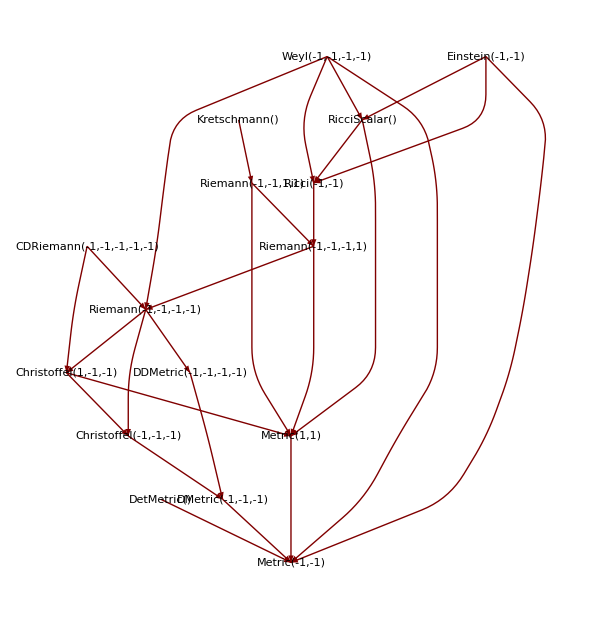

```mathematica
LayeredGraphPlot[%,VertexLabeling->True]
```

```mathematica
Thread[Rule[#,depends[#,{True,True}]]]&/@Depends[All,{True,True}]//Flatten//Union;
```

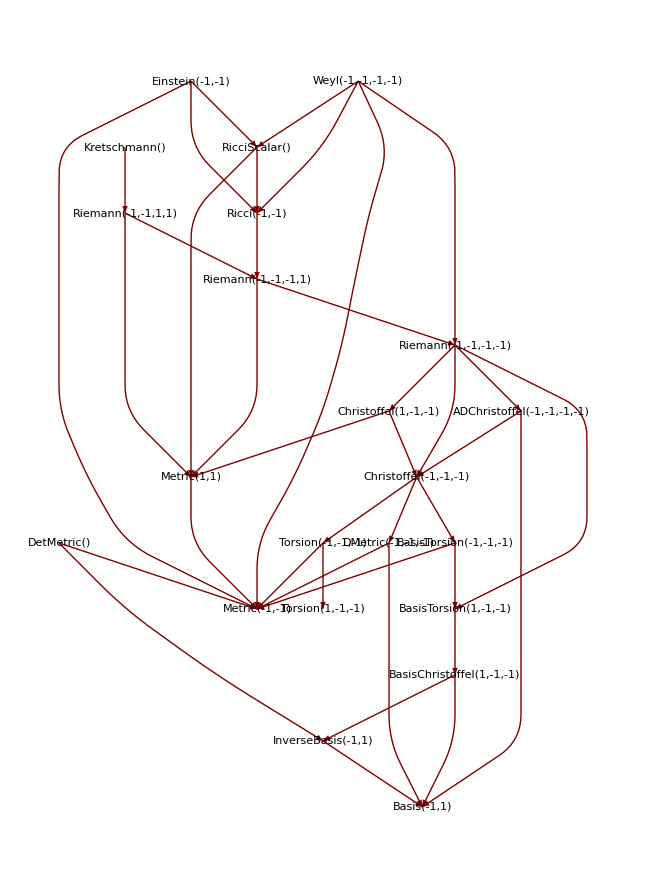

```mathematica
LayeredGraphPlot[%,VertexLabeling->True]
```

#### Examples with a symbolic metric

```mathematica
BeginExamples[]
```

```mathematica
DefChart[Spherical,M,{1,2},{θ[],ϕ[]},DefInfo->False]
```

```mathematica
MetricsOfVBundle[TangentM]
```

{}

```mathematica
DefMetric[1,metric[-a,-b],CD,DefInfo->False]
```

```mathematica
MetricInBasis[metric,-Spherical,{1,Sin[θ[]]^2}]
```

{{metric |   |  
1 | 1→1,metric |   |  
1 | 2→0},{metric |   |  
2 | 1→0,metric |   |  
2 | 2→Sin[θ]^2}}

```mathematica
TensorValues[metric]
```

FoldedRule[{metric |   |  
2 | 1→metric |   |  
1 | 2},{metric |   |  
1 | 1→1,metric |   |  
1 | 2→0,metric |   |  
2 | 2→Sin[θ]^2}]

```mathematica
MetricCompute[metric,Spherical,All]//Timing
```

** DefTensor: Defining weight +2 density DetmetricSpherical[]. Determinant.

** ReportCompute: DetMetric[]

Constructed in 0.00016 seconds

Applied Simplify in 0.00008 seconds

Caching information for DetMetric[]

Stored in 0.00029 seconds and 400 bytes

** ReportCompute: Metric[1,1]

Constructed in 0.00266 seconds

Applied Simplify in 0.00063 seconds

Caching information for Metric[1,1]

Stored in 0.00045 seconds and 1584 bytes

** ReportCompute: DMetric[-1,-1,-1]

Constructed in 0.00018 seconds

Applied Simplify in 0.00115 seconds

Caching information for DMetric[-1,-1,-1]

Stored in 0.00049 seconds and 5848 bytes

** ReportCompute: DDMetric[-1,-1,-1,-1]

Constructed in 0.00022 seconds

Applied Simplify in 0.00331 seconds

Caching information for DDMetric[-1,-1,-1,-1]

Stored in 0.00075 seconds and 16424 bytes

** ReportCompute: Christoffel[-1,-1,-1]

Constructed in 0.00014 seconds

** DefTensor: Defining tensor ChristoffelCDPDSpherical[a,-b,-c].

Applied Simplify in 0.00352 seconds

Caching information for Christoffel[-1,-1,-1]

Stored in 0.00052 seconds and 6160 bytes

** ReportCompute: Christoffel[1,-1,-1]

Constructed in 0.00021 seconds

Applied Simplify in 0.00128 seconds

Caching information for Christoffel[1,-1,-1]

Stored in 0.00051 seconds and 5296 bytes

** ReportCompute: Riemann[-1,-1,-1,-1]

Constructed in 0.00018 seconds

Applied Simplify in 0.00163 seconds

Caching information for Riemann[-1,-1,-1,-1]

Stored in 0.00154 seconds and 13968 bytes

** ReportCompute: Riemann[-1,-1,-1,1]

Constructed in 0.00034 seconds

Applied Simplify in 0.00152 seconds

Caching information for Riemann[-1,-1,-1,1]

Stored in 0.00178 seconds and 13384 bytes

** ReportCompute: Ricci[-1,-1]

Constructed in 0.00012 seconds

Applied Simplify in 0.00014 seconds

Caching information for Ricci[-1,-1]

Stored in 0.00317 seconds and 2304 bytes

** ReportCompute: RicciScalar[]

Constructed in 0.00008 seconds

Applied Simplify in 0.00006 seconds

Caching information for RicciScalar[]

Stored in 0.00028 seconds and 256 bytes

** ReportCompute: Einstein[-1,-1]

Constructed in 0.00008 seconds

Applied Simplify in 0.00012 seconds

Caching information for Einstein[-1,-1]

Stored in 0.00034 seconds and 520 bytes

** ReportCompute: Weyl[-1,-1,-1,-1]

Constructed in 0.00013 seconds

Applied Simplify in 0.00006 seconds

Caching information for Weyl[-1,-1,-1,-1]

Stored in 0.00059 seconds and 1672 bytes

** ReportCompute: Riemann[-1,-1,1,1]

Constructed in 0.00023 seconds

Applied Simplify in 0.0003 seconds

Caching information for Riemann[-1,-1,1,1]

Stored in 0.00158 seconds and 11088 bytes

** ReportCompute: Kretschmann[]

Constructed in 0.00013 seconds

Applied Simplify in 0.00007 seconds

Caching information for Kretschmann[]

Stored in 0.00028 seconds and 256 bytes

** ReportCompute: CDRiemann[-1,-1,-1,-1,-1]

Constructed in 0.0003 seconds

Applied Simplify in 0.00009 seconds

Caching information for CDRiemann[-1,-1,-1,-1,-1]

Stored in 0.00111 seconds and 33296 bytes

{0.08319,Null}

```mathematica
TensorValues[RicciCD]
```

FoldedRule[{R[▽] |   |  
2 | 1→R[▽] |   |  
1 | 2},{R[▽] |   |  
1 | 1→1,R[▽] |   |  
1 | 2→0,R[▽] |   |  
2 | 2→Sin[θ]^2}]

```mathematica
RicciScalarCD[]//ToValues
```

2

```mathematica
TensorValues[CDRiemannCD]
```

FoldedRule[{▽R[▽] |   |   |   |   |  
1 | 1 | 1 | 1 | 1→0,▽R[▽] |   |   |   |   |  
1 | 1 | 1 | 1 | 2→0,▽R[▽] |   |   |   |   |  
1 | 1 | 1 | 2 | 1→0,▽R[▽] |   |   |   |   |  
1 | 1 | 1 | 2 | 2→0,▽R[▽] |   |   |   |   |  
1 | 1 | 2 | 1 | 1→0,▽R[▽] |   |   |   |   |  
1 | 1 | 2 | 1 | 2→0,▽R[▽] |   |   |   |   |  
1 | 1 | 2 | 2 | 1→0,▽R[▽] |   |   |   |   |  
1 | 1 | 2 | 2 | 2→0,▽R[▽] |   |   |   |   |  
1 | 2 | 1 | 1 | 1→0,▽R[▽] |   |   |   |   |  
1 | 2 | 1 | 1 | 2→0,▽R[▽] |   |   |   |   |  
1 | 2 | 2 | 1 | 1→-▽R[▽] |   |   |   |   |  
1 | 2 | 1 | 2 | 1,▽R[▽] |   |   |   |   |  
1 | 2 | 2 | 1 | 2→-▽R[▽] |   |   |   |   |  
1 | 2 | 1 | 2 | 2,▽R[▽] |   |   |   |   |  
1 | 2 | 2 | 2 | 1→0,▽R[▽] |   |   |   |   |  
1 | 2 | 2 | 2 | 2→0,▽R[▽] |   |   |   |   |  
2 | 1 | 1 | 1 | 1→0,▽R[▽] |   |   |   |   |  
2 | 1 | 1 | 1 | 2→0,▽R[▽] |   |   |   |   |  
2 | 1 | 1 | 2 | 1→-▽R[▽] |   |   |   |   |  
1 | 2 | 1 | 2 | 1,▽R[▽] |   |   |   |   |  
2 | 1 | 1 | 2 | 2→-▽R[▽] |   |   |   |   |  
1 | 2 | 1 | 2 | 2,▽R[▽] |   |   |   |   |  
2 | 1 | 2 | 1 | 1→▽R[▽] |   |   |   |   |  
1 | 2 | 1 | 2 | 1,▽R[▽] |   |   |   |   |  
2 | 1 | 2 | 1 | 2→▽R[▽] |   |   |   |   |  
1 | 2 | 1 | 2 | 2,▽R[▽] |   |   |   |   |  
2 | 1 | 2 | 2 | 1→0,▽R[▽] |   |   |   |   |  
2 | 1 | 2 | 2 | 2→0,▽R[▽] |   |   |   |   |  
2 | 2 | 1 | 1 | 1→0,▽R[▽] |   |   |   |   |  
2 | 2 | 1 | 1 | 2→0,▽R[▽] |   |   |   |   |  
2 | 2 | 1 | 2 | 1→0,▽R[▽] |   |   |   |   |  
2 | 2 | 1 | 2 | 2→0,▽R[▽] |   |   |   |   |  
2 | 2 | 2 | 1 | 1→0,▽R[▽] |   |   |   |   |  
2 | 2 | 2 | 1 | 2→0,▽R[▽] |   |   |   |   |  
2 | 2 | 2 | 2 | 1→0,▽R[▽] |   |   |   |   |  
2 | 2 | 2 | 2 | 2→0},{▽R[▽] |   |   |   |   |  
1 | 2 | 1 | 2 | 1→0,▽R[▽] |   |   |   |   |  
1 | 2 | 1 | 2 | 2→0}]

```mathematica
UndefMetric[metric]
```

** UndefTensor: Undefined weight +2 density DetmetricSpherical

** UndefTensor: Undefined tensor ChristoffelCDPDSpherical

```mathematica
UndefBasis[Spherical]
```

```mathematica
ClearxCobaCache[All]
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$61389,z$61389$,z$61390,z$61390$,z$61391,z$61391$,z$61392,z$61392$,z$61393,z$61393$,z$61394,z$61394$,z$61395,z$61395$,z$61396,z$61396$,z$61397,z$61397$,z$61398,z$61398$,z$61399,z$61399$,z$61400,z$61400$,z$61401,z$61401$,z$61402,z$61402$,z$61466,z$61467,z$61468,z$61469,z$61477,z$61478,z$61486,z$61487,z$61488,z$61520,z$61521,z$61522,z$61536,z$61537,z$61538,z$61542,z$61543,z$61544,z$61545,z$61599,z$61600,z$61601,z$61602,z$61603}

### 7.3. CTensor curvature computations

#### 7.3.0. Comments

Metric determinants, inversions and Christoffels have been already done before.

We cannot use automatic raising and lowering of indices because that will use the first-metric, which perhaps is not the metric we need to do the computations. For example in order to compute Weyl[ccovd] we need to use RiemannDown[ccovd] and not the lowered-last-index Riemann[ccovd] because RiemannDown will always use the correct metric, and not the lowering of the index.

We require that metric fields live on the tangent bundle, so it is not clear how to generalize this function to inner connections. Probably that must be done using a ConnectionCompute.

Generalize to include the computation of ExtrinsicK, Acceleration and Projector for induced metrics. How do we denote that a CTensor is an induced metric? How do we associate to it the orthogonal vector? Probably this must be done by SetCMetric.

#### 7.3.1. LC / CovDOfMetric

We need the Christoffel between two connections as second argument of CCovD, but we also need covds as arguments of Christoffel. So there is some circular argumentation here... Note in this computation how we extract the index-free tensor from a computation that was performed with indices. The indices are hence fully local, and in fact this should be combined with some form of localization:

We could do this without indices. It would be slightly faster, but more difficult to read. In particular we could perform the derivative of metric only once:

```mathematica
MetricChristoffel[metric:CTensor[_,{-basis_,-basis_},0],pd_]:=Module[{a,b,c,d,torsion,mtorsion,invmetric},
{a,b,c,d}=GetIndicesOfVBundle[VBundleOfMetric[metric],4];
torsion=ToCTensor[Torsion[pd],{basis,-basis,-basis}];
mtorsion=CTensorContract[metric,torsion,{2,1},Times];
invmetric=Inv[metric];
HeadOfTensor[
1/2invmetric[a,d](pd[-b][metric[-c,-d]]+pd[-c][metric[-b,-d]]-pd[-d][metric[-b,-c]])+$TorsionSign/2invmetric[a,d](mtorsion[-b,-c,-d]+mtorsion[-c,-b,-d]-mtorsion[-d,-b,-c]),
{a,-b,-c}]
];
```

```mathematica
(computation:LC[metric:CTensor[_?MatrixQ,{-basis_,-basis_},0]])^:=xCobaCache[
computation,
With[{pd=PDOfBasis[basis]},CCovD[pd,MetricChristoffel[metric,pd],metric]]
];
```

If we specify a torsion tensor in CovDOfMetric then start with the Levi-Civita connection and add the needed terms:

```mathematica
AddTorsionToCCovD[CCovD[pd_,christoffel_,metric_],torsion_]:=Module[{a,b,c,d,invmetric,mtorsion},
{a,b,c,d}=GetIndicesOfVBundle[VBundleOfMetric[metric],4];
mtorsion=CTensorContract[metric,torsion,{2,1},Times];
invmetric=Inv[metric];
CCovD[pd,
HeadOfTensor[
christoffel[a,-b,-c]-$TorsionSign/2invmetric[a,d](mtorsion[-b,-c,-d]+mtorsion[-c,-b,-d]-mtorsion[-d,-b,-c]),
{a,-b,-c}],
metric]
];
```

```mathematica
(computation:CovDOfMetric[metric:CTensor[_?MatrixQ,{-basis_,-basis_},0],torsion_])^:=xCobaCache[
computation,
AddTorsionToCCovD[LC[metric],torsion]
];
```

With no additional information we assume that CovDOfMetric returns the Levi-Civita connection:

```mathematica
(computation:CovDOfMetric[metric_CTensor])^:=xCobaCache[
computation,
LC[metric]
];
```

#### Examples of MetricCompute with an explicit metric

```mathematica
BeginExamples[]
```

```mathematica
DefChart[Spherical,M,{1,2},{θ[],ϕ[]},DefInfo->False]
```

```mathematica
metric=CTensor[{{1,0},{0,Sin[θ[]]^2}},{-Spherical,-Spherical}]
```

CTensor[{{1,0},{0,Sin[θ]^2}},{-Spherical,-Spherical},0]

```mathematica
MetricsOfVBundle[TangentM]^={metric};
```

```mathematica
MetricCompute[metric,Spherical,All]//Timing
```

** ReportCompute: DetMetric[]

Constructed in 0.00009 seconds

Applied Simplify in 0.00061 seconds

Caching information for DetMetric[]

Caching information for Determinant

Stored in 0.00017 seconds and 208 bytes

** ReportCompute: Metric[1,1]

Constructed in 0.00281 seconds

Applied Simplify in 0.00049 seconds

Caching information for Metric[1,1]

Caching information for Inv

Stored in 0.00021 seconds and 280 bytes

** ReportCompute: DMetric[-1,-1,-1]

Constructed in 0.00016 seconds

Applied Simplify in 0.00085 seconds

Caching information for DMetric[-1,-1,-1]

** ReportCompute: DDMetric[-1,-1,-1,-1]

Constructed in 0.00019 seconds

Applied Simplify in 0.00247 seconds

Caching information for DDMetric[-1,-1,-1,-1]

** ReportCompute: Christoffel[-1,-1,-1]

Constructed in 0.00014 seconds

Applied Simplify in 0.00333 seconds

Caching information for Christoffel[-1,-1,-1]

** ReportCompute: Christoffel[1,-1,-1]

Constructed in 0.0002 seconds

Applied Simplify in 0.00124 seconds

Caching information for Christoffel[1,-1,-1]

** ReportCompute: CovDOfMetric

Caching information for Christoffel

Caching information for CovDOfMetric

** ReportCompute: Riemann[-1,-1,-1,-1]

Constructed in 0.00018 seconds

Applied Simplify in 0.00206 seconds

Caching information for Riemann[-1,-1,-1,-1]

Caching information for RiemannDown

Stored in 0.00031 seconds and 1152 bytes

** ReportCompute: Riemann[-1,-1,-1,1]

Constructed in 0.00031 seconds

Applied Simplify in 0.00303 seconds

Caching information for Riemann[-1,-1,-1,1]

Caching information for Riemann

Stored in 0.00032 seconds and 792 bytes

** ReportCompute: Ricci[-1,-1]

Constructed in 0.00011 seconds

Applied Simplify in 0.00013 seconds

Caching information for Ricci[-1,-1]

Caching information for Ricci

Stored in 0.0002 seconds and 280 bytes

** ReportCompute: RicciScalar[]

Constructed in 0.00007 seconds

Applied Simplify in 0.00006 seconds

Caching information for RicciScalar[]

Caching information for RicciScalar

Stored in 0.00021 seconds and 64 bytes

** ReportCompute: Einstein[-1,-1]

Constructed in 0.00008 seconds

Applied Simplify in 0.00012 seconds

Caching information for Einstein[-1,-1]

Caching information for Einstein

Stored in 0.00018 seconds and 136 bytes

** ReportCompute: Weyl[-1,-1,-1,-1]

Constructed in 0.0001 seconds

Applied Simplify in 0.00007 seconds

Caching information for Weyl[-1,-1,-1,-1]

Caching information for Weyl

Stored in 0.00025 seconds and 432 bytes

** ReportCompute: Riemann[-1,-1,1,1]

Constructed in 0.00023 seconds

Using internal cache for Inv

Applied Simplify in 0.00048 seconds

Caching information for Riemann[-1,-1,1,1]

Caching information for ToCTensorOneSlot

Stored in 0.00028 seconds and 432 bytes

** ReportCompute: Kretschmann[]

Constructed in 0.00012 seconds

Applied Simplify in 0.00006 seconds

Caching information for Kretschmann[]

Caching information for Kretschmann

Stored in 0.00017 seconds and 64 bytes

** ReportCompute: CDRiemann[-1,-1,-1,-1,-1]

Constructed in 0.00029 seconds

Applied Simplify in 0.0001 seconds

Caching information for CDRiemann[-1,-1,-1,-1,-1]

Caching information for TensorDerivative

Stored in 0.00035 seconds and 832 bytes

{0.04227,Null}

```mathematica
ccovd=CovDOfMetric[metric]
```

Using internal cache for CovDOfMetric

CCovD[PDSpherical,CTensor[{{{0,0},{0,-Cos[θ] Sin[θ]}},{{0,Cot[θ]},{Cot[θ],0}}},{Spherical,-Spherical,-Spherical},0],CTensor[{{1,0},{0,Sin[θ]^2}},{-Spherical,-Spherical},0]]

```mathematica
UndefBasis[Spherical]
```

```mathematica
MetricsOfVBundle[TangentM]^={};
```

```mathematica
Remove[metric,ccovd]
```

```mathematica
ClearxCobaCache[All]
```

```mathematica
EndExamples[]
```

#### 7.3.2. Torsion

We ignore the metric in this computation, because we might have a connection which is associated to a metric, but still is not torsionless.

```mathematica
PDCTorsion[pd_,christoffel_]:=Module[{torsion=Torsion[pd]},
If[torsion[Null,Null,Null]===0,
Zero,
ToCTensor[torsion,CTensorBases[christoffel]]
]
];
```

```mathematica
(computation:Torsion[CCovD[pd_,christoffel_CTensor,metric_]])^:=xCobaCache[
computation,
PDCTorsion[pd,christoffel]+$TorsionSign(christoffel-CTensorTranspose[christoffel,Images[{1,3,2}]])
];
```

#### 7.3.3. Riemann / RiemannDown

We can construct the Riemann tensor of the connection using

```mathematica
(computation:Riemann[CCovD[pd_,christoffel_,metric_]])^:=xCobaCache[
computation,
Module[{a,b,c,d,e},
{a,b,c,d,e}=GetIndicesOfVBundle[First@VBundlesOfCovD[pd],5];
HeadOfTensor[$RiemannSign(
pd[-b][christoffel[d,-a,-c]]-pd[-a][christoffel[d,-b,-c]]+christoffel[d,-b,-e]christoffel[e,-a,-c]-christoffel[d,-a,-e]christoffel[e,-b,-c]-$TorsionSign PDCTorsion[pd,christoffel][e,-a,-b]christoffel[d,-e,-c]),
{-a,-b,-c,d}]
]
];
```

Again, it should be possible to do this faster, making use of the symmetry, and withoud indices, and performing the derivative and product of Christoffels only once.

```mathematica
(computation:RiemannDown[ccovd:CCovD[pd_,christoffel_,metric_]])^:=xCobaCache[
computation,
CTensorContract[Riemann[ccovd],metric,{4,1},Times]
];
```

#### 7.3.4. Ricci / TFRicci

```mathematica
(computation:Ricci[ccovd_CCovD])^:=xCobaCache[
computation,
$RicciSign CTensorContract[Riemann[ccovd],{2,4}]
];
```

```mathematica
(computation:TFRicci[ccovd:CCovD[_,_,metric_]])^:=xCobaCache[
computation,
Ricci[ccovd]-metric RicciScalar[ccovd]/Length[CTensorArray[metric]]
]/;metric=!=Null||Throw[Message[Einstein::metcon,"TFRicci"]];
```

#### 7.3.5. RicciScalar

```mathematica
General::metcon="`1` can only be computed for a metric connection.";
```

```mathematica
(computation:RicciScalar[ccovd:CCovD[_,_,metric_]])^:=xCobaCache[
computation,
CTensorContract[CTensorContract[Ricci[ccovd],Inv[metric],{2,1},Times],{1,2}]
]/;metric=!=Null||Throw[Message[RicciScalar::metcon,"RicciScalar"]];
```

#### 7.3.6. Einstein

```mathematica
(computation:Einstein[ccovd:CCovD[_,_,metric_]])^:=xCobaCache[
computation,
Ricci[ccovd]-metric RicciScalar[ccovd]/2
]/;metric=!=Null||Throw[Message[Einstein::metcon,"Einstein"]];
```

#### 7.3.7. Weyl

```mathematica
(computation:Weyl[ccovd:CCovD[pd_,_,metric_]])^:=xCobaCache[
computation,
Module[{vbundle,a,b,c,d,dim,ricci,ricciscalar},
vbundle=First@VBundlesOfCovD[pd];
{a,b,c,d}=GetIndicesOfVBundle[vbundle,4];
dim=DimOfVBundle[vbundle];
ricci=Ricci[ccovd];
ricciscalar=RicciScalar[ccovd];
HeadOfTensor[
RiemannDown[ccovd][-a,-b,-c,-d]+(metric[-c,-b]ricci[-a,-d]+metric[-d,-a]ricci[-b,-c]-metric[-d,-b]ricci[-a,-c]-metric[-c,-a]ricci[-b,-d])/(dim-2)+(metric[-a,-c]metric[-b,-d]-metric[-a,-d]metric[-b,-c])ricciscalar[]/((dim-1)(dim-2)),
{-a,-b,-c,-d}
]	
]
]/;metric=!=Null||Throw[Message[Weyl::metcon,"Weyl"]];
```

#### 7.3.8. Kretschmann

Fixed indices generation as reported by Leo in the forum (September 8, 2015).

```mathematica
(computation:Kretschmann[ccovd:CCovD[pd_,_,metric_]])^:=xCobaCache[
computation,
Module[{a,b,c,d},
{a,b,c,d}=GetIndicesOfVBundle[First@VBundlesOfCovD[pd],4];
CTensor[Riemann[ccovd][-a,-b,c,d]Riemann[ccovd][-c,-d,a,b],{},0]
]
]/;metric=!=Null||Throw[Message[Kretschmann::metcon,"Kretschmann"]];
```

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefChart[Polar,M,{1,2},{r[],θ[]},DefInfo->False]
```

```mathematica
metric=CTensor[{{1,0},{0,r[]^2}},{-Polar,-Polar}];
```

```mathematica
MetricsOfVBundle[TangentM]^={metric};
```

```mathematica
metric[-a,-b]
```

(1 | 0
0 | r^2) |   |  
a | b

```mathematica
metric[a,b]
```

Caching information for Inv

Using internal cache for Inv

Caching information for ToCTensorOneSlot

Caching information for ToCTensorOneSlot

(1 | 0
0 | 1/r^2) | a | b
  |

```mathematica
xACP`MetricChristoffel[metric,PDPolar]
```

Using internal cache for Inv

Converting a first order derivative of a CTensor into a TensorDerivative expression

Performing PDPolar TensorDerivative of a CTensor

Converting a first order derivative of a CTensor into a TensorDerivative expression

Performing PDPolar TensorDerivative of a CTensor

Converting a first order derivative of a CTensor into a TensorDerivative expression

Performing PDPolar TensorDerivative of a CTensor

CTensor[{{{0,0},{0,-r}},{{0,1/r},{1/r,0}}},{Polar,-Polar,-Polar},0]

```mathematica
covd=CovDOfMetric[metric]
```

Using internal cache for Inv

Converting a first order derivative of a CTensor into a TensorDerivative expression

Performing PDPolar TensorDerivative of a CTensor

Converting a first order derivative of a CTensor into a TensorDerivative expression

Performing PDPolar TensorDerivative of a CTensor

Converting a first order derivative of a CTensor into a TensorDerivative expression

Performing PDPolar TensorDerivative of a CTensor

Caching information for LC

Caching information for CovDOfMetric

CCovD[PDPolar,CTensor[{{{0,0},{0,-r}},{{0,1/r},{1/r,0}}},{Polar,-Polar,-Polar},0],CTensor[{{1,0},{0,r^2}},{-Polar,-Polar},0]]

```mathematica
Riemann[covd][-a,-b,-c,-d]
```

Converting a first order derivative of a CTensor into a TensorDerivative expression

Performing PDPolar TensorDerivative of a CTensor

Converting a first order derivative of a CTensor into a TensorDerivative expression

Performing PDPolar TensorDerivative of a CTensor

Caching information for Riemann

0

```mathematica
TensorDerivative[metric,covd][-a,-b,-c]
```

Performing PDPolar TensorDerivative of a CTensor

Caching information for TensorDerivative

0

```mathematica
UndefChart[Polar]
```

```mathematica
MetricsOfVBundle[TangentM]^={};
```

```mathematica
Remove[metric,covd]
```

```mathematica
ClearxCobaCache[All]
```

```mathematica
EndExamples[]
```

### 7.A. OLD AND PROBABLY USELESS: Direct algorithms: linear combinations to linear combinations

A private utility function:

```mathematica
collect[expr_,basis_,inds_,f_]:=Collect[expr,Flatten[BasisArray[basis]@@inds],f];
```

#### 7.A.1. InverseMetric

First we compute the inverse of a metric in a given basis:

```mathematica
?InverseMetric
```

InverseMetric[g[-a, -b], B][c, d] returns the inverse of the metric g[-a, -b], expressed as an abstract tensor with upper indices c, d. The result is computed using the components of the metric g in the basis B.

```mathematica
Options[InverseMetric]={CVSimplify:>$CVSimplify};
InverseMetric[metric_,basis_,options:OptionsPattern[]][a_?UpIndexQ,b_?UpIndexQ]:=With[{matrix=ComponentArray[ToBasis[basis][metric]],cvsimplify=OptionValue[InverseMetric,{options},CVSimplify]},collect[Plus@@(Plus@@(Inverse[cvsimplify@matrix]BasisArray[basis,basis][a,b])),basis,IndexList[a,b],cvsimplify]
];
```

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
DefBasis[polar,TangentM,{1,2},DefInfo->False]
```

```mathematica
DefMetric[1,metric[-a,-b],CD,DefInfo->False]
```

General case:

```mathematica
imet=InverseMetric[metric[-a,-b],polar][b,c]
```

** DefTensor: Defining weight +2 density Detmetricpolar[]. Determinant.

(e |   | b
1 |   e |   | c
2 |   metric |   |  
1 | 2)/(metric |   |  
1 | 2 metric |   |  
2 | 1-metric |   |  
1 | 1 metric |   |  
2 | 2)+(e |   | c
1 |   e |   | b
2 |   metric |   |  
2 | 1)/(metric |   |  
1 | 2 metric |   |  
2 | 1-metric |   |  
1 | 1 metric |   |  
2 | 2)+(e |   | b
2 |   e |   | c
2 |   metric |   |  
1 | 1)/(-metric |   |  
1 | 2 metric |   |  
2 | 1+metric |   |  
1 | 1 metric |   |  
2 | 2)+(e |   | b
1 |   e |   | c
1 |   metric |   |  
2 | 2)/(-metric |   |  
1 | 2 metric |   |  
2 | 1+metric |   |  
1 | 1 metric |   |  
2 | 2)

```mathematica
IndexCoefficient[imet,polar]
```

{{(metric |   |  
2 | 2)/(-metric |   |  
1 | 2 metric |   |  
2 | 1+metric |   |  
1 | 1 metric |   |  
2 | 2),(metric |   |  
1 | 2)/(metric |   |  
1 | 2 metric |   |  
2 | 1-metric |   |  
1 | 1 metric |   |  
2 | 2)},{(metric |   |  
2 | 1)/(metric |   |  
1 | 2 metric |   |  
2 | 1-metric |   |  
1 | 1 metric |   |  
2 | 2),(metric |   |  
1 | 1)/(-metric |   |  
1 | 2 metric |   |  
2 | 1+metric |   |  
1 | 1 metric |   |  
2 | 2)}}

```mathematica
met=SeparateBasis[polar][metric[-a,-b]]//TraceBasisDummy
```

e |   | 1
a |   e |   | 1
b |   metric |   |  
1 | 1+e |   | 1
a |   e |   | 2
b |   metric |   |  
1 | 2+e |   | 2
a |   e |   | 1
b |   metric |   |  
2 | 1+e |   | 2
a |   e |   | 2
b |   metric |   |  
2 | 2

```mathematica
IndexCoefficient[met,polar]
```

{{metric |   |  
1 | 1,metric |   |  
1 | 2},{metric |   |  
2 | 1,metric |   |  
2 | 2}}

```mathematica
met imet//ContractBasis
```

(e |   | 1
a |   e |   | c
2 |   metric |   |  
1 | 1 metric |   |  
1 | 2)/(metric |   |  
1 | 2 metric |   |  
2 | 1-metric |   |  
1 | 1 metric |   |  
2 | 2)+(e |   | 1
a |   e |   | c
1 |   metric |   |  
1 | 2 metric |   |  
2 | 1)/(metric |   |  
1 | 2 metric |   |  
2 | 1-metric |   |  
1 | 1 metric |   |  
2 | 2)+(e |   | 2
a |   e |   | c
2 |   metric |   |  
1 | 2 metric |   |  
2 | 1)/(metric |   |  
1 | 2 metric |   |  
2 | 1-metric |   |  
1 | 1 metric |   |  
2 | 2)+(e |   | 2
a |   e |   | c
1 |   metric |   |  
2 | 1 metric |   |  
2 | 2)/(metric |   |  
1 | 2 metric |   |  
2 | 1-metric |   |  
1 | 1 metric |   |  
2 | 2)+(e |   | 1
a |   e |   | c
2 |   metric |   |  
1 | 1 metric |   |  
1 | 2)/(-metric |   |  
1 | 2 metric |   |  
2 | 1+metric |   |  
1 | 1 metric |   |  
2 | 2)+(e |   | 1
a |   e |   | c
1 |   metric |   |  
1 | 1 metric |   |  
2 | 2)/(-metric |   |  
1 | 2 metric |   |  
2 | 1+metric |   |  
1 | 1 metric |   |  
2 | 2)+(e |   | 2
a |   e |   | c
2 |   metric |   |  
1 | 1 metric |   |  
2 | 2)/(-metric |   |  
1 | 2 metric |   |  
2 | 1+metric |   |  
1 | 1 metric |   |  
2 | 2)+(e |   | 2
a |   e |   | c
1 |   metric |   |  
2 | 1 metric |   |  
2 | 2)/(-metric |   |  
1 | 2 metric |   |  
2 | 1+metric |   |  
1 | 1 metric |   |  
2 | 2)

```mathematica
%//Simplify
```

e |   | 1
a |   e |   | c
1 |  +e |   | 2
a |   e |   | c
2 |

Particular case:

```mathematica
met=3Basis[-a,{1,polar}]Basis[-b,{1,polar}]+5Basis[-a,{2,polar}]Basis[-b,{2,polar}]+4(Basis[-a,{1,polar}]Basis[-b,{2,polar}]+Basis[-a,{2,polar}]Basis[-b,{1,polar}])
```

3 e |   | 1
a |   e |   | 1
b |  +5 e |   | 2
a |   e |   | 2
b |  +4 (e |   | 2
a |   e |   | 1
b |  +e |   | 1
a |   e |   | 2
b |  )

```mathematica
imet=InverseMetric[%,polar][b,c]
```

-5 e |   | b
1 |   e |   | c
1 |  +4 e |   | c
1 |   e |   | b
2 |  +4 e |   | b
1 |   e |   | c
2 |  -3 e |   | b
2 |   e |   | c
2 |

```mathematica
met imet//ContractBasis
```

e |   | 1
a |   e |   | c
1 |  +e |   | 2
a |   e |   | c
2 |

```mathematica
UndefMetric[metric]
```

** UndefTensor: Undefined weight +2 density Detmetricpolar

```mathematica
UndefBasis[polar]
```

```mathematica
Remove[met,imet]
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{z$62389,z$62389$,z$62390,z$62390$,z$62391,z$62391$,z$62392,z$62392$,z$62393,z$62393$,z$62394,z$62394$,z$62395,z$62395$,z$62396,z$62396$,z$62397,z$62397$,z$62398,z$62398$,z$62399,z$62399$,z$62400,z$62400$,z$62401,z$62401$,z$62402,z$62402$,z$62466,z$62467,z$62468,z$62469,z$62477,z$62478,z$62486,z$62487,z$62488,z$62492,z$62493,z$62498,z$62499,z$62500,z$62501,z$62503,z$62504,z$62506,z$62507,z$62509,z$62510}

#### 7.A.2. ChristoffelFromMetric

We are missing torsion tensors in this expression. In this expression we assume that metric is an expression for the metric with two covariant abstract indices. It can be the metric g[-a,-b] or an expansion in terms of some basis (not necessarily the basis given as second argument):

```mathematica
Options[ChristoffelFromMetric]={CVSimplify:>$CVSimplify};
ChristoffelFromMetric[metric_,basis_,options:OptionsPattern[]][a_,b_,c_]:=With[{vbundle=VBundleOfIndex[a]},With[{PDbasis=PDOfBasis[basis],
VBmetric=xAct`xTensor`Private`FirstMetricOfVBundle[vbundle],
dummy1=DummyIn[vbundle,basis],
dummy2=DummyIn[vbundle,basis],
dummy3=DummyIn[vbundle,basis],
dummy4=DummyIn[vbundle,basis],
frees=List@@FindFreeIndices[metric],cvsimplify=OptionValue[ChristoffelFromMetric,{options},CVSimplify]},
collect[ToValues@ContractBasis@With[{newmetric=ReplaceIndex[metric,Thread[frees->{-dummy3,-dummy4}]]},
TraceBasisDummy[ToValues[
VBmetric[a,-dummy1]VBmetric[b,dummy2]VBmetric[c,dummy3]1/2InverseMetric[metric,basis,options][dummy1,dummy4](PDbasis[-dummy2][newmetric]
+PDbasis[-dummy3][newmetric/.-dummy3->-dummy2]
-PDbasis[-dummy4][newmetric/.-dummy4->-dummy2])],
IndexList[dummy1,dummy2,dummy3,dummy4]]
],
basis,IndexList[a,b,c],cvsimplify]
]
];
```

#### 7.A.3. RiemannFromChristoffel

Here we are also missing torsion tensors. We assume an initial configuration up-down-down for the Christoffel.

```mathematica
Options[RiemannFromChristoffel]={CVSimplify:>$CVSimplify};
RiemannFromChristoffel[christoffel_,basis_,options:OptionsPattern[]][a_,b_,c_,d_]:=With[{vbundle=VBundleOfIndex[a],inds=List@@FindFreeIndices[christoffel]},
With[{PDbasis=PDOfBasis[basis],
VBmetric=xAct`xTensor`Private`FirstMetricOfVBundle[vbundle],
dummy1=DummyIn[vbundle,basis],
dummy2=DummyIn[vbundle,basis],
dummy3=DummyIn[vbundle,basis],
dummy4=DummyIn[vbundle,basis],
dummy5=DummyIn[vbundle,basis],
cvsimplify=OptionValue[RiemannFromChristoffel,{options},CVSimplify]},
With[{newchristoffel=ReplaceIndex[christoffel,Thread[inds->{dummy4,-dummy1,-dummy3}]]},collect[ToValues@ContractBasis@TraceBasisDummy[ToValues[$RiemannSign
VBmetric[a,dummy1]VBmetric[b,dummy2]VBmetric[c,dummy3]VBmetric[d,-dummy4](PDbasis[-dummy2][newchristoffel]
-PDbasis[-dummy1][newchristoffel/.-dummy1->-dummy2]
+(newchristoffel/.{-dummy1->-dummy2,-dummy3->-dummy5})(newchristoffel/.dummy4->dummy5)
-(newchristoffel/.-dummy3->-dummy5)(newchristoffel/.{dummy4->dummy5,-dummy1->-dummy2}))],IndexList[dummy1,dummy2,dummy3,dummy4,dummy5]],
basis,IndexList[a,b,c,d],cvsimplify]
]
]
];
```

#### Example: Schwarzschild metric

```mathematica
BeginExamples[]
```

Define objects:

```mathematica
DefManifold[M4,4,{α,β,γ,δ,μ,ν,λ}]
```

** DefManifold: Defining manifold M4.

** DefVBundle: Defining vbundle TangentM4.

```mathematica
DefMetric[-1,metric[-α,-β],CD]
```

** DefTensor: Defining symmetric metric tensor metric[-α,-β].

** DefTensor: Defining antisymmetric tensor epsilonmetric[-α,-β,-γ,-δ].

** DefTensor: Defining tetrametric Tetrametric[-α,-β,-γ,-δ].

** DefTensor: Defining tetrametric Tetrametric†[-α,-β,-γ,-δ].

** DefCovD: Defining covariant derivative CD[-α].

** DefTensor: Defining vanishing torsion tensor TorsionCD[α,-β,-γ].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[α,-β,-γ].

** DefTensor: Defining Riemann tensor RiemannCD[-α,-β,-γ,-δ].

** DefTensor: Defining symmetric Ricci tensor RicciCD[-α,-β].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCD[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCD[-α,-β].

** DefTensor: Defining Weyl tensor WeylCD[-α,-β,-γ,-δ].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCD[-α,-β].

** DefTensor: Defining Kretschmann scalar KretschmannCD[].

** DefCovD:  Computing RiemannToWeylRules for dim 4

** DefCovD:  Computing RicciToTFRicci for dim 4

** DefCovD:  Computing RicciToEinsteinRules for dim 4

** DefTensor: Defining weight +2 density Detmetric[]. Determinant.

```mathematica
DefConstantSymbol[Mass,PrintAs->"M"]
```

** DefConstantSymbol: Defining constant symbol Mass.

```mathematica
DefChart[Sch,M4,{0,1,2,3},{t[],r[],θ[],ϕ[]}]
```

** DefTensor: Defining coordinate scalar t[].

** DefTensor: Defining coordinate scalar r[].

** DefTensor: Defining coordinate scalar θ[].

** DefTensor: Defining coordinate scalar ϕ[].

** DefBasis: Defining basis Sch.

** DefCovD: Defining parallel derivative PDSch[-α].

** DefTensor: Defining vanishing torsion tensor TorsionPDSch[α,-β,-γ].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDSch[α,-β,-γ].

** DefTensor: Defining vanishing Riemann tensor RiemannPDSch[-α,-β,-γ,δ].

** DefTensor: Defining vanishing Ricci tensor RicciPDSch[-α,-β].

** DefTensor: Defining antisymmetric +1 density etaUpSch[α,β,γ,δ].

** DefTensor: Defining antisymmetric -1 density etaDownSch[-α,-β,-γ,-δ].

Metric in expanded form:

```mathematica
met=-(1-2Mass/r[])Basis[-α,{0,Sch}]Basis[-β,{0,Sch}]+1/(1-2Mass/r[])Basis[-α,{1,Sch}]Basis[-β,{1,Sch}]+r[]^2(Basis[-α,{2,Sch}]Basis[-β,{2,Sch}]+Sin[θ[]]^2Basis[-α,{3,Sch}]Basis[-β,{3,Sch}])
```

(e |   | 1
α |   e |   | 1
β |)/(1-(2 M)/r)+e |   | 0
α |   e |   | 0
β |   (-1+(2 M)/r)+r^2 (e |   | 2
α |   e |   | 2
β |  +e |   | 3
α |   e |   | 3
β |   Sin[θ]^2)

Inverse metric:

```mathematica
AbsoluteTiming[imet=InverseMetric[met,Sch][β,γ]]
```

** DefTensor: Defining weight +2 density DetmetricSch[]. Determinant.

{0.05018,e |   | β
1 |   e |   | γ
1 |   (1-(2 M)/r)+(e |   | β
2 |   e |   | γ
2 |)/r^2+(e |   | β
3 |   e |   | γ
3 |   Csc[θ]^2)/r^2+(e |   | β
0 |   e |   | γ
0 |   r)/(2 M-r)}

```mathematica
met imet//ContractBasis//Simplify
```

e |   | 0
α |   e |   | γ
0 |  +e |   | 1
α |   e |   | γ
1 |  +e |   | 2
α |   e |   | γ
2 |  +e |   | 3
α |   e |   | γ
3 |

Store the metric components to compute the Christoffel:

```mathematica
MetricInBasis[metric,-Sch,{-(1-2Mass/r[]),1/(1-2Mass/ r[]),r[]^2,r[]^2Sin[θ[]]^2}]
```

{{metric |   |  
0 | 0→-1+(2 M)/r,metric |   |  
0 | 1→0,metric |   |  
0 | 2→0,metric |   |  
0 | 3→0},{metric |   |  
1 | 0→0,metric |   |  
1 | 1→1/(1-(2 M)/r),metric |   |  
1 | 2→0,metric |   |  
1 | 3→0},{metric |   |  
2 | 0→0,metric |   |  
2 | 1→0,metric |   |  
2 | 2→r^2,metric |   |  
2 | 3→0},{metric |   |  
3 | 0→0,metric |   |  
3 | 1→0,metric |   |  
3 | 2→0,metric |   |  
3 | 3→r^2 Sin[θ]^2}}

```mathematica
MetricInBasis[metric,Sch,Inverse[Map[Last,%,{2}]]]
```

{{metric | 0 | 0
  |  →r/(2 M-r),metric | 0 | 1
  |  →0,metric | 0 | 2
  |  →0,metric | 0 | 3
  |  →0},{metric | 1 | 0
  |  →0,metric | 1 | 1
  |  →1-(2 M)/r,metric | 1 | 2
  |  →0,metric | 1 | 3
  |  →0},{metric | 2 | 0
  |  →0,metric | 2 | 1
  |  →0,metric | 2 | 2
  |  →1/r^2,metric | 2 | 3
  |  →0},{metric | 3 | 0
  |  →0,metric | 3 | 1
  |  →0,metric | 3 | 2
  |  →0,metric | 3 | 3
  |  →Csc[θ]^2/r^2}}

Again we have:

```mathematica
TensorValues[metric]
```

FoldedRule[{metric | 1 | 0
  |  →metric | 0 | 1
  |  ,metric | 2 | 0
  |  →metric | 0 | 2
  |  ,metric | 2 | 1
  |  →metric | 1 | 2
  |  ,metric | 3 | 0
  |  →metric | 0 | 3
  |  ,metric | 3 | 1
  |  →metric | 1 | 3
  |  ,metric | 3 | 2
  |  →metric | 2 | 3
  |  },{metric | 0 | 0
  |  →r/(2 M-r),metric | 0 | 1
  |  →0,metric | 0 | 2
  |  →0,metric | 0 | 3
  |  →0,metric | 1 | 1
  |  →1-(2 M)/r,metric | 1 | 2
  |  →0,metric | 1 | 3
  |  →0,metric | 2 | 2
  |  →1/r^2,metric | 2 | 3
  |  →0,metric | 3 | 3
  |  →Csc[θ]^2/r^2},{metric |   |  
1 | 0→metric |   |  
0 | 1,metric |   |  
2 | 0→metric |   |  
0 | 2,metric |   |  
2 | 1→metric |   |  
1 | 2,metric |   |  
3 | 0→metric |   |  
0 | 3,metric |   |  
3 | 1→metric |   |  
1 | 3,metric |   |  
3 | 2→metric |   |  
2 | 3},{metric |   |  
0 | 0→-1+(2 M)/r,metric |   |  
0 | 1→0,metric |   |  
0 | 2→0,metric |   |  
0 | 3→0,metric |   |  
1 | 1→1/(1-(2 M)/r),metric |   |  
1 | 2→0,metric |   |  
1 | 3→0,metric |   |  
2 | 2→r^2,metric |   |  
2 | 3→0,metric |   |  
3 | 3→r^2 Sin[θ]^2}]

```mathematica
RuleToSet[metric]
```

Christoffel:

```mathematica
AbsoluteTiming[christ=ChristoffelFromMetric[metric[-α,-β],Sch][α,-β,-γ]]
```

{0.35182,e |   | 3
β |   e |   | 2
γ |   e |   | α
3 |   Cot[θ]+e |   | 2
β |   e |   | 3
γ |   e |   | α
3 |   Cot[θ]+e |   | 2
β |   e |   | 2
γ |   e |   | α
1 |   (2 M-r)+(e |   | 2
β |   e |   | 1
γ |   e |   | α
2 |)/r+(e |   | 1
β |   e |   | 2
γ |   e |   | α
2 |)/r+(e |   | 3
β |   e |   | 1
γ |   e |   | α
3 |)/r+(e |   | 1
β |   e |   | 3
γ |   e |   | α
3 |)/r+(M e |   | 0
β |   e |   | 0
γ |   e |   | α
1 |   (-2 M+r))/r^3-(M e |   | 1
β |   e |   | 0
γ |   e |   | α
0 |)/(2 M r-r^2)-(M e |   | 0
β |   e |   | 1
γ |   e |   | α
0 |)/(2 M r-r^2)+(M e |   | 1
β |   e |   | 1
γ |   e |   | α
1 |)/(2 M r-r^2)-e |   | 3
β |   e |   | 3
γ |   e |   | α
2 |   Cos[θ] Sin[θ]+e |   | 3
β |   e |   | 3
γ |   e |   | α
1 |   (2 M-r) Sin[θ]^2}

```mathematica
bchrist=ToBasis[Sch][christ]
```

2 M e |   | α
1 |   e |   | 2
β |   e |   | 2
γ |  +e |   | α
3 |   e |   | 3
β |   e |   | 2
γ |   Cot[θ]+e |   | α
3 |   e |   | 2
β |   e |   | 3
γ |   Cot[θ]-(2 M^2 e |   | α
1 |   e |   | 0
β |   e |   | 0
γ |)/r^3+(M e |   | α
1 |   e |   | 0
β |   e |   | 0
γ |)/r^2+(e |   | α
2 |   e |   | 2
β |   e |   | 1
γ |)/r+(e |   | α
3 |   e |   | 3
β |   e |   | 1
γ |)/r+(e |   | α
2 |   e |   | 1
β |   e |   | 2
γ |)/r+(e |   | α
3 |   e |   | 1
β |   e |   | 3
γ |)/r-e |   | α
1 |   e |   | 2
β |   e |   | 2
γ |   r-(M e |   | α
0 |   e |   | 1
β |   e |   | 0
γ |)/(2 M r-r^2)-(M e |   | α
0 |   e |   | 0
β |   e |   | 1
γ |)/(2 M r-r^2)+(M e |   | α
1 |   e |   | 1
β |   e |   | 1
γ |)/(2 M r-r^2)-e |   | α
2 |   e |   | 3
β |   e |   | 3
γ |   Cos[θ] Sin[θ]+2 M e |   | α
1 |   e |   | 3
β |   e |   | 3
γ |   Sin[θ]^2-e |   | α
1 |   e |   | 3
β |   e |   | 3
γ |   r Sin[θ]^2

```mathematica
AbsoluteTiming[ChristoffelFromMetric[met,Sch][{α,Sch},{-β,-Sch},{-γ,-Sch}]]
```

{0.15241,e |   | α
3 |   e |   | 3
β |   e |   | 2
γ |   Cot[θ]+e |   | α
3 |   e |   | 2
β |   e |   | 3
γ |   Cot[θ]+e |   | α
1 |   e |   | 2
β |   e |   | 2
γ |   (2 M-r)+(e |   | α
2 |   e |   | 2
β |   e |   | 1
γ |)/r+(e |   | α
3 |   e |   | 3
β |   e |   | 1
γ |)/r+(e |   | α
2 |   e |   | 1
β |   e |   | 2
γ |)/r+(e |   | α
3 |   e |   | 1
β |   e |   | 3
γ |)/r+(M e |   | α
1 |   e |   | 0
β |   e |   | 0
γ |   (-2 M+r))/r^3-(M e |   | α
0 |   e |   | 1
β |   e |   | 0
γ |)/(2 M r-r^2)-(M e |   | α
0 |   e |   | 0
β |   e |   | 1
γ |)/(2 M r-r^2)+(M e |   | α
1 |   e |   | 1
β |   e |   | 1
γ |)/(2 M r-r^2)-e |   | α
2 |   e |   | 3
β |   e |   | 3
γ |   Cos[θ] Sin[θ]+e |   | α
1 |   e |   | 3
β |   e |   | 3
γ |   (2 M-r) Sin[θ]^2}

```mathematica
Last[%]-bchrist//Simplify
```

0

Alternative route:

```mathematica
SolveComponents[eqs_,tensor_?xTensorQ]:=Solve[eqs,Union@Cases[eqs,tensor[___],Infinity]]
```

```mathematica
CD[-α][Basis[-β,{1,Sch}]]
```

** DefTensor: Defining tensor ChristoffelCDPDSch[α,-β,-γ].

-Γ[▽,𝒟] | 1 |   |  
  | α | β

```mathematica
SymmetryGroupOfTensor[ChristoffelCDPDSch]^=StrongGenSet[{2},GenSet[Cycles[{2,3}]]];
```

```mathematica
rules=SolveComponents[Map[#==0&,CD[-γ][met]//ToBasis[Sch]//ComponentArray//Flatten//Union//ToCanonical],ChristoffelCDPDSch]//Simplify//First
```

{Γ[▽,𝒟] | 0 |   |  
  | 0 | 0→0,Γ[▽,𝒟] | 0 |   |  
  | 0 | 1→-M/(2 M r-r^2),Γ[▽,𝒟] | 0 |   |  
  | 0 | 2→0,Γ[▽,𝒟] | 0 |   |  
  | 0 | 3→0,Γ[▽,𝒟] | 0 |   |  
  | 1 | 1→0,Γ[▽,𝒟] | 0 |   |  
  | 1 | 2→0,Γ[▽,𝒟] | 0 |   |  
  | 1 | 3→0,Γ[▽,𝒟] | 0 |   |  
  | 2 | 2→0,Γ[▽,𝒟] | 0 |   |  
  | 2 | 3→0,Γ[▽,𝒟] | 0 |   |  
  | 3 | 3→0,Γ[▽,𝒟] | 1 |   |  
  | 0 | 0→(M (-2 M+r))/r^3,Γ[▽,𝒟] | 1 |   |  
  | 0 | 1→0,Γ[▽,𝒟] | 1 |   |  
  | 0 | 2→0,Γ[▽,𝒟] | 1 |   |  
  | 0 | 3→0,Γ[▽,𝒟] | 1 |   |  
  | 1 | 1→M/(2 M r-r^2),Γ[▽,𝒟] | 1 |   |  
  | 1 | 2→0,Γ[▽,𝒟] | 1 |   |  
  | 1 | 3→0,Γ[▽,𝒟] | 1 |   |  
  | 2 | 2→2 M-r,Γ[▽,𝒟] | 1 |   |  
  | 2 | 3→0,Γ[▽,𝒟] | 1 |   |  
  | 3 | 3→(2 M-r) Sin[θ]^2,Γ[▽,𝒟] | 2 |   |  
  | 0 | 0→0,Γ[▽,𝒟] | 2 |   |  
  | 0 | 1→0,Γ[▽,𝒟] | 2 |   |  
  | 0 | 2→0,Γ[▽,𝒟] | 2 |   |  
  | 0 | 3→0,Γ[▽,𝒟] | 2 |   |  
  | 1 | 1→0,Γ[▽,𝒟] | 2 |   |  
  | 1 | 2→1/r,Γ[▽,𝒟] | 2 |   |  
  | 1 | 3→0,Γ[▽,𝒟] | 2 |   |  
  | 2 | 2→0,Γ[▽,𝒟] | 2 |   |  
  | 2 | 3→0,Γ[▽,𝒟] | 2 |   |  
  | 3 | 3→-Cos[θ] Sin[θ],Γ[▽,𝒟] | 3 |   |  
  | 0 | 0→0,Γ[▽,𝒟] | 3 |   |  
  | 0 | 1→0,Γ[▽,𝒟] | 3 |   |  
  | 0 | 2→0,Γ[▽,𝒟] | 3 |   |  
  | 0 | 3→0,Γ[▽,𝒟] | 3 |   |  
  | 1 | 1→0,Γ[▽,𝒟] | 3 |   |  
  | 1 | 2→0,Γ[▽,𝒟] | 3 |   |  
  | 1 | 3→1/r,Γ[▽,𝒟] | 3 |   |  
  | 2 | 2→0,Γ[▽,𝒟] | 3 |   |  
  | 2 | 3→Cot[θ],Γ[▽,𝒟] | 3 |   |  
  | 3 | 3→0}

```mathematica
(ChristoffelCDPDSch[α,-β,-γ]//SeparateBasis[Sch]//TraceBasisDummy//ToCanonical)/.rules
```

e |   | 3
β |   e |   | 2
γ |   e |   | α
3 |   Cot[θ]+e |   | 2
β |   e |   | 3
γ |   e |   | α
3 |   Cot[θ]+e |   | 2
β |   e |   | 2
γ |   e |   | α
1 |   (2 M-r)+(e |   | 2
β |   e |   | 1
γ |   e |   | α
2 |)/r+(e |   | 1
β |   e |   | 2
γ |   e |   | α
2 |)/r+(e |   | 3
β |   e |   | 1
γ |   e |   | α
3 |)/r+(e |   | 1
β |   e |   | 3
γ |   e |   | α
3 |)/r+(M e |   | 0
β |   e |   | 0
γ |   e |   | α
1 |   (-2 M+r))/r^3-(M e |   | 1
β |   e |   | 0
γ |   e |   | α
0 |)/(2 M r-r^2)-(M e |   | 0
β |   e |   | 1
γ |   e |   | α
0 |)/(2 M r-r^2)+(M e |   | 1
β |   e |   | 1
γ |   e |   | α
1 |)/(2 M r-r^2)-e |   | 3
β |   e |   | 3
γ |   e |   | α
2 |   Cos[θ] Sin[θ]+e |   | 3
β |   e |   | 3
γ |   e |   | α
1 |   (2 M-r) Sin[θ]^2

```mathematica
%-christ//Simplify
```

0

```mathematica
AllComponentValues[ChristoffelCDPDSch[{α,Sch},-{β,Sch},-{γ,Sch}]]
```

FoldedRule[{Γ[▽,𝒟] | 0 |   |  
  | 1 | 0→Γ[▽,𝒟] | 0 |   |  
  | 0 | 1,Γ[▽,𝒟] | 0 |   |  
  | 2 | 0→Γ[▽,𝒟] | 0 |   |  
  | 0 | 2,Γ[▽,𝒟] | 0 |   |  
  | 2 | 1→Γ[▽,𝒟] | 0 |   |  
  | 1 | 2,Γ[▽,𝒟] | 0 |   |  
  | 3 | 0→Γ[▽,𝒟] | 0 |   |  
  | 0 | 3,Γ[▽,𝒟] | 0 |   |  
  | 3 | 1→Γ[▽,𝒟] | 0 |   |  
  | 1 | 3,Γ[▽,𝒟] | 0 |   |  
  | 3 | 2→Γ[▽,𝒟] | 0 |   |  
  | 2 | 3,Γ[▽,𝒟] | 1 |   |  
  | 1 | 0→Γ[▽,𝒟] | 1 |   |  
  | 0 | 1,Γ[▽,𝒟] | 1 |   |  
  | 2 | 0→Γ[▽,𝒟] | 1 |   |  
  | 0 | 2,Γ[▽,𝒟] | 1 |   |  
  | 2 | 1→Γ[▽,𝒟] | 1 |   |  
  | 1 | 2,Γ[▽,𝒟] | 1 |   |  
  | 3 | 0→Γ[▽,𝒟] | 1 |   |  
  | 0 | 3,Γ[▽,𝒟] | 1 |   |  
  | 3 | 1→Γ[▽,𝒟] | 1 |   |  
  | 1 | 3,Γ[▽,𝒟] | 1 |   |  
  | 3 | 2→Γ[▽,𝒟] | 1 |   |  
  | 2 | 3,Γ[▽,𝒟] | 2 |   |  
  | 1 | 0→Γ[▽,𝒟] | 2 |   |  
  | 0 | 1,Γ[▽,𝒟] | 2 |   |  
  | 2 | 0→Γ[▽,𝒟] | 2 |   |  
  | 0 | 2,Γ[▽,𝒟] | 2 |   |  
  | 2 | 1→Γ[▽,𝒟] | 2 |   |  
  | 1 | 2,Γ[▽,𝒟] | 2 |   |  
  | 3 | 0→Γ[▽,𝒟] | 2 |   |  
  | 0 | 3,Γ[▽,𝒟] | 2 |   |  
  | 3 | 1→Γ[▽,𝒟] | 2 |   |  
  | 1 | 3,Γ[▽,𝒟] | 2 |   |  
  | 3 | 2→Γ[▽,𝒟] | 2 |   |  
  | 2 | 3,Γ[▽,𝒟] | 3 |   |  
  | 1 | 0→Γ[▽,𝒟] | 3 |   |  
  | 0 | 1,Γ[▽,𝒟] | 3 |   |  
  | 2 | 0→Γ[▽,𝒟] | 3 |   |  
  | 0 | 2,Γ[▽,𝒟] | 3 |   |  
  | 2 | 1→Γ[▽,𝒟] | 3 |   |  
  | 1 | 2,Γ[▽,𝒟] | 3 |   |  
  | 3 | 0→Γ[▽,𝒟] | 3 |   |  
  | 0 | 3,Γ[▽,𝒟] | 3 |   |  
  | 3 | 1→Γ[▽,𝒟] | 3 |   |  
  | 1 | 3,Γ[▽,𝒟] | 3 |   |  
  | 3 | 2→Γ[▽,𝒟] | 3 |   |  
  | 2 | 3},{Γ[▽,𝒟] | 0 |   |  
  | 0 | 0→Γ[▽,𝒟] | 0 |   |  
  | 0 | 0,Γ[▽,𝒟] | 0 |   |  
  | 0 | 1→Γ[▽,𝒟] | 0 |   |  
  | 0 | 1,Γ[▽,𝒟] | 0 |   |  
  | 0 | 2→Γ[▽,𝒟] | 0 |   |  
  | 0 | 2,Γ[▽,𝒟] | 0 |   |  
  | 0 | 3→Γ[▽,𝒟] | 0 |   |  
  | 0 | 3,Γ[▽,𝒟] | 0 |   |  
  | 1 | 1→Γ[▽,𝒟] | 0 |   |  
  | 1 | 1,Γ[▽,𝒟] | 0 |   |  
  | 1 | 2→Γ[▽,𝒟] | 0 |   |  
  | 1 | 2,Γ[▽,𝒟] | 0 |   |  
  | 1 | 3→Γ[▽,𝒟] | 0 |   |  
  | 1 | 3,Γ[▽,𝒟] | 0 |   |  
  | 2 | 2→Γ[▽,𝒟] | 0 |   |  
  | 2 | 2,Γ[▽,𝒟] | 0 |   |  
  | 2 | 3→Γ[▽,𝒟] | 0 |   |  
  | 2 | 3,Γ[▽,𝒟] | 0 |   |  
  | 3 | 3→Γ[▽,𝒟] | 0 |   |  
  | 3 | 3,Γ[▽,𝒟] | 1 |   |  
  | 0 | 0→Γ[▽,𝒟] | 1 |   |  
  | 0 | 0,Γ[▽,𝒟] | 1 |   |  
  | 0 | 1→Γ[▽,𝒟] | 1 |   |  
  | 0 | 1,Γ[▽,𝒟] | 1 |   |  
  | 0 | 2→Γ[▽,𝒟] | 1 |   |  
  | 0 | 2,Γ[▽,𝒟] | 1 |   |  
  | 0 | 3→Γ[▽,𝒟] | 1 |   |  
  | 0 | 3,Γ[▽,𝒟] | 1 |   |  
  | 1 | 1→Γ[▽,𝒟] | 1 |   |  
  | 1 | 1,Γ[▽,𝒟] | 1 |   |  
  | 1 | 2→Γ[▽,𝒟] | 1 |   |  
  | 1 | 2,Γ[▽,𝒟] | 1 |   |  
  | 1 | 3→Γ[▽,𝒟] | 1 |   |  
  | 1 | 3,Γ[▽,𝒟] | 1 |   |  
  | 2 | 2→Γ[▽,𝒟] | 1 |   |  
  | 2 | 2,Γ[▽,𝒟] | 1 |   |  
  | 2 | 3→Γ[▽,𝒟] | 1 |   |  
  | 2 | 3,Γ[▽,𝒟] | 1 |   |  
  | 3 | 3→Γ[▽,𝒟] | 1 |   |  
  | 3 | 3,Γ[▽,𝒟] | 2 |   |  
  | 0 | 0→Γ[▽,𝒟] | 2 |   |  
  | 0 | 0,Γ[▽,𝒟] | 2 |   |  
  | 0 | 1→Γ[▽,𝒟] | 2 |   |  
  | 0 | 1,Γ[▽,𝒟] | 2 |   |  
  | 0 | 2→Γ[▽,𝒟] | 2 |   |  
  | 0 | 2,Γ[▽,𝒟] | 2 |   |  
  | 0 | 3→Γ[▽,𝒟] | 2 |   |  
  | 0 | 3,Γ[▽,𝒟] | 2 |   |  
  | 1 | 1→Γ[▽,𝒟] | 2 |   |  
  | 1 | 1,Γ[▽,𝒟] | 2 |   |  
  | 1 | 2→Γ[▽,𝒟] | 2 |   |  
  | 1 | 2,Γ[▽,𝒟] | 2 |   |  
  | 1 | 3→Γ[▽,𝒟] | 2 |   |  
  | 1 | 3,Γ[▽,𝒟] | 2 |   |  
  | 2 | 2→Γ[▽,𝒟] | 2 |   |  
  | 2 | 2,Γ[▽,𝒟] | 2 |   |  
  | 2 | 3→Γ[▽,𝒟] | 2 |   |  
  | 2 | 3,Γ[▽,𝒟] | 2 |   |  
  | 3 | 3→Γ[▽,𝒟] | 2 |   |  
  | 3 | 3,Γ[▽,𝒟] | 3 |   |  
  | 0 | 0→Γ[▽,𝒟] | 3 |   |  
  | 0 | 0,Γ[▽,𝒟] | 3 |   |  
  | 0 | 1→Γ[▽,𝒟] | 3 |   |  
  | 0 | 1,Γ[▽,𝒟] | 3 |   |  
  | 0 | 2→Γ[▽,𝒟] | 3 |   |  
  | 0 | 2,Γ[▽,𝒟] | 3 |   |  
  | 0 | 3→Γ[▽,𝒟] | 3 |   |  
  | 0 | 3,Γ[▽,𝒟] | 3 |   |  
  | 1 | 1→Γ[▽,𝒟] | 3 |   |  
  | 1 | 1,Γ[▽,𝒟] | 3 |   |  
  | 1 | 2→Γ[▽,𝒟] | 3 |   |  
  | 1 | 2,Γ[▽,𝒟] | 3 |   |  
  | 1 | 3→Γ[▽,𝒟] | 3 |   |  
  | 1 | 3,Γ[▽,𝒟] | 3 |   |  
  | 2 | 2→Γ[▽,𝒟] | 3 |   |  
  | 2 | 2,Γ[▽,𝒟] | 3 |   |  
  | 2 | 3→Γ[▽,𝒟] | 3 |   |  
  | 2 | 3,Γ[▽,𝒟] | 3 |   |  
  | 3 | 3→Γ[▽,𝒟] | 3 |   |  
  | 3 | 3}]

```mathematica
ComponentValue/@rules
```

{Γ[▽,𝒟] | 0 |   |  
  | 0 | 0→0,Γ[▽,𝒟] | 0 |   |  
  | 0 | 1→-M/(2 M r-r^2),Γ[▽,𝒟] | 0 |   |  
  | 0 | 2→0,Γ[▽,𝒟] | 0 |   |  
  | 0 | 3→0,Γ[▽,𝒟] | 0 |   |  
  | 1 | 1→0,Γ[▽,𝒟] | 0 |   |  
  | 1 | 2→0,Γ[▽,𝒟] | 0 |   |  
  | 1 | 3→0,Γ[▽,𝒟] | 0 |   |  
  | 2 | 2→0,Γ[▽,𝒟] | 0 |   |  
  | 2 | 3→0,Γ[▽,𝒟] | 0 |   |  
  | 3 | 3→0,Γ[▽,𝒟] | 1 |   |  
  | 0 | 0→(M (-2 M+r))/r^3,Γ[▽,𝒟] | 1 |   |  
  | 0 | 1→0,Γ[▽,𝒟] | 1 |   |  
  | 0 | 2→0,Γ[▽,𝒟] | 1 |   |  
  | 0 | 3→0,Γ[▽,𝒟] | 1 |   |  
  | 1 | 1→M/(2 M r-r^2),Γ[▽,𝒟] | 1 |   |  
  | 1 | 2→0,Γ[▽,𝒟] | 1 |   |  
  | 1 | 3→0,Γ[▽,𝒟] | 1 |   |  
  | 2 | 2→2 M-r,Γ[▽,𝒟] | 1 |   |  
  | 2 | 3→0,Γ[▽,𝒟] | 1 |   |  
  | 3 | 3→(2 M-r) Sin[θ]^2,Γ[▽,𝒟] | 2 |   |  
  | 0 | 0→0,Γ[▽,𝒟] | 2 |   |  
  | 0 | 1→0,Γ[▽,𝒟] | 2 |   |  
  | 0 | 2→0,Γ[▽,𝒟] | 2 |   |  
  | 0 | 3→0,Γ[▽,𝒟] | 2 |   |  
  | 1 | 1→0,Γ[▽,𝒟] | 2 |   |  
  | 1 | 2→1/r,Γ[▽,𝒟] | 2 |   |  
  | 1 | 3→0,Γ[▽,𝒟] | 2 |   |  
  | 2 | 2→0,Γ[▽,𝒟] | 2 |   |  
  | 2 | 3→0,Γ[▽,𝒟] | 2 |   |  
  | 3 | 3→-Cos[θ] Sin[θ],Γ[▽,𝒟] | 3 |   |  
  | 0 | 0→0,Γ[▽,𝒟] | 3 |   |  
  | 0 | 1→0,Γ[▽,𝒟] | 3 |   |  
  | 0 | 2→0,Γ[▽,𝒟] | 3 |   |  
  | 0 | 3→0,Γ[▽,𝒟] | 3 |   |  
  | 1 | 1→0,Γ[▽,𝒟] | 3 |   |  
  | 1 | 2→0,Γ[▽,𝒟] | 3 |   |  
  | 1 | 3→1/r,Γ[▽,𝒟] | 3 |   |  
  | 2 | 2→0,Γ[▽,𝒟] | 3 |   |  
  | 2 | 3→Cot[θ],Γ[▽,𝒟] | 3 |   |  
  | 3 | 3→0}

```mathematica
TensorValues[ChristoffelCDPDSch]
```

FoldedRule[{Γ[▽,𝒟] | 0 |   |  
  | 1 | 0→Γ[▽,𝒟] | 0 |   |  
  | 0 | 1,Γ[▽,𝒟] | 0 |   |  
  | 2 | 0→Γ[▽,𝒟] | 0 |   |  
  | 0 | 2,Γ[▽,𝒟] | 0 |   |  
  | 2 | 1→Γ[▽,𝒟] | 0 |   |  
  | 1 | 2,Γ[▽,𝒟] | 0 |   |  
  | 3 | 0→Γ[▽,𝒟] | 0 |   |  
  | 0 | 3,Γ[▽,𝒟] | 0 |   |  
  | 3 | 1→Γ[▽,𝒟] | 0 |   |  
  | 1 | 3,Γ[▽,𝒟] | 0 |   |  
  | 3 | 2→Γ[▽,𝒟] | 0 |   |  
  | 2 | 3,Γ[▽,𝒟] | 1 |   |  
  | 1 | 0→Γ[▽,𝒟] | 1 |   |  
  | 0 | 1,Γ[▽,𝒟] | 1 |   |  
  | 2 | 0→Γ[▽,𝒟] | 1 |   |  
  | 0 | 2,Γ[▽,𝒟] | 1 |   |  
  | 2 | 1→Γ[▽,𝒟] | 1 |   |  
  | 1 | 2,Γ[▽,𝒟] | 1 |   |  
  | 3 | 0→Γ[▽,𝒟] | 1 |   |  
  | 0 | 3,Γ[▽,𝒟] | 1 |   |  
  | 3 | 1→Γ[▽,𝒟] | 1 |   |  
  | 1 | 3,Γ[▽,𝒟] | 1 |   |  
  | 3 | 2→Γ[▽,𝒟] | 1 |   |  
  | 2 | 3,Γ[▽,𝒟] | 2 |   |  
  | 1 | 0→Γ[▽,𝒟] | 2 |   |  
  | 0 | 1,Γ[▽,𝒟] | 2 |   |  
  | 2 | 0→Γ[▽,𝒟] | 2 |   |  
  | 0 | 2,Γ[▽,𝒟] | 2 |   |  
  | 2 | 1→Γ[▽,𝒟] | 2 |   |  
  | 1 | 2,Γ[▽,𝒟] | 2 |   |  
  | 3 | 0→Γ[▽,𝒟] | 2 |   |  
  | 0 | 3,Γ[▽,𝒟] | 2 |   |  
  | 3 | 1→Γ[▽,𝒟] | 2 |   |  
  | 1 | 3,Γ[▽,𝒟] | 2 |   |  
  | 3 | 2→Γ[▽,𝒟] | 2 |   |  
  | 2 | 3,Γ[▽,𝒟] | 3 |   |  
  | 1 | 0→Γ[▽,𝒟] | 3 |   |  
  | 0 | 1,Γ[▽,𝒟] | 3 |   |  
  | 2 | 0→Γ[▽,𝒟] | 3 |   |  
  | 0 | 2,Γ[▽,𝒟] | 3 |   |  
  | 2 | 1→Γ[▽,𝒟] | 3 |   |  
  | 1 | 2,Γ[▽,𝒟] | 3 |   |  
  | 3 | 0→Γ[▽,𝒟] | 3 |   |  
  | 0 | 3,Γ[▽,𝒟] | 3 |   |  
  | 3 | 1→Γ[▽,𝒟] | 3 |   |  
  | 1 | 3,Γ[▽,𝒟] | 3 |   |  
  | 3 | 2→Γ[▽,𝒟] | 3 |   |  
  | 2 | 3},{Γ[▽,𝒟] | 0 |   |  
  | 0 | 0→0,Γ[▽,𝒟] | 0 |   |  
  | 0 | 1→-M/(2 M r-r^2),Γ[▽,𝒟] | 0 |   |  
  | 0 | 2→0,Γ[▽,𝒟] | 0 |   |  
  | 0 | 3→0,Γ[▽,𝒟] | 0 |   |  
  | 1 | 1→0,Γ[▽,𝒟] | 0 |   |  
  | 1 | 2→0,Γ[▽,𝒟] | 0 |   |  
  | 1 | 3→0,Γ[▽,𝒟] | 0 |   |  
  | 2 | 2→0,Γ[▽,𝒟] | 0 |   |  
  | 2 | 3→0,Γ[▽,𝒟] | 0 |   |  
  | 3 | 3→0,Γ[▽,𝒟] | 1 |   |  
  | 0 | 0→(M (-2 M+r))/r^3,Γ[▽,𝒟] | 1 |   |  
  | 0 | 1→0,Γ[▽,𝒟] | 1 |   |  
  | 0 | 2→0,Γ[▽,𝒟] | 1 |   |  
  | 0 | 3→0,Γ[▽,𝒟] | 1 |   |  
  | 1 | 1→M/(2 M r-r^2),Γ[▽,𝒟] | 1 |   |  
  | 1 | 2→0,Γ[▽,𝒟] | 1 |   |  
  | 1 | 3→0,Γ[▽,𝒟] | 1 |   |  
  | 2 | 2→2 M-r,Γ[▽,𝒟] | 1 |   |  
  | 2 | 3→0,Γ[▽,𝒟] | 1 |   |  
  | 3 | 3→(2 M-r) Sin[θ]^2,Γ[▽,𝒟] | 2 |   |  
  | 0 | 0→0,Γ[▽,𝒟] | 2 |   |  
  | 0 | 1→0,Γ[▽,𝒟] | 2 |   |  
  | 0 | 2→0,Γ[▽,𝒟] | 2 |   |  
  | 0 | 3→0,Γ[▽,𝒟] | 2 |   |  
  | 1 | 1→0,Γ[▽,𝒟] | 2 |   |  
  | 1 | 2→1/r,Γ[▽,𝒟] | 2 |   |  
  | 1 | 3→0,Γ[▽,𝒟] | 2 |   |  
  | 2 | 2→0,Γ[▽,𝒟] | 2 |   |  
  | 2 | 3→0,Γ[▽,𝒟] | 2 |   |  
  | 3 | 3→-Cos[θ] Sin[θ],Γ[▽,𝒟] | 3 |   |  
  | 0 | 0→0,Γ[▽,𝒟] | 3 |   |  
  | 0 | 1→0,Γ[▽,𝒟] | 3 |   |  
  | 0 | 2→0,Γ[▽,𝒟] | 3 |   |  
  | 0 | 3→0,Γ[▽,𝒟] | 3 |   |  
  | 1 | 1→0,Γ[▽,𝒟] | 3 |   |  
  | 1 | 2→0,Γ[▽,𝒟] | 3 |   |  
  | 1 | 3→1/r,Γ[▽,𝒟] | 3 |   |  
  | 2 | 2→0,Γ[▽,𝒟] | 3 |   |  
  | 2 | 3→Cot[θ],Γ[▽,𝒟] | 3 |   |  
  | 3 | 3→0}]

```mathematica
RuleToSet[ChristoffelCDPDSch]
```

Riemann:

```mathematica
AbsoluteTiming[riem=RiemannFromChristoffel[christ,Sch][-α,-β,-γ,δ]]
```

{9.651259,(2 M e |   | 0
α |   e |   | 1
β |   e |   | 0
γ |   e |   | δ
1 |   (2 M-r))/r^4+(M e |   | 2
α |   e |   | 0
β |   e |   | 0
γ |   e |   | δ
2 |   (2 M-r))/r^4+(M e |   | 3
α |   e |   | 0
β |   e |   | 0
γ |   e |   | δ
3 |   (2 M-r))/r^4-(2 M e |   | 1
α |   e |   | 0
β |   e |   | 1
γ |   e |   | δ
0 |)/((2 M-r) r^2)+(2 M e |   | 0
α |   e |   | 1
β |   e |   | 1
γ |   e |   | δ
0 |)/((2 M-r) r^2)-(M e |   | 2
α |   e |   | 1
β |   e |   | 1
γ |   e |   | δ
2 |)/((2 M-r) r^2)+(M e |   | 1
α |   e |   | 2
β |   e |   | 1
γ |   e |   | δ
2 |)/((2 M-r) r^2)-(M e |   | 3
α |   e |   | 1
β |   e |   | 1
γ |   e |   | δ
3 |)/((2 M-r) r^2)+(M e |   | 1
α |   e |   | 3
β |   e |   | 1
γ |   e |   | δ
3 |)/((2 M-r) r^2)-(M e |   | 2
α |   e |   | 0
β |   e |   | 2
γ |   e |   | δ
0 |)/r+(M e |   | 0
α |   e |   | 2
β |   e |   | 2
γ |   e |   | δ
0 |)/r-(M e |   | 2
α |   e |   | 1
β |   e |   | 2
γ |   e |   | δ
1 |)/r+(M e |   | 1
α |   e |   | 2
β |   e |   | 2
γ |   e |   | δ
1 |)/r-(2 M e |   | 3
α |   e |   | 2
β |   e |   | 2
γ |   e |   | δ
3 |)/r+(2 M e |   | 2
α |   e |   | 3
β |   e |   | 2
γ |   e |   | δ
3 |)/r+(2 M e |   | 1
α |   e |   | 0
β |   e |   | 0
γ |   e |   | δ
1 |   (-2 M+r))/r^4+(M e |   | 0
α |   e |   | 2
β |   e |   | 0
γ |   e |   | δ
2 |   (-2 M+r))/r^4+(M e |   | 0
α |   e |   | 3
β |   e |   | 0
γ |   e |   | δ
3 |   (-2 M+r))/r^4-(M e |   | 3
α |   e |   | 0
β |   e |   | 3
γ |   e |   | δ
0 |   Sin[θ]^2)/r+(M e |   | 0
α |   e |   | 3
β |   e |   | 3
γ |   e |   | δ
0 |   Sin[θ]^2)/r-(M e |   | 3
α |   e |   | 1
β |   e |   | 3
γ |   e |   | δ
1 |   Sin[θ]^2)/r+(M e |   | 1
α |   e |   | 3
β |   e |   | 3
γ |   e |   | δ
1 |   Sin[θ]^2)/r+(2 M e |   | 3
α |   e |   | 2
β |   e |   | 3
γ |   e |   | δ
2 |   Sin[θ]^2)/r-(2 M e |   | 2
α |   e |   | 3
β |   e |   | 3
γ |   e |   | δ
2 |   Sin[θ]^2)/r}

```mathematica
AbsoluteTiming[briem=RiemannFromChristoffel[christ,Sch][-{α,Sch},-{β,Sch},-{γ,Sch},{δ,Sch}]]
```

{0.75505,(M e |   | δ
2 |   e |   | 2
α |   e |   | 0
β |   e |   | 0
γ |   (2 M-r))/r^4+(M e |   | δ
3 |   e |   | 3
α |   e |   | 0
β |   e |   | 0
γ |   (2 M-r))/r^4+(2 M e |   | δ
1 |   e |   | 0
α |   e |   | 1
β |   e |   | 0
γ |   (2 M-r))/r^4-(2 M e |   | δ
0 |   e |   | 1
α |   e |   | 0
β |   e |   | 1
γ |)/((2 M-r) r^2)+(2 M e |   | δ
0 |   e |   | 0
α |   e |   | 1
β |   e |   | 1
γ |)/((2 M-r) r^2)-(M e |   | δ
2 |   e |   | 2
α |   e |   | 1
β |   e |   | 1
γ |)/((2 M-r) r^2)-(M e |   | δ
3 |   e |   | 3
α |   e |   | 1
β |   e |   | 1
γ |)/((2 M-r) r^2)+(M e |   | δ
2 |   e |   | 1
α |   e |   | 2
β |   e |   | 1
γ |)/((2 M-r) r^2)+(M e |   | δ
3 |   e |   | 1
α |   e |   | 3
β |   e |   | 1
γ |)/((2 M-r) r^2)-(M e |   | δ
0 |   e |   | 2
α |   e |   | 0
β |   e |   | 2
γ |)/r-(M e |   | δ
1 |   e |   | 2
α |   e |   | 1
β |   e |   | 2
γ |)/r+(M e |   | δ
0 |   e |   | 0
α |   e |   | 2
β |   e |   | 2
γ |)/r+(M e |   | δ
1 |   e |   | 1
α |   e |   | 2
β |   e |   | 2
γ |)/r-(2 M e |   | δ
3 |   e |   | 3
α |   e |   | 2
β |   e |   | 2
γ |)/r+(2 M e |   | δ
3 |   e |   | 2
α |   e |   | 3
β |   e |   | 2
γ |)/r+(2 M e |   | δ
1 |   e |   | 1
α |   e |   | 0
β |   e |   | 0
γ |   (-2 M+r))/r^4+(M e |   | δ
2 |   e |   | 0
α |   e |   | 2
β |   e |   | 0
γ |   (-2 M+r))/r^4+(M e |   | δ
3 |   e |   | 0
α |   e |   | 3
β |   e |   | 0
γ |   (-2 M+r))/r^4-(M e |   | δ
0 |   e |   | 3
α |   e |   | 0
β |   e |   | 3
γ |   Sin[θ]^2)/r-(M e |   | δ
1 |   e |   | 3
α |   e |   | 1
β |   e |   | 3
γ |   Sin[θ]^2)/r+(2 M e |   | δ
2 |   e |   | 3
α |   e |   | 2
β |   e |   | 3
γ |   Sin[θ]^2)/r+(M e |   | δ
0 |   e |   | 0
α |   e |   | 3
β |   e |   | 3
γ |   Sin[θ]^2)/r+(M e |   | δ
1 |   e |   | 1
α |   e |   | 3
β |   e |   | 3
γ |   Sin[θ]^2)/r-(2 M e |   | δ
2 |   e |   | 2
α |   e |   | 3
β |   e |   | 3
γ |   Sin[θ]^2)/r}

Ricci:

```mathematica
riem delta[-δ,β]//Expand
```

-(4 M^2 e |   | 1
α |   e |   | 0
γ |   e |   | 0
δ |   e |   | δ
1 |)/r^4+(4 M^2 e |   | 0
α |   e |   | 0
γ |   e |   | 1
δ |   e |   | δ
1 |)/r^4+(2 M^2 e |   | 2
α |   e |   | 0
γ |   e |   | 0
δ |   e |   | δ
2 |)/r^4-(2 M^2 e |   | 0
α |   e |   | 0
γ |   e |   | 2
δ |   e |   | δ
2 |)/r^4+(2 M^2 e |   | 3
α |   e |   | 0
γ |   e |   | 0
δ |   e |   | δ
3 |)/r^4-(2 M^2 e |   | 0
α |   e |   | 0
γ |   e |   | 3
δ |   e |   | δ
3 |)/r^4+(2 M e |   | 1
α |   e |   | 0
γ |   e |   | 0
δ |   e |   | δ
1 |)/r^3-(2 M e |   | 0
α |   e |   | 0
γ |   e |   | 1
δ |   e |   | δ
1 |)/r^3-(M e |   | 2
α |   e |   | 0
γ |   e |   | 0
δ |   e |   | δ
2 |)/r^3+(M e |   | 0
α |   e |   | 0
γ |   e |   | 2
δ |   e |   | δ
2 |)/r^3-(M e |   | 3
α |   e |   | 0
γ |   e |   | 0
δ |   e |   | δ
3 |)/r^3+(M e |   | 0
α |   e |   | 0
γ |   e |   | 3
δ |   e |   | δ
3 |)/r^3-(2 M e |   | 1
α |   e |   | 1
γ |   e |   | 0
δ |   e |   | δ
0 |)/((2 M-r) r^2)+(2 M e |   | 0
α |   e |   | 1
γ |   e |   | 1
δ |   e |   | δ
0 |)/((2 M-r) r^2)-(M e |   | 2
α |   e |   | 1
γ |   e |   | 1
δ |   e |   | δ
2 |)/((2 M-r) r^2)+(M e |   | 1
α |   e |   | 1
γ |   e |   | 2
δ |   e |   | δ
2 |)/((2 M-r) r^2)-(M e |   | 3
α |   e |   | 1
γ |   e |   | 1
δ |   e |   | δ
3 |)/((2 M-r) r^2)+(M e |   | 1
α |   e |   | 1
γ |   e |   | 3
δ |   e |   | δ
3 |)/((2 M-r) r^2)-(M e |   | 2
α |   e |   | 2
γ |   e |   | 0
δ |   e |   | δ
0 |)/r+(M e |   | 0
α |   e |   | 2
γ |   e |   | 2
δ |   e |   | δ
0 |)/r-(M e |   | 2
α |   e |   | 2
γ |   e |   | 1
δ |   e |   | δ
1 |)/r+(M e |   | 1
α |   e |   | 2
γ |   e |   | 2
δ |   e |   | δ
1 |)/r-(2 M e |   | 3
α |   e |   | 2
γ |   e |   | 2
δ |   e |   | δ
3 |)/r+(2 M e |   | 2
α |   e |   | 2
γ |   e |   | 3
δ |   e |   | δ
3 |)/r-(M e |   | 3
α |   e |   | 3
γ |   e |   | 0
δ |   e |   | δ
0 |   Sin[θ]^2)/r+(M e |   | 0
α |   e |   | 3
γ |   e |   | 3
δ |   e |   | δ
0 |   Sin[θ]^2)/r-(M e |   | 3
α |   e |   | 3
γ |   e |   | 1
δ |   e |   | δ
1 |   Sin[θ]^2)/r+(M e |   | 1
α |   e |   | 3
γ |   e |   | 3
δ |   e |   | δ
1 |   Sin[θ]^2)/r+(2 M e |   | 3
α |   e |   | 3
γ |   e |   | 2
δ |   e |   | δ
2 |   Sin[θ]^2)/r-(2 M e |   | 2
α |   e |   | 3
γ |   e |   | 3
δ |   e |   | δ
2 |   Sin[θ]^2)/r

It's a vacuum solution:

```mathematica
ContractBasis[%]//Simplify
```

0

```mathematica
briem-ToBasis[Sch][riem]//Simplify
```

0

```mathematica
$CVVerbose=False;
```

```mathematica
ComponentValue[ComponentArray[RiemannCD[{-α,-Sch},{-β,-Sch},{-γ,-Sch},{δ,Sch}]],ComponentArray[briem]];
```

```mathematica
%//MatrixForm
```

((R[▽] |   |   |   | 0
0 | 0 | 0 |  →0 | R[▽] |   |   |   | 1
0 | 0 | 0 |  →0 | R[▽] |   |   |   | 2
0 | 0 | 0 |  →0 | R[▽] |   |   |   | 3
0 | 0 | 0 |  →0
R[▽] |   |   |   | 0
0 | 0 | 1 |  →0 | R[▽] |   |   |   | 1
0 | 0 | 1 |  →0 | R[▽] |   |   |   | 2
0 | 0 | 1 |  →0 | R[▽] |   |   |   | 3
0 | 0 | 1 |  →0
R[▽] |   |   |   | 0
0 | 0 | 2 |  →0 | R[▽] |   |   |   | 1
0 | 0 | 2 |  →0 | R[▽] |   |   |   | 2
0 | 0 | 2 |  →0 | R[▽] |   |   |   | 3
0 | 0 | 2 |  →0
R[▽] |   |   |   | 0
0 | 0 | 3 |  →0 | R[▽] |   |   |   | 1
0 | 0 | 3 |  →0 | R[▽] |   |   |   | 2
0 | 0 | 3 |  →0 | R[▽] |   |   |   | 3
0 | 0 | 3 |  →0) | (R[▽] |   |   |   | 0
0 | 1 | 0 |  →0 | R[▽] |   |   |   | 1
0 | 1 | 0 |  →(2 M (2 M-r))/r^4 | R[▽] |   |   |   | 2
0 | 1 | 0 |  →0 | R[▽] |   |   |   | 3
0 | 1 | 0 |  →0
R[▽] |   |   |   | 0
0 | 1 | 1 |  →(2 M)/((2 M-r) r^2) | R[▽] |   |   |   | 1
0 | 1 | 1 |  →0 | R[▽] |   |   |   | 2
0 | 1 | 1 |  →0 | R[▽] |   |   |   | 3
0 | 1 | 1 |  →0
R[▽] |   |   |   | 0
0 | 1 | 2 |  →0 | R[▽] |   |   |   | 1
0 | 1 | 2 |  →0 | R[▽] |   |   |   | 2
0 | 1 | 2 |  →0 | R[▽] |   |   |   | 3
0 | 1 | 2 |  →0
R[▽] |   |   |   | 0
0 | 1 | 3 |  →0 | R[▽] |   |   |   | 1
0 | 1 | 3 |  →0 | R[▽] |   |   |   | 2
0 | 1 | 3 |  →0 | R[▽] |   |   |   | 3
0 | 1 | 3 |  →0) | (R[▽] |   |   |   | 0
0 | 2 | 0 |  →0 | R[▽] |   |   |   | 1
0 | 2 | 0 |  →0 | R[▽] |   |   |   | 2
0 | 2 | 0 |  →(M (-2 M+r))/r^4 | R[▽] |   |   |   | 3
0 | 2 | 0 |  →0
R[▽] |   |   |   | 0
0 | 2 | 1 |  →0 | R[▽] |   |   |   | 1
0 | 2 | 1 |  →0 | R[▽] |   |   |   | 2
0 | 2 | 1 |  →0 | R[▽] |   |   |   | 3
0 | 2 | 1 |  →0
R[▽] |   |   |   | 0
0 | 2 | 2 |  →M/r | R[▽] |   |   |   | 1
0 | 2 | 2 |  →0 | R[▽] |   |   |   | 2
0 | 2 | 2 |  →0 | R[▽] |   |   |   | 3
0 | 2 | 2 |  →0
R[▽] |   |   |   | 0
0 | 2 | 3 |  →0 | R[▽] |   |   |   | 1
0 | 2 | 3 |  →0 | R[▽] |   |   |   | 2
0 | 2 | 3 |  →0 | R[▽] |   |   |   | 3
0 | 2 | 3 |  →0) | (R[▽] |   |   |   | 0
0 | 3 | 0 |  →0 | R[▽] |   |   |   | 1
0 | 3 | 0 |  →0 | R[▽] |   |   |   | 2
0 | 3 | 0 |  →0 | R[▽] |   |   |   | 3
0 | 3 | 0 |  →(M (-2 M+r))/r^4
R[▽] |   |   |   | 0
0 | 3 | 1 |  →0 | R[▽] |   |   |   | 1
0 | 3 | 1 |  →0 | R[▽] |   |   |   | 2
0 | 3 | 1 |  →0 | R[▽] |   |   |   | 3
0 | 3 | 1 |  →0
R[▽] |   |   |   | 0
0 | 3 | 2 |  →0 | R[▽] |   |   |   | 1
0 | 3 | 2 |  →0 | R[▽] |   |   |   | 2
0 | 3 | 2 |  →0 | R[▽] |   |   |   | 3
0 | 3 | 2 |  →0
R[▽] |   |   |   | 0
0 | 3 | 3 |  →(M Sin[θ]^2)/r | R[▽] |   |   |   | 1
0 | 3 | 3 |  →0 | R[▽] |   |   |   | 2
0 | 3 | 3 |  →0 | R[▽] |   |   |   | 3
0 | 3 | 3 |  →0)
(R[▽] |   |   |   | 0
1 | 0 | 0 |  →0 | R[▽] |   |   |   | 1
1 | 0 | 0 |  →(2 M (-2 M+r))/r^4 | R[▽] |   |   |   | 2
1 | 0 | 0 |  →0 | R[▽] |   |   |   | 3
1 | 0 | 0 |  →0
R[▽] |   |   |   | 0
1 | 0 | 1 |  →-(2 M)/((2 M-r) r^2) | R[▽] |   |   |   | 1
1 | 0 | 1 |  →0 | R[▽] |   |   |   | 2
1 | 0 | 1 |  →0 | R[▽] |   |   |   | 3
1 | 0 | 1 |  →0
R[▽] |   |   |   | 0
1 | 0 | 2 |  →0 | R[▽] |   |   |   | 1
1 | 0 | 2 |  →0 | R[▽] |   |   |   | 2
1 | 0 | 2 |  →0 | R[▽] |   |   |   | 3
1 | 0 | 2 |  →0
R[▽] |   |   |   | 0
1 | 0 | 3 |  →0 | R[▽] |   |   |   | 1
1 | 0 | 3 |  →0 | R[▽] |   |   |   | 2
1 | 0 | 3 |  →0 | R[▽] |   |   |   | 3
1 | 0 | 3 |  →0) | (R[▽] |   |   |   | 0
1 | 1 | 0 |  →0 | R[▽] |   |   |   | 1
1 | 1 | 0 |  →0 | R[▽] |   |   |   | 2
1 | 1 | 0 |  →0 | R[▽] |   |   |   | 3
1 | 1 | 0 |  →0
R[▽] |   |   |   | 0
1 | 1 | 1 |  →0 | R[▽] |   |   |   | 1
1 | 1 | 1 |  →0 | R[▽] |   |   |   | 2
1 | 1 | 1 |  →0 | R[▽] |   |   |   | 3
1 | 1 | 1 |  →0
R[▽] |   |   |   | 0
1 | 1 | 2 |  →0 | R[▽] |   |   |   | 1
1 | 1 | 2 |  →0 | R[▽] |   |   |   | 2
1 | 1 | 2 |  →0 | R[▽] |   |   |   | 3
1 | 1 | 2 |  →0
R[▽] |   |   |   | 0
1 | 1 | 3 |  →0 | R[▽] |   |   |   | 1
1 | 1 | 3 |  →0 | R[▽] |   |   |   | 2
1 | 1 | 3 |  →0 | R[▽] |   |   |   | 3
1 | 1 | 3 |  →0) | (R[▽] |   |   |   | 0
1 | 2 | 0 |  →0 | R[▽] |   |   |   | 1
1 | 2 | 0 |  →0 | R[▽] |   |   |   | 2
1 | 2 | 0 |  →0 | R[▽] |   |   |   | 3
1 | 2 | 0 |  →0
R[▽] |   |   |   | 0
1 | 2 | 1 |  →0 | R[▽] |   |   |   | 1
1 | 2 | 1 |  →0 | R[▽] |   |   |   | 2
1 | 2 | 1 |  →M/((2 M-r) r^2) | R[▽] |   |   |   | 3
1 | 2 | 1 |  →0
R[▽] |   |   |   | 0
1 | 2 | 2 |  →0 | R[▽] |   |   |   | 1
1 | 2 | 2 |  →M/r | R[▽] |   |   |   | 2
1 | 2 | 2 |  →0 | R[▽] |   |   |   | 3
1 | 2 | 2 |  →0
R[▽] |   |   |   | 0
1 | 2 | 3 |  →0 | R[▽] |   |   |   | 1
1 | 2 | 3 |  →0 | R[▽] |   |   |   | 2
1 | 2 | 3 |  →0 | R[▽] |   |   |   | 3
1 | 2 | 3 |  →0) | (R[▽] |   |   |   | 0
1 | 3 | 0 |  →0 | R[▽] |   |   |   | 1
1 | 3 | 0 |  →0 | R[▽] |   |   |   | 2
1 | 3 | 0 |  →0 | R[▽] |   |   |   | 3
1 | 3 | 0 |  →0
R[▽] |   |   |   | 0
1 | 3 | 1 |  →0 | R[▽] |   |   |   | 1
1 | 3 | 1 |  →0 | R[▽] |   |   |   | 2
1 | 3 | 1 |  →0 | R[▽] |   |   |   | 3
1 | 3 | 1 |  →M/((2 M-r) r^2)
R[▽] |   |   |   | 0
1 | 3 | 2 |  →0 | R[▽] |   |   |   | 1
1 | 3 | 2 |  →0 | R[▽] |   |   |   | 2
1 | 3 | 2 |  →0 | R[▽] |   |   |   | 3
1 | 3 | 2 |  →0
R[▽] |   |   |   | 0
1 | 3 | 3 |  →0 | R[▽] |   |   |   | 1
1 | 3 | 3 |  →(M Sin[θ]^2)/r | R[▽] |   |   |   | 2
1 | 3 | 3 |  →0 | R[▽] |   |   |   | 3
1 | 3 | 3 |  →0)
(R[▽] |   |   |   | 0
2 | 0 | 0 |  →0 | R[▽] |   |   |   | 1
2 | 0 | 0 |  →0 | R[▽] |   |   |   | 2
2 | 0 | 0 |  →(M (2 M-r))/r^4 | R[▽] |   |   |   | 3
2 | 0 | 0 |  →0
R[▽] |   |   |   | 0
2 | 0 | 1 |  →0 | R[▽] |   |   |   | 1
2 | 0 | 1 |  →0 | R[▽] |   |   |   | 2
2 | 0 | 1 |  →0 | R[▽] |   |   |   | 3
2 | 0 | 1 |  →0
R[▽] |   |   |   | 0
2 | 0 | 2 |  →-M/r | R[▽] |   |   |   | 1
2 | 0 | 2 |  →0 | R[▽] |   |   |   | 2
2 | 0 | 2 |  →0 | R[▽] |   |   |   | 3
2 | 0 | 2 |  →0
R[▽] |   |   |   | 0
2 | 0 | 3 |  →0 | R[▽] |   |   |   | 1
2 | 0 | 3 |  →0 | R[▽] |   |   |   | 2
2 | 0 | 3 |  →0 | R[▽] |   |   |   | 3
2 | 0 | 3 |  →0) | (R[▽] |   |   |   | 0
2 | 1 | 0 |  →0 | R[▽] |   |   |   | 1
2 | 1 | 0 |  →0 | R[▽] |   |   |   | 2
2 | 1 | 0 |  →0 | R[▽] |   |   |   | 3
2 | 1 | 0 |  →0
R[▽] |   |   |   | 0
2 | 1 | 1 |  →0 | R[▽] |   |   |   | 1
2 | 1 | 1 |  →0 | R[▽] |   |   |   | 2
2 | 1 | 1 |  →-M/((2 M-r) r^2) | R[▽] |   |   |   | 3
2 | 1 | 1 |  →0
R[▽] |   |   |   | 0
2 | 1 | 2 |  →0 | R[▽] |   |   |   | 1
2 | 1 | 2 |  →-M/r | R[▽] |   |   |   | 2
2 | 1 | 2 |  →0 | R[▽] |   |   |   | 3
2 | 1 | 2 |  →0
R[▽] |   |   |   | 0
2 | 1 | 3 |  →0 | R[▽] |   |   |   | 1
2 | 1 | 3 |  →0 | R[▽] |   |   |   | 2
2 | 1 | 3 |  →0 | R[▽] |   |   |   | 3
2 | 1 | 3 |  →0) | (R[▽] |   |   |   | 0
2 | 2 | 0 |  →0 | R[▽] |   |   |   | 1
2 | 2 | 0 |  →0 | R[▽] |   |   |   | 2
2 | 2 | 0 |  →0 | R[▽] |   |   |   | 3
2 | 2 | 0 |  →0
R[▽] |   |   |   | 0
2 | 2 | 1 |  →0 | R[▽] |   |   |   | 1
2 | 2 | 1 |  →0 | R[▽] |   |   |   | 2
2 | 2 | 1 |  →0 | R[▽] |   |   |   | 3
2 | 2 | 1 |  →0
R[▽] |   |   |   | 0
2 | 2 | 2 |  →0 | R[▽] |   |   |   | 1
2 | 2 | 2 |  →0 | R[▽] |   |   |   | 2
2 | 2 | 2 |  →0 | R[▽] |   |   |   | 3
2 | 2 | 2 |  →0
R[▽] |   |   |   | 0
2 | 2 | 3 |  →0 | R[▽] |   |   |   | 1
2 | 2 | 3 |  →0 | R[▽] |   |   |   | 2
2 | 2 | 3 |  →0 | R[▽] |   |   |   | 3
2 | 2 | 3 |  →0) | (R[▽] |   |   |   | 0
2 | 3 | 0 |  →0 | R[▽] |   |   |   | 1
2 | 3 | 0 |  →0 | R[▽] |   |   |   | 2
2 | 3 | 0 |  →0 | R[▽] |   |   |   | 3
2 | 3 | 0 |  →0
R[▽] |   |   |   | 0
2 | 3 | 1 |  →0 | R[▽] |   |   |   | 1
2 | 3 | 1 |  →0 | R[▽] |   |   |   | 2
2 | 3 | 1 |  →0 | R[▽] |   |   |   | 3
2 | 3 | 1 |  →0
R[▽] |   |   |   | 0
2 | 3 | 2 |  →0 | R[▽] |   |   |   | 1
2 | 3 | 2 |  →0 | R[▽] |   |   |   | 2
2 | 3 | 2 |  →0 | R[▽] |   |   |   | 3
2 | 3 | 2 |  →(2 M)/r
R[▽] |   |   |   | 0
2 | 3 | 3 |  →0 | R[▽] |   |   |   | 1
2 | 3 | 3 |  →0 | R[▽] |   |   |   | 2
2 | 3 | 3 |  →-(2 M Sin[θ]^2)/r | R[▽] |   |   |   | 3
2 | 3 | 3 |  →0)
(R[▽] |   |   |   | 0
3 | 0 | 0 |  →0 | R[▽] |   |   |   | 1
3 | 0 | 0 |  →0 | R[▽] |   |   |   | 2
3 | 0 | 0 |  →0 | R[▽] |   |   |   | 3
3 | 0 | 0 |  →(M (2 M-r))/r^4
R[▽] |   |   |   | 0
3 | 0 | 1 |  →0 | R[▽] |   |   |   | 1
3 | 0 | 1 |  →0 | R[▽] |   |   |   | 2
3 | 0 | 1 |  →0 | R[▽] |   |   |   | 3
3 | 0 | 1 |  →0
R[▽] |   |   |   | 0
3 | 0 | 2 |  →0 | R[▽] |   |   |   | 1
3 | 0 | 2 |  →0 | R[▽] |   |   |   | 2
3 | 0 | 2 |  →0 | R[▽] |   |   |   | 3
3 | 0 | 2 |  →0
R[▽] |   |   |   | 0
3 | 0 | 3 |  →-(M Sin[θ]^2)/r | R[▽] |   |   |   | 1
3 | 0 | 3 |  →0 | R[▽] |   |   |   | 2
3 | 0 | 3 |  →0 | R[▽] |   |   |   | 3
3 | 0 | 3 |  →0) | (R[▽] |   |   |   | 0
3 | 1 | 0 |  →0 | R[▽] |   |   |   | 1
3 | 1 | 0 |  →0 | R[▽] |   |   |   | 2
3 | 1 | 0 |  →0 | R[▽] |   |   |   | 3
3 | 1 | 0 |  →0
R[▽] |   |   |   | 0
3 | 1 | 1 |  →0 | R[▽] |   |   |   | 1
3 | 1 | 1 |  →0 | R[▽] |   |   |   | 2
3 | 1 | 1 |  →0 | R[▽] |   |   |   | 3
3 | 1 | 1 |  →-M/((2 M-r) r^2)
R[▽] |   |   |   | 0
3 | 1 | 2 |  →0 | R[▽] |   |   |   | 1
3 | 1 | 2 |  →0 | R[▽] |   |   |   | 2
3 | 1 | 2 |  →0 | R[▽] |   |   |   | 3
3 | 1 | 2 |  →0
R[▽] |   |   |   | 0
3 | 1 | 3 |  →0 | R[▽] |   |   |   | 1
3 | 1 | 3 |  →-(M Sin[θ]^2)/r | R[▽] |   |   |   | 2
3 | 1 | 3 |  →0 | R[▽] |   |   |   | 3
3 | 1 | 3 |  →0) | (R[▽] |   |   |   | 0
3 | 2 | 0 |  →0 | R[▽] |   |   |   | 1
3 | 2 | 0 |  →0 | R[▽] |   |   |   | 2
3 | 2 | 0 |  →0 | R[▽] |   |   |   | 3
3 | 2 | 0 |  →0
R[▽] |   |   |   | 0
3 | 2 | 1 |  →0 | R[▽] |   |   |   | 1
3 | 2 | 1 |  →0 | R[▽] |   |   |   | 2
3 | 2 | 1 |  →0 | R[▽] |   |   |   | 3
3 | 2 | 1 |  →0
R[▽] |   |   |   | 0
3 | 2 | 2 |  →0 | R[▽] |   |   |   | 1
3 | 2 | 2 |  →0 | R[▽] |   |   |   | 2
3 | 2 | 2 |  →0 | R[▽] |   |   |   | 3
3 | 2 | 2 |  →-(2 M)/r
R[▽] |   |   |   | 0
3 | 2 | 3 |  →0 | R[▽] |   |   |   | 1
3 | 2 | 3 |  →0 | R[▽] |   |   |   | 2
3 | 2 | 3 |  →(2 M Sin[θ]^2)/r | R[▽] |   |   |   | 3
3 | 2 | 3 |  →0) | (R[▽] |   |   |   | 0
3 | 3 | 0 |  →0 | R[▽] |   |   |   | 1
3 | 3 | 0 |  →0 | R[▽] |   |   |   | 2
3 | 3 | 0 |  →0 | R[▽] |   |   |   | 3
3 | 3 | 0 |  →0
R[▽] |   |   |   | 0
3 | 3 | 1 |  →0 | R[▽] |   |   |   | 1
3 | 3 | 1 |  →0 | R[▽] |   |   |   | 2
3 | 3 | 1 |  →0 | R[▽] |   |   |   | 3
3 | 3 | 1 |  →0
R[▽] |   |   |   | 0
3 | 3 | 2 |  →0 | R[▽] |   |   |   | 1
3 | 3 | 2 |  →0 | R[▽] |   |   |   | 2
3 | 3 | 2 |  →0 | R[▽] |   |   |   | 3
3 | 3 | 2 |  →0
R[▽] |   |   |   | 0
3 | 3 | 3 |  →0 | R[▽] |   |   |   | 1
3 | 3 | 3 |  →0 | R[▽] |   |   |   | 2
3 | 3 | 3 |  →0 | R[▽] |   |   |   | 3
3 | 3 | 3 |  →0))

```mathematica
First/@Last@TensorValues[RiemannCD]
```

{R[▽] | 0 |   |   |  
  | 0 | 0 | 1,R[▽] |   | 1 |   |  
0 |   | 0 | 1,R[▽] |   |   |   | 2
0 | 1 | 0 |  ,R[▽] |   |   |   | 3
0 | 1 | 0 |  ,R[▽] | 0 |   |   |  
  | 1 | 0 | 1,R[▽] |   |   | 1 |  
0 | 1 |   | 1,R[▽] |   |   |   | 2
0 | 1 | 1 |  ,R[▽] |   |   |   | 3
0 | 1 | 1 |  ,R[▽] | 0 |   |   |  
  | 2 | 0 | 1,R[▽] |   |   | 1 |  
0 | 1 |   | 2,R[▽] |   |   | 2 |  
0 | 1 |   | 2,R[▽] |   |   |   | 3
0 | 1 | 2 |  ,R[▽] | 0 |   |   |  
  | 3 | 0 | 1,R[▽] |   |   | 1 |  
0 | 1 |   | 3,R[▽] |   |   | 2 |  
0 | 1 |   | 3,R[▽] |   |   | 3 |  
0 | 1 |   | 3,R[▽] | 0 |   |   |  
  | 0 | 0 | 2,R[▽] |   | 1 |   |  
0 |   | 0 | 2,R[▽] |   | 2 |   |  
0 |   | 0 | 2,R[▽] |   |   |   | 3
0 | 2 | 0 |  ,R[▽] | 0 |   |   |  
  | 1 | 0 | 2,R[▽] |   |   | 1 |  
0 | 2 |   | 1,R[▽] |   |   |   | 2
0 | 2 | 1 |  ,R[▽] |   |   |   | 3
0 | 2 | 1 |  ,R[▽] | 0 |   |   |  
  | 2 | 0 | 2,R[▽] |   |   | 1 |  
0 | 2 |   | 2,R[▽] |   |   | 2 |  
0 | 2 |   | 2,R[▽] |   |   |   | 3
0 | 2 | 2 |  ,R[▽] | 0 |   |   |  
  | 3 | 0 | 2,R[▽] |   |   | 1 |  
0 | 2 |   | 3,R[▽] |   |   | 2 |  
0 | 2 |   | 3,R[▽] |   |   | 3 |  
0 | 2 |   | 3,R[▽] | 0 |   |   |  
  | 0 | 0 | 3,R[▽] |   | 1 |   |  
0 |   | 0 | 3,R[▽] |   | 2 |   |  
0 |   | 0 | 3,R[▽] |   | 3 |   |  
0 |   | 0 | 3,R[▽] | 0 |   |   |  
  | 1 | 0 | 3,R[▽] |   |   | 1 |  
0 | 3 |   | 1,R[▽] |   |   |   | 2
0 | 3 | 1 |  ,R[▽] |   |   |   | 3
0 | 3 | 1 |  ,R[▽] | 0 |   |   |  
  | 2 | 0 | 3,R[▽] |   |   | 1 |  
0 | 3 |   | 2,R[▽] |   |   | 2 |  
0 | 3 |   | 2,R[▽] |   |   |   | 3
0 | 3 | 2 |  ,R[▽] | 0 |   |   |  
  | 3 | 0 | 3,R[▽] |   |   | 1 |  
0 | 3 |   | 3,R[▽] |   |   | 2 |  
0 | 3 |   | 3,R[▽] |   |   | 3 |  
0 | 3 |   | 3,R[▽] | 0 |   |   |  
  | 0 | 1 | 2,R[▽] |   | 1 |   |  
0 |   | 1 | 2,R[▽] |   | 2 |   |  
0 |   | 1 | 2,R[▽] |   | 3 |   |  
0 |   | 1 | 2,R[▽] | 0 |   |   |  
  | 1 | 1 | 2,R[▽] | 1 |   |   |  
  | 1 | 1 | 2,R[▽] |   | 2 |   |  
1 |   | 1 | 2,R[▽] |   |   |   | 3
1 | 2 | 1 |  ,R[▽] | 0 |   |   |  
  | 2 | 1 | 2,R[▽] | 1 |   |   |  
  | 2 | 1 | 2,R[▽] |   |   | 2 |  
1 | 2 |   | 2,R[▽] |   |   |   | 3
1 | 2 | 2 |  ,R[▽] | 0 |   |   |  
  | 3 | 1 | 2,R[▽] | 1 |   |   |  
  | 3 | 1 | 2,R[▽] |   |   | 2 |  
1 | 2 |   | 3,R[▽] |   |   | 3 |  
1 | 2 |   | 3,R[▽] | 0 |   |   |  
  | 0 | 1 | 3,R[▽] |   | 1 |   |  
0 |   | 1 | 3,R[▽] |   | 2 |   |  
0 |   | 1 | 3,R[▽] |   | 3 |   |  
0 |   | 1 | 3,R[▽] | 0 |   |   |  
  | 1 | 1 | 3,R[▽] | 1 |   |   |  
  | 1 | 1 | 3,R[▽] |   | 2 |   |  
1 |   | 1 | 3,R[▽] |   | 3 |   |  
1 |   | 1 | 3,R[▽] | 0 |   |   |  
  | 2 | 1 | 3,R[▽] | 1 |   |   |  
  | 2 | 1 | 3,R[▽] |   |   | 2 |  
1 | 3 |   | 2,R[▽] |   |   |   | 3
1 | 3 | 2 |  ,R[▽] | 0 |   |   |  
  | 3 | 1 | 3,R[▽] | 1 |   |   |  
  | 3 | 1 | 3,R[▽] |   |   | 2 |  
1 | 3 |   | 3,R[▽] |   |   | 3 |  
1 | 3 |   | 3,R[▽] | 0 |   |   |  
  | 0 | 2 | 3,R[▽] |   | 1 |   |  
0 |   | 2 | 3,R[▽] |   | 2 |   |  
0 |   | 2 | 3,R[▽] |   | 3 |   |  
0 |   | 2 | 3,R[▽] | 0 |   |   |  
  | 1 | 2 | 3,R[▽] | 1 |   |   |  
  | 1 | 2 | 3,R[▽] |   | 2 |   |  
1 |   | 2 | 3,R[▽] |   | 3 |   |  
1 |   | 2 | 3,R[▽] | 0 |   |   |  
  | 2 | 2 | 3,R[▽] | 1 |   |   |  
  | 2 | 2 | 3,R[▽] | 2 |   |   |  
  | 2 | 2 | 3,R[▽] |   | 3 |   |  
2 |   | 2 | 3,R[▽] | 0 |   |   |  
  | 3 | 2 | 3,R[▽] | 1 |   |   |  
  | 3 | 2 | 3,R[▽] | 2 |   |   |  
  | 3 | 2 | 3,R[▽] |   |   | 3 |  
2 | 3 |   | 3}

```mathematica
Length/@TensorValues[RiemannCD]
```

FoldedRule[241,96]

```mathematica
ColumnForm/@TensorValues[RiemannCD]
```

FoldedRule[R[▽] |   |   |   | 0
0 | 0 | 0 |  →0
R[▽] |   |   |   | 1
0 | 0 | 0 |  →0
R[▽] |   |   |   | 2
0 | 0 | 0 |  →0
R[▽] |   |   |   | 3
0 | 0 | 0 |  →0
R[▽] |   |   |   | 0
0 | 0 | 1 |  →0
R[▽] |   |   |   | 1
0 | 0 | 1 |  →0
R[▽] |   |   |   | 2
0 | 0 | 1 |  →0
R[▽] |   |   |   | 3
0 | 0 | 1 |  →0
R[▽] |   |   |   | 0
0 | 0 | 2 |  →0
R[▽] |   |   |   | 1
0 | 0 | 2 |  →0
R[▽] |   |   |   | 2
0 | 0 | 2 |  →0
R[▽] |   |   |   | 3
0 | 0 | 2 |  →0
R[▽] |   |   |   | 0
0 | 0 | 3 |  →0
R[▽] |   |   |   | 1
0 | 0 | 3 |  →0
R[▽] |   |   |   | 2
0 | 0 | 3 |  →0
R[▽] |   |   |   | 3
0 | 0 | 3 |  →0
R[▽] |   |   |   | 0
0 | 1 | 0 |  →-R[▽] | 0 |   |   |  
  | 0 | 0 | 1
R[▽] |   |   |   | 1
0 | 1 | 0 |  →R[▽] |   | 1 |   |  
0 |   | 0 | 1
R[▽] |   |   |   | 0
0 | 1 | 1 |  →-R[▽] | 0 |   |   |  
  | 1 | 0 | 1
R[▽] |   |   |   | 1
0 | 1 | 1 |  →-R[▽] |   |   | 1 |  
0 | 1 |   | 1
R[▽] |   |   |   | 0
0 | 1 | 2 |  →-R[▽] | 0 |   |   |  
  | 2 | 0 | 1
R[▽] |   |   |   | 1
0 | 1 | 2 |  →-R[▽] |   |   | 1 |  
0 | 1 |   | 2
R[▽] |   |   |   | 2
0 | 1 | 2 |  →-R[▽] |   |   | 2 |  
0 | 1 |   | 2
R[▽] |   |   |   | 0
0 | 1 | 3 |  →-R[▽] | 0 |   |   |  
  | 3 | 0 | 1
R[▽] |   |   |   | 1
0 | 1 | 3 |  →-R[▽] |   |   | 1 |  
0 | 1 |   | 3
R[▽] |   |   |   | 2
0 | 1 | 3 |  →-R[▽] |   |   | 2 |  
0 | 1 |   | 3
R[▽] |   |   |   | 3
0 | 1 | 3 |  →-R[▽] |   |   | 3 |  
0 | 1 |   | 3
R[▽] |   |   |   | 0
0 | 2 | 0 |  →-R[▽] | 0 |   |   |  
  | 0 | 0 | 2
R[▽] |   |   |   | 1
0 | 2 | 0 |  →R[▽] |   | 1 |   |  
0 |   | 0 | 2
R[▽] |   |   |   | 2
0 | 2 | 0 |  →R[▽] |   | 2 |   |  
0 |   | 0 | 2
R[▽] |   |   |   | 0
0 | 2 | 1 |  →-R[▽] | 0 |   |   |  
  | 1 | 0 | 2
R[▽] |   |   |   | 1
0 | 2 | 1 |  →-R[▽] |   |   | 1 |  
0 | 2 |   | 1
R[▽] |   |   |   | 0
0 | 2 | 2 |  →-R[▽] | 0 |   |   |  
  | 2 | 0 | 2
R[▽] |   |   |   | 1
0 | 2 | 2 |  →-R[▽] |   |   | 1 |  
0 | 2 |   | 2
R[▽] |   |   |   | 2
0 | 2 | 2 |  →-R[▽] |   |   | 2 |  
0 | 2 |   | 2
R[▽] |   |   |   | 0
0 | 2 | 3 |  →-R[▽] | 0 |   |   |  
  | 3 | 0 | 2
R[▽] |   |   |   | 1
0 | 2 | 3 |  →-R[▽] |   |   | 1 |  
0 | 2 |   | 3
R[▽] |   |   |   | 2
0 | 2 | 3 |  →-R[▽] |   |   | 2 |  
0 | 2 |   | 3
R[▽] |   |   |   | 3
0 | 2 | 3 |  →-R[▽] |   |   | 3 |  
0 | 2 |   | 3
R[▽] |   |   |   | 0
0 | 3 | 0 |  →-R[▽] | 0 |   |   |  
  | 0 | 0 | 3
R[▽] |   |   |   | 1
0 | 3 | 0 |  →R[▽] |   | 1 |   |  
0 |   | 0 | 3
R[▽] |   |   |   | 2
0 | 3 | 0 |  →R[▽] |   | 2 |   |  
0 |   | 0 | 3
R[▽] |   |   |   | 3
0 | 3 | 0 |  →R[▽] |   | 3 |   |  
0 |   | 0 | 3
R[▽] |   |   |   | 0
0 | 3 | 1 |  →-R[▽] | 0 |   |   |  
  | 1 | 0 | 3
R[▽] |   |   |   | 1
0 | 3 | 1 |  →-R[▽] |   |   | 1 |  
0 | 3 |   | 1
R[▽] |   |   |   | 0
0 | 3 | 2 |  →-R[▽] | 0 |   |   |  
  | 2 | 0 | 3
R[▽] |   |   |   | 1
0 | 3 | 2 |  →-R[▽] |   |   | 1 |  
0 | 3 |   | 2
R[▽] |   |   |   | 2
0 | 3 | 2 |  →-R[▽] |   |   | 2 |  
0 | 3 |   | 2
R[▽] |   |   |   | 0
0 | 3 | 3 |  →-R[▽] | 0 |   |   |  
  | 3 | 0 | 3
R[▽] |   |   |   | 1
0 | 3 | 3 |  →-R[▽] |   |   | 1 |  
0 | 3 |   | 3
R[▽] |   |   |   | 2
0 | 3 | 3 |  →-R[▽] |   |   | 2 |  
0 | 3 |   | 3
R[▽] |   |   |   | 3
0 | 3 | 3 |  →-R[▽] |   |   | 3 |  
0 | 3 |   | 3
R[▽] |   |   |   | 0
1 | 0 | 0 |  →R[▽] | 0 |   |   |  
  | 0 | 0 | 1
R[▽] |   |   |   | 1
1 | 0 | 0 |  →-R[▽] |   | 1 |   |  
0 |   | 0 | 1
R[▽] |   |   |   | 2
1 | 0 | 0 |  →-R[▽] |   |   |   | 2
0 | 1 | 0 |  
R[▽] |   |   |   | 3
1 | 0 | 0 |  →-R[▽] |   |   |   | 3
0 | 1 | 0 |  
R[▽] |   |   |   | 0
1 | 0 | 1 |  →R[▽] | 0 |   |   |  
  | 1 | 0 | 1
R[▽] |   |   |   | 1
1 | 0 | 1 |  →R[▽] |   |   | 1 |  
0 | 1 |   | 1
R[▽] |   |   |   | 2
1 | 0 | 1 |  →-R[▽] |   |   |   | 2
0 | 1 | 1 |  
R[▽] |   |   |   | 3
1 | 0 | 1 |  →-R[▽] |   |   |   | 3
0 | 1 | 1 |  
R[▽] |   |   |   | 0
1 | 0 | 2 |  →R[▽] | 0 |   |   |  
  | 2 | 0 | 1
R[▽] |   |   |   | 1
1 | 0 | 2 |  →R[▽] |   |   | 1 |  
0 | 1 |   | 2
R[▽] |   |   |   | 2
1 | 0 | 2 |  →R[▽] |   |   | 2 |  
0 | 1 |   | 2
R[▽] |   |   |   | 3
1 | 0 | 2 |  →-R[▽] |   |   |   | 3
0 | 1 | 2 |  
R[▽] |   |   |   | 0
1 | 0 | 3 |  →R[▽] | 0 |   |   |  
  | 3 | 0 | 1
R[▽] |   |   |   | 1
1 | 0 | 3 |  →R[▽] |   |   | 1 |  
0 | 1 |   | 3
R[▽] |   |   |   | 2
1 | 0 | 3 |  →R[▽] |   |   | 2 |  
0 | 1 |   | 3
R[▽] |   |   |   | 3
1 | 0 | 3 |  →R[▽] |   |   | 3 |  
0 | 1 |   | 3
R[▽] |   |   |   | 0
1 | 1 | 0 |  →0
R[▽] |   |   |   | 1
1 | 1 | 0 |  →0
R[▽] |   |   |   | 2
1 | 1 | 0 |  →0
R[▽] |   |   |   | 3
1 | 1 | 0 |  →0
R[▽] |   |   |   | 0
1 | 1 | 1 |  →0
R[▽] |   |   |   | 1
1 | 1 | 1 |  →0
R[▽] |   |   |   | 2
1 | 1 | 1 |  →0
R[▽] |   |   |   | 3
1 | 1 | 1 |  →0
R[▽] |   |   |   | 0
1 | 1 | 2 |  →0
R[▽] |   |   |   | 1
1 | 1 | 2 |  →0
R[▽] |   |   |   | 2
1 | 1 | 2 |  →0
R[▽] |   |   |   | 3
1 | 1 | 2 |  →0
R[▽] |   |   |   | 0
1 | 1 | 3 |  →0
R[▽] |   |   |   | 1
1 | 1 | 3 |  →0
R[▽] |   |   |   | 2
1 | 1 | 3 |  →0
R[▽] |   |   |   | 3
1 | 1 | 3 |  →0
R[▽] |   |   |   | 0
1 | 2 | 0 |  →-R[▽] | 0 |   |   |  
  | 0 | 1 | 2
R[▽] |   |   |   | 1
1 | 2 | 0 |  →R[▽] |   | 1 |   |  
0 |   | 1 | 2
R[▽] |   |   |   | 2
1 | 2 | 0 |  →R[▽] |   | 2 |   |  
0 |   | 1 | 2
R[▽] |   |   |   | 3
1 | 2 | 0 |  →R[▽] |   | 3 |   |  
0 |   | 1 | 2
R[▽] |   |   |   | 0
1 | 2 | 1 |  →-R[▽] | 0 |   |   |  
  | 1 | 1 | 2
R[▽] |   |   |   | 1
1 | 2 | 1 |  →-R[▽] | 1 |   |   |  
  | 1 | 1 | 2
R[▽] |   |   |   | 2
1 | 2 | 1 |  →R[▽] |   | 2 |   |  
1 |   | 1 | 2
R[▽] |   |   |   | 0
1 | 2 | 2 |  →-R[▽] | 0 |   |   |  
  | 2 | 1 | 2
R[▽] |   |   |   | 1
1 | 2 | 2 |  →-R[▽] | 1 |   |   |  
  | 2 | 1 | 2
R[▽] |   |   |   | 2
1 | 2 | 2 |  →-R[▽] |   |   | 2 |  
1 | 2 |   | 2
R[▽] |   |   |   | 0
1 | 2 | 3 |  →-R[▽] | 0 |   |   |  
  | 3 | 1 | 2
R[▽] |   |   |   | 1
1 | 2 | 3 |  →-R[▽] | 1 |   |   |  
  | 3 | 1 | 2
R[▽] |   |   |   | 2
1 | 2 | 3 |  →-R[▽] |   |   | 2 |  
1 | 2 |   | 3
R[▽] |   |   |   | 3
1 | 2 | 3 |  →-R[▽] |   |   | 3 |  
1 | 2 |   | 3
R[▽] |   |   |   | 0
1 | 3 | 0 |  →-R[▽] | 0 |   |   |  
  | 0 | 1 | 3
R[▽] |   |   |   | 1
1 | 3 | 0 |  →R[▽] |   | 1 |   |  
0 |   | 1 | 3
R[▽] |   |   |   | 2
1 | 3 | 0 |  →R[▽] |   | 2 |   |  
0 |   | 1 | 3
R[▽] |   |   |   | 3
1 | 3 | 0 |  →R[▽] |   | 3 |   |  
0 |   | 1 | 3
R[▽] |   |   |   | 0
1 | 3 | 1 |  →-R[▽] | 0 |   |   |  
  | 1 | 1 | 3
R[▽] |   |   |   | 1
1 | 3 | 1 |  →-R[▽] | 1 |   |   |  
  | 1 | 1 | 3
R[▽] |   |   |   | 2
1 | 3 | 1 |  →R[▽] |   | 2 |   |  
1 |   | 1 | 3
R[▽] |   |   |   | 3
1 | 3 | 1 |  →R[▽] |   | 3 |   |  
1 |   | 1 | 3
R[▽] |   |   |   | 0
1 | 3 | 2 |  →-R[▽] | 0 |   |   |  
  | 2 | 1 | 3
R[▽] |   |   |   | 1
1 | 3 | 2 |  →-R[▽] | 1 |   |   |  
  | 2 | 1 | 3
R[▽] |   |   |   | 2
1 | 3 | 2 |  →-R[▽] |   |   | 2 |  
1 | 3 |   | 2
R[▽] |   |   |   | 0
1 | 3 | 3 |  →-R[▽] | 0 |   |   |  
  | 3 | 1 | 3
R[▽] |   |   |   | 1
1 | 3 | 3 |  →-R[▽] | 1 |   |   |  
  | 3 | 1 | 3
R[▽] |   |   |   | 2
1 | 3 | 3 |  →-R[▽] |   |   | 2 |  
1 | 3 |   | 3
R[▽] |   |   |   | 3
1 | 3 | 3 |  →-R[▽] |   |   | 3 |  
1 | 3 |   | 3
R[▽] |   |   |   | 0
2 | 0 | 0 |  →R[▽] | 0 |   |   |  
  | 0 | 0 | 2
R[▽] |   |   |   | 1
2 | 0 | 0 |  →-R[▽] |   | 1 |   |  
0 |   | 0 | 2
R[▽] |   |   |   | 2
2 | 0 | 0 |  →-R[▽] |   | 2 |   |  
0 |   | 0 | 2
R[▽] |   |   |   | 3
2 | 0 | 0 |  →-R[▽] |   |   |   | 3
0 | 2 | 0 |  
R[▽] |   |   |   | 0
2 | 0 | 1 |  →R[▽] | 0 |   |   |  
  | 1 | 0 | 2
R[▽] |   |   |   | 1
2 | 0 | 1 |  →R[▽] |   |   | 1 |  
0 | 2 |   | 1
R[▽] |   |   |   | 2
2 | 0 | 1 |  →-R[▽] |   |   |   | 2
0 | 2 | 1 |  
R[▽] |   |   |   | 3
2 | 0 | 1 |  →-R[▽] |   |   |   | 3
0 | 2 | 1 |  
R[▽] |   |   |   | 0
2 | 0 | 2 |  →R[▽] | 0 |   |   |  
  | 2 | 0 | 2
R[▽] |   |   |   | 1
2 | 0 | 2 |  →R[▽] |   |   | 1 |  
0 | 2 |   | 2
R[▽] |   |   |   | 2
2 | 0 | 2 |  →R[▽] |   |   | 2 |  
0 | 2 |   | 2
R[▽] |   |   |   | 3
2 | 0 | 2 |  →-R[▽] |   |   |   | 3
0 | 2 | 2 |  
R[▽] |   |   |   | 0
2 | 0 | 3 |  →R[▽] | 0 |   |   |  
  | 3 | 0 | 2
R[▽] |   |   |   | 1
2 | 0 | 3 |  →R[▽] |   |   | 1 |  
0 | 2 |   | 3
R[▽] |   |   |   | 2
2 | 0 | 3 |  →R[▽] |   |   | 2 |  
0 | 2 |   | 3
R[▽] |   |   |   | 3
2 | 0 | 3 |  →R[▽] |   |   | 3 |  
0 | 2 |   | 3
R[▽] |   |   |   | 0
2 | 1 | 0 |  →R[▽] | 0 |   |   |  
  | 0 | 1 | 2
R[▽] |   |   |   | 1
2 | 1 | 0 |  →-R[▽] |   | 1 |   |  
0 |   | 1 | 2
R[▽] |   |   |   | 2
2 | 1 | 0 |  →-R[▽] |   | 2 |   |  
0 |   | 1 | 2
R[▽] |   |   |   | 3
2 | 1 | 0 |  →-R[▽] |   | 3 |   |  
0 |   | 1 | 2
R[▽] |   |   |   | 0
2 | 1 | 1 |  →R[▽] | 0 |   |   |  
  | 1 | 1 | 2
R[▽] |   |   |   | 1
2 | 1 | 1 |  →R[▽] | 1 |   |   |  
  | 1 | 1 | 2
R[▽] |   |   |   | 2
2 | 1 | 1 |  →-R[▽] |   | 2 |   |  
1 |   | 1 | 2
R[▽] |   |   |   | 3
2 | 1 | 1 |  →-R[▽] |   |   |   | 3
1 | 2 | 1 |  
R[▽] |   |   |   | 0
2 | 1 | 2 |  →R[▽] | 0 |   |   |  
  | 2 | 1 | 2
R[▽] |   |   |   | 1
2 | 1 | 2 |  →R[▽] | 1 |   |   |  
  | 2 | 1 | 2
R[▽] |   |   |   | 2
2 | 1 | 2 |  →R[▽] |   |   | 2 |  
1 | 2 |   | 2
R[▽] |   |   |   | 3
2 | 1 | 2 |  →-R[▽] |   |   |   | 3
1 | 2 | 2 |  
R[▽] |   |   |   | 0
2 | 1 | 3 |  →R[▽] | 0 |   |   |  
  | 3 | 1 | 2
R[▽] |   |   |   | 1
2 | 1 | 3 |  →R[▽] | 1 |   |   |  
  | 3 | 1 | 2
R[▽] |   |   |   | 2
2 | 1 | 3 |  →R[▽] |   |   | 2 |  
1 | 2 |   | 3
R[▽] |   |   |   | 3
2 | 1 | 3 |  →R[▽] |   |   | 3 |  
1 | 2 |   | 3
R[▽] |   |   |   | 0
2 | 2 | 0 |  →0
R[▽] |   |   |   | 1
2 | 2 | 0 |  →0
R[▽] |   |   |   | 2
2 | 2 | 0 |  →0
R[▽] |   |   |   | 3
2 | 2 | 0 |  →0
R[▽] |   |   |   | 0
2 | 2 | 1 |  →0
R[▽] |   |   |   | 1
2 | 2 | 1 |  →0
R[▽] |   |   |   | 2
2 | 2 | 1 |  →0
R[▽] |   |   |   | 3
2 | 2 | 1 |  →0
R[▽] |   |   |   | 0
2 | 2 | 2 |  →0
R[▽] |   |   |   | 1
2 | 2 | 2 |  →0
R[▽] |   |   |   | 2
2 | 2 | 2 |  →0
R[▽] |   |   |   | 3
2 | 2 | 2 |  →0
R[▽] |   |   |   | 0
2 | 2 | 3 |  →0
R[▽] |   |   |   | 1
2 | 2 | 3 |  →0
R[▽] |   |   |   | 2
2 | 2 | 3 |  →0
R[▽] |   |   |   | 3
2 | 2 | 3 |  →0
R[▽] |   |   |   | 0
2 | 3 | 0 |  →-R[▽] | 0 |   |   |  
  | 0 | 2 | 3
R[▽] |   |   |   | 1
2 | 3 | 0 |  →R[▽] |   | 1 |   |  
0 |   | 2 | 3
R[▽] |   |   |   | 2
2 | 3 | 0 |  →R[▽] |   | 2 |   |  
0 |   | 2 | 3
R[▽] |   |   |   | 3
2 | 3 | 0 |  →R[▽] |   | 3 |   |  
0 |   | 2 | 3
R[▽] |   |   |   | 0
2 | 3 | 1 |  →-R[▽] | 0 |   |   |  
  | 1 | 2 | 3
R[▽] |   |   |   | 1
2 | 3 | 1 |  →-R[▽] | 1 |   |   |  
  | 1 | 2 | 3
R[▽] |   |   |   | 2
2 | 3 | 1 |  →R[▽] |   | 2 |   |  
1 |   | 2 | 3
R[▽] |   |   |   | 3
2 | 3 | 1 |  →R[▽] |   | 3 |   |  
1 |   | 2 | 3
R[▽] |   |   |   | 0
2 | 3 | 2 |  →-R[▽] | 0 |   |   |  
  | 2 | 2 | 3
R[▽] |   |   |   | 1
2 | 3 | 2 |  →-R[▽] | 1 |   |   |  
  | 2 | 2 | 3
R[▽] |   |   |   | 2
2 | 3 | 2 |  →-R[▽] | 2 |   |   |  
  | 2 | 2 | 3
R[▽] |   |   |   | 3
2 | 3 | 2 |  →R[▽] |   | 3 |   |  
2 |   | 2 | 3
R[▽] |   |   |   | 0
2 | 3 | 3 |  →-R[▽] | 0 |   |   |  
  | 3 | 2 | 3
R[▽] |   |   |   | 1
2 | 3 | 3 |  →-R[▽] | 1 |   |   |  
  | 3 | 2 | 3
R[▽] |   |   |   | 2
2 | 3 | 3 |  →-R[▽] | 2 |   |   |  
  | 3 | 2 | 3
R[▽] |   |   |   | 3
2 | 3 | 3 |  →-R[▽] |   |   | 3 |  
2 | 3 |   | 3
R[▽] |   |   |   | 0
3 | 0 | 0 |  →R[▽] | 0 |   |   |  
  | 0 | 0 | 3
R[▽] |   |   |   | 1
3 | 0 | 0 |  →-R[▽] |   | 1 |   |  
0 |   | 0 | 3
R[▽] |   |   |   | 2
3 | 0 | 0 |  →-R[▽] |   | 2 |   |  
0 |   | 0 | 3
R[▽] |   |   |   | 3
3 | 0 | 0 |  →-R[▽] |   | 3 |   |  
0 |   | 0 | 3
R[▽] |   |   |   | 0
3 | 0 | 1 |  →R[▽] | 0 |   |   |  
  | 1 | 0 | 3
R[▽] |   |   |   | 1
3 | 0 | 1 |  →R[▽] |   |   | 1 |  
0 | 3 |   | 1
R[▽] |   |   |   | 2
3 | 0 | 1 |  →-R[▽] |   |   |   | 2
0 | 3 | 1 |  
R[▽] |   |   |   | 3
3 | 0 | 1 |  →-R[▽] |   |   |   | 3
0 | 3 | 1 |  
R[▽] |   |   |   | 0
3 | 0 | 2 |  →R[▽] | 0 |   |   |  
  | 2 | 0 | 3
R[▽] |   |   |   | 1
3 | 0 | 2 |  →R[▽] |   |   | 1 |  
0 | 3 |   | 2
R[▽] |   |   |   | 2
3 | 0 | 2 |  →R[▽] |   |   | 2 |  
0 | 3 |   | 2
R[▽] |   |   |   | 3
3 | 0 | 2 |  →-R[▽] |   |   |   | 3
0 | 3 | 2 |  
R[▽] |   |   |   | 0
3 | 0 | 3 |  →R[▽] | 0 |   |   |  
  | 3 | 0 | 3
R[▽] |   |   |   | 1
3 | 0 | 3 |  →R[▽] |   |   | 1 |  
0 | 3 |   | 3
R[▽] |   |   |   | 2
3 | 0 | 3 |  →R[▽] |   |   | 2 |  
0 | 3 |   | 3
R[▽] |   |   |   | 3
3 | 0 | 3 |  →R[▽] |   |   | 3 |  
0 | 3 |   | 3
R[▽] |   |   |   | 0
3 | 1 | 0 |  →R[▽] | 0 |   |   |  
  | 0 | 1 | 3
R[▽] |   |   |   | 1
3 | 1 | 0 |  →-R[▽] |   | 1 |   |  
0 |   | 1 | 3
R[▽] |   |   |   | 2
3 | 1 | 0 |  →-R[▽] |   | 2 |   |  
0 |   | 1 | 3
R[▽] |   |   |   | 3
3 | 1 | 0 |  →-R[▽] |   | 3 |   |  
0 |   | 1 | 3
R[▽] |   |   |   | 0
3 | 1 | 1 |  →R[▽] | 0 |   |   |  
  | 1 | 1 | 3
R[▽] |   |   |   | 1
3 | 1 | 1 |  →R[▽] | 1 |   |   |  
  | 1 | 1 | 3
R[▽] |   |   |   | 2
3 | 1 | 1 |  →-R[▽] |   | 2 |   |  
1 |   | 1 | 3
R[▽] |   |   |   | 3
3 | 1 | 1 |  →-R[▽] |   | 3 |   |  
1 |   | 1 | 3
R[▽] |   |   |   | 0
3 | 1 | 2 |  →R[▽] | 0 |   |   |  
  | 2 | 1 | 3
R[▽] |   |   |   | 1
3 | 1 | 2 |  →R[▽] | 1 |   |   |  
  | 2 | 1 | 3
R[▽] |   |   |   | 2
3 | 1 | 2 |  →R[▽] |   |   | 2 |  
1 | 3 |   | 2
R[▽] |   |   |   | 3
3 | 1 | 2 |  →-R[▽] |   |   |   | 3
1 | 3 | 2 |  
R[▽] |   |   |   | 0
3 | 1 | 3 |  →R[▽] | 0 |   |   |  
  | 3 | 1 | 3
R[▽] |   |   |   | 1
3 | 1 | 3 |  →R[▽] | 1 |   |   |  
  | 3 | 1 | 3
R[▽] |   |   |   | 2
3 | 1 | 3 |  →R[▽] |   |   | 2 |  
1 | 3 |   | 3
R[▽] |   |   |   | 3
3 | 1 | 3 |  →R[▽] |   |   | 3 |  
1 | 3 |   | 3
R[▽] |   |   |   | 0
3 | 2 | 0 |  →R[▽] | 0 |   |   |  
  | 0 | 2 | 3
R[▽] |   |   |   | 1
3 | 2 | 0 |  →-R[▽] |   | 1 |   |  
0 |   | 2 | 3
R[▽] |   |   |   | 2
3 | 2 | 0 |  →-R[▽] |   | 2 |   |  
0 |   | 2 | 3
R[▽] |   |   |   | 3
3 | 2 | 0 |  →-R[▽] |   | 3 |   |  
0 |   | 2 | 3
R[▽] |   |   |   | 0
3 | 2 | 1 |  →R[▽] | 0 |   |   |  
  | 1 | 2 | 3
R[▽] |   |   |   | 1
3 | 2 | 1 |  →R[▽] | 1 |   |   |  
  | 1 | 2 | 3
R[▽] |   |   |   | 2
3 | 2 | 1 |  →-R[▽] |   | 2 |   |  
1 |   | 2 | 3
R[▽] |   |   |   | 3
3 | 2 | 1 |  →-R[▽] |   | 3 |   |  
1 |   | 2 | 3
R[▽] |   |   |   | 0
3 | 2 | 2 |  →R[▽] | 0 |   |   |  
  | 2 | 2 | 3
R[▽] |   |   |   | 1
3 | 2 | 2 |  →R[▽] | 1 |   |   |  
  | 2 | 2 | 3
R[▽] |   |   |   | 2
3 | 2 | 2 |  →R[▽] | 2 |   |   |  
  | 2 | 2 | 3
R[▽] |   |   |   | 3
3 | 2 | 2 |  →-R[▽] |   | 3 |   |  
2 |   | 2 | 3
R[▽] |   |   |   | 0
3 | 2 | 3 |  →R[▽] | 0 |   |   |  
  | 3 | 2 | 3
R[▽] |   |   |   | 1
3 | 2 | 3 |  →R[▽] | 1 |   |   |  
  | 3 | 2 | 3
R[▽] |   |   |   | 2
3 | 2 | 3 |  →R[▽] | 2 |   |   |  
  | 3 | 2 | 3
R[▽] |   |   |   | 3
3 | 2 | 3 |  →R[▽] |   |   | 3 |  
2 | 3 |   | 3
R[▽] |   |   |   | 0
3 | 3 | 0 |  →0
R[▽] |   |   |   | 1
3 | 3 | 0 |  →0
R[▽] |   |   |   | 2
3 | 3 | 0 |  →0
R[▽] |   |   |   | 3
3 | 3 | 0 |  →0
R[▽] |   |   |   | 0
3 | 3 | 1 |  →0
R[▽] |   |   |   | 1
3 | 3 | 1 |  →0
R[▽] |   |   |   | 2
3 | 3 | 1 |  →0
R[▽] |   |   |   | 3
3 | 3 | 1 |  →0
R[▽] |   |   |   | 0
3 | 3 | 2 |  →0
R[▽] |   |   |   | 1
3 | 3 | 2 |  →0
R[▽] |   |   |   | 2
3 | 3 | 2 |  →0
R[▽] |   |   |   | 3
3 | 3 | 2 |  →0
R[▽] |   |   |   | 0
3 | 3 | 3 |  →0
R[▽] |   |   |   | 1
3 | 3 | 3 |  →0
R[▽] |   |   |   | 2
3 | 3 | 3 |  →0
R[▽] |   |   |   | 3
3 | 3 | 3 |  →0,R[▽] | 0 |   |   |  
  | 0 | 0 | 1→0
R[▽] |   | 1 |   |  
0 |   | 0 | 1→(2 M (2 M-r))/r^4
R[▽] |   |   |   | 2
0 | 1 | 0 |  →0
R[▽] |   |   |   | 3
0 | 1 | 0 |  →0
R[▽] | 0 |   |   |  
  | 1 | 0 | 1→-(2 M)/((2 M-r) r^2)
R[▽] |   |   | 1 |  
0 | 1 |   | 1→0
R[▽] |   |   |   | 2
0 | 1 | 1 |  →0
R[▽] |   |   |   | 3
0 | 1 | 1 |  →0
R[▽] | 0 |   |   |  
  | 2 | 0 | 1→0
R[▽] |   |   | 1 |  
0 | 1 |   | 2→0
R[▽] |   |   | 2 |  
0 | 1 |   | 2→0
R[▽] |   |   |   | 3
0 | 1 | 2 |  →0
R[▽] | 0 |   |   |  
  | 3 | 0 | 1→0
R[▽] |   |   | 1 |  
0 | 1 |   | 3→0
R[▽] |   |   | 2 |  
0 | 1 |   | 3→0
R[▽] |   |   | 3 |  
0 | 1 |   | 3→0
R[▽] | 0 |   |   |  
  | 0 | 0 | 2→0
R[▽] |   | 1 |   |  
0 |   | 0 | 2→0
R[▽] |   | 2 |   |  
0 |   | 0 | 2→(M (-2 M+r))/r^4
R[▽] |   |   |   | 3
0 | 2 | 0 |  →0
R[▽] | 0 |   |   |  
  | 1 | 0 | 2→0
R[▽] |   |   | 1 |  
0 | 2 |   | 1→0
R[▽] |   |   |   | 2
0 | 2 | 1 |  →0
R[▽] |   |   |   | 3
0 | 2 | 1 |  →0
R[▽] | 0 |   |   |  
  | 2 | 0 | 2→-M/r
R[▽] |   |   | 1 |  
0 | 2 |   | 2→0
R[▽] |   |   | 2 |  
0 | 2 |   | 2→0
R[▽] |   |   |   | 3
0 | 2 | 2 |  →0
R[▽] | 0 |   |   |  
  | 3 | 0 | 2→0
R[▽] |   |   | 1 |  
0 | 2 |   | 3→0
R[▽] |   |   | 2 |  
0 | 2 |   | 3→0
R[▽] |   |   | 3 |  
0 | 2 |   | 3→0
R[▽] | 0 |   |   |  
  | 0 | 0 | 3→0
R[▽] |   | 1 |   |  
0 |   | 0 | 3→0
R[▽] |   | 2 |   |  
0 |   | 0 | 3→0
R[▽] |   | 3 |   |  
0 |   | 0 | 3→(M (-2 M+r))/r^4
R[▽] | 0 |   |   |  
  | 1 | 0 | 3→0
R[▽] |   |   | 1 |  
0 | 3 |   | 1→0
R[▽] |   |   |   | 2
0 | 3 | 1 |  →0
R[▽] |   |   |   | 3
0 | 3 | 1 |  →0
R[▽] | 0 |   |   |  
  | 2 | 0 | 3→0
R[▽] |   |   | 1 |  
0 | 3 |   | 2→0
R[▽] |   |   | 2 |  
0 | 3 |   | 2→0
R[▽] |   |   |   | 3
0 | 3 | 2 |  →0
R[▽] | 0 |   |   |  
  | 3 | 0 | 3→-(M Sin[θ]^2)/r
R[▽] |   |   | 1 |  
0 | 3 |   | 3→0
R[▽] |   |   | 2 |  
0 | 3 |   | 3→0
R[▽] |   |   | 3 |  
0 | 3 |   | 3→0
R[▽] | 0 |   |   |  
  | 0 | 1 | 2→0
R[▽] |   | 1 |   |  
0 |   | 1 | 2→0
R[▽] |   | 2 |   |  
0 |   | 1 | 2→0
R[▽] |   | 3 |   |  
0 |   | 1 | 2→0
R[▽] | 0 |   |   |  
  | 1 | 1 | 2→0
R[▽] | 1 |   |   |  
  | 1 | 1 | 2→0
R[▽] |   | 2 |   |  
1 |   | 1 | 2→M/((2 M-r) r^2)
R[▽] |   |   |   | 3
1 | 2 | 1 |  →0
R[▽] | 0 |   |   |  
  | 2 | 1 | 2→0
R[▽] | 1 |   |   |  
  | 2 | 1 | 2→-M/r
R[▽] |   |   | 2 |  
1 | 2 |   | 2→0
R[▽] |   |   |   | 3
1 | 2 | 2 |  →0
R[▽] | 0 |   |   |  
  | 3 | 1 | 2→0
R[▽] | 1 |   |   |  
  | 3 | 1 | 2→0
R[▽] |   |   | 2 |  
1 | 2 |   | 3→0
R[▽] |   |   | 3 |  
1 | 2 |   | 3→0
R[▽] | 0 |   |   |  
  | 0 | 1 | 3→0
R[▽] |   | 1 |   |  
0 |   | 1 | 3→0
R[▽] |   | 2 |   |  
0 |   | 1 | 3→0
R[▽] |   | 3 |   |  
0 |   | 1 | 3→0
R[▽] | 0 |   |   |  
  | 1 | 1 | 3→0
R[▽] | 1 |   |   |  
  | 1 | 1 | 3→0
R[▽] |   | 2 |   |  
1 |   | 1 | 3→0
R[▽] |   | 3 |   |  
1 |   | 1 | 3→M/((2 M-r) r^2)
R[▽] | 0 |   |   |  
  | 2 | 1 | 3→0
R[▽] | 1 |   |   |  
  | 2 | 1 | 3→0
R[▽] |   |   | 2 |  
1 | 3 |   | 2→0
R[▽] |   |   |   | 3
1 | 3 | 2 |  →0
R[▽] | 0 |   |   |  
  | 3 | 1 | 3→0
R[▽] | 1 |   |   |  
  | 3 | 1 | 3→-(M Sin[θ]^2)/r
R[▽] |   |   | 2 |  
1 | 3 |   | 3→0
R[▽] |   |   | 3 |  
1 | 3 |   | 3→0
R[▽] | 0 |   |   |  
  | 0 | 2 | 3→0
R[▽] |   | 1 |   |  
0 |   | 2 | 3→0
R[▽] |   | 2 |   |  
0 |   | 2 | 3→0
R[▽] |   | 3 |   |  
0 |   | 2 | 3→0
R[▽] | 0 |   |   |  
  | 1 | 2 | 3→0
R[▽] | 1 |   |   |  
  | 1 | 2 | 3→0
R[▽] |   | 2 |   |  
1 |   | 2 | 3→0
R[▽] |   | 3 |   |  
1 |   | 2 | 3→0
R[▽] | 0 |   |   |  
  | 2 | 2 | 3→0
R[▽] | 1 |   |   |  
  | 2 | 2 | 3→0
R[▽] | 2 |   |   |  
  | 2 | 2 | 3→0
R[▽] |   | 3 |   |  
2 |   | 2 | 3→(2 M)/r
R[▽] | 0 |   |   |  
  | 3 | 2 | 3→0
R[▽] | 1 |   |   |  
  | 3 | 2 | 3→0
R[▽] | 2 |   |   |  
  | 3 | 2 | 3→(2 M Sin[θ]^2)/r
R[▽] |   |   | 3 |  
2 | 3 |   | 3→0]

```mathematica
$TUseValues=All;
$BMUseValues=All;
```

```mathematica
ChangeComponents[RiemannCD[{-α,-Sch},{-β,-Sch},{-γ,-Sch},{-δ,-Sch}],RiemannCD[{-α,-Sch},{-β,-Sch},{-γ,-Sch},{δ,Sch}]];
```

Computed R[▽] |   |   |   |  
α | β | γ | δ→metric |   |  
λ | δ R[▽] |   |   |   | λ
α | β | γ |   in 5.283903 Seconds

```mathematica
TensorValues[RiemannCD,{{-Sch,-Sch,-Sch,-Sch}}]
```

FoldedRule[{R[▽] |   |   |   |  
0 | 0 | 0 | 0→0,R[▽] |   |   |   |  
0 | 0 | 0 | 1→0,R[▽] |   |   |   |  
0 | 0 | 0 | 2→0,R[▽] |   |   |   |  
0 | 0 | 0 | 3→0,R[▽] |   |   |   |  
0 | 0 | 1 | 0→0,R[▽] |   |   |   |  
0 | 0 | 1 | 1→0,R[▽] |   |   |   |  
0 | 0 | 1 | 2→0,R[▽] |   |   |   |  
0 | 0 | 1 | 3→0,R[▽] |   |   |   |  
0 | 0 | 2 | 0→0,R[▽] |   |   |   |  
0 | 0 | 2 | 1→0,R[▽] |   |   |   |  
0 | 0 | 2 | 2→0,R[▽] |   |   |   |  
0 | 0 | 2 | 3→0,R[▽] |   |   |   |  
0 | 0 | 3 | 0→0,R[▽] |   |   |   |  
0 | 0 | 3 | 1→0,R[▽] |   |   |   |  
0 | 0 | 3 | 2→0,R[▽] |   |   |   |  
0 | 0 | 3 | 3→0,R[▽] |   |   |   |  
0 | 1 | 0 | 0→0,R[▽] |   |   |   |  
0 | 1 | 1 | 0→-R[▽] |   |   |   |  
0 | 1 | 0 | 1,R[▽] |   |   |   |  
0 | 1 | 1 | 1→0,R[▽] |   |   |   |  
0 | 1 | 2 | 0→-R[▽] |   |   |   |  
0 | 1 | 0 | 2,R[▽] |   |   |   |  
0 | 1 | 2 | 1→-R[▽] |   |   |   |  
0 | 1 | 1 | 2,R[▽] |   |   |   |  
0 | 1 | 2 | 2→0,R[▽] |   |   |   |  
0 | 1 | 3 | 0→-R[▽] |   |   |   |  
0 | 1 | 0 | 3,R[▽] |   |   |   |  
0 | 1 | 3 | 1→-R[▽] |   |   |   |  
0 | 1 | 1 | 3,R[▽] |   |   |   |  
0 | 1 | 3 | 2→-R[▽] |   |   |   |  
0 | 1 | 2 | 3,R[▽] |   |   |   |  
0 | 1 | 3 | 3→0,R[▽] |   |   |   |  
0 | 2 | 0 | 0→0,R[▽] |   |   |   |  
0 | 2 | 0 | 1→R[▽] |   |   |   |  
0 | 1 | 0 | 2,R[▽] |   |   |   |  
0 | 2 | 1 | 0→-R[▽] |   |   |   |  
0 | 1 | 0 | 2,R[▽] |   |   |   |  
0 | 2 | 1 | 1→0,R[▽] |   |   |   |  
0 | 2 | 2 | 0→-R[▽] |   |   |   |  
0 | 2 | 0 | 2,R[▽] |   |   |   |  
0 | 2 | 2 | 1→-R[▽] |   |   |   |  
0 | 2 | 1 | 2,R[▽] |   |   |   |  
0 | 2 | 2 | 2→0,R[▽] |   |   |   |  
0 | 2 | 3 | 0→-R[▽] |   |   |   |  
0 | 2 | 0 | 3,R[▽] |   |   |   |  
0 | 2 | 3 | 1→-R[▽] |   |   |   |  
0 | 2 | 1 | 3,R[▽] |   |   |   |  
0 | 2 | 3 | 2→-R[▽] |   |   |   |  
0 | 2 | 2 | 3,R[▽] |   |   |   |  
0 | 2 | 3 | 3→0,R[▽] |   |   |   |  
0 | 3 | 0 | 0→0,R[▽] |   |   |   |  
0 | 3 | 0 | 1→R[▽] |   |   |   |  
0 | 1 | 0 | 3,R[▽] |   |   |   |  
0 | 3 | 0 | 2→R[▽] |   |   |   |  
0 | 2 | 0 | 3,R[▽] |   |   |   |  
0 | 3 | 1 | 0→-R[▽] |   |   |   |  
0 | 1 | 0 | 3,R[▽] |   |   |   |  
0 | 3 | 1 | 1→0,R[▽] |   |   |   |  
0 | 3 | 2 | 0→-R[▽] |   |   |   |  
0 | 2 | 0 | 3,R[▽] |   |   |   |  
0 | 3 | 2 | 1→-R[▽] |   |   |   |  
0 | 3 | 1 | 2,R[▽] |   |   |   |  
0 | 3 | 2 | 2→0,R[▽] |   |   |   |  
0 | 3 | 3 | 0→-R[▽] |   |   |   |  
0 | 3 | 0 | 3,R[▽] |   |   |   |  
0 | 3 | 3 | 1→-R[▽] |   |   |   |  
0 | 3 | 1 | 3,R[▽] |   |   |   |  
0 | 3 | 3 | 2→-R[▽] |   |   |   |  
0 | 3 | 2 | 3,R[▽] |   |   |   |  
0 | 3 | 3 | 3→0,R[▽] |   |   |   |  
1 | 0 | 0 | 0→0,R[▽] |   |   |   |  
1 | 0 | 0 | 1→-R[▽] |   |   |   |  
0 | 1 | 0 | 1,R[▽] |   |   |   |  
1 | 0 | 0 | 2→-R[▽] |   |   |   |  
0 | 1 | 0 | 2,R[▽] |   |   |   |  
1 | 0 | 0 | 3→-R[▽] |   |   |   |  
0 | 1 | 0 | 3,R[▽] |   |   |   |  
1 | 0 | 1 | 0→R[▽] |   |   |   |  
0 | 1 | 0 | 1,R[▽] |   |   |   |  
1 | 0 | 1 | 1→0,R[▽] |   |   |   |  
1 | 0 | 1 | 2→-R[▽] |   |   |   |  
0 | 1 | 1 | 2,R[▽] |   |   |   |  
1 | 0 | 1 | 3→-R[▽] |   |   |   |  
0 | 1 | 1 | 3,R[▽] |   |   |   |  
1 | 0 | 2 | 0→R[▽] |   |   |   |  
0 | 1 | 0 | 2,R[▽] |   |   |   |  
1 | 0 | 2 | 1→R[▽] |   |   |   |  
0 | 1 | 1 | 2,R[▽] |   |   |   |  
1 | 0 | 2 | 2→0,R[▽] |   |   |   |  
1 | 0 | 2 | 3→-R[▽] |   |   |   |  
0 | 1 | 2 | 3,R[▽] |   |   |   |  
1 | 0 | 3 | 0→R[▽] |   |   |   |  
0 | 1 | 0 | 3,R[▽] |   |   |   |  
1 | 0 | 3 | 1→R[▽] |   |   |   |  
0 | 1 | 1 | 3,R[▽] |   |   |   |  
1 | 0 | 3 | 2→R[▽] |   |   |   |  
0 | 1 | 2 | 3,R[▽] |   |   |   |  
1 | 0 | 3 | 3→0,R[▽] |   |   |   |  
1 | 1 | 0 | 0→0,R[▽] |   |   |   |  
1 | 1 | 0 | 1→0,R[▽] |   |   |   |  
1 | 1 | 0 | 2→0,R[▽] |   |   |   |  
1 | 1 | 0 | 3→0,R[▽] |   |   |   |  
1 | 1 | 1 | 0→0,R[▽] |   |   |   |  
1 | 1 | 1 | 1→0,R[▽] |   |   |   |  
1 | 1 | 1 | 2→0,R[▽] |   |   |   |  
1 | 1 | 1 | 3→0,R[▽] |   |   |   |  
1 | 1 | 2 | 0→0,R[▽] |   |   |   |  
1 | 1 | 2 | 1→0,R[▽] |   |   |   |  
1 | 1 | 2 | 2→0,R[▽] |   |   |   |  
1 | 1 | 2 | 3→0,R[▽] |   |   |   |  
1 | 1 | 3 | 0→0,R[▽] |   |   |   |  
1 | 1 | 3 | 1→0,R[▽] |   |   |   |  
1 | 1 | 3 | 2→0,R[▽] |   |   |   |  
1 | 1 | 3 | 3→0,R[▽] |   |   |   |  
1 | 2 | 0 | 0→0,R[▽] |   |   |   |  
1 | 2 | 0 | 1→R[▽] |   |   |   |  
0 | 1 | 1 | 2,R[▽] |   |   |   |  
1 | 2 | 0 | 2→R[▽] |   |   |   |  
0 | 2 | 1 | 2,R[▽] |   |   |   |  
1 | 2 | 0 | 3→R[▽] |   |   |   |  
0 | 3 | 1 | 2,R[▽] |   |   |   |  
1 | 2 | 1 | 0→-R[▽] |   |   |   |  
0 | 1 | 1 | 2,R[▽] |   |   |   |  
1 | 2 | 1 | 1→0,R[▽] |   |   |   |  
1 | 2 | 2 | 0→-R[▽] |   |   |   |  
0 | 2 | 1 | 2,R[▽] |   |   |   |  
1 | 2 | 2 | 1→-R[▽] |   |   |   |  
1 | 2 | 1 | 2,R[▽] |   |   |   |  
1 | 2 | 2 | 2→0,R[▽] |   |   |   |  
1 | 2 | 3 | 0→-R[▽] |   |   |   |  
0 | 3 | 1 | 2,R[▽] |   |   |   |  
1 | 2 | 3 | 1→-R[▽] |   |   |   |  
1 | 2 | 1 | 3,R[▽] |   |   |   |  
1 | 2 | 3 | 2→-R[▽] |   |   |   |  
1 | 2 | 2 | 3,R[▽] |   |   |   |  
1 | 2 | 3 | 3→0,R[▽] |   |   |   |  
1 | 3 | 0 | 0→0,R[▽] |   |   |   |  
1 | 3 | 0 | 1→R[▽] |   |   |   |  
0 | 1 | 1 | 3,R[▽] |   |   |   |  
1 | 3 | 0 | 2→R[▽] |   |   |   |  
0 | 2 | 1 | 3,R[▽] |   |   |   |  
1 | 3 | 0 | 3→R[▽] |   |   |   |  
0 | 3 | 1 | 3,R[▽] |   |   |   |  
1 | 3 | 1 | 0→-R[▽] |   |   |   |  
0 | 1 | 1 | 3,R[▽] |   |   |   |  
1 | 3 | 1 | 1→0,R[▽] |   |   |   |  
1 | 3 | 1 | 2→R[▽] |   |   |   |  
1 | 2 | 1 | 3,R[▽] |   |   |   |  
1 | 3 | 2 | 0→-R[▽] |   |   |   |  
0 | 2 | 1 | 3,R[▽] |   |   |   |  
1 | 3 | 2 | 1→-R[▽] |   |   |   |  
1 | 2 | 1 | 3,R[▽] |   |   |   |  
1 | 3 | 2 | 2→0,R[▽] |   |   |   |  
1 | 3 | 3 | 0→-R[▽] |   |   |   |  
0 | 3 | 1 | 3,R[▽] |   |   |   |  
1 | 3 | 3 | 1→-R[▽] |   |   |   |  
1 | 3 | 1 | 3,R[▽] |   |   |   |  
1 | 3 | 3 | 2→-R[▽] |   |   |   |  
1 | 3 | 2 | 3,R[▽] |   |   |   |  
1 | 3 | 3 | 3→0,R[▽] |   |   |   |  
2 | 0 | 0 | 0→0,R[▽] |   |   |   |  
2 | 0 | 0 | 1→-R[▽] |   |   |   |  
0 | 1 | 0 | 2,R[▽] |   |   |   |  
2 | 0 | 0 | 2→-R[▽] |   |   |   |  
0 | 2 | 0 | 2,R[▽] |   |   |   |  
2 | 0 | 0 | 3→-R[▽] |   |   |   |  
0 | 2 | 0 | 3,R[▽] |   |   |   |  
2 | 0 | 1 | 0→R[▽] |   |   |   |  
0 | 1 | 0 | 2,R[▽] |   |   |   |  
2 | 0 | 1 | 1→0,R[▽] |   |   |   |  
2 | 0 | 1 | 2→-R[▽] |   |   |   |  
0 | 2 | 1 | 2,R[▽] |   |   |   |  
2 | 0 | 1 | 3→-R[▽] |   |   |   |  
0 | 2 | 1 | 3,R[▽] |   |   |   |  
2 | 0 | 2 | 0→R[▽] |   |   |   |  
0 | 2 | 0 | 2,R[▽] |   |   |   |  
2 | 0 | 2 | 1→R[▽] |   |   |   |  
0 | 2 | 1 | 2,R[▽] |   |   |   |  
2 | 0 | 2 | 2→0,R[▽] |   |   |   |  
2 | 0 | 2 | 3→-R[▽] |   |   |   |  
0 | 2 | 2 | 3,R[▽] |   |   |   |  
2 | 0 | 3 | 0→R[▽] |   |   |   |  
0 | 2 | 0 | 3,R[▽] |   |   |   |  
2 | 0 | 3 | 1→R[▽] |   |   |   |  
0 | 2 | 1 | 3,R[▽] |   |   |   |  
2 | 0 | 3 | 2→R[▽] |   |   |   |  
0 | 2 | 2 | 3,R[▽] |   |   |   |  
2 | 0 | 3 | 3→0,R[▽] |   |   |   |  
2 | 1 | 0 | 0→0,R[▽] |   |   |   |  
2 | 1 | 0 | 1→-R[▽] |   |   |   |  
0 | 1 | 1 | 2,R[▽] |   |   |   |  
2 | 1 | 0 | 2→-R[▽] |   |   |   |  
0 | 2 | 1 | 2,R[▽] |   |   |   |  
2 | 1 | 0 | 3→-R[▽] |   |   |   |  
0 | 3 | 1 | 2,R[▽] |   |   |   |  
2 | 1 | 1 | 0→R[▽] |   |   |   |  
0 | 1 | 1 | 2,R[▽] |   |   |   |  
2 | 1 | 1 | 1→0,R[▽] |   |   |   |  
2 | 1 | 1 | 2→-R[▽] |   |   |   |  
1 | 2 | 1 | 2,R[▽] |   |   |   |  
2 | 1 | 1 | 3→-R[▽] |   |   |   |  
1 | 2 | 1 | 3,R[▽] |   |   |   |  
2 | 1 | 2 | 0→R[▽] |   |   |   |  
0 | 2 | 1 | 2,R[▽] |   |   |   |  
2 | 1 | 2 | 1→R[▽] |   |   |   |  
1 | 2 | 1 | 2,R[▽] |   |   |   |  
2 | 1 | 2 | 2→0,R[▽] |   |   |   |  
2 | 1 | 2 | 3→-R[▽] |   |   |   |  
1 | 2 | 2 | 3,R[▽] |   |   |   |  
2 | 1 | 3 | 0→R[▽] |   |   |   |  
0 | 3 | 1 | 2,R[▽] |   |   |   |  
2 | 1 | 3 | 1→R[▽] |   |   |   |  
1 | 2 | 1 | 3,R[▽] |   |   |   |  
2 | 1 | 3 | 2→R[▽] |   |   |   |  
1 | 2 | 2 | 3,R[▽] |   |   |   |  
2 | 1 | 3 | 3→0,R[▽] |   |   |   |  
2 | 2 | 0 | 0→0,R[▽] |   |   |   |  
2 | 2 | 0 | 1→0,R[▽] |   |   |   |  
2 | 2 | 0 | 2→0,R[▽] |   |   |   |  
2 | 2 | 0 | 3→0,R[▽] |   |   |   |  
2 | 2 | 1 | 0→0,R[▽] |   |   |   |  
2 | 2 | 1 | 1→0,R[▽] |   |   |   |  
2 | 2 | 1 | 2→0,R[▽] |   |   |   |  
2 | 2 | 1 | 3→0,R[▽] |   |   |   |  
2 | 2 | 2 | 0→0,R[▽] |   |   |   |  
2 | 2 | 2 | 1→0,R[▽] |   |   |   |  
2 | 2 | 2 | 2→0,R[▽] |   |   |   |  
2 | 2 | 2 | 3→0,R[▽] |   |   |   |  
2 | 2 | 3 | 0→0,R[▽] |   |   |   |  
2 | 2 | 3 | 1→0,R[▽] |   |   |   |  
2 | 2 | 3 | 2→0,R[▽] |   |   |   |  
2 | 2 | 3 | 3→0,R[▽] |   |   |   |  
2 | 3 | 0 | 0→0,R[▽] |   |   |   |  
2 | 3 | 0 | 1→R[▽] |   |   |   |  
0 | 1 | 2 | 3,R[▽] |   |   |   |  
2 | 3 | 0 | 2→R[▽] |   |   |   |  
0 | 2 | 2 | 3,R[▽] |   |   |   |  
2 | 3 | 0 | 3→R[▽] |   |   |   |  
0 | 3 | 2 | 3,R[▽] |   |   |   |  
2 | 3 | 1 | 0→-R[▽] |   |   |   |  
0 | 1 | 2 | 3,R[▽] |   |   |   |  
2 | 3 | 1 | 1→0,R[▽] |   |   |   |  
2 | 3 | 1 | 2→R[▽] |   |   |   |  
1 | 2 | 2 | 3,R[▽] |   |   |   |  
2 | 3 | 1 | 3→R[▽] |   |   |   |  
1 | 3 | 2 | 3,R[▽] |   |   |   |  
2 | 3 | 2 | 0→-R[▽] |   |   |   |  
0 | 2 | 2 | 3,R[▽] |   |   |   |  
2 | 3 | 2 | 1→-R[▽] |   |   |   |  
1 | 2 | 2 | 3,R[▽] |   |   |   |  
2 | 3 | 2 | 2→0,R[▽] |   |   |   |  
2 | 3 | 3 | 0→-R[▽] |   |   |   |  
0 | 3 | 2 | 3,R[▽] |   |   |   |  
2 | 3 | 3 | 1→-R[▽] |   |   |   |  
1 | 3 | 2 | 3,R[▽] |   |   |   |  
2 | 3 | 3 | 2→-R[▽] |   |   |   |  
2 | 3 | 2 | 3,R[▽] |   |   |   |  
2 | 3 | 3 | 3→0,R[▽] |   |   |   |  
3 | 0 | 0 | 0→0,R[▽] |   |   |   |  
3 | 0 | 0 | 1→-R[▽] |   |   |   |  
0 | 1 | 0 | 3,R[▽] |   |   |   |  
3 | 0 | 0 | 2→-R[▽] |   |   |   |  
0 | 2 | 0 | 3,R[▽] |   |   |   |  
3 | 0 | 0 | 3→-R[▽] |   |   |   |  
0 | 3 | 0 | 3,R[▽] |   |   |   |  
3 | 0 | 1 | 0→R[▽] |   |   |   |  
0 | 1 | 0 | 3,R[▽] |   |   |   |  
3 | 0 | 1 | 1→0,R[▽] |   |   |   |  
3 | 0 | 1 | 2→-R[▽] |   |   |   |  
0 | 3 | 1 | 2,R[▽] |   |   |   |  
3 | 0 | 1 | 3→-R[▽] |   |   |   |  
0 | 3 | 1 | 3,R[▽] |   |   |   |  
3 | 0 | 2 | 0→R[▽] |   |   |   |  
0 | 2 | 0 | 3,R[▽] |   |   |   |  
3 | 0 | 2 | 1→R[▽] |   |   |   |  
0 | 3 | 1 | 2,R[▽] |   |   |   |  
3 | 0 | 2 | 2→0,R[▽] |   |   |   |  
3 | 0 | 2 | 3→-R[▽] |   |   |   |  
0 | 3 | 2 | 3,R[▽] |   |   |   |  
3 | 0 | 3 | 0→R[▽] |   |   |   |  
0 | 3 | 0 | 3,R[▽] |   |   |   |  
3 | 0 | 3 | 1→R[▽] |   |   |   |  
0 | 3 | 1 | 3,R[▽] |   |   |   |  
3 | 0 | 3 | 2→R[▽] |   |   |   |  
0 | 3 | 2 | 3,R[▽] |   |   |   |  
3 | 0 | 3 | 3→0,R[▽] |   |   |   |  
3 | 1 | 0 | 0→0,R[▽] |   |   |   |  
3 | 1 | 0 | 1→-R[▽] |   |   |   |  
0 | 1 | 1 | 3,R[▽] |   |   |   |  
3 | 1 | 0 | 2→-R[▽] |   |   |   |  
0 | 2 | 1 | 3,R[▽] |   |   |   |  
3 | 1 | 0 | 3→-R[▽] |   |   |   |  
0 | 3 | 1 | 3,R[▽] |   |   |   |  
3 | 1 | 1 | 0→R[▽] |   |   |   |  
0 | 1 | 1 | 3,R[▽] |   |   |   |  
3 | 1 | 1 | 1→0,R[▽] |   |   |   |  
3 | 1 | 1 | 2→-R[▽] |   |   |   |  
1 | 2 | 1 | 3,R[▽] |   |   |   |  
3 | 1 | 1 | 3→-R[▽] |   |   |   |  
1 | 3 | 1 | 3,R[▽] |   |   |   |  
3 | 1 | 2 | 0→R[▽] |   |   |   |  
0 | 2 | 1 | 3,R[▽] |   |   |   |  
3 | 1 | 2 | 1→R[▽] |   |   |   |  
1 | 2 | 1 | 3,R[▽] |   |   |   |  
3 | 1 | 2 | 2→0,R[▽] |   |   |   |  
3 | 1 | 2 | 3→-R[▽] |   |   |   |  
1 | 3 | 2 | 3,R[▽] |   |   |   |  
3 | 1 | 3 | 0→R[▽] |   |   |   |  
0 | 3 | 1 | 3,R[▽] |   |   |   |  
3 | 1 | 3 | 1→R[▽] |   |   |   |  
1 | 3 | 1 | 3,R[▽] |   |   |   |  
3 | 1 | 3 | 2→R[▽] |   |   |   |  
1 | 3 | 2 | 3,R[▽] |   |   |   |  
3 | 1 | 3 | 3→0,R[▽] |   |   |   |  
3 | 2 | 0 | 0→0,R[▽] |   |   |   |  
3 | 2 | 0 | 1→-R[▽] |   |   |   |  
0 | 1 | 2 | 3,R[▽] |   |   |   |  
3 | 2 | 0 | 2→-R[▽] |   |   |   |  
0 | 2 | 2 | 3,R[▽] |   |   |   |  
3 | 2 | 0 | 3→-R[▽] |   |   |   |  
0 | 3 | 2 | 3,R[▽] |   |   |   |  
3 | 2 | 1 | 0→R[▽] |   |   |   |  
0 | 1 | 2 | 3,R[▽] |   |   |   |  
3 | 2 | 1 | 1→0,R[▽] |   |   |   |  
3 | 2 | 1 | 2→-R[▽] |   |   |   |  
1 | 2 | 2 | 3,R[▽] |   |   |   |  
3 | 2 | 1 | 3→-R[▽] |   |   |   |  
1 | 3 | 2 | 3,R[▽] |   |   |   |  
3 | 2 | 2 | 0→R[▽] |   |   |   |  
0 | 2 | 2 | 3,R[▽] |   |   |   |  
3 | 2 | 2 | 1→R[▽] |   |   |   |  
1 | 2 | 2 | 3,R[▽] |   |   |   |  
3 | 2 | 2 | 2→0,R[▽] |   |   |   |  
3 | 2 | 2 | 3→-R[▽] |   |   |   |  
2 | 3 | 2 | 3,R[▽] |   |   |   |  
3 | 2 | 3 | 0→R[▽] |   |   |   |  
0 | 3 | 2 | 3,R[▽] |   |   |   |  
3 | 2 | 3 | 1→R[▽] |   |   |   |  
1 | 3 | 2 | 3,R[▽] |   |   |   |  
3 | 2 | 3 | 2→R[▽] |   |   |   |  
2 | 3 | 2 | 3,R[▽] |   |   |   |  
3 | 2 | 3 | 3→0,R[▽] |   |   |   |  
3 | 3 | 0 | 0→0,R[▽] |   |   |   |  
3 | 3 | 0 | 1→0,R[▽] |   |   |   |  
3 | 3 | 0 | 2→0,R[▽] |   |   |   |  
3 | 3 | 0 | 3→0,R[▽] |   |   |   |  
3 | 3 | 1 | 0→0,R[▽] |   |   |   |  
3 | 3 | 1 | 1→0,R[▽] |   |   |   |  
3 | 3 | 1 | 2→0,R[▽] |   |   |   |  
3 | 3 | 1 | 3→0,R[▽] |   |   |   |  
3 | 3 | 2 | 0→0,R[▽] |   |   |   |  
3 | 3 | 2 | 1→0,R[▽] |   |   |   |  
3 | 3 | 2 | 2→0,R[▽] |   |   |   |  
3 | 3 | 2 | 3→0,R[▽] |   |   |   |  
3 | 3 | 3 | 0→0,R[▽] |   |   |   |  
3 | 3 | 3 | 1→0,R[▽] |   |   |   |  
3 | 3 | 3 | 2→0,R[▽] |   |   |   |  
3 | 3 | 3 | 3→0},{R[▽] |   |   |   |  
0 | 1 | 0 | 1→-(2 M)/r^3,R[▽] |   |   |   |  
0 | 1 | 0 | 2→0,R[▽] |   |   |   |  
0 | 1 | 0 | 3→0,R[▽] |   |   |   |  
0 | 1 | 1 | 2→0,R[▽] |   |   |   |  
0 | 1 | 1 | 3→0,R[▽] |   |   |   |  
0 | 1 | 2 | 3→0,R[▽] |   |   |   |  
0 | 2 | 0 | 2→(M (-2 M+r))/r^2,R[▽] |   |   |   |  
0 | 2 | 0 | 3→0,R[▽] |   |   |   |  
0 | 2 | 1 | 2→0,R[▽] |   |   |   |  
0 | 2 | 1 | 3→0,R[▽] |   |   |   |  
0 | 2 | 2 | 3→0,R[▽] |   |   |   |  
0 | 3 | 0 | 3→(M (-2 M+r) Sin[θ]^2)/r^2,R[▽] |   |   |   |  
0 | 3 | 1 | 2→0,R[▽] |   |   |   |  
0 | 3 | 1 | 3→0,R[▽] |   |   |   |  
0 | 3 | 2 | 3→0,R[▽] |   |   |   |  
1 | 2 | 1 | 2→M/(2 M-r),R[▽] |   |   |   |  
1 | 2 | 1 | 3→0,R[▽] |   |   |   |  
1 | 2 | 2 | 3→0,R[▽] |   |   |   |  
1 | 3 | 1 | 3→(M Sin[θ]^2)/(2 M-r),R[▽] |   |   |   |  
1 | 3 | 2 | 3→0,R[▽] |   |   |   |  
2 | 3 | 2 | 3→2 M r Sin[θ]^2}]

```mathematica
Length/@%
```

FoldedRule[235,21]

```mathematica
DeleteTensorValues[RiemannCD]
```

Deleted values for tensor RiemannCD, derivatives {} and bases {{-Sch,-Sch,-Sch,-Sch}}.

Deleted values for tensor RiemannCD, derivatives {} and bases {{-Sch,-Sch,-Sch,Sch},{-Sch,-Sch,Sch,-Sch},{-Sch,Sch,-Sch,-Sch},{Sch,-Sch,-Sch,-Sch}}.

```mathematica
DeleteTensorValues[metric]
```

Deleted values for tensor metric, derivatives {} and bases {{Sch,Sch}}.

Deleted values for tensor metric, derivatives {} and bases {{-Sch,-Sch}}.

```mathematica
UndefChart[Sch]
```

** UndefTensor: Undefined coordinate scalar t

** UndefTensor: Undefined coordinate scalar r

** UndefTensor: Undefined coordinate scalar θ

** UndefTensor: Undefined coordinate scalar ϕ

** UndefTensor: Undefined tensor ChristoffelCDPDSch

** UndefTensor: Undefined symmetric Christoffel tensor ChristoffelPDSch

** UndefTensor: Undefined Ricci tensor RicciPDSch

** UndefTensor: Undefined Riemann tensor RiemannPDSch

** UndefTensor: Undefined torsion tensor TorsionPDSch

** UndefCovD: Undefined parallel derivative PDSch

** UndefTensor: Undefined antisymmetric +1 density etaUpSch

** UndefTensor: Undefined antisymmetric -1 density etaDownSch

```mathematica
UndefConstantSymbol[Mass]
```

** UndefConstantSymbol: Undefined constant symbol M

```mathematica
UndefMetric[metric]
```

** UndefTensor: Undefined weight +2 density DetmetricSch

** UndefTensor: Undefined weight +2 density Detmetric

** UndefTensor: Undefined symmetric Christoffel tensor ChristoffelCD

** UndefTensor: Undefined symmetric Einstein tensor EinsteinCD

** UndefTensor: Undefined Kretschmann scalar KretschmannCD

** UndefTensor: Undefined symmetric Ricci tensor RicciCD

** UndefTensor: Undefined Ricci scalar RicciScalarCD

** UndefTensor: Undefined Riemann tensor RiemannCD

** UndefTensor: Undefined symmetric TFRicci tensor TFRicciCD

** UndefTensor: Undefined torsion tensor TorsionCD

** UndefTensor: Undefined Weyl tensor WeylCD

** UndefCovD: Undefined covariant derivative CD

** UndefTensor: Undefined tetrametric Tetrametric†

** UndefTensor: Undefined tetrametric Tetrametric

** UndefTensor: Undefined antisymmetric tensor epsilonmetric

** UndefTensor: Undefined symmetric metric tensor metric

```mathematica
UndefManifold[M4]
```

** UndefVBundle: Undefined vbundle TangentM4

** UndefManifold: Undefined manifold M4

```mathematica
Remove[bchrist,briem,christ,riem,rules,SolveComponents,met,imet,eqs,tensor]
```

```mathematica
EndExamples[]
```

## 8. End package

### 8.1. End

```mathematica
$Context
```

xAct`xCoba`Private`

```mathematica
End[]
```

xAct`xCoba`Private`

```mathematica
$Context
```

xAct`xCoba`

```mathematica
EndPackage[]
```

```mathematica
$Context
```

Global`

### 8.2. Statistics

```mathematica
{TimeUsed[],SessionTime[],TimeUsed[]/SessionTime[]}
```

{86.7786,395.577635,0.219372}

```mathematica
{MaxMemoryUsed[],MemoryInUse[]}/1000/1024.
```

{127.943,96.9589}